```mathematica
ResourceFunction["KernelStatusGrid"]
```

[◼] | KernelStatusGrid

```mathematica
ResourceFunction["KernelStatusGrid"][]
```

ResourceObject::notf: The specified ResourceObject could not be found.

$Failed[]

```mathematica
CreatePalette[{{"[◼]", "KernelStatusGrid"}}[]]
```

yigr6_shm19FrontEndObject[LinkObject["yigr6_shm", 3, 1]]19Untitled-1

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Import["../../neatphos.m"];
```

```mathematica
quantkeys={"ndeparams","ndeevs","ndenefs","onc","fox","foy","alphax","alphay","afax","afay"};
envkeys={"fs","ss","hs","he"};
potkeys={"rk","c"};
muinds=Table[i,{i,4}];
mukeys=Table[ToString@StringForm["mu`1`",i],{i,4}];
dinds=Table[i,{i,0,9}];
dukeys=Table[ToString@StringForm["d`1`",i],{i,0,9}];
envleg=<|"fs"->"Freestanding","ss"->TraditionalForm["SiO_2 Supported"],"hs"->TraditionalForm["h-BN Supported"],"he"->TraditionalForm["h-BN Encapsulated"]|>;
potleg=<|"rk"->"RK, ","c"->"Coulomb, "|>;
muleg=<|"mu1"->TraditionalForm["μ_1, "],"mu2"->TraditionalForm["μ_2, "],"mu3"->TraditionalForm["μ_3, "],"mu4"->TraditionalForm["μ_4, "]|>;
dleg=<|Flatten[{"d0"->"Direct ",Table[tssf["d`1`",i]->tssf["N = `1`, D = `2`",i,rightd[i]],{i,1,9}]}]|>;
quantleg=<|"ndeevs"->"EVs","ndenefs"->"EFs","onc"->"Orthonormality","fox"->"Osc Str x","foy"->"Osc Str y","alphax"->"alpha x","alphay"->"alpha y","afax"->"abs fac x","afay"->"abs fac y"|>;
xleg=<|"i1"->"n","d0"->TraditionalForm["N_(h - BN)"]|>;
ixax=<|Table[tssf["i`1`",i]->i,{i,12}]|>;
bgclr[expr_,clr_RGBColor]:=Framed[expr,FrameStyle->None,Background->clr]
bgclr[clr_RGBColor,expr_]:=Framed[expr,FrameStyle->None,Background->clr]
combopltexp[filename_,plt_]:={
Export[figdir<>"comb-"<>filename<>".pdf",plt,"PDF"(*,"PreviewFormat"->"TIFF"*)],
Export[figdir<>"plt-"<>filename<>".pdf",plt[[1]],"PDF"(*,"PreviewFormat"->"TIFF"*)],
Export[figdir<>"leg-"<>filename<>".pdf",plt[[2,1]],"PDF"(*,"PreviewFormat"->"TIFF"*)]
}
showandexp[filename_,plt_]:=TableForm@{
bgclr[{combopltexp[filename,plt]},LightRed],
plt
}
framegrid[data_]:=Grid[data,Frame->All]
noemptyassoc=(Select[#,UnsameQ[#,<||>]&]&);
selchop[chp_:(10^-4)]:=Select[(#>chp)&]
makeebars=Map[
Around[Mean[#],{Mean[#]-Min[#],Max[#]-Mean[#]}]&
];
qconc[conc_]:=Quantity[#,"Meters"^-2]
qfreq[freq_]:=Quantity[#,"Seconds"^-1]
```

## Batch Imports

#### EVs

```mathematica
evs=Flatten[{
Table[
Import[ToString@StringForm["ndeevs_`1`_`2`_mu`3`_d`4`.m",pot,env,muind,dind]],
{pot,{"rk","c"}},{env,{"he"}},{muind,4},{dind,0,9}
],
Table[
Import[ToString@StringForm["ndeevs_`1`_`2`_mu`3`_d`4`.m",pot,env,muind,dind]],
{pot,{"rk"}},{env,{"fs","ss","hs"}},{muind,4},{dind,{0}}
]
},1];
```

```mathematica
evs//Dimensions
evs[[1]]//Dimensions
evs[[2]]//Dimensions
evs[[3]]//Dimensions
```

{3}

{1,4,10,12}

{1,4,10,12}

{3,4,1,12}

### Import everything into one heckin big Association

#### Test that I’m gonna do the right thing by just printing the filenames

```mathematica
heckintest=Table[quantity->
Table[env->
Table[pot->
Table[ToString@StringForm["mu`1`",muind]->
Table[ToString@StringForm["d`1`",dind]->
ToString@StringForm["`1`_`2`_`3`_mu`4`_d`5`.m",quantity,pot,env,muind,dind],
{dind,If[env=="he",dinds,{0}]}],
{muind,4}],
{pot,If[env=="he",{"rk","c"},{"rk"}]}],
{env,{"fs","ss","hs","he"}}],
{quantity,{"ndeparams","ndeevs","onc","fox","foy","alphax","alphay","afax","afay"}}];
```

This form is wrong - top level is list (index for quantity), then each list element is an Association with only one element ( quantkey -> Table[] )

```mathematica
Association[#]&/@heckintest
```

{<|ndeparams→{fs→{rk→{mu1→{d0→ndeparams_rk_fs_mu1_d0.m},mu2→{d0→ndeparams_rk_fs_mu2_d0.m},mu3→{d0→ndeparams_rk_fs_mu3_d0.m},mu4→{d0→ndeparams_rk_fs_mu4_d0.m}}},ss→{rk→{mu1→{d0→ndeparams_rk_ss_mu1_d0.m},mu2→{d0→ndeparams_rk_ss_mu2_d0.m},mu3→{d0→ndeparams_rk_ss_mu3_d0.m},mu4→{d0→ndeparams_rk_ss_mu4_d0.m}}},hs→{rk→{mu1→{d0→ndeparams_rk_hs_mu1_d0.m},mu2→{d0→ndeparams_rk_hs_mu2_d0.m},mu3→{d0→ndeparams_rk_hs_mu3_d0.m},mu4→{d0→ndeparams_rk_hs_mu4_d0.m}}},he→{rk→{mu1→{d0→ndeparams_rk_he_mu1_d0.m,d1→ndeparams_rk_he_mu1_d1.m,d2→ndeparams_rk_he_mu1_d2.m,d3→ndeparams_rk_he_mu1_d3.m,d4→ndeparams_rk_he_mu1_d4.m,d5→ndeparams_rk_he_mu1_d5.m,d6→ndeparams_rk_he_mu1_d6.m,d7→ndeparams_rk_he_mu1_d7.m,d8→ndeparams_rk_he_mu1_d8.m,d9→ndeparams_rk_he_mu1_d9.m},mu2→{d0→ndeparams_rk_he_mu2_d0.m,d1→ndeparams_rk_he_mu2_d1.m,d2→ndeparams_rk_he_mu2_d2.m,d3→ndeparams_rk_he_mu2_d3.m,d4→ndeparams_rk_he_mu2_d4.m,d5→ndeparams_rk_he_mu2_d5.m,d6→ndeparams_rk_he_mu2_d6.m,d7→ndeparams_rk_he_mu2_d7.m,d8→ndeparams_rk_he_mu2_d8.m,d9→ndeparams_rk_he_mu2_d9.m},mu3→{d0→ndeparams_rk_he_mu3_d0.m,d1→ndeparams_rk_he_mu3_d1.m,d2→ndeparams_rk_he_mu3_d2.m,d3→ndeparams_rk_he_mu3_d3.m,d4→ndeparams_rk_he_mu3_d4.m,d5→ndeparams_rk_he_mu3_d5.m,d6→ndeparams_rk_he_mu3_d6.m,d7→ndeparams_rk_he_mu3_d7.m,d8→ndeparams_rk_he_mu3_d8.m,d9→ndeparams_rk_he_mu3_d9.m},mu4→{d0→ndeparams_rk_he_mu4_d0.m,d1→ndeparams_rk_he_mu4_d1.m,d2→ndeparams_rk_he_mu4_d2.m,d3→ndeparams_rk_he_mu4_d3.m,d4→ndeparams_rk_he_mu4_d4.m,d5→ndeparams_rk_he_mu4_d5.m,d6→ndeparams_rk_he_mu4_d6.m,d7→ndeparams_rk_he_mu4_d7.m,d8→ndeparams_rk_he_mu4_d8.m,d9→ndeparams_rk_he_mu4_d9.m}},c→{mu1→{d0→ndeparams_c_he_mu1_d0.m,d1→ndeparams_c_he_mu1_d1.m,d2→ndeparams_c_he_mu1_d2.m,d3→ndeparams_c_he_mu1_d3.m,d4→ndeparams_c_he_mu1_d4.m,d5→ndeparams_c_he_mu1_d5.m,d6→ndeparams_c_he_mu1_d6.m,d7→ndeparams_c_he_mu1_d7.m,d8→ndeparams_c_he_mu1_d8.m,d9→ndeparams_c_he_mu1_d9.m},mu2→{d0→ndeparams_c_he_mu2_d0.m,d1→ndeparams_c_he_mu2_d1.m,d2→ndeparams_c_he_mu2_d2.m,d3→ndeparams_c_he_mu2_d3.m,d4→ndeparams_c_he_mu2_d4.m,d5→ndeparams_c_he_mu2_d5.m,d6→ndeparams_c_he_mu2_d6.m,d7→ndeparams_c_he_mu2_d7.m,d8→ndeparams_c_he_mu2_d8.m,d9→ndeparams_c_he_mu2_d9.m},mu3→{d0→ndeparams_c_he_mu3_d0.m,d1→ndeparams_c_he_mu3_d1.m,d2→ndeparams_c_he_mu3_d2.m,d3→ndeparams_c_he_mu3_d3.m,d4→ndeparams_c_he_mu3_d4.m,d5→ndeparams_c_he_mu3_d5.m,d6→ndeparams_c_he_mu3_d6.m,d7→ndeparams_c_he_mu3_d7.m,d8→ndeparams_c_he_mu3_d8.m,d9→ndeparams_c_he_mu3_d9.m},mu4→{d0→ndeparams_c_he_mu4_d0.m,d1→ndeparams_c_he_mu4_d1.m,d2→ndeparams_c_he_mu4_d2.m,d3→ndeparams_c_he_mu4_d3.m,d4→ndeparams_c_he_mu4_d4.m,d5→ndeparams_c_he_mu4_d5.m,d6→ndeparams_c_he_mu4_d6.m,d7→ndeparams_c_he_mu4_d7.m,d8→ndeparams_c_he_mu4_d8.m,d9→ndeparams_c_he_mu4_d9.m}}}}|>,<|ndeevs→{fs→{rk→{mu1→{d0→ndeevs_rk_fs_mu1_d0.m},mu2→{d0→ndeevs_rk_fs_mu2_d0.m},mu3→{d0→ndeevs_rk_fs_mu3_d0.m},mu4→{d0→ndeevs_rk_fs_mu4_d0.m}}},ss→{rk→{mu1→{d0→ndeevs_rk_ss_mu1_d0.m},mu2→{d0→ndeevs_rk_ss_mu2_d0.m},mu3→{d0→ndeevs_rk_ss_mu3_d0.m},mu4→{d0→ndeevs_rk_ss_mu4_d0.m}}},hs→{rk→{mu1→{d0→ndeevs_rk_hs_mu1_d0.m},mu2→{d0→ndeevs_rk_hs_mu2_d0.m},mu3→{d0→ndeevs_rk_hs_mu3_d0.m},mu4→{d0→ndeevs_rk_hs_mu4_d0.m}}},he→{rk→{mu1→{d0→ndeevs_rk_he_mu1_d0.m,d1→ndeevs_rk_he_mu1_d1.m,d2→ndeevs_rk_he_mu1_d2.m,d3→ndeevs_rk_he_mu1_d3.m,d4→ndeevs_rk_he_mu1_d4.m,d5→ndeevs_rk_he_mu1_d5.m,d6→ndeevs_rk_he_mu1_d6.m,d7→ndeevs_rk_he_mu1_d7.m,d8→ndeevs_rk_he_mu1_d8.m,d9→ndeevs_rk_he_mu1_d9.m},mu2→{d0→ndeevs_rk_he_mu2_d0.m,d1→ndeevs_rk_he_mu2_d1.m,d2→ndeevs_rk_he_mu2_d2.m,d3→ndeevs_rk_he_mu2_d3.m,d4→ndeevs_rk_he_mu2_d4.m,d5→ndeevs_rk_he_mu2_d5.m,d6→ndeevs_rk_he_mu2_d6.m,d7→ndeevs_rk_he_mu2_d7.m,d8→ndeevs_rk_he_mu2_d8.m,d9→ndeevs_rk_he_mu2_d9.m},mu3→{d0→ndeevs_rk_he_mu3_d0.m,d1→ndeevs_rk_he_mu3_d1.m,d2→ndeevs_rk_he_mu3_d2.m,d3→ndeevs_rk_he_mu3_d3.m,d4→ndeevs_rk_he_mu3_d4.m,d5→ndeevs_rk_he_mu3_d5.m,d6→ndeevs_rk_he_mu3_d6.m,d7→ndeevs_rk_he_mu3_d7.m,d8→ndeevs_rk_he_mu3_d8.m,d9→ndeevs_rk_he_mu3_d9.m},mu4→{d0→ndeevs_rk_he_mu4_d0.m,d1→ndeevs_rk_he_mu4_d1.m,d2→ndeevs_rk_he_mu4_d2.m,d3→ndeevs_rk_he_mu4_d3.m,d4→ndeevs_rk_he_mu4_d4.m,d5→ndeevs_rk_he_mu4_d5.m,d6→ndeevs_rk_he_mu4_d6.m,d7→ndeevs_rk_he_mu4_d7.m,d8→ndeevs_rk_he_mu4_d8.m,d9→ndeevs_rk_he_mu4_d9.m}},c→{mu1→{d0→ndeevs_c_he_mu1_d0.m,d1→ndeevs_c_he_mu1_d1.m,d2→ndeevs_c_he_mu1_d2.m,d3→ndeevs_c_he_mu1_d3.m,d4→ndeevs_c_he_mu1_d4.m,d5→ndeevs_c_he_mu1_d5.m,d6→ndeevs_c_he_mu1_d6.m,d7→ndeevs_c_he_mu1_d7.m,d8→ndeevs_c_he_mu1_d8.m,d9→ndeevs_c_he_mu1_d9.m},mu2→{d0→ndeevs_c_he_mu2_d0.m,d1→ndeevs_c_he_mu2_d1.m,d2→ndeevs_c_he_mu2_d2.m,d3→ndeevs_c_he_mu2_d3.m,d4→ndeevs_c_he_mu2_d4.m,d5→ndeevs_c_he_mu2_d5.m,d6→ndeevs_c_he_mu2_d6.m,d7→ndeevs_c_he_mu2_d7.m,d8→ndeevs_c_he_mu2_d8.m,d9→ndeevs_c_he_mu2_d9.m},mu3→{d0→ndeevs_c_he_mu3_d0.m,d1→ndeevs_c_he_mu3_d1.m,d2→ndeevs_c_he_mu3_d2.m,d3→ndeevs_c_he_mu3_d3.m,d4→ndeevs_c_he_mu3_d4.m,d5→ndeevs_c_he_mu3_d5.m,d6→ndeevs_c_he_mu3_d6.m,d7→ndeevs_c_he_mu3_d7.m,d8→ndeevs_c_he_mu3_d8.m,d9→ndeevs_c_he_mu3_d9.m},mu4→{d0→ndeevs_c_he_mu4_d0.m,d1→ndeevs_c_he_mu4_d1.m,d2→ndeevs_c_he_mu4_d2.m,d3→ndeevs_c_he_mu4_d3.m,d4→ndeevs_c_he_mu4_d4.m,d5→ndeevs_c_he_mu4_d5.m,d6→ndeevs_c_he_mu4_d6.m,d7→ndeevs_c_he_mu4_d7.m,d8→ndeevs_c_he_mu4_d8.m,d9→ndeevs_c_he_mu4_d9.m}}}}|>,<|onc→{fs→{rk→{mu1→{d0→onc_rk_fs_mu1_d0.m},mu2→{d0→onc_rk_fs_mu2_d0.m},mu3→{d0→onc_rk_fs_mu3_d0.m},mu4→{d0→onc_rk_fs_mu4_d0.m}}},ss→{rk→{mu1→{d0→onc_rk_ss_mu1_d0.m},mu2→{d0→onc_rk_ss_mu2_d0.m},mu3→{d0→onc_rk_ss_mu3_d0.m},mu4→{d0→onc_rk_ss_mu4_d0.m}}},hs→{rk→{mu1→{d0→onc_rk_hs_mu1_d0.m},mu2→{d0→onc_rk_hs_mu2_d0.m},mu3→{d0→onc_rk_hs_mu3_d0.m},mu4→{d0→onc_rk_hs_mu4_d0.m}}},he→{rk→{mu1→{d0→onc_rk_he_mu1_d0.m,d1→onc_rk_he_mu1_d1.m,d2→onc_rk_he_mu1_d2.m,d3→onc_rk_he_mu1_d3.m,d4→onc_rk_he_mu1_d4.m,d5→onc_rk_he_mu1_d5.m,d6→onc_rk_he_mu1_d6.m,d7→onc_rk_he_mu1_d7.m,d8→onc_rk_he_mu1_d8.m,d9→onc_rk_he_mu1_d9.m},mu2→{d0→onc_rk_he_mu2_d0.m,d1→onc_rk_he_mu2_d1.m,d2→onc_rk_he_mu2_d2.m,d3→onc_rk_he_mu2_d3.m,d4→onc_rk_he_mu2_d4.m,d5→onc_rk_he_mu2_d5.m,d6→onc_rk_he_mu2_d6.m,d7→onc_rk_he_mu2_d7.m,d8→onc_rk_he_mu2_d8.m,d9→onc_rk_he_mu2_d9.m},mu3→{d0→onc_rk_he_mu3_d0.m,d1→onc_rk_he_mu3_d1.m,d2→onc_rk_he_mu3_d2.m,d3→onc_rk_he_mu3_d3.m,d4→onc_rk_he_mu3_d4.m,d5→onc_rk_he_mu3_d5.m,d6→onc_rk_he_mu3_d6.m,d7→onc_rk_he_mu3_d7.m,d8→onc_rk_he_mu3_d8.m,d9→onc_rk_he_mu3_d9.m},mu4→{d0→onc_rk_he_mu4_d0.m,d1→onc_rk_he_mu4_d1.m,d2→onc_rk_he_mu4_d2.m,d3→onc_rk_he_mu4_d3.m,d4→onc_rk_he_mu4_d4.m,d5→onc_rk_he_mu4_d5.m,d6→onc_rk_he_mu4_d6.m,d7→onc_rk_he_mu4_d7.m,d8→onc_rk_he_mu4_d8.m,d9→onc_rk_he_mu4_d9.m}},c→{mu1→{d0→onc_c_he_mu1_d0.m,d1→onc_c_he_mu1_d1.m,d2→onc_c_he_mu1_d2.m,d3→onc_c_he_mu1_d3.m,d4→onc_c_he_mu1_d4.m,d5→onc_c_he_mu1_d5.m,d6→onc_c_he_mu1_d6.m,d7→onc_c_he_mu1_d7.m,d8→onc_c_he_mu1_d8.m,d9→onc_c_he_mu1_d9.m},mu2→{d0→onc_c_he_mu2_d0.m,d1→onc_c_he_mu2_d1.m,d2→onc_c_he_mu2_d2.m,d3→onc_c_he_mu2_d3.m,d4→onc_c_he_mu2_d4.m,d5→onc_c_he_mu2_d5.m,d6→onc_c_he_mu2_d6.m,d7→onc_c_he_mu2_d7.m,d8→onc_c_he_mu2_d8.m,d9→onc_c_he_mu2_d9.m},mu3→{d0→onc_c_he_mu3_d0.m,d1→onc_c_he_mu3_d1.m,d2→onc_c_he_mu3_d2.m,d3→onc_c_he_mu3_d3.m,d4→onc_c_he_mu3_d4.m,d5→onc_c_he_mu3_d5.m,d6→onc_c_he_mu3_d6.m,d7→onc_c_he_mu3_d7.m,d8→onc_c_he_mu3_d8.m,d9→onc_c_he_mu3_d9.m},mu4→{d0→onc_c_he_mu4_d0.m,d1→onc_c_he_mu4_d1.m,d2→onc_c_he_mu4_d2.m,d3→onc_c_he_mu4_d3.m,d4→onc_c_he_mu4_d4.m,d5→onc_c_he_mu4_d5.m,d6→onc_c_he_mu4_d6.m,d7→onc_c_he_mu4_d7.m,d8→onc_c_he_mu4_d8.m,d9→onc_c_he_mu4_d9.m}}}}|>,<|fox→{fs→{rk→{mu1→{d0→fox_rk_fs_mu1_d0.m},mu2→{d0→fox_rk_fs_mu2_d0.m},mu3→{d0→fox_rk_fs_mu3_d0.m},mu4→{d0→fox_rk_fs_mu4_d0.m}}},ss→{rk→{mu1→{d0→fox_rk_ss_mu1_d0.m},mu2→{d0→fox_rk_ss_mu2_d0.m},mu3→{d0→fox_rk_ss_mu3_d0.m},mu4→{d0→fox_rk_ss_mu4_d0.m}}},hs→{rk→{mu1→{d0→fox_rk_hs_mu1_d0.m},mu2→{d0→fox_rk_hs_mu2_d0.m},mu3→{d0→fox_rk_hs_mu3_d0.m},mu4→{d0→fox_rk_hs_mu4_d0.m}}},he→{rk→{mu1→{d0→fox_rk_he_mu1_d0.m,d1→fox_rk_he_mu1_d1.m,d2→fox_rk_he_mu1_d2.m,d3→fox_rk_he_mu1_d3.m,d4→fox_rk_he_mu1_d4.m,d5→fox_rk_he_mu1_d5.m,d6→fox_rk_he_mu1_d6.m,d7→fox_rk_he_mu1_d7.m,d8→fox_rk_he_mu1_d8.m,d9→fox_rk_he_mu1_d9.m},mu2→{d0→fox_rk_he_mu2_d0.m,d1→fox_rk_he_mu2_d1.m,d2→fox_rk_he_mu2_d2.m,d3→fox_rk_he_mu2_d3.m,d4→fox_rk_he_mu2_d4.m,d5→fox_rk_he_mu2_d5.m,d6→fox_rk_he_mu2_d6.m,d7→fox_rk_he_mu2_d7.m,d8→fox_rk_he_mu2_d8.m,d9→fox_rk_he_mu2_d9.m},mu3→{d0→fox_rk_he_mu3_d0.m,d1→fox_rk_he_mu3_d1.m,d2→fox_rk_he_mu3_d2.m,d3→fox_rk_he_mu3_d3.m,d4→fox_rk_he_mu3_d4.m,d5→fox_rk_he_mu3_d5.m,d6→fox_rk_he_mu3_d6.m,d7→fox_rk_he_mu3_d7.m,d8→fox_rk_he_mu3_d8.m,d9→fox_rk_he_mu3_d9.m},mu4→{d0→fox_rk_he_mu4_d0.m,d1→fox_rk_he_mu4_d1.m,d2→fox_rk_he_mu4_d2.m,d3→fox_rk_he_mu4_d3.m,d4→fox_rk_he_mu4_d4.m,d5→fox_rk_he_mu4_d5.m,d6→fox_rk_he_mu4_d6.m,d7→fox_rk_he_mu4_d7.m,d8→fox_rk_he_mu4_d8.m,d9→fox_rk_he_mu4_d9.m}},c→{mu1→{d0→fox_c_he_mu1_d0.m,d1→fox_c_he_mu1_d1.m,d2→fox_c_he_mu1_d2.m,d3→fox_c_he_mu1_d3.m,d4→fox_c_he_mu1_d4.m,d5→fox_c_he_mu1_d5.m,d6→fox_c_he_mu1_d6.m,d7→fox_c_he_mu1_d7.m,d8→fox_c_he_mu1_d8.m,d9→fox_c_he_mu1_d9.m},mu2→{d0→fox_c_he_mu2_d0.m,d1→fox_c_he_mu2_d1.m,d2→fox_c_he_mu2_d2.m,d3→fox_c_he_mu2_d3.m,d4→fox_c_he_mu2_d4.m,d5→fox_c_he_mu2_d5.m,d6→fox_c_he_mu2_d6.m,d7→fox_c_he_mu2_d7.m,d8→fox_c_he_mu2_d8.m,d9→fox_c_he_mu2_d9.m},mu3→{d0→fox_c_he_mu3_d0.m,d1→fox_c_he_mu3_d1.m,d2→fox_c_he_mu3_d2.m,d3→fox_c_he_mu3_d3.m,d4→fox_c_he_mu3_d4.m,d5→fox_c_he_mu3_d5.m,d6→fox_c_he_mu3_d6.m,d7→fox_c_he_mu3_d7.m,d8→fox_c_he_mu3_d8.m,d9→fox_c_he_mu3_d9.m},mu4→{d0→fox_c_he_mu4_d0.m,d1→fox_c_he_mu4_d1.m,d2→fox_c_he_mu4_d2.m,d3→fox_c_he_mu4_d3.m,d4→fox_c_he_mu4_d4.m,d5→fox_c_he_mu4_d5.m,d6→fox_c_he_mu4_d6.m,d7→fox_c_he_mu4_d7.m,d8→fox_c_he_mu4_d8.m,d9→fox_c_he_mu4_d9.m}}}}|>,<|foy→{fs→{rk→{mu1→{d0→foy_rk_fs_mu1_d0.m},mu2→{d0→foy_rk_fs_mu2_d0.m},mu3→{d0→foy_rk_fs_mu3_d0.m},mu4→{d0→foy_rk_fs_mu4_d0.m}}},ss→{rk→{mu1→{d0→foy_rk_ss_mu1_d0.m},mu2→{d0→foy_rk_ss_mu2_d0.m},mu3→{d0→foy_rk_ss_mu3_d0.m},mu4→{d0→foy_rk_ss_mu4_d0.m}}},hs→{rk→{mu1→{d0→foy_rk_hs_mu1_d0.m},mu2→{d0→foy_rk_hs_mu2_d0.m},mu3→{d0→foy_rk_hs_mu3_d0.m},mu4→{d0→foy_rk_hs_mu4_d0.m}}},he→{rk→{mu1→{d0→foy_rk_he_mu1_d0.m,d1→foy_rk_he_mu1_d1.m,d2→foy_rk_he_mu1_d2.m,d3→foy_rk_he_mu1_d3.m,d4→foy_rk_he_mu1_d4.m,d5→foy_rk_he_mu1_d5.m,d6→foy_rk_he_mu1_d6.m,d7→foy_rk_he_mu1_d7.m,d8→foy_rk_he_mu1_d8.m,d9→foy_rk_he_mu1_d9.m},mu2→{d0→foy_rk_he_mu2_d0.m,d1→foy_rk_he_mu2_d1.m,d2→foy_rk_he_mu2_d2.m,d3→foy_rk_he_mu2_d3.m,d4→foy_rk_he_mu2_d4.m,d5→foy_rk_he_mu2_d5.m,d6→foy_rk_he_mu2_d6.m,d7→foy_rk_he_mu2_d7.m,d8→foy_rk_he_mu2_d8.m,d9→foy_rk_he_mu2_d9.m},mu3→{d0→foy_rk_he_mu3_d0.m,d1→foy_rk_he_mu3_d1.m,d2→foy_rk_he_mu3_d2.m,d3→foy_rk_he_mu3_d3.m,d4→foy_rk_he_mu3_d4.m,d5→foy_rk_he_mu3_d5.m,d6→foy_rk_he_mu3_d6.m,d7→foy_rk_he_mu3_d7.m,d8→foy_rk_he_mu3_d8.m,d9→foy_rk_he_mu3_d9.m},mu4→{d0→foy_rk_he_mu4_d0.m,d1→foy_rk_he_mu4_d1.m,d2→foy_rk_he_mu4_d2.m,d3→foy_rk_he_mu4_d3.m,d4→foy_rk_he_mu4_d4.m,d5→foy_rk_he_mu4_d5.m,d6→foy_rk_he_mu4_d6.m,d7→foy_rk_he_mu4_d7.m,d8→foy_rk_he_mu4_d8.m,d9→foy_rk_he_mu4_d9.m}},c→{mu1→{d0→foy_c_he_mu1_d0.m,d1→foy_c_he_mu1_d1.m,d2→foy_c_he_mu1_d2.m,d3→foy_c_he_mu1_d3.m,d4→foy_c_he_mu1_d4.m,d5→foy_c_he_mu1_d5.m,d6→foy_c_he_mu1_d6.m,d7→foy_c_he_mu1_d7.m,d8→foy_c_he_mu1_d8.m,d9→foy_c_he_mu1_d9.m},mu2→{d0→foy_c_he_mu2_d0.m,d1→foy_c_he_mu2_d1.m,d2→foy_c_he_mu2_d2.m,d3→foy_c_he_mu2_d3.m,d4→foy_c_he_mu2_d4.m,d5→foy_c_he_mu2_d5.m,d6→foy_c_he_mu2_d6.m,d7→foy_c_he_mu2_d7.m,d8→foy_c_he_mu2_d8.m,d9→foy_c_he_mu2_d9.m},mu3→{d0→foy_c_he_mu3_d0.m,d1→foy_c_he_mu3_d1.m,d2→foy_c_he_mu3_d2.m,d3→foy_c_he_mu3_d3.m,d4→foy_c_he_mu3_d4.m,d5→foy_c_he_mu3_d5.m,d6→foy_c_he_mu3_d6.m,d7→foy_c_he_mu3_d7.m,d8→foy_c_he_mu3_d8.m,d9→foy_c_he_mu3_d9.m},mu4→{d0→foy_c_he_mu4_d0.m,d1→foy_c_he_mu4_d1.m,d2→foy_c_he_mu4_d2.m,d3→foy_c_he_mu4_d3.m,d4→foy_c_he_mu4_d4.m,d5→foy_c_he_mu4_d5.m,d6→foy_c_he_mu4_d6.m,d7→foy_c_he_mu4_d7.m,d8→foy_c_he_mu4_d8.m,d9→foy_c_he_mu4_d9.m}}}}|>,<|alphax→{fs→{rk→{mu1→{d0→alphax_rk_fs_mu1_d0.m},mu2→{d0→alphax_rk_fs_mu2_d0.m},mu3→{d0→alphax_rk_fs_mu3_d0.m},mu4→{d0→alphax_rk_fs_mu4_d0.m}}},ss→{rk→{mu1→{d0→alphax_rk_ss_mu1_d0.m},mu2→{d0→alphax_rk_ss_mu2_d0.m},mu3→{d0→alphax_rk_ss_mu3_d0.m},mu4→{d0→alphax_rk_ss_mu4_d0.m}}},hs→{rk→{mu1→{d0→alphax_rk_hs_mu1_d0.m},mu2→{d0→alphax_rk_hs_mu2_d0.m},mu3→{d0→alphax_rk_hs_mu3_d0.m},mu4→{d0→alphax_rk_hs_mu4_d0.m}}},he→{rk→{mu1→{d0→alphax_rk_he_mu1_d0.m,d1→alphax_rk_he_mu1_d1.m,d2→alphax_rk_he_mu1_d2.m,d3→alphax_rk_he_mu1_d3.m,d4→alphax_rk_he_mu1_d4.m,d5→alphax_rk_he_mu1_d5.m,d6→alphax_rk_he_mu1_d6.m,d7→alphax_rk_he_mu1_d7.m,d8→alphax_rk_he_mu1_d8.m,d9→alphax_rk_he_mu1_d9.m},mu2→{d0→alphax_rk_he_mu2_d0.m,d1→alphax_rk_he_mu2_d1.m,d2→alphax_rk_he_mu2_d2.m,d3→alphax_rk_he_mu2_d3.m,d4→alphax_rk_he_mu2_d4.m,d5→alphax_rk_he_mu2_d5.m,d6→alphax_rk_he_mu2_d6.m,d7→alphax_rk_he_mu2_d7.m,d8→alphax_rk_he_mu2_d8.m,d9→alphax_rk_he_mu2_d9.m},mu3→{d0→alphax_rk_he_mu3_d0.m,d1→alphax_rk_he_mu3_d1.m,d2→alphax_rk_he_mu3_d2.m,d3→alphax_rk_he_mu3_d3.m,d4→alphax_rk_he_mu3_d4.m,d5→alphax_rk_he_mu3_d5.m,d6→alphax_rk_he_mu3_d6.m,d7→alphax_rk_he_mu3_d7.m,d8→alphax_rk_he_mu3_d8.m,d9→alphax_rk_he_mu3_d9.m},mu4→{d0→alphax_rk_he_mu4_d0.m,d1→alphax_rk_he_mu4_d1.m,d2→alphax_rk_he_mu4_d2.m,d3→alphax_rk_he_mu4_d3.m,d4→alphax_rk_he_mu4_d4.m,d5→alphax_rk_he_mu4_d5.m,d6→alphax_rk_he_mu4_d6.m,d7→alphax_rk_he_mu4_d7.m,d8→alphax_rk_he_mu4_d8.m,d9→alphax_rk_he_mu4_d9.m}},c→{mu1→{d0→alphax_c_he_mu1_d0.m,d1→alphax_c_he_mu1_d1.m,d2→alphax_c_he_mu1_d2.m,d3→alphax_c_he_mu1_d3.m,d4→alphax_c_he_mu1_d4.m,d5→alphax_c_he_mu1_d5.m,d6→alphax_c_he_mu1_d6.m,d7→alphax_c_he_mu1_d7.m,d8→alphax_c_he_mu1_d8.m,d9→alphax_c_he_mu1_d9.m},mu2→{d0→alphax_c_he_mu2_d0.m,d1→alphax_c_he_mu2_d1.m,d2→alphax_c_he_mu2_d2.m,d3→alphax_c_he_mu2_d3.m,d4→alphax_c_he_mu2_d4.m,d5→alphax_c_he_mu2_d5.m,d6→alphax_c_he_mu2_d6.m,d7→alphax_c_he_mu2_d7.m,d8→alphax_c_he_mu2_d8.m,d9→alphax_c_he_mu2_d9.m},mu3→{d0→alphax_c_he_mu3_d0.m,d1→alphax_c_he_mu3_d1.m,d2→alphax_c_he_mu3_d2.m,d3→alphax_c_he_mu3_d3.m,d4→alphax_c_he_mu3_d4.m,d5→alphax_c_he_mu3_d5.m,d6→alphax_c_he_mu3_d6.m,d7→alphax_c_he_mu3_d7.m,d8→alphax_c_he_mu3_d8.m,d9→alphax_c_he_mu3_d9.m},mu4→{d0→alphax_c_he_mu4_d0.m,d1→alphax_c_he_mu4_d1.m,d2→alphax_c_he_mu4_d2.m,d3→alphax_c_he_mu4_d3.m,d4→alphax_c_he_mu4_d4.m,d5→alphax_c_he_mu4_d5.m,d6→alphax_c_he_mu4_d6.m,d7→alphax_c_he_mu4_d7.m,d8→alphax_c_he_mu4_d8.m,d9→alphax_c_he_mu4_d9.m}}}}|>,<|alphay→{fs→{rk→{mu1→{d0→alphay_rk_fs_mu1_d0.m},mu2→{d0→alphay_rk_fs_mu2_d0.m},mu3→{d0→alphay_rk_fs_mu3_d0.m},mu4→{d0→alphay_rk_fs_mu4_d0.m}}},ss→{rk→{mu1→{d0→alphay_rk_ss_mu1_d0.m},mu2→{d0→alphay_rk_ss_mu2_d0.m},mu3→{d0→alphay_rk_ss_mu3_d0.m},mu4→{d0→alphay_rk_ss_mu4_d0.m}}},hs→{rk→{mu1→{d0→alphay_rk_hs_mu1_d0.m},mu2→{d0→alphay_rk_hs_mu2_d0.m},mu3→{d0→alphay_rk_hs_mu3_d0.m},mu4→{d0→alphay_rk_hs_mu4_d0.m}}},he→{rk→{mu1→{d0→alphay_rk_he_mu1_d0.m,d1→alphay_rk_he_mu1_d1.m,d2→alphay_rk_he_mu1_d2.m,d3→alphay_rk_he_mu1_d3.m,d4→alphay_rk_he_mu1_d4.m,d5→alphay_rk_he_mu1_d5.m,d6→alphay_rk_he_mu1_d6.m,d7→alphay_rk_he_mu1_d7.m,d8→alphay_rk_he_mu1_d8.m,d9→alphay_rk_he_mu1_d9.m},mu2→{d0→alphay_rk_he_mu2_d0.m,d1→alphay_rk_he_mu2_d1.m,d2→alphay_rk_he_mu2_d2.m,d3→alphay_rk_he_mu2_d3.m,d4→alphay_rk_he_mu2_d4.m,d5→alphay_rk_he_mu2_d5.m,d6→alphay_rk_he_mu2_d6.m,d7→alphay_rk_he_mu2_d7.m,d8→alphay_rk_he_mu2_d8.m,d9→alphay_rk_he_mu2_d9.m},mu3→{d0→alphay_rk_he_mu3_d0.m,d1→alphay_rk_he_mu3_d1.m,d2→alphay_rk_he_mu3_d2.m,d3→alphay_rk_he_mu3_d3.m,d4→alphay_rk_he_mu3_d4.m,d5→alphay_rk_he_mu3_d5.m,d6→alphay_rk_he_mu3_d6.m,d7→alphay_rk_he_mu3_d7.m,d8→alphay_rk_he_mu3_d8.m,d9→alphay_rk_he_mu3_d9.m},mu4→{d0→alphay_rk_he_mu4_d0.m,d1→alphay_rk_he_mu4_d1.m,d2→alphay_rk_he_mu4_d2.m,d3→alphay_rk_he_mu4_d3.m,d4→alphay_rk_he_mu4_d4.m,d5→alphay_rk_he_mu4_d5.m,d6→alphay_rk_he_mu4_d6.m,d7→alphay_rk_he_mu4_d7.m,d8→alphay_rk_he_mu4_d8.m,d9→alphay_rk_he_mu4_d9.m}},c→{mu1→{d0→alphay_c_he_mu1_d0.m,d1→alphay_c_he_mu1_d1.m,d2→alphay_c_he_mu1_d2.m,d3→alphay_c_he_mu1_d3.m,d4→alphay_c_he_mu1_d4.m,d5→alphay_c_he_mu1_d5.m,d6→alphay_c_he_mu1_d6.m,d7→alphay_c_he_mu1_d7.m,d8→alphay_c_he_mu1_d8.m,d9→alphay_c_he_mu1_d9.m},mu2→{d0→alphay_c_he_mu2_d0.m,d1→alphay_c_he_mu2_d1.m,d2→alphay_c_he_mu2_d2.m,d3→alphay_c_he_mu2_d3.m,d4→alphay_c_he_mu2_d4.m,d5→alphay_c_he_mu2_d5.m,d6→alphay_c_he_mu2_d6.m,d7→alphay_c_he_mu2_d7.m,d8→alphay_c_he_mu2_d8.m,d9→alphay_c_he_mu2_d9.m},mu3→{d0→alphay_c_he_mu3_d0.m,d1→alphay_c_he_mu3_d1.m,d2→alphay_c_he_mu3_d2.m,d3→alphay_c_he_mu3_d3.m,d4→alphay_c_he_mu3_d4.m,d5→alphay_c_he_mu3_d5.m,d6→alphay_c_he_mu3_d6.m,d7→alphay_c_he_mu3_d7.m,d8→alphay_c_he_mu3_d8.m,d9→alphay_c_he_mu3_d9.m},mu4→{d0→alphay_c_he_mu4_d0.m,d1→alphay_c_he_mu4_d1.m,d2→alphay_c_he_mu4_d2.m,d3→alphay_c_he_mu4_d3.m,d4→alphay_c_he_mu4_d4.m,d5→alphay_c_he_mu4_d5.m,d6→alphay_c_he_mu4_d6.m,d7→alphay_c_he_mu4_d7.m,d8→alphay_c_he_mu4_d8.m,d9→alphay_c_he_mu4_d9.m}}}}|>,<|afax→{fs→{rk→{mu1→{d0→afax_rk_fs_mu1_d0.m},mu2→{d0→afax_rk_fs_mu2_d0.m},mu3→{d0→afax_rk_fs_mu3_d0.m},mu4→{d0→afax_rk_fs_mu4_d0.m}}},ss→{rk→{mu1→{d0→afax_rk_ss_mu1_d0.m},mu2→{d0→afax_rk_ss_mu2_d0.m},mu3→{d0→afax_rk_ss_mu3_d0.m},mu4→{d0→afax_rk_ss_mu4_d0.m}}},hs→{rk→{mu1→{d0→afax_rk_hs_mu1_d0.m},mu2→{d0→afax_rk_hs_mu2_d0.m},mu3→{d0→afax_rk_hs_mu3_d0.m},mu4→{d0→afax_rk_hs_mu4_d0.m}}},he→{rk→{mu1→{d0→afax_rk_he_mu1_d0.m,d1→afax_rk_he_mu1_d1.m,d2→afax_rk_he_mu1_d2.m,d3→afax_rk_he_mu1_d3.m,d4→afax_rk_he_mu1_d4.m,d5→afax_rk_he_mu1_d5.m,d6→afax_rk_he_mu1_d6.m,d7→afax_rk_he_mu1_d7.m,d8→afax_rk_he_mu1_d8.m,d9→afax_rk_he_mu1_d9.m},mu2→{d0→afax_rk_he_mu2_d0.m,d1→afax_rk_he_mu2_d1.m,d2→afax_rk_he_mu2_d2.m,d3→afax_rk_he_mu2_d3.m,d4→afax_rk_he_mu2_d4.m,d5→afax_rk_he_mu2_d5.m,d6→afax_rk_he_mu2_d6.m,d7→afax_rk_he_mu2_d7.m,d8→afax_rk_he_mu2_d8.m,d9→afax_rk_he_mu2_d9.m},mu3→{d0→afax_rk_he_mu3_d0.m,d1→afax_rk_he_mu3_d1.m,d2→afax_rk_he_mu3_d2.m,d3→afax_rk_he_mu3_d3.m,d4→afax_rk_he_mu3_d4.m,d5→afax_rk_he_mu3_d5.m,d6→afax_rk_he_mu3_d6.m,d7→afax_rk_he_mu3_d7.m,d8→afax_rk_he_mu3_d8.m,d9→afax_rk_he_mu3_d9.m},mu4→{d0→afax_rk_he_mu4_d0.m,d1→afax_rk_he_mu4_d1.m,d2→afax_rk_he_mu4_d2.m,d3→afax_rk_he_mu4_d3.m,d4→afax_rk_he_mu4_d4.m,d5→afax_rk_he_mu4_d5.m,d6→afax_rk_he_mu4_d6.m,d7→afax_rk_he_mu4_d7.m,d8→afax_rk_he_mu4_d8.m,d9→afax_rk_he_mu4_d9.m}},c→{mu1→{d0→afax_c_he_mu1_d0.m,d1→afax_c_he_mu1_d1.m,d2→afax_c_he_mu1_d2.m,d3→afax_c_he_mu1_d3.m,d4→afax_c_he_mu1_d4.m,d5→afax_c_he_mu1_d5.m,d6→afax_c_he_mu1_d6.m,d7→afax_c_he_mu1_d7.m,d8→afax_c_he_mu1_d8.m,d9→afax_c_he_mu1_d9.m},mu2→{d0→afax_c_he_mu2_d0.m,d1→afax_c_he_mu2_d1.m,d2→afax_c_he_mu2_d2.m,d3→afax_c_he_mu2_d3.m,d4→afax_c_he_mu2_d4.m,d5→afax_c_he_mu2_d5.m,d6→afax_c_he_mu2_d6.m,d7→afax_c_he_mu2_d7.m,d8→afax_c_he_mu2_d8.m,d9→afax_c_he_mu2_d9.m},mu3→{d0→afax_c_he_mu3_d0.m,d1→afax_c_he_mu3_d1.m,d2→afax_c_he_mu3_d2.m,d3→afax_c_he_mu3_d3.m,d4→afax_c_he_mu3_d4.m,d5→afax_c_he_mu3_d5.m,d6→afax_c_he_mu3_d6.m,d7→afax_c_he_mu3_d7.m,d8→afax_c_he_mu3_d8.m,d9→afax_c_he_mu3_d9.m},mu4→{d0→afax_c_he_mu4_d0.m,d1→afax_c_he_mu4_d1.m,d2→afax_c_he_mu4_d2.m,d3→afax_c_he_mu4_d3.m,d4→afax_c_he_mu4_d4.m,d5→afax_c_he_mu4_d5.m,d6→afax_c_he_mu4_d6.m,d7→afax_c_he_mu4_d7.m,d8→afax_c_he_mu4_d8.m,d9→afax_c_he_mu4_d9.m}}}}|>,<|afay→{fs→{rk→{mu1→{d0→afay_rk_fs_mu1_d0.m},mu2→{d0→afay_rk_fs_mu2_d0.m},mu3→{d0→afay_rk_fs_mu3_d0.m},mu4→{d0→afay_rk_fs_mu4_d0.m}}},ss→{rk→{mu1→{d0→afay_rk_ss_mu1_d0.m},mu2→{d0→afay_rk_ss_mu2_d0.m},mu3→{d0→afay_rk_ss_mu3_d0.m},mu4→{d0→afay_rk_ss_mu4_d0.m}}},hs→{rk→{mu1→{d0→afay_rk_hs_mu1_d0.m},mu2→{d0→afay_rk_hs_mu2_d0.m},mu3→{d0→afay_rk_hs_mu3_d0.m},mu4→{d0→afay_rk_hs_mu4_d0.m}}},he→{rk→{mu1→{d0→afay_rk_he_mu1_d0.m,d1→afay_rk_he_mu1_d1.m,d2→afay_rk_he_mu1_d2.m,d3→afay_rk_he_mu1_d3.m,d4→afay_rk_he_mu1_d4.m,d5→afay_rk_he_mu1_d5.m,d6→afay_rk_he_mu1_d6.m,d7→afay_rk_he_mu1_d7.m,d8→afay_rk_he_mu1_d8.m,d9→afay_rk_he_mu1_d9.m},mu2→{d0→afay_rk_he_mu2_d0.m,d1→afay_rk_he_mu2_d1.m,d2→afay_rk_he_mu2_d2.m,d3→afay_rk_he_mu2_d3.m,d4→afay_rk_he_mu2_d4.m,d5→afay_rk_he_mu2_d5.m,d6→afay_rk_he_mu2_d6.m,d7→afay_rk_he_mu2_d7.m,d8→afay_rk_he_mu2_d8.m,d9→afay_rk_he_mu2_d9.m},mu3→{d0→afay_rk_he_mu3_d0.m,d1→afay_rk_he_mu3_d1.m,d2→afay_rk_he_mu3_d2.m,d3→afay_rk_he_mu3_d3.m,d4→afay_rk_he_mu3_d4.m,d5→afay_rk_he_mu3_d5.m,d6→afay_rk_he_mu3_d6.m,d7→afay_rk_he_mu3_d7.m,d8→afay_rk_he_mu3_d8.m,d9→afay_rk_he_mu3_d9.m},mu4→{d0→afay_rk_he_mu4_d0.m,d1→afay_rk_he_mu4_d1.m,d2→afay_rk_he_mu4_d2.m,d3→afay_rk_he_mu4_d3.m,d4→afay_rk_he_mu4_d4.m,d5→afay_rk_he_mu4_d5.m,d6→afay_rk_he_mu4_d6.m,d7→afay_rk_he_mu4_d7.m,d8→afay_rk_he_mu4_d8.m,d9→afay_rk_he_mu4_d9.m}},c→{mu1→{d0→afay_c_he_mu1_d0.m,d1→afay_c_he_mu1_d1.m,d2→afay_c_he_mu1_d2.m,d3→afay_c_he_mu1_d3.m,d4→afay_c_he_mu1_d4.m,d5→afay_c_he_mu1_d5.m,d6→afay_c_he_mu1_d6.m,d7→afay_c_he_mu1_d7.m,d8→afay_c_he_mu1_d8.m,d9→afay_c_he_mu1_d9.m},mu2→{d0→afay_c_he_mu2_d0.m,d1→afay_c_he_mu2_d1.m,d2→afay_c_he_mu2_d2.m,d3→afay_c_he_mu2_d3.m,d4→afay_c_he_mu2_d4.m,d5→afay_c_he_mu2_d5.m,d6→afay_c_he_mu2_d6.m,d7→afay_c_he_mu2_d7.m,d8→afay_c_he_mu2_d8.m,d9→afay_c_he_mu2_d9.m},mu3→{d0→afay_c_he_mu3_d0.m,d1→afay_c_he_mu3_d1.m,d2→afay_c_he_mu3_d2.m,d3→afay_c_he_mu3_d3.m,d4→afay_c_he_mu3_d4.m,d5→afay_c_he_mu3_d5.m,d6→afay_c_he_mu3_d6.m,d7→afay_c_he_mu3_d7.m,d8→afay_c_he_mu3_d8.m,d9→afay_c_he_mu3_d9.m},mu4→{d0→afay_c_he_mu4_d0.m,d1→afay_c_he_mu4_d1.m,d2→afay_c_he_mu4_d2.m,d3→afay_c_he_mu4_d3.m,d4→afay_c_he_mu4_d4.m,d5→afay_c_he_mu4_d5.m,d6→afay_c_he_mu4_d6.m,d7→afay_c_he_mu4_d7.m,d8→afay_c_he_mu4_d8.m,d9→afay_c_he_mu4_d9.m}}}}|>}

This one is basically just %[[1]] (its just the first list element from previous input, the Association for ndeparams pointing to a list of the other stuff

```mathematica
Association[#]&@@heckintest
```

<|ndeparams→{fs→{rk→{mu1→{d0→ndeparams_rk_fs_mu1_d0.m},mu2→{d0→ndeparams_rk_fs_mu2_d0.m},mu3→{d0→ndeparams_rk_fs_mu3_d0.m},mu4→{d0→ndeparams_rk_fs_mu4_d0.m}}},ss→{rk→{mu1→{d0→ndeparams_rk_ss_mu1_d0.m},mu2→{d0→ndeparams_rk_ss_mu2_d0.m},mu3→{d0→ndeparams_rk_ss_mu3_d0.m},mu4→{d0→ndeparams_rk_ss_mu4_d0.m}}},hs→{rk→{mu1→{d0→ndeparams_rk_hs_mu1_d0.m},mu2→{d0→ndeparams_rk_hs_mu2_d0.m},mu3→{d0→ndeparams_rk_hs_mu3_d0.m},mu4→{d0→ndeparams_rk_hs_mu4_d0.m}}},he→{rk→{mu1→{d0→ndeparams_rk_he_mu1_d0.m,d1→ndeparams_rk_he_mu1_d1.m,d2→ndeparams_rk_he_mu1_d2.m,d3→ndeparams_rk_he_mu1_d3.m,d4→ndeparams_rk_he_mu1_d4.m,d5→ndeparams_rk_he_mu1_d5.m,d6→ndeparams_rk_he_mu1_d6.m,d7→ndeparams_rk_he_mu1_d7.m,d8→ndeparams_rk_he_mu1_d8.m,d9→ndeparams_rk_he_mu1_d9.m},mu2→{d0→ndeparams_rk_he_mu2_d0.m,d1→ndeparams_rk_he_mu2_d1.m,d2→ndeparams_rk_he_mu2_d2.m,d3→ndeparams_rk_he_mu2_d3.m,d4→ndeparams_rk_he_mu2_d4.m,d5→ndeparams_rk_he_mu2_d5.m,d6→ndeparams_rk_he_mu2_d6.m,d7→ndeparams_rk_he_mu2_d7.m,d8→ndeparams_rk_he_mu2_d8.m,d9→ndeparams_rk_he_mu2_d9.m},mu3→{d0→ndeparams_rk_he_mu3_d0.m,d1→ndeparams_rk_he_mu3_d1.m,d2→ndeparams_rk_he_mu3_d2.m,d3→ndeparams_rk_he_mu3_d3.m,d4→ndeparams_rk_he_mu3_d4.m,d5→ndeparams_rk_he_mu3_d5.m,d6→ndeparams_rk_he_mu3_d6.m,d7→ndeparams_rk_he_mu3_d7.m,d8→ndeparams_rk_he_mu3_d8.m,d9→ndeparams_rk_he_mu3_d9.m},mu4→{d0→ndeparams_rk_he_mu4_d0.m,d1→ndeparams_rk_he_mu4_d1.m,d2→ndeparams_rk_he_mu4_d2.m,d3→ndeparams_rk_he_mu4_d3.m,d4→ndeparams_rk_he_mu4_d4.m,d5→ndeparams_rk_he_mu4_d5.m,d6→ndeparams_rk_he_mu4_d6.m,d7→ndeparams_rk_he_mu4_d7.m,d8→ndeparams_rk_he_mu4_d8.m,d9→ndeparams_rk_he_mu4_d9.m}},c→{mu1→{d0→ndeparams_c_he_mu1_d0.m,d1→ndeparams_c_he_mu1_d1.m,d2→ndeparams_c_he_mu1_d2.m,d3→ndeparams_c_he_mu1_d3.m,d4→ndeparams_c_he_mu1_d4.m,d5→ndeparams_c_he_mu1_d5.m,d6→ndeparams_c_he_mu1_d6.m,d7→ndeparams_c_he_mu1_d7.m,d8→ndeparams_c_he_mu1_d8.m,d9→ndeparams_c_he_mu1_d9.m},mu2→{d0→ndeparams_c_he_mu2_d0.m,d1→ndeparams_c_he_mu2_d1.m,d2→ndeparams_c_he_mu2_d2.m,d3→ndeparams_c_he_mu2_d3.m,d4→ndeparams_c_he_mu2_d4.m,d5→ndeparams_c_he_mu2_d5.m,d6→ndeparams_c_he_mu2_d6.m,d7→ndeparams_c_he_mu2_d7.m,d8→ndeparams_c_he_mu2_d8.m,d9→ndeparams_c_he_mu2_d9.m},mu3→{d0→ndeparams_c_he_mu3_d0.m,d1→ndeparams_c_he_mu3_d1.m,d2→ndeparams_c_he_mu3_d2.m,d3→ndeparams_c_he_mu3_d3.m,d4→ndeparams_c_he_mu3_d4.m,d5→ndeparams_c_he_mu3_d5.m,d6→ndeparams_c_he_mu3_d6.m,d7→ndeparams_c_he_mu3_d7.m,d8→ndeparams_c_he_mu3_d8.m,d9→ndeparams_c_he_mu3_d9.m},mu4→{d0→ndeparams_c_he_mu4_d0.m,d1→ndeparams_c_he_mu4_d1.m,d2→ndeparams_c_he_mu4_d2.m,d3→ndeparams_c_he_mu4_d3.m,d4→ndeparams_c_he_mu4_d4.m,d5→ndeparams_c_he_mu4_d5.m,d6→ndeparams_c_he_mu4_d6.m,d7→ndeparams_c_he_mu4_d7.m,d8→ndeparams_c_he_mu4_d8.m,d9→ndeparams_c_he_mu4_d9.m}}}}|>

This wraps each key and each value in Association[], which is one level too deep.

```mathematica
Map[
Association,
heckintest,
{-1}
]
```

{Association[ndeparams]→{Association[fs]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[ndeparams_rk_fs_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[ndeparams_rk_fs_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[ndeparams_rk_fs_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[ndeparams_rk_fs_mu4_d0.m]}}},Association[ss]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[ndeparams_rk_ss_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[ndeparams_rk_ss_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[ndeparams_rk_ss_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[ndeparams_rk_ss_mu4_d0.m]}}},Association[hs]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[ndeparams_rk_hs_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[ndeparams_rk_hs_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[ndeparams_rk_hs_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[ndeparams_rk_hs_mu4_d0.m]}}},Association[he]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[ndeparams_rk_he_mu1_d0.m],Association[d1]→Association[ndeparams_rk_he_mu1_d1.m],Association[d2]→Association[ndeparams_rk_he_mu1_d2.m],Association[d3]→Association[ndeparams_rk_he_mu1_d3.m],Association[d4]→Association[ndeparams_rk_he_mu1_d4.m],Association[d5]→Association[ndeparams_rk_he_mu1_d5.m],Association[d6]→Association[ndeparams_rk_he_mu1_d6.m],Association[d7]→Association[ndeparams_rk_he_mu1_d7.m],Association[d8]→Association[ndeparams_rk_he_mu1_d8.m],Association[d9]→Association[ndeparams_rk_he_mu1_d9.m]},Association[mu2]→{Association[d0]→Association[ndeparams_rk_he_mu2_d0.m],Association[d1]→Association[ndeparams_rk_he_mu2_d1.m],Association[d2]→Association[ndeparams_rk_he_mu2_d2.m],Association[d3]→Association[ndeparams_rk_he_mu2_d3.m],Association[d4]→Association[ndeparams_rk_he_mu2_d4.m],Association[d5]→Association[ndeparams_rk_he_mu2_d5.m],Association[d6]→Association[ndeparams_rk_he_mu2_d6.m],Association[d7]→Association[ndeparams_rk_he_mu2_d7.m],Association[d8]→Association[ndeparams_rk_he_mu2_d8.m],Association[d9]→Association[ndeparams_rk_he_mu2_d9.m]},Association[mu3]→{Association[d0]→Association[ndeparams_rk_he_mu3_d0.m],Association[d1]→Association[ndeparams_rk_he_mu3_d1.m],Association[d2]→Association[ndeparams_rk_he_mu3_d2.m],Association[d3]→Association[ndeparams_rk_he_mu3_d3.m],Association[d4]→Association[ndeparams_rk_he_mu3_d4.m],Association[d5]→Association[ndeparams_rk_he_mu3_d5.m],Association[d6]→Association[ndeparams_rk_he_mu3_d6.m],Association[d7]→Association[ndeparams_rk_he_mu3_d7.m],Association[d8]→Association[ndeparams_rk_he_mu3_d8.m],Association[d9]→Association[ndeparams_rk_he_mu3_d9.m]},Association[mu4]→{Association[d0]→Association[ndeparams_rk_he_mu4_d0.m],Association[d1]→Association[ndeparams_rk_he_mu4_d1.m],Association[d2]→Association[ndeparams_rk_he_mu4_d2.m],Association[d3]→Association[ndeparams_rk_he_mu4_d3.m],Association[d4]→Association[ndeparams_rk_he_mu4_d4.m],Association[d5]→Association[ndeparams_rk_he_mu4_d5.m],Association[d6]→Association[ndeparams_rk_he_mu4_d6.m],Association[d7]→Association[ndeparams_rk_he_mu4_d7.m],Association[d8]→Association[ndeparams_rk_he_mu4_d8.m],Association[d9]→Association[ndeparams_rk_he_mu4_d9.m]}},Association[c]→{Association[mu1]→{Association[d0]→Association[ndeparams_c_he_mu1_d0.m],Association[d1]→Association[ndeparams_c_he_mu1_d1.m],Association[d2]→Association[ndeparams_c_he_mu1_d2.m],Association[d3]→Association[ndeparams_c_he_mu1_d3.m],Association[d4]→Association[ndeparams_c_he_mu1_d4.m],Association[d5]→Association[ndeparams_c_he_mu1_d5.m],Association[d6]→Association[ndeparams_c_he_mu1_d6.m],Association[d7]→Association[ndeparams_c_he_mu1_d7.m],Association[d8]→Association[ndeparams_c_he_mu1_d8.m],Association[d9]→Association[ndeparams_c_he_mu1_d9.m]},Association[mu2]→{Association[d0]→Association[ndeparams_c_he_mu2_d0.m],Association[d1]→Association[ndeparams_c_he_mu2_d1.m],Association[d2]→Association[ndeparams_c_he_mu2_d2.m],Association[d3]→Association[ndeparams_c_he_mu2_d3.m],Association[d4]→Association[ndeparams_c_he_mu2_d4.m],Association[d5]→Association[ndeparams_c_he_mu2_d5.m],Association[d6]→Association[ndeparams_c_he_mu2_d6.m],Association[d7]→Association[ndeparams_c_he_mu2_d7.m],Association[d8]→Association[ndeparams_c_he_mu2_d8.m],Association[d9]→Association[ndeparams_c_he_mu2_d9.m]},Association[mu3]→{Association[d0]→Association[ndeparams_c_he_mu3_d0.m],Association[d1]→Association[ndeparams_c_he_mu3_d1.m],Association[d2]→Association[ndeparams_c_he_mu3_d2.m],Association[d3]→Association[ndeparams_c_he_mu3_d3.m],Association[d4]→Association[ndeparams_c_he_mu3_d4.m],Association[d5]→Association[ndeparams_c_he_mu3_d5.m],Association[d6]→Association[ndeparams_c_he_mu3_d6.m],Association[d7]→Association[ndeparams_c_he_mu3_d7.m],Association[d8]→Association[ndeparams_c_he_mu3_d8.m],Association[d9]→Association[ndeparams_c_he_mu3_d9.m]},Association[mu4]→{Association[d0]→Association[ndeparams_c_he_mu4_d0.m],Association[d1]→Association[ndeparams_c_he_mu4_d1.m],Association[d2]→Association[ndeparams_c_he_mu4_d2.m],Association[d3]→Association[ndeparams_c_he_mu4_d3.m],Association[d4]→Association[ndeparams_c_he_mu4_d4.m],Association[d5]→Association[ndeparams_c_he_mu4_d5.m],Association[d6]→Association[ndeparams_c_he_mu4_d6.m],Association[d7]→Association[ndeparams_c_he_mu4_d7.m],Association[d8]→Association[ndeparams_c_he_mu4_d8.m],Association[d9]→Association[ndeparams_c_he_mu4_d9.m]}}}},Association[ndeevs]→{Association[fs]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[ndeevs_rk_fs_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[ndeevs_rk_fs_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[ndeevs_rk_fs_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[ndeevs_rk_fs_mu4_d0.m]}}},Association[ss]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[ndeevs_rk_ss_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[ndeevs_rk_ss_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[ndeevs_rk_ss_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[ndeevs_rk_ss_mu4_d0.m]}}},Association[hs]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[ndeevs_rk_hs_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[ndeevs_rk_hs_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[ndeevs_rk_hs_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[ndeevs_rk_hs_mu4_d0.m]}}},Association[he]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[ndeevs_rk_he_mu1_d0.m],Association[d1]→Association[ndeevs_rk_he_mu1_d1.m],Association[d2]→Association[ndeevs_rk_he_mu1_d2.m],Association[d3]→Association[ndeevs_rk_he_mu1_d3.m],Association[d4]→Association[ndeevs_rk_he_mu1_d4.m],Association[d5]→Association[ndeevs_rk_he_mu1_d5.m],Association[d6]→Association[ndeevs_rk_he_mu1_d6.m],Association[d7]→Association[ndeevs_rk_he_mu1_d7.m],Association[d8]→Association[ndeevs_rk_he_mu1_d8.m],Association[d9]→Association[ndeevs_rk_he_mu1_d9.m]},Association[mu2]→{Association[d0]→Association[ndeevs_rk_he_mu2_d0.m],Association[d1]→Association[ndeevs_rk_he_mu2_d1.m],Association[d2]→Association[ndeevs_rk_he_mu2_d2.m],Association[d3]→Association[ndeevs_rk_he_mu2_d3.m],Association[d4]→Association[ndeevs_rk_he_mu2_d4.m],Association[d5]→Association[ndeevs_rk_he_mu2_d5.m],Association[d6]→Association[ndeevs_rk_he_mu2_d6.m],Association[d7]→Association[ndeevs_rk_he_mu2_d7.m],Association[d8]→Association[ndeevs_rk_he_mu2_d8.m],Association[d9]→Association[ndeevs_rk_he_mu2_d9.m]},Association[mu3]→{Association[d0]→Association[ndeevs_rk_he_mu3_d0.m],Association[d1]→Association[ndeevs_rk_he_mu3_d1.m],Association[d2]→Association[ndeevs_rk_he_mu3_d2.m],Association[d3]→Association[ndeevs_rk_he_mu3_d3.m],Association[d4]→Association[ndeevs_rk_he_mu3_d4.m],Association[d5]→Association[ndeevs_rk_he_mu3_d5.m],Association[d6]→Association[ndeevs_rk_he_mu3_d6.m],Association[d7]→Association[ndeevs_rk_he_mu3_d7.m],Association[d8]→Association[ndeevs_rk_he_mu3_d8.m],Association[d9]→Association[ndeevs_rk_he_mu3_d9.m]},Association[mu4]→{Association[d0]→Association[ndeevs_rk_he_mu4_d0.m],Association[d1]→Association[ndeevs_rk_he_mu4_d1.m],Association[d2]→Association[ndeevs_rk_he_mu4_d2.m],Association[d3]→Association[ndeevs_rk_he_mu4_d3.m],Association[d4]→Association[ndeevs_rk_he_mu4_d4.m],Association[d5]→Association[ndeevs_rk_he_mu4_d5.m],Association[d6]→Association[ndeevs_rk_he_mu4_d6.m],Association[d7]→Association[ndeevs_rk_he_mu4_d7.m],Association[d8]→Association[ndeevs_rk_he_mu4_d8.m],Association[d9]→Association[ndeevs_rk_he_mu4_d9.m]}},Association[c]→{Association[mu1]→{Association[d0]→Association[ndeevs_c_he_mu1_d0.m],Association[d1]→Association[ndeevs_c_he_mu1_d1.m],Association[d2]→Association[ndeevs_c_he_mu1_d2.m],Association[d3]→Association[ndeevs_c_he_mu1_d3.m],Association[d4]→Association[ndeevs_c_he_mu1_d4.m],Association[d5]→Association[ndeevs_c_he_mu1_d5.m],Association[d6]→Association[ndeevs_c_he_mu1_d6.m],Association[d7]→Association[ndeevs_c_he_mu1_d7.m],Association[d8]→Association[ndeevs_c_he_mu1_d8.m],Association[d9]→Association[ndeevs_c_he_mu1_d9.m]},Association[mu2]→{Association[d0]→Association[ndeevs_c_he_mu2_d0.m],Association[d1]→Association[ndeevs_c_he_mu2_d1.m],Association[d2]→Association[ndeevs_c_he_mu2_d2.m],Association[d3]→Association[ndeevs_c_he_mu2_d3.m],Association[d4]→Association[ndeevs_c_he_mu2_d4.m],Association[d5]→Association[ndeevs_c_he_mu2_d5.m],Association[d6]→Association[ndeevs_c_he_mu2_d6.m],Association[d7]→Association[ndeevs_c_he_mu2_d7.m],Association[d8]→Association[ndeevs_c_he_mu2_d8.m],Association[d9]→Association[ndeevs_c_he_mu2_d9.m]},Association[mu3]→{Association[d0]→Association[ndeevs_c_he_mu3_d0.m],Association[d1]→Association[ndeevs_c_he_mu3_d1.m],Association[d2]→Association[ndeevs_c_he_mu3_d2.m],Association[d3]→Association[ndeevs_c_he_mu3_d3.m],Association[d4]→Association[ndeevs_c_he_mu3_d4.m],Association[d5]→Association[ndeevs_c_he_mu3_d5.m],Association[d6]→Association[ndeevs_c_he_mu3_d6.m],Association[d7]→Association[ndeevs_c_he_mu3_d7.m],Association[d8]→Association[ndeevs_c_he_mu3_d8.m],Association[d9]→Association[ndeevs_c_he_mu3_d9.m]},Association[mu4]→{Association[d0]→Association[ndeevs_c_he_mu4_d0.m],Association[d1]→Association[ndeevs_c_he_mu4_d1.m],Association[d2]→Association[ndeevs_c_he_mu4_d2.m],Association[d3]→Association[ndeevs_c_he_mu4_d3.m],Association[d4]→Association[ndeevs_c_he_mu4_d4.m],Association[d5]→Association[ndeevs_c_he_mu4_d5.m],Association[d6]→Association[ndeevs_c_he_mu4_d6.m],Association[d7]→Association[ndeevs_c_he_mu4_d7.m],Association[d8]→Association[ndeevs_c_he_mu4_d8.m],Association[d9]→Association[ndeevs_c_he_mu4_d9.m]}}}},Association[onc]→{Association[fs]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[onc_rk_fs_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[onc_rk_fs_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[onc_rk_fs_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[onc_rk_fs_mu4_d0.m]}}},Association[ss]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[onc_rk_ss_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[onc_rk_ss_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[onc_rk_ss_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[onc_rk_ss_mu4_d0.m]}}},Association[hs]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[onc_rk_hs_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[onc_rk_hs_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[onc_rk_hs_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[onc_rk_hs_mu4_d0.m]}}},Association[he]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[onc_rk_he_mu1_d0.m],Association[d1]→Association[onc_rk_he_mu1_d1.m],Association[d2]→Association[onc_rk_he_mu1_d2.m],Association[d3]→Association[onc_rk_he_mu1_d3.m],Association[d4]→Association[onc_rk_he_mu1_d4.m],Association[d5]→Association[onc_rk_he_mu1_d5.m],Association[d6]→Association[onc_rk_he_mu1_d6.m],Association[d7]→Association[onc_rk_he_mu1_d7.m],Association[d8]→Association[onc_rk_he_mu1_d8.m],Association[d9]→Association[onc_rk_he_mu1_d9.m]},Association[mu2]→{Association[d0]→Association[onc_rk_he_mu2_d0.m],Association[d1]→Association[onc_rk_he_mu2_d1.m],Association[d2]→Association[onc_rk_he_mu2_d2.m],Association[d3]→Association[onc_rk_he_mu2_d3.m],Association[d4]→Association[onc_rk_he_mu2_d4.m],Association[d5]→Association[onc_rk_he_mu2_d5.m],Association[d6]→Association[onc_rk_he_mu2_d6.m],Association[d7]→Association[onc_rk_he_mu2_d7.m],Association[d8]→Association[onc_rk_he_mu2_d8.m],Association[d9]→Association[onc_rk_he_mu2_d9.m]},Association[mu3]→{Association[d0]→Association[onc_rk_he_mu3_d0.m],Association[d1]→Association[onc_rk_he_mu3_d1.m],Association[d2]→Association[onc_rk_he_mu3_d2.m],Association[d3]→Association[onc_rk_he_mu3_d3.m],Association[d4]→Association[onc_rk_he_mu3_d4.m],Association[d5]→Association[onc_rk_he_mu3_d5.m],Association[d6]→Association[onc_rk_he_mu3_d6.m],Association[d7]→Association[onc_rk_he_mu3_d7.m],Association[d8]→Association[onc_rk_he_mu3_d8.m],Association[d9]→Association[onc_rk_he_mu3_d9.m]},Association[mu4]→{Association[d0]→Association[onc_rk_he_mu4_d0.m],Association[d1]→Association[onc_rk_he_mu4_d1.m],Association[d2]→Association[onc_rk_he_mu4_d2.m],Association[d3]→Association[onc_rk_he_mu4_d3.m],Association[d4]→Association[onc_rk_he_mu4_d4.m],Association[d5]→Association[onc_rk_he_mu4_d5.m],Association[d6]→Association[onc_rk_he_mu4_d6.m],Association[d7]→Association[onc_rk_he_mu4_d7.m],Association[d8]→Association[onc_rk_he_mu4_d8.m],Association[d9]→Association[onc_rk_he_mu4_d9.m]}},Association[c]→{Association[mu1]→{Association[d0]→Association[onc_c_he_mu1_d0.m],Association[d1]→Association[onc_c_he_mu1_d1.m],Association[d2]→Association[onc_c_he_mu1_d2.m],Association[d3]→Association[onc_c_he_mu1_d3.m],Association[d4]→Association[onc_c_he_mu1_d4.m],Association[d5]→Association[onc_c_he_mu1_d5.m],Association[d6]→Association[onc_c_he_mu1_d6.m],Association[d7]→Association[onc_c_he_mu1_d7.m],Association[d8]→Association[onc_c_he_mu1_d8.m],Association[d9]→Association[onc_c_he_mu1_d9.m]},Association[mu2]→{Association[d0]→Association[onc_c_he_mu2_d0.m],Association[d1]→Association[onc_c_he_mu2_d1.m],Association[d2]→Association[onc_c_he_mu2_d2.m],Association[d3]→Association[onc_c_he_mu2_d3.m],Association[d4]→Association[onc_c_he_mu2_d4.m],Association[d5]→Association[onc_c_he_mu2_d5.m],Association[d6]→Association[onc_c_he_mu2_d6.m],Association[d7]→Association[onc_c_he_mu2_d7.m],Association[d8]→Association[onc_c_he_mu2_d8.m],Association[d9]→Association[onc_c_he_mu2_d9.m]},Association[mu3]→{Association[d0]→Association[onc_c_he_mu3_d0.m],Association[d1]→Association[onc_c_he_mu3_d1.m],Association[d2]→Association[onc_c_he_mu3_d2.m],Association[d3]→Association[onc_c_he_mu3_d3.m],Association[d4]→Association[onc_c_he_mu3_d4.m],Association[d5]→Association[onc_c_he_mu3_d5.m],Association[d6]→Association[onc_c_he_mu3_d6.m],Association[d7]→Association[onc_c_he_mu3_d7.m],Association[d8]→Association[onc_c_he_mu3_d8.m],Association[d9]→Association[onc_c_he_mu3_d9.m]},Association[mu4]→{Association[d0]→Association[onc_c_he_mu4_d0.m],Association[d1]→Association[onc_c_he_mu4_d1.m],Association[d2]→Association[onc_c_he_mu4_d2.m],Association[d3]→Association[onc_c_he_mu4_d3.m],Association[d4]→Association[onc_c_he_mu4_d4.m],Association[d5]→Association[onc_c_he_mu4_d5.m],Association[d6]→Association[onc_c_he_mu4_d6.m],Association[d7]→Association[onc_c_he_mu4_d7.m],Association[d8]→Association[onc_c_he_mu4_d8.m],Association[d9]→Association[onc_c_he_mu4_d9.m]}}}},Association[fox]→{Association[fs]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[fox_rk_fs_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[fox_rk_fs_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[fox_rk_fs_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[fox_rk_fs_mu4_d0.m]}}},Association[ss]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[fox_rk_ss_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[fox_rk_ss_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[fox_rk_ss_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[fox_rk_ss_mu4_d0.m]}}},Association[hs]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[fox_rk_hs_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[fox_rk_hs_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[fox_rk_hs_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[fox_rk_hs_mu4_d0.m]}}},Association[he]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[fox_rk_he_mu1_d0.m],Association[d1]→Association[fox_rk_he_mu1_d1.m],Association[d2]→Association[fox_rk_he_mu1_d2.m],Association[d3]→Association[fox_rk_he_mu1_d3.m],Association[d4]→Association[fox_rk_he_mu1_d4.m],Association[d5]→Association[fox_rk_he_mu1_d5.m],Association[d6]→Association[fox_rk_he_mu1_d6.m],Association[d7]→Association[fox_rk_he_mu1_d7.m],Association[d8]→Association[fox_rk_he_mu1_d8.m],Association[d9]→Association[fox_rk_he_mu1_d9.m]},Association[mu2]→{Association[d0]→Association[fox_rk_he_mu2_d0.m],Association[d1]→Association[fox_rk_he_mu2_d1.m],Association[d2]→Association[fox_rk_he_mu2_d2.m],Association[d3]→Association[fox_rk_he_mu2_d3.m],Association[d4]→Association[fox_rk_he_mu2_d4.m],Association[d5]→Association[fox_rk_he_mu2_d5.m],Association[d6]→Association[fox_rk_he_mu2_d6.m],Association[d7]→Association[fox_rk_he_mu2_d7.m],Association[d8]→Association[fox_rk_he_mu2_d8.m],Association[d9]→Association[fox_rk_he_mu2_d9.m]},Association[mu3]→{Association[d0]→Association[fox_rk_he_mu3_d0.m],Association[d1]→Association[fox_rk_he_mu3_d1.m],Association[d2]→Association[fox_rk_he_mu3_d2.m],Association[d3]→Association[fox_rk_he_mu3_d3.m],Association[d4]→Association[fox_rk_he_mu3_d4.m],Association[d5]→Association[fox_rk_he_mu3_d5.m],Association[d6]→Association[fox_rk_he_mu3_d6.m],Association[d7]→Association[fox_rk_he_mu3_d7.m],Association[d8]→Association[fox_rk_he_mu3_d8.m],Association[d9]→Association[fox_rk_he_mu3_d9.m]},Association[mu4]→{Association[d0]→Association[fox_rk_he_mu4_d0.m],Association[d1]→Association[fox_rk_he_mu4_d1.m],Association[d2]→Association[fox_rk_he_mu4_d2.m],Association[d3]→Association[fox_rk_he_mu4_d3.m],Association[d4]→Association[fox_rk_he_mu4_d4.m],Association[d5]→Association[fox_rk_he_mu4_d5.m],Association[d6]→Association[fox_rk_he_mu4_d6.m],Association[d7]→Association[fox_rk_he_mu4_d7.m],Association[d8]→Association[fox_rk_he_mu4_d8.m],Association[d9]→Association[fox_rk_he_mu4_d9.m]}},Association[c]→{Association[mu1]→{Association[d0]→Association[fox_c_he_mu1_d0.m],Association[d1]→Association[fox_c_he_mu1_d1.m],Association[d2]→Association[fox_c_he_mu1_d2.m],Association[d3]→Association[fox_c_he_mu1_d3.m],Association[d4]→Association[fox_c_he_mu1_d4.m],Association[d5]→Association[fox_c_he_mu1_d5.m],Association[d6]→Association[fox_c_he_mu1_d6.m],Association[d7]→Association[fox_c_he_mu1_d7.m],Association[d8]→Association[fox_c_he_mu1_d8.m],Association[d9]→Association[fox_c_he_mu1_d9.m]},Association[mu2]→{Association[d0]→Association[fox_c_he_mu2_d0.m],Association[d1]→Association[fox_c_he_mu2_d1.m],Association[d2]→Association[fox_c_he_mu2_d2.m],Association[d3]→Association[fox_c_he_mu2_d3.m],Association[d4]→Association[fox_c_he_mu2_d4.m],Association[d5]→Association[fox_c_he_mu2_d5.m],Association[d6]→Association[fox_c_he_mu2_d6.m],Association[d7]→Association[fox_c_he_mu2_d7.m],Association[d8]→Association[fox_c_he_mu2_d8.m],Association[d9]→Association[fox_c_he_mu2_d9.m]},Association[mu3]→{Association[d0]→Association[fox_c_he_mu3_d0.m],Association[d1]→Association[fox_c_he_mu3_d1.m],Association[d2]→Association[fox_c_he_mu3_d2.m],Association[d3]→Association[fox_c_he_mu3_d3.m],Association[d4]→Association[fox_c_he_mu3_d4.m],Association[d5]→Association[fox_c_he_mu3_d5.m],Association[d6]→Association[fox_c_he_mu3_d6.m],Association[d7]→Association[fox_c_he_mu3_d7.m],Association[d8]→Association[fox_c_he_mu3_d8.m],Association[d9]→Association[fox_c_he_mu3_d9.m]},Association[mu4]→{Association[d0]→Association[fox_c_he_mu4_d0.m],Association[d1]→Association[fox_c_he_mu4_d1.m],Association[d2]→Association[fox_c_he_mu4_d2.m],Association[d3]→Association[fox_c_he_mu4_d3.m],Association[d4]→Association[fox_c_he_mu4_d4.m],Association[d5]→Association[fox_c_he_mu4_d5.m],Association[d6]→Association[fox_c_he_mu4_d6.m],Association[d7]→Association[fox_c_he_mu4_d7.m],Association[d8]→Association[fox_c_he_mu4_d8.m],Association[d9]→Association[fox_c_he_mu4_d9.m]}}}},Association[foy]→{Association[fs]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[foy_rk_fs_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[foy_rk_fs_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[foy_rk_fs_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[foy_rk_fs_mu4_d0.m]}}},Association[ss]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[foy_rk_ss_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[foy_rk_ss_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[foy_rk_ss_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[foy_rk_ss_mu4_d0.m]}}},Association[hs]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[foy_rk_hs_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[foy_rk_hs_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[foy_rk_hs_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[foy_rk_hs_mu4_d0.m]}}},Association[he]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[foy_rk_he_mu1_d0.m],Association[d1]→Association[foy_rk_he_mu1_d1.m],Association[d2]→Association[foy_rk_he_mu1_d2.m],Association[d3]→Association[foy_rk_he_mu1_d3.m],Association[d4]→Association[foy_rk_he_mu1_d4.m],Association[d5]→Association[foy_rk_he_mu1_d5.m],Association[d6]→Association[foy_rk_he_mu1_d6.m],Association[d7]→Association[foy_rk_he_mu1_d7.m],Association[d8]→Association[foy_rk_he_mu1_d8.m],Association[d9]→Association[foy_rk_he_mu1_d9.m]},Association[mu2]→{Association[d0]→Association[foy_rk_he_mu2_d0.m],Association[d1]→Association[foy_rk_he_mu2_d1.m],Association[d2]→Association[foy_rk_he_mu2_d2.m],Association[d3]→Association[foy_rk_he_mu2_d3.m],Association[d4]→Association[foy_rk_he_mu2_d4.m],Association[d5]→Association[foy_rk_he_mu2_d5.m],Association[d6]→Association[foy_rk_he_mu2_d6.m],Association[d7]→Association[foy_rk_he_mu2_d7.m],Association[d8]→Association[foy_rk_he_mu2_d8.m],Association[d9]→Association[foy_rk_he_mu2_d9.m]},Association[mu3]→{Association[d0]→Association[foy_rk_he_mu3_d0.m],Association[d1]→Association[foy_rk_he_mu3_d1.m],Association[d2]→Association[foy_rk_he_mu3_d2.m],Association[d3]→Association[foy_rk_he_mu3_d3.m],Association[d4]→Association[foy_rk_he_mu3_d4.m],Association[d5]→Association[foy_rk_he_mu3_d5.m],Association[d6]→Association[foy_rk_he_mu3_d6.m],Association[d7]→Association[foy_rk_he_mu3_d7.m],Association[d8]→Association[foy_rk_he_mu3_d8.m],Association[d9]→Association[foy_rk_he_mu3_d9.m]},Association[mu4]→{Association[d0]→Association[foy_rk_he_mu4_d0.m],Association[d1]→Association[foy_rk_he_mu4_d1.m],Association[d2]→Association[foy_rk_he_mu4_d2.m],Association[d3]→Association[foy_rk_he_mu4_d3.m],Association[d4]→Association[foy_rk_he_mu4_d4.m],Association[d5]→Association[foy_rk_he_mu4_d5.m],Association[d6]→Association[foy_rk_he_mu4_d6.m],Association[d7]→Association[foy_rk_he_mu4_d7.m],Association[d8]→Association[foy_rk_he_mu4_d8.m],Association[d9]→Association[foy_rk_he_mu4_d9.m]}},Association[c]→{Association[mu1]→{Association[d0]→Association[foy_c_he_mu1_d0.m],Association[d1]→Association[foy_c_he_mu1_d1.m],Association[d2]→Association[foy_c_he_mu1_d2.m],Association[d3]→Association[foy_c_he_mu1_d3.m],Association[d4]→Association[foy_c_he_mu1_d4.m],Association[d5]→Association[foy_c_he_mu1_d5.m],Association[d6]→Association[foy_c_he_mu1_d6.m],Association[d7]→Association[foy_c_he_mu1_d7.m],Association[d8]→Association[foy_c_he_mu1_d8.m],Association[d9]→Association[foy_c_he_mu1_d9.m]},Association[mu2]→{Association[d0]→Association[foy_c_he_mu2_d0.m],Association[d1]→Association[foy_c_he_mu2_d1.m],Association[d2]→Association[foy_c_he_mu2_d2.m],Association[d3]→Association[foy_c_he_mu2_d3.m],Association[d4]→Association[foy_c_he_mu2_d4.m],Association[d5]→Association[foy_c_he_mu2_d5.m],Association[d6]→Association[foy_c_he_mu2_d6.m],Association[d7]→Association[foy_c_he_mu2_d7.m],Association[d8]→Association[foy_c_he_mu2_d8.m],Association[d9]→Association[foy_c_he_mu2_d9.m]},Association[mu3]→{Association[d0]→Association[foy_c_he_mu3_d0.m],Association[d1]→Association[foy_c_he_mu3_d1.m],Association[d2]→Association[foy_c_he_mu3_d2.m],Association[d3]→Association[foy_c_he_mu3_d3.m],Association[d4]→Association[foy_c_he_mu3_d4.m],Association[d5]→Association[foy_c_he_mu3_d5.m],Association[d6]→Association[foy_c_he_mu3_d6.m],Association[d7]→Association[foy_c_he_mu3_d7.m],Association[d8]→Association[foy_c_he_mu3_d8.m],Association[d9]→Association[foy_c_he_mu3_d9.m]},Association[mu4]→{Association[d0]→Association[foy_c_he_mu4_d0.m],Association[d1]→Association[foy_c_he_mu4_d1.m],Association[d2]→Association[foy_c_he_mu4_d2.m],Association[d3]→Association[foy_c_he_mu4_d3.m],Association[d4]→Association[foy_c_he_mu4_d4.m],Association[d5]→Association[foy_c_he_mu4_d5.m],Association[d6]→Association[foy_c_he_mu4_d6.m],Association[d7]→Association[foy_c_he_mu4_d7.m],Association[d8]→Association[foy_c_he_mu4_d8.m],Association[d9]→Association[foy_c_he_mu4_d9.m]}}}},Association[alphax]→{Association[fs]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[alphax_rk_fs_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[alphax_rk_fs_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[alphax_rk_fs_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[alphax_rk_fs_mu4_d0.m]}}},Association[ss]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[alphax_rk_ss_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[alphax_rk_ss_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[alphax_rk_ss_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[alphax_rk_ss_mu4_d0.m]}}},Association[hs]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[alphax_rk_hs_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[alphax_rk_hs_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[alphax_rk_hs_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[alphax_rk_hs_mu4_d0.m]}}},Association[he]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[alphax_rk_he_mu1_d0.m],Association[d1]→Association[alphax_rk_he_mu1_d1.m],Association[d2]→Association[alphax_rk_he_mu1_d2.m],Association[d3]→Association[alphax_rk_he_mu1_d3.m],Association[d4]→Association[alphax_rk_he_mu1_d4.m],Association[d5]→Association[alphax_rk_he_mu1_d5.m],Association[d6]→Association[alphax_rk_he_mu1_d6.m],Association[d7]→Association[alphax_rk_he_mu1_d7.m],Association[d8]→Association[alphax_rk_he_mu1_d8.m],Association[d9]→Association[alphax_rk_he_mu1_d9.m]},Association[mu2]→{Association[d0]→Association[alphax_rk_he_mu2_d0.m],Association[d1]→Association[alphax_rk_he_mu2_d1.m],Association[d2]→Association[alphax_rk_he_mu2_d2.m],Association[d3]→Association[alphax_rk_he_mu2_d3.m],Association[d4]→Association[alphax_rk_he_mu2_d4.m],Association[d5]→Association[alphax_rk_he_mu2_d5.m],Association[d6]→Association[alphax_rk_he_mu2_d6.m],Association[d7]→Association[alphax_rk_he_mu2_d7.m],Association[d8]→Association[alphax_rk_he_mu2_d8.m],Association[d9]→Association[alphax_rk_he_mu2_d9.m]},Association[mu3]→{Association[d0]→Association[alphax_rk_he_mu3_d0.m],Association[d1]→Association[alphax_rk_he_mu3_d1.m],Association[d2]→Association[alphax_rk_he_mu3_d2.m],Association[d3]→Association[alphax_rk_he_mu3_d3.m],Association[d4]→Association[alphax_rk_he_mu3_d4.m],Association[d5]→Association[alphax_rk_he_mu3_d5.m],Association[d6]→Association[alphax_rk_he_mu3_d6.m],Association[d7]→Association[alphax_rk_he_mu3_d7.m],Association[d8]→Association[alphax_rk_he_mu3_d8.m],Association[d9]→Association[alphax_rk_he_mu3_d9.m]},Association[mu4]→{Association[d0]→Association[alphax_rk_he_mu4_d0.m],Association[d1]→Association[alphax_rk_he_mu4_d1.m],Association[d2]→Association[alphax_rk_he_mu4_d2.m],Association[d3]→Association[alphax_rk_he_mu4_d3.m],Association[d4]→Association[alphax_rk_he_mu4_d4.m],Association[d5]→Association[alphax_rk_he_mu4_d5.m],Association[d6]→Association[alphax_rk_he_mu4_d6.m],Association[d7]→Association[alphax_rk_he_mu4_d7.m],Association[d8]→Association[alphax_rk_he_mu4_d8.m],Association[d9]→Association[alphax_rk_he_mu4_d9.m]}},Association[c]→{Association[mu1]→{Association[d0]→Association[alphax_c_he_mu1_d0.m],Association[d1]→Association[alphax_c_he_mu1_d1.m],Association[d2]→Association[alphax_c_he_mu1_d2.m],Association[d3]→Association[alphax_c_he_mu1_d3.m],Association[d4]→Association[alphax_c_he_mu1_d4.m],Association[d5]→Association[alphax_c_he_mu1_d5.m],Association[d6]→Association[alphax_c_he_mu1_d6.m],Association[d7]→Association[alphax_c_he_mu1_d7.m],Association[d8]→Association[alphax_c_he_mu1_d8.m],Association[d9]→Association[alphax_c_he_mu1_d9.m]},Association[mu2]→{Association[d0]→Association[alphax_c_he_mu2_d0.m],Association[d1]→Association[alphax_c_he_mu2_d1.m],Association[d2]→Association[alphax_c_he_mu2_d2.m],Association[d3]→Association[alphax_c_he_mu2_d3.m],Association[d4]→Association[alphax_c_he_mu2_d4.m],Association[d5]→Association[alphax_c_he_mu2_d5.m],Association[d6]→Association[alphax_c_he_mu2_d6.m],Association[d7]→Association[alphax_c_he_mu2_d7.m],Association[d8]→Association[alphax_c_he_mu2_d8.m],Association[d9]→Association[alphax_c_he_mu2_d9.m]},Association[mu3]→{Association[d0]→Association[alphax_c_he_mu3_d0.m],Association[d1]→Association[alphax_c_he_mu3_d1.m],Association[d2]→Association[alphax_c_he_mu3_d2.m],Association[d3]→Association[alphax_c_he_mu3_d3.m],Association[d4]→Association[alphax_c_he_mu3_d4.m],Association[d5]→Association[alphax_c_he_mu3_d5.m],Association[d6]→Association[alphax_c_he_mu3_d6.m],Association[d7]→Association[alphax_c_he_mu3_d7.m],Association[d8]→Association[alphax_c_he_mu3_d8.m],Association[d9]→Association[alphax_c_he_mu3_d9.m]},Association[mu4]→{Association[d0]→Association[alphax_c_he_mu4_d0.m],Association[d1]→Association[alphax_c_he_mu4_d1.m],Association[d2]→Association[alphax_c_he_mu4_d2.m],Association[d3]→Association[alphax_c_he_mu4_d3.m],Association[d4]→Association[alphax_c_he_mu4_d4.m],Association[d5]→Association[alphax_c_he_mu4_d5.m],Association[d6]→Association[alphax_c_he_mu4_d6.m],Association[d7]→Association[alphax_c_he_mu4_d7.m],Association[d8]→Association[alphax_c_he_mu4_d8.m],Association[d9]→Association[alphax_c_he_mu4_d9.m]}}}},Association[alphay]→{Association[fs]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[alphay_rk_fs_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[alphay_rk_fs_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[alphay_rk_fs_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[alphay_rk_fs_mu4_d0.m]}}},Association[ss]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[alphay_rk_ss_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[alphay_rk_ss_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[alphay_rk_ss_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[alphay_rk_ss_mu4_d0.m]}}},Association[hs]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[alphay_rk_hs_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[alphay_rk_hs_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[alphay_rk_hs_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[alphay_rk_hs_mu4_d0.m]}}},Association[he]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[alphay_rk_he_mu1_d0.m],Association[d1]→Association[alphay_rk_he_mu1_d1.m],Association[d2]→Association[alphay_rk_he_mu1_d2.m],Association[d3]→Association[alphay_rk_he_mu1_d3.m],Association[d4]→Association[alphay_rk_he_mu1_d4.m],Association[d5]→Association[alphay_rk_he_mu1_d5.m],Association[d6]→Association[alphay_rk_he_mu1_d6.m],Association[d7]→Association[alphay_rk_he_mu1_d7.m],Association[d8]→Association[alphay_rk_he_mu1_d8.m],Association[d9]→Association[alphay_rk_he_mu1_d9.m]},Association[mu2]→{Association[d0]→Association[alphay_rk_he_mu2_d0.m],Association[d1]→Association[alphay_rk_he_mu2_d1.m],Association[d2]→Association[alphay_rk_he_mu2_d2.m],Association[d3]→Association[alphay_rk_he_mu2_d3.m],Association[d4]→Association[alphay_rk_he_mu2_d4.m],Association[d5]→Association[alphay_rk_he_mu2_d5.m],Association[d6]→Association[alphay_rk_he_mu2_d6.m],Association[d7]→Association[alphay_rk_he_mu2_d7.m],Association[d8]→Association[alphay_rk_he_mu2_d8.m],Association[d9]→Association[alphay_rk_he_mu2_d9.m]},Association[mu3]→{Association[d0]→Association[alphay_rk_he_mu3_d0.m],Association[d1]→Association[alphay_rk_he_mu3_d1.m],Association[d2]→Association[alphay_rk_he_mu3_d2.m],Association[d3]→Association[alphay_rk_he_mu3_d3.m],Association[d4]→Association[alphay_rk_he_mu3_d4.m],Association[d5]→Association[alphay_rk_he_mu3_d5.m],Association[d6]→Association[alphay_rk_he_mu3_d6.m],Association[d7]→Association[alphay_rk_he_mu3_d7.m],Association[d8]→Association[alphay_rk_he_mu3_d8.m],Association[d9]→Association[alphay_rk_he_mu3_d9.m]},Association[mu4]→{Association[d0]→Association[alphay_rk_he_mu4_d0.m],Association[d1]→Association[alphay_rk_he_mu4_d1.m],Association[d2]→Association[alphay_rk_he_mu4_d2.m],Association[d3]→Association[alphay_rk_he_mu4_d3.m],Association[d4]→Association[alphay_rk_he_mu4_d4.m],Association[d5]→Association[alphay_rk_he_mu4_d5.m],Association[d6]→Association[alphay_rk_he_mu4_d6.m],Association[d7]→Association[alphay_rk_he_mu4_d7.m],Association[d8]→Association[alphay_rk_he_mu4_d8.m],Association[d9]→Association[alphay_rk_he_mu4_d9.m]}},Association[c]→{Association[mu1]→{Association[d0]→Association[alphay_c_he_mu1_d0.m],Association[d1]→Association[alphay_c_he_mu1_d1.m],Association[d2]→Association[alphay_c_he_mu1_d2.m],Association[d3]→Association[alphay_c_he_mu1_d3.m],Association[d4]→Association[alphay_c_he_mu1_d4.m],Association[d5]→Association[alphay_c_he_mu1_d5.m],Association[d6]→Association[alphay_c_he_mu1_d6.m],Association[d7]→Association[alphay_c_he_mu1_d7.m],Association[d8]→Association[alphay_c_he_mu1_d8.m],Association[d9]→Association[alphay_c_he_mu1_d9.m]},Association[mu2]→{Association[d0]→Association[alphay_c_he_mu2_d0.m],Association[d1]→Association[alphay_c_he_mu2_d1.m],Association[d2]→Association[alphay_c_he_mu2_d2.m],Association[d3]→Association[alphay_c_he_mu2_d3.m],Association[d4]→Association[alphay_c_he_mu2_d4.m],Association[d5]→Association[alphay_c_he_mu2_d5.m],Association[d6]→Association[alphay_c_he_mu2_d6.m],Association[d7]→Association[alphay_c_he_mu2_d7.m],Association[d8]→Association[alphay_c_he_mu2_d8.m],Association[d9]→Association[alphay_c_he_mu2_d9.m]},Association[mu3]→{Association[d0]→Association[alphay_c_he_mu3_d0.m],Association[d1]→Association[alphay_c_he_mu3_d1.m],Association[d2]→Association[alphay_c_he_mu3_d2.m],Association[d3]→Association[alphay_c_he_mu3_d3.m],Association[d4]→Association[alphay_c_he_mu3_d4.m],Association[d5]→Association[alphay_c_he_mu3_d5.m],Association[d6]→Association[alphay_c_he_mu3_d6.m],Association[d7]→Association[alphay_c_he_mu3_d7.m],Association[d8]→Association[alphay_c_he_mu3_d8.m],Association[d9]→Association[alphay_c_he_mu3_d9.m]},Association[mu4]→{Association[d0]→Association[alphay_c_he_mu4_d0.m],Association[d1]→Association[alphay_c_he_mu4_d1.m],Association[d2]→Association[alphay_c_he_mu4_d2.m],Association[d3]→Association[alphay_c_he_mu4_d3.m],Association[d4]→Association[alphay_c_he_mu4_d4.m],Association[d5]→Association[alphay_c_he_mu4_d5.m],Association[d6]→Association[alphay_c_he_mu4_d6.m],Association[d7]→Association[alphay_c_he_mu4_d7.m],Association[d8]→Association[alphay_c_he_mu4_d8.m],Association[d9]→Association[alphay_c_he_mu4_d9.m]}}}},Association[afax]→{Association[fs]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[afax_rk_fs_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[afax_rk_fs_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[afax_rk_fs_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[afax_rk_fs_mu4_d0.m]}}},Association[ss]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[afax_rk_ss_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[afax_rk_ss_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[afax_rk_ss_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[afax_rk_ss_mu4_d0.m]}}},Association[hs]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[afax_rk_hs_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[afax_rk_hs_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[afax_rk_hs_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[afax_rk_hs_mu4_d0.m]}}},Association[he]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[afax_rk_he_mu1_d0.m],Association[d1]→Association[afax_rk_he_mu1_d1.m],Association[d2]→Association[afax_rk_he_mu1_d2.m],Association[d3]→Association[afax_rk_he_mu1_d3.m],Association[d4]→Association[afax_rk_he_mu1_d4.m],Association[d5]→Association[afax_rk_he_mu1_d5.m],Association[d6]→Association[afax_rk_he_mu1_d6.m],Association[d7]→Association[afax_rk_he_mu1_d7.m],Association[d8]→Association[afax_rk_he_mu1_d8.m],Association[d9]→Association[afax_rk_he_mu1_d9.m]},Association[mu2]→{Association[d0]→Association[afax_rk_he_mu2_d0.m],Association[d1]→Association[afax_rk_he_mu2_d1.m],Association[d2]→Association[afax_rk_he_mu2_d2.m],Association[d3]→Association[afax_rk_he_mu2_d3.m],Association[d4]→Association[afax_rk_he_mu2_d4.m],Association[d5]→Association[afax_rk_he_mu2_d5.m],Association[d6]→Association[afax_rk_he_mu2_d6.m],Association[d7]→Association[afax_rk_he_mu2_d7.m],Association[d8]→Association[afax_rk_he_mu2_d8.m],Association[d9]→Association[afax_rk_he_mu2_d9.m]},Association[mu3]→{Association[d0]→Association[afax_rk_he_mu3_d0.m],Association[d1]→Association[afax_rk_he_mu3_d1.m],Association[d2]→Association[afax_rk_he_mu3_d2.m],Association[d3]→Association[afax_rk_he_mu3_d3.m],Association[d4]→Association[afax_rk_he_mu3_d4.m],Association[d5]→Association[afax_rk_he_mu3_d5.m],Association[d6]→Association[afax_rk_he_mu3_d6.m],Association[d7]→Association[afax_rk_he_mu3_d7.m],Association[d8]→Association[afax_rk_he_mu3_d8.m],Association[d9]→Association[afax_rk_he_mu3_d9.m]},Association[mu4]→{Association[d0]→Association[afax_rk_he_mu4_d0.m],Association[d1]→Association[afax_rk_he_mu4_d1.m],Association[d2]→Association[afax_rk_he_mu4_d2.m],Association[d3]→Association[afax_rk_he_mu4_d3.m],Association[d4]→Association[afax_rk_he_mu4_d4.m],Association[d5]→Association[afax_rk_he_mu4_d5.m],Association[d6]→Association[afax_rk_he_mu4_d6.m],Association[d7]→Association[afax_rk_he_mu4_d7.m],Association[d8]→Association[afax_rk_he_mu4_d8.m],Association[d9]→Association[afax_rk_he_mu4_d9.m]}},Association[c]→{Association[mu1]→{Association[d0]→Association[afax_c_he_mu1_d0.m],Association[d1]→Association[afax_c_he_mu1_d1.m],Association[d2]→Association[afax_c_he_mu1_d2.m],Association[d3]→Association[afax_c_he_mu1_d3.m],Association[d4]→Association[afax_c_he_mu1_d4.m],Association[d5]→Association[afax_c_he_mu1_d5.m],Association[d6]→Association[afax_c_he_mu1_d6.m],Association[d7]→Association[afax_c_he_mu1_d7.m],Association[d8]→Association[afax_c_he_mu1_d8.m],Association[d9]→Association[afax_c_he_mu1_d9.m]},Association[mu2]→{Association[d0]→Association[afax_c_he_mu2_d0.m],Association[d1]→Association[afax_c_he_mu2_d1.m],Association[d2]→Association[afax_c_he_mu2_d2.m],Association[d3]→Association[afax_c_he_mu2_d3.m],Association[d4]→Association[afax_c_he_mu2_d4.m],Association[d5]→Association[afax_c_he_mu2_d5.m],Association[d6]→Association[afax_c_he_mu2_d6.m],Association[d7]→Association[afax_c_he_mu2_d7.m],Association[d8]→Association[afax_c_he_mu2_d8.m],Association[d9]→Association[afax_c_he_mu2_d9.m]},Association[mu3]→{Association[d0]→Association[afax_c_he_mu3_d0.m],Association[d1]→Association[afax_c_he_mu3_d1.m],Association[d2]→Association[afax_c_he_mu3_d2.m],Association[d3]→Association[afax_c_he_mu3_d3.m],Association[d4]→Association[afax_c_he_mu3_d4.m],Association[d5]→Association[afax_c_he_mu3_d5.m],Association[d6]→Association[afax_c_he_mu3_d6.m],Association[d7]→Association[afax_c_he_mu3_d7.m],Association[d8]→Association[afax_c_he_mu3_d8.m],Association[d9]→Association[afax_c_he_mu3_d9.m]},Association[mu4]→{Association[d0]→Association[afax_c_he_mu4_d0.m],Association[d1]→Association[afax_c_he_mu4_d1.m],Association[d2]→Association[afax_c_he_mu4_d2.m],Association[d3]→Association[afax_c_he_mu4_d3.m],Association[d4]→Association[afax_c_he_mu4_d4.m],Association[d5]→Association[afax_c_he_mu4_d5.m],Association[d6]→Association[afax_c_he_mu4_d6.m],Association[d7]→Association[afax_c_he_mu4_d7.m],Association[d8]→Association[afax_c_he_mu4_d8.m],Association[d9]→Association[afax_c_he_mu4_d9.m]}}}},Association[afay]→{Association[fs]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[afay_rk_fs_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[afay_rk_fs_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[afay_rk_fs_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[afay_rk_fs_mu4_d0.m]}}},Association[ss]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[afay_rk_ss_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[afay_rk_ss_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[afay_rk_ss_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[afay_rk_ss_mu4_d0.m]}}},Association[hs]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[afay_rk_hs_mu1_d0.m]},Association[mu2]→{Association[d0]→Association[afay_rk_hs_mu2_d0.m]},Association[mu3]→{Association[d0]→Association[afay_rk_hs_mu3_d0.m]},Association[mu4]→{Association[d0]→Association[afay_rk_hs_mu4_d0.m]}}},Association[he]→{Association[rk]→{Association[mu1]→{Association[d0]→Association[afay_rk_he_mu1_d0.m],Association[d1]→Association[afay_rk_he_mu1_d1.m],Association[d2]→Association[afay_rk_he_mu1_d2.m],Association[d3]→Association[afay_rk_he_mu1_d3.m],Association[d4]→Association[afay_rk_he_mu1_d4.m],Association[d5]→Association[afay_rk_he_mu1_d5.m],Association[d6]→Association[afay_rk_he_mu1_d6.m],Association[d7]→Association[afay_rk_he_mu1_d7.m],Association[d8]→Association[afay_rk_he_mu1_d8.m],Association[d9]→Association[afay_rk_he_mu1_d9.m]},Association[mu2]→{Association[d0]→Association[afay_rk_he_mu2_d0.m],Association[d1]→Association[afay_rk_he_mu2_d1.m],Association[d2]→Association[afay_rk_he_mu2_d2.m],Association[d3]→Association[afay_rk_he_mu2_d3.m],Association[d4]→Association[afay_rk_he_mu2_d4.m],Association[d5]→Association[afay_rk_he_mu2_d5.m],Association[d6]→Association[afay_rk_he_mu2_d6.m],Association[d7]→Association[afay_rk_he_mu2_d7.m],Association[d8]→Association[afay_rk_he_mu2_d8.m],Association[d9]→Association[afay_rk_he_mu2_d9.m]},Association[mu3]→{Association[d0]→Association[afay_rk_he_mu3_d0.m],Association[d1]→Association[afay_rk_he_mu3_d1.m],Association[d2]→Association[afay_rk_he_mu3_d2.m],Association[d3]→Association[afay_rk_he_mu3_d3.m],Association[d4]→Association[afay_rk_he_mu3_d4.m],Association[d5]→Association[afay_rk_he_mu3_d5.m],Association[d6]→Association[afay_rk_he_mu3_d6.m],Association[d7]→Association[afay_rk_he_mu3_d7.m],Association[d8]→Association[afay_rk_he_mu3_d8.m],Association[d9]→Association[afay_rk_he_mu3_d9.m]},Association[mu4]→{Association[d0]→Association[afay_rk_he_mu4_d0.m],Association[d1]→Association[afay_rk_he_mu4_d1.m],Association[d2]→Association[afay_rk_he_mu4_d2.m],Association[d3]→Association[afay_rk_he_mu4_d3.m],Association[d4]→Association[afay_rk_he_mu4_d4.m],Association[d5]→Association[afay_rk_he_mu4_d5.m],Association[d6]→Association[afay_rk_he_mu4_d6.m],Association[d7]→Association[afay_rk_he_mu4_d7.m],Association[d8]→Association[afay_rk_he_mu4_d8.m],Association[d9]→Association[afay_rk_he_mu4_d9.m]}},Association[c]→{Association[mu1]→{Association[d0]→Association[afay_c_he_mu1_d0.m],Association[d1]→Association[afay_c_he_mu1_d1.m],Association[d2]→Association[afay_c_he_mu1_d2.m],Association[d3]→Association[afay_c_he_mu1_d3.m],Association[d4]→Association[afay_c_he_mu1_d4.m],Association[d5]→Association[afay_c_he_mu1_d5.m],Association[d6]→Association[afay_c_he_mu1_d6.m],Association[d7]→Association[afay_c_he_mu1_d7.m],Association[d8]→Association[afay_c_he_mu1_d8.m],Association[d9]→Association[afay_c_he_mu1_d9.m]},Association[mu2]→{Association[d0]→Association[afay_c_he_mu2_d0.m],Association[d1]→Association[afay_c_he_mu2_d1.m],Association[d2]→Association[afay_c_he_mu2_d2.m],Association[d3]→Association[afay_c_he_mu2_d3.m],Association[d4]→Association[afay_c_he_mu2_d4.m],Association[d5]→Association[afay_c_he_mu2_d5.m],Association[d6]→Association[afay_c_he_mu2_d6.m],Association[d7]→Association[afay_c_he_mu2_d7.m],Association[d8]→Association[afay_c_he_mu2_d8.m],Association[d9]→Association[afay_c_he_mu2_d9.m]},Association[mu3]→{Association[d0]→Association[afay_c_he_mu3_d0.m],Association[d1]→Association[afay_c_he_mu3_d1.m],Association[d2]→Association[afay_c_he_mu3_d2.m],Association[d3]→Association[afay_c_he_mu3_d3.m],Association[d4]→Association[afay_c_he_mu3_d4.m],Association[d5]→Association[afay_c_he_mu3_d5.m],Association[d6]→Association[afay_c_he_mu3_d6.m],Association[d7]→Association[afay_c_he_mu3_d7.m],Association[d8]→Association[afay_c_he_mu3_d8.m],Association[d9]→Association[afay_c_he_mu3_d9.m]},Association[mu4]→{Association[d0]→Association[afay_c_he_mu4_d0.m],Association[d1]→Association[afay_c_he_mu4_d1.m],Association[d2]→Association[afay_c_he_mu4_d2.m],Association[d3]→Association[afay_c_he_mu4_d3.m],Association[d4]→Association[afay_c_he_mu4_d4.m],Association[d5]→Association[afay_c_he_mu4_d5.m],Association[d6]→Association[afay_c_he_mu4_d6.m],Association[d7]→Association[afay_c_he_mu4_d7.m],Association[d8]→Association[afay_c_he_mu4_d8.m],Association[d9]→Association[afay_c_he_mu4_d9.m]}}}}}

This maps “dx” -> filename but not recursively

```mathematica
Map[
Association,
heckintest,
{-2}
]
```

{ndeparams→{fs→{rk→{mu1→{<|d0→ndeparams_rk_fs_mu1_d0.m|>},mu2→{<|d0→ndeparams_rk_fs_mu2_d0.m|>},mu3→{<|d0→ndeparams_rk_fs_mu3_d0.m|>},mu4→{<|d0→ndeparams_rk_fs_mu4_d0.m|>}}},ss→{rk→{mu1→{<|d0→ndeparams_rk_ss_mu1_d0.m|>},mu2→{<|d0→ndeparams_rk_ss_mu2_d0.m|>},mu3→{<|d0→ndeparams_rk_ss_mu3_d0.m|>},mu4→{<|d0→ndeparams_rk_ss_mu4_d0.m|>}}},hs→{rk→{mu1→{<|d0→ndeparams_rk_hs_mu1_d0.m|>},mu2→{<|d0→ndeparams_rk_hs_mu2_d0.m|>},mu3→{<|d0→ndeparams_rk_hs_mu3_d0.m|>},mu4→{<|d0→ndeparams_rk_hs_mu4_d0.m|>}}},he→{rk→{mu1→{<|d0→ndeparams_rk_he_mu1_d0.m|>,<|d1→ndeparams_rk_he_mu1_d1.m|>,<|d2→ndeparams_rk_he_mu1_d2.m|>,<|d3→ndeparams_rk_he_mu1_d3.m|>,<|d4→ndeparams_rk_he_mu1_d4.m|>,<|d5→ndeparams_rk_he_mu1_d5.m|>,<|d6→ndeparams_rk_he_mu1_d6.m|>,<|d7→ndeparams_rk_he_mu1_d7.m|>,<|d8→ndeparams_rk_he_mu1_d8.m|>,<|d9→ndeparams_rk_he_mu1_d9.m|>},mu2→{<|d0→ndeparams_rk_he_mu2_d0.m|>,<|d1→ndeparams_rk_he_mu2_d1.m|>,<|d2→ndeparams_rk_he_mu2_d2.m|>,<|d3→ndeparams_rk_he_mu2_d3.m|>,<|d4→ndeparams_rk_he_mu2_d4.m|>,<|d5→ndeparams_rk_he_mu2_d5.m|>,<|d6→ndeparams_rk_he_mu2_d6.m|>,<|d7→ndeparams_rk_he_mu2_d7.m|>,<|d8→ndeparams_rk_he_mu2_d8.m|>,<|d9→ndeparams_rk_he_mu2_d9.m|>},mu3→{<|d0→ndeparams_rk_he_mu3_d0.m|>,<|d1→ndeparams_rk_he_mu3_d1.m|>,<|d2→ndeparams_rk_he_mu3_d2.m|>,<|d3→ndeparams_rk_he_mu3_d3.m|>,<|d4→ndeparams_rk_he_mu3_d4.m|>,<|d5→ndeparams_rk_he_mu3_d5.m|>,<|d6→ndeparams_rk_he_mu3_d6.m|>,<|d7→ndeparams_rk_he_mu3_d7.m|>,<|d8→ndeparams_rk_he_mu3_d8.m|>,<|d9→ndeparams_rk_he_mu3_d9.m|>},mu4→{<|d0→ndeparams_rk_he_mu4_d0.m|>,<|d1→ndeparams_rk_he_mu4_d1.m|>,<|d2→ndeparams_rk_he_mu4_d2.m|>,<|d3→ndeparams_rk_he_mu4_d3.m|>,<|d4→ndeparams_rk_he_mu4_d4.m|>,<|d5→ndeparams_rk_he_mu4_d5.m|>,<|d6→ndeparams_rk_he_mu4_d6.m|>,<|d7→ndeparams_rk_he_mu4_d7.m|>,<|d8→ndeparams_rk_he_mu4_d8.m|>,<|d9→ndeparams_rk_he_mu4_d9.m|>}},c→{mu1→{<|d0→ndeparams_c_he_mu1_d0.m|>,<|d1→ndeparams_c_he_mu1_d1.m|>,<|d2→ndeparams_c_he_mu1_d2.m|>,<|d3→ndeparams_c_he_mu1_d3.m|>,<|d4→ndeparams_c_he_mu1_d4.m|>,<|d5→ndeparams_c_he_mu1_d5.m|>,<|d6→ndeparams_c_he_mu1_d6.m|>,<|d7→ndeparams_c_he_mu1_d7.m|>,<|d8→ndeparams_c_he_mu1_d8.m|>,<|d9→ndeparams_c_he_mu1_d9.m|>},mu2→{<|d0→ndeparams_c_he_mu2_d0.m|>,<|d1→ndeparams_c_he_mu2_d1.m|>,<|d2→ndeparams_c_he_mu2_d2.m|>,<|d3→ndeparams_c_he_mu2_d3.m|>,<|d4→ndeparams_c_he_mu2_d4.m|>,<|d5→ndeparams_c_he_mu2_d5.m|>,<|d6→ndeparams_c_he_mu2_d6.m|>,<|d7→ndeparams_c_he_mu2_d7.m|>,<|d8→ndeparams_c_he_mu2_d8.m|>,<|d9→ndeparams_c_he_mu2_d9.m|>},mu3→{<|d0→ndeparams_c_he_mu3_d0.m|>,<|d1→ndeparams_c_he_mu3_d1.m|>,<|d2→ndeparams_c_he_mu3_d2.m|>,<|d3→ndeparams_c_he_mu3_d3.m|>,<|d4→ndeparams_c_he_mu3_d4.m|>,<|d5→ndeparams_c_he_mu3_d5.m|>,<|d6→ndeparams_c_he_mu3_d6.m|>,<|d7→ndeparams_c_he_mu3_d7.m|>,<|d8→ndeparams_c_he_mu3_d8.m|>,<|d9→ndeparams_c_he_mu3_d9.m|>},mu4→{<|d0→ndeparams_c_he_mu4_d0.m|>,<|d1→ndeparams_c_he_mu4_d1.m|>,<|d2→ndeparams_c_he_mu4_d2.m|>,<|d3→ndeparams_c_he_mu4_d3.m|>,<|d4→ndeparams_c_he_mu4_d4.m|>,<|d5→ndeparams_c_he_mu4_d5.m|>,<|d6→ndeparams_c_he_mu4_d6.m|>,<|d7→ndeparams_c_he_mu4_d7.m|>,<|d8→ndeparams_c_he_mu4_d8.m|>,<|d9→ndeparams_c_he_mu4_d9.m|>}}}},ndeevs→{fs→{rk→{mu1→{<|d0→ndeevs_rk_fs_mu1_d0.m|>},mu2→{<|d0→ndeevs_rk_fs_mu2_d0.m|>},mu3→{<|d0→ndeevs_rk_fs_mu3_d0.m|>},mu4→{<|d0→ndeevs_rk_fs_mu4_d0.m|>}}},ss→{rk→{mu1→{<|d0→ndeevs_rk_ss_mu1_d0.m|>},mu2→{<|d0→ndeevs_rk_ss_mu2_d0.m|>},mu3→{<|d0→ndeevs_rk_ss_mu3_d0.m|>},mu4→{<|d0→ndeevs_rk_ss_mu4_d0.m|>}}},hs→{rk→{mu1→{<|d0→ndeevs_rk_hs_mu1_d0.m|>},mu2→{<|d0→ndeevs_rk_hs_mu2_d0.m|>},mu3→{<|d0→ndeevs_rk_hs_mu3_d0.m|>},mu4→{<|d0→ndeevs_rk_hs_mu4_d0.m|>}}},he→{rk→{mu1→{<|d0→ndeevs_rk_he_mu1_d0.m|>,<|d1→ndeevs_rk_he_mu1_d1.m|>,<|d2→ndeevs_rk_he_mu1_d2.m|>,<|d3→ndeevs_rk_he_mu1_d3.m|>,<|d4→ndeevs_rk_he_mu1_d4.m|>,<|d5→ndeevs_rk_he_mu1_d5.m|>,<|d6→ndeevs_rk_he_mu1_d6.m|>,<|d7→ndeevs_rk_he_mu1_d7.m|>,<|d8→ndeevs_rk_he_mu1_d8.m|>,<|d9→ndeevs_rk_he_mu1_d9.m|>},mu2→{<|d0→ndeevs_rk_he_mu2_d0.m|>,<|d1→ndeevs_rk_he_mu2_d1.m|>,<|d2→ndeevs_rk_he_mu2_d2.m|>,<|d3→ndeevs_rk_he_mu2_d3.m|>,<|d4→ndeevs_rk_he_mu2_d4.m|>,<|d5→ndeevs_rk_he_mu2_d5.m|>,<|d6→ndeevs_rk_he_mu2_d6.m|>,<|d7→ndeevs_rk_he_mu2_d7.m|>,<|d8→ndeevs_rk_he_mu2_d8.m|>,<|d9→ndeevs_rk_he_mu2_d9.m|>},mu3→{<|d0→ndeevs_rk_he_mu3_d0.m|>,<|d1→ndeevs_rk_he_mu3_d1.m|>,<|d2→ndeevs_rk_he_mu3_d2.m|>,<|d3→ndeevs_rk_he_mu3_d3.m|>,<|d4→ndeevs_rk_he_mu3_d4.m|>,<|d5→ndeevs_rk_he_mu3_d5.m|>,<|d6→ndeevs_rk_he_mu3_d6.m|>,<|d7→ndeevs_rk_he_mu3_d7.m|>,<|d8→ndeevs_rk_he_mu3_d8.m|>,<|d9→ndeevs_rk_he_mu3_d9.m|>},mu4→{<|d0→ndeevs_rk_he_mu4_d0.m|>,<|d1→ndeevs_rk_he_mu4_d1.m|>,<|d2→ndeevs_rk_he_mu4_d2.m|>,<|d3→ndeevs_rk_he_mu4_d3.m|>,<|d4→ndeevs_rk_he_mu4_d4.m|>,<|d5→ndeevs_rk_he_mu4_d5.m|>,<|d6→ndeevs_rk_he_mu4_d6.m|>,<|d7→ndeevs_rk_he_mu4_d7.m|>,<|d8→ndeevs_rk_he_mu4_d8.m|>,<|d9→ndeevs_rk_he_mu4_d9.m|>}},c→{mu1→{<|d0→ndeevs_c_he_mu1_d0.m|>,<|d1→ndeevs_c_he_mu1_d1.m|>,<|d2→ndeevs_c_he_mu1_d2.m|>,<|d3→ndeevs_c_he_mu1_d3.m|>,<|d4→ndeevs_c_he_mu1_d4.m|>,<|d5→ndeevs_c_he_mu1_d5.m|>,<|d6→ndeevs_c_he_mu1_d6.m|>,<|d7→ndeevs_c_he_mu1_d7.m|>,<|d8→ndeevs_c_he_mu1_d8.m|>,<|d9→ndeevs_c_he_mu1_d9.m|>},mu2→{<|d0→ndeevs_c_he_mu2_d0.m|>,<|d1→ndeevs_c_he_mu2_d1.m|>,<|d2→ndeevs_c_he_mu2_d2.m|>,<|d3→ndeevs_c_he_mu2_d3.m|>,<|d4→ndeevs_c_he_mu2_d4.m|>,<|d5→ndeevs_c_he_mu2_d5.m|>,<|d6→ndeevs_c_he_mu2_d6.m|>,<|d7→ndeevs_c_he_mu2_d7.m|>,<|d8→ndeevs_c_he_mu2_d8.m|>,<|d9→ndeevs_c_he_mu2_d9.m|>},mu3→{<|d0→ndeevs_c_he_mu3_d0.m|>,<|d1→ndeevs_c_he_mu3_d1.m|>,<|d2→ndeevs_c_he_mu3_d2.m|>,<|d3→ndeevs_c_he_mu3_d3.m|>,<|d4→ndeevs_c_he_mu3_d4.m|>,<|d5→ndeevs_c_he_mu3_d5.m|>,<|d6→ndeevs_c_he_mu3_d6.m|>,<|d7→ndeevs_c_he_mu3_d7.m|>,<|d8→ndeevs_c_he_mu3_d8.m|>,<|d9→ndeevs_c_he_mu3_d9.m|>},mu4→{<|d0→ndeevs_c_he_mu4_d0.m|>,<|d1→ndeevs_c_he_mu4_d1.m|>,<|d2→ndeevs_c_he_mu4_d2.m|>,<|d3→ndeevs_c_he_mu4_d3.m|>,<|d4→ndeevs_c_he_mu4_d4.m|>,<|d5→ndeevs_c_he_mu4_d5.m|>,<|d6→ndeevs_c_he_mu4_d6.m|>,<|d7→ndeevs_c_he_mu4_d7.m|>,<|d8→ndeevs_c_he_mu4_d8.m|>,<|d9→ndeevs_c_he_mu4_d9.m|>}}}},onc→{fs→{rk→{mu1→{<|d0→onc_rk_fs_mu1_d0.m|>},mu2→{<|d0→onc_rk_fs_mu2_d0.m|>},mu3→{<|d0→onc_rk_fs_mu3_d0.m|>},mu4→{<|d0→onc_rk_fs_mu4_d0.m|>}}},ss→{rk→{mu1→{<|d0→onc_rk_ss_mu1_d0.m|>},mu2→{<|d0→onc_rk_ss_mu2_d0.m|>},mu3→{<|d0→onc_rk_ss_mu3_d0.m|>},mu4→{<|d0→onc_rk_ss_mu4_d0.m|>}}},hs→{rk→{mu1→{<|d0→onc_rk_hs_mu1_d0.m|>},mu2→{<|d0→onc_rk_hs_mu2_d0.m|>},mu3→{<|d0→onc_rk_hs_mu3_d0.m|>},mu4→{<|d0→onc_rk_hs_mu4_d0.m|>}}},he→{rk→{mu1→{<|d0→onc_rk_he_mu1_d0.m|>,<|d1→onc_rk_he_mu1_d1.m|>,<|d2→onc_rk_he_mu1_d2.m|>,<|d3→onc_rk_he_mu1_d3.m|>,<|d4→onc_rk_he_mu1_d4.m|>,<|d5→onc_rk_he_mu1_d5.m|>,<|d6→onc_rk_he_mu1_d6.m|>,<|d7→onc_rk_he_mu1_d7.m|>,<|d8→onc_rk_he_mu1_d8.m|>,<|d9→onc_rk_he_mu1_d9.m|>},mu2→{<|d0→onc_rk_he_mu2_d0.m|>,<|d1→onc_rk_he_mu2_d1.m|>,<|d2→onc_rk_he_mu2_d2.m|>,<|d3→onc_rk_he_mu2_d3.m|>,<|d4→onc_rk_he_mu2_d4.m|>,<|d5→onc_rk_he_mu2_d5.m|>,<|d6→onc_rk_he_mu2_d6.m|>,<|d7→onc_rk_he_mu2_d7.m|>,<|d8→onc_rk_he_mu2_d8.m|>,<|d9→onc_rk_he_mu2_d9.m|>},mu3→{<|d0→onc_rk_he_mu3_d0.m|>,<|d1→onc_rk_he_mu3_d1.m|>,<|d2→onc_rk_he_mu3_d2.m|>,<|d3→onc_rk_he_mu3_d3.m|>,<|d4→onc_rk_he_mu3_d4.m|>,<|d5→onc_rk_he_mu3_d5.m|>,<|d6→onc_rk_he_mu3_d6.m|>,<|d7→onc_rk_he_mu3_d7.m|>,<|d8→onc_rk_he_mu3_d8.m|>,<|d9→onc_rk_he_mu3_d9.m|>},mu4→{<|d0→onc_rk_he_mu4_d0.m|>,<|d1→onc_rk_he_mu4_d1.m|>,<|d2→onc_rk_he_mu4_d2.m|>,<|d3→onc_rk_he_mu4_d3.m|>,<|d4→onc_rk_he_mu4_d4.m|>,<|d5→onc_rk_he_mu4_d5.m|>,<|d6→onc_rk_he_mu4_d6.m|>,<|d7→onc_rk_he_mu4_d7.m|>,<|d8→onc_rk_he_mu4_d8.m|>,<|d9→onc_rk_he_mu4_d9.m|>}},c→{mu1→{<|d0→onc_c_he_mu1_d0.m|>,<|d1→onc_c_he_mu1_d1.m|>,<|d2→onc_c_he_mu1_d2.m|>,<|d3→onc_c_he_mu1_d3.m|>,<|d4→onc_c_he_mu1_d4.m|>,<|d5→onc_c_he_mu1_d5.m|>,<|d6→onc_c_he_mu1_d6.m|>,<|d7→onc_c_he_mu1_d7.m|>,<|d8→onc_c_he_mu1_d8.m|>,<|d9→onc_c_he_mu1_d9.m|>},mu2→{<|d0→onc_c_he_mu2_d0.m|>,<|d1→onc_c_he_mu2_d1.m|>,<|d2→onc_c_he_mu2_d2.m|>,<|d3→onc_c_he_mu2_d3.m|>,<|d4→onc_c_he_mu2_d4.m|>,<|d5→onc_c_he_mu2_d5.m|>,<|d6→onc_c_he_mu2_d6.m|>,<|d7→onc_c_he_mu2_d7.m|>,<|d8→onc_c_he_mu2_d8.m|>,<|d9→onc_c_he_mu2_d9.m|>},mu3→{<|d0→onc_c_he_mu3_d0.m|>,<|d1→onc_c_he_mu3_d1.m|>,<|d2→onc_c_he_mu3_d2.m|>,<|d3→onc_c_he_mu3_d3.m|>,<|d4→onc_c_he_mu3_d4.m|>,<|d5→onc_c_he_mu3_d5.m|>,<|d6→onc_c_he_mu3_d6.m|>,<|d7→onc_c_he_mu3_d7.m|>,<|d8→onc_c_he_mu3_d8.m|>,<|d9→onc_c_he_mu3_d9.m|>},mu4→{<|d0→onc_c_he_mu4_d0.m|>,<|d1→onc_c_he_mu4_d1.m|>,<|d2→onc_c_he_mu4_d2.m|>,<|d3→onc_c_he_mu4_d3.m|>,<|d4→onc_c_he_mu4_d4.m|>,<|d5→onc_c_he_mu4_d5.m|>,<|d6→onc_c_he_mu4_d6.m|>,<|d7→onc_c_he_mu4_d7.m|>,<|d8→onc_c_he_mu4_d8.m|>,<|d9→onc_c_he_mu4_d9.m|>}}}},fox→{fs→{rk→{mu1→{<|d0→fox_rk_fs_mu1_d0.m|>},mu2→{<|d0→fox_rk_fs_mu2_d0.m|>},mu3→{<|d0→fox_rk_fs_mu3_d0.m|>},mu4→{<|d0→fox_rk_fs_mu4_d0.m|>}}},ss→{rk→{mu1→{<|d0→fox_rk_ss_mu1_d0.m|>},mu2→{<|d0→fox_rk_ss_mu2_d0.m|>},mu3→{<|d0→fox_rk_ss_mu3_d0.m|>},mu4→{<|d0→fox_rk_ss_mu4_d0.m|>}}},hs→{rk→{mu1→{<|d0→fox_rk_hs_mu1_d0.m|>},mu2→{<|d0→fox_rk_hs_mu2_d0.m|>},mu3→{<|d0→fox_rk_hs_mu3_d0.m|>},mu4→{<|d0→fox_rk_hs_mu4_d0.m|>}}},he→{rk→{mu1→{<|d0→fox_rk_he_mu1_d0.m|>,<|d1→fox_rk_he_mu1_d1.m|>,<|d2→fox_rk_he_mu1_d2.m|>,<|d3→fox_rk_he_mu1_d3.m|>,<|d4→fox_rk_he_mu1_d4.m|>,<|d5→fox_rk_he_mu1_d5.m|>,<|d6→fox_rk_he_mu1_d6.m|>,<|d7→fox_rk_he_mu1_d7.m|>,<|d8→fox_rk_he_mu1_d8.m|>,<|d9→fox_rk_he_mu1_d9.m|>},mu2→{<|d0→fox_rk_he_mu2_d0.m|>,<|d1→fox_rk_he_mu2_d1.m|>,<|d2→fox_rk_he_mu2_d2.m|>,<|d3→fox_rk_he_mu2_d3.m|>,<|d4→fox_rk_he_mu2_d4.m|>,<|d5→fox_rk_he_mu2_d5.m|>,<|d6→fox_rk_he_mu2_d6.m|>,<|d7→fox_rk_he_mu2_d7.m|>,<|d8→fox_rk_he_mu2_d8.m|>,<|d9→fox_rk_he_mu2_d9.m|>},mu3→{<|d0→fox_rk_he_mu3_d0.m|>,<|d1→fox_rk_he_mu3_d1.m|>,<|d2→fox_rk_he_mu3_d2.m|>,<|d3→fox_rk_he_mu3_d3.m|>,<|d4→fox_rk_he_mu3_d4.m|>,<|d5→fox_rk_he_mu3_d5.m|>,<|d6→fox_rk_he_mu3_d6.m|>,<|d7→fox_rk_he_mu3_d7.m|>,<|d8→fox_rk_he_mu3_d8.m|>,<|d9→fox_rk_he_mu3_d9.m|>},mu4→{<|d0→fox_rk_he_mu4_d0.m|>,<|d1→fox_rk_he_mu4_d1.m|>,<|d2→fox_rk_he_mu4_d2.m|>,<|d3→fox_rk_he_mu4_d3.m|>,<|d4→fox_rk_he_mu4_d4.m|>,<|d5→fox_rk_he_mu4_d5.m|>,<|d6→fox_rk_he_mu4_d6.m|>,<|d7→fox_rk_he_mu4_d7.m|>,<|d8→fox_rk_he_mu4_d8.m|>,<|d9→fox_rk_he_mu4_d9.m|>}},c→{mu1→{<|d0→fox_c_he_mu1_d0.m|>,<|d1→fox_c_he_mu1_d1.m|>,<|d2→fox_c_he_mu1_d2.m|>,<|d3→fox_c_he_mu1_d3.m|>,<|d4→fox_c_he_mu1_d4.m|>,<|d5→fox_c_he_mu1_d5.m|>,<|d6→fox_c_he_mu1_d6.m|>,<|d7→fox_c_he_mu1_d7.m|>,<|d8→fox_c_he_mu1_d8.m|>,<|d9→fox_c_he_mu1_d9.m|>},mu2→{<|d0→fox_c_he_mu2_d0.m|>,<|d1→fox_c_he_mu2_d1.m|>,<|d2→fox_c_he_mu2_d2.m|>,<|d3→fox_c_he_mu2_d3.m|>,<|d4→fox_c_he_mu2_d4.m|>,<|d5→fox_c_he_mu2_d5.m|>,<|d6→fox_c_he_mu2_d6.m|>,<|d7→fox_c_he_mu2_d7.m|>,<|d8→fox_c_he_mu2_d8.m|>,<|d9→fox_c_he_mu2_d9.m|>},mu3→{<|d0→fox_c_he_mu3_d0.m|>,<|d1→fox_c_he_mu3_d1.m|>,<|d2→fox_c_he_mu3_d2.m|>,<|d3→fox_c_he_mu3_d3.m|>,<|d4→fox_c_he_mu3_d4.m|>,<|d5→fox_c_he_mu3_d5.m|>,<|d6→fox_c_he_mu3_d6.m|>,<|d7→fox_c_he_mu3_d7.m|>,<|d8→fox_c_he_mu3_d8.m|>,<|d9→fox_c_he_mu3_d9.m|>},mu4→{<|d0→fox_c_he_mu4_d0.m|>,<|d1→fox_c_he_mu4_d1.m|>,<|d2→fox_c_he_mu4_d2.m|>,<|d3→fox_c_he_mu4_d3.m|>,<|d4→fox_c_he_mu4_d4.m|>,<|d5→fox_c_he_mu4_d5.m|>,<|d6→fox_c_he_mu4_d6.m|>,<|d7→fox_c_he_mu4_d7.m|>,<|d8→fox_c_he_mu4_d8.m|>,<|d9→fox_c_he_mu4_d9.m|>}}}},foy→{fs→{rk→{mu1→{<|d0→foy_rk_fs_mu1_d0.m|>},mu2→{<|d0→foy_rk_fs_mu2_d0.m|>},mu3→{<|d0→foy_rk_fs_mu3_d0.m|>},mu4→{<|d0→foy_rk_fs_mu4_d0.m|>}}},ss→{rk→{mu1→{<|d0→foy_rk_ss_mu1_d0.m|>},mu2→{<|d0→foy_rk_ss_mu2_d0.m|>},mu3→{<|d0→foy_rk_ss_mu3_d0.m|>},mu4→{<|d0→foy_rk_ss_mu4_d0.m|>}}},hs→{rk→{mu1→{<|d0→foy_rk_hs_mu1_d0.m|>},mu2→{<|d0→foy_rk_hs_mu2_d0.m|>},mu3→{<|d0→foy_rk_hs_mu3_d0.m|>},mu4→{<|d0→foy_rk_hs_mu4_d0.m|>}}},he→{rk→{mu1→{<|d0→foy_rk_he_mu1_d0.m|>,<|d1→foy_rk_he_mu1_d1.m|>,<|d2→foy_rk_he_mu1_d2.m|>,<|d3→foy_rk_he_mu1_d3.m|>,<|d4→foy_rk_he_mu1_d4.m|>,<|d5→foy_rk_he_mu1_d5.m|>,<|d6→foy_rk_he_mu1_d6.m|>,<|d7→foy_rk_he_mu1_d7.m|>,<|d8→foy_rk_he_mu1_d8.m|>,<|d9→foy_rk_he_mu1_d9.m|>},mu2→{<|d0→foy_rk_he_mu2_d0.m|>,<|d1→foy_rk_he_mu2_d1.m|>,<|d2→foy_rk_he_mu2_d2.m|>,<|d3→foy_rk_he_mu2_d3.m|>,<|d4→foy_rk_he_mu2_d4.m|>,<|d5→foy_rk_he_mu2_d5.m|>,<|d6→foy_rk_he_mu2_d6.m|>,<|d7→foy_rk_he_mu2_d7.m|>,<|d8→foy_rk_he_mu2_d8.m|>,<|d9→foy_rk_he_mu2_d9.m|>},mu3→{<|d0→foy_rk_he_mu3_d0.m|>,<|d1→foy_rk_he_mu3_d1.m|>,<|d2→foy_rk_he_mu3_d2.m|>,<|d3→foy_rk_he_mu3_d3.m|>,<|d4→foy_rk_he_mu3_d4.m|>,<|d5→foy_rk_he_mu3_d5.m|>,<|d6→foy_rk_he_mu3_d6.m|>,<|d7→foy_rk_he_mu3_d7.m|>,<|d8→foy_rk_he_mu3_d8.m|>,<|d9→foy_rk_he_mu3_d9.m|>},mu4→{<|d0→foy_rk_he_mu4_d0.m|>,<|d1→foy_rk_he_mu4_d1.m|>,<|d2→foy_rk_he_mu4_d2.m|>,<|d3→foy_rk_he_mu4_d3.m|>,<|d4→foy_rk_he_mu4_d4.m|>,<|d5→foy_rk_he_mu4_d5.m|>,<|d6→foy_rk_he_mu4_d6.m|>,<|d7→foy_rk_he_mu4_d7.m|>,<|d8→foy_rk_he_mu4_d8.m|>,<|d9→foy_rk_he_mu4_d9.m|>}},c→{mu1→{<|d0→foy_c_he_mu1_d0.m|>,<|d1→foy_c_he_mu1_d1.m|>,<|d2→foy_c_he_mu1_d2.m|>,<|d3→foy_c_he_mu1_d3.m|>,<|d4→foy_c_he_mu1_d4.m|>,<|d5→foy_c_he_mu1_d5.m|>,<|d6→foy_c_he_mu1_d6.m|>,<|d7→foy_c_he_mu1_d7.m|>,<|d8→foy_c_he_mu1_d8.m|>,<|d9→foy_c_he_mu1_d9.m|>},mu2→{<|d0→foy_c_he_mu2_d0.m|>,<|d1→foy_c_he_mu2_d1.m|>,<|d2→foy_c_he_mu2_d2.m|>,<|d3→foy_c_he_mu2_d3.m|>,<|d4→foy_c_he_mu2_d4.m|>,<|d5→foy_c_he_mu2_d5.m|>,<|d6→foy_c_he_mu2_d6.m|>,<|d7→foy_c_he_mu2_d7.m|>,<|d8→foy_c_he_mu2_d8.m|>,<|d9→foy_c_he_mu2_d9.m|>},mu3→{<|d0→foy_c_he_mu3_d0.m|>,<|d1→foy_c_he_mu3_d1.m|>,<|d2→foy_c_he_mu3_d2.m|>,<|d3→foy_c_he_mu3_d3.m|>,<|d4→foy_c_he_mu3_d4.m|>,<|d5→foy_c_he_mu3_d5.m|>,<|d6→foy_c_he_mu3_d6.m|>,<|d7→foy_c_he_mu3_d7.m|>,<|d8→foy_c_he_mu3_d8.m|>,<|d9→foy_c_he_mu3_d9.m|>},mu4→{<|d0→foy_c_he_mu4_d0.m|>,<|d1→foy_c_he_mu4_d1.m|>,<|d2→foy_c_he_mu4_d2.m|>,<|d3→foy_c_he_mu4_d3.m|>,<|d4→foy_c_he_mu4_d4.m|>,<|d5→foy_c_he_mu4_d5.m|>,<|d6→foy_c_he_mu4_d6.m|>,<|d7→foy_c_he_mu4_d7.m|>,<|d8→foy_c_he_mu4_d8.m|>,<|d9→foy_c_he_mu4_d9.m|>}}}},alphax→{fs→{rk→{mu1→{<|d0→alphax_rk_fs_mu1_d0.m|>},mu2→{<|d0→alphax_rk_fs_mu2_d0.m|>},mu3→{<|d0→alphax_rk_fs_mu3_d0.m|>},mu4→{<|d0→alphax_rk_fs_mu4_d0.m|>}}},ss→{rk→{mu1→{<|d0→alphax_rk_ss_mu1_d0.m|>},mu2→{<|d0→alphax_rk_ss_mu2_d0.m|>},mu3→{<|d0→alphax_rk_ss_mu3_d0.m|>},mu4→{<|d0→alphax_rk_ss_mu4_d0.m|>}}},hs→{rk→{mu1→{<|d0→alphax_rk_hs_mu1_d0.m|>},mu2→{<|d0→alphax_rk_hs_mu2_d0.m|>},mu3→{<|d0→alphax_rk_hs_mu3_d0.m|>},mu4→{<|d0→alphax_rk_hs_mu4_d0.m|>}}},he→{rk→{mu1→{<|d0→alphax_rk_he_mu1_d0.m|>,<|d1→alphax_rk_he_mu1_d1.m|>,<|d2→alphax_rk_he_mu1_d2.m|>,<|d3→alphax_rk_he_mu1_d3.m|>,<|d4→alphax_rk_he_mu1_d4.m|>,<|d5→alphax_rk_he_mu1_d5.m|>,<|d6→alphax_rk_he_mu1_d6.m|>,<|d7→alphax_rk_he_mu1_d7.m|>,<|d8→alphax_rk_he_mu1_d8.m|>,<|d9→alphax_rk_he_mu1_d9.m|>},mu2→{<|d0→alphax_rk_he_mu2_d0.m|>,<|d1→alphax_rk_he_mu2_d1.m|>,<|d2→alphax_rk_he_mu2_d2.m|>,<|d3→alphax_rk_he_mu2_d3.m|>,<|d4→alphax_rk_he_mu2_d4.m|>,<|d5→alphax_rk_he_mu2_d5.m|>,<|d6→alphax_rk_he_mu2_d6.m|>,<|d7→alphax_rk_he_mu2_d7.m|>,<|d8→alphax_rk_he_mu2_d8.m|>,<|d9→alphax_rk_he_mu2_d9.m|>},mu3→{<|d0→alphax_rk_he_mu3_d0.m|>,<|d1→alphax_rk_he_mu3_d1.m|>,<|d2→alphax_rk_he_mu3_d2.m|>,<|d3→alphax_rk_he_mu3_d3.m|>,<|d4→alphax_rk_he_mu3_d4.m|>,<|d5→alphax_rk_he_mu3_d5.m|>,<|d6→alphax_rk_he_mu3_d6.m|>,<|d7→alphax_rk_he_mu3_d7.m|>,<|d8→alphax_rk_he_mu3_d8.m|>,<|d9→alphax_rk_he_mu3_d9.m|>},mu4→{<|d0→alphax_rk_he_mu4_d0.m|>,<|d1→alphax_rk_he_mu4_d1.m|>,<|d2→alphax_rk_he_mu4_d2.m|>,<|d3→alphax_rk_he_mu4_d3.m|>,<|d4→alphax_rk_he_mu4_d4.m|>,<|d5→alphax_rk_he_mu4_d5.m|>,<|d6→alphax_rk_he_mu4_d6.m|>,<|d7→alphax_rk_he_mu4_d7.m|>,<|d8→alphax_rk_he_mu4_d8.m|>,<|d9→alphax_rk_he_mu4_d9.m|>}},c→{mu1→{<|d0→alphax_c_he_mu1_d0.m|>,<|d1→alphax_c_he_mu1_d1.m|>,<|d2→alphax_c_he_mu1_d2.m|>,<|d3→alphax_c_he_mu1_d3.m|>,<|d4→alphax_c_he_mu1_d4.m|>,<|d5→alphax_c_he_mu1_d5.m|>,<|d6→alphax_c_he_mu1_d6.m|>,<|d7→alphax_c_he_mu1_d7.m|>,<|d8→alphax_c_he_mu1_d8.m|>,<|d9→alphax_c_he_mu1_d9.m|>},mu2→{<|d0→alphax_c_he_mu2_d0.m|>,<|d1→alphax_c_he_mu2_d1.m|>,<|d2→alphax_c_he_mu2_d2.m|>,<|d3→alphax_c_he_mu2_d3.m|>,<|d4→alphax_c_he_mu2_d4.m|>,<|d5→alphax_c_he_mu2_d5.m|>,<|d6→alphax_c_he_mu2_d6.m|>,<|d7→alphax_c_he_mu2_d7.m|>,<|d8→alphax_c_he_mu2_d8.m|>,<|d9→alphax_c_he_mu2_d9.m|>},mu3→{<|d0→alphax_c_he_mu3_d0.m|>,<|d1→alphax_c_he_mu3_d1.m|>,<|d2→alphax_c_he_mu3_d2.m|>,<|d3→alphax_c_he_mu3_d3.m|>,<|d4→alphax_c_he_mu3_d4.m|>,<|d5→alphax_c_he_mu3_d5.m|>,<|d6→alphax_c_he_mu3_d6.m|>,<|d7→alphax_c_he_mu3_d7.m|>,<|d8→alphax_c_he_mu3_d8.m|>,<|d9→alphax_c_he_mu3_d9.m|>},mu4→{<|d0→alphax_c_he_mu4_d0.m|>,<|d1→alphax_c_he_mu4_d1.m|>,<|d2→alphax_c_he_mu4_d2.m|>,<|d3→alphax_c_he_mu4_d3.m|>,<|d4→alphax_c_he_mu4_d4.m|>,<|d5→alphax_c_he_mu4_d5.m|>,<|d6→alphax_c_he_mu4_d6.m|>,<|d7→alphax_c_he_mu4_d7.m|>,<|d8→alphax_c_he_mu4_d8.m|>,<|d9→alphax_c_he_mu4_d9.m|>}}}},alphay→{fs→{rk→{mu1→{<|d0→alphay_rk_fs_mu1_d0.m|>},mu2→{<|d0→alphay_rk_fs_mu2_d0.m|>},mu3→{<|d0→alphay_rk_fs_mu3_d0.m|>},mu4→{<|d0→alphay_rk_fs_mu4_d0.m|>}}},ss→{rk→{mu1→{<|d0→alphay_rk_ss_mu1_d0.m|>},mu2→{<|d0→alphay_rk_ss_mu2_d0.m|>},mu3→{<|d0→alphay_rk_ss_mu3_d0.m|>},mu4→{<|d0→alphay_rk_ss_mu4_d0.m|>}}},hs→{rk→{mu1→{<|d0→alphay_rk_hs_mu1_d0.m|>},mu2→{<|d0→alphay_rk_hs_mu2_d0.m|>},mu3→{<|d0→alphay_rk_hs_mu3_d0.m|>},mu4→{<|d0→alphay_rk_hs_mu4_d0.m|>}}},he→{rk→{mu1→{<|d0→alphay_rk_he_mu1_d0.m|>,<|d1→alphay_rk_he_mu1_d1.m|>,<|d2→alphay_rk_he_mu1_d2.m|>,<|d3→alphay_rk_he_mu1_d3.m|>,<|d4→alphay_rk_he_mu1_d4.m|>,<|d5→alphay_rk_he_mu1_d5.m|>,<|d6→alphay_rk_he_mu1_d6.m|>,<|d7→alphay_rk_he_mu1_d7.m|>,<|d8→alphay_rk_he_mu1_d8.m|>,<|d9→alphay_rk_he_mu1_d9.m|>},mu2→{<|d0→alphay_rk_he_mu2_d0.m|>,<|d1→alphay_rk_he_mu2_d1.m|>,<|d2→alphay_rk_he_mu2_d2.m|>,<|d3→alphay_rk_he_mu2_d3.m|>,<|d4→alphay_rk_he_mu2_d4.m|>,<|d5→alphay_rk_he_mu2_d5.m|>,<|d6→alphay_rk_he_mu2_d6.m|>,<|d7→alphay_rk_he_mu2_d7.m|>,<|d8→alphay_rk_he_mu2_d8.m|>,<|d9→alphay_rk_he_mu2_d9.m|>},mu3→{<|d0→alphay_rk_he_mu3_d0.m|>,<|d1→alphay_rk_he_mu3_d1.m|>,<|d2→alphay_rk_he_mu3_d2.m|>,<|d3→alphay_rk_he_mu3_d3.m|>,<|d4→alphay_rk_he_mu3_d4.m|>,<|d5→alphay_rk_he_mu3_d5.m|>,<|d6→alphay_rk_he_mu3_d6.m|>,<|d7→alphay_rk_he_mu3_d7.m|>,<|d8→alphay_rk_he_mu3_d8.m|>,<|d9→alphay_rk_he_mu3_d9.m|>},mu4→{<|d0→alphay_rk_he_mu4_d0.m|>,<|d1→alphay_rk_he_mu4_d1.m|>,<|d2→alphay_rk_he_mu4_d2.m|>,<|d3→alphay_rk_he_mu4_d3.m|>,<|d4→alphay_rk_he_mu4_d4.m|>,<|d5→alphay_rk_he_mu4_d5.m|>,<|d6→alphay_rk_he_mu4_d6.m|>,<|d7→alphay_rk_he_mu4_d7.m|>,<|d8→alphay_rk_he_mu4_d8.m|>,<|d9→alphay_rk_he_mu4_d9.m|>}},c→{mu1→{<|d0→alphay_c_he_mu1_d0.m|>,<|d1→alphay_c_he_mu1_d1.m|>,<|d2→alphay_c_he_mu1_d2.m|>,<|d3→alphay_c_he_mu1_d3.m|>,<|d4→alphay_c_he_mu1_d4.m|>,<|d5→alphay_c_he_mu1_d5.m|>,<|d6→alphay_c_he_mu1_d6.m|>,<|d7→alphay_c_he_mu1_d7.m|>,<|d8→alphay_c_he_mu1_d8.m|>,<|d9→alphay_c_he_mu1_d9.m|>},mu2→{<|d0→alphay_c_he_mu2_d0.m|>,<|d1→alphay_c_he_mu2_d1.m|>,<|d2→alphay_c_he_mu2_d2.m|>,<|d3→alphay_c_he_mu2_d3.m|>,<|d4→alphay_c_he_mu2_d4.m|>,<|d5→alphay_c_he_mu2_d5.m|>,<|d6→alphay_c_he_mu2_d6.m|>,<|d7→alphay_c_he_mu2_d7.m|>,<|d8→alphay_c_he_mu2_d8.m|>,<|d9→alphay_c_he_mu2_d9.m|>},mu3→{<|d0→alphay_c_he_mu3_d0.m|>,<|d1→alphay_c_he_mu3_d1.m|>,<|d2→alphay_c_he_mu3_d2.m|>,<|d3→alphay_c_he_mu3_d3.m|>,<|d4→alphay_c_he_mu3_d4.m|>,<|d5→alphay_c_he_mu3_d5.m|>,<|d6→alphay_c_he_mu3_d6.m|>,<|d7→alphay_c_he_mu3_d7.m|>,<|d8→alphay_c_he_mu3_d8.m|>,<|d9→alphay_c_he_mu3_d9.m|>},mu4→{<|d0→alphay_c_he_mu4_d0.m|>,<|d1→alphay_c_he_mu4_d1.m|>,<|d2→alphay_c_he_mu4_d2.m|>,<|d3→alphay_c_he_mu4_d3.m|>,<|d4→alphay_c_he_mu4_d4.m|>,<|d5→alphay_c_he_mu4_d5.m|>,<|d6→alphay_c_he_mu4_d6.m|>,<|d7→alphay_c_he_mu4_d7.m|>,<|d8→alphay_c_he_mu4_d8.m|>,<|d9→alphay_c_he_mu4_d9.m|>}}}},afax→{fs→{rk→{mu1→{<|d0→afax_rk_fs_mu1_d0.m|>},mu2→{<|d0→afax_rk_fs_mu2_d0.m|>},mu3→{<|d0→afax_rk_fs_mu3_d0.m|>},mu4→{<|d0→afax_rk_fs_mu4_d0.m|>}}},ss→{rk→{mu1→{<|d0→afax_rk_ss_mu1_d0.m|>},mu2→{<|d0→afax_rk_ss_mu2_d0.m|>},mu3→{<|d0→afax_rk_ss_mu3_d0.m|>},mu4→{<|d0→afax_rk_ss_mu4_d0.m|>}}},hs→{rk→{mu1→{<|d0→afax_rk_hs_mu1_d0.m|>},mu2→{<|d0→afax_rk_hs_mu2_d0.m|>},mu3→{<|d0→afax_rk_hs_mu3_d0.m|>},mu4→{<|d0→afax_rk_hs_mu4_d0.m|>}}},he→{rk→{mu1→{<|d0→afax_rk_he_mu1_d0.m|>,<|d1→afax_rk_he_mu1_d1.m|>,<|d2→afax_rk_he_mu1_d2.m|>,<|d3→afax_rk_he_mu1_d3.m|>,<|d4→afax_rk_he_mu1_d4.m|>,<|d5→afax_rk_he_mu1_d5.m|>,<|d6→afax_rk_he_mu1_d6.m|>,<|d7→afax_rk_he_mu1_d7.m|>,<|d8→afax_rk_he_mu1_d8.m|>,<|d9→afax_rk_he_mu1_d9.m|>},mu2→{<|d0→afax_rk_he_mu2_d0.m|>,<|d1→afax_rk_he_mu2_d1.m|>,<|d2→afax_rk_he_mu2_d2.m|>,<|d3→afax_rk_he_mu2_d3.m|>,<|d4→afax_rk_he_mu2_d4.m|>,<|d5→afax_rk_he_mu2_d5.m|>,<|d6→afax_rk_he_mu2_d6.m|>,<|d7→afax_rk_he_mu2_d7.m|>,<|d8→afax_rk_he_mu2_d8.m|>,<|d9→afax_rk_he_mu2_d9.m|>},mu3→{<|d0→afax_rk_he_mu3_d0.m|>,<|d1→afax_rk_he_mu3_d1.m|>,<|d2→afax_rk_he_mu3_d2.m|>,<|d3→afax_rk_he_mu3_d3.m|>,<|d4→afax_rk_he_mu3_d4.m|>,<|d5→afax_rk_he_mu3_d5.m|>,<|d6→afax_rk_he_mu3_d6.m|>,<|d7→afax_rk_he_mu3_d7.m|>,<|d8→afax_rk_he_mu3_d8.m|>,<|d9→afax_rk_he_mu3_d9.m|>},mu4→{<|d0→afax_rk_he_mu4_d0.m|>,<|d1→afax_rk_he_mu4_d1.m|>,<|d2→afax_rk_he_mu4_d2.m|>,<|d3→afax_rk_he_mu4_d3.m|>,<|d4→afax_rk_he_mu4_d4.m|>,<|d5→afax_rk_he_mu4_d5.m|>,<|d6→afax_rk_he_mu4_d6.m|>,<|d7→afax_rk_he_mu4_d7.m|>,<|d8→afax_rk_he_mu4_d8.m|>,<|d9→afax_rk_he_mu4_d9.m|>}},c→{mu1→{<|d0→afax_c_he_mu1_d0.m|>,<|d1→afax_c_he_mu1_d1.m|>,<|d2→afax_c_he_mu1_d2.m|>,<|d3→afax_c_he_mu1_d3.m|>,<|d4→afax_c_he_mu1_d4.m|>,<|d5→afax_c_he_mu1_d5.m|>,<|d6→afax_c_he_mu1_d6.m|>,<|d7→afax_c_he_mu1_d7.m|>,<|d8→afax_c_he_mu1_d8.m|>,<|d9→afax_c_he_mu1_d9.m|>},mu2→{<|d0→afax_c_he_mu2_d0.m|>,<|d1→afax_c_he_mu2_d1.m|>,<|d2→afax_c_he_mu2_d2.m|>,<|d3→afax_c_he_mu2_d3.m|>,<|d4→afax_c_he_mu2_d4.m|>,<|d5→afax_c_he_mu2_d5.m|>,<|d6→afax_c_he_mu2_d6.m|>,<|d7→afax_c_he_mu2_d7.m|>,<|d8→afax_c_he_mu2_d8.m|>,<|d9→afax_c_he_mu2_d9.m|>},mu3→{<|d0→afax_c_he_mu3_d0.m|>,<|d1→afax_c_he_mu3_d1.m|>,<|d2→afax_c_he_mu3_d2.m|>,<|d3→afax_c_he_mu3_d3.m|>,<|d4→afax_c_he_mu3_d4.m|>,<|d5→afax_c_he_mu3_d5.m|>,<|d6→afax_c_he_mu3_d6.m|>,<|d7→afax_c_he_mu3_d7.m|>,<|d8→afax_c_he_mu3_d8.m|>,<|d9→afax_c_he_mu3_d9.m|>},mu4→{<|d0→afax_c_he_mu4_d0.m|>,<|d1→afax_c_he_mu4_d1.m|>,<|d2→afax_c_he_mu4_d2.m|>,<|d3→afax_c_he_mu4_d3.m|>,<|d4→afax_c_he_mu4_d4.m|>,<|d5→afax_c_he_mu4_d5.m|>,<|d6→afax_c_he_mu4_d6.m|>,<|d7→afax_c_he_mu4_d7.m|>,<|d8→afax_c_he_mu4_d8.m|>,<|d9→afax_c_he_mu4_d9.m|>}}}},afay→{fs→{rk→{mu1→{<|d0→afay_rk_fs_mu1_d0.m|>},mu2→{<|d0→afay_rk_fs_mu2_d0.m|>},mu3→{<|d0→afay_rk_fs_mu3_d0.m|>},mu4→{<|d0→afay_rk_fs_mu4_d0.m|>}}},ss→{rk→{mu1→{<|d0→afay_rk_ss_mu1_d0.m|>},mu2→{<|d0→afay_rk_ss_mu2_d0.m|>},mu3→{<|d0→afay_rk_ss_mu3_d0.m|>},mu4→{<|d0→afay_rk_ss_mu4_d0.m|>}}},hs→{rk→{mu1→{<|d0→afay_rk_hs_mu1_d0.m|>},mu2→{<|d0→afay_rk_hs_mu2_d0.m|>},mu3→{<|d0→afay_rk_hs_mu3_d0.m|>},mu4→{<|d0→afay_rk_hs_mu4_d0.m|>}}},he→{rk→{mu1→{<|d0→afay_rk_he_mu1_d0.m|>,<|d1→afay_rk_he_mu1_d1.m|>,<|d2→afay_rk_he_mu1_d2.m|>,<|d3→afay_rk_he_mu1_d3.m|>,<|d4→afay_rk_he_mu1_d4.m|>,<|d5→afay_rk_he_mu1_d5.m|>,<|d6→afay_rk_he_mu1_d6.m|>,<|d7→afay_rk_he_mu1_d7.m|>,<|d8→afay_rk_he_mu1_d8.m|>,<|d9→afay_rk_he_mu1_d9.m|>},mu2→{<|d0→afay_rk_he_mu2_d0.m|>,<|d1→afay_rk_he_mu2_d1.m|>,<|d2→afay_rk_he_mu2_d2.m|>,<|d3→afay_rk_he_mu2_d3.m|>,<|d4→afay_rk_he_mu2_d4.m|>,<|d5→afay_rk_he_mu2_d5.m|>,<|d6→afay_rk_he_mu2_d6.m|>,<|d7→afay_rk_he_mu2_d7.m|>,<|d8→afay_rk_he_mu2_d8.m|>,<|d9→afay_rk_he_mu2_d9.m|>},mu3→{<|d0→afay_rk_he_mu3_d0.m|>,<|d1→afay_rk_he_mu3_d1.m|>,<|d2→afay_rk_he_mu3_d2.m|>,<|d3→afay_rk_he_mu3_d3.m|>,<|d4→afay_rk_he_mu3_d4.m|>,<|d5→afay_rk_he_mu3_d5.m|>,<|d6→afay_rk_he_mu3_d6.m|>,<|d7→afay_rk_he_mu3_d7.m|>,<|d8→afay_rk_he_mu3_d8.m|>,<|d9→afay_rk_he_mu3_d9.m|>},mu4→{<|d0→afay_rk_he_mu4_d0.m|>,<|d1→afay_rk_he_mu4_d1.m|>,<|d2→afay_rk_he_mu4_d2.m|>,<|d3→afay_rk_he_mu4_d3.m|>,<|d4→afay_rk_he_mu4_d4.m|>,<|d5→afay_rk_he_mu4_d5.m|>,<|d6→afay_rk_he_mu4_d6.m|>,<|d7→afay_rk_he_mu4_d7.m|>,<|d8→afay_rk_he_mu4_d8.m|>,<|d9→afay_rk_he_mu4_d9.m|>}},c→{mu1→{<|d0→afay_c_he_mu1_d0.m|>,<|d1→afay_c_he_mu1_d1.m|>,<|d2→afay_c_he_mu1_d2.m|>,<|d3→afay_c_he_mu1_d3.m|>,<|d4→afay_c_he_mu1_d4.m|>,<|d5→afay_c_he_mu1_d5.m|>,<|d6→afay_c_he_mu1_d6.m|>,<|d7→afay_c_he_mu1_d7.m|>,<|d8→afay_c_he_mu1_d8.m|>,<|d9→afay_c_he_mu1_d9.m|>},mu2→{<|d0→afay_c_he_mu2_d0.m|>,<|d1→afay_c_he_mu2_d1.m|>,<|d2→afay_c_he_mu2_d2.m|>,<|d3→afay_c_he_mu2_d3.m|>,<|d4→afay_c_he_mu2_d4.m|>,<|d5→afay_c_he_mu2_d5.m|>,<|d6→afay_c_he_mu2_d6.m|>,<|d7→afay_c_he_mu2_d7.m|>,<|d8→afay_c_he_mu2_d8.m|>,<|d9→afay_c_he_mu2_d9.m|>},mu3→{<|d0→afay_c_he_mu3_d0.m|>,<|d1→afay_c_he_mu3_d1.m|>,<|d2→afay_c_he_mu3_d2.m|>,<|d3→afay_c_he_mu3_d3.m|>,<|d4→afay_c_he_mu3_d4.m|>,<|d5→afay_c_he_mu3_d5.m|>,<|d6→afay_c_he_mu3_d6.m|>,<|d7→afay_c_he_mu3_d7.m|>,<|d8→afay_c_he_mu3_d8.m|>,<|d9→afay_c_he_mu3_d9.m|>},mu4→{<|d0→afay_c_he_mu4_d0.m|>,<|d1→afay_c_he_mu4_d1.m|>,<|d2→afay_c_he_mu4_d2.m|>,<|d3→afay_c_he_mu4_d3.m|>,<|d4→afay_c_he_mu4_d4.m|>,<|d5→afay_c_he_mu4_d5.m|>,<|d6→afay_c_he_mu4_d6.m|>,<|d7→afay_c_he_mu4_d7.m|>,<|d8→afay_c_he_mu4_d8.m|>,<|d9→afay_c_he_mu4_d9.m|>}}}}}

This is almost right but the top level is still a list, and each quantity is individually wrapped in an association...

```mathematica
Map[
Association,
heckintest,
-2
]
```

{<|ndeparams→<|fs→<|rk→<|mu1→<|d0→ndeparams_rk_fs_mu1_d0.m|>,mu2→<|d0→ndeparams_rk_fs_mu2_d0.m|>,mu3→<|d0→ndeparams_rk_fs_mu3_d0.m|>,mu4→<|d0→ndeparams_rk_fs_mu4_d0.m|>|>|>,ss→<|rk→<|mu1→<|d0→ndeparams_rk_ss_mu1_d0.m|>,mu2→<|d0→ndeparams_rk_ss_mu2_d0.m|>,mu3→<|d0→ndeparams_rk_ss_mu3_d0.m|>,mu4→<|d0→ndeparams_rk_ss_mu4_d0.m|>|>|>,hs→<|rk→<|mu1→<|d0→ndeparams_rk_hs_mu1_d0.m|>,mu2→<|d0→ndeparams_rk_hs_mu2_d0.m|>,mu3→<|d0→ndeparams_rk_hs_mu3_d0.m|>,mu4→<|d0→ndeparams_rk_hs_mu4_d0.m|>|>|>,he→<|rk→<|mu1→<|d0→ndeparams_rk_he_mu1_d0.m,d1→ndeparams_rk_he_mu1_d1.m,d2→ndeparams_rk_he_mu1_d2.m,d3→ndeparams_rk_he_mu1_d3.m,d4→ndeparams_rk_he_mu1_d4.m,d5→ndeparams_rk_he_mu1_d5.m,d6→ndeparams_rk_he_mu1_d6.m,d7→ndeparams_rk_he_mu1_d7.m,d8→ndeparams_rk_he_mu1_d8.m,d9→ndeparams_rk_he_mu1_d9.m|>,mu2→<|d0→ndeparams_rk_he_mu2_d0.m,d1→ndeparams_rk_he_mu2_d1.m,d2→ndeparams_rk_he_mu2_d2.m,d3→ndeparams_rk_he_mu2_d3.m,d4→ndeparams_rk_he_mu2_d4.m,d5→ndeparams_rk_he_mu2_d5.m,d6→ndeparams_rk_he_mu2_d6.m,d7→ndeparams_rk_he_mu2_d7.m,d8→ndeparams_rk_he_mu2_d8.m,d9→ndeparams_rk_he_mu2_d9.m|>,mu3→<|d0→ndeparams_rk_he_mu3_d0.m,d1→ndeparams_rk_he_mu3_d1.m,d2→ndeparams_rk_he_mu3_d2.m,d3→ndeparams_rk_he_mu3_d3.m,d4→ndeparams_rk_he_mu3_d4.m,d5→ndeparams_rk_he_mu3_d5.m,d6→ndeparams_rk_he_mu3_d6.m,d7→ndeparams_rk_he_mu3_d7.m,d8→ndeparams_rk_he_mu3_d8.m,d9→ndeparams_rk_he_mu3_d9.m|>,mu4→<|d0→ndeparams_rk_he_mu4_d0.m,d1→ndeparams_rk_he_mu4_d1.m,d2→ndeparams_rk_he_mu4_d2.m,d3→ndeparams_rk_he_mu4_d3.m,d4→ndeparams_rk_he_mu4_d4.m,d5→ndeparams_rk_he_mu4_d5.m,d6→ndeparams_rk_he_mu4_d6.m,d7→ndeparams_rk_he_mu4_d7.m,d8→ndeparams_rk_he_mu4_d8.m,d9→ndeparams_rk_he_mu4_d9.m|>|>,c→<|mu1→<|d0→ndeparams_c_he_mu1_d0.m,d1→ndeparams_c_he_mu1_d1.m,d2→ndeparams_c_he_mu1_d2.m,d3→ndeparams_c_he_mu1_d3.m,d4→ndeparams_c_he_mu1_d4.m,d5→ndeparams_c_he_mu1_d5.m,d6→ndeparams_c_he_mu1_d6.m,d7→ndeparams_c_he_mu1_d7.m,d8→ndeparams_c_he_mu1_d8.m,d9→ndeparams_c_he_mu1_d9.m|>,mu2→<|d0→ndeparams_c_he_mu2_d0.m,d1→ndeparams_c_he_mu2_d1.m,d2→ndeparams_c_he_mu2_d2.m,d3→ndeparams_c_he_mu2_d3.m,d4→ndeparams_c_he_mu2_d4.m,d5→ndeparams_c_he_mu2_d5.m,d6→ndeparams_c_he_mu2_d6.m,d7→ndeparams_c_he_mu2_d7.m,d8→ndeparams_c_he_mu2_d8.m,d9→ndeparams_c_he_mu2_d9.m|>,mu3→<|d0→ndeparams_c_he_mu3_d0.m,d1→ndeparams_c_he_mu3_d1.m,d2→ndeparams_c_he_mu3_d2.m,d3→ndeparams_c_he_mu3_d3.m,d4→ndeparams_c_he_mu3_d4.m,d5→ndeparams_c_he_mu3_d5.m,d6→ndeparams_c_he_mu3_d6.m,d7→ndeparams_c_he_mu3_d7.m,d8→ndeparams_c_he_mu3_d8.m,d9→ndeparams_c_he_mu3_d9.m|>,mu4→<|d0→ndeparams_c_he_mu4_d0.m,d1→ndeparams_c_he_mu4_d1.m,d2→ndeparams_c_he_mu4_d2.m,d3→ndeparams_c_he_mu4_d3.m,d4→ndeparams_c_he_mu4_d4.m,d5→ndeparams_c_he_mu4_d5.m,d6→ndeparams_c_he_mu4_d6.m,d7→ndeparams_c_he_mu4_d7.m,d8→ndeparams_c_he_mu4_d8.m,d9→ndeparams_c_he_mu4_d9.m|>|>|>|>|>,<|ndeevs→<|fs→<|rk→<|mu1→<|d0→ndeevs_rk_fs_mu1_d0.m|>,mu2→<|d0→ndeevs_rk_fs_mu2_d0.m|>,mu3→<|d0→ndeevs_rk_fs_mu3_d0.m|>,mu4→<|d0→ndeevs_rk_fs_mu4_d0.m|>|>|>,ss→<|rk→<|mu1→<|d0→ndeevs_rk_ss_mu1_d0.m|>,mu2→<|d0→ndeevs_rk_ss_mu2_d0.m|>,mu3→<|d0→ndeevs_rk_ss_mu3_d0.m|>,mu4→<|d0→ndeevs_rk_ss_mu4_d0.m|>|>|>,hs→<|rk→<|mu1→<|d0→ndeevs_rk_hs_mu1_d0.m|>,mu2→<|d0→ndeevs_rk_hs_mu2_d0.m|>,mu3→<|d0→ndeevs_rk_hs_mu3_d0.m|>,mu4→<|d0→ndeevs_rk_hs_mu4_d0.m|>|>|>,he→<|rk→<|mu1→<|d0→ndeevs_rk_he_mu1_d0.m,d1→ndeevs_rk_he_mu1_d1.m,d2→ndeevs_rk_he_mu1_d2.m,d3→ndeevs_rk_he_mu1_d3.m,d4→ndeevs_rk_he_mu1_d4.m,d5→ndeevs_rk_he_mu1_d5.m,d6→ndeevs_rk_he_mu1_d6.m,d7→ndeevs_rk_he_mu1_d7.m,d8→ndeevs_rk_he_mu1_d8.m,d9→ndeevs_rk_he_mu1_d9.m|>,mu2→<|d0→ndeevs_rk_he_mu2_d0.m,d1→ndeevs_rk_he_mu2_d1.m,d2→ndeevs_rk_he_mu2_d2.m,d3→ndeevs_rk_he_mu2_d3.m,d4→ndeevs_rk_he_mu2_d4.m,d5→ndeevs_rk_he_mu2_d5.m,d6→ndeevs_rk_he_mu2_d6.m,d7→ndeevs_rk_he_mu2_d7.m,d8→ndeevs_rk_he_mu2_d8.m,d9→ndeevs_rk_he_mu2_d9.m|>,mu3→<|d0→ndeevs_rk_he_mu3_d0.m,d1→ndeevs_rk_he_mu3_d1.m,d2→ndeevs_rk_he_mu3_d2.m,d3→ndeevs_rk_he_mu3_d3.m,d4→ndeevs_rk_he_mu3_d4.m,d5→ndeevs_rk_he_mu3_d5.m,d6→ndeevs_rk_he_mu3_d6.m,d7→ndeevs_rk_he_mu3_d7.m,d8→ndeevs_rk_he_mu3_d8.m,d9→ndeevs_rk_he_mu3_d9.m|>,mu4→<|d0→ndeevs_rk_he_mu4_d0.m,d1→ndeevs_rk_he_mu4_d1.m,d2→ndeevs_rk_he_mu4_d2.m,d3→ndeevs_rk_he_mu4_d3.m,d4→ndeevs_rk_he_mu4_d4.m,d5→ndeevs_rk_he_mu4_d5.m,d6→ndeevs_rk_he_mu4_d6.m,d7→ndeevs_rk_he_mu4_d7.m,d8→ndeevs_rk_he_mu4_d8.m,d9→ndeevs_rk_he_mu4_d9.m|>|>,c→<|mu1→<|d0→ndeevs_c_he_mu1_d0.m,d1→ndeevs_c_he_mu1_d1.m,d2→ndeevs_c_he_mu1_d2.m,d3→ndeevs_c_he_mu1_d3.m,d4→ndeevs_c_he_mu1_d4.m,d5→ndeevs_c_he_mu1_d5.m,d6→ndeevs_c_he_mu1_d6.m,d7→ndeevs_c_he_mu1_d7.m,d8→ndeevs_c_he_mu1_d8.m,d9→ndeevs_c_he_mu1_d9.m|>,mu2→<|d0→ndeevs_c_he_mu2_d0.m,d1→ndeevs_c_he_mu2_d1.m,d2→ndeevs_c_he_mu2_d2.m,d3→ndeevs_c_he_mu2_d3.m,d4→ndeevs_c_he_mu2_d4.m,d5→ndeevs_c_he_mu2_d5.m,d6→ndeevs_c_he_mu2_d6.m,d7→ndeevs_c_he_mu2_d7.m,d8→ndeevs_c_he_mu2_d8.m,d9→ndeevs_c_he_mu2_d9.m|>,mu3→<|d0→ndeevs_c_he_mu3_d0.m,d1→ndeevs_c_he_mu3_d1.m,d2→ndeevs_c_he_mu3_d2.m,d3→ndeevs_c_he_mu3_d3.m,d4→ndeevs_c_he_mu3_d4.m,d5→ndeevs_c_he_mu3_d5.m,d6→ndeevs_c_he_mu3_d6.m,d7→ndeevs_c_he_mu3_d7.m,d8→ndeevs_c_he_mu3_d8.m,d9→ndeevs_c_he_mu3_d9.m|>,mu4→<|d0→ndeevs_c_he_mu4_d0.m,d1→ndeevs_c_he_mu4_d1.m,d2→ndeevs_c_he_mu4_d2.m,d3→ndeevs_c_he_mu4_d3.m,d4→ndeevs_c_he_mu4_d4.m,d5→ndeevs_c_he_mu4_d5.m,d6→ndeevs_c_he_mu4_d6.m,d7→ndeevs_c_he_mu4_d7.m,d8→ndeevs_c_he_mu4_d8.m,d9→ndeevs_c_he_mu4_d9.m|>|>|>|>|>,<|onc→<|fs→<|rk→<|mu1→<|d0→onc_rk_fs_mu1_d0.m|>,mu2→<|d0→onc_rk_fs_mu2_d0.m|>,mu3→<|d0→onc_rk_fs_mu3_d0.m|>,mu4→<|d0→onc_rk_fs_mu4_d0.m|>|>|>,ss→<|rk→<|mu1→<|d0→onc_rk_ss_mu1_d0.m|>,mu2→<|d0→onc_rk_ss_mu2_d0.m|>,mu3→<|d0→onc_rk_ss_mu3_d0.m|>,mu4→<|d0→onc_rk_ss_mu4_d0.m|>|>|>,hs→<|rk→<|mu1→<|d0→onc_rk_hs_mu1_d0.m|>,mu2→<|d0→onc_rk_hs_mu2_d0.m|>,mu3→<|d0→onc_rk_hs_mu3_d0.m|>,mu4→<|d0→onc_rk_hs_mu4_d0.m|>|>|>,he→<|rk→<|mu1→<|d0→onc_rk_he_mu1_d0.m,d1→onc_rk_he_mu1_d1.m,d2→onc_rk_he_mu1_d2.m,d3→onc_rk_he_mu1_d3.m,d4→onc_rk_he_mu1_d4.m,d5→onc_rk_he_mu1_d5.m,d6→onc_rk_he_mu1_d6.m,d7→onc_rk_he_mu1_d7.m,d8→onc_rk_he_mu1_d8.m,d9→onc_rk_he_mu1_d9.m|>,mu2→<|d0→onc_rk_he_mu2_d0.m,d1→onc_rk_he_mu2_d1.m,d2→onc_rk_he_mu2_d2.m,d3→onc_rk_he_mu2_d3.m,d4→onc_rk_he_mu2_d4.m,d5→onc_rk_he_mu2_d5.m,d6→onc_rk_he_mu2_d6.m,d7→onc_rk_he_mu2_d7.m,d8→onc_rk_he_mu2_d8.m,d9→onc_rk_he_mu2_d9.m|>,mu3→<|d0→onc_rk_he_mu3_d0.m,d1→onc_rk_he_mu3_d1.m,d2→onc_rk_he_mu3_d2.m,d3→onc_rk_he_mu3_d3.m,d4→onc_rk_he_mu3_d4.m,d5→onc_rk_he_mu3_d5.m,d6→onc_rk_he_mu3_d6.m,d7→onc_rk_he_mu3_d7.m,d8→onc_rk_he_mu3_d8.m,d9→onc_rk_he_mu3_d9.m|>,mu4→<|d0→onc_rk_he_mu4_d0.m,d1→onc_rk_he_mu4_d1.m,d2→onc_rk_he_mu4_d2.m,d3→onc_rk_he_mu4_d3.m,d4→onc_rk_he_mu4_d4.m,d5→onc_rk_he_mu4_d5.m,d6→onc_rk_he_mu4_d6.m,d7→onc_rk_he_mu4_d7.m,d8→onc_rk_he_mu4_d8.m,d9→onc_rk_he_mu4_d9.m|>|>,c→<|mu1→<|d0→onc_c_he_mu1_d0.m,d1→onc_c_he_mu1_d1.m,d2→onc_c_he_mu1_d2.m,d3→onc_c_he_mu1_d3.m,d4→onc_c_he_mu1_d4.m,d5→onc_c_he_mu1_d5.m,d6→onc_c_he_mu1_d6.m,d7→onc_c_he_mu1_d7.m,d8→onc_c_he_mu1_d8.m,d9→onc_c_he_mu1_d9.m|>,mu2→<|d0→onc_c_he_mu2_d0.m,d1→onc_c_he_mu2_d1.m,d2→onc_c_he_mu2_d2.m,d3→onc_c_he_mu2_d3.m,d4→onc_c_he_mu2_d4.m,d5→onc_c_he_mu2_d5.m,d6→onc_c_he_mu2_d6.m,d7→onc_c_he_mu2_d7.m,d8→onc_c_he_mu2_d8.m,d9→onc_c_he_mu2_d9.m|>,mu3→<|d0→onc_c_he_mu3_d0.m,d1→onc_c_he_mu3_d1.m,d2→onc_c_he_mu3_d2.m,d3→onc_c_he_mu3_d3.m,d4→onc_c_he_mu3_d4.m,d5→onc_c_he_mu3_d5.m,d6→onc_c_he_mu3_d6.m,d7→onc_c_he_mu3_d7.m,d8→onc_c_he_mu3_d8.m,d9→onc_c_he_mu3_d9.m|>,mu4→<|d0→onc_c_he_mu4_d0.m,d1→onc_c_he_mu4_d1.m,d2→onc_c_he_mu4_d2.m,d3→onc_c_he_mu4_d3.m,d4→onc_c_he_mu4_d4.m,d5→onc_c_he_mu4_d5.m,d6→onc_c_he_mu4_d6.m,d7→onc_c_he_mu4_d7.m,d8→onc_c_he_mu4_d8.m,d9→onc_c_he_mu4_d9.m|>|>|>|>|>,<|fox→<|fs→<|rk→<|mu1→<|d0→fox_rk_fs_mu1_d0.m|>,mu2→<|d0→fox_rk_fs_mu2_d0.m|>,mu3→<|d0→fox_rk_fs_mu3_d0.m|>,mu4→<|d0→fox_rk_fs_mu4_d0.m|>|>|>,ss→<|rk→<|mu1→<|d0→fox_rk_ss_mu1_d0.m|>,mu2→<|d0→fox_rk_ss_mu2_d0.m|>,mu3→<|d0→fox_rk_ss_mu3_d0.m|>,mu4→<|d0→fox_rk_ss_mu4_d0.m|>|>|>,hs→<|rk→<|mu1→<|d0→fox_rk_hs_mu1_d0.m|>,mu2→<|d0→fox_rk_hs_mu2_d0.m|>,mu3→<|d0→fox_rk_hs_mu3_d0.m|>,mu4→<|d0→fox_rk_hs_mu4_d0.m|>|>|>,he→<|rk→<|mu1→<|d0→fox_rk_he_mu1_d0.m,d1→fox_rk_he_mu1_d1.m,d2→fox_rk_he_mu1_d2.m,d3→fox_rk_he_mu1_d3.m,d4→fox_rk_he_mu1_d4.m,d5→fox_rk_he_mu1_d5.m,d6→fox_rk_he_mu1_d6.m,d7→fox_rk_he_mu1_d7.m,d8→fox_rk_he_mu1_d8.m,d9→fox_rk_he_mu1_d9.m|>,mu2→<|d0→fox_rk_he_mu2_d0.m,d1→fox_rk_he_mu2_d1.m,d2→fox_rk_he_mu2_d2.m,d3→fox_rk_he_mu2_d3.m,d4→fox_rk_he_mu2_d4.m,d5→fox_rk_he_mu2_d5.m,d6→fox_rk_he_mu2_d6.m,d7→fox_rk_he_mu2_d7.m,d8→fox_rk_he_mu2_d8.m,d9→fox_rk_he_mu2_d9.m|>,mu3→<|d0→fox_rk_he_mu3_d0.m,d1→fox_rk_he_mu3_d1.m,d2→fox_rk_he_mu3_d2.m,d3→fox_rk_he_mu3_d3.m,d4→fox_rk_he_mu3_d4.m,d5→fox_rk_he_mu3_d5.m,d6→fox_rk_he_mu3_d6.m,d7→fox_rk_he_mu3_d7.m,d8→fox_rk_he_mu3_d8.m,d9→fox_rk_he_mu3_d9.m|>,mu4→<|d0→fox_rk_he_mu4_d0.m,d1→fox_rk_he_mu4_d1.m,d2→fox_rk_he_mu4_d2.m,d3→fox_rk_he_mu4_d3.m,d4→fox_rk_he_mu4_d4.m,d5→fox_rk_he_mu4_d5.m,d6→fox_rk_he_mu4_d6.m,d7→fox_rk_he_mu4_d7.m,d8→fox_rk_he_mu4_d8.m,d9→fox_rk_he_mu4_d9.m|>|>,c→<|mu1→<|d0→fox_c_he_mu1_d0.m,d1→fox_c_he_mu1_d1.m,d2→fox_c_he_mu1_d2.m,d3→fox_c_he_mu1_d3.m,d4→fox_c_he_mu1_d4.m,d5→fox_c_he_mu1_d5.m,d6→fox_c_he_mu1_d6.m,d7→fox_c_he_mu1_d7.m,d8→fox_c_he_mu1_d8.m,d9→fox_c_he_mu1_d9.m|>,mu2→<|d0→fox_c_he_mu2_d0.m,d1→fox_c_he_mu2_d1.m,d2→fox_c_he_mu2_d2.m,d3→fox_c_he_mu2_d3.m,d4→fox_c_he_mu2_d4.m,d5→fox_c_he_mu2_d5.m,d6→fox_c_he_mu2_d6.m,d7→fox_c_he_mu2_d7.m,d8→fox_c_he_mu2_d8.m,d9→fox_c_he_mu2_d9.m|>,mu3→<|d0→fox_c_he_mu3_d0.m,d1→fox_c_he_mu3_d1.m,d2→fox_c_he_mu3_d2.m,d3→fox_c_he_mu3_d3.m,d4→fox_c_he_mu3_d4.m,d5→fox_c_he_mu3_d5.m,d6→fox_c_he_mu3_d6.m,d7→fox_c_he_mu3_d7.m,d8→fox_c_he_mu3_d8.m,d9→fox_c_he_mu3_d9.m|>,mu4→<|d0→fox_c_he_mu4_d0.m,d1→fox_c_he_mu4_d1.m,d2→fox_c_he_mu4_d2.m,d3→fox_c_he_mu4_d3.m,d4→fox_c_he_mu4_d4.m,d5→fox_c_he_mu4_d5.m,d6→fox_c_he_mu4_d6.m,d7→fox_c_he_mu4_d7.m,d8→fox_c_he_mu4_d8.m,d9→fox_c_he_mu4_d9.m|>|>|>|>|>,<|foy→<|fs→<|rk→<|mu1→<|d0→foy_rk_fs_mu1_d0.m|>,mu2→<|d0→foy_rk_fs_mu2_d0.m|>,mu3→<|d0→foy_rk_fs_mu3_d0.m|>,mu4→<|d0→foy_rk_fs_mu4_d0.m|>|>|>,ss→<|rk→<|mu1→<|d0→foy_rk_ss_mu1_d0.m|>,mu2→<|d0→foy_rk_ss_mu2_d0.m|>,mu3→<|d0→foy_rk_ss_mu3_d0.m|>,mu4→<|d0→foy_rk_ss_mu4_d0.m|>|>|>,hs→<|rk→<|mu1→<|d0→foy_rk_hs_mu1_d0.m|>,mu2→<|d0→foy_rk_hs_mu2_d0.m|>,mu3→<|d0→foy_rk_hs_mu3_d0.m|>,mu4→<|d0→foy_rk_hs_mu4_d0.m|>|>|>,he→<|rk→<|mu1→<|d0→foy_rk_he_mu1_d0.m,d1→foy_rk_he_mu1_d1.m,d2→foy_rk_he_mu1_d2.m,d3→foy_rk_he_mu1_d3.m,d4→foy_rk_he_mu1_d4.m,d5→foy_rk_he_mu1_d5.m,d6→foy_rk_he_mu1_d6.m,d7→foy_rk_he_mu1_d7.m,d8→foy_rk_he_mu1_d8.m,d9→foy_rk_he_mu1_d9.m|>,mu2→<|d0→foy_rk_he_mu2_d0.m,d1→foy_rk_he_mu2_d1.m,d2→foy_rk_he_mu2_d2.m,d3→foy_rk_he_mu2_d3.m,d4→foy_rk_he_mu2_d4.m,d5→foy_rk_he_mu2_d5.m,d6→foy_rk_he_mu2_d6.m,d7→foy_rk_he_mu2_d7.m,d8→foy_rk_he_mu2_d8.m,d9→foy_rk_he_mu2_d9.m|>,mu3→<|d0→foy_rk_he_mu3_d0.m,d1→foy_rk_he_mu3_d1.m,d2→foy_rk_he_mu3_d2.m,d3→foy_rk_he_mu3_d3.m,d4→foy_rk_he_mu3_d4.m,d5→foy_rk_he_mu3_d5.m,d6→foy_rk_he_mu3_d6.m,d7→foy_rk_he_mu3_d7.m,d8→foy_rk_he_mu3_d8.m,d9→foy_rk_he_mu3_d9.m|>,mu4→<|d0→foy_rk_he_mu4_d0.m,d1→foy_rk_he_mu4_d1.m,d2→foy_rk_he_mu4_d2.m,d3→foy_rk_he_mu4_d3.m,d4→foy_rk_he_mu4_d4.m,d5→foy_rk_he_mu4_d5.m,d6→foy_rk_he_mu4_d6.m,d7→foy_rk_he_mu4_d7.m,d8→foy_rk_he_mu4_d8.m,d9→foy_rk_he_mu4_d9.m|>|>,c→<|mu1→<|d0→foy_c_he_mu1_d0.m,d1→foy_c_he_mu1_d1.m,d2→foy_c_he_mu1_d2.m,d3→foy_c_he_mu1_d3.m,d4→foy_c_he_mu1_d4.m,d5→foy_c_he_mu1_d5.m,d6→foy_c_he_mu1_d6.m,d7→foy_c_he_mu1_d7.m,d8→foy_c_he_mu1_d8.m,d9→foy_c_he_mu1_d9.m|>,mu2→<|d0→foy_c_he_mu2_d0.m,d1→foy_c_he_mu2_d1.m,d2→foy_c_he_mu2_d2.m,d3→foy_c_he_mu2_d3.m,d4→foy_c_he_mu2_d4.m,d5→foy_c_he_mu2_d5.m,d6→foy_c_he_mu2_d6.m,d7→foy_c_he_mu2_d7.m,d8→foy_c_he_mu2_d8.m,d9→foy_c_he_mu2_d9.m|>,mu3→<|d0→foy_c_he_mu3_d0.m,d1→foy_c_he_mu3_d1.m,d2→foy_c_he_mu3_d2.m,d3→foy_c_he_mu3_d3.m,d4→foy_c_he_mu3_d4.m,d5→foy_c_he_mu3_d5.m,d6→foy_c_he_mu3_d6.m,d7→foy_c_he_mu3_d7.m,d8→foy_c_he_mu3_d8.m,d9→foy_c_he_mu3_d9.m|>,mu4→<|d0→foy_c_he_mu4_d0.m,d1→foy_c_he_mu4_d1.m,d2→foy_c_he_mu4_d2.m,d3→foy_c_he_mu4_d3.m,d4→foy_c_he_mu4_d4.m,d5→foy_c_he_mu4_d5.m,d6→foy_c_he_mu4_d6.m,d7→foy_c_he_mu4_d7.m,d8→foy_c_he_mu4_d8.m,d9→foy_c_he_mu4_d9.m|>|>|>|>|>,<|alphax→<|fs→<|rk→<|mu1→<|d0→alphax_rk_fs_mu1_d0.m|>,mu2→<|d0→alphax_rk_fs_mu2_d0.m|>,mu3→<|d0→alphax_rk_fs_mu3_d0.m|>,mu4→<|d0→alphax_rk_fs_mu4_d0.m|>|>|>,ss→<|rk→<|mu1→<|d0→alphax_rk_ss_mu1_d0.m|>,mu2→<|d0→alphax_rk_ss_mu2_d0.m|>,mu3→<|d0→alphax_rk_ss_mu3_d0.m|>,mu4→<|d0→alphax_rk_ss_mu4_d0.m|>|>|>,hs→<|rk→<|mu1→<|d0→alphax_rk_hs_mu1_d0.m|>,mu2→<|d0→alphax_rk_hs_mu2_d0.m|>,mu3→<|d0→alphax_rk_hs_mu3_d0.m|>,mu4→<|d0→alphax_rk_hs_mu4_d0.m|>|>|>,he→<|rk→<|mu1→<|d0→alphax_rk_he_mu1_d0.m,d1→alphax_rk_he_mu1_d1.m,d2→alphax_rk_he_mu1_d2.m,d3→alphax_rk_he_mu1_d3.m,d4→alphax_rk_he_mu1_d4.m,d5→alphax_rk_he_mu1_d5.m,d6→alphax_rk_he_mu1_d6.m,d7→alphax_rk_he_mu1_d7.m,d8→alphax_rk_he_mu1_d8.m,d9→alphax_rk_he_mu1_d9.m|>,mu2→<|d0→alphax_rk_he_mu2_d0.m,d1→alphax_rk_he_mu2_d1.m,d2→alphax_rk_he_mu2_d2.m,d3→alphax_rk_he_mu2_d3.m,d4→alphax_rk_he_mu2_d4.m,d5→alphax_rk_he_mu2_d5.m,d6→alphax_rk_he_mu2_d6.m,d7→alphax_rk_he_mu2_d7.m,d8→alphax_rk_he_mu2_d8.m,d9→alphax_rk_he_mu2_d9.m|>,mu3→<|d0→alphax_rk_he_mu3_d0.m,d1→alphax_rk_he_mu3_d1.m,d2→alphax_rk_he_mu3_d2.m,d3→alphax_rk_he_mu3_d3.m,d4→alphax_rk_he_mu3_d4.m,d5→alphax_rk_he_mu3_d5.m,d6→alphax_rk_he_mu3_d6.m,d7→alphax_rk_he_mu3_d7.m,d8→alphax_rk_he_mu3_d8.m,d9→alphax_rk_he_mu3_d9.m|>,mu4→<|d0→alphax_rk_he_mu4_d0.m,d1→alphax_rk_he_mu4_d1.m,d2→alphax_rk_he_mu4_d2.m,d3→alphax_rk_he_mu4_d3.m,d4→alphax_rk_he_mu4_d4.m,d5→alphax_rk_he_mu4_d5.m,d6→alphax_rk_he_mu4_d6.m,d7→alphax_rk_he_mu4_d7.m,d8→alphax_rk_he_mu4_d8.m,d9→alphax_rk_he_mu4_d9.m|>|>,c→<|mu1→<|d0→alphax_c_he_mu1_d0.m,d1→alphax_c_he_mu1_d1.m,d2→alphax_c_he_mu1_d2.m,d3→alphax_c_he_mu1_d3.m,d4→alphax_c_he_mu1_d4.m,d5→alphax_c_he_mu1_d5.m,d6→alphax_c_he_mu1_d6.m,d7→alphax_c_he_mu1_d7.m,d8→alphax_c_he_mu1_d8.m,d9→alphax_c_he_mu1_d9.m|>,mu2→<|d0→alphax_c_he_mu2_d0.m,d1→alphax_c_he_mu2_d1.m,d2→alphax_c_he_mu2_d2.m,d3→alphax_c_he_mu2_d3.m,d4→alphax_c_he_mu2_d4.m,d5→alphax_c_he_mu2_d5.m,d6→alphax_c_he_mu2_d6.m,d7→alphax_c_he_mu2_d7.m,d8→alphax_c_he_mu2_d8.m,d9→alphax_c_he_mu2_d9.m|>,mu3→<|d0→alphax_c_he_mu3_d0.m,d1→alphax_c_he_mu3_d1.m,d2→alphax_c_he_mu3_d2.m,d3→alphax_c_he_mu3_d3.m,d4→alphax_c_he_mu3_d4.m,d5→alphax_c_he_mu3_d5.m,d6→alphax_c_he_mu3_d6.m,d7→alphax_c_he_mu3_d7.m,d8→alphax_c_he_mu3_d8.m,d9→alphax_c_he_mu3_d9.m|>,mu4→<|d0→alphax_c_he_mu4_d0.m,d1→alphax_c_he_mu4_d1.m,d2→alphax_c_he_mu4_d2.m,d3→alphax_c_he_mu4_d3.m,d4→alphax_c_he_mu4_d4.m,d5→alphax_c_he_mu4_d5.m,d6→alphax_c_he_mu4_d6.m,d7→alphax_c_he_mu4_d7.m,d8→alphax_c_he_mu4_d8.m,d9→alphax_c_he_mu4_d9.m|>|>|>|>|>,<|alphay→<|fs→<|rk→<|mu1→<|d0→alphay_rk_fs_mu1_d0.m|>,mu2→<|d0→alphay_rk_fs_mu2_d0.m|>,mu3→<|d0→alphay_rk_fs_mu3_d0.m|>,mu4→<|d0→alphay_rk_fs_mu4_d0.m|>|>|>,ss→<|rk→<|mu1→<|d0→alphay_rk_ss_mu1_d0.m|>,mu2→<|d0→alphay_rk_ss_mu2_d0.m|>,mu3→<|d0→alphay_rk_ss_mu3_d0.m|>,mu4→<|d0→alphay_rk_ss_mu4_d0.m|>|>|>,hs→<|rk→<|mu1→<|d0→alphay_rk_hs_mu1_d0.m|>,mu2→<|d0→alphay_rk_hs_mu2_d0.m|>,mu3→<|d0→alphay_rk_hs_mu3_d0.m|>,mu4→<|d0→alphay_rk_hs_mu4_d0.m|>|>|>,he→<|rk→<|mu1→<|d0→alphay_rk_he_mu1_d0.m,d1→alphay_rk_he_mu1_d1.m,d2→alphay_rk_he_mu1_d2.m,d3→alphay_rk_he_mu1_d3.m,d4→alphay_rk_he_mu1_d4.m,d5→alphay_rk_he_mu1_d5.m,d6→alphay_rk_he_mu1_d6.m,d7→alphay_rk_he_mu1_d7.m,d8→alphay_rk_he_mu1_d8.m,d9→alphay_rk_he_mu1_d9.m|>,mu2→<|d0→alphay_rk_he_mu2_d0.m,d1→alphay_rk_he_mu2_d1.m,d2→alphay_rk_he_mu2_d2.m,d3→alphay_rk_he_mu2_d3.m,d4→alphay_rk_he_mu2_d4.m,d5→alphay_rk_he_mu2_d5.m,d6→alphay_rk_he_mu2_d6.m,d7→alphay_rk_he_mu2_d7.m,d8→alphay_rk_he_mu2_d8.m,d9→alphay_rk_he_mu2_d9.m|>,mu3→<|d0→alphay_rk_he_mu3_d0.m,d1→alphay_rk_he_mu3_d1.m,d2→alphay_rk_he_mu3_d2.m,d3→alphay_rk_he_mu3_d3.m,d4→alphay_rk_he_mu3_d4.m,d5→alphay_rk_he_mu3_d5.m,d6→alphay_rk_he_mu3_d6.m,d7→alphay_rk_he_mu3_d7.m,d8→alphay_rk_he_mu3_d8.m,d9→alphay_rk_he_mu3_d9.m|>,mu4→<|d0→alphay_rk_he_mu4_d0.m,d1→alphay_rk_he_mu4_d1.m,d2→alphay_rk_he_mu4_d2.m,d3→alphay_rk_he_mu4_d3.m,d4→alphay_rk_he_mu4_d4.m,d5→alphay_rk_he_mu4_d5.m,d6→alphay_rk_he_mu4_d6.m,d7→alphay_rk_he_mu4_d7.m,d8→alphay_rk_he_mu4_d8.m,d9→alphay_rk_he_mu4_d9.m|>|>,c→<|mu1→<|d0→alphay_c_he_mu1_d0.m,d1→alphay_c_he_mu1_d1.m,d2→alphay_c_he_mu1_d2.m,d3→alphay_c_he_mu1_d3.m,d4→alphay_c_he_mu1_d4.m,d5→alphay_c_he_mu1_d5.m,d6→alphay_c_he_mu1_d6.m,d7→alphay_c_he_mu1_d7.m,d8→alphay_c_he_mu1_d8.m,d9→alphay_c_he_mu1_d9.m|>,mu2→<|d0→alphay_c_he_mu2_d0.m,d1→alphay_c_he_mu2_d1.m,d2→alphay_c_he_mu2_d2.m,d3→alphay_c_he_mu2_d3.m,d4→alphay_c_he_mu2_d4.m,d5→alphay_c_he_mu2_d5.m,d6→alphay_c_he_mu2_d6.m,d7→alphay_c_he_mu2_d7.m,d8→alphay_c_he_mu2_d8.m,d9→alphay_c_he_mu2_d9.m|>,mu3→<|d0→alphay_c_he_mu3_d0.m,d1→alphay_c_he_mu3_d1.m,d2→alphay_c_he_mu3_d2.m,d3→alphay_c_he_mu3_d3.m,d4→alphay_c_he_mu3_d4.m,d5→alphay_c_he_mu3_d5.m,d6→alphay_c_he_mu3_d6.m,d7→alphay_c_he_mu3_d7.m,d8→alphay_c_he_mu3_d8.m,d9→alphay_c_he_mu3_d9.m|>,mu4→<|d0→alphay_c_he_mu4_d0.m,d1→alphay_c_he_mu4_d1.m,d2→alphay_c_he_mu4_d2.m,d3→alphay_c_he_mu4_d3.m,d4→alphay_c_he_mu4_d4.m,d5→alphay_c_he_mu4_d5.m,d6→alphay_c_he_mu4_d6.m,d7→alphay_c_he_mu4_d7.m,d8→alphay_c_he_mu4_d8.m,d9→alphay_c_he_mu4_d9.m|>|>|>|>|>,<|afax→<|fs→<|rk→<|mu1→<|d0→afax_rk_fs_mu1_d0.m|>,mu2→<|d0→afax_rk_fs_mu2_d0.m|>,mu3→<|d0→afax_rk_fs_mu3_d0.m|>,mu4→<|d0→afax_rk_fs_mu4_d0.m|>|>|>,ss→<|rk→<|mu1→<|d0→afax_rk_ss_mu1_d0.m|>,mu2→<|d0→afax_rk_ss_mu2_d0.m|>,mu3→<|d0→afax_rk_ss_mu3_d0.m|>,mu4→<|d0→afax_rk_ss_mu4_d0.m|>|>|>,hs→<|rk→<|mu1→<|d0→afax_rk_hs_mu1_d0.m|>,mu2→<|d0→afax_rk_hs_mu2_d0.m|>,mu3→<|d0→afax_rk_hs_mu3_d0.m|>,mu4→<|d0→afax_rk_hs_mu4_d0.m|>|>|>,he→<|rk→<|mu1→<|d0→afax_rk_he_mu1_d0.m,d1→afax_rk_he_mu1_d1.m,d2→afax_rk_he_mu1_d2.m,d3→afax_rk_he_mu1_d3.m,d4→afax_rk_he_mu1_d4.m,d5→afax_rk_he_mu1_d5.m,d6→afax_rk_he_mu1_d6.m,d7→afax_rk_he_mu1_d7.m,d8→afax_rk_he_mu1_d8.m,d9→afax_rk_he_mu1_d9.m|>,mu2→<|d0→afax_rk_he_mu2_d0.m,d1→afax_rk_he_mu2_d1.m,d2→afax_rk_he_mu2_d2.m,d3→afax_rk_he_mu2_d3.m,d4→afax_rk_he_mu2_d4.m,d5→afax_rk_he_mu2_d5.m,d6→afax_rk_he_mu2_d6.m,d7→afax_rk_he_mu2_d7.m,d8→afax_rk_he_mu2_d8.m,d9→afax_rk_he_mu2_d9.m|>,mu3→<|d0→afax_rk_he_mu3_d0.m,d1→afax_rk_he_mu3_d1.m,d2→afax_rk_he_mu3_d2.m,d3→afax_rk_he_mu3_d3.m,d4→afax_rk_he_mu3_d4.m,d5→afax_rk_he_mu3_d5.m,d6→afax_rk_he_mu3_d6.m,d7→afax_rk_he_mu3_d7.m,d8→afax_rk_he_mu3_d8.m,d9→afax_rk_he_mu3_d9.m|>,mu4→<|d0→afax_rk_he_mu4_d0.m,d1→afax_rk_he_mu4_d1.m,d2→afax_rk_he_mu4_d2.m,d3→afax_rk_he_mu4_d3.m,d4→afax_rk_he_mu4_d4.m,d5→afax_rk_he_mu4_d5.m,d6→afax_rk_he_mu4_d6.m,d7→afax_rk_he_mu4_d7.m,d8→afax_rk_he_mu4_d8.m,d9→afax_rk_he_mu4_d9.m|>|>,c→<|mu1→<|d0→afax_c_he_mu1_d0.m,d1→afax_c_he_mu1_d1.m,d2→afax_c_he_mu1_d2.m,d3→afax_c_he_mu1_d3.m,d4→afax_c_he_mu1_d4.m,d5→afax_c_he_mu1_d5.m,d6→afax_c_he_mu1_d6.m,d7→afax_c_he_mu1_d7.m,d8→afax_c_he_mu1_d8.m,d9→afax_c_he_mu1_d9.m|>,mu2→<|d0→afax_c_he_mu2_d0.m,d1→afax_c_he_mu2_d1.m,d2→afax_c_he_mu2_d2.m,d3→afax_c_he_mu2_d3.m,d4→afax_c_he_mu2_d4.m,d5→afax_c_he_mu2_d5.m,d6→afax_c_he_mu2_d6.m,d7→afax_c_he_mu2_d7.m,d8→afax_c_he_mu2_d8.m,d9→afax_c_he_mu2_d9.m|>,mu3→<|d0→afax_c_he_mu3_d0.m,d1→afax_c_he_mu3_d1.m,d2→afax_c_he_mu3_d2.m,d3→afax_c_he_mu3_d3.m,d4→afax_c_he_mu3_d4.m,d5→afax_c_he_mu3_d5.m,d6→afax_c_he_mu3_d6.m,d7→afax_c_he_mu3_d7.m,d8→afax_c_he_mu3_d8.m,d9→afax_c_he_mu3_d9.m|>,mu4→<|d0→afax_c_he_mu4_d0.m,d1→afax_c_he_mu4_d1.m,d2→afax_c_he_mu4_d2.m,d3→afax_c_he_mu4_d3.m,d4→afax_c_he_mu4_d4.m,d5→afax_c_he_mu4_d5.m,d6→afax_c_he_mu4_d6.m,d7→afax_c_he_mu4_d7.m,d8→afax_c_he_mu4_d8.m,d9→afax_c_he_mu4_d9.m|>|>|>|>|>,<|afay→<|fs→<|rk→<|mu1→<|d0→afay_rk_fs_mu1_d0.m|>,mu2→<|d0→afay_rk_fs_mu2_d0.m|>,mu3→<|d0→afay_rk_fs_mu3_d0.m|>,mu4→<|d0→afay_rk_fs_mu4_d0.m|>|>|>,ss→<|rk→<|mu1→<|d0→afay_rk_ss_mu1_d0.m|>,mu2→<|d0→afay_rk_ss_mu2_d0.m|>,mu3→<|d0→afay_rk_ss_mu3_d0.m|>,mu4→<|d0→afay_rk_ss_mu4_d0.m|>|>|>,hs→<|rk→<|mu1→<|d0→afay_rk_hs_mu1_d0.m|>,mu2→<|d0→afay_rk_hs_mu2_d0.m|>,mu3→<|d0→afay_rk_hs_mu3_d0.m|>,mu4→<|d0→afay_rk_hs_mu4_d0.m|>|>|>,he→<|rk→<|mu1→<|d0→afay_rk_he_mu1_d0.m,d1→afay_rk_he_mu1_d1.m,d2→afay_rk_he_mu1_d2.m,d3→afay_rk_he_mu1_d3.m,d4→afay_rk_he_mu1_d4.m,d5→afay_rk_he_mu1_d5.m,d6→afay_rk_he_mu1_d6.m,d7→afay_rk_he_mu1_d7.m,d8→afay_rk_he_mu1_d8.m,d9→afay_rk_he_mu1_d9.m|>,mu2→<|d0→afay_rk_he_mu2_d0.m,d1→afay_rk_he_mu2_d1.m,d2→afay_rk_he_mu2_d2.m,d3→afay_rk_he_mu2_d3.m,d4→afay_rk_he_mu2_d4.m,d5→afay_rk_he_mu2_d5.m,d6→afay_rk_he_mu2_d6.m,d7→afay_rk_he_mu2_d7.m,d8→afay_rk_he_mu2_d8.m,d9→afay_rk_he_mu2_d9.m|>,mu3→<|d0→afay_rk_he_mu3_d0.m,d1→afay_rk_he_mu3_d1.m,d2→afay_rk_he_mu3_d2.m,d3→afay_rk_he_mu3_d3.m,d4→afay_rk_he_mu3_d4.m,d5→afay_rk_he_mu3_d5.m,d6→afay_rk_he_mu3_d6.m,d7→afay_rk_he_mu3_d7.m,d8→afay_rk_he_mu3_d8.m,d9→afay_rk_he_mu3_d9.m|>,mu4→<|d0→afay_rk_he_mu4_d0.m,d1→afay_rk_he_mu4_d1.m,d2→afay_rk_he_mu4_d2.m,d3→afay_rk_he_mu4_d3.m,d4→afay_rk_he_mu4_d4.m,d5→afay_rk_he_mu4_d5.m,d6→afay_rk_he_mu4_d6.m,d7→afay_rk_he_mu4_d7.m,d8→afay_rk_he_mu4_d8.m,d9→afay_rk_he_mu4_d9.m|>|>,c→<|mu1→<|d0→afay_c_he_mu1_d0.m,d1→afay_c_he_mu1_d1.m,d2→afay_c_he_mu1_d2.m,d3→afay_c_he_mu1_d3.m,d4→afay_c_he_mu1_d4.m,d5→afay_c_he_mu1_d5.m,d6→afay_c_he_mu1_d6.m,d7→afay_c_he_mu1_d7.m,d8→afay_c_he_mu1_d8.m,d9→afay_c_he_mu1_d9.m|>,mu2→<|d0→afay_c_he_mu2_d0.m,d1→afay_c_he_mu2_d1.m,d2→afay_c_he_mu2_d2.m,d3→afay_c_he_mu2_d3.m,d4→afay_c_he_mu2_d4.m,d5→afay_c_he_mu2_d5.m,d6→afay_c_he_mu2_d6.m,d7→afay_c_he_mu2_d7.m,d8→afay_c_he_mu2_d8.m,d9→afay_c_he_mu2_d9.m|>,mu3→<|d0→afay_c_he_mu3_d0.m,d1→afay_c_he_mu3_d1.m,d2→afay_c_he_mu3_d2.m,d3→afay_c_he_mu3_d3.m,d4→afay_c_he_mu3_d4.m,d5→afay_c_he_mu3_d5.m,d6→afay_c_he_mu3_d6.m,d7→afay_c_he_mu3_d7.m,d8→afay_c_he_mu3_d8.m,d9→afay_c_he_mu3_d9.m|>,mu4→<|d0→afay_c_he_mu4_d0.m,d1→afay_c_he_mu4_d1.m,d2→afay_c_he_mu4_d2.m,d3→afay_c_he_mu4_d3.m,d4→afay_c_he_mu4_d4.m,d5→afay_c_he_mu4_d5.m,d6→afay_c_he_mu4_d6.m,d7→afay_c_he_mu4_d7.m,d8→afay_c_he_mu4_d8.m,d9→afay_c_he_mu4_d9.m|>|>|>|>|>}

Seems a bit inelegant, but this works.

```mathematica
Association@Map[
Association,
heckintest,
-2
]
```

<|ndeparams→<|fs→<|rk→<|mu1→<|d0→ndeparams_rk_fs_mu1_d0.m|>,mu2→<|d0→ndeparams_rk_fs_mu2_d0.m|>,mu3→<|d0→ndeparams_rk_fs_mu3_d0.m|>,mu4→<|d0→ndeparams_rk_fs_mu4_d0.m|>|>|>,ss→<|rk→<|mu1→<|d0→ndeparams_rk_ss_mu1_d0.m|>,mu2→<|d0→ndeparams_rk_ss_mu2_d0.m|>,mu3→<|d0→ndeparams_rk_ss_mu3_d0.m|>,mu4→<|d0→ndeparams_rk_ss_mu4_d0.m|>|>|>,hs→<|rk→<|mu1→<|d0→ndeparams_rk_hs_mu1_d0.m|>,mu2→<|d0→ndeparams_rk_hs_mu2_d0.m|>,mu3→<|d0→ndeparams_rk_hs_mu3_d0.m|>,mu4→<|d0→ndeparams_rk_hs_mu4_d0.m|>|>|>,he→<|rk→<|mu1→<|d0→ndeparams_rk_he_mu1_d0.m,d1→ndeparams_rk_he_mu1_d1.m,d2→ndeparams_rk_he_mu1_d2.m,d3→ndeparams_rk_he_mu1_d3.m,d4→ndeparams_rk_he_mu1_d4.m,d5→ndeparams_rk_he_mu1_d5.m,d6→ndeparams_rk_he_mu1_d6.m,d7→ndeparams_rk_he_mu1_d7.m,d8→ndeparams_rk_he_mu1_d8.m,d9→ndeparams_rk_he_mu1_d9.m|>,mu2→<|d0→ndeparams_rk_he_mu2_d0.m,d1→ndeparams_rk_he_mu2_d1.m,d2→ndeparams_rk_he_mu2_d2.m,d3→ndeparams_rk_he_mu2_d3.m,d4→ndeparams_rk_he_mu2_d4.m,d5→ndeparams_rk_he_mu2_d5.m,d6→ndeparams_rk_he_mu2_d6.m,d7→ndeparams_rk_he_mu2_d7.m,d8→ndeparams_rk_he_mu2_d8.m,d9→ndeparams_rk_he_mu2_d9.m|>,mu3→<|d0→ndeparams_rk_he_mu3_d0.m,d1→ndeparams_rk_he_mu3_d1.m,d2→ndeparams_rk_he_mu3_d2.m,d3→ndeparams_rk_he_mu3_d3.m,d4→ndeparams_rk_he_mu3_d4.m,d5→ndeparams_rk_he_mu3_d5.m,d6→ndeparams_rk_he_mu3_d6.m,d7→ndeparams_rk_he_mu3_d7.m,d8→ndeparams_rk_he_mu3_d8.m,d9→ndeparams_rk_he_mu3_d9.m|>,mu4→<|d0→ndeparams_rk_he_mu4_d0.m,d1→ndeparams_rk_he_mu4_d1.m,d2→ndeparams_rk_he_mu4_d2.m,d3→ndeparams_rk_he_mu4_d3.m,d4→ndeparams_rk_he_mu4_d4.m,d5→ndeparams_rk_he_mu4_d5.m,d6→ndeparams_rk_he_mu4_d6.m,d7→ndeparams_rk_he_mu4_d7.m,d8→ndeparams_rk_he_mu4_d8.m,d9→ndeparams_rk_he_mu4_d9.m|>|>,c→<|mu1→<|d0→ndeparams_c_he_mu1_d0.m,d1→ndeparams_c_he_mu1_d1.m,d2→ndeparams_c_he_mu1_d2.m,d3→ndeparams_c_he_mu1_d3.m,d4→ndeparams_c_he_mu1_d4.m,d5→ndeparams_c_he_mu1_d5.m,d6→ndeparams_c_he_mu1_d6.m,d7→ndeparams_c_he_mu1_d7.m,d8→ndeparams_c_he_mu1_d8.m,d9→ndeparams_c_he_mu1_d9.m|>,mu2→<|d0→ndeparams_c_he_mu2_d0.m,d1→ndeparams_c_he_mu2_d1.m,d2→ndeparams_c_he_mu2_d2.m,d3→ndeparams_c_he_mu2_d3.m,d4→ndeparams_c_he_mu2_d4.m,d5→ndeparams_c_he_mu2_d5.m,d6→ndeparams_c_he_mu2_d6.m,d7→ndeparams_c_he_mu2_d7.m,d8→ndeparams_c_he_mu2_d8.m,d9→ndeparams_c_he_mu2_d9.m|>,mu3→<|d0→ndeparams_c_he_mu3_d0.m,d1→ndeparams_c_he_mu3_d1.m,d2→ndeparams_c_he_mu3_d2.m,d3→ndeparams_c_he_mu3_d3.m,d4→ndeparams_c_he_mu3_d4.m,d5→ndeparams_c_he_mu3_d5.m,d6→ndeparams_c_he_mu3_d6.m,d7→ndeparams_c_he_mu3_d7.m,d8→ndeparams_c_he_mu3_d8.m,d9→ndeparams_c_he_mu3_d9.m|>,mu4→<|d0→ndeparams_c_he_mu4_d0.m,d1→ndeparams_c_he_mu4_d1.m,d2→ndeparams_c_he_mu4_d2.m,d3→ndeparams_c_he_mu4_d3.m,d4→ndeparams_c_he_mu4_d4.m,d5→ndeparams_c_he_mu4_d5.m,d6→ndeparams_c_he_mu4_d6.m,d7→ndeparams_c_he_mu4_d7.m,d8→ndeparams_c_he_mu4_d8.m,d9→ndeparams_c_he_mu4_d9.m|>|>|>|>,ndeevs→<|fs→<|rk→<|mu1→<|d0→ndeevs_rk_fs_mu1_d0.m|>,mu2→<|d0→ndeevs_rk_fs_mu2_d0.m|>,mu3→<|d0→ndeevs_rk_fs_mu3_d0.m|>,mu4→<|d0→ndeevs_rk_fs_mu4_d0.m|>|>|>,ss→<|rk→<|mu1→<|d0→ndeevs_rk_ss_mu1_d0.m|>,mu2→<|d0→ndeevs_rk_ss_mu2_d0.m|>,mu3→<|d0→ndeevs_rk_ss_mu3_d0.m|>,mu4→<|d0→ndeevs_rk_ss_mu4_d0.m|>|>|>,hs→<|rk→<|mu1→<|d0→ndeevs_rk_hs_mu1_d0.m|>,mu2→<|d0→ndeevs_rk_hs_mu2_d0.m|>,mu3→<|d0→ndeevs_rk_hs_mu3_d0.m|>,mu4→<|d0→ndeevs_rk_hs_mu4_d0.m|>|>|>,he→<|rk→<|mu1→<|d0→ndeevs_rk_he_mu1_d0.m,d1→ndeevs_rk_he_mu1_d1.m,d2→ndeevs_rk_he_mu1_d2.m,d3→ndeevs_rk_he_mu1_d3.m,d4→ndeevs_rk_he_mu1_d4.m,d5→ndeevs_rk_he_mu1_d5.m,d6→ndeevs_rk_he_mu1_d6.m,d7→ndeevs_rk_he_mu1_d7.m,d8→ndeevs_rk_he_mu1_d8.m,d9→ndeevs_rk_he_mu1_d9.m|>,mu2→<|d0→ndeevs_rk_he_mu2_d0.m,d1→ndeevs_rk_he_mu2_d1.m,d2→ndeevs_rk_he_mu2_d2.m,d3→ndeevs_rk_he_mu2_d3.m,d4→ndeevs_rk_he_mu2_d4.m,d5→ndeevs_rk_he_mu2_d5.m,d6→ndeevs_rk_he_mu2_d6.m,d7→ndeevs_rk_he_mu2_d7.m,d8→ndeevs_rk_he_mu2_d8.m,d9→ndeevs_rk_he_mu2_d9.m|>,mu3→<|d0→ndeevs_rk_he_mu3_d0.m,d1→ndeevs_rk_he_mu3_d1.m,d2→ndeevs_rk_he_mu3_d2.m,d3→ndeevs_rk_he_mu3_d3.m,d4→ndeevs_rk_he_mu3_d4.m,d5→ndeevs_rk_he_mu3_d5.m,d6→ndeevs_rk_he_mu3_d6.m,d7→ndeevs_rk_he_mu3_d7.m,d8→ndeevs_rk_he_mu3_d8.m,d9→ndeevs_rk_he_mu3_d9.m|>,mu4→<|d0→ndeevs_rk_he_mu4_d0.m,d1→ndeevs_rk_he_mu4_d1.m,d2→ndeevs_rk_he_mu4_d2.m,d3→ndeevs_rk_he_mu4_d3.m,d4→ndeevs_rk_he_mu4_d4.m,d5→ndeevs_rk_he_mu4_d5.m,d6→ndeevs_rk_he_mu4_d6.m,d7→ndeevs_rk_he_mu4_d7.m,d8→ndeevs_rk_he_mu4_d8.m,d9→ndeevs_rk_he_mu4_d9.m|>|>,c→<|mu1→<|d0→ndeevs_c_he_mu1_d0.m,d1→ndeevs_c_he_mu1_d1.m,d2→ndeevs_c_he_mu1_d2.m,d3→ndeevs_c_he_mu1_d3.m,d4→ndeevs_c_he_mu1_d4.m,d5→ndeevs_c_he_mu1_d5.m,d6→ndeevs_c_he_mu1_d6.m,d7→ndeevs_c_he_mu1_d7.m,d8→ndeevs_c_he_mu1_d8.m,d9→ndeevs_c_he_mu1_d9.m|>,mu2→<|d0→ndeevs_c_he_mu2_d0.m,d1→ndeevs_c_he_mu2_d1.m,d2→ndeevs_c_he_mu2_d2.m,d3→ndeevs_c_he_mu2_d3.m,d4→ndeevs_c_he_mu2_d4.m,d5→ndeevs_c_he_mu2_d5.m,d6→ndeevs_c_he_mu2_d6.m,d7→ndeevs_c_he_mu2_d7.m,d8→ndeevs_c_he_mu2_d8.m,d9→ndeevs_c_he_mu2_d9.m|>,mu3→<|d0→ndeevs_c_he_mu3_d0.m,d1→ndeevs_c_he_mu3_d1.m,d2→ndeevs_c_he_mu3_d2.m,d3→ndeevs_c_he_mu3_d3.m,d4→ndeevs_c_he_mu3_d4.m,d5→ndeevs_c_he_mu3_d5.m,d6→ndeevs_c_he_mu3_d6.m,d7→ndeevs_c_he_mu3_d7.m,d8→ndeevs_c_he_mu3_d8.m,d9→ndeevs_c_he_mu3_d9.m|>,mu4→<|d0→ndeevs_c_he_mu4_d0.m,d1→ndeevs_c_he_mu4_d1.m,d2→ndeevs_c_he_mu4_d2.m,d3→ndeevs_c_he_mu4_d3.m,d4→ndeevs_c_he_mu4_d4.m,d5→ndeevs_c_he_mu4_d5.m,d6→ndeevs_c_he_mu4_d6.m,d7→ndeevs_c_he_mu4_d7.m,d8→ndeevs_c_he_mu4_d8.m,d9→ndeevs_c_he_mu4_d9.m|>|>|>|>,onc→<|fs→<|rk→<|mu1→<|d0→onc_rk_fs_mu1_d0.m|>,mu2→<|d0→onc_rk_fs_mu2_d0.m|>,mu3→<|d0→onc_rk_fs_mu3_d0.m|>,mu4→<|d0→onc_rk_fs_mu4_d0.m|>|>|>,ss→<|rk→<|mu1→<|d0→onc_rk_ss_mu1_d0.m|>,mu2→<|d0→onc_rk_ss_mu2_d0.m|>,mu3→<|d0→onc_rk_ss_mu3_d0.m|>,mu4→<|d0→onc_rk_ss_mu4_d0.m|>|>|>,hs→<|rk→<|mu1→<|d0→onc_rk_hs_mu1_d0.m|>,mu2→<|d0→onc_rk_hs_mu2_d0.m|>,mu3→<|d0→onc_rk_hs_mu3_d0.m|>,mu4→<|d0→onc_rk_hs_mu4_d0.m|>|>|>,he→<|rk→<|mu1→<|d0→onc_rk_he_mu1_d0.m,d1→onc_rk_he_mu1_d1.m,d2→onc_rk_he_mu1_d2.m,d3→onc_rk_he_mu1_d3.m,d4→onc_rk_he_mu1_d4.m,d5→onc_rk_he_mu1_d5.m,d6→onc_rk_he_mu1_d6.m,d7→onc_rk_he_mu1_d7.m,d8→onc_rk_he_mu1_d8.m,d9→onc_rk_he_mu1_d9.m|>,mu2→<|d0→onc_rk_he_mu2_d0.m,d1→onc_rk_he_mu2_d1.m,d2→onc_rk_he_mu2_d2.m,d3→onc_rk_he_mu2_d3.m,d4→onc_rk_he_mu2_d4.m,d5→onc_rk_he_mu2_d5.m,d6→onc_rk_he_mu2_d6.m,d7→onc_rk_he_mu2_d7.m,d8→onc_rk_he_mu2_d8.m,d9→onc_rk_he_mu2_d9.m|>,mu3→<|d0→onc_rk_he_mu3_d0.m,d1→onc_rk_he_mu3_d1.m,d2→onc_rk_he_mu3_d2.m,d3→onc_rk_he_mu3_d3.m,d4→onc_rk_he_mu3_d4.m,d5→onc_rk_he_mu3_d5.m,d6→onc_rk_he_mu3_d6.m,d7→onc_rk_he_mu3_d7.m,d8→onc_rk_he_mu3_d8.m,d9→onc_rk_he_mu3_d9.m|>,mu4→<|d0→onc_rk_he_mu4_d0.m,d1→onc_rk_he_mu4_d1.m,d2→onc_rk_he_mu4_d2.m,d3→onc_rk_he_mu4_d3.m,d4→onc_rk_he_mu4_d4.m,d5→onc_rk_he_mu4_d5.m,d6→onc_rk_he_mu4_d6.m,d7→onc_rk_he_mu4_d7.m,d8→onc_rk_he_mu4_d8.m,d9→onc_rk_he_mu4_d9.m|>|>,c→<|mu1→<|d0→onc_c_he_mu1_d0.m,d1→onc_c_he_mu1_d1.m,d2→onc_c_he_mu1_d2.m,d3→onc_c_he_mu1_d3.m,d4→onc_c_he_mu1_d4.m,d5→onc_c_he_mu1_d5.m,d6→onc_c_he_mu1_d6.m,d7→onc_c_he_mu1_d7.m,d8→onc_c_he_mu1_d8.m,d9→onc_c_he_mu1_d9.m|>,mu2→<|d0→onc_c_he_mu2_d0.m,d1→onc_c_he_mu2_d1.m,d2→onc_c_he_mu2_d2.m,d3→onc_c_he_mu2_d3.m,d4→onc_c_he_mu2_d4.m,d5→onc_c_he_mu2_d5.m,d6→onc_c_he_mu2_d6.m,d7→onc_c_he_mu2_d7.m,d8→onc_c_he_mu2_d8.m,d9→onc_c_he_mu2_d9.m|>,mu3→<|d0→onc_c_he_mu3_d0.m,d1→onc_c_he_mu3_d1.m,d2→onc_c_he_mu3_d2.m,d3→onc_c_he_mu3_d3.m,d4→onc_c_he_mu3_d4.m,d5→onc_c_he_mu3_d5.m,d6→onc_c_he_mu3_d6.m,d7→onc_c_he_mu3_d7.m,d8→onc_c_he_mu3_d8.m,d9→onc_c_he_mu3_d9.m|>,mu4→<|d0→onc_c_he_mu4_d0.m,d1→onc_c_he_mu4_d1.m,d2→onc_c_he_mu4_d2.m,d3→onc_c_he_mu4_d3.m,d4→onc_c_he_mu4_d4.m,d5→onc_c_he_mu4_d5.m,d6→onc_c_he_mu4_d6.m,d7→onc_c_he_mu4_d7.m,d8→onc_c_he_mu4_d8.m,d9→onc_c_he_mu4_d9.m|>|>|>|>,fox→<|fs→<|rk→<|mu1→<|d0→fox_rk_fs_mu1_d0.m|>,mu2→<|d0→fox_rk_fs_mu2_d0.m|>,mu3→<|d0→fox_rk_fs_mu3_d0.m|>,mu4→<|d0→fox_rk_fs_mu4_d0.m|>|>|>,ss→<|rk→<|mu1→<|d0→fox_rk_ss_mu1_d0.m|>,mu2→<|d0→fox_rk_ss_mu2_d0.m|>,mu3→<|d0→fox_rk_ss_mu3_d0.m|>,mu4→<|d0→fox_rk_ss_mu4_d0.m|>|>|>,hs→<|rk→<|mu1→<|d0→fox_rk_hs_mu1_d0.m|>,mu2→<|d0→fox_rk_hs_mu2_d0.m|>,mu3→<|d0→fox_rk_hs_mu3_d0.m|>,mu4→<|d0→fox_rk_hs_mu4_d0.m|>|>|>,he→<|rk→<|mu1→<|d0→fox_rk_he_mu1_d0.m,d1→fox_rk_he_mu1_d1.m,d2→fox_rk_he_mu1_d2.m,d3→fox_rk_he_mu1_d3.m,d4→fox_rk_he_mu1_d4.m,d5→fox_rk_he_mu1_d5.m,d6→fox_rk_he_mu1_d6.m,d7→fox_rk_he_mu1_d7.m,d8→fox_rk_he_mu1_d8.m,d9→fox_rk_he_mu1_d9.m|>,mu2→<|d0→fox_rk_he_mu2_d0.m,d1→fox_rk_he_mu2_d1.m,d2→fox_rk_he_mu2_d2.m,d3→fox_rk_he_mu2_d3.m,d4→fox_rk_he_mu2_d4.m,d5→fox_rk_he_mu2_d5.m,d6→fox_rk_he_mu2_d6.m,d7→fox_rk_he_mu2_d7.m,d8→fox_rk_he_mu2_d8.m,d9→fox_rk_he_mu2_d9.m|>,mu3→<|d0→fox_rk_he_mu3_d0.m,d1→fox_rk_he_mu3_d1.m,d2→fox_rk_he_mu3_d2.m,d3→fox_rk_he_mu3_d3.m,d4→fox_rk_he_mu3_d4.m,d5→fox_rk_he_mu3_d5.m,d6→fox_rk_he_mu3_d6.m,d7→fox_rk_he_mu3_d7.m,d8→fox_rk_he_mu3_d8.m,d9→fox_rk_he_mu3_d9.m|>,mu4→<|d0→fox_rk_he_mu4_d0.m,d1→fox_rk_he_mu4_d1.m,d2→fox_rk_he_mu4_d2.m,d3→fox_rk_he_mu4_d3.m,d4→fox_rk_he_mu4_d4.m,d5→fox_rk_he_mu4_d5.m,d6→fox_rk_he_mu4_d6.m,d7→fox_rk_he_mu4_d7.m,d8→fox_rk_he_mu4_d8.m,d9→fox_rk_he_mu4_d9.m|>|>,c→<|mu1→<|d0→fox_c_he_mu1_d0.m,d1→fox_c_he_mu1_d1.m,d2→fox_c_he_mu1_d2.m,d3→fox_c_he_mu1_d3.m,d4→fox_c_he_mu1_d4.m,d5→fox_c_he_mu1_d5.m,d6→fox_c_he_mu1_d6.m,d7→fox_c_he_mu1_d7.m,d8→fox_c_he_mu1_d8.m,d9→fox_c_he_mu1_d9.m|>,mu2→<|d0→fox_c_he_mu2_d0.m,d1→fox_c_he_mu2_d1.m,d2→fox_c_he_mu2_d2.m,d3→fox_c_he_mu2_d3.m,d4→fox_c_he_mu2_d4.m,d5→fox_c_he_mu2_d5.m,d6→fox_c_he_mu2_d6.m,d7→fox_c_he_mu2_d7.m,d8→fox_c_he_mu2_d8.m,d9→fox_c_he_mu2_d9.m|>,mu3→<|d0→fox_c_he_mu3_d0.m,d1→fox_c_he_mu3_d1.m,d2→fox_c_he_mu3_d2.m,d3→fox_c_he_mu3_d3.m,d4→fox_c_he_mu3_d4.m,d5→fox_c_he_mu3_d5.m,d6→fox_c_he_mu3_d6.m,d7→fox_c_he_mu3_d7.m,d8→fox_c_he_mu3_d8.m,d9→fox_c_he_mu3_d9.m|>,mu4→<|d0→fox_c_he_mu4_d0.m,d1→fox_c_he_mu4_d1.m,d2→fox_c_he_mu4_d2.m,d3→fox_c_he_mu4_d3.m,d4→fox_c_he_mu4_d4.m,d5→fox_c_he_mu4_d5.m,d6→fox_c_he_mu4_d6.m,d7→fox_c_he_mu4_d7.m,d8→fox_c_he_mu4_d8.m,d9→fox_c_he_mu4_d9.m|>|>|>|>,foy→<|fs→<|rk→<|mu1→<|d0→foy_rk_fs_mu1_d0.m|>,mu2→<|d0→foy_rk_fs_mu2_d0.m|>,mu3→<|d0→foy_rk_fs_mu3_d0.m|>,mu4→<|d0→foy_rk_fs_mu4_d0.m|>|>|>,ss→<|rk→<|mu1→<|d0→foy_rk_ss_mu1_d0.m|>,mu2→<|d0→foy_rk_ss_mu2_d0.m|>,mu3→<|d0→foy_rk_ss_mu3_d0.m|>,mu4→<|d0→foy_rk_ss_mu4_d0.m|>|>|>,hs→<|rk→<|mu1→<|d0→foy_rk_hs_mu1_d0.m|>,mu2→<|d0→foy_rk_hs_mu2_d0.m|>,mu3→<|d0→foy_rk_hs_mu3_d0.m|>,mu4→<|d0→foy_rk_hs_mu4_d0.m|>|>|>,he→<|rk→<|mu1→<|d0→foy_rk_he_mu1_d0.m,d1→foy_rk_he_mu1_d1.m,d2→foy_rk_he_mu1_d2.m,d3→foy_rk_he_mu1_d3.m,d4→foy_rk_he_mu1_d4.m,d5→foy_rk_he_mu1_d5.m,d6→foy_rk_he_mu1_d6.m,d7→foy_rk_he_mu1_d7.m,d8→foy_rk_he_mu1_d8.m,d9→foy_rk_he_mu1_d9.m|>,mu2→<|d0→foy_rk_he_mu2_d0.m,d1→foy_rk_he_mu2_d1.m,d2→foy_rk_he_mu2_d2.m,d3→foy_rk_he_mu2_d3.m,d4→foy_rk_he_mu2_d4.m,d5→foy_rk_he_mu2_d5.m,d6→foy_rk_he_mu2_d6.m,d7→foy_rk_he_mu2_d7.m,d8→foy_rk_he_mu2_d8.m,d9→foy_rk_he_mu2_d9.m|>,mu3→<|d0→foy_rk_he_mu3_d0.m,d1→foy_rk_he_mu3_d1.m,d2→foy_rk_he_mu3_d2.m,d3→foy_rk_he_mu3_d3.m,d4→foy_rk_he_mu3_d4.m,d5→foy_rk_he_mu3_d5.m,d6→foy_rk_he_mu3_d6.m,d7→foy_rk_he_mu3_d7.m,d8→foy_rk_he_mu3_d8.m,d9→foy_rk_he_mu3_d9.m|>,mu4→<|d0→foy_rk_he_mu4_d0.m,d1→foy_rk_he_mu4_d1.m,d2→foy_rk_he_mu4_d2.m,d3→foy_rk_he_mu4_d3.m,d4→foy_rk_he_mu4_d4.m,d5→foy_rk_he_mu4_d5.m,d6→foy_rk_he_mu4_d6.m,d7→foy_rk_he_mu4_d7.m,d8→foy_rk_he_mu4_d8.m,d9→foy_rk_he_mu4_d9.m|>|>,c→<|mu1→<|d0→foy_c_he_mu1_d0.m,d1→foy_c_he_mu1_d1.m,d2→foy_c_he_mu1_d2.m,d3→foy_c_he_mu1_d3.m,d4→foy_c_he_mu1_d4.m,d5→foy_c_he_mu1_d5.m,d6→foy_c_he_mu1_d6.m,d7→foy_c_he_mu1_d7.m,d8→foy_c_he_mu1_d8.m,d9→foy_c_he_mu1_d9.m|>,mu2→<|d0→foy_c_he_mu2_d0.m,d1→foy_c_he_mu2_d1.m,d2→foy_c_he_mu2_d2.m,d3→foy_c_he_mu2_d3.m,d4→foy_c_he_mu2_d4.m,d5→foy_c_he_mu2_d5.m,d6→foy_c_he_mu2_d6.m,d7→foy_c_he_mu2_d7.m,d8→foy_c_he_mu2_d8.m,d9→foy_c_he_mu2_d9.m|>,mu3→<|d0→foy_c_he_mu3_d0.m,d1→foy_c_he_mu3_d1.m,d2→foy_c_he_mu3_d2.m,d3→foy_c_he_mu3_d3.m,d4→foy_c_he_mu3_d4.m,d5→foy_c_he_mu3_d5.m,d6→foy_c_he_mu3_d6.m,d7→foy_c_he_mu3_d7.m,d8→foy_c_he_mu3_d8.m,d9→foy_c_he_mu3_d9.m|>,mu4→<|d0→foy_c_he_mu4_d0.m,d1→foy_c_he_mu4_d1.m,d2→foy_c_he_mu4_d2.m,d3→foy_c_he_mu4_d3.m,d4→foy_c_he_mu4_d4.m,d5→foy_c_he_mu4_d5.m,d6→foy_c_he_mu4_d6.m,d7→foy_c_he_mu4_d7.m,d8→foy_c_he_mu4_d8.m,d9→foy_c_he_mu4_d9.m|>|>|>|>,alphax→<|fs→<|rk→<|mu1→<|d0→alphax_rk_fs_mu1_d0.m|>,mu2→<|d0→alphax_rk_fs_mu2_d0.m|>,mu3→<|d0→alphax_rk_fs_mu3_d0.m|>,mu4→<|d0→alphax_rk_fs_mu4_d0.m|>|>|>,ss→<|rk→<|mu1→<|d0→alphax_rk_ss_mu1_d0.m|>,mu2→<|d0→alphax_rk_ss_mu2_d0.m|>,mu3→<|d0→alphax_rk_ss_mu3_d0.m|>,mu4→<|d0→alphax_rk_ss_mu4_d0.m|>|>|>,hs→<|rk→<|mu1→<|d0→alphax_rk_hs_mu1_d0.m|>,mu2→<|d0→alphax_rk_hs_mu2_d0.m|>,mu3→<|d0→alphax_rk_hs_mu3_d0.m|>,mu4→<|d0→alphax_rk_hs_mu4_d0.m|>|>|>,he→<|rk→<|mu1→<|d0→alphax_rk_he_mu1_d0.m,d1→alphax_rk_he_mu1_d1.m,d2→alphax_rk_he_mu1_d2.m,d3→alphax_rk_he_mu1_d3.m,d4→alphax_rk_he_mu1_d4.m,d5→alphax_rk_he_mu1_d5.m,d6→alphax_rk_he_mu1_d6.m,d7→alphax_rk_he_mu1_d7.m,d8→alphax_rk_he_mu1_d8.m,d9→alphax_rk_he_mu1_d9.m|>,mu2→<|d0→alphax_rk_he_mu2_d0.m,d1→alphax_rk_he_mu2_d1.m,d2→alphax_rk_he_mu2_d2.m,d3→alphax_rk_he_mu2_d3.m,d4→alphax_rk_he_mu2_d4.m,d5→alphax_rk_he_mu2_d5.m,d6→alphax_rk_he_mu2_d6.m,d7→alphax_rk_he_mu2_d7.m,d8→alphax_rk_he_mu2_d8.m,d9→alphax_rk_he_mu2_d9.m|>,mu3→<|d0→alphax_rk_he_mu3_d0.m,d1→alphax_rk_he_mu3_d1.m,d2→alphax_rk_he_mu3_d2.m,d3→alphax_rk_he_mu3_d3.m,d4→alphax_rk_he_mu3_d4.m,d5→alphax_rk_he_mu3_d5.m,d6→alphax_rk_he_mu3_d6.m,d7→alphax_rk_he_mu3_d7.m,d8→alphax_rk_he_mu3_d8.m,d9→alphax_rk_he_mu3_d9.m|>,mu4→<|d0→alphax_rk_he_mu4_d0.m,d1→alphax_rk_he_mu4_d1.m,d2→alphax_rk_he_mu4_d2.m,d3→alphax_rk_he_mu4_d3.m,d4→alphax_rk_he_mu4_d4.m,d5→alphax_rk_he_mu4_d5.m,d6→alphax_rk_he_mu4_d6.m,d7→alphax_rk_he_mu4_d7.m,d8→alphax_rk_he_mu4_d8.m,d9→alphax_rk_he_mu4_d9.m|>|>,c→<|mu1→<|d0→alphax_c_he_mu1_d0.m,d1→alphax_c_he_mu1_d1.m,d2→alphax_c_he_mu1_d2.m,d3→alphax_c_he_mu1_d3.m,d4→alphax_c_he_mu1_d4.m,d5→alphax_c_he_mu1_d5.m,d6→alphax_c_he_mu1_d6.m,d7→alphax_c_he_mu1_d7.m,d8→alphax_c_he_mu1_d8.m,d9→alphax_c_he_mu1_d9.m|>,mu2→<|d0→alphax_c_he_mu2_d0.m,d1→alphax_c_he_mu2_d1.m,d2→alphax_c_he_mu2_d2.m,d3→alphax_c_he_mu2_d3.m,d4→alphax_c_he_mu2_d4.m,d5→alphax_c_he_mu2_d5.m,d6→alphax_c_he_mu2_d6.m,d7→alphax_c_he_mu2_d7.m,d8→alphax_c_he_mu2_d8.m,d9→alphax_c_he_mu2_d9.m|>,mu3→<|d0→alphax_c_he_mu3_d0.m,d1→alphax_c_he_mu3_d1.m,d2→alphax_c_he_mu3_d2.m,d3→alphax_c_he_mu3_d3.m,d4→alphax_c_he_mu3_d4.m,d5→alphax_c_he_mu3_d5.m,d6→alphax_c_he_mu3_d6.m,d7→alphax_c_he_mu3_d7.m,d8→alphax_c_he_mu3_d8.m,d9→alphax_c_he_mu3_d9.m|>,mu4→<|d0→alphax_c_he_mu4_d0.m,d1→alphax_c_he_mu4_d1.m,d2→alphax_c_he_mu4_d2.m,d3→alphax_c_he_mu4_d3.m,d4→alphax_c_he_mu4_d4.m,d5→alphax_c_he_mu4_d5.m,d6→alphax_c_he_mu4_d6.m,d7→alphax_c_he_mu4_d7.m,d8→alphax_c_he_mu4_d8.m,d9→alphax_c_he_mu4_d9.m|>|>|>|>,alphay→<|fs→<|rk→<|mu1→<|d0→alphay_rk_fs_mu1_d0.m|>,mu2→<|d0→alphay_rk_fs_mu2_d0.m|>,mu3→<|d0→alphay_rk_fs_mu3_d0.m|>,mu4→<|d0→alphay_rk_fs_mu4_d0.m|>|>|>,ss→<|rk→<|mu1→<|d0→alphay_rk_ss_mu1_d0.m|>,mu2→<|d0→alphay_rk_ss_mu2_d0.m|>,mu3→<|d0→alphay_rk_ss_mu3_d0.m|>,mu4→<|d0→alphay_rk_ss_mu4_d0.m|>|>|>,hs→<|rk→<|mu1→<|d0→alphay_rk_hs_mu1_d0.m|>,mu2→<|d0→alphay_rk_hs_mu2_d0.m|>,mu3→<|d0→alphay_rk_hs_mu3_d0.m|>,mu4→<|d0→alphay_rk_hs_mu4_d0.m|>|>|>,he→<|rk→<|mu1→<|d0→alphay_rk_he_mu1_d0.m,d1→alphay_rk_he_mu1_d1.m,d2→alphay_rk_he_mu1_d2.m,d3→alphay_rk_he_mu1_d3.m,d4→alphay_rk_he_mu1_d4.m,d5→alphay_rk_he_mu1_d5.m,d6→alphay_rk_he_mu1_d6.m,d7→alphay_rk_he_mu1_d7.m,d8→alphay_rk_he_mu1_d8.m,d9→alphay_rk_he_mu1_d9.m|>,mu2→<|d0→alphay_rk_he_mu2_d0.m,d1→alphay_rk_he_mu2_d1.m,d2→alphay_rk_he_mu2_d2.m,d3→alphay_rk_he_mu2_d3.m,d4→alphay_rk_he_mu2_d4.m,d5→alphay_rk_he_mu2_d5.m,d6→alphay_rk_he_mu2_d6.m,d7→alphay_rk_he_mu2_d7.m,d8→alphay_rk_he_mu2_d8.m,d9→alphay_rk_he_mu2_d9.m|>,mu3→<|d0→alphay_rk_he_mu3_d0.m,d1→alphay_rk_he_mu3_d1.m,d2→alphay_rk_he_mu3_d2.m,d3→alphay_rk_he_mu3_d3.m,d4→alphay_rk_he_mu3_d4.m,d5→alphay_rk_he_mu3_d5.m,d6→alphay_rk_he_mu3_d6.m,d7→alphay_rk_he_mu3_d7.m,d8→alphay_rk_he_mu3_d8.m,d9→alphay_rk_he_mu3_d9.m|>,mu4→<|d0→alphay_rk_he_mu4_d0.m,d1→alphay_rk_he_mu4_d1.m,d2→alphay_rk_he_mu4_d2.m,d3→alphay_rk_he_mu4_d3.m,d4→alphay_rk_he_mu4_d4.m,d5→alphay_rk_he_mu4_d5.m,d6→alphay_rk_he_mu4_d6.m,d7→alphay_rk_he_mu4_d7.m,d8→alphay_rk_he_mu4_d8.m,d9→alphay_rk_he_mu4_d9.m|>|>,c→<|mu1→<|d0→alphay_c_he_mu1_d0.m,d1→alphay_c_he_mu1_d1.m,d2→alphay_c_he_mu1_d2.m,d3→alphay_c_he_mu1_d3.m,d4→alphay_c_he_mu1_d4.m,d5→alphay_c_he_mu1_d5.m,d6→alphay_c_he_mu1_d6.m,d7→alphay_c_he_mu1_d7.m,d8→alphay_c_he_mu1_d8.m,d9→alphay_c_he_mu1_d9.m|>,mu2→<|d0→alphay_c_he_mu2_d0.m,d1→alphay_c_he_mu2_d1.m,d2→alphay_c_he_mu2_d2.m,d3→alphay_c_he_mu2_d3.m,d4→alphay_c_he_mu2_d4.m,d5→alphay_c_he_mu2_d5.m,d6→alphay_c_he_mu2_d6.m,d7→alphay_c_he_mu2_d7.m,d8→alphay_c_he_mu2_d8.m,d9→alphay_c_he_mu2_d9.m|>,mu3→<|d0→alphay_c_he_mu3_d0.m,d1→alphay_c_he_mu3_d1.m,d2→alphay_c_he_mu3_d2.m,d3→alphay_c_he_mu3_d3.m,d4→alphay_c_he_mu3_d4.m,d5→alphay_c_he_mu3_d5.m,d6→alphay_c_he_mu3_d6.m,d7→alphay_c_he_mu3_d7.m,d8→alphay_c_he_mu3_d8.m,d9→alphay_c_he_mu3_d9.m|>,mu4→<|d0→alphay_c_he_mu4_d0.m,d1→alphay_c_he_mu4_d1.m,d2→alphay_c_he_mu4_d2.m,d3→alphay_c_he_mu4_d3.m,d4→alphay_c_he_mu4_d4.m,d5→alphay_c_he_mu4_d5.m,d6→alphay_c_he_mu4_d6.m,d7→alphay_c_he_mu4_d7.m,d8→alphay_c_he_mu4_d8.m,d9→alphay_c_he_mu4_d9.m|>|>|>|>,afax→<|fs→<|rk→<|mu1→<|d0→afax_rk_fs_mu1_d0.m|>,mu2→<|d0→afax_rk_fs_mu2_d0.m|>,mu3→<|d0→afax_rk_fs_mu3_d0.m|>,mu4→<|d0→afax_rk_fs_mu4_d0.m|>|>|>,ss→<|rk→<|mu1→<|d0→afax_rk_ss_mu1_d0.m|>,mu2→<|d0→afax_rk_ss_mu2_d0.m|>,mu3→<|d0→afax_rk_ss_mu3_d0.m|>,mu4→<|d0→afax_rk_ss_mu4_d0.m|>|>|>,hs→<|rk→<|mu1→<|d0→afax_rk_hs_mu1_d0.m|>,mu2→<|d0→afax_rk_hs_mu2_d0.m|>,mu3→<|d0→afax_rk_hs_mu3_d0.m|>,mu4→<|d0→afax_rk_hs_mu4_d0.m|>|>|>,he→<|rk→<|mu1→<|d0→afax_rk_he_mu1_d0.m,d1→afax_rk_he_mu1_d1.m,d2→afax_rk_he_mu1_d2.m,d3→afax_rk_he_mu1_d3.m,d4→afax_rk_he_mu1_d4.m,d5→afax_rk_he_mu1_d5.m,d6→afax_rk_he_mu1_d6.m,d7→afax_rk_he_mu1_d7.m,d8→afax_rk_he_mu1_d8.m,d9→afax_rk_he_mu1_d9.m|>,mu2→<|d0→afax_rk_he_mu2_d0.m,d1→afax_rk_he_mu2_d1.m,d2→afax_rk_he_mu2_d2.m,d3→afax_rk_he_mu2_d3.m,d4→afax_rk_he_mu2_d4.m,d5→afax_rk_he_mu2_d5.m,d6→afax_rk_he_mu2_d6.m,d7→afax_rk_he_mu2_d7.m,d8→afax_rk_he_mu2_d8.m,d9→afax_rk_he_mu2_d9.m|>,mu3→<|d0→afax_rk_he_mu3_d0.m,d1→afax_rk_he_mu3_d1.m,d2→afax_rk_he_mu3_d2.m,d3→afax_rk_he_mu3_d3.m,d4→afax_rk_he_mu3_d4.m,d5→afax_rk_he_mu3_d5.m,d6→afax_rk_he_mu3_d6.m,d7→afax_rk_he_mu3_d7.m,d8→afax_rk_he_mu3_d8.m,d9→afax_rk_he_mu3_d9.m|>,mu4→<|d0→afax_rk_he_mu4_d0.m,d1→afax_rk_he_mu4_d1.m,d2→afax_rk_he_mu4_d2.m,d3→afax_rk_he_mu4_d3.m,d4→afax_rk_he_mu4_d4.m,d5→afax_rk_he_mu4_d5.m,d6→afax_rk_he_mu4_d6.m,d7→afax_rk_he_mu4_d7.m,d8→afax_rk_he_mu4_d8.m,d9→afax_rk_he_mu4_d9.m|>|>,c→<|mu1→<|d0→afax_c_he_mu1_d0.m,d1→afax_c_he_mu1_d1.m,d2→afax_c_he_mu1_d2.m,d3→afax_c_he_mu1_d3.m,d4→afax_c_he_mu1_d4.m,d5→afax_c_he_mu1_d5.m,d6→afax_c_he_mu1_d6.m,d7→afax_c_he_mu1_d7.m,d8→afax_c_he_mu1_d8.m,d9→afax_c_he_mu1_d9.m|>,mu2→<|d0→afax_c_he_mu2_d0.m,d1→afax_c_he_mu2_d1.m,d2→afax_c_he_mu2_d2.m,d3→afax_c_he_mu2_d3.m,d4→afax_c_he_mu2_d4.m,d5→afax_c_he_mu2_d5.m,d6→afax_c_he_mu2_d6.m,d7→afax_c_he_mu2_d7.m,d8→afax_c_he_mu2_d8.m,d9→afax_c_he_mu2_d9.m|>,mu3→<|d0→afax_c_he_mu3_d0.m,d1→afax_c_he_mu3_d1.m,d2→afax_c_he_mu3_d2.m,d3→afax_c_he_mu3_d3.m,d4→afax_c_he_mu3_d4.m,d5→afax_c_he_mu3_d5.m,d6→afax_c_he_mu3_d6.m,d7→afax_c_he_mu3_d7.m,d8→afax_c_he_mu3_d8.m,d9→afax_c_he_mu3_d9.m|>,mu4→<|d0→afax_c_he_mu4_d0.m,d1→afax_c_he_mu4_d1.m,d2→afax_c_he_mu4_d2.m,d3→afax_c_he_mu4_d3.m,d4→afax_c_he_mu4_d4.m,d5→afax_c_he_mu4_d5.m,d6→afax_c_he_mu4_d6.m,d7→afax_c_he_mu4_d7.m,d8→afax_c_he_mu4_d8.m,d9→afax_c_he_mu4_d9.m|>|>|>|>,afay→<|fs→<|rk→<|mu1→<|d0→afay_rk_fs_mu1_d0.m|>,mu2→<|d0→afay_rk_fs_mu2_d0.m|>,mu3→<|d0→afay_rk_fs_mu3_d0.m|>,mu4→<|d0→afay_rk_fs_mu4_d0.m|>|>|>,ss→<|rk→<|mu1→<|d0→afay_rk_ss_mu1_d0.m|>,mu2→<|d0→afay_rk_ss_mu2_d0.m|>,mu3→<|d0→afay_rk_ss_mu3_d0.m|>,mu4→<|d0→afay_rk_ss_mu4_d0.m|>|>|>,hs→<|rk→<|mu1→<|d0→afay_rk_hs_mu1_d0.m|>,mu2→<|d0→afay_rk_hs_mu2_d0.m|>,mu3→<|d0→afay_rk_hs_mu3_d0.m|>,mu4→<|d0→afay_rk_hs_mu4_d0.m|>|>|>,he→<|rk→<|mu1→<|d0→afay_rk_he_mu1_d0.m,d1→afay_rk_he_mu1_d1.m,d2→afay_rk_he_mu1_d2.m,d3→afay_rk_he_mu1_d3.m,d4→afay_rk_he_mu1_d4.m,d5→afay_rk_he_mu1_d5.m,d6→afay_rk_he_mu1_d6.m,d7→afay_rk_he_mu1_d7.m,d8→afay_rk_he_mu1_d8.m,d9→afay_rk_he_mu1_d9.m|>,mu2→<|d0→afay_rk_he_mu2_d0.m,d1→afay_rk_he_mu2_d1.m,d2→afay_rk_he_mu2_d2.m,d3→afay_rk_he_mu2_d3.m,d4→afay_rk_he_mu2_d4.m,d5→afay_rk_he_mu2_d5.m,d6→afay_rk_he_mu2_d6.m,d7→afay_rk_he_mu2_d7.m,d8→afay_rk_he_mu2_d8.m,d9→afay_rk_he_mu2_d9.m|>,mu3→<|d0→afay_rk_he_mu3_d0.m,d1→afay_rk_he_mu3_d1.m,d2→afay_rk_he_mu3_d2.m,d3→afay_rk_he_mu3_d3.m,d4→afay_rk_he_mu3_d4.m,d5→afay_rk_he_mu3_d5.m,d6→afay_rk_he_mu3_d6.m,d7→afay_rk_he_mu3_d7.m,d8→afay_rk_he_mu3_d8.m,d9→afay_rk_he_mu3_d9.m|>,mu4→<|d0→afay_rk_he_mu4_d0.m,d1→afay_rk_he_mu4_d1.m,d2→afay_rk_he_mu4_d2.m,d3→afay_rk_he_mu4_d3.m,d4→afay_rk_he_mu4_d4.m,d5→afay_rk_he_mu4_d5.m,d6→afay_rk_he_mu4_d6.m,d7→afay_rk_he_mu4_d7.m,d8→afay_rk_he_mu4_d8.m,d9→afay_rk_he_mu4_d9.m|>|>,c→<|mu1→<|d0→afay_c_he_mu1_d0.m,d1→afay_c_he_mu1_d1.m,d2→afay_c_he_mu1_d2.m,d3→afay_c_he_mu1_d3.m,d4→afay_c_he_mu1_d4.m,d5→afay_c_he_mu1_d5.m,d6→afay_c_he_mu1_d6.m,d7→afay_c_he_mu1_d7.m,d8→afay_c_he_mu1_d8.m,d9→afay_c_he_mu1_d9.m|>,mu2→<|d0→afay_c_he_mu2_d0.m,d1→afay_c_he_mu2_d1.m,d2→afay_c_he_mu2_d2.m,d3→afay_c_he_mu2_d3.m,d4→afay_c_he_mu2_d4.m,d5→afay_c_he_mu2_d5.m,d6→afay_c_he_mu2_d6.m,d7→afay_c_he_mu2_d7.m,d8→afay_c_he_mu2_d8.m,d9→afay_c_he_mu2_d9.m|>,mu3→<|d0→afay_c_he_mu3_d0.m,d1→afay_c_he_mu3_d1.m,d2→afay_c_he_mu3_d2.m,d3→afay_c_he_mu3_d3.m,d4→afay_c_he_mu3_d4.m,d5→afay_c_he_mu3_d5.m,d6→afay_c_he_mu3_d6.m,d7→afay_c_he_mu3_d7.m,d8→afay_c_he_mu3_d8.m,d9→afay_c_he_mu3_d9.m|>,mu4→<|d0→afay_c_he_mu4_d0.m,d1→afay_c_he_mu4_d1.m,d2→afay_c_he_mu4_d2.m,d3→afay_c_he_mu4_d3.m,d4→afay_c_he_mu4_d4.m,d5→afay_c_he_mu4_d5.m,d6→afay_c_he_mu4_d6.m,d7→afay_c_he_mu4_d7.m,d8→afay_c_he_mu4_d8.m,d9→afay_c_he_mu4_d9.m|>|>|>|>|>

NOTE: It appears this does not work when actually importing (probs because the structure of bottom-level imported data is not all the same)

#### Assoc Map? (useless as always)

Hmmmm. so I can use AssociationMap if my mapping function is the import and i map that onto a table of only the keys...

```mathematica
Table[Table[Table[
{quantity,env,pot,muind,dind},
{dind,If[env=="he",dinds,{0}]},
{muind,4},
{pot,If[env=="he",{"rk","c"},{"rk"}]}],
{env,{"fs","ss","hs","he"}}],
{quantity,{"ndeparams","ndeevs","onc","fox","foy","alphax","alphay","afax","afay"}}
]
```

{{{{{{ndeparams,fs,rk,1,0}},{{ndeparams,fs,rk,2,0}},{{ndeparams,fs,rk,3,0}},{{ndeparams,fs,rk,4,0}}}},{{{{ndeparams,ss,rk,1,0}},{{ndeparams,ss,rk,2,0}},{{ndeparams,ss,rk,3,0}},{{ndeparams,ss,rk,4,0}}}},{{{{ndeparams,hs,rk,1,0}},{{ndeparams,hs,rk,2,0}},{{ndeparams,hs,rk,3,0}},{{ndeparams,hs,rk,4,0}}}},{{{{ndeparams,he,rk,1,0},{ndeparams,he,c,1,0}},{{ndeparams,he,rk,2,0},{ndeparams,he,c,2,0}},{{ndeparams,he,rk,3,0},{ndeparams,he,c,3,0}},{{ndeparams,he,rk,4,0},{ndeparams,he,c,4,0}}},{{{ndeparams,he,rk,1,1},{ndeparams,he,c,1,1}},{{ndeparams,he,rk,2,1},{ndeparams,he,c,2,1}},{{ndeparams,he,rk,3,1},{ndeparams,he,c,3,1}},{{ndeparams,he,rk,4,1},{ndeparams,he,c,4,1}}},{{{ndeparams,he,rk,1,2},{ndeparams,he,c,1,2}},{{ndeparams,he,rk,2,2},{ndeparams,he,c,2,2}},{{ndeparams,he,rk,3,2},{ndeparams,he,c,3,2}},{{ndeparams,he,rk,4,2},{ndeparams,he,c,4,2}}},{{{ndeparams,he,rk,1,3},{ndeparams,he,c,1,3}},{{ndeparams,he,rk,2,3},{ndeparams,he,c,2,3}},{{ndeparams,he,rk,3,3},{ndeparams,he,c,3,3}},{{ndeparams,he,rk,4,3},{ndeparams,he,c,4,3}}},{{{ndeparams,he,rk,1,4},{ndeparams,he,c,1,4}},{{ndeparams,he,rk,2,4},{ndeparams,he,c,2,4}},{{ndeparams,he,rk,3,4},{ndeparams,he,c,3,4}},{{ndeparams,he,rk,4,4},{ndeparams,he,c,4,4}}},{{{ndeparams,he,rk,1,5},{ndeparams,he,c,1,5}},{{ndeparams,he,rk,2,5},{ndeparams,he,c,2,5}},{{ndeparams,he,rk,3,5},{ndeparams,he,c,3,5}},{{ndeparams,he,rk,4,5},{ndeparams,he,c,4,5}}},{{{ndeparams,he,rk,1,6},{ndeparams,he,c,1,6}},{{ndeparams,he,rk,2,6},{ndeparams,he,c,2,6}},{{ndeparams,he,rk,3,6},{ndeparams,he,c,3,6}},{{ndeparams,he,rk,4,6},{ndeparams,he,c,4,6}}},{{{ndeparams,he,rk,1,7},{ndeparams,he,c,1,7}},{{ndeparams,he,rk,2,7},{ndeparams,he,c,2,7}},{{ndeparams,he,rk,3,7},{ndeparams,he,c,3,7}},{{ndeparams,he,rk,4,7},{ndeparams,he,c,4,7}}},{{{ndeparams,he,rk,1,8},{ndeparams,he,c,1,8}},{{ndeparams,he,rk,2,8},{ndeparams,he,c,2,8}},{{ndeparams,he,rk,3,8},{ndeparams,he,c,3,8}},{{ndeparams,he,rk,4,8},{ndeparams,he,c,4,8}}},{{{ndeparams,he,rk,1,9},{ndeparams,he,c,1,9}},{{ndeparams,he,rk,2,9},{ndeparams,he,c,2,9}},{{ndeparams,he,rk,3,9},{ndeparams,he,c,3,9}},{{ndeparams,he,rk,4,9},{ndeparams,he,c,4,9}}}}},{{{{{ndeevs,fs,rk,1,0}},{{ndeevs,fs,rk,2,0}},{{ndeevs,fs,rk,3,0}},{{ndeevs,fs,rk,4,0}}}},{{{{ndeevs,ss,rk,1,0}},{{ndeevs,ss,rk,2,0}},{{ndeevs,ss,rk,3,0}},{{ndeevs,ss,rk,4,0}}}},{{{{ndeevs,hs,rk,1,0}},{{ndeevs,hs,rk,2,0}},{{ndeevs,hs,rk,3,0}},{{ndeevs,hs,rk,4,0}}}},{{{{ndeevs,he,rk,1,0},{ndeevs,he,c,1,0}},{{ndeevs,he,rk,2,0},{ndeevs,he,c,2,0}},{{ndeevs,he,rk,3,0},{ndeevs,he,c,3,0}},{{ndeevs,he,rk,4,0},{ndeevs,he,c,4,0}}},{{{ndeevs,he,rk,1,1},{ndeevs,he,c,1,1}},{{ndeevs,he,rk,2,1},{ndeevs,he,c,2,1}},{{ndeevs,he,rk,3,1},{ndeevs,he,c,3,1}},{{ndeevs,he,rk,4,1},{ndeevs,he,c,4,1}}},{{{ndeevs,he,rk,1,2},{ndeevs,he,c,1,2}},{{ndeevs,he,rk,2,2},{ndeevs,he,c,2,2}},{{ndeevs,he,rk,3,2},{ndeevs,he,c,3,2}},{{ndeevs,he,rk,4,2},{ndeevs,he,c,4,2}}},{{{ndeevs,he,rk,1,3},{ndeevs,he,c,1,3}},{{ndeevs,he,rk,2,3},{ndeevs,he,c,2,3}},{{ndeevs,he,rk,3,3},{ndeevs,he,c,3,3}},{{ndeevs,he,rk,4,3},{ndeevs,he,c,4,3}}},{{{ndeevs,he,rk,1,4},{ndeevs,he,c,1,4}},{{ndeevs,he,rk,2,4},{ndeevs,he,c,2,4}},{{ndeevs,he,rk,3,4},{ndeevs,he,c,3,4}},{{ndeevs,he,rk,4,4},{ndeevs,he,c,4,4}}},{{{ndeevs,he,rk,1,5},{ndeevs,he,c,1,5}},{{ndeevs,he,rk,2,5},{ndeevs,he,c,2,5}},{{ndeevs,he,rk,3,5},{ndeevs,he,c,3,5}},{{ndeevs,he,rk,4,5},{ndeevs,he,c,4,5}}},{{{ndeevs,he,rk,1,6},{ndeevs,he,c,1,6}},{{ndeevs,he,rk,2,6},{ndeevs,he,c,2,6}},{{ndeevs,he,rk,3,6},{ndeevs,he,c,3,6}},{{ndeevs,he,rk,4,6},{ndeevs,he,c,4,6}}},{{{ndeevs,he,rk,1,7},{ndeevs,he,c,1,7}},{{ndeevs,he,rk,2,7},{ndeevs,he,c,2,7}},{{ndeevs,he,rk,3,7},{ndeevs,he,c,3,7}},{{ndeevs,he,rk,4,7},{ndeevs,he,c,4,7}}},{{{ndeevs,he,rk,1,8},{ndeevs,he,c,1,8}},{{ndeevs,he,rk,2,8},{ndeevs,he,c,2,8}},{{ndeevs,he,rk,3,8},{ndeevs,he,c,3,8}},{{ndeevs,he,rk,4,8},{ndeevs,he,c,4,8}}},{{{ndeevs,he,rk,1,9},{ndeevs,he,c,1,9}},{{ndeevs,he,rk,2,9},{ndeevs,he,c,2,9}},{{ndeevs,he,rk,3,9},{ndeevs,he,c,3,9}},{{ndeevs,he,rk,4,9},{ndeevs,he,c,4,9}}}}},{{{{{onc,fs,rk,1,0}},{{onc,fs,rk,2,0}},{{onc,fs,rk,3,0}},{{onc,fs,rk,4,0}}}},{{{{onc,ss,rk,1,0}},{{onc,ss,rk,2,0}},{{onc,ss,rk,3,0}},{{onc,ss,rk,4,0}}}},{{{{onc,hs,rk,1,0}},{{onc,hs,rk,2,0}},{{onc,hs,rk,3,0}},{{onc,hs,rk,4,0}}}},{{{{onc,he,rk,1,0},{onc,he,c,1,0}},{{onc,he,rk,2,0},{onc,he,c,2,0}},{{onc,he,rk,3,0},{onc,he,c,3,0}},{{onc,he,rk,4,0},{onc,he,c,4,0}}},{{{onc,he,rk,1,1},{onc,he,c,1,1}},{{onc,he,rk,2,1},{onc,he,c,2,1}},{{onc,he,rk,3,1},{onc,he,c,3,1}},{{onc,he,rk,4,1},{onc,he,c,4,1}}},{{{onc,he,rk,1,2},{onc,he,c,1,2}},{{onc,he,rk,2,2},{onc,he,c,2,2}},{{onc,he,rk,3,2},{onc,he,c,3,2}},{{onc,he,rk,4,2},{onc,he,c,4,2}}},{{{onc,he,rk,1,3},{onc,he,c,1,3}},{{onc,he,rk,2,3},{onc,he,c,2,3}},{{onc,he,rk,3,3},{onc,he,c,3,3}},{{onc,he,rk,4,3},{onc,he,c,4,3}}},{{{onc,he,rk,1,4},{onc,he,c,1,4}},{{onc,he,rk,2,4},{onc,he,c,2,4}},{{onc,he,rk,3,4},{onc,he,c,3,4}},{{onc,he,rk,4,4},{onc,he,c,4,4}}},{{{onc,he,rk,1,5},{onc,he,c,1,5}},{{onc,he,rk,2,5},{onc,he,c,2,5}},{{onc,he,rk,3,5},{onc,he,c,3,5}},{{onc,he,rk,4,5},{onc,he,c,4,5}}},{{{onc,he,rk,1,6},{onc,he,c,1,6}},{{onc,he,rk,2,6},{onc,he,c,2,6}},{{onc,he,rk,3,6},{onc,he,c,3,6}},{{onc,he,rk,4,6},{onc,he,c,4,6}}},{{{onc,he,rk,1,7},{onc,he,c,1,7}},{{onc,he,rk,2,7},{onc,he,c,2,7}},{{onc,he,rk,3,7},{onc,he,c,3,7}},{{onc,he,rk,4,7},{onc,he,c,4,7}}},{{{onc,he,rk,1,8},{onc,he,c,1,8}},{{onc,he,rk,2,8},{onc,he,c,2,8}},{{onc,he,rk,3,8},{onc,he,c,3,8}},{{onc,he,rk,4,8},{onc,he,c,4,8}}},{{{onc,he,rk,1,9},{onc,he,c,1,9}},{{onc,he,rk,2,9},{onc,he,c,2,9}},{{onc,he,rk,3,9},{onc,he,c,3,9}},{{onc,he,rk,4,9},{onc,he,c,4,9}}}}},{{{{{fox,fs,rk,1,0}},{{fox,fs,rk,2,0}},{{fox,fs,rk,3,0}},{{fox,fs,rk,4,0}}}},{{{{fox,ss,rk,1,0}},{{fox,ss,rk,2,0}},{{fox,ss,rk,3,0}},{{fox,ss,rk,4,0}}}},{{{{fox,hs,rk,1,0}},{{fox,hs,rk,2,0}},{{fox,hs,rk,3,0}},{{fox,hs,rk,4,0}}}},{{{{fox,he,rk,1,0},{fox,he,c,1,0}},{{fox,he,rk,2,0},{fox,he,c,2,0}},{{fox,he,rk,3,0},{fox,he,c,3,0}},{{fox,he,rk,4,0},{fox,he,c,4,0}}},{{{fox,he,rk,1,1},{fox,he,c,1,1}},{{fox,he,rk,2,1},{fox,he,c,2,1}},{{fox,he,rk,3,1},{fox,he,c,3,1}},{{fox,he,rk,4,1},{fox,he,c,4,1}}},{{{fox,he,rk,1,2},{fox,he,c,1,2}},{{fox,he,rk,2,2},{fox,he,c,2,2}},{{fox,he,rk,3,2},{fox,he,c,3,2}},{{fox,he,rk,4,2},{fox,he,c,4,2}}},{{{fox,he,rk,1,3},{fox,he,c,1,3}},{{fox,he,rk,2,3},{fox,he,c,2,3}},{{fox,he,rk,3,3},{fox,he,c,3,3}},{{fox,he,rk,4,3},{fox,he,c,4,3}}},{{{fox,he,rk,1,4},{fox,he,c,1,4}},{{fox,he,rk,2,4},{fox,he,c,2,4}},{{fox,he,rk,3,4},{fox,he,c,3,4}},{{fox,he,rk,4,4},{fox,he,c,4,4}}},{{{fox,he,rk,1,5},{fox,he,c,1,5}},{{fox,he,rk,2,5},{fox,he,c,2,5}},{{fox,he,rk,3,5},{fox,he,c,3,5}},{{fox,he,rk,4,5},{fox,he,c,4,5}}},{{{fox,he,rk,1,6},{fox,he,c,1,6}},{{fox,he,rk,2,6},{fox,he,c,2,6}},{{fox,he,rk,3,6},{fox,he,c,3,6}},{{fox,he,rk,4,6},{fox,he,c,4,6}}},{{{fox,he,rk,1,7},{fox,he,c,1,7}},{{fox,he,rk,2,7},{fox,he,c,2,7}},{{fox,he,rk,3,7},{fox,he,c,3,7}},{{fox,he,rk,4,7},{fox,he,c,4,7}}},{{{fox,he,rk,1,8},{fox,he,c,1,8}},{{fox,he,rk,2,8},{fox,he,c,2,8}},{{fox,he,rk,3,8},{fox,he,c,3,8}},{{fox,he,rk,4,8},{fox,he,c,4,8}}},{{{fox,he,rk,1,9},{fox,he,c,1,9}},{{fox,he,rk,2,9},{fox,he,c,2,9}},{{fox,he,rk,3,9},{fox,he,c,3,9}},{{fox,he,rk,4,9},{fox,he,c,4,9}}}}},{{{{{foy,fs,rk,1,0}},{{foy,fs,rk,2,0}},{{foy,fs,rk,3,0}},{{foy,fs,rk,4,0}}}},{{{{foy,ss,rk,1,0}},{{foy,ss,rk,2,0}},{{foy,ss,rk,3,0}},{{foy,ss,rk,4,0}}}},{{{{foy,hs,rk,1,0}},{{foy,hs,rk,2,0}},{{foy,hs,rk,3,0}},{{foy,hs,rk,4,0}}}},{{{{foy,he,rk,1,0},{foy,he,c,1,0}},{{foy,he,rk,2,0},{foy,he,c,2,0}},{{foy,he,rk,3,0},{foy,he,c,3,0}},{{foy,he,rk,4,0},{foy,he,c,4,0}}},{{{foy,he,rk,1,1},{foy,he,c,1,1}},{{foy,he,rk,2,1},{foy,he,c,2,1}},{{foy,he,rk,3,1},{foy,he,c,3,1}},{{foy,he,rk,4,1},{foy,he,c,4,1}}},{{{foy,he,rk,1,2},{foy,he,c,1,2}},{{foy,he,rk,2,2},{foy,he,c,2,2}},{{foy,he,rk,3,2},{foy,he,c,3,2}},{{foy,he,rk,4,2},{foy,he,c,4,2}}},{{{foy,he,rk,1,3},{foy,he,c,1,3}},{{foy,he,rk,2,3},{foy,he,c,2,3}},{{foy,he,rk,3,3},{foy,he,c,3,3}},{{foy,he,rk,4,3},{foy,he,c,4,3}}},{{{foy,he,rk,1,4},{foy,he,c,1,4}},{{foy,he,rk,2,4},{foy,he,c,2,4}},{{foy,he,rk,3,4},{foy,he,c,3,4}},{{foy,he,rk,4,4},{foy,he,c,4,4}}},{{{foy,he,rk,1,5},{foy,he,c,1,5}},{{foy,he,rk,2,5},{foy,he,c,2,5}},{{foy,he,rk,3,5},{foy,he,c,3,5}},{{foy,he,rk,4,5},{foy,he,c,4,5}}},{{{foy,he,rk,1,6},{foy,he,c,1,6}},{{foy,he,rk,2,6},{foy,he,c,2,6}},{{foy,he,rk,3,6},{foy,he,c,3,6}},{{foy,he,rk,4,6},{foy,he,c,4,6}}},{{{foy,he,rk,1,7},{foy,he,c,1,7}},{{foy,he,rk,2,7},{foy,he,c,2,7}},{{foy,he,rk,3,7},{foy,he,c,3,7}},{{foy,he,rk,4,7},{foy,he,c,4,7}}},{{{foy,he,rk,1,8},{foy,he,c,1,8}},{{foy,he,rk,2,8},{foy,he,c,2,8}},{{foy,he,rk,3,8},{foy,he,c,3,8}},{{foy,he,rk,4,8},{foy,he,c,4,8}}},{{{foy,he,rk,1,9},{foy,he,c,1,9}},{{foy,he,rk,2,9},{foy,he,c,2,9}},{{foy,he,rk,3,9},{foy,he,c,3,9}},{{foy,he,rk,4,9},{foy,he,c,4,9}}}}},{{{{{alphax,fs,rk,1,0}},{{alphax,fs,rk,2,0}},{{alphax,fs,rk,3,0}},{{alphax,fs,rk,4,0}}}},{{{{alphax,ss,rk,1,0}},{{alphax,ss,rk,2,0}},{{alphax,ss,rk,3,0}},{{alphax,ss,rk,4,0}}}},{{{{alphax,hs,rk,1,0}},{{alphax,hs,rk,2,0}},{{alphax,hs,rk,3,0}},{{alphax,hs,rk,4,0}}}},{{{{alphax,he,rk,1,0},{alphax,he,c,1,0}},{{alphax,he,rk,2,0},{alphax,he,c,2,0}},{{alphax,he,rk,3,0},{alphax,he,c,3,0}},{{alphax,he,rk,4,0},{alphax,he,c,4,0}}},{{{alphax,he,rk,1,1},{alphax,he,c,1,1}},{{alphax,he,rk,2,1},{alphax,he,c,2,1}},{{alphax,he,rk,3,1},{alphax,he,c,3,1}},{{alphax,he,rk,4,1},{alphax,he,c,4,1}}},{{{alphax,he,rk,1,2},{alphax,he,c,1,2}},{{alphax,he,rk,2,2},{alphax,he,c,2,2}},{{alphax,he,rk,3,2},{alphax,he,c,3,2}},{{alphax,he,rk,4,2},{alphax,he,c,4,2}}},{{{alphax,he,rk,1,3},{alphax,he,c,1,3}},{{alphax,he,rk,2,3},{alphax,he,c,2,3}},{{alphax,he,rk,3,3},{alphax,he,c,3,3}},{{alphax,he,rk,4,3},{alphax,he,c,4,3}}},{{{alphax,he,rk,1,4},{alphax,he,c,1,4}},{{alphax,he,rk,2,4},{alphax,he,c,2,4}},{{alphax,he,rk,3,4},{alphax,he,c,3,4}},{{alphax,he,rk,4,4},{alphax,he,c,4,4}}},{{{alphax,he,rk,1,5},{alphax,he,c,1,5}},{{alphax,he,rk,2,5},{alphax,he,c,2,5}},{{alphax,he,rk,3,5},{alphax,he,c,3,5}},{{alphax,he,rk,4,5},{alphax,he,c,4,5}}},{{{alphax,he,rk,1,6},{alphax,he,c,1,6}},{{alphax,he,rk,2,6},{alphax,he,c,2,6}},{{alphax,he,rk,3,6},{alphax,he,c,3,6}},{{alphax,he,rk,4,6},{alphax,he,c,4,6}}},{{{alphax,he,rk,1,7},{alphax,he,c,1,7}},{{alphax,he,rk,2,7},{alphax,he,c,2,7}},{{alphax,he,rk,3,7},{alphax,he,c,3,7}},{{alphax,he,rk,4,7},{alphax,he,c,4,7}}},{{{alphax,he,rk,1,8},{alphax,he,c,1,8}},{{alphax,he,rk,2,8},{alphax,he,c,2,8}},{{alphax,he,rk,3,8},{alphax,he,c,3,8}},{{alphax,he,rk,4,8},{alphax,he,c,4,8}}},{{{alphax,he,rk,1,9},{alphax,he,c,1,9}},{{alphax,he,rk,2,9},{alphax,he,c,2,9}},{{alphax,he,rk,3,9},{alphax,he,c,3,9}},{{alphax,he,rk,4,9},{alphax,he,c,4,9}}}}},{{{{{alphay,fs,rk,1,0}},{{alphay,fs,rk,2,0}},{{alphay,fs,rk,3,0}},{{alphay,fs,rk,4,0}}}},{{{{alphay,ss,rk,1,0}},{{alphay,ss,rk,2,0}},{{alphay,ss,rk,3,0}},{{alphay,ss,rk,4,0}}}},{{{{alphay,hs,rk,1,0}},{{alphay,hs,rk,2,0}},{{alphay,hs,rk,3,0}},{{alphay,hs,rk,4,0}}}},{{{{alphay,he,rk,1,0},{alphay,he,c,1,0}},{{alphay,he,rk,2,0},{alphay,he,c,2,0}},{{alphay,he,rk,3,0},{alphay,he,c,3,0}},{{alphay,he,rk,4,0},{alphay,he,c,4,0}}},{{{alphay,he,rk,1,1},{alphay,he,c,1,1}},{{alphay,he,rk,2,1},{alphay,he,c,2,1}},{{alphay,he,rk,3,1},{alphay,he,c,3,1}},{{alphay,he,rk,4,1},{alphay,he,c,4,1}}},{{{alphay,he,rk,1,2},{alphay,he,c,1,2}},{{alphay,he,rk,2,2},{alphay,he,c,2,2}},{{alphay,he,rk,3,2},{alphay,he,c,3,2}},{{alphay,he,rk,4,2},{alphay,he,c,4,2}}},{{{alphay,he,rk,1,3},{alphay,he,c,1,3}},{{alphay,he,rk,2,3},{alphay,he,c,2,3}},{{alphay,he,rk,3,3},{alphay,he,c,3,3}},{{alphay,he,rk,4,3},{alphay,he,c,4,3}}},{{{alphay,he,rk,1,4},{alphay,he,c,1,4}},{{alphay,he,rk,2,4},{alphay,he,c,2,4}},{{alphay,he,rk,3,4},{alphay,he,c,3,4}},{{alphay,he,rk,4,4},{alphay,he,c,4,4}}},{{{alphay,he,rk,1,5},{alphay,he,c,1,5}},{{alphay,he,rk,2,5},{alphay,he,c,2,5}},{{alphay,he,rk,3,5},{alphay,he,c,3,5}},{{alphay,he,rk,4,5},{alphay,he,c,4,5}}},{{{alphay,he,rk,1,6},{alphay,he,c,1,6}},{{alphay,he,rk,2,6},{alphay,he,c,2,6}},{{alphay,he,rk,3,6},{alphay,he,c,3,6}},{{alphay,he,rk,4,6},{alphay,he,c,4,6}}},{{{alphay,he,rk,1,7},{alphay,he,c,1,7}},{{alphay,he,rk,2,7},{alphay,he,c,2,7}},{{alphay,he,rk,3,7},{alphay,he,c,3,7}},{{alphay,he,rk,4,7},{alphay,he,c,4,7}}},{{{alphay,he,rk,1,8},{alphay,he,c,1,8}},{{alphay,he,rk,2,8},{alphay,he,c,2,8}},{{alphay,he,rk,3,8},{alphay,he,c,3,8}},{{alphay,he,rk,4,8},{alphay,he,c,4,8}}},{{{alphay,he,rk,1,9},{alphay,he,c,1,9}},{{alphay,he,rk,2,9},{alphay,he,c,2,9}},{{alphay,he,rk,3,9},{alphay,he,c,3,9}},{{alphay,he,rk,4,9},{alphay,he,c,4,9}}}}},{{{{{afax,fs,rk,1,0}},{{afax,fs,rk,2,0}},{{afax,fs,rk,3,0}},{{afax,fs,rk,4,0}}}},{{{{afax,ss,rk,1,0}},{{afax,ss,rk,2,0}},{{afax,ss,rk,3,0}},{{afax,ss,rk,4,0}}}},{{{{afax,hs,rk,1,0}},{{afax,hs,rk,2,0}},{{afax,hs,rk,3,0}},{{afax,hs,rk,4,0}}}},{{{{afax,he,rk,1,0},{afax,he,c,1,0}},{{afax,he,rk,2,0},{afax,he,c,2,0}},{{afax,he,rk,3,0},{afax,he,c,3,0}},{{afax,he,rk,4,0},{afax,he,c,4,0}}},{{{afax,he,rk,1,1},{afax,he,c,1,1}},{{afax,he,rk,2,1},{afax,he,c,2,1}},{{afax,he,rk,3,1},{afax,he,c,3,1}},{{afax,he,rk,4,1},{afax,he,c,4,1}}},{{{afax,he,rk,1,2},{afax,he,c,1,2}},{{afax,he,rk,2,2},{afax,he,c,2,2}},{{afax,he,rk,3,2},{afax,he,c,3,2}},{{afax,he,rk,4,2},{afax,he,c,4,2}}},{{{afax,he,rk,1,3},{afax,he,c,1,3}},{{afax,he,rk,2,3},{afax,he,c,2,3}},{{afax,he,rk,3,3},{afax,he,c,3,3}},{{afax,he,rk,4,3},{afax,he,c,4,3}}},{{{afax,he,rk,1,4},{afax,he,c,1,4}},{{afax,he,rk,2,4},{afax,he,c,2,4}},{{afax,he,rk,3,4},{afax,he,c,3,4}},{{afax,he,rk,4,4},{afax,he,c,4,4}}},{{{afax,he,rk,1,5},{afax,he,c,1,5}},{{afax,he,rk,2,5},{afax,he,c,2,5}},{{afax,he,rk,3,5},{afax,he,c,3,5}},{{afax,he,rk,4,5},{afax,he,c,4,5}}},{{{afax,he,rk,1,6},{afax,he,c,1,6}},{{afax,he,rk,2,6},{afax,he,c,2,6}},{{afax,he,rk,3,6},{afax,he,c,3,6}},{{afax,he,rk,4,6},{afax,he,c,4,6}}},{{{afax,he,rk,1,7},{afax,he,c,1,7}},{{afax,he,rk,2,7},{afax,he,c,2,7}},{{afax,he,rk,3,7},{afax,he,c,3,7}},{{afax,he,rk,4,7},{afax,he,c,4,7}}},{{{afax,he,rk,1,8},{afax,he,c,1,8}},{{afax,he,rk,2,8},{afax,he,c,2,8}},{{afax,he,rk,3,8},{afax,he,c,3,8}},{{afax,he,rk,4,8},{afax,he,c,4,8}}},{{{afax,he,rk,1,9},{afax,he,c,1,9}},{{afax,he,rk,2,9},{afax,he,c,2,9}},{{afax,he,rk,3,9},{afax,he,c,3,9}},{{afax,he,rk,4,9},{afax,he,c,4,9}}}}},{{{{{afay,fs,rk,1,0}},{{afay,fs,rk,2,0}},{{afay,fs,rk,3,0}},{{afay,fs,rk,4,0}}}},{{{{afay,ss,rk,1,0}},{{afay,ss,rk,2,0}},{{afay,ss,rk,3,0}},{{afay,ss,rk,4,0}}}},{{{{afay,hs,rk,1,0}},{{afay,hs,rk,2,0}},{{afay,hs,rk,3,0}},{{afay,hs,rk,4,0}}}},{{{{afay,he,rk,1,0},{afay,he,c,1,0}},{{afay,he,rk,2,0},{afay,he,c,2,0}},{{afay,he,rk,3,0},{afay,he,c,3,0}},{{afay,he,rk,4,0},{afay,he,c,4,0}}},{{{afay,he,rk,1,1},{afay,he,c,1,1}},{{afay,he,rk,2,1},{afay,he,c,2,1}},{{afay,he,rk,3,1},{afay,he,c,3,1}},{{afay,he,rk,4,1},{afay,he,c,4,1}}},{{{afay,he,rk,1,2},{afay,he,c,1,2}},{{afay,he,rk,2,2},{afay,he,c,2,2}},{{afay,he,rk,3,2},{afay,he,c,3,2}},{{afay,he,rk,4,2},{afay,he,c,4,2}}},{{{afay,he,rk,1,3},{afay,he,c,1,3}},{{afay,he,rk,2,3},{afay,he,c,2,3}},{{afay,he,rk,3,3},{afay,he,c,3,3}},{{afay,he,rk,4,3},{afay,he,c,4,3}}},{{{afay,he,rk,1,4},{afay,he,c,1,4}},{{afay,he,rk,2,4},{afay,he,c,2,4}},{{afay,he,rk,3,4},{afay,he,c,3,4}},{{afay,he,rk,4,4},{afay,he,c,4,4}}},{{{afay,he,rk,1,5},{afay,he,c,1,5}},{{afay,he,rk,2,5},{afay,he,c,2,5}},{{afay,he,rk,3,5},{afay,he,c,3,5}},{{afay,he,rk,4,5},{afay,he,c,4,5}}},{{{afay,he,rk,1,6},{afay,he,c,1,6}},{{afay,he,rk,2,6},{afay,he,c,2,6}},{{afay,he,rk,3,6},{afay,he,c,3,6}},{{afay,he,rk,4,6},{afay,he,c,4,6}}},{{{afay,he,rk,1,7},{afay,he,c,1,7}},{{afay,he,rk,2,7},{afay,he,c,2,7}},{{afay,he,rk,3,7},{afay,he,c,3,7}},{{afay,he,rk,4,7},{afay,he,c,4,7}}},{{{afay,he,rk,1,8},{afay,he,c,1,8}},{{afay,he,rk,2,8},{afay,he,c,2,8}},{{afay,he,rk,3,8},{afay,he,c,3,8}},{{afay,he,rk,4,8},{afay,he,c,4,8}}},{{{afay,he,rk,1,9},{afay,he,c,1,9}},{{afay,he,rk,2,9},{afay,he,c,2,9}},{{afay,he,rk,3,9},{afay,he,c,3,9}},{{afay,he,rk,4,9},{afay,he,c,4,9}}}}}}

```mathematica
AssociationMap[
ToString@StringForm["`1`_`2`_`3`_m`4`_d`5`.m",#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&,
%[66]
]
```

AssociationMap::invrp: The argument AssociationMap[ToString[#1⟦1⟧_#1⟦2⟧_#1⟦3⟧_m#1⟦4⟧_d#1⟦5⟧.m]&,{«1»}[66],{-2}][66] is not a valid Association or a list.

AssociationMap[ToString[#1⟦1⟧_#1⟦2⟧_#1⟦3⟧_m#1⟦4⟧_d#1⟦5⟧.m]&,AssociationMap[ToString[#1⟦1⟧_#1⟦2⟧_#1⟦3⟧_m#1⟦4⟧_d#1⟦5⟧.m]&,{{{{{{ndeparams,fs,rk,1,0}},{{ndeparams,fs,rk,2,0}},{{ndeparams,fs,rk,3,0}},{{ndeparams,fs,rk,4,0}}}},{{{{ndeparams,ss,rk,1,0}},{{ndeparams,ss,rk,2,0}},{{ndeparams,ss,rk,3,0}},{{ndeparams,ss,rk,4,0}}}},{{{{ndeparams,hs,rk,1,0}},{{ndeparams,hs,rk,2,0}},{{ndeparams,hs,rk,3,0}},{{ndeparams,hs,rk,4,0}}}},{{{{ndeparams,he,rk,1,0},{ndeparams,he,c,1,0}},{{ndeparams,he,rk,2,0},{ndeparams,he,c,2,0}},{{ndeparams,he,rk,3,0},{ndeparams,he,c,3,0}},{{ndeparams,he,rk,4,0},{ndeparams,he,c,4,0}}},{{{ndeparams,he,rk,1,1},{ndeparams,he,c,1,1}},{{ndeparams,he,rk,2,1},{ndeparams,he,c,2,1}},{{ndeparams,he,rk,3,1},{ndeparams,he,c,3,1}},{{ndeparams,he,rk,4,1},{ndeparams,he,c,4,1}}},{{{ndeparams,he,rk,1,2},{ndeparams,he,c,1,2}},{{ndeparams,he,rk,2,2},{ndeparams,he,c,2,2}},{{ndeparams,he,rk,3,2},{ndeparams,he,c,3,2}},{{ndeparams,he,rk,4,2},{ndeparams,he,c,4,2}}},{{{ndeparams,he,rk,1,3},{ndeparams,he,c,1,3}},{{ndeparams,he,rk,2,3},{ndeparams,he,c,2,3}},{{ndeparams,he,rk,3,3},{ndeparams,he,c,3,3}},{{ndeparams,he,rk,4,3},{ndeparams,he,c,4,3}}},{{{ndeparams,he,rk,1,4},{ndeparams,he,c,1,4}},{{ndeparams,he,rk,2,4},{ndeparams,he,c,2,4}},{{ndeparams,he,rk,3,4},{ndeparams,he,c,3,4}},{{ndeparams,he,rk,4,4},{ndeparams,he,c,4,4}}},{{{ndeparams,he,rk,1,5},{ndeparams,he,c,1,5}},{{ndeparams,he,rk,2,5},{ndeparams,he,c,2,5}},{{ndeparams,he,rk,3,5},{ndeparams,he,c,3,5}},{{ndeparams,he,rk,4,5},{ndeparams,he,c,4,5}}},{{{ndeparams,he,rk,1,6},{ndeparams,he,c,1,6}},{{ndeparams,he,rk,2,6},{ndeparams,he,c,2,6}},{{ndeparams,he,rk,3,6},{ndeparams,he,c,3,6}},{{ndeparams,he,rk,4,6},{ndeparams,he,c,4,6}}},{{{ndeparams,he,rk,1,7},{ndeparams,he,c,1,7}},{{ndeparams,he,rk,2,7},{ndeparams,he,c,2,7}},{{ndeparams,he,rk,3,7},{ndeparams,he,c,3,7}},{{ndeparams,he,rk,4,7},{ndeparams,he,c,4,7}}},{{{ndeparams,he,rk,1,8},{ndeparams,he,c,1,8}},{{ndeparams,he,rk,2,8},{ndeparams,he,c,2,8}},{{ndeparams,he,rk,3,8},{ndeparams,he,c,3,8}},{{ndeparams,he,rk,4,8},{ndeparams,he,c,4,8}}},{{{ndeparams,he,rk,1,9},{ndeparams,he,c,1,9}},{{ndeparams,he,rk,2,9},{ndeparams,he,c,2,9}},{{ndeparams,he,rk,3,9},{ndeparams,he,c,3,9}},{{ndeparams,he,rk,4,9},{ndeparams,he,c,4,9}}}}},{{{{{ndeevs,fs,rk,1,0}},{{ndeevs,fs,rk,2,0}},{{ndeevs,fs,rk,3,0}},{{ndeevs,fs,rk,4,0}}}},{{{{ndeevs,ss,rk,1,0}},{{ndeevs,ss,rk,2,0}},{{ndeevs,ss,rk,3,0}},{{ndeevs,ss,rk,4,0}}}},{{{{ndeevs,hs,rk,1,0}},{{ndeevs,hs,rk,2,0}},{{ndeevs,hs,rk,3,0}},{{ndeevs,hs,rk,4,0}}}},{{{{ndeevs,he,rk,1,0},{ndeevs,he,c,1,0}},{{ndeevs,he,rk,2,0},{ndeevs,he,c,2,0}},{{ndeevs,he,rk,3,0},{ndeevs,he,c,3,0}},{{ndeevs,he,rk,4,0},{ndeevs,he,c,4,0}}},{{{ndeevs,he,rk,1,1},{ndeevs,he,c,1,1}},{{ndeevs,he,rk,2,1},{ndeevs,he,c,2,1}},{{ndeevs,he,rk,3,1},{ndeevs,he,c,3,1}},{{ndeevs,he,rk,4,1},{ndeevs,he,c,4,1}}},{{{ndeevs,he,rk,1,2},{ndeevs,he,c,1,2}},{{ndeevs,he,rk,2,2},{ndeevs,he,c,2,2}},{{ndeevs,he,rk,3,2},{ndeevs,he,c,3,2}},{{ndeevs,he,rk,4,2},{ndeevs,he,c,4,2}}},{{{ndeevs,he,rk,1,3},{ndeevs,he,c,1,3}},{{ndeevs,he,rk,2,3},{ndeevs,he,c,2,3}},{{ndeevs,he,rk,3,3},{ndeevs,he,c,3,3}},{{ndeevs,he,rk,4,3},{ndeevs,he,c,4,3}}},{{{ndeevs,he,rk,1,4},{ndeevs,he,c,1,4}},{{ndeevs,he,rk,2,4},{ndeevs,he,c,2,4}},{{ndeevs,he,rk,3,4},{ndeevs,he,c,3,4}},{{ndeevs,he,rk,4,4},{ndeevs,he,c,4,4}}},{{{ndeevs,he,rk,1,5},{ndeevs,he,c,1,5}},{{ndeevs,he,rk,2,5},{ndeevs,he,c,2,5}},{{ndeevs,he,rk,3,5},{ndeevs,he,c,3,5}},{{ndeevs,he,rk,4,5},{ndeevs,he,c,4,5}}},{{{ndeevs,he,rk,1,6},{ndeevs,he,c,1,6}},{{ndeevs,he,rk,2,6},{ndeevs,he,c,2,6}},{{ndeevs,he,rk,3,6},{ndeevs,he,c,3,6}},{{ndeevs,he,rk,4,6},{ndeevs,he,c,4,6}}},{{{ndeevs,he,rk,1,7},{ndeevs,he,c,1,7}},{{ndeevs,he,rk,2,7},{ndeevs,he,c,2,7}},{{ndeevs,he,rk,3,7},{ndeevs,he,c,3,7}},{{ndeevs,he,rk,4,7},{ndeevs,he,c,4,7}}},{{{ndeevs,he,rk,1,8},{ndeevs,he,c,1,8}},{{ndeevs,he,rk,2,8},{ndeevs,he,c,2,8}},{{ndeevs,he,rk,3,8},{ndeevs,he,c,3,8}},{{ndeevs,he,rk,4,8},{ndeevs,he,c,4,8}}},{{{ndeevs,he,rk,1,9},{ndeevs,he,c,1,9}},{{ndeevs,he,rk,2,9},{ndeevs,he,c,2,9}},{{ndeevs,he,rk,3,9},{ndeevs,he,c,3,9}},{{ndeevs,he,rk,4,9},{ndeevs,he,c,4,9}}}}},{{{{{onc,fs,rk,1,0}},{{onc,fs,rk,2,0}},{{onc,fs,rk,3,0}},{{onc,fs,rk,4,0}}}},{{{{onc,ss,rk,1,0}},{{onc,ss,rk,2,0}},{{onc,ss,rk,3,0}},{{onc,ss,rk,4,0}}}},{{{{onc,hs,rk,1,0}},{{onc,hs,rk,2,0}},{{onc,hs,rk,3,0}},{{onc,hs,rk,4,0}}}},{{{{onc,he,rk,1,0},{onc,he,c,1,0}},{{onc,he,rk,2,0},{onc,he,c,2,0}},{{onc,he,rk,3,0},{onc,he,c,3,0}},{{onc,he,rk,4,0},{onc,he,c,4,0}}},{{{onc,he,rk,1,1},{onc,he,c,1,1}},{{onc,he,rk,2,1},{onc,he,c,2,1}},{{onc,he,rk,3,1},{onc,he,c,3,1}},{{onc,he,rk,4,1},{onc,he,c,4,1}}},{{{onc,he,rk,1,2},{onc,he,c,1,2}},{{onc,he,rk,2,2},{onc,he,c,2,2}},{{onc,he,rk,3,2},{onc,he,c,3,2}},{{onc,he,rk,4,2},{onc,he,c,4,2}}},{{{onc,he,rk,1,3},{onc,he,c,1,3}},{{onc,he,rk,2,3},{onc,he,c,2,3}},{{onc,he,rk,3,3},{onc,he,c,3,3}},{{onc,he,rk,4,3},{onc,he,c,4,3}}},{{{onc,he,rk,1,4},{onc,he,c,1,4}},{{onc,he,rk,2,4},{onc,he,c,2,4}},{{onc,he,rk,3,4},{onc,he,c,3,4}},{{onc,he,rk,4,4},{onc,he,c,4,4}}},{{{onc,he,rk,1,5},{onc,he,c,1,5}},{{onc,he,rk,2,5},{onc,he,c,2,5}},{{onc,he,rk,3,5},{onc,he,c,3,5}},{{onc,he,rk,4,5},{onc,he,c,4,5}}},{{{onc,he,rk,1,6},{onc,he,c,1,6}},{{onc,he,rk,2,6},{onc,he,c,2,6}},{{onc,he,rk,3,6},{onc,he,c,3,6}},{{onc,he,rk,4,6},{onc,he,c,4,6}}},{{{onc,he,rk,1,7},{onc,he,c,1,7}},{{onc,he,rk,2,7},{onc,he,c,2,7}},{{onc,he,rk,3,7},{onc,he,c,3,7}},{{onc,he,rk,4,7},{onc,he,c,4,7}}},{{{onc,he,rk,1,8},{onc,he,c,1,8}},{{onc,he,rk,2,8},{onc,he,c,2,8}},{{onc,he,rk,3,8},{onc,he,c,3,8}},{{onc,he,rk,4,8},{onc,he,c,4,8}}},{{{onc,he,rk,1,9},{onc,he,c,1,9}},{{onc,he,rk,2,9},{onc,he,c,2,9}},{{onc,he,rk,3,9},{onc,he,c,3,9}},{{onc,he,rk,4,9},{onc,he,c,4,9}}}}},{{{{{fox,fs,rk,1,0}},{{fox,fs,rk,2,0}},{{fox,fs,rk,3,0}},{{fox,fs,rk,4,0}}}},{{{{fox,ss,rk,1,0}},{{fox,ss,rk,2,0}},{{fox,ss,rk,3,0}},{{fox,ss,rk,4,0}}}},{{{{fox,hs,rk,1,0}},{{fox,hs,rk,2,0}},{{fox,hs,rk,3,0}},{{fox,hs,rk,4,0}}}},{{{{fox,he,rk,1,0},{fox,he,c,1,0}},{{fox,he,rk,2,0},{fox,he,c,2,0}},{{fox,he,rk,3,0},{fox,he,c,3,0}},{{fox,he,rk,4,0},{fox,he,c,4,0}}},{{{fox,he,rk,1,1},{fox,he,c,1,1}},{{fox,he,rk,2,1},{fox,he,c,2,1}},{{fox,he,rk,3,1},{fox,he,c,3,1}},{{fox,he,rk,4,1},{fox,he,c,4,1}}},{{{fox,he,rk,1,2},{fox,he,c,1,2}},{{fox,he,rk,2,2},{fox,he,c,2,2}},{{fox,he,rk,3,2},{fox,he,c,3,2}},{{fox,he,rk,4,2},{fox,he,c,4,2}}},{{{fox,he,rk,1,3},{fox,he,c,1,3}},{{fox,he,rk,2,3},{fox,he,c,2,3}},{{fox,he,rk,3,3},{fox,he,c,3,3}},{{fox,he,rk,4,3},{fox,he,c,4,3}}},{{{fox,he,rk,1,4},{fox,he,c,1,4}},{{fox,he,rk,2,4},{fox,he,c,2,4}},{{fox,he,rk,3,4},{fox,he,c,3,4}},{{fox,he,rk,4,4},{fox,he,c,4,4}}},{{{fox,he,rk,1,5},{fox,he,c,1,5}},{{fox,he,rk,2,5},{fox,he,c,2,5}},{{fox,he,rk,3,5},{fox,he,c,3,5}},{{fox,he,rk,4,5},{fox,he,c,4,5}}},{{{fox,he,rk,1,6},{fox,he,c,1,6}},{{fox,he,rk,2,6},{fox,he,c,2,6}},{{fox,he,rk,3,6},{fox,he,c,3,6}},{{fox,he,rk,4,6},{fox,he,c,4,6}}},{{{fox,he,rk,1,7},{fox,he,c,1,7}},{{fox,he,rk,2,7},{fox,he,c,2,7}},{{fox,he,rk,3,7},{fox,he,c,3,7}},{{fox,he,rk,4,7},{fox,he,c,4,7}}},{{{fox,he,rk,1,8},{fox,he,c,1,8}},{{fox,he,rk,2,8},{fox,he,c,2,8}},{{fox,he,rk,3,8},{fox,he,c,3,8}},{{fox,he,rk,4,8},{fox,he,c,4,8}}},{{{fox,he,rk,1,9},{fox,he,c,1,9}},{{fox,he,rk,2,9},{fox,he,c,2,9}},{{fox,he,rk,3,9},{fox,he,c,3,9}},{{fox,he,rk,4,9},{fox,he,c,4,9}}}}},{{{{{foy,fs,rk,1,0}},{{foy,fs,rk,2,0}},{{foy,fs,rk,3,0}},{{foy,fs,rk,4,0}}}},{{{{foy,ss,rk,1,0}},{{foy,ss,rk,2,0}},{{foy,ss,rk,3,0}},{{foy,ss,rk,4,0}}}},{{{{foy,hs,rk,1,0}},{{foy,hs,rk,2,0}},{{foy,hs,rk,3,0}},{{foy,hs,rk,4,0}}}},{{{{foy,he,rk,1,0},{foy,he,c,1,0}},{{foy,he,rk,2,0},{foy,he,c,2,0}},{{foy,he,rk,3,0},{foy,he,c,3,0}},{{foy,he,rk,4,0},{foy,he,c,4,0}}},{{{foy,he,rk,1,1},{foy,he,c,1,1}},{{foy,he,rk,2,1},{foy,he,c,2,1}},{{foy,he,rk,3,1},{foy,he,c,3,1}},{{foy,he,rk,4,1},{foy,he,c,4,1}}},{{{foy,he,rk,1,2},{foy,he,c,1,2}},{{foy,he,rk,2,2},{foy,he,c,2,2}},{{foy,he,rk,3,2},{foy,he,c,3,2}},{{foy,he,rk,4,2},{foy,he,c,4,2}}},{{{foy,he,rk,1,3},{foy,he,c,1,3}},{{foy,he,rk,2,3},{foy,he,c,2,3}},{{foy,he,rk,3,3},{foy,he,c,3,3}},{{foy,he,rk,4,3},{foy,he,c,4,3}}},{{{foy,he,rk,1,4},{foy,he,c,1,4}},{{foy,he,rk,2,4},{foy,he,c,2,4}},{{foy,he,rk,3,4},{foy,he,c,3,4}},{{foy,he,rk,4,4},{foy,he,c,4,4}}},{{{foy,he,rk,1,5},{foy,he,c,1,5}},{{foy,he,rk,2,5},{foy,he,c,2,5}},{{foy,he,rk,3,5},{foy,he,c,3,5}},{{foy,he,rk,4,5},{foy,he,c,4,5}}},{{{foy,he,rk,1,6},{foy,he,c,1,6}},{{foy,he,rk,2,6},{foy,he,c,2,6}},{{foy,he,rk,3,6},{foy,he,c,3,6}},{{foy,he,rk,4,6},{foy,he,c,4,6}}},{{{foy,he,rk,1,7},{foy,he,c,1,7}},{{foy,he,rk,2,7},{foy,he,c,2,7}},{{foy,he,rk,3,7},{foy,he,c,3,7}},{{foy,he,rk,4,7},{foy,he,c,4,7}}},{{{foy,he,rk,1,8},{foy,he,c,1,8}},{{foy,he,rk,2,8},{foy,he,c,2,8}},{{foy,he,rk,3,8},{foy,he,c,3,8}},{{foy,he,rk,4,8},{foy,he,c,4,8}}},{{{foy,he,rk,1,9},{foy,he,c,1,9}},{{foy,he,rk,2,9},{foy,he,c,2,9}},{{foy,he,rk,3,9},{foy,he,c,3,9}},{{foy,he,rk,4,9},{foy,he,c,4,9}}}}},{{{{{alphax,fs,rk,1,0}},{{alphax,fs,rk,2,0}},{{alphax,fs,rk,3,0}},{{alphax,fs,rk,4,0}}}},{{{{alphax,ss,rk,1,0}},{{alphax,ss,rk,2,0}},{{alphax,ss,rk,3,0}},{{alphax,ss,rk,4,0}}}},{{{{alphax,hs,rk,1,0}},{{alphax,hs,rk,2,0}},{{alphax,hs,rk,3,0}},{{alphax,hs,rk,4,0}}}},{{{{alphax,he,rk,1,0},{alphax,he,c,1,0}},{{alphax,he,rk,2,0},{alphax,he,c,2,0}},{{alphax,he,rk,3,0},{alphax,he,c,3,0}},{{alphax,he,rk,4,0},{alphax,he,c,4,0}}},{{{alphax,he,rk,1,1},{alphax,he,c,1,1}},{{alphax,he,rk,2,1},{alphax,he,c,2,1}},{{alphax,he,rk,3,1},{alphax,he,c,3,1}},{{alphax,he,rk,4,1},{alphax,he,c,4,1}}},{{{alphax,he,rk,1,2},{alphax,he,c,1,2}},{{alphax,he,rk,2,2},{alphax,he,c,2,2}},{{alphax,he,rk,3,2},{alphax,he,c,3,2}},{{alphax,he,rk,4,2},{alphax,he,c,4,2}}},{{{alphax,he,rk,1,3},{alphax,he,c,1,3}},{{alphax,he,rk,2,3},{alphax,he,c,2,3}},{{alphax,he,rk,3,3},{alphax,he,c,3,3}},{{alphax,he,rk,4,3},{alphax,he,c,4,3}}},{{{alphax,he,rk,1,4},{alphax,he,c,1,4}},{{alphax,he,rk,2,4},{alphax,he,c,2,4}},{{alphax,he,rk,3,4},{alphax,he,c,3,4}},{{alphax,he,rk,4,4},{alphax,he,c,4,4}}},{{{alphax,he,rk,1,5},{alphax,he,c,1,5}},{{alphax,he,rk,2,5},{alphax,he,c,2,5}},{{alphax,he,rk,3,5},{alphax,he,c,3,5}},{{alphax,he,rk,4,5},{alphax,he,c,4,5}}},{{{alphax,he,rk,1,6},{alphax,he,c,1,6}},{{alphax,he,rk,2,6},{alphax,he,c,2,6}},{{alphax,he,rk,3,6},{alphax,he,c,3,6}},{{alphax,he,rk,4,6},{alphax,he,c,4,6}}},{{{alphax,he,rk,1,7},{alphax,he,c,1,7}},{{alphax,he,rk,2,7},{alphax,he,c,2,7}},{{alphax,he,rk,3,7},{alphax,he,c,3,7}},{{alphax,he,rk,4,7},{alphax,he,c,4,7}}},{{{alphax,he,rk,1,8},{alphax,he,c,1,8}},{{alphax,he,rk,2,8},{alphax,he,c,2,8}},{{alphax,he,rk,3,8},{alphax,he,c,3,8}},{{alphax,he,rk,4,8},{alphax,he,c,4,8}}},{{{alphax,he,rk,1,9},{alphax,he,c,1,9}},{{alphax,he,rk,2,9},{alphax,he,c,2,9}},{{alphax,he,rk,3,9},{alphax,he,c,3,9}},{{alphax,he,rk,4,9},{alphax,he,c,4,9}}}}},{{{{{alphay,fs,rk,1,0}},{{alphay,fs,rk,2,0}},{{alphay,fs,rk,3,0}},{{alphay,fs,rk,4,0}}}},{{{{alphay,ss,rk,1,0}},{{alphay,ss,rk,2,0}},{{alphay,ss,rk,3,0}},{{alphay,ss,rk,4,0}}}},{{{{alphay,hs,rk,1,0}},{{alphay,hs,rk,2,0}},{{alphay,hs,rk,3,0}},{{alphay,hs,rk,4,0}}}},{{{{alphay,he,rk,1,0},{alphay,he,c,1,0}},{{alphay,he,rk,2,0},{alphay,he,c,2,0}},{{alphay,he,rk,3,0},{alphay,he,c,3,0}},{{alphay,he,rk,4,0},{alphay,he,c,4,0}}},{{{alphay,he,rk,1,1},{alphay,he,c,1,1}},{{alphay,he,rk,2,1},{alphay,he,c,2,1}},{{alphay,he,rk,3,1},{alphay,he,c,3,1}},{{alphay,he,rk,4,1},{alphay,he,c,4,1}}},{{{alphay,he,rk,1,2},{alphay,he,c,1,2}},{{alphay,he,rk,2,2},{alphay,he,c,2,2}},{{alphay,he,rk,3,2},{alphay,he,c,3,2}},{{alphay,he,rk,4,2},{alphay,he,c,4,2}}},{{{alphay,he,rk,1,3},{alphay,he,c,1,3}},{{alphay,he,rk,2,3},{alphay,he,c,2,3}},{{alphay,he,rk,3,3},{alphay,he,c,3,3}},{{alphay,he,rk,4,3},{alphay,he,c,4,3}}},{{{alphay,he,rk,1,4},{alphay,he,c,1,4}},{{alphay,he,rk,2,4},{alphay,he,c,2,4}},{{alphay,he,rk,3,4},{alphay,he,c,3,4}},{{alphay,he,rk,4,4},{alphay,he,c,4,4}}},{{{alphay,he,rk,1,5},{alphay,he,c,1,5}},{{alphay,he,rk,2,5},{alphay,he,c,2,5}},{{alphay,he,rk,3,5},{alphay,he,c,3,5}},{{alphay,he,rk,4,5},{alphay,he,c,4,5}}},{{{alphay,he,rk,1,6},{alphay,he,c,1,6}},{{alphay,he,rk,2,6},{alphay,he,c,2,6}},{{alphay,he,rk,3,6},{alphay,he,c,3,6}},{{alphay,he,rk,4,6},{alphay,he,c,4,6}}},{{{alphay,he,rk,1,7},{alphay,he,c,1,7}},{{alphay,he,rk,2,7},{alphay,he,c,2,7}},{{alphay,he,rk,3,7},{alphay,he,c,3,7}},{{alphay,he,rk,4,7},{alphay,he,c,4,7}}},{{{alphay,he,rk,1,8},{alphay,he,c,1,8}},{{alphay,he,rk,2,8},{alphay,he,c,2,8}},{{alphay,he,rk,3,8},{alphay,he,c,3,8}},{{alphay,he,rk,4,8},{alphay,he,c,4,8}}},{{{alphay,he,rk,1,9},{alphay,he,c,1,9}},{{alphay,he,rk,2,9},{alphay,he,c,2,9}},{{alphay,he,rk,3,9},{alphay,he,c,3,9}},{{alphay,he,rk,4,9},{alphay,he,c,4,9}}}}},{{{{{afax,fs,rk,1,0}},{{afax,fs,rk,2,0}},{{afax,fs,rk,3,0}},{{afax,fs,rk,4,0}}}},{{{{afax,ss,rk,1,0}},{{afax,ss,rk,2,0}},{{afax,ss,rk,3,0}},{{afax,ss,rk,4,0}}}},{{{{afax,hs,rk,1,0}},{{afax,hs,rk,2,0}},{{afax,hs,rk,3,0}},{{afax,hs,rk,4,0}}}},{{{{afax,he,rk,1,0},{afax,he,c,1,0}},{{afax,he,rk,2,0},{afax,he,c,2,0}},{{afax,he,rk,3,0},{afax,he,c,3,0}},{{afax,he,rk,4,0},{afax,he,c,4,0}}},{{{afax,he,rk,1,1},{afax,he,c,1,1}},{{afax,he,rk,2,1},{afax,he,c,2,1}},{{afax,he,rk,3,1},{afax,he,c,3,1}},{{afax,he,rk,4,1},{afax,he,c,4,1}}},{{{afax,he,rk,1,2},{afax,he,c,1,2}},{{afax,he,rk,2,2},{afax,he,c,2,2}},{{afax,he,rk,3,2},{afax,he,c,3,2}},{{afax,he,rk,4,2},{afax,he,c,4,2}}},{{{afax,he,rk,1,3},{afax,he,c,1,3}},{{afax,he,rk,2,3},{afax,he,c,2,3}},{{afax,he,rk,3,3},{afax,he,c,3,3}},{{afax,he,rk,4,3},{afax,he,c,4,3}}},{{{afax,he,rk,1,4},{afax,he,c,1,4}},{{afax,he,rk,2,4},{afax,he,c,2,4}},{{afax,he,rk,3,4},{afax,he,c,3,4}},{{afax,he,rk,4,4},{afax,he,c,4,4}}},{{{afax,he,rk,1,5},{afax,he,c,1,5}},{{afax,he,rk,2,5},{afax,he,c,2,5}},{{afax,he,rk,3,5},{afax,he,c,3,5}},{{afax,he,rk,4,5},{afax,he,c,4,5}}},{{{afax,he,rk,1,6},{afax,he,c,1,6}},{{afax,he,rk,2,6},{afax,he,c,2,6}},{{afax,he,rk,3,6},{afax,he,c,3,6}},{{afax,he,rk,4,6},{afax,he,c,4,6}}},{{{afax,he,rk,1,7},{afax,he,c,1,7}},{{afax,he,rk,2,7},{afax,he,c,2,7}},{{afax,he,rk,3,7},{afax,he,c,3,7}},{{afax,he,rk,4,7},{afax,he,c,4,7}}},{{{afax,he,rk,1,8},{afax,he,c,1,8}},{{afax,he,rk,2,8},{afax,he,c,2,8}},{{afax,he,rk,3,8},{afax,he,c,3,8}},{{afax,he,rk,4,8},{afax,he,c,4,8}}},{{{afax,he,rk,1,9},{afax,he,c,1,9}},{{afax,he,rk,2,9},{afax,he,c,2,9}},{{afax,he,rk,3,9},{afax,he,c,3,9}},{{afax,he,rk,4,9},{afax,he,c,4,9}}}}},{{{{{afay,fs,rk,1,0}},{{afay,fs,rk,2,0}},{{afay,fs,rk,3,0}},{{afay,fs,rk,4,0}}}},{{{{afay,ss,rk,1,0}},{{afay,ss,rk,2,0}},{{afay,ss,rk,3,0}},{{afay,ss,rk,4,0}}}},{{{{afay,hs,rk,1,0}},{{afay,hs,rk,2,0}},{{afay,hs,rk,3,0}},{{afay,hs,rk,4,0}}}},{{{{afay,he,rk,1,0},{afay,he,c,1,0}},{{afay,he,rk,2,0},{afay,he,c,2,0}},{{afay,he,rk,3,0},{afay,he,c,3,0}},{{afay,he,rk,4,0},{afay,he,c,4,0}}},{{{afay,he,rk,1,1},{afay,he,c,1,1}},{{afay,he,rk,2,1},{afay,he,c,2,1}},{{afay,he,rk,3,1},{afay,he,c,3,1}},{{afay,he,rk,4,1},{afay,he,c,4,1}}},{{{afay,he,rk,1,2},{afay,he,c,1,2}},{{afay,he,rk,2,2},{afay,he,c,2,2}},{{afay,he,rk,3,2},{afay,he,c,3,2}},{{afay,he,rk,4,2},{afay,he,c,4,2}}},{{{afay,he,rk,1,3},{afay,he,c,1,3}},{{afay,he,rk,2,3},{afay,he,c,2,3}},{{afay,he,rk,3,3},{afay,he,c,3,3}},{{afay,he,rk,4,3},{afay,he,c,4,3}}},{{{afay,he,rk,1,4},{afay,he,c,1,4}},{{afay,he,rk,2,4},{afay,he,c,2,4}},{{afay,he,rk,3,4},{afay,he,c,3,4}},{{afay,he,rk,4,4},{afay,he,c,4,4}}},{{{afay,he,rk,1,5},{afay,he,c,1,5}},{{afay,he,rk,2,5},{afay,he,c,2,5}},{{afay,he,rk,3,5},{afay,he,c,3,5}},{{afay,he,rk,4,5},{afay,he,c,4,5}}},{{{afay,he,rk,1,6},{afay,he,c,1,6}},{{afay,he,rk,2,6},{afay,he,c,2,6}},{{afay,he,rk,3,6},{afay,he,c,3,6}},{{afay,he,rk,4,6},{afay,he,c,4,6}}},{{{afay,he,rk,1,7},{afay,he,c,1,7}},{{afay,he,rk,2,7},{afay,he,c,2,7}},{{afay,he,rk,3,7},{afay,he,c,3,7}},{{afay,he,rk,4,7},{afay,he,c,4,7}}},{{{afay,he,rk,1,8},{afay,he,c,1,8}},{{afay,he,rk,2,8},{afay,he,c,2,8}},{{afay,he,rk,3,8},{afay,he,c,3,8}},{{afay,he,rk,4,8},{afay,he,c,4,8}}},{{{afay,he,rk,1,9},{afay,he,c,1,9}},{{afay,he,rk,2,9},{afay,he,c,2,9}},{{afay,he,rk,3,9},{afay,he,c,3,9}},{{afay,he,rk,4,9},{afay,he,c,4,9}}}}}}[66],{-2}][66]]

#### Instead of trying to get too fancy, this obviously works and isn’t too ugly, i guess

```mathematica
allres=Association@Table[env->
Association@Table[pot->
Association@Table[ToString@StringForm["mu`1`",muind]->
Association@Table[ToString@StringForm["d`1`",dind]->
Module[
{
pars,evs,efs,onc,fox,foy,alphax,alphay,afax,afay,nmax
},
{pars,evs,efs,onc,fox,foy,alphax,alphay,afax,afay}=Table[Import[ToString@StringForm["`1`_`2`_`3`_mu`4`_d`5`.m",quantity,pot,env,muind,dind]],{quantity,quantkeys}];
nmax=Length[evs];
(*
Actually, don't make the formatted tables here.
What would be better is making a table function that can take an arbitrary nested association and format a table from that.
which sounds pretttttttyyyyyy tricky...
--- But for now I can make associations for the lists of data I get from Import
*)
(* need to make square matrices *)
Table[If[j≥i,#[[i,j]],#[[j,i]]],{i,12},{j,12}]&PadLeft[onc,{12,12},0];
<|
"ndeparams"->pars,
"ndeevs"-><|Table[ToString@StringForm["i`1`",i]->UnitConvert[Quantity[evs[[i]],"Hartrees"],"Millielectronvolts"],{i,nmax}]|>,
"ndenefs"-><|Table[ToString@StringForm["i`1`",i]->efs[[i]],{i,nmax}]|>,
"onc"-><|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&PadLeft[onc,{12,12},0],
"fox"-><|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&PadLeft[fox,{12,12},0],
"foy"-><|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&PadLeft[foy,{12,12},0],
"alphax"-><|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&PadLeft[alphax,{12,12},0],
"alphay"-><|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&PadLeft[alphay,{12,12},0],
"afax"-><|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&PadLeft[afax,{12,12},0],
"afay"-><|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&PadLeft[afay,{12,12},0]
|>
],
{dind,If[env=="he",dinds,{0}]}],
{muind,muinds}],
{pot,If[env=="he",potkeys,{"rk"}]}],
{env,envkeys}];
```

The above works but I would really prefer the quantity on the outside... I don’t think it actually matters though...

```mathematica
allres["he","rk","mu1","d0"]//Keys
```

{ndeparams,ndeevs,ndenefs,onc,fox,foy,alphax,alphay,afax,afay}

```mathematica
ListQ[{1,2,3}]
```

True

Can create shorthands for different key combos like this!

```mathematica
drk[mu_,d_,={"
```

```mathematica
f@@{"1","2"}
```

f[1,2]

### Make all arrays square

```mathematica
onctest=Import["onc_rk_he_mu1_d0.m"]
alphaxtest=Import["alphax_rk_he_mu1_d0.m"]
```

{{1.,3.79158×10^-11,-0.000017892,4.18045×10^-10,-0.0000140249,-2.87235×10^-10,7.70183×10^-12,7.11881×10^-6,-9.6806×10^-11,1.46284×10^-10,2.543×10^-7,-0.000112248},{1.,-3.95249×10^-11,0.000296909,-2.79284×10^-10,3.05327×10^-11,0.000192461,6.87415×10^-8,-7.81035×10^-11,-0.000192605,1.827×10^-6,0.0000114795},{1.,9.51287×10^-11,-0.000811975,5.14684×10^-11,4.10514×10^-12,0.00112058,8.50456×10^-11,-2.21033×10^-8,-0.0000122475,0.00467039},{1.,-9.73227×10^-10,2.52091×10^-10,-0.000239825,-2.95503×10^-10,6.34654×10^-11,0.00851727,0.000012664,0.0000861583},{1.,-1.2618×10^-9,1.05256×10^-10,-0.0061657,3.22667×10^-10,6.10047×10^-8,4.2956×10^-6,0.00775022},{1.,3.10372×10^-10,7.64208×10^-10,1.60185×10^-10,-1.03246×10^-8,-0.00762826,0.000276593},{1.,-8.1393×10^-10,-8.55899×10^-11,0.0568733,-0.000138507,-0.000815796},{1.,-1.10093×10^-9,1.57022×10^-7,0.000196901,-0.130856},{1.,3.3896×10^-7,0.0000325141,0.000169442},{1.,-0.000793485,-0.00420475},{1.,-0.0309492},{1.}}

{{Function[{nx$,gamma$},0. per meter],Function[{nx$,gamma$},(5.41013×10^-17 nx$)/gamma$ per meter],Function[{nx$,gamma$},(5.9418×10^-14 nx$)/gamma$ per meter],Function[{nx$,gamma$},(4.77163×10^-15 nx$)/gamma$ per meter],Function[{nx$,gamma$},(1.55457×10^-14 nx$)/gamma$ per meter],Function[{nx$,gamma$},(120055. nx$)/gamma$ per meter],Function[{nx$,gamma$},(6.28693×10^-14 nx$)/gamma$ per meter],Function[{nx$,gamma$},(8.7843×10^-12 nx$)/gamma$ per meter],Function[{nx$,gamma$},(3.01637×10^-12 nx$)/gamma$ per meter],Function[{nx$,gamma$},(2.07583×10^-7 nx$)/gamma$ per meter],Function[{nx$,gamma$},(16650.5 nx$)/gamma$ per meter]},{Function[{nx$,gamma$},0. per meter],Function[{nx$,gamma$},(1.7502×10^-16 nx$)/gamma$ per meter],Function[{nx$,gamma$},(3.79077×10^-18 nx$)/gamma$ per meter],Function[{nx$,gamma$},(1.66916×10^-13 nx$)/gamma$ per meter],Function[{nx$,gamma$},(2.87865×10^-16 nx$)/gamma$ per meter],Function[{nx$,gamma$},(2.39555×10^-13 nx$)/gamma$ per meter],Function[{nx$,gamma$},(2.31837×10^-11 nx$)/gamma$ per meter],Function[{nx$,gamma$},(103900. nx$)/gamma$ per meter],Function[{nx$,gamma$},(1.58278×10^-8 nx$)/gamma$ per meter],Function[{nx$,gamma$},(0.0000177565 nx$)/gamma$ per meter]},{Function[{nx$,gamma$},0. per meter],Function[{nx$,gamma$},(3.03659×10^-14 nx$)/gamma$ per meter],Function[{nx$,gamma$},(1.39488×10^-13 nx$)/gamma$ per meter],Function[{nx$,gamma$},(232927. nx$)/gamma$ per meter],Function[{nx$,gamma$},(1.18632×10^-13 nx$)/gamma$ per meter],Function[{nx$,gamma$},(7.5123×10^-12 nx$)/gamma$ per meter],Function[{nx$,gamma$},(3.4599×10^-14 nx$)/gamma$ per meter],Function[{nx$,gamma$},(4.44796×10^-9 nx$)/gamma$ per meter],Function[{nx$,gamma$},(502.081 nx$)/gamma$ per meter]},{Function[{nx$,gamma$},0. per meter],Function[{nx$,gamma$},(4.14471×10^-11 nx$)/gamma$ per meter],Function[{nx$,gamma$},(7.07792×10^-17 nx$)/gamma$ per meter],Function[{nx$,gamma$},(4.78669×10^-14 nx$)/gamma$ per meter],Function[{nx$,gamma$},(3.42001×10^-15 nx$)/gamma$ per meter],Function[{nx$,gamma$},(270532. nx$)/gamma$ per meter],Function[{nx$,gamma$},(6.32206×10^-10 nx$)/gamma$ per meter],Function[{nx$,gamma$},(0.00240129 nx$)/gamma$ per meter]},{Function[{nx$,gamma$},0. per meter],Function[{nx$,gamma$},(181.108 nx$)/gamma$ per meter],Function[{nx$,gamma$},(1.46232×10^-13 nx$)/gamma$ per meter],Function[{nx$,gamma$},(1.51211×10^-11 nx$)/gamma$ per meter],Function[{nx$,gamma$},(6.75028×10^-13 nx$)/gamma$ per meter],Function[{nx$,gamma$},(1.11301×10^-6 nx$)/gamma$ per meter],Function[{nx$,gamma$},(130716. nx$)/gamma$ per meter]},{Function[{nx$,gamma$},0. per meter],Function[{nx$,gamma$},(2.25997×10^-15 nx$)/gamma$ per meter],Function[{nx$,gamma$},(756.49 nx$)/gamma$ per meter],Function[{nx$,gamma$},(3.61352×10^-16 nx$)/gamma$ per meter],Function[{nx$,gamma$},(3.35124×10^-9 nx$)/gamma$ per meter],Function[{nx$,gamma$},(0.0587654 nx$)/gamma$ per meter]},{Function[{nx$,gamma$},0. per meter],Function[{nx$,gamma$},(5.01941×10^-15 nx$)/gamma$ per meter],Function[{nx$,gamma$},(7255.49 nx$)/gamma$ per meter],Function[{nx$,gamma$},(3.28188×10^-6 nx$)/gamma$ per meter],Function[{nx$,gamma$},(0.234736 nx$)/gamma$ per meter]},{Function[{nx$,gamma$},0. per meter],Function[{nx$,gamma$},(1.79743×10^-13 nx$)/gamma$ per meter],Function[{nx$,gamma$},(0.0000144023 nx$)/gamma$ per meter],Function[{nx$,gamma$},(54658. nx$)/gamma$ per meter]},{Function[{nx$,gamma$},0. per meter],Function[{nx$,gamma$},(2082.87 nx$)/gamma$ per meter],Function[{nx$,gamma$},(0.169507 nx$)/gamma$ per meter]},{Function[{nx$,gamma$},0. per meter],Function[{nx$,gamma$},(0.608804 nx$)/gamma$ per meter]},{Function[{nx$,gamma$},0. per meter]},{}}

```mathematica
Dimensions/@onctest
Dimensions/@alphaxtest
```

{{12},{11},{10},{9},{8},{7},{6},{5},{4},{3},{2},{1}}

{{11},{10},{9},{8},{7},{6},{5},{4},{3},{2},{1},{0}}

```mathematica
onctest//TableForm
PadRight[onctest,{12,12},0]//TableForm
PadLeft[onctest,{12,12},0]//TableForm
```

1. | 3.79158×10^-11 | -0.000017892 | 4.18045×10^-10 | -0.0000140249 | -2.87235×10^-10 | 7.70183×10^-12 | 7.11881×10^-6 | -9.6806×10^-11 | 1.46284×10^-10 | 2.543×10^-7 | -0.000112248
1. | -3.95249×10^-11 | 0.000296909 | -2.79284×10^-10 | 3.05327×10^-11 | 0.000192461 | 6.87415×10^-8 | -7.81035×10^-11 | -0.000192605 | 1.827×10^-6 | 0.0000114795 | 
1. | 9.51287×10^-11 | -0.000811975 | 5.14684×10^-11 | 4.10514×10^-12 | 0.00112058 | 8.50456×10^-11 | -2.21033×10^-8 | -0.0000122475 | 0.00467039 |  | 
1. | -9.73227×10^-10 | 2.52091×10^-10 | -0.000239825 | -2.95503×10^-10 | 6.34654×10^-11 | 0.00851727 | 0.000012664 | 0.0000861583 |  |  | 
1. | -1.2618×10^-9 | 1.05256×10^-10 | -0.0061657 | 3.22667×10^-10 | 6.10047×10^-8 | 4.2956×10^-6 | 0.00775022 |  |  |  | 
1. | 3.10372×10^-10 | 7.64208×10^-10 | 1.60185×10^-10 | -1.03246×10^-8 | -0.00762826 | 0.000276593 |  |  |  |  | 
1. | -8.1393×10^-10 | -8.55899×10^-11 | 0.0568733 | -0.000138507 | -0.000815796 |  |  |  |  |  | 
1. | -1.10093×10^-9 | 1.57022×10^-7 | 0.000196901 | -0.130856 |  |  |  |  |  |  | 
1. | 3.3896×10^-7 | 0.0000325141 | 0.000169442 |  |  |  |  |  |  |  | 
1. | -0.000793485 | -0.00420475 |  |  |  |  |  |  |  |  | 
1. | -0.0309492 |  |  |  |  |  |  |  |  |  | 
1. |  |  |  |  |  |  |  |  |  |  |

1. | 3.79158×10^-11 | -0.000017892 | 4.18045×10^-10 | -0.0000140249 | -2.87235×10^-10 | 7.70183×10^-12 | 7.11881×10^-6 | -9.6806×10^-11 | 1.46284×10^-10 | 2.543×10^-7 | -0.000112248
1. | -3.95249×10^-11 | 0.000296909 | -2.79284×10^-10 | 3.05327×10^-11 | 0.000192461 | 6.87415×10^-8 | -7.81035×10^-11 | -0.000192605 | 1.827×10^-6 | 0.0000114795 | 0
1. | 9.51287×10^-11 | -0.000811975 | 5.14684×10^-11 | 4.10514×10^-12 | 0.00112058 | 8.50456×10^-11 | -2.21033×10^-8 | -0.0000122475 | 0.00467039 | 0 | 0
1. | -9.73227×10^-10 | 2.52091×10^-10 | -0.000239825 | -2.95503×10^-10 | 6.34654×10^-11 | 0.00851727 | 0.000012664 | 0.0000861583 | 0 | 0 | 0
1. | -1.2618×10^-9 | 1.05256×10^-10 | -0.0061657 | 3.22667×10^-10 | 6.10047×10^-8 | 4.2956×10^-6 | 0.00775022 | 0 | 0 | 0 | 0
1. | 3.10372×10^-10 | 7.64208×10^-10 | 1.60185×10^-10 | -1.03246×10^-8 | -0.00762826 | 0.000276593 | 0 | 0 | 0 | 0 | 0
1. | -8.1393×10^-10 | -8.55899×10^-11 | 0.0568733 | -0.000138507 | -0.000815796 | 0 | 0 | 0 | 0 | 0 | 0
1. | -1.10093×10^-9 | 1.57022×10^-7 | 0.000196901 | -0.130856 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1. | 3.3896×10^-7 | 0.0000325141 | 0.000169442 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1. | -0.000793485 | -0.00420475 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1. | -0.0309492 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

1. | 3.79158×10^-11 | -0.000017892 | 4.18045×10^-10 | -0.0000140249 | -2.87235×10^-10 | 7.70183×10^-12 | 7.11881×10^-6 | -9.6806×10^-11 | 1.46284×10^-10 | 2.543×10^-7 | -0.000112248
0 | 1. | -3.95249×10^-11 | 0.000296909 | -2.79284×10^-10 | 3.05327×10^-11 | 0.000192461 | 6.87415×10^-8 | -7.81035×10^-11 | -0.000192605 | 1.827×10^-6 | 0.0000114795
0 | 0 | 1. | 9.51287×10^-11 | -0.000811975 | 5.14684×10^-11 | 4.10514×10^-12 | 0.00112058 | 8.50456×10^-11 | -2.21033×10^-8 | -0.0000122475 | 0.00467039
0 | 0 | 0 | 1. | -9.73227×10^-10 | 2.52091×10^-10 | -0.000239825 | -2.95503×10^-10 | 6.34654×10^-11 | 0.00851727 | 0.000012664 | 0.0000861583
0 | 0 | 0 | 0 | 1. | -1.2618×10^-9 | 1.05256×10^-10 | -0.0061657 | 3.22667×10^-10 | 6.10047×10^-8 | 4.2956×10^-6 | 0.00775022
0 | 0 | 0 | 0 | 0 | 1. | 3.10372×10^-10 | 7.64208×10^-10 | 1.60185×10^-10 | -1.03246×10^-8 | -0.00762826 | 0.000276593
0 | 0 | 0 | 0 | 0 | 0 | 1. | -8.1393×10^-10 | -8.55899×10^-11 | 0.0568733 | -0.000138507 | -0.000815796
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -1.10093×10^-9 | 1.57022×10^-7 | 0.000196901 | -0.130856
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 3.3896×10^-7 | 0.0000325141 | 0.000169442
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -0.000793485 | -0.00420475
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -0.0309492
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.

```mathematica
makesq=PadLeft[onctest,{12,12},0];
```

```mathematica
makesq[[2,1]]=makesq[[1,2]]
```

3.79158×10^-11

```mathematica
Table[makesq[[j,i]]=makesq[[i,j]],{i,12},{j,i,12}]
```

{{1.,3.79158×10^-11,-0.000017892,4.18045×10^-10,-0.0000140249,-2.87235×10^-10,7.70183×10^-12,7.11881×10^-6,-9.6806×10^-11,1.46284×10^-10,2.543×10^-7,-0.000112248},{1.,-3.95249×10^-11,0.000296909,-2.79284×10^-10,3.05327×10^-11,0.000192461,6.87415×10^-8,-7.81035×10^-11,-0.000192605,1.827×10^-6,0.0000114795},{1.,9.51287×10^-11,-0.000811975,5.14684×10^-11,4.10514×10^-12,0.00112058,8.50456×10^-11,-2.21033×10^-8,-0.0000122475,0.00467039},{1.,-9.73227×10^-10,2.52091×10^-10,-0.000239825,-2.95503×10^-10,6.34654×10^-11,0.00851727,0.000012664,0.0000861583},{1.,-1.2618×10^-9,1.05256×10^-10,-0.0061657,3.22667×10^-10,6.10047×10^-8,4.2956×10^-6,0.00775022},{1.,3.10372×10^-10,7.64208×10^-10,1.60185×10^-10,-1.03246×10^-8,-0.00762826,0.000276593},{1.,-8.1393×10^-10,-8.55899×10^-11,0.0568733,-0.000138507,-0.000815796},{1.,-1.10093×10^-9,1.57022×10^-7,0.000196901,-0.130856},{1.,3.3896×10^-7,0.0000325141,0.000169442},{1.,-0.000793485,-0.00420475},{1.,-0.0309492},{1.}}

```mathematica
Grid[makesq,Frame->All]
Grid[Table[If[j≥i,PadLeft[onctest,{12,12},0][[i,j]],PadLeft[onctest,{12,12},0][[j,i]]],{i,12},{j,12}],Frame->All]
```

1. | 3.79158×10^-11 | -0.000017892 | 4.18045×10^-10 | -0.0000140249 | -2.87235×10^-10 | 7.70183×10^-12 | 7.11881×10^-6 | -9.6806×10^-11 | 1.46284×10^-10 | 2.543×10^-7 | -0.000112248
3.79158×10^-11 | 1. | -3.95249×10^-11 | 0.000296909 | -2.79284×10^-10 | 3.05327×10^-11 | 0.000192461 | 6.87415×10^-8 | -7.81035×10^-11 | -0.000192605 | 1.827×10^-6 | 0.0000114795
-0.000017892 | -3.95249×10^-11 | 1. | 9.51287×10^-11 | -0.000811975 | 5.14684×10^-11 | 4.10514×10^-12 | 0.00112058 | 8.50456×10^-11 | -2.21033×10^-8 | -0.0000122475 | 0.00467039
4.18045×10^-10 | 0.000296909 | 9.51287×10^-11 | 1. | -9.73227×10^-10 | 2.52091×10^-10 | -0.000239825 | -2.95503×10^-10 | 6.34654×10^-11 | 0.00851727 | 0.000012664 | 0.0000861583
-0.0000140249 | -2.79284×10^-10 | -0.000811975 | -9.73227×10^-10 | 1. | -1.2618×10^-9 | 1.05256×10^-10 | -0.0061657 | 3.22667×10^-10 | 6.10047×10^-8 | 4.2956×10^-6 | 0.00775022
-2.87235×10^-10 | 3.05327×10^-11 | 5.14684×10^-11 | 2.52091×10^-10 | -1.2618×10^-9 | 1. | 3.10372×10^-10 | 7.64208×10^-10 | 1.60185×10^-10 | -1.03246×10^-8 | -0.00762826 | 0.000276593
7.70183×10^-12 | 0.000192461 | 4.10514×10^-12 | -0.000239825 | 1.05256×10^-10 | 3.10372×10^-10 | 1. | -8.1393×10^-10 | -8.55899×10^-11 | 0.0568733 | -0.000138507 | -0.000815796
7.11881×10^-6 | 6.87415×10^-8 | 0.00112058 | -2.95503×10^-10 | -0.0061657 | 7.64208×10^-10 | -8.1393×10^-10 | 1. | -1.10093×10^-9 | 1.57022×10^-7 | 0.000196901 | -0.130856
-9.6806×10^-11 | -7.81035×10^-11 | 8.50456×10^-11 | 6.34654×10^-11 | 3.22667×10^-10 | 1.60185×10^-10 | -8.55899×10^-11 | -1.10093×10^-9 | 1. | 3.3896×10^-7 | 0.0000325141 | 0.000169442
1.46284×10^-10 | -0.000192605 | -2.21033×10^-8 | 0.00851727 | 6.10047×10^-8 | -1.03246×10^-8 | 0.0568733 | 1.57022×10^-7 | 3.3896×10^-7 | 1. | -0.000793485 | -0.00420475
2.543×10^-7 | 1.827×10^-6 | -0.0000122475 | 0.000012664 | 4.2956×10^-6 | -0.00762826 | -0.000138507 | 0.000196901 | 0.0000325141 | -0.000793485 | 1. | -0.0309492
-0.000112248 | 0.0000114795 | 0.00467039 | 0.0000861583 | 0.00775022 | 0.000276593 | -0.000815796 | -0.130856 | 0.000169442 | -0.00420475 | -0.0309492 | 1.

1. | 3.79158×10^-11 | -0.000017892 | 4.18045×10^-10 | -0.0000140249 | -2.87235×10^-10 | 7.70183×10^-12 | 7.11881×10^-6 | -9.6806×10^-11 | 1.46284×10^-10 | 2.543×10^-7 | -0.000112248
3.79158×10^-11 | 1. | -3.95249×10^-11 | 0.000296909 | -2.79284×10^-10 | 3.05327×10^-11 | 0.000192461 | 6.87415×10^-8 | -7.81035×10^-11 | -0.000192605 | 1.827×10^-6 | 0.0000114795
-0.000017892 | -3.95249×10^-11 | 1. | 9.51287×10^-11 | -0.000811975 | 5.14684×10^-11 | 4.10514×10^-12 | 0.00112058 | 8.50456×10^-11 | -2.21033×10^-8 | -0.0000122475 | 0.00467039
4.18045×10^-10 | 0.000296909 | 9.51287×10^-11 | 1. | -9.73227×10^-10 | 2.52091×10^-10 | -0.000239825 | -2.95503×10^-10 | 6.34654×10^-11 | 0.00851727 | 0.000012664 | 0.0000861583
-0.0000140249 | -2.79284×10^-10 | -0.000811975 | -9.73227×10^-10 | 1. | -1.2618×10^-9 | 1.05256×10^-10 | -0.0061657 | 3.22667×10^-10 | 6.10047×10^-8 | 4.2956×10^-6 | 0.00775022
-2.87235×10^-10 | 3.05327×10^-11 | 5.14684×10^-11 | 2.52091×10^-10 | -1.2618×10^-9 | 1. | 3.10372×10^-10 | 7.64208×10^-10 | 1.60185×10^-10 | -1.03246×10^-8 | -0.00762826 | 0.000276593
7.70183×10^-12 | 0.000192461 | 4.10514×10^-12 | -0.000239825 | 1.05256×10^-10 | 3.10372×10^-10 | 1. | -8.1393×10^-10 | -8.55899×10^-11 | 0.0568733 | -0.000138507 | -0.000815796
7.11881×10^-6 | 6.87415×10^-8 | 0.00112058 | -2.95503×10^-10 | -0.0061657 | 7.64208×10^-10 | -8.1393×10^-10 | 1. | -1.10093×10^-9 | 1.57022×10^-7 | 0.000196901 | -0.130856
-9.6806×10^-11 | -7.81035×10^-11 | 8.50456×10^-11 | 6.34654×10^-11 | 3.22667×10^-10 | 1.60185×10^-10 | -8.55899×10^-11 | -1.10093×10^-9 | 1. | 3.3896×10^-7 | 0.0000325141 | 0.000169442
1.46284×10^-10 | -0.000192605 | -2.21033×10^-8 | 0.00851727 | 6.10047×10^-8 | -1.03246×10^-8 | 0.0568733 | 1.57022×10^-7 | 3.3896×10^-7 | 1. | -0.000793485 | -0.00420475
2.543×10^-7 | 1.827×10^-6 | -0.0000122475 | 0.000012664 | 4.2956×10^-6 | -0.00762826 | -0.000138507 | 0.000196901 | 0.0000325141 | -0.000793485 | 1. | -0.0309492
-0.000112248 | 0.0000114795 | 0.00467039 | 0.0000861583 | 0.00775022 | 0.000276593 | -0.000815796 | -0.130856 | 0.000169442 | -0.00420475 | -0.0309492 | 1.

```mathematica
sqonc=Table[If[j≥i,PadLeft[onctest,{12,12},0][[i,j]],PadLeft[onctest,{12,12},0][[j,i]]],{i,12},{j,12}]
```

{{1.,3.79158×10^-11,-0.000017892,4.18045×10^-10,-0.0000140249,-2.87235×10^-10,7.70183×10^-12,7.11881×10^-6,-9.6806×10^-11,1.46284×10^-10,2.543×10^-7,-0.000112248},{3.79158×10^-11,1.,-3.95249×10^-11,0.000296909,-2.79284×10^-10,3.05327×10^-11,0.000192461,6.87415×10^-8,-7.81035×10^-11,-0.000192605,1.827×10^-6,0.0000114795},{-0.000017892,-3.95249×10^-11,1.,9.51287×10^-11,-0.000811975,5.14684×10^-11,4.10514×10^-12,0.00112058,8.50456×10^-11,-2.21033×10^-8,-0.0000122475,0.00467039},{4.18045×10^-10,0.000296909,9.51287×10^-11,1.,-9.73227×10^-10,2.52091×10^-10,-0.000239825,-2.95503×10^-10,6.34654×10^-11,0.00851727,0.000012664,0.0000861583},{-0.0000140249,-2.79284×10^-10,-0.000811975,-9.73227×10^-10,1.,-1.2618×10^-9,1.05256×10^-10,-0.0061657,3.22667×10^-10,6.10047×10^-8,4.2956×10^-6,0.00775022},{-2.87235×10^-10,3.05327×10^-11,5.14684×10^-11,2.52091×10^-10,-1.2618×10^-9,1.,3.10372×10^-10,7.64208×10^-10,1.60185×10^-10,-1.03246×10^-8,-0.00762826,0.000276593},{7.70183×10^-12,0.000192461,4.10514×10^-12,-0.000239825,1.05256×10^-10,3.10372×10^-10,1.,-8.1393×10^-10,-8.55899×10^-11,0.0568733,-0.000138507,-0.000815796},{7.11881×10^-6,6.87415×10^-8,0.00112058,-2.95503×10^-10,-0.0061657,7.64208×10^-10,-8.1393×10^-10,1.,-1.10093×10^-9,1.57022×10^-7,0.000196901,-0.130856},{-9.6806×10^-11,-7.81035×10^-11,8.50456×10^-11,6.34654×10^-11,3.22667×10^-10,1.60185×10^-10,-8.55899×10^-11,-1.10093×10^-9,1.,3.3896×10^-7,0.0000325141,0.000169442},{1.46284×10^-10,-0.000192605,-2.21033×10^-8,0.00851727,6.10047×10^-8,-1.03246×10^-8,0.0568733,1.57022×10^-7,3.3896×10^-7,1.,-0.000793485,-0.00420475},{2.543×10^-7,1.827×10^-6,-0.0000122475,0.000012664,4.2956×10^-6,-0.00762826,-0.000138507,0.000196901,0.0000325141,-0.000793485,1.,-0.0309492},{-0.000112248,0.0000114795,0.00467039,0.0000861583,0.00775022,0.000276593,-0.000815796,-0.130856,0.000169442,-0.00420475,-0.0309492,1.}}

```mathematica
sqoncass=<|Table[ToString@StringForm["i`1`",i]->
<|Table[ToString@StringForm["j`1`",j]->
If[j≥i,PadLeft[onctest,{12,12},0][[i,j]],PadLeft[onctest,{12,12},0][[j,i]]],
{j,12}]|>,
{i,12}]|>
```

<|i1→<|j1→1.,j2→3.79158×10^-11,j3→-0.000017892,j4→4.18045×10^-10,j5→-0.0000140249,j6→-2.87235×10^-10,j7→7.70183×10^-12,j8→7.11881×10^-6,j9→-9.6806×10^-11,j10→1.46284×10^-10,j11→2.543×10^-7,j12→-0.000112248|>,i2→<|j1→3.79158×10^-11,j2→1.,j3→-3.95249×10^-11,j4→0.000296909,j5→-2.79284×10^-10,j6→3.05327×10^-11,j7→0.000192461,j8→6.87415×10^-8,j9→-7.81035×10^-11,j10→-0.000192605,j11→1.827×10^-6,j12→0.0000114795|>,i3→<|j1→-0.000017892,j2→-3.95249×10^-11,j3→1.,j4→9.51287×10^-11,j5→-0.000811975,j6→5.14684×10^-11,j7→4.10514×10^-12,j8→0.00112058,j9→8.50456×10^-11,j10→-2.21033×10^-8,j11→-0.0000122475,j12→0.00467039|>,i4→<|j1→4.18045×10^-10,j2→0.000296909,j3→9.51287×10^-11,j4→1.,j5→-9.73227×10^-10,j6→2.52091×10^-10,j7→-0.000239825,j8→-2.95503×10^-10,j9→6.34654×10^-11,j10→0.00851727,j11→0.000012664,j12→0.0000861583|>,i5→<|j1→-0.0000140249,j2→-2.79284×10^-10,j3→-0.000811975,j4→-9.73227×10^-10,j5→1.,j6→-1.2618×10^-9,j7→1.05256×10^-10,j8→-0.0061657,j9→3.22667×10^-10,j10→6.10047×10^-8,j11→4.2956×10^-6,j12→0.00775022|>,i6→<|j1→-2.87235×10^-10,j2→3.05327×10^-11,j3→5.14684×10^-11,j4→2.52091×10^-10,j5→-1.2618×10^-9,j6→1.,j7→3.10372×10^-10,j8→7.64208×10^-10,j9→1.60185×10^-10,j10→-1.03246×10^-8,j11→-0.00762826,j12→0.000276593|>,i7→<|j1→7.70183×10^-12,j2→0.000192461,j3→4.10514×10^-12,j4→-0.000239825,j5→1.05256×10^-10,j6→3.10372×10^-10,j7→1.,j8→-8.1393×10^-10,j9→-8.55899×10^-11,j10→0.0568733,j11→-0.000138507,j12→-0.000815796|>,i8→<|j1→7.11881×10^-6,j2→6.87415×10^-8,j3→0.00112058,j4→-2.95503×10^-10,j5→-0.0061657,j6→7.64208×10^-10,j7→-8.1393×10^-10,j8→1.,j9→-1.10093×10^-9,j10→1.57022×10^-7,j11→0.000196901,j12→-0.130856|>,i9→<|j1→-9.6806×10^-11,j2→-7.81035×10^-11,j3→8.50456×10^-11,j4→6.34654×10^-11,j5→3.22667×10^-10,j6→1.60185×10^-10,j7→-8.55899×10^-11,j8→-1.10093×10^-9,j9→1.,j10→3.3896×10^-7,j11→0.0000325141,j12→0.000169442|>,i10→<|j1→1.46284×10^-10,j2→-0.000192605,j3→-2.21033×10^-8,j4→0.00851727,j5→6.10047×10^-8,j6→-1.03246×10^-8,j7→0.0568733,j8→1.57022×10^-7,j9→3.3896×10^-7,j10→1.,j11→-0.000793485,j12→-0.00420475|>,i11→<|j1→2.543×10^-7,j2→1.827×10^-6,j3→-0.0000122475,j4→0.000012664,j5→4.2956×10^-6,j6→-0.00762826,j7→-0.000138507,j8→0.000196901,j9→0.0000325141,j10→-0.000793485,j11→1.,j12→-0.0309492|>,i12→<|j1→-0.000112248,j2→0.0000114795,j3→0.00467039,j4→0.0000861583,j5→0.00775022,j6→0.000276593,j7→-0.000815796,j8→-0.130856,j9→0.000169442,j10→-0.00420475,j11→-0.0309492,j12→1.|>|>

```mathematica
sqoncds=sqoncass//Dataset
```

Dataset[<>]

```mathematica
sqoncds[All,All,ScientificForm[#,3]&]
```

Dataset[<>]

```mathematica
PadLeft[alphaxtest,{12,12},0]//TableForm
```

0 | Function[{nx$,gamma$},0. per meter] | Function[{nx$,gamma$},(5.41013×10^-17 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(5.9418×10^-14 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(4.77163×10^-15 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.55457×10^-14 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(120055. nx$)/gamma$ per meter] | Function[{nx$,gamma$},(6.28693×10^-14 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(8.7843×10^-12 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(3.01637×10^-12 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(2.07583×10^-7 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(16650.5 nx$)/gamma$ per meter]
0 | 0 | Function[{nx$,gamma$},0. per meter] | Function[{nx$,gamma$},(1.7502×10^-16 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(3.79077×10^-18 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.66916×10^-13 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(2.87865×10^-16 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(2.39555×10^-13 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(2.31837×10^-11 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(103900. nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.58278×10^-8 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(0.0000177565 nx$)/gamma$ per meter]
0 | 0 | 0 | Function[{nx$,gamma$},0. per meter] | Function[{nx$,gamma$},(3.03659×10^-14 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.39488×10^-13 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(232927. nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.18632×10^-13 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(7.5123×10^-12 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(3.4599×10^-14 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(4.44796×10^-9 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(502.081 nx$)/gamma$ per meter]
0 | 0 | 0 | 0 | Function[{nx$,gamma$},0. per meter] | Function[{nx$,gamma$},(4.14471×10^-11 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(7.07792×10^-17 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(4.78669×10^-14 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(3.42001×10^-15 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(270532. nx$)/gamma$ per meter] | Function[{nx$,gamma$},(6.32206×10^-10 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(0.00240129 nx$)/gamma$ per meter]
0 | 0 | 0 | 0 | 0 | Function[{nx$,gamma$},0. per meter] | Function[{nx$,gamma$},(181.108 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.46232×10^-13 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.51211×10^-11 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(6.75028×10^-13 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.11301×10^-6 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(130716. nx$)/gamma$ per meter]
0 | 0 | 0 | 0 | 0 | 0 | Function[{nx$,gamma$},0. per meter] | Function[{nx$,gamma$},(2.25997×10^-15 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(756.49 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(3.61352×10^-16 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(3.35124×10^-9 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(0.0587654 nx$)/gamma$ per meter]
0 | 0 | 0 | 0 | 0 | 0 | 0 | Function[{nx$,gamma$},0. per meter] | Function[{nx$,gamma$},(5.01941×10^-15 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(7255.49 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(3.28188×10^-6 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(0.234736 nx$)/gamma$ per meter]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Function[{nx$,gamma$},0. per meter] | Function[{nx$,gamma$},(1.79743×10^-13 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(0.0000144023 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(54658. nx$)/gamma$ per meter]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Function[{nx$,gamma$},0. per meter] | Function[{nx$,gamma$},(2082.87 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(0.169507 nx$)/gamma$ per meter]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Function[{nx$,gamma$},0. per meter] | Function[{nx$,gamma$},(0.608804 nx$)/gamma$ per meter]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Function[{nx$,gamma$},0. per meter]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
Table[If[j≥i,PadLeft[alphaxtest,{12,12},0][[i,j]],PadLeft[alphaxtest,{12,12},0][[j,i]]],{i,12},{j,12}]//TableForm
```

0 | Function[{nx$,gamma$},0. per meter] | Function[{nx$,gamma$},(5.41013×10^-17 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(5.9418×10^-14 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(4.77163×10^-15 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.55457×10^-14 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(120055. nx$)/gamma$ per meter] | Function[{nx$,gamma$},(6.28693×10^-14 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(8.7843×10^-12 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(3.01637×10^-12 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(2.07583×10^-7 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(16650.5 nx$)/gamma$ per meter]
Function[{nx$,gamma$},0. per meter] | 0 | Function[{nx$,gamma$},0. per meter] | Function[{nx$,gamma$},(1.7502×10^-16 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(3.79077×10^-18 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.66916×10^-13 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(2.87865×10^-16 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(2.39555×10^-13 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(2.31837×10^-11 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(103900. nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.58278×10^-8 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(0.0000177565 nx$)/gamma$ per meter]
Function[{nx$,gamma$},(5.41013×10^-17 nx$)/gamma$ per meter] | Function[{nx$,gamma$},0. per meter] | 0 | Function[{nx$,gamma$},0. per meter] | Function[{nx$,gamma$},(3.03659×10^-14 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.39488×10^-13 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(232927. nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.18632×10^-13 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(7.5123×10^-12 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(3.4599×10^-14 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(4.44796×10^-9 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(502.081 nx$)/gamma$ per meter]
Function[{nx$,gamma$},(5.9418×10^-14 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.7502×10^-16 nx$)/gamma$ per meter] | Function[{nx$,gamma$},0. per meter] | 0 | Function[{nx$,gamma$},0. per meter] | Function[{nx$,gamma$},(4.14471×10^-11 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(7.07792×10^-17 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(4.78669×10^-14 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(3.42001×10^-15 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(270532. nx$)/gamma$ per meter] | Function[{nx$,gamma$},(6.32206×10^-10 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(0.00240129 nx$)/gamma$ per meter]
Function[{nx$,gamma$},(4.77163×10^-15 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(3.79077×10^-18 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(3.03659×10^-14 nx$)/gamma$ per meter] | Function[{nx$,gamma$},0. per meter] | 0 | Function[{nx$,gamma$},0. per meter] | Function[{nx$,gamma$},(181.108 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.46232×10^-13 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.51211×10^-11 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(6.75028×10^-13 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.11301×10^-6 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(130716. nx$)/gamma$ per meter]
Function[{nx$,gamma$},(1.55457×10^-14 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.66916×10^-13 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.39488×10^-13 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(4.14471×10^-11 nx$)/gamma$ per meter] | Function[{nx$,gamma$},0. per meter] | 0 | Function[{nx$,gamma$},0. per meter] | Function[{nx$,gamma$},(2.25997×10^-15 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(756.49 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(3.61352×10^-16 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(3.35124×10^-9 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(0.0587654 nx$)/gamma$ per meter]
Function[{nx$,gamma$},(120055. nx$)/gamma$ per meter] | Function[{nx$,gamma$},(2.87865×10^-16 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(232927. nx$)/gamma$ per meter] | Function[{nx$,gamma$},(7.07792×10^-17 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(181.108 nx$)/gamma$ per meter] | Function[{nx$,gamma$},0. per meter] | 0 | Function[{nx$,gamma$},0. per meter] | Function[{nx$,gamma$},(5.01941×10^-15 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(7255.49 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(3.28188×10^-6 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(0.234736 nx$)/gamma$ per meter]
Function[{nx$,gamma$},(6.28693×10^-14 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(2.39555×10^-13 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.18632×10^-13 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(4.78669×10^-14 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.46232×10^-13 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(2.25997×10^-15 nx$)/gamma$ per meter] | Function[{nx$,gamma$},0. per meter] | 0 | Function[{nx$,gamma$},0. per meter] | Function[{nx$,gamma$},(1.79743×10^-13 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(0.0000144023 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(54658. nx$)/gamma$ per meter]
Function[{nx$,gamma$},(8.7843×10^-12 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(2.31837×10^-11 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(7.5123×10^-12 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(3.42001×10^-15 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.51211×10^-11 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(756.49 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(5.01941×10^-15 nx$)/gamma$ per meter] | Function[{nx$,gamma$},0. per meter] | 0 | Function[{nx$,gamma$},0. per meter] | Function[{nx$,gamma$},(2082.87 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(0.169507 nx$)/gamma$ per meter]
Function[{nx$,gamma$},(3.01637×10^-12 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(103900. nx$)/gamma$ per meter] | Function[{nx$,gamma$},(3.4599×10^-14 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(270532. nx$)/gamma$ per meter] | Function[{nx$,gamma$},(6.75028×10^-13 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(3.61352×10^-16 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(7255.49 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.79743×10^-13 nx$)/gamma$ per meter] | Function[{nx$,gamma$},0. per meter] | 0 | Function[{nx$,gamma$},0. per meter] | Function[{nx$,gamma$},(0.608804 nx$)/gamma$ per meter]
Function[{nx$,gamma$},(2.07583×10^-7 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.58278×10^-8 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(4.44796×10^-9 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(6.32206×10^-10 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(1.11301×10^-6 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(3.35124×10^-9 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(3.28188×10^-6 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(0.0000144023 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(2082.87 nx$)/gamma$ per meter] | Function[{nx$,gamma$},0. per meter] | 0 | Function[{nx$,gamma$},0. per meter]
Function[{nx$,gamma$},(16650.5 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(0.0000177565 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(502.081 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(0.00240129 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(130716. nx$)/gamma$ per meter] | Function[{nx$,gamma$},(0.0587654 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(0.234736 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(54658. nx$)/gamma$ per meter] | Function[{nx$,gamma$},(0.169507 nx$)/gamma$ per meter] | Function[{nx$,gamma$},(0.608804 nx$)/gamma$ per meter] | Function[{nx$,gamma$},0. per meter] | 0

```mathematica
Dataset[<|Table[ToString@StringForm["i`1`",i]->
<|Table[ToString@StringForm["j`1`",j]->
If[j≥i,PadLeft[alphaxtest,{12,12},0][[i,j]],PadLeft[alphaxtest,{12,12},0][[j,i]]],
{j,12}]|>,
{i,12}]|>]
```

Dataset[<>]

### Arbitrary table maker

#### Function Definition

```mathematica
arbtab[assoc_,cellfunc_,gridopts_]:=Module
```

#### Testing

```mathematica
dsall=Dataset[allres];
```

```mathematica
dsall["he",All,All,"d0","onc"]
```

Dataset[<>]

```mathematica
dsall["he",All,All,"d0","onc",f]
dsall["he",All,All,"d0","onc",All,All,f]
```

Dataset[<>]

Dataset[<>]

```mathematica
allres/@Keys[allres]
```

$Aborted[]

```mathematica
nass
```

<|1→<|10→<|100→{1,10,100},200→{1,10,200},300→{1,10,300},400→{1,10,400}|>,20→<|100→{1,20,100},200→{1,20,200},300→{1,20,300},400→{1,20,400}|>,30→<|100→{1,30,100},200→{1,30,200},300→{1,30,300},400→{1,30,400}|>,40→<|100→{1,40,100},200→{1,40,200},300→{1,40,300},400→{1,40,400}|>|>,2→<|10→<|100→{2,10,100},200→{2,10,200},300→{2,10,300},400→{2,10,400}|>,20→<|100→{2,20,100},200→{2,20,200},300→{2,20,300},400→{2,20,400}|>,30→<|100→{2,30,100},200→{2,30,200},300→{2,30,300},400→{2,30,400}|>,40→<|100→{2,40,100},200→{2,40,200},300→{2,40,300},400→{2,40,400}|>|>,3→<|10→<|100→{3,10,100},200→{3,10,200},300→{3,10,300},400→{3,10,400}|>,20→<|100→{3,20,100},200→{3,20,200},300→{3,20,300},400→{3,20,400}|>,30→<|100→{3,30,100},200→{3,30,200},300→{3,30,300},400→{3,30,400}|>,40→<|100→{3,40,100},200→{3,40,200},300→{3,40,300},400→{3,40,400}|>|>,4→<|10→<|100→{4,10,100},200→{4,10,200},300→{4,10,300},400→{4,10,400}|>,20→<|100→{4,20,100},200→{4,20,200},300→{4,20,300},400→{4,20,400}|>,30→<|100→{4,30,100},200→{4,30,200},300→{4,30,300},400→{4,30,400}|>,40→<|100→{4,40,100},200→{4,40,200},300→{4,40,300},400→{4,40,400}|>|>|>

```mathematica
nass/@Keys[nass]
nass/@Keys[nass/@Keys[nass]]
```

{<|10→<|100→{1,10,100},200→{1,10,200},300→{1,10,300},400→{1,10,400}|>,20→<|100→{1,20,100},200→{1,20,200},300→{1,20,300},400→{1,20,400}|>,30→<|100→{1,30,100},200→{1,30,200},300→{1,30,300},400→{1,30,400}|>,40→<|100→{1,40,100},200→{1,40,200},300→{1,40,300},400→{1,40,400}|>|>,<|10→<|100→{2,10,100},200→{2,10,200},300→{2,10,300},400→{2,10,400}|>,20→<|100→{2,20,100},200→{2,20,200},300→{2,20,300},400→{2,20,400}|>,30→<|100→{2,30,100},200→{2,30,200},300→{2,30,300},400→{2,30,400}|>,40→<|100→{2,40,100},200→{2,40,200},300→{2,40,300},400→{2,40,400}|>|>,<|10→<|100→{3,10,100},200→{3,10,200},300→{3,10,300},400→{3,10,400}|>,20→<|100→{3,20,100},200→{3,20,200},300→{3,20,300},400→{3,20,400}|>,30→<|100→{3,30,100},200→{3,30,200},300→{3,30,300},400→{3,30,400}|>,40→<|100→{3,40,100},200→{3,40,200},300→{3,40,300},400→{3,40,400}|>|>,<|10→<|100→{4,10,100},200→{4,10,200},300→{4,10,300},400→{4,10,400}|>,20→<|100→{4,20,100},200→{4,20,200},300→{4,20,300},400→{4,20,400}|>,30→<|100→{4,30,100},200→{4,30,200},300→{4,30,300},400→{4,30,400}|>,40→<|100→{4,40,100},200→{4,40,200},300→{4,40,300},400→{4,40,400}|>|>}

{Missing[KeyAbsent,{10,20,30,40}],Missing[KeyAbsent,{10,20,30,40}],Missing[KeyAbsent,{10,20,30,40}],Missing[KeyAbsent,{10,20,30,40}]}

```mathematica
nds=Dataset[nass]
```

Dataset[<>]

```mathematica
nds[Query[Keys,Keys,Keys]]
```

Failure[…]

```mathematica
dsall["he","rk","mu1","d0","onc"]//Normal
dsall["he","rk","mu1","d0","onc",Transpose]//Normal
dsall["he","rk","mu1","d0","onc"]//Transpose//Normal
dsall["he","rk","mu1","d0","onc",Values]//Normal
dsall["he","rk","mu1","d0","onc",Values,Values]//Normal
```

<|i1→<|j1→1.,j2→3.79158×10^-11,j3→-0.000017892,j4→4.18045×10^-10,j5→-0.0000140249,j6→-2.87235×10^-10,j7→7.70183×10^-12,j8→7.11881×10^-6,j9→-9.6806×10^-11,j10→1.46284×10^-10,j11→2.543×10^-7,j12→-0.000112248|>,i2→<|j2→1.,j3→-3.95249×10^-11,j4→0.000296909,j5→-2.79284×10^-10,j6→3.05327×10^-11,j7→0.000192461,j8→6.87415×10^-8,j9→-7.81035×10^-11,j10→-0.000192605,j11→1.827×10^-6,j12→0.0000114795|>,i3→<|j3→1.,j4→9.51287×10^-11,j5→-0.000811975,j6→5.14684×10^-11,j7→4.10514×10^-12,j8→0.00112058,j9→8.50456×10^-11,j10→-2.21033×10^-8,j11→-0.0000122475,j12→0.00467039|>,i4→<|j4→1.,j5→-9.73227×10^-10,j6→2.52091×10^-10,j7→-0.000239825,j8→-2.95503×10^-10,j9→6.34654×10^-11,j10→0.00851727,j11→0.000012664,j12→0.0000861583|>,i5→<|j5→1.,j6→-1.2618×10^-9,j7→1.05256×10^-10,j8→-0.0061657,j9→3.22667×10^-10,j10→6.10047×10^-8,j11→4.2956×10^-6,j12→0.00775022|>,i6→<|j6→1.,j7→3.10372×10^-10,j8→7.64208×10^-10,j9→1.60185×10^-10,j10→-1.03246×10^-8,j11→-0.00762826,j12→0.000276593|>,i7→<|j7→1.,j8→-8.1393×10^-10,j9→-8.55899×10^-11,j10→0.0568733,j11→-0.000138507,j12→-0.000815796|>,i8→<|j8→1.,j9→-1.10093×10^-9,j10→1.57022×10^-7,j11→0.000196901,j12→-0.130856|>,i9→<|j9→1.,j10→3.3896×10^-7,j11→0.0000325141,j12→0.000169442|>,i10→<|j10→1.,j11→-0.000793485,j12→-0.00420475|>,i11→<|j11→1.,j12→-0.0309492|>,i12→<|j12→1.|>|>

<|j1→<|i1→1.,i2→Missing[KeyAbsent,j1],i3→Missing[KeyAbsent,j1],i4→Missing[KeyAbsent,j1],i5→Missing[KeyAbsent,j1],i6→Missing[KeyAbsent,j1],i7→Missing[KeyAbsent,j1],i8→Missing[KeyAbsent,j1],i9→Missing[KeyAbsent,j1],i10→Missing[KeyAbsent,j1],i11→Missing[KeyAbsent,j1],i12→Missing[KeyAbsent,j1]|>,j2→<|i1→3.79158×10^-11,i2→1.,i3→Missing[KeyAbsent,j2],i4→Missing[KeyAbsent,j2],i5→Missing[KeyAbsent,j2],i6→Missing[KeyAbsent,j2],i7→Missing[KeyAbsent,j2],i8→Missing[KeyAbsent,j2],i9→Missing[KeyAbsent,j2],i10→Missing[KeyAbsent,j2],i11→Missing[KeyAbsent,j2],i12→Missing[KeyAbsent,j2]|>,j3→<|i1→-0.000017892,i2→-3.95249×10^-11,i3→1.,i4→Missing[KeyAbsent,j3],i5→Missing[KeyAbsent,j3],i6→Missing[KeyAbsent,j3],i7→Missing[KeyAbsent,j3],i8→Missing[KeyAbsent,j3],i9→Missing[KeyAbsent,j3],i10→Missing[KeyAbsent,j3],i11→Missing[KeyAbsent,j3],i12→Missing[KeyAbsent,j3]|>,j4→<|i1→4.18045×10^-10,i2→0.000296909,i3→9.51287×10^-11,i4→1.,i5→Missing[KeyAbsent,j4],i6→Missing[KeyAbsent,j4],i7→Missing[KeyAbsent,j4],i8→Missing[KeyAbsent,j4],i9→Missing[KeyAbsent,j4],i10→Missing[KeyAbsent,j4],i11→Missing[KeyAbsent,j4],i12→Missing[KeyAbsent,j4]|>,j5→<|i1→-0.0000140249,i2→-2.79284×10^-10,i3→-0.000811975,i4→-9.73227×10^-10,i5→1.,i6→Missing[KeyAbsent,j5],i7→Missing[KeyAbsent,j5],i8→Missing[KeyAbsent,j5],i9→Missing[KeyAbsent,j5],i10→Missing[KeyAbsent,j5],i11→Missing[KeyAbsent,j5],i12→Missing[KeyAbsent,j5]|>,j6→<|i1→-2.87235×10^-10,i2→3.05327×10^-11,i3→5.14684×10^-11,i4→2.52091×10^-10,i5→-1.2618×10^-9,i6→1.,i7→Missing[KeyAbsent,j6],i8→Missing[KeyAbsent,j6],i9→Missing[KeyAbsent,j6],i10→Missing[KeyAbsent,j6],i11→Missing[KeyAbsent,j6],i12→Missing[KeyAbsent,j6]|>,j7→<|i1→7.70183×10^-12,i2→0.000192461,i3→4.10514×10^-12,i4→-0.000239825,i5→1.05256×10^-10,i6→3.10372×10^-10,i7→1.,i8→Missing[KeyAbsent,j7],i9→Missing[KeyAbsent,j7],i10→Missing[KeyAbsent,j7],i11→Missing[KeyAbsent,j7],i12→Missing[KeyAbsent,j7]|>,j8→<|i1→7.11881×10^-6,i2→6.87415×10^-8,i3→0.00112058,i4→-2.95503×10^-10,i5→-0.0061657,i6→7.64208×10^-10,i7→-8.1393×10^-10,i8→1.,i9→Missing[KeyAbsent,j8],i10→Missing[KeyAbsent,j8],i11→Missing[KeyAbsent,j8],i12→Missing[KeyAbsent,j8]|>,j9→<|i1→-9.6806×10^-11,i2→-7.81035×10^-11,i3→8.50456×10^-11,i4→6.34654×10^-11,i5→3.22667×10^-10,i6→1.60185×10^-10,i7→-8.55899×10^-11,i8→-1.10093×10^-9,i9→1.,i10→Missing[KeyAbsent,j9],i11→Missing[KeyAbsent,j9],i12→Missing[KeyAbsent,j9]|>,j10→<|i1→1.46284×10^-10,i2→-0.000192605,i3→-2.21033×10^-8,i4→0.00851727,i5→6.10047×10^-8,i6→-1.03246×10^-8,i7→0.0568733,i8→1.57022×10^-7,i9→3.3896×10^-7,i10→1.,i11→Missing[KeyAbsent,j10],i12→Missing[KeyAbsent,j10]|>,j11→<|i1→2.543×10^-7,i2→1.827×10^-6,i3→-0.0000122475,i4→0.000012664,i5→4.2956×10^-6,i6→-0.00762826,i7→-0.000138507,i8→0.000196901,i9→0.0000325141,i10→-0.000793485,i11→1.,i12→Missing[KeyAbsent,j11]|>,j12→<|i1→-0.000112248,i2→0.0000114795,i3→0.00467039,i4→0.0000861583,i5→0.00775022,i6→0.000276593,i7→-0.000815796,i8→-0.130856,i9→0.000169442,i10→-0.00420475,i11→-0.0309492,i12→1.|>|>

<|j1→<|i1→1.,i2→Missing[KeyAbsent,j1],i3→Missing[KeyAbsent,j1],i4→Missing[KeyAbsent,j1],i5→Missing[KeyAbsent,j1],i6→Missing[KeyAbsent,j1],i7→Missing[KeyAbsent,j1],i8→Missing[KeyAbsent,j1],i9→Missing[KeyAbsent,j1],i10→Missing[KeyAbsent,j1],i11→Missing[KeyAbsent,j1],i12→Missing[KeyAbsent,j1]|>,j2→<|i1→3.79158×10^-11,i2→1.,i3→Missing[KeyAbsent,j2],i4→Missing[KeyAbsent,j2],i5→Missing[KeyAbsent,j2],i6→Missing[KeyAbsent,j2],i7→Missing[KeyAbsent,j2],i8→Missing[KeyAbsent,j2],i9→Missing[KeyAbsent,j2],i10→Missing[KeyAbsent,j2],i11→Missing[KeyAbsent,j2],i12→Missing[KeyAbsent,j2]|>,j3→<|i1→-0.000017892,i2→-3.95249×10^-11,i3→1.,i4→Missing[KeyAbsent,j3],i5→Missing[KeyAbsent,j3],i6→Missing[KeyAbsent,j3],i7→Missing[KeyAbsent,j3],i8→Missing[KeyAbsent,j3],i9→Missing[KeyAbsent,j3],i10→Missing[KeyAbsent,j3],i11→Missing[KeyAbsent,j3],i12→Missing[KeyAbsent,j3]|>,j4→<|i1→4.18045×10^-10,i2→0.000296909,i3→9.51287×10^-11,i4→1.,i5→Missing[KeyAbsent,j4],i6→Missing[KeyAbsent,j4],i7→Missing[KeyAbsent,j4],i8→Missing[KeyAbsent,j4],i9→Missing[KeyAbsent,j4],i10→Missing[KeyAbsent,j4],i11→Missing[KeyAbsent,j4],i12→Missing[KeyAbsent,j4]|>,j5→<|i1→-0.0000140249,i2→-2.79284×10^-10,i3→-0.000811975,i4→-9.73227×10^-10,i5→1.,i6→Missing[KeyAbsent,j5],i7→Missing[KeyAbsent,j5],i8→Missing[KeyAbsent,j5],i9→Missing[KeyAbsent,j5],i10→Missing[KeyAbsent,j5],i11→Missing[KeyAbsent,j5],i12→Missing[KeyAbsent,j5]|>,j6→<|i1→-2.87235×10^-10,i2→3.05327×10^-11,i3→5.14684×10^-11,i4→2.52091×10^-10,i5→-1.2618×10^-9,i6→1.,i7→Missing[KeyAbsent,j6],i8→Missing[KeyAbsent,j6],i9→Missing[KeyAbsent,j6],i10→Missing[KeyAbsent,j6],i11→Missing[KeyAbsent,j6],i12→Missing[KeyAbsent,j6]|>,j7→<|i1→7.70183×10^-12,i2→0.000192461,i3→4.10514×10^-12,i4→-0.000239825,i5→1.05256×10^-10,i6→3.10372×10^-10,i7→1.,i8→Missing[KeyAbsent,j7],i9→Missing[KeyAbsent,j7],i10→Missing[KeyAbsent,j7],i11→Missing[KeyAbsent,j7],i12→Missing[KeyAbsent,j7]|>,j8→<|i1→7.11881×10^-6,i2→6.87415×10^-8,i3→0.00112058,i4→-2.95503×10^-10,i5→-0.0061657,i6→7.64208×10^-10,i7→-8.1393×10^-10,i8→1.,i9→Missing[KeyAbsent,j8],i10→Missing[KeyAbsent,j8],i11→Missing[KeyAbsent,j8],i12→Missing[KeyAbsent,j8]|>,j9→<|i1→-9.6806×10^-11,i2→-7.81035×10^-11,i3→8.50456×10^-11,i4→6.34654×10^-11,i5→3.22667×10^-10,i6→1.60185×10^-10,i7→-8.55899×10^-11,i8→-1.10093×10^-9,i9→1.,i10→Missing[KeyAbsent,j9],i11→Missing[KeyAbsent,j9],i12→Missing[KeyAbsent,j9]|>,j10→<|i1→1.46284×10^-10,i2→-0.000192605,i3→-2.21033×10^-8,i4→0.00851727,i5→6.10047×10^-8,i6→-1.03246×10^-8,i7→0.0568733,i8→1.57022×10^-7,i9→3.3896×10^-7,i10→1.,i11→Missing[KeyAbsent,j10],i12→Missing[KeyAbsent,j10]|>,j11→<|i1→2.543×10^-7,i2→1.827×10^-6,i3→-0.0000122475,i4→0.000012664,i5→4.2956×10^-6,i6→-0.00762826,i7→-0.000138507,i8→0.000196901,i9→0.0000325141,i10→-0.000793485,i11→1.,i12→Missing[KeyAbsent,j11]|>,j12→<|i1→-0.000112248,i2→0.0000114795,i3→0.00467039,i4→0.0000861583,i5→0.00775022,i6→0.000276593,i7→-0.000815796,i8→-0.130856,i9→0.000169442,i10→-0.00420475,i11→-0.0309492,i12→1.|>|>

{<|j1→1.,j2→3.79158×10^-11,j3→-0.000017892,j4→4.18045×10^-10,j5→-0.0000140249,j6→-2.87235×10^-10,j7→7.70183×10^-12,j8→7.11881×10^-6,j9→-9.6806×10^-11,j10→1.46284×10^-10,j11→2.543×10^-7,j12→-0.000112248|>,<|j2→1.,j3→-3.95249×10^-11,j4→0.000296909,j5→-2.79284×10^-10,j6→3.05327×10^-11,j7→0.000192461,j8→6.87415×10^-8,j9→-7.81035×10^-11,j10→-0.000192605,j11→1.827×10^-6,j12→0.0000114795|>,<|j3→1.,j4→9.51287×10^-11,j5→-0.000811975,j6→5.14684×10^-11,j7→4.10514×10^-12,j8→0.00112058,j9→8.50456×10^-11,j10→-2.21033×10^-8,j11→-0.0000122475,j12→0.00467039|>,<|j4→1.,j5→-9.73227×10^-10,j6→2.52091×10^-10,j7→-0.000239825,j8→-2.95503×10^-10,j9→6.34654×10^-11,j10→0.00851727,j11→0.000012664,j12→0.0000861583|>,<|j5→1.,j6→-1.2618×10^-9,j7→1.05256×10^-10,j8→-0.0061657,j9→3.22667×10^-10,j10→6.10047×10^-8,j11→4.2956×10^-6,j12→0.00775022|>,<|j6→1.,j7→3.10372×10^-10,j8→7.64208×10^-10,j9→1.60185×10^-10,j10→-1.03246×10^-8,j11→-0.00762826,j12→0.000276593|>,<|j7→1.,j8→-8.1393×10^-10,j9→-8.55899×10^-11,j10→0.0568733,j11→-0.000138507,j12→-0.000815796|>,<|j8→1.,j9→-1.10093×10^-9,j10→1.57022×10^-7,j11→0.000196901,j12→-0.130856|>,<|j9→1.,j10→3.3896×10^-7,j11→0.0000325141,j12→0.000169442|>,<|j10→1.,j11→-0.000793485,j12→-0.00420475|>,<|j11→1.,j12→-0.0309492|>,<|j12→1.|>}

{{1.,3.79158×10^-11,-0.000017892,4.18045×10^-10,-0.0000140249,-2.87235×10^-10,7.70183×10^-12,7.11881×10^-6,-9.6806×10^-11,1.46284×10^-10,2.543×10^-7,-0.000112248},{1.,-3.95249×10^-11,0.000296909,-2.79284×10^-10,3.05327×10^-11,0.000192461,6.87415×10^-8,-7.81035×10^-11,-0.000192605,1.827×10^-6,0.0000114795},{1.,9.51287×10^-11,-0.000811975,5.14684×10^-11,4.10514×10^-12,0.00112058,8.50456×10^-11,-2.21033×10^-8,-0.0000122475,0.00467039},{1.,-9.73227×10^-10,2.52091×10^-10,-0.000239825,-2.95503×10^-10,6.34654×10^-11,0.00851727,0.000012664,0.0000861583},{1.,-1.2618×10^-9,1.05256×10^-10,-0.0061657,3.22667×10^-10,6.10047×10^-8,4.2956×10^-6,0.00775022},{1.,3.10372×10^-10,7.64208×10^-10,1.60185×10^-10,-1.03246×10^-8,-0.00762826,0.000276593},{1.,-8.1393×10^-10,-8.55899×10^-11,0.0568733,-0.000138507,-0.000815796},{1.,-1.10093×10^-9,1.57022×10^-7,0.000196901,-0.130856},{1.,3.3896×10^-7,0.0000325141,0.000169442},{1.,-0.000793485,-0.00420475},{1.,-0.0309492},{1.}}

```mathematica
ArrayPlot[dsall["he","rk","mu1","d0","onc",Values,Values]]
```

ArrayPlot::mat: Argument Dataset[«12»] at position 1 is not a list of lists.

ArrayPlot[Dataset[<>]]

```mathematica
dsall["he","rk",All,All,"onc","i1"]//Normal
```

<|mu1→<|d0→<|j1→1.,j2→3.79158×10^-11,j3→-0.000017892,j4→4.18045×10^-10,j5→-0.0000140249,j6→-2.87235×10^-10,j7→7.70183×10^-12,j8→7.11881×10^-6,j9→-9.6806×10^-11,j10→1.46284×10^-10,j11→2.543×10^-7,j12→-0.000112248|>,d1→<|j1→1.,j2→-2.04711×10^-11,j3→-0.0000521535,j4→-5.17041×10^-11,j5→0.0000357056,j6→6.53213×10^-11,j7→8.85239×10^-9,j8→0.0000206438,j9→5.72078×10^-11,j10→1.47434×10^-10,j11→1.05802×10^-8,j12→-0.000457226|>,d2→<|j1→1.,j2→-1.47906×10^-10,j3→-0.000102805,j4→-2.95159×10^-11,j5→0.0000659067,j6→-2.36497×10^-10,j7→1.20455×10^-10,j8→0.0000403874,j9→-7.73866×10^-11,j10→9.20208×10^-10,j11→2.2429×10^-8,j12→-0.00105667|>,d3→<|j1→1.,j2→3.86452×10^-12,j3→0.000180789,j4→7.8989×10^-8,j5→0.000111984,j6→3.62674×10^-11,j7→-5.12288×10^-11,j8→-6.57149×10^-11,j9→-0.0000706352,j10→-2.68209×10^-8,j11→-2.10875×10^-7,j12→-0.00205122|>,d4→<|j1→1.,j2→3.16255×10^-11,j3→0.000283546,j4→3.78774×10^-10,j5→0.000173335,j6→-8.53934×10^-12,j7→-1.06639×10^-10,j8→-5.29422×10^-11,j9→-0.000110079,j10→-1.36147×10^-7,j11→-5.17263×10^-7,j12→-0.00348216|>,d5→<|j1→1.,j2→-3.29485×10^-10,j3→-0.000403231,j4→-2.83174×10^-10,j5→-2.61133×10^-12,j6→0.00024813,j7→-1.535×10^-10,j8→-6.18181×10^-10,j9→0.000155886,j10→5.0366×10^-7,j11→1.04528×10^-6,j12→0.00535836|>,d6→<|j1→1.,j2→-2.84739×10^-10,j3→-0.000529823,j4→-7.09024×10^-10,j5→-1.62188×10^-9,j6→0.000335711,j7→-7.22747×10^-11,j8→-1.47362×10^-10,j9→-0.000205222,j10→4.05375×10^-6,j11→4.74551×10^-6,j12→0.00763947|>,d7→<|j1→1.,j2→-5.25315×10^-10,j3→-0.000652939,j4→-1.42274×10^-6,j5→7.84359×10^-11,j6→0.000438743,j7→-2.60106×10^-10,j8→1.76403×10^-10,j9→-0.000257196,j10→0.0000127904,j11→0.0000191784,j12→-0.0102429|>,d8→<|j1→1.,j2→-6.5618×10^-10,j3→-0.000763654,j4→-1.5742×10^-10,j5→-5.88399×10^-11,j6→0.000563184,j7→-5.45984×10^-10,j8→-6.92914×10^-10,j9→-0.000312517,j10→2.73005×10^-6,j11→8.08834×10^-6,j12→0.0130869|>,d9→<|j1→1.,j2→1.95637×10^-10,j3→-0.000853804,j4→1.10125×10^-11,j5→2.41104×10^-10,j6→0.000716249,j7→-4.15825×10^-10,j8→1.86378×10^-11,j9→-0.000375718,j10→2.57262×10^-6,j11→0.0000155605,j12→0.0160543|>|>,mu2→<|d0→<|j1→1.,j2→-9.93481×10^-10,j3→-0.0000162063,j4→1.53545×10^-10,j5→-0.0000133686,j6→2.9493×10^-10,j7→6.65322×10^-12,j8→5.74088×10^-6,j9→-6.3513×10^-12,j10→-2.4886×10^-9,j11→-4.06109×10^-8,j12→-0.000188304|>,d1→<|j1→1.,j2→-7.27362×10^-12,j3→-0.0000463451,j4→-5.32961×10^-12,j5→-5.30601×10^-12,j6→-0.0000340749,j7→-1.86864×10^-10,j8→3.64552×10^-11,j9→-0.0000171952,j10→-1.06703×10^-7,j11→-3.55886×10^-7,j12→-0.000470247|>,d2→<|j1→1.,j2→-3.33399×10^-11,j3→0.0000912706,j4→-5.80381×10^-11,j5→-2.48552×10^-12,j6→-0.0000624156,j7→1.69999×10^-10,j8→-1.39654×10^-10,j9→-0.0000329932,j10→-4.10178×10^-7,j11→-4.27574×10^-7,j12→-0.000897239|>,d3→<|j1→1.,j2→-2.95606×10^-12,j3→0.000162674,j4→-7.65169×10^-9,j5→2.77943×10^-12,j6→-0.000106142,j7→-2.26887×10^-10,j8→-2.26631×10^-10,j9→-0.000056423,j10→-1.88107×10^-7,j11→-4.96669×10^-7,j12→-0.00164746|>,d4→<|j1→1.,j2→-4.1433×10^-11,j3→0.000260211,j4→-2.45593×10^-10,j5→-1.69557×10^-11,j6→-0.000166427,j7→-3.44467×10^-10,j8→-2.92513×10^-10,j9→-0.0000866397,j10→6.04509×10^-7,j11→3.8847×10^-6,j12→0.00279695|>,d5→<|j1→1.,j2→4.17574×10^-10,j3→-0.000378096,j4→-2.88143×10^-10,j5→2.57874×10^-11,j6→0.000243674,j7→-3.12103×10^-11,j8→-7.99031×10^-11,j9→-0.000124859,j10→1.63902×10^-6,j11→0.0000249728,j12→0.00437074|>,d6→<|j1→1.,j2→-6.21745×10^-9,j3→-0.000508147,j4→-5.30296×10^-12,j5→3.31316×10^-11,j6→0.00033983,j7→5.99183×10^-7,j8→5.46815×10^-11,j9→-0.000170198,j10→7.46923×10^-7,j11→0.0000353933,j12→0.00635528|>,d7→<|j1→1.,j2→-5.72363×10^-10,j3→-0.000639594,j4→-5.69464×10^-11,j5→4.35458×10^-11,j6→0.00045839,j7→-1.80628×10^-11,j8→-9.12017×10^-11,j9→-0.000223678,j10→1.82854×10^-7,j11→0.000051137,j12→0.00869279|>,d8→<|j1→1.,j2→3.23916×10^-9,j3→-0.000762574,j4→2.7388×10^-8,j5→-7.70412×10^-11,j6→0.000605561,j7→-7.15879×10^-10,j8→-3.34201×10^-10,j9→-0.000290102,j10→-1.06536×10^-9,j11→-0.00931069,j12→0.000099779|>,d9→<|j1→1.,j2→-1.76128×10^-9,j3→-0.000867788,j4→-2.00604×10^-9,j5→1.1177×10^-10,j6→0.000788806,j7→-2.41376×10^-10,j8→-1.29057×10^-10,j9→-0.000375672,j10→1.66283×10^-8,j11→-0.0141177,j12→-0.0000150616|>|>,mu3→<|d0→<|j1→1.,j2→-1.26711×10^-12,j3→-7.38445×10^-6,j4→1.73248×10^-8,j5→-3.49839×10^-9,j6→7.70887×10^-6,j7→1.74167×10^-11,j8→-5.81652×10^-11,j9→4.36582×10^-6,j10→1.23411×10^-8,j11→-0.0000340507,j12→2.19693×10^-7|>,d1→<|j1→1.,j2→-2.84016×10^-12,j3→0.000023274,j4→-8.44946×10^-11,j5→5.21342×10^-11,j6→0.0000254456,j7→-3.45567×10^-11,j8→2.71877×10^-10,j9→0.0000459927,j10→-4.66946×10^-9,j11→0.0000701166,j12→1.08033×10^-7|>,d2→<|j1→1.,j2→3.55238×10^-10,j3→0.0000441348,j4→-6.73781×10^-12,j5→-9.62683×10^-12,j6→0.0000449919,j7→-6.51844×10^-11,j8→-1.7424×10^-10,j9→0.000100633,j10→2.0342×10^-11,j11→0.000104503,j12→-2.12309×10^-7|>,d3→<|j1→1.,j2→-1.33178×10^-11,j3→-0.0000795275,j4→7.36568×10^-11,j5→-6.15639×10^-10,j6→-0.0000748557,j7→-2.54591×10^-10,j8→-3.17051×10^-10,j9→0.000192069,j10→-1.08828×10^-11,j11→0.000160192,j12→-1.73482×10^-7|>,d4→<|j1→1.,j2→2.54433×10^-10,j3→0.000135801,j4→-7.29631×10^-10,j5→-1.83554×10^-9,j6→-0.000119319,j7→-5.77024×10^-11,j8→-1.39104×10^-11,j9→0.000360398,j10→-1.27252×10^-10,j11→0.000246616,j12→-2.39533×10^-7|>,d5→<|j1→1.,j2→-8.18793×10^-10,j3→-0.000216075,j4→1.65606×10^-10,j5→7.47846×10^-10,j6→0.000182865,j7→-6.36764×10^-11,j8→1.3045×10^-11,j9→-0.000661966,j10→-5.26377×10^-10,j11→-0.000367548,j12→3.35777×10^-7|>,d6→<|j1→1.,j2→-1.39464×10^-10,j3→-0.000320117,j4→-2.94912×10^-10,j5→4.23591×10^-9,j6→0.000270706,j7→-2.94153×10^-11,j8→-7.49889×10^-12,j9→-0.00115736,j10→-2.21176×10^-9,j11→-0.000521939,j12→3.36112×10^-7|>,d7→<|j1→1.,j2→5.60844×10^-10,j3→-0.000443613,j4→1.12614×10^-9,j5→1.85016×10^-10,j6→0.000389151,j7→2.03278×10^-10,j8→1.7887×10^-10,j9→-0.00189873,j10→6.44586×10^-8,j11→-0.000706386,j12→-1.08271×10^-6|>,d8→<|j1→1.,j2→-1.42301×10^-9,j3→-0.000578868,j4→-1.88683×10^-11,j5→-4.68247×10^-9,j6→0.000544951,j7→3.09259×10^-10,j8→6.99208×10^-11,j9→-0.00292392,j10→-8.57061×10^-8,j11→-0.000917453,j12→1.73479×10^-7|>,d9→<|j1→1.,j2→8.41558×10^-11,j3→-0.000715753,j4→-6.79605×10^-12,j5→-1.61751×10^-12,j6→0.000743738,j7→-6.86421×10^-11,j8→3.75806×10^-10,j9→-0.00424597,j10→6.04607×10^-7,j11→0.00115344,j12→-6.96536×10^-7|>|>,mu4→<|d0→<|j1→1.,j2→9.64968×10^-13,j3→-7.89898×10^-6,j4→-6.99262×10^-12,j5→3.88855×10^-11,j6→5.8745×10^-6,j7→2.00421×10^-11,j8→2.14769×10^-10,j9→-5.35249×10^-6,j10→-1.90402×10^-8,j11→-1.07874×10^-7,j12→-0.0000664467|>,d1→<|j1→1.,j2→-2.64914×10^-11,j3→-0.0000235092,j4→3.36327×10^-11,j5→-3.92671×10^-10,j6→0.0000183424,j7→-2.33964×10^-11,j8→2.45287×10^-11,j9→-0.0000136866,j10→-1.31848×10^-8,j11→0.000162332,j12→1.56145×10^-6|>,d2→<|j1→1.,j2→1.05125×10^-11,j3→0.0000451214,j4→1.03894×10^-10,j5→8.57929×10^-12,j6→0.0000331827,j7→-6.14357×10^-11,j8→5.21035×10^-11,j9→-0.0000243392,j10→-3.48185×10^-8,j11→0.000284977,j12→9.33546×10^-7|>,d3→<|j1→1.,j2→-8.10071×10^-12,j3→0.0000820885,j4→-1.1257×10^-10,j5→-3.42084×10^-11,j6→0.0000562179,j7→-1.50316×10^-10,j8→1.22218×10^-10,j9→-0.0000401637,j10→-6.67795×10^-8,j11→0.000513516,j12→1.05747×10^-6|>,d4→<|j1→1.,j2→-1.74281×10^-11,j3→0.000139239,j4→-5.69346×10^-11,j5→1.7929×10^-11,j6→-0.0000901518,j7→-1.38312×10^-10,j8→2.5727×10^-9,j9→-0.0000611702,j10→-5.39635×10^-8,j11→0.000922443,j12→1.97939×10^-6|>,d5→<|j1→1.,j2→-1.87121×10^-10,j3→0.000218662,j4→-5.23535×10^-9,j5→-1.01087×10^-11,j6→-0.000137938,j7→6.04859×10^-9,j8→4.38057×10^-11,j9→0.0000872009,j10→1.18955×10^-7,j11→-0.00158478,j12→5.29691×10^-6|>,d6→<|j1→1.,j2→1.19617×10^-11,j3→-0.000319092,j4→6.1613×10^-10,j5→-1.04328×10^-9,j6→0.000201898,j7→6.01866×10^-9,j8→1.12388×10^-10,j9→-0.000118166,j10→2.5833×10^-7,j11→-0.0025565,j12→-0.0000143717|>,d7→<|j1→1.,j2→2.29257×10^-10,j3→-0.000436482,j4→4.25771×10^-11,j5→-2.59846×10^-11,j6→0.000285396,j7→-4.28659×10^-10,j8→-6.87479×10^-11,j9→-0.000153674,j10→3.50336×10^-7,j11→-0.00387018,j12→-0.0000221489|>,d8→<|j1→1.,j2→-3.01617×10^-9,j3→-0.000564536,j4→-2.14692×10^-9,j5→7.15216×10^-11,j6→0.000392906,j7→5.08601×10^-10,j8→1.02185×10^-9,j9→-0.000193329,j10→-1.96586×10^-7,j11→0.00552698,j12→-0.0000127618|>,d9→<|j1→1.,j2→-1.86588×10^-10,j3→-0.000695864,j4→4.01051×10^-10,j5→1.40561×10^-11,j6→0.000529435,j7→7.60744×10^-11,j8→-2.05981×10^-6,j9→-0.000237504,j10→2.85015×10^-7,j11→-0.00749905,j12→-0.0000177071|>|>|>

## Got the dataset format (i think...) now to test that it does what I want

```mathematica
allres=Association@Table[env->Association@Table[pot->Association@Table[ToString@StringForm["mu`1`",muind]->Association@Table[ToString@StringForm["d`1`",dind]->
Module[
{
pars,evs,efs,onc,fox,foy,alphax,alphay,afax,afay,nmax
},
{pars,evs,efs,onc,fox,foy,alphax,alphay,afax,afay}=Table[Import[ToString@StringForm["`1`_`2`_`3`_mu`4`_d`5`.m",quantity,pot,env,muind,dind]],{quantity,quantkeys}];
nmax=Length[evs];
(*
Actually, don't make the formatted tables here.
What would be better is making a table function that can take an arbitrary nested association and format a table from that.
which sounds pretttttttyyyyyy tricky...
--- But for now I can make associations for the lists of data I get from Import
*)
<|
"ndeparams"->pars,
"ndeevs"-><|Table[ToString@StringForm["i`1`",i]->UnitConvert[Quantity[evs[[i]],"Hartrees"],"Millielectronvolts"],{i,nmax}]|>,
"ndenefs"-><|Table[ToString@StringForm["i`1`",i]->efs[[i]],{i,nmax}]|>,
"onc"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&PadLeft[onc,{12,12},0]),
"fox"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&PadLeft[fox,{12,12},0]),
"foy"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&PadLeft[foy,{12,12},0]),
"alphax"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&PadLeft[alphax,{12,12},0]),
"alphay"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&PadLeft[alphay,{12,12},0]),
"afax"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&PadLeft[afax,{12,12},0]),
"afay"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&PadLeft[afay,{12,12},0])
|>
],
{dind,If[env=="he",dinds,{0}]}],
{muind,muinds}],
{pot,If[env=="he",potkeys,{"rk"}]}],
{env,envkeys}];
dsar=Dataset[allres];
```

```mathematica
dsar[Keys]
dsar[All,Keys]
dsar["he",All,Keys]
dsar["he","rk",All,Keys]
dsar["he","rk","mu1",All,Keys]
dsar["he","rk","mu1","d0",All,Keys]
```

Dataset[<>]

Dataset[<>]

Dataset[<>]

«3 more identical outputs»

```mathematica
dsar["he","rk","mu1","d0",All,Keys]
```

Dataset[<>]

```mathematica
dsar["he",All,"mu1",All,"ndeevs",All]
dsar["he",All,"mu1","d0","ndeevs",All]
dsar["he",All,"mu1","d0","ndeevs",All]//Values//Values
```

Dataset[<>]

Dataset[<>]

Dataset[<>]

#### Applying functions

```mathematica
dsar["he","rk","mu1","d0","ndeevs",ListPlot[#,ImageSize->Large,PlotRange->All]&]
dsar["he","rk",All,"d0","ndeevs",ListPlot[#,ImageSize->Large,PlotRange->All]&]
dsar["he","rk",All,"d0","ndeevs",All,ListPlot[#,ImageSize->Large,PlotRange->All]&]
```

-Graphics-

Dataset[<>]

Failure[…]

```mathematica
dsar["he","rk",All,"d0","ndeevs"]
dsar["he","rk",All,"d0","ndeevs",All]
```

Dataset[<>]

Dataset[<>]

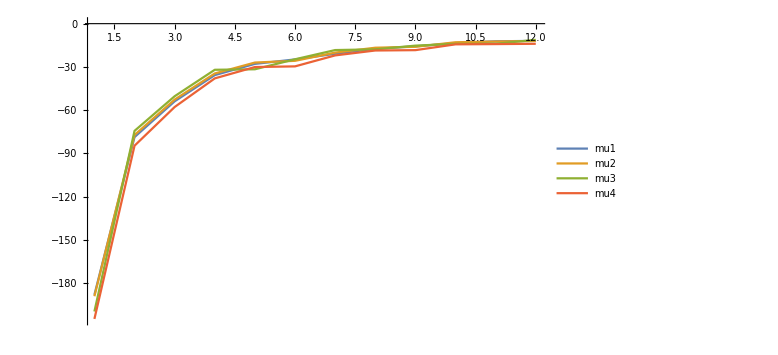
{-Graphics-,-Graphics-}

```mathematica
{dsar["he","rk",All,"d0","ndeevs"][ListLinePlot[#,ImageSize->Large,PlotRange->All]&],
dsar["he","rk",All,"d0","ndeevs",Values][ListLinePlot[#,ImageSize->Large,PlotRange->All]&]}
```

```mathematica
dsar["he","rk",All,"d0","ndeevs"][Grid[#//Values//Values,Frame->All]&]
```

-187.945 meV | -78.6243 meV | -53.8285 meV | -35.6655 meV | -27.8798 meV | -24.7921 meV | -20.8681 meV | -17.3962 meV | -15.7331 meV | -13.4945 meV | -12.2242 meV | -11.9369 meV
-188.952 meV | -77.1738 meV | -52.6492 meV | -34.5349 meV | -26.9608 meV | -25.7621 meV | -20.06 meV | -16.68 meV | -16.0407 meV | -12.8972 meV | -12.3978 meV | -11.986 meV
-199.515 meV | -74.3196 meV | -50.3129 meV | -31.9724 meV | -31.6225 meV | -24.6973 meV | -18.3087 meV | -17.8125 meV | -15.2383 meV | -13.9915 meV | -13.905 meV | -11.2174 meV
-204.666 meV | -84.604 meV | -57.7771 meV | -37.9366 meV | -30.0635 meV | -29.6125 meV | -21.9998 meV | -18.6052 meV | -18.3629 meV | -14.3328 meV | -14.1592 meV | -13.9545 meV

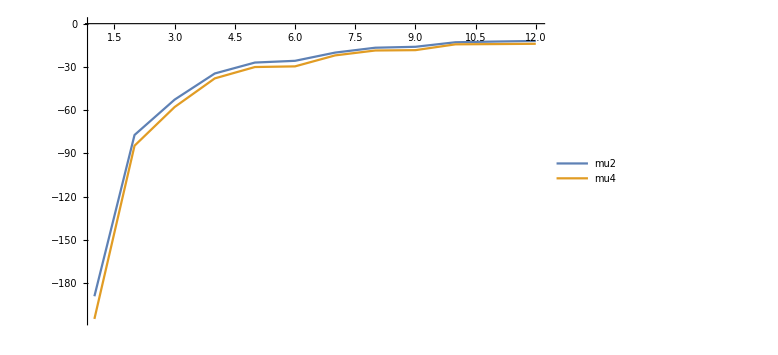

```mathematica
dsar["he","rk",{"mu2","mu4"},"d0","ndeevs",Values][ListLinePlot[#,ImageSize->Large,PlotRange->All]&]
```

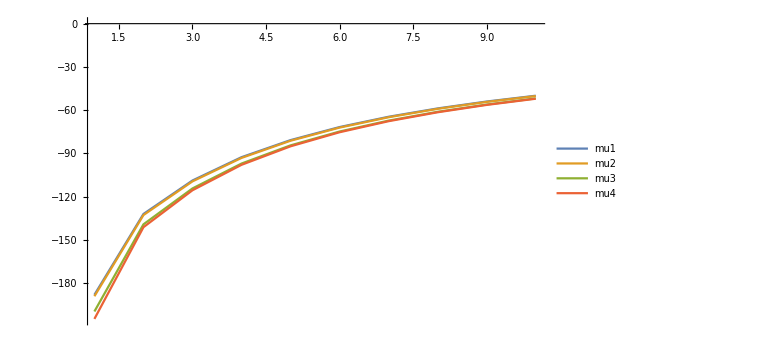
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{dsar["he","rk",All,All,"ndeevs","i1"][ListLinePlot[#,ImageSize->Large,PlotRange->All]&],
dsar["he","rk",All,All,"ndeevs","i1"][ListLinePlot[#//Values,ImageSize->Large,PlotRange->All]&],
dsar["he","rk",All,All,"ndeevs","i1"][ListLinePlot[Values/@#,ImageSize->Large,PlotRange->All]&]}
```

```mathematica
{dsar["he","rk",All,"d0","ndeevs",Values][ListLinePlot[#,ImageSize->Large,PlotRange->All]&],dsar["he","rk",All,All,"ndeevs","i1"][ListLinePlot[Values/@#,ImageSize->Large,PlotRange->All]&]}
```

{-Graphics-,-Graphics-}

```mathematica
Flatten[Map[Values,MapIndexed[{Values[#1],#2}&,Normal[dsar["he",All,All,"d0","ndeevs"]],{2}],{0,1}],1]
```

{{{-187.945 meV,-78.6243 meV,-53.8285 meV,-35.6655 meV,-27.8798 meV,-24.7921 meV,-20.8681 meV,-17.3962 meV,-15.7331 meV,-13.4945 meV,-12.2242 meV,-11.9369 meV},{Key[rk],Key[mu1]}},{{-188.952 meV,-77.1738 meV,-52.6492 meV,-34.5349 meV,-26.9608 meV,-25.7621 meV,-20.06 meV,-16.68 meV,-16.0407 meV,-12.8972 meV,-12.3978 meV,-11.986 meV},{Key[rk],Key[mu2]}},{{-199.515 meV,-74.3196 meV,-50.3129 meV,-31.9724 meV,-31.6225 meV,-24.6973 meV,-18.3087 meV,-17.8125 meV,-15.2383 meV,-13.9915 meV,-13.905 meV,-11.2174 meV},{Key[rk],Key[mu3]}},{{-204.666 meV,-84.604 meV,-57.7771 meV,-37.9366 meV,-30.0635 meV,-29.6125 meV,-21.9998 meV,-18.6052 meV,-18.3629 meV,-14.3328 meV,-14.1592 meV,-13.9545 meV},{Key[rk],Key[mu4]}},{{-468.399 meV,-96.838 meV,-71.7839 meV,-39.9116 meV,-33.4691 meV,-25.8132 meV,-22.5546 meV,-19.9189 meV,-15.9443 meV,-14.4489 meV,-13.0685 meV,-12.4164 meV},{Key[c],Key[mu1]}},{{-469.935 meV,-94.4295 meV,-70.2242 meV,-38.5103 meV,-32.3757 meV,-26.8789 meV,-21.6201 meV,-19.1498 meV,-16.2605 meV,-13.7112 meV,-12.6645 meV,-12.6075 meV},{Key[c],Key[mu2]}},{{-505.523 meV,-89.5598 meV,-68.1519 meV,-34.9982 meV,-33.8552 meV,-29.9168 meV,-19.1281 meV,-18.6074 meV,-17.2368 meV,-14.5429 meV,-14.3477 meV,-11.8758 meV},{Key[c],Key[mu3]}},{{-538.714 meV,-105.957 meV,-79.0189 meV,-42.8678 meV,-36.1179 meV,-31.7035 meV,-23.9458 meV,-21.2393 meV,-18.9281 meV,-15.2761 meV,-14.6495 meV,-14.469 meV},{Key[c],Key[mu4]}}}

```mathematica
Flatten[Map[Values,MapIndexed[{Values[#1],StringJoin[Level[#2,{-1}]]}&,Normal[dsar["he",All,All,"d0","ndeevs"]],{2}],{0,1}],1]//Transpose
```

{{{-187.945 meV,-78.6243 meV,-53.8285 meV,-35.6655 meV,-27.8798 meV,-24.7921 meV,-20.8681 meV,-17.3962 meV,-15.7331 meV,-13.4945 meV,-12.2242 meV,-11.9369 meV},{-188.952 meV,-77.1738 meV,-52.6492 meV,-34.5349 meV,-26.9608 meV,-25.7621 meV,-20.06 meV,-16.68 meV,-16.0407 meV,-12.8972 meV,-12.3978 meV,-11.986 meV},{-199.515 meV,-74.3196 meV,-50.3129 meV,-31.9724 meV,-31.6225 meV,-24.6973 meV,-18.3087 meV,-17.8125 meV,-15.2383 meV,-13.9915 meV,-13.905 meV,-11.2174 meV},{-204.666 meV,-84.604 meV,-57.7771 meV,-37.9366 meV,-30.0635 meV,-29.6125 meV,-21.9998 meV,-18.6052 meV,-18.3629 meV,-14.3328 meV,-14.1592 meV,-13.9545 meV},{-468.399 meV,-96.838 meV,-71.7839 meV,-39.9116 meV,-33.4691 meV,-25.8132 meV,-22.5546 meV,-19.9189 meV,-15.9443 meV,-14.4489 meV,-13.0685 meV,-12.4164 meV},{-469.935 meV,-94.4295 meV,-70.2242 meV,-38.5103 meV,-32.3757 meV,-26.8789 meV,-21.6201 meV,-19.1498 meV,-16.2605 meV,-13.7112 meV,-12.6645 meV,-12.6075 meV},{-505.523 meV,-89.5598 meV,-68.1519 meV,-34.9982 meV,-33.8552 meV,-29.9168 meV,-19.1281 meV,-18.6074 meV,-17.2368 meV,-14.5429 meV,-14.3477 meV,-11.8758 meV},{-538.714 meV,-105.957 meV,-79.0189 meV,-42.8678 meV,-36.1179 meV,-31.7035 meV,-23.9458 meV,-21.2393 meV,-18.9281 meV,-15.2761 meV,-14.6495 meV,-14.469 meV}},{rkmu1,rkmu2,rkmu3,rkmu4,cmu1,cmu2,cmu3,cmu4}}

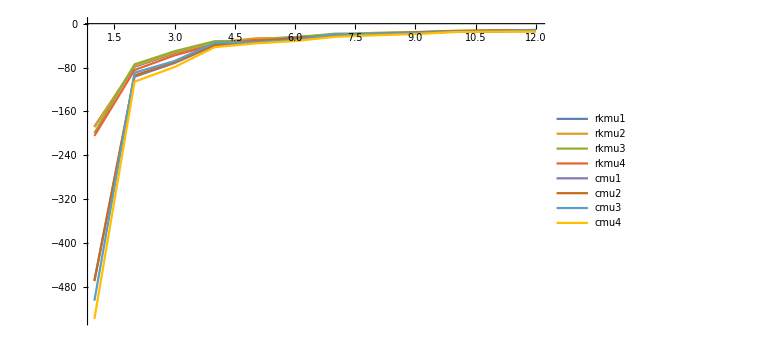

```mathematica
ListLinePlot[(* Want to make a list plot *)
#[[1]], (* The data set(s) are the first list element from the transposed, flattened, mapped, mapindexed, Dataset. *)
ImageSize->Large,PlotRange->All,PlotLegends->#[[2]]
]&[
Flatten[
Map[
Values,
MapIndexed[
{
Values[#1],
StringJoin[Level[#2,{-1}]]
}&,
Normal[dsar["he",All,All,"d0","ndeevs"]],
{2}
],
{0,1}
],
1
]//Transpose
]
```

```mathematica
Normal[dsar["he",All,All,"d0","ndeevs"]]//ArrayDepth
```

3

```mathematica
Clear[arbllp]
arbllp[keys_]:=Module[
{
nds=Normal[dsar@@keys],
arde
},
arde=ArrayDepth[nds];
ListLinePlot[(* Want to make a list plot *)
#[[1]], (* The data set(s) are the first list element from the transposed, flattened, mapped, mapindexed, Dataset. *)
ImageSize->Large,PlotRange->All,PlotLegends->#[[2]]
]&[
Flatten[
Map[
Values,
MapIndexed[
{
Values[#1],
StringJoin[Level[#2,{-1}]]
}&,
nds,
{arde-1}
],
{0,1}
],
1
]//Transpose
]
]
```

```mathematica
arbllp[{"he",All,All,"d0","ndeevs"}]
```

-Graphics-

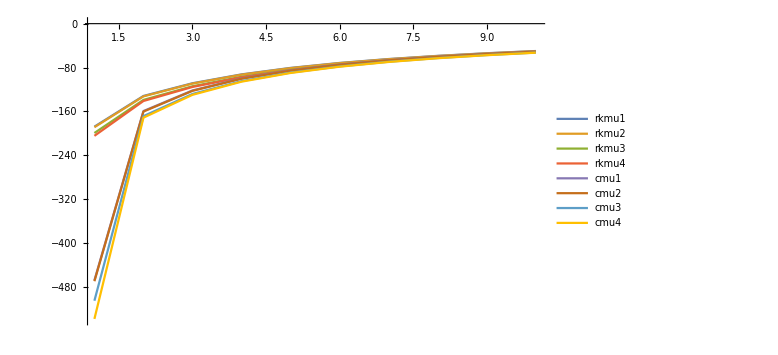

```mathematica
arbllp[{"he",All,All,All,"ndeevs","i1"}]
```

Maybe instead of dealing with the still-nested-association output of mapindexed, use that to build new arrays w/in a module

```mathematica
arbllp2[keys_]:=Module[
{ds=Normal[dsar@@keys],
data={},legends={},xaxis={}},
MapIndexed[
{
data=Append[data,Values[#1]],
legends=Append[legends,StringJoin[Level[#2,{-1}]]],
xaxis=Keys[#1]
}&,
ds,
{2}
];
ListLinePlot[data,PlotTheme->"Detailed",ImageSize->Large,PlotRange->All,PlotLegends->legends]
]
```

#### MapIndexed with associations and datasets?

```mathematica
MapIndexed[
f,
dsar[All,All,All,All,{"ndeevs","fox"}],
3
]//Normal
```

<|fs→f[<|rk→1|>,{Key[fs]}],ss→f[1],hs→1,he→f[<|rk→1,c→f[<|mu1→f[<|d0→<|ndeevs→<|i1→-468.399 meV,i2→-96.838 meV,i3→-71.7839 meV,i4→-39.9116 meV,i5→-33.4691 meV,i6→-25.8132 meV,i7→-22.5546 meV,i8→-19.9189 meV,i9→-15.9443 meV,i10→-14.4489 meV,i11→-13.0685 meV,i12→-12.4164 meV|>,fox→{{0.,2.86783×10^-22 (Association[Table[ToString[ii]→Association[Table[ToString[jj]→If[j≥i,#1⟦i,j⟧,#1⟦j,i⟧],{j,12}]],{i,12}]]&),8,5.56304×10^-8 (Association[Table[ToString[ii]→Association[Table[ToString[jj]→If[j≥i,#1⟦i,j⟧,#1⟦j,i⟧],{j,12}]],{i,12}]]&),0.0110917 (Association[Table[ToString[ii]→Association[Table[ToString[jj]→If[j≥i,#1⟦i,j⟧,#1⟦j,i⟧],{j,12}]],{i,12}]]&)},10,{0,0,0,0,0,0,0,0,0,0,0,0.}}|>,d1→<|ndeevs→<|1|>,1|>,6,d8→1,d9→<|ndeevs→<|i1→-50.838 meV,i2→-37.483 meV,i3→-28.6837 meV,i4→-22.569 meV,i5→-18.5713 meV,i6→-18.2422 meV,i7→-14.8668 meV,i8→-13.5723 meV,i9→-12.291 meV,i10→-10.7373 meV,i11→-10.4213 meV,i12→-9.64138 meV|>,fox→{1}|>|>,1],3|>,1]|>,{Key[he]}]|>
 |  |  |  |

```mathematica
MapIndexed[
({#1,#2}//TableForm)&,
dsar["he",All,All,"d0","ndeevs","i1"],
1
]//Normal
```

<|rk→<|mu1→-187.945 meV,mu2→-188.952 meV,mu3→-199.515 meV,mu4→-204.666 meV|>
Key[rk],c→<|mu1→-468.399 meV,mu2→-469.935 meV,mu3→-505.523 meV,mu4→-538.714 meV|>
Key[c]|>

```mathematica
MapIndexed[
({#1,#2}//TableForm)&,
dsar["he",All,All,"d0","ndeevs","i1"],
2
]//Normal
```

<|rk→<|mu1→-187.945 meV | 
Key[rk] | Key[mu1],mu2→-188.952 meV | 
Key[rk] | Key[mu2],mu3→-199.515 meV | 
Key[rk] | Key[mu3],mu4→-204.666 meV | 
Key[rk] | Key[mu4]|>
Key[rk],c→<|mu1→-468.399 meV | 
Key[c] | Key[mu1],mu2→-469.935 meV | 
Key[c] | Key[mu2],mu3→-505.523 meV | 
Key[c] | Key[mu3],mu4→-538.714 meV | 
Key[c] | Key[mu4]|>
Key[c]|>

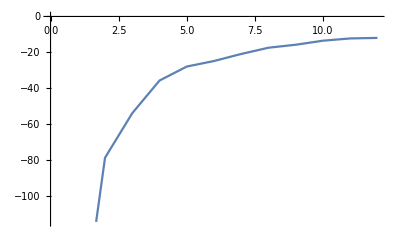
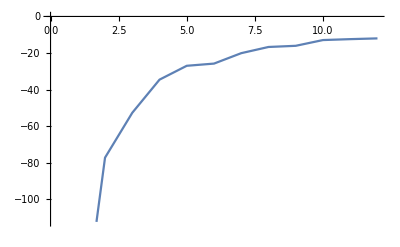
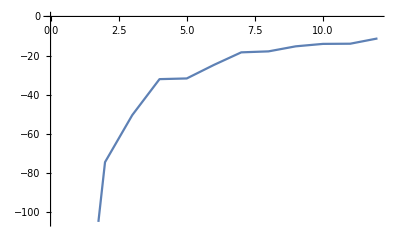
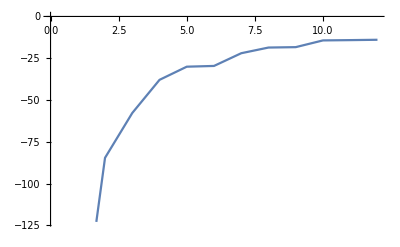
<|fs→<|rk→<|mu1→<|d0→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>|>,mu2→<|d0→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>|>,mu3→<|d0→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>|>,mu4→<|d0→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>|>|>|>,ss→<|rk→<|mu1→<|d0→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>|>,mu2→<|d0→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>|>,mu3→<|d0→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>|>,mu4→<|d0→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>|>|>|>,hs→<|rk→<|mu1→<|d0→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>|>,mu2→<|d0→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>|>,mu3→<|d0→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>|>,mu4→<|d0→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>|>|>|>,he→<|rk→<|mu1→<|d0→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d1→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d2→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d3→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d4→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d5→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d6→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d7→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d8→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d9→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>|>,mu2→<|d0→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d1→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d2→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d3→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d4→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d5→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d6→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d7→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d8→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d9→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>|>,mu3→<|d0→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d1→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d2→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d3→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d4→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d5→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d6→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d7→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d8→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d9→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>|>,mu4→<|d0→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d1→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d2→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d3→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d4→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d5→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d6→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d7→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d8→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d9→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>|>|>,c→<|mu1→<|d0→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d1→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d2→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d3→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d4→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d5→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d6→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d7→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d8→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d9→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>|>,mu2→<|d0→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d1→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d2→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d3→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d4→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d5→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d6→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d7→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d8→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d9→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>|>,mu3→<|d0→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d1→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d2→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d3→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d4→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d5→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d6→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d7→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d8→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d9→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>|>,mu4→<|d0→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d1→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d2→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d3→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d4→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d5→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d6→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d7→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d8→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>,d9→<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>|>|>|>|>

```mathematica
MapIndexed[
dsar["he",#2[[2]],#2[[3]],"d0","ndeevs",Values][ListLinePlot]&,
dsar[All,All,All,All,"ndeevs"],
{-2}
]//Normal
```

This keeps the association structure and makes a ListLinePlot for each <|i1->,i2->....|>

```mathematica
MapIndexed[
ListLinePlot[#1]&,
dsar[All,All,All,All,"ndeevs"],
{4}
]//Normal
```

<|fs→<|rk→<|mu1→<|d0→-Graphics-|>,mu2→<|d0→-Graphics-|>,mu3→<|d0→-Graphics-|>,mu4→<|d0→-Graphics-|>|>|>,ss→<|rk→<|mu1→<|d0→-Graphics-|>,mu2→<|d0→-Graphics-|>,mu3→<|d0→-Graphics-|>,mu4→<|d0→-Graphics-|>|>|>,hs→<|rk→<|mu1→<|d0→-Graphics-|>,mu2→<|d0→-Graphics-|>,mu3→<|d0→-Graphics-|>,mu4→<|d0→-Graphics-|>|>|>,he→<|rk→<|mu1→<|d0→-Graphics-,d1→-Graphics-,d2→-Graphics-,d3→-Graphics-,d4→-Graphics-,d5→-Graphics-,d6→-Graphics-,d7→-Graphics-,d8→-Graphics-,d9→-Graphics-|>,mu2→<|d0→-Graphics-,d1→-Graphics-,d2→-Graphics-,d3→-Graphics-,d4→-Graphics-,d5→-Graphics-,d6→-Graphics-,d7→-Graphics-,d8→-Graphics-,d9→-Graphics-|>,mu3→<|d0→-Graphics-,d1→-Graphics-,d2→-Graphics-,d3→-Graphics-,d4→-Graphics-,d5→-Graphics-,d6→-Graphics-,d7→-Graphics-,d8→-Graphics-,d9→-Graphics-|>,mu4→<|d0→-Graphics-,d1→-Graphics-,d2→-Graphics-,d3→-Graphics-,d4→-Graphics-,d5→-Graphics-,d6→-Graphics-,d7→-Graphics-,d8→-Graphics-,d9→-Graphics-|>|>,c→<|mu1→<|d0→-Graphics-,d1→-Graphics-,d2→-Graphics-,d3→-Graphics-,d4→-Graphics-,d5→-Graphics-,d6→-Graphics-,d7→-Graphics-,d8→-Graphics-,d9→-Graphics-|>,mu2→<|d0→-Graphics-,d1→-Graphics-,d2→-Graphics-,d3→-Graphics-,d4→-Graphics-,d5→-Graphics-,d6→-Graphics-,d7→-Graphics-,d8→-Graphics-,d9→-Graphics-|>,mu3→<|d0→-Graphics-,d1→-Graphics-,d2→-Graphics-,d3→-Graphics-,d4→-Graphics-,d5→-Graphics-,d6→-Graphics-,d7→-Graphics-,d8→-Graphics-,d9→-Graphics-|>,mu4→<|d0→-Graphics-,d1→-Graphics-,d2→-Graphics-,d3→-Graphics-,d4→-Graphics-,d5→-Graphics-,d6→-Graphics-,d7→-Graphics-,d8→-Graphics-,d9→-Graphics-|>|>|>|>

#### Try to generalize

```mathematica
Keys[allres]
```

{fs,ss,hs,he}

```mathematica
Map[
Keys,
allres,
1]
```

<|fs→{rk},ss→{rk},hs→{rk},he→{rk,c}|>

```mathematica
Map[
Keys,
allres,
2]
```

<|fs→{rk},ss→{rk},hs→{rk},he→{rk,c}|>

```mathematica
Map[
Keys,
allres,
3]
```

<|fs→{rk},ss→{rk},hs→{rk},he→{rk,c}|>

```mathematica
Map[
Keys,
allres,
{3,0}]
```

$Aborted[]

```mathematica
f@@{1,2,3,4}
```

f[1,2,3,4]

```mathematica
Map[
Keys,
allres,
{1,3}]
```

<|fs→{rk},ss→{rk},hs→{rk},he→{rk,c}|>

```mathematica
pfds[spec_,quant_,ij_]:=Module[
{sds,qsds,iqsds},
sds=dsar@@spec;
qsds=sds[quant];
iqsds=qsds@@ij;
{sds,qsds,iqsds,
iqsds[ListLinePlot]}
]
```

```mathematica
pfds[{"he","rk",All,All},"ndeevs",{All}]
```

{Dataset[<>],Failure[…],Failure[…][All],Failure[…][All][ListLinePlot]}

## Two functions that seem to work:

```mathematica
arbllp[keys_]:=Module[
{
nds=Normal[dsar@@keys],
arde
},
arde=ArrayDepth[nds];
ListLinePlot[(* Want to make a list plot *)
#[[1]], (* The data set(s) are the first list element from the transposed, flattened, mapped, mapindexed, Dataset. *)
ImageSize->Large,PlotRange->All,PlotLegends->#[[2]]
]&[
Flatten[
Map[
Values,
MapIndexed[
{
Values[#1],
StringJoin[Level[#2,{-1}]]
}&,
nds,
{arde-1}
],
{0,1}
],
1
]//Transpose
]
]
```

```mathematica
arbllp2[keys_]:=Module[
{
env,pot,mu,di,quant,xax,title,
ds=Normal[dsar@@keys],
data={},legends={},xaxis={}
},
MapIndexed[
{
data=Append[data,Values[#1]],
legends=Append[legends,StringJoin[Level[#2,{-1}]]],
xaxis=Keys[#1]
}&,
ds,
{2}
];
title=quantleg[keys[[5]]];
xax=xleg[xaxis[[1]]];
ListLinePlot[
data,
FrameLabel->{{title,None},{xax,title}},
PlotTheme->"Detailed",ImageSize->Large,PlotRange->All,PlotLegends->legends]
]
```

```mathematica
{
arbllp2[{"he",All,All,All,"ndeevs","i1"}],
arbllp2[{All,"rk",All,"d0","ndeevs"}]
}
```

{-Graphics-,-Graphics-}

```mathematica
arbllp3[keys_]:=Module[
{
env,pot,mu,di,quant,xax,title,legform,
ds=Normal[dsar@@keys],
data={},legends={},xaxis={}
},
MapIndexed[
{
data=Append[data,Values[#1]],
legends=Append[legends,#2],
xaxis=Keys[#1]
}&,
ds,
{2}
];
title=quantleg[keys[[5]]];
xax=xleg[xaxis[[1]]];
ListLinePlot[
data,
FrameLabel->{{title,None},{xax,title}},
PlotTheme->"Detailed",ImageSize->Large,PlotRange->All,PlotLegends->legends]
]
```

## Different angle for getting labels... KeyMap?

```mathematica
dsar["he","rk",All,All,"ndeevs","i1"][ListLinePlot[Values/@#,ImageSize->Large,PlotRange->All]&]
```

-Graphics-

```mathematica
ListLinePlot[Values/@#,ImageSize->Large,PlotRange->All]&@dsar["he","rk",All,All,"ndeevs","i1"]
```

-Graphics-

```mathematica
Map[
ListLinePlot,
dsar["he","rk",All,All,"ndeevs"]
]
```

Dataset[<>]

```mathematica
Map[
ListLinePlot,
dsar["he","rk",All,All,"ndeevs",Values]
]
```

Dataset[<>]

#### Try keeping the {x,y} pairs in one assoc

```mathematica
gsevsdmu=dsar["he","rk",All,All,"ndeevs","i1"]
evsnpotmu=dsar["he","rk",All,All,"ndeevs"]
```

Dataset[<>]

Dataset[<>]

From: https://mathematica.stackexchange.com/questions/176895/convert-association-to-matrix-list

```mathematica
Normal[gsevsdmu]
Normal[KeyValueMap[f[{##}]&]@gsevsdmu]
```

<|mu1→<|d0→-187.945 meV,d1→-131.929 meV,d2→-108.715 meV,d3→-92.5572 meV,d4→-80.7184 meV,d5→-71.6748 meV,d6→-64.5367 meV,d7→-58.7543 meV,d8→-53.9709 meV,d9→-49.9448 meV|>,mu2→<|d0→-188.952 meV,d1→-132.686 meV,d2→-109.325 meV,d3→-93.062 meV,d4→-81.1457 meV,d5→-72.0432 meV,d6→-64.8592 meV,d7→-59.0402 meV,d8→-54.2269 meV,d9→-50.1761 meV|>,mu3→<|d0→-199.515 meV,d1→-139.112 meV,d2→-114.222 meV,d3→-96.9689 meV,d4→-84.3687 meV,d5→-74.7695 meV,d6→-67.21 meV,d7→-61.0984 meV,d8→-56.0512 meV,d9→-51.8097 meV|>,mu4→<|d0→-204.666 meV,d1→-141.095 meV,d2→-115.482 meV,d3→-97.8429 meV,d4→-85.0119 meV,d5→-75.2633 meV,d6→-67.6013 meV,d7→-61.4162 meV,d8→-56.3146 meV,d9→-52.0316 meV|>|>

{f[{mu1,<|d0→-187.945 meV,d1→-131.929 meV,d2→-108.715 meV,d3→-92.5572 meV,d4→-80.7184 meV,d5→-71.6748 meV,d6→-64.5367 meV,d7→-58.7543 meV,d8→-53.9709 meV,d9→-49.9448 meV|>}],f[{mu2,<|d0→-188.952 meV,d1→-132.686 meV,d2→-109.325 meV,d3→-93.062 meV,d4→-81.1457 meV,d5→-72.0432 meV,d6→-64.8592 meV,d7→-59.0402 meV,d8→-54.2269 meV,d9→-50.1761 meV|>}],f[{mu3,<|d0→-199.515 meV,d1→-139.112 meV,d2→-114.222 meV,d3→-96.9689 meV,d4→-84.3687 meV,d5→-74.7695 meV,d6→-67.21 meV,d7→-61.0984 meV,d8→-56.0512 meV,d9→-51.8097 meV|>}],f[{mu4,<|d0→-204.666 meV,d1→-141.095 meV,d2→-115.482 meV,d3→-97.8429 meV,d4→-85.0119 meV,d5→-75.2633 meV,d6→-67.6013 meV,d7→-61.4162 meV,d8→-56.3146 meV,d9→-52.0316 meV|>}]}

```mathematica
?KeyValueMap
```

KeyValueMap[f,<|key_1→val_1,key_2→val_2,…|>] gives the list {f[key_1,val_1],f[key_2,val_2],…}.
KeyValueMap[f] represents an operator form of KeyValueMap that can be applied to an expression.

```mathematica
Normal[KeyValueMap[f[##]&]/@gsevsdmu]
Normal[KeyValueMap[Flatten[{##}]&]/@gsevsdmu]
```

<|mu1→{f[d0,-187.945 meV],f[d1,-131.929 meV],f[d2,-108.715 meV],f[d3,-92.5572 meV],f[d4,-80.7184 meV],f[d5,-71.6748 meV],f[d6,-64.5367 meV],f[d7,-58.7543 meV],f[d8,-53.9709 meV],f[d9,-49.9448 meV]},mu2→{f[d0,-188.952 meV],f[d1,-132.686 meV],f[d2,-109.325 meV],f[d3,-93.062 meV],f[d4,-81.1457 meV],f[d5,-72.0432 meV],f[d6,-64.8592 meV],f[d7,-59.0402 meV],f[d8,-54.2269 meV],f[d9,-50.1761 meV]},mu3→{f[d0,-199.515 meV],f[d1,-139.112 meV],f[d2,-114.222 meV],f[d3,-96.9689 meV],f[d4,-84.3687 meV],f[d5,-74.7695 meV],f[d6,-67.21 meV],f[d7,-61.0984 meV],f[d8,-56.0512 meV],f[d9,-51.8097 meV]},mu4→{f[d0,-204.666 meV],f[d1,-141.095 meV],f[d2,-115.482 meV],f[d3,-97.8429 meV],f[d4,-85.0119 meV],f[d5,-75.2633 meV],f[d6,-67.6013 meV],f[d7,-61.4162 meV],f[d8,-56.3146 meV],f[d9,-52.0316 meV]}|>

<|mu1→{{d0,-187.945 meV},{d1,-131.929 meV},{d2,-108.715 meV},{d3,-92.5572 meV},{d4,-80.7184 meV},{d5,-71.6748 meV},{d6,-64.5367 meV},{d7,-58.7543 meV},{d8,-53.9709 meV},{d9,-49.9448 meV}},mu2→{{d0,-188.952 meV},{d1,-132.686 meV},{d2,-109.325 meV},{d3,-93.062 meV},{d4,-81.1457 meV},{d5,-72.0432 meV},{d6,-64.8592 meV},{d7,-59.0402 meV},{d8,-54.2269 meV},{d9,-50.1761 meV}},mu3→{{d0,-199.515 meV},{d1,-139.112 meV},{d2,-114.222 meV},{d3,-96.9689 meV},{d4,-84.3687 meV},{d5,-74.7695 meV},{d6,-67.21 meV},{d7,-61.0984 meV},{d8,-56.0512 meV},{d9,-51.8097 meV}},mu4→{{d0,-204.666 meV},{d1,-141.095 meV},{d2,-115.482 meV},{d3,-97.8429 meV},{d4,-85.0119 meV},{d5,-75.2633 meV},{d6,-67.6013 meV},{d7,-61.4162 meV},{d8,-56.3146 meV},{d9,-52.0316 meV}}|>

!!!! This applies one function to the keys and another to the values!

```mathematica
Normal[KeyValueMap[{f[#1],g[#2]}&]/@gsevsdmu]
```

<|mu1→{{f[d0],g[-187.945 meV]},{f[d1],g[-131.929 meV]},{f[d2],g[-108.715 meV]},{f[d3],g[-92.5572 meV]},{f[d4],g[-80.7184 meV]},{f[d5],g[-71.6748 meV]},{f[d6],g[-64.5367 meV]},{f[d7],g[-58.7543 meV]},{f[d8],g[-53.9709 meV]},{f[d9],g[-49.9448 meV]}},mu2→{{f[d0],g[-188.952 meV]},{f[d1],g[-132.686 meV]},{f[d2],g[-109.325 meV]},{f[d3],g[-93.062 meV]},{f[d4],g[-81.1457 meV]},{f[d5],g[-72.0432 meV]},{f[d6],g[-64.8592 meV]},{f[d7],g[-59.0402 meV]},{f[d8],g[-54.2269 meV]},{f[d9],g[-50.1761 meV]}},mu3→{{f[d0],g[-199.515 meV]},{f[d1],g[-139.112 meV]},{f[d2],g[-114.222 meV]},{f[d3],g[-96.9689 meV]},{f[d4],g[-84.3687 meV]},{f[d5],g[-74.7695 meV]},{f[d6],g[-67.21 meV]},{f[d7],g[-61.0984 meV]},{f[d8],g[-56.0512 meV]},{f[d9],g[-51.8097 meV]}},mu4→{{f[d0],g[-204.666 meV]},{f[d1],g[-141.095 meV]},{f[d2],g[-115.482 meV]},{f[d3],g[-97.8429 meV]},{f[d4],g[-85.0119 meV]},{f[d5],g[-75.2633 meV]},{f[d6],g[-67.6013 meV]},{f[d7],g[-61.4162 meV]},{f[d8],g[-56.3146 meV]},{f[d9],g[-52.0316 meV]}}|>

```mathematica
Normal[Map[
KeyValueMap[{f[#1],g[#2]}&],
gsevsdmu,
{-3}
]
]
```

<|mu1→{{f[d0],g[-187.945 meV]},{f[d1],g[-131.929 meV]},{f[d2],g[-108.715 meV]},{f[d3],g[-92.5572 meV]},{f[d4],g[-80.7184 meV]},{f[d5],g[-71.6748 meV]},{f[d6],g[-64.5367 meV]},{f[d7],g[-58.7543 meV]},{f[d8],g[-53.9709 meV]},{f[d9],g[-49.9448 meV]}},mu2→{{f[d0],g[-188.952 meV]},{f[d1],g[-132.686 meV]},{f[d2],g[-109.325 meV]},{f[d3],g[-93.062 meV]},{f[d4],g[-81.1457 meV]},{f[d5],g[-72.0432 meV]},{f[d6],g[-64.8592 meV]},{f[d7],g[-59.0402 meV]},{f[d8],g[-54.2269 meV]},{f[d9],g[-50.1761 meV]}},mu3→{{f[d0],g[-199.515 meV]},{f[d1],g[-139.112 meV]},{f[d2],g[-114.222 meV]},{f[d3],g[-96.9689 meV]},{f[d4],g[-84.3687 meV]},{f[d5],g[-74.7695 meV]},{f[d6],g[-67.21 meV]},{f[d7],g[-61.0984 meV]},{f[d8],g[-56.0512 meV]},{f[d9],g[-51.8097 meV]}},mu4→{{f[d0],g[-204.666 meV]},{f[d1],g[-141.095 meV]},{f[d2],g[-115.482 meV]},{f[d3],g[-97.8429 meV]},{f[d4],g[-85.0119 meV]},{f[d5],g[-75.2633 meV]},{f[d6],g[-67.6013 meV]},{f[d7],g[-61.4162 meV]},{f[d8],g[-56.3146 meV]},{f[d9],g[-52.0316 meV]}}|>

But for more deeply nested associations I can’t seem to get down to the right level...

```mathematica
Normal[Map[
KeyValueMap[{f[#1],g[#2]}&],
evsnpotmu,
{-3}
]
]
```

<|mu1→<|d0→{{f[i1],g[-187.945 meV]},{f[i2],g[-78.6243 meV]},{f[i3],g[-53.8285 meV]},{f[i4],g[-35.6655 meV]},{f[i5],g[-27.8798 meV]},{f[i6],g[-24.7921 meV]},{f[i7],g[-20.8681 meV]},{f[i8],g[-17.3962 meV]},{f[i9],g[-15.7331 meV]},{f[i10],g[-13.4945 meV]},{f[i11],g[-12.2242 meV]},{f[i12],g[-11.9369 meV]}},d1→{{f[i1],g[-131.929 meV]},{f[i2],g[-70.5383 meV]},{f[i3],g[-47.4805 meV]},{f[i4],g[-33.5398 meV]},{f[i5],g[-25.6645 meV]},{f[i6],g[-24.2378 meV]},{f[i7],g[-19.9884 meV]},{f[i8],g[-16.2711 meV]},{f[i9],g[-15.6196 meV]},{f[i10],g[-13.0223 meV]},{f[i11],g[-12.1144 meV]},{f[i12],g[-11.4654 meV]}},d2→{{f[i1],g[-108.715 meV]},{f[i2],g[-63.7905 meV]},{f[i3],g[-43.7299 meV]},{f[i4],g[-31.6555 meV]},{f[i5],g[-24.3166 meV]},{f[i6],g[-23.5586 meV]},{f[i7],g[-19.198 meV]},{f[i8],g[-15.5542 meV]},{f[i9],g[-15.4521 meV]},{f[i10],g[-12.626 meV]},{f[i11],g[-11.9764 meV]},{f[i12],g[-11.1876 meV]}},d3→{{f[i1],g[-92.5572 meV]},{f[i2],g[-57.8579 meV]},{f[i3],g[-40.5116 meV]},{f[i4],g[-29.878 meV]},{f[i5],g[-23.1169 meV]},{f[i6],g[-22.786 meV]},{f[i7],g[-18.4331 meV]},{f[i8],g[-15.2309 meV]},{f[i9],g[-14.8931 meV]},{f[i10],g[-12.2623 meV]},{f[i11],g[-11.8118 meV]},{f[i12],g[-10.9325 meV]}},d4→{{f[i1],g[-80.7184 meV]},{f[i2],g[-52.8394 meV]},{f[i3],g[-37.7461 meV]},{f[i4],g[-28.2673 meV]},{f[i5],g[-22.0483 meV]},{f[i6],g[-21.9893 meV]},{f[i7],g[-17.7154 meV]},{f[i8],g[-14.9728 meV]},{f[i9],g[-14.294 meV]},{f[i10],g[-11.9298 meV]},{f[i11],g[-11.6326 meV]},{f[i12],g[-10.686 meV]}},d5→{{f[i1],g[-71.6748 meV]},{f[i2],g[-48.6081 meV]},{f[i3],g[-35.353 meV]},{f[i4],g[-26.8213 meV]},{f[i5],g[-21.2045 meV]},{f[i6],g[-21.0926 meV]},{f[i7],g[-17.0436 meV]},{f[i8],g[-14.6911 meV]},{f[i9],g[-13.7617 meV]},{f[i10],g[-11.6162 meV]},{f[i11],g[-11.4456 meV]},{f[i12],g[-10.4475 meV]}},d6→{{f[i1],g[-64.5367 meV]},{f[i2],g[-45.0164 meV]},{f[i3],g[-33.265 meV]},{f[i4],g[-25.5234 meV]},{f[i5],g[-20.4493 meV]},{f[i6],g[-20.2329 meV]},{f[i7],g[-16.4129 meV]},{f[i8],g[-14.3962 meV]},{f[i9],g[-13.2963 meV]},{f[i10],g[-11.309 meV]},{f[i11],g[-11.2552 meV]},{f[i12],g[-10.2178 meV]}},d7→{{f[i1],g[-58.7543 meV]},{f[i2],g[-41.9383 meV]},{f[i3],g[-31.4279 meV]},{f[i4],g[-24.3551 meV]},{f[i5],g[-19.7315 meV]},{f[i6],g[-19.4538 meV]},{f[i7],g[-15.8197 meV]},{f[i8],g[-14.0956 meV]},{f[i9],g[-12.8909 meV]},{f[i10],g[-11.0675 meV]},{f[i11],g[-10.9989 meV]},{f[i12],g[-10.0021 meV]}},d8→{{f[i1],g[-53.9709 meV]},{f[i2],g[-39.2742 meV]},{f[i3],g[-29.7987 meV]},{f[i4],g[-23.2999 meV]},{f[i5],g[-19.0537 meV]},{f[i6],g[-18.742 meV]},{f[i7],g[-15.2629 meV]},{f[i8],g[-13.7947 meV]},{f[i9],g[-12.5346 meV]},{f[i10],g[-10.877 meV]},{f[i11],g[-10.6761 meV]},{f[i12],g[-9.79009 meV]}},d9→{{f[i1],g[-49.9448 meV]},{f[i2],g[-36.947 meV]},{f[i3],g[-28.3434 meV]},{f[i4],g[-22.3431 meV]},{f[i5],g[-18.4161 meV]},{f[i6],g[-18.0861 meV]},{f[i7],g[-14.7429 meV]},{f[i8],g[-13.4972 meV]},{f[i9],g[-12.2156 meV]},{f[i10],g[-10.6903 meV]},{f[i11],g[-10.3364 meV]},{f[i12],g[-9.59145 meV]}}|>,mu2→<|d0→{{f[i1],g[-188.952 meV]},{f[i2],g[-77.1738 meV]},{f[i3],g[-52.6492 meV]},{f[i4],g[-34.5349 meV]},{f[i5],g[-26.9608 meV]},{f[i6],g[-25.7621 meV]},{f[i7],g[-20.06 meV]},{f[i8],g[-16.68 meV]},{f[i9],g[-16.0407 meV]},{f[i10],g[-12.8972 meV]},{f[i11],g[-12.3978 meV]},{f[i12],g[-11.986 meV]}},d1→{{f[i1],g[-132.686 meV]},{f[i2],g[-69.4568 meV]},{f[i3],g[-46.4455 meV]},{f[i4],g[-32.5348 meV]},{f[i5],g[-25.1576 meV]},{f[i6],g[-24.8136 meV]},{f[i7],g[-19.2385 meV]},{f[i8],g[-15.9226 meV]},{f[i9],g[-15.5574 meV]},{f[i10],g[-12.4911 meV]},{f[i11],g[-12.2805 meV]},{f[i12],g[-11.7357 meV]}},d2→{{f[i1],g[-109.325 meV]},{f[i2],g[-62.9415 meV]},{f[i3],g[-42.8076 meV]},{f[i4],g[-30.7466 meV]},{f[i5],g[-24.4225 meV]},{f[i6],g[-23.5226 meV]},{f[i7],g[-18.4893 meV]},{f[i8],g[-15.7484 meV]},{f[i9],g[-14.8616 meV]},{f[i10],g[-12.1374 meV]},{f[i11],g[-12.1322 meV]},{f[i12],g[-11.5135 meV]}},d3→{{f[i1],g[-93.062 meV]},{f[i2],g[-57.1779 meV]},{f[i3],g[-39.6924 meV]},{f[i4],g[-29.0532 meV]},{f[i5],g[-23.5914 meV]},{f[i6],g[-22.3804 meV]},{f[i7],g[-17.7564 meV]},{f[i8],g[-15.5188 meV]},{f[i9],g[-14.2403 meV]},{f[i10],g[-11.9611 meV]},{f[i11],g[-11.7909 meV]},{f[i12],g[-11.2713 meV]}},d4→{{f[i1],g[-81.1457 meV]},{f[i2],g[-52.2818 meV]},{f[i3],g[-37.0163 meV]},{f[i4],g[-27.515 meV]},{f[i5],g[-22.7389 meV]},{f[i6],g[-21.3658 meV]},{f[i7],g[-17.0633 meV]},{f[i8],g[-15.2511 meV]},{f[i9],g[-13.6952 meV]},{f[i10],g[-11.7722 meV]},{f[i11],g[-11.4576 meV]},{f[i12],g[-11.0236 meV]}},d5→{{f[i1],g[-72.0432 meV]},{f[i2],g[-48.1413 meV]},{f[i3],g[-34.6991 meV]},{f[i4],g[-26.1319 meV]},{f[i5],g[-21.903 meV]},{f[i6],g[-20.4583 meV]},{f[i7],g[-16.4121 meV]},{f[i8],g[-14.9593 meV]},{f[i9],g[-13.2204 meV]},{f[i10],g[-11.5768 meV]},{f[i11],g[-11.127 meV]},{f[i12],g[-10.7815 meV]}},d6→{{f[i1],g[-64.8592 meV]},{f[i2],g[-44.6186 meV]},{f[i3],g[-32.6754 meV]},{f[i4],g[-24.8892 meV]},{f[i5],g[-21.1014 meV]},{f[i6],g[-19.6399 meV]},{f[i7],g[-15.8015 meV]},{f[i8],g[-14.6542 meV]},{f[i9],g[-12.8074 meV]},{f[i10],g[-11.3784 meV]},{f[i11],g[-10.7891 meV]},{f[i12],g[-10.5383 meV]}},d7→{{f[i1],g[-59.0402 meV]},{f[i2],g[-41.5944 meV]},{f[i3],g[-30.8928 meV]},{f[i4],g[-23.7701 meV]},{f[i5],g[-20.3419 meV]},{f[i6],g[-18.8951 meV]},{f[i7],g[-15.231 meV]},{f[i8],g[-14.3433 meV]},{f[i9],g[-12.4431 meV]},{f[i10],g[-11.1806 meV]},{f[i11],g[-10.4385 meV]},{f[i12],g[-10.3045 meV]}},d8→{{f[i1],g[-54.2269 meV]},{f[i2],g[-38.9732 meV]},{f[i3],g[-29.3101 meV]},{f[i4],g[-22.7588 meV]},{f[i5],g[-19.6266 meV]},{f[i6],g[-18.2114 meV]},{f[i7],g[-14.7012 meV]},{f[i8],g[-14.0323 meV]},{f[i9],g[-12.1149 meV]},{f[i10],g[-10.9848 meV]},{f[i11],g[-10.0807 meV]},{f[i12],g[-10.0649 meV]}},d9→{{f[i1],g[-50.1761 meV]},{f[i2],g[-36.6806 meV]},{f[i3],g[-27.895 meV]},{f[i4],g[-21.8411 meV]},{f[i5],g[-18.955 meV]},{f[i6],g[-17.5786 meV]},{f[i7],g[-14.2128 meV]},{f[i8],g[-13.7249 meV]},{f[i9],g[-11.8117 meV]},{f[i10],g[-10.7921 meV]},{f[i11],g[-9.87001 meV]},{f[i12],g[-9.68131 meV]}}|>,mu3→<|d0→{{f[i1],g[-199.515 meV]},{f[i2],g[-74.3196 meV]},{f[i3],g[-50.3129 meV]},{f[i4],g[-31.9724 meV]},{f[i5],g[-31.6225 meV]},{f[i6],g[-24.6973 meV]},{f[i7],g[-18.3087 meV]},{f[i8],g[-17.8125 meV]},{f[i9],g[-15.2383 meV]},{f[i10],g[-13.9915 meV]},{f[i11],g[-13.905 meV]},{f[i12],g[-11.2174 meV]}},d1→{{f[i1],g[-139.112 meV]},{f[i2],g[-67.3887 meV]},{f[i3],g[-44.1423 meV]},{f[i4],g[-30.9733 meV]},{f[i5],g[-29.9053 meV]},{f[i6],g[-22.6249 meV]},{f[i7],g[-18.1485 meV]},{f[i8],g[-17.0983 meV]},{f[i9],g[-14.5672 meV]},{f[i10],g[-13.7956 meV]},{f[i11],g[-13.3804 meV]},{f[i12],g[-10.8197 meV]}},d2→{{f[i1],g[-114.222 meV]},{f[i2],g[-61.3642 meV]},{f[i3],g[-40.6675 meV]},{f[i4],g[-29.8166 meV]},{f[i5],g[-28.3399 meV]},{f[i6],g[-21.4368 meV]},{f[i7],g[-17.9154 meV]},{f[i8],g[-16.4278 meV]},{f[i9],g[-14.1898 meV]},{f[i10],g[-13.5643 meV]},{f[i11],g[-12.9292 meV]},{f[i12],g[-10.4177 meV]}},d3→{{f[i1],g[-96.9689 meV]},{f[i2],g[-55.951 meV]},{f[i3],g[-37.7376 meV]},{f[i4],g[-28.5594 meV]},{f[i5],g[-26.8472 meV]},{f[i6],g[-20.4074 meV]},{f[i7],g[-17.6124 meV]},{f[i8],g[-15.7676 meV]},{f[i9],g[-13.8221 meV]},{f[i10],g[-13.3035 meV]},{f[i11],g[-12.495 meV]},{f[i12],g[-10.0593 meV]}},d4→{{f[i1],g[-84.3687 meV]},{f[i2],g[-51.3041 meV]},{f[i3],g[-35.2389 meV]},{f[i4],g[-27.3122 meV]},{f[i5],g[-25.4872 meV]},{f[i6],g[-19.4998 meV]},{f[i7],g[-17.2639 meV]},{f[i8],g[-15.1488 meV]},{f[i9],g[-13.4567 meV]},{f[i10],g[-13.0329 meV]},{f[i11],g[-12.0922 meV]},{f[i12],g[-9.92795 meV]}},d5→{{f[i1],g[-74.7695 meV]},{f[i2],g[-47.3448 meV]},{f[i3],g[-33.0818 meV]},{f[i4],g[-26.1226 meV]},{f[i5],g[-24.2628 meV]},{f[i6],g[-18.6867 meV]},{f[i7],g[-16.889 meV]},{f[i8],g[-14.5802 meV]},{f[i9],g[-13.0973 meV]},{f[i10],g[-12.7619 meV]},{f[i11],g[-11.7162 meV]},{f[i12],g[-9.78804 meV]}},d6→{{f[i1],g[-67.21 meV]},{f[i2],g[-43.9573 meV]},{f[i3],g[-31.1991 meV]},{f[i4],g[-25.0083 meV]},{f[i5],g[-23.1618 meV]},{f[i6],g[-17.9489 meV]},{f[i7],g[-16.5014 meV]},{f[i8],g[-14.063 meV]},{f[i9],g[-12.7482 meV]},{f[i10],g[-12.4952 meV]},{f[i11],g[-11.3593 meV]},{f[i12],g[-9.64069 meV]}},d7→{{f[i1],g[-61.0984 meV]},{f[i2],g[-41.0363 meV]},{f[i3],g[-29.5401 meV]},{f[i4],g[-23.9732 meV]},{f[i5],g[-22.1687 meV]},{f[i6],g[-17.2731 meV]},{f[i7],g[-16.1103 meV]},{f[i8],g[-13.5943 meV]},{f[i9],g[-12.4128 meV]},{f[i10],g[-12.2349 meV]},{f[i11],g[-11.0142 meV]},{f[i12],g[-9.49064 meV]}},d8→{{f[i1],g[-56.0512 meV]},{f[i2],g[-38.4958 meV]},{f[i3],g[-28.0661 meV]},{f[i4],g[-23.0145 meV]},{f[i5],g[-21.2689 meV]},{f[i6],g[-16.6499 meV]},{f[i7],g[-15.7224 meV]},{f[i8],g[-13.1691 meV]},{f[i9],g[-12.0924 meV]},{f[i10],g[-11.9822 meV]},{f[i11],g[-10.6756 meV]},{f[i12],g[-9.33827 meV]}},d9→{{f[i1],g[-51.8097 meV]},{f[i2],g[-36.2673 meV]},{f[i3],g[-26.747 meV]},{f[i4],g[-22.1273 meV]},{f[i5],g[-20.4491 meV]},{f[i6],g[-16.073 meV]},{f[i7],g[-15.3416 meV]},{f[i8],g[-12.7812 meV]},{f[i9],g[-11.788 meV]},{f[i10],g[-11.7376 meV]},{f[i11],g[-10.3399 meV]},{f[i12],g[-9.18786 meV]}}|>,mu4→<|d0→{{f[i1],g[-204.666 meV]},{f[i2],g[-84.604 meV]},{f[i3],g[-57.7771 meV]},{f[i4],g[-37.9366 meV]},{f[i5],g[-30.0635 meV]},{f[i6],g[-29.6125 meV]},{f[i7],g[-21.9998 meV]},{f[i8],g[-18.6052 meV]},{f[i9],g[-18.3629 meV]},{f[i10],g[-14.3328 meV]},{f[i11],g[-14.1592 meV]},{f[i12],g[-13.9545 meV]}},d1→{{f[i1],g[-141.095 meV]},{f[i2],g[-75.3046 meV]},{f[i3],g[-50.4923 meV]},{f[i4],g[-35.5006 meV]},{f[i5],g[-29.1878 meV]},{f[i6],g[-27.079 meV]},{f[i7],g[-20.9951 meV]},{f[i8],g[-18.4319 meV]},{f[i9],g[-17.0935 meV]},{f[i10],g[-14.1597 meV]},{f[i11],g[-13.6792 meV]},{f[i12],g[-13.602 meV]}},d2→{{f[i1],g[-115.482 meV]},{f[i2],g[-67.7293 meV]},{f[i3],g[-46.2894 meV]},{f[i4],g[-33.3868 meV]},{f[i5],g[-28.1621 meV]},{f[i6],g[-25.5721 meV]},{f[i7],g[-20.1122 meV]},{f[i8],g[-18.1811 meV]},{f[i9],g[-16.3036 meV]},{f[i10],g[-13.9486 meV]},{f[i11],g[-13.384 meV]},{f[i12],g[-13.1417 meV]}},d3→{{f[i1],g[-97.8429 meV]},{f[i2],g[-61.1591 meV]},{f[i3],g[-42.7223 meV]},{f[i4],g[-31.4164 meV]},{f[i5],g[-27.0367 meV]},{f[i6],g[-24.2434 meV]},{f[i7],g[-19.2693 meV]},{f[i8],g[-17.857 meV]},{f[i9],g[-15.5783 meV]},{f[i10],g[-13.7041 meV]},{f[i11],g[-13.0511 meV]},{f[i12],g[-12.7293 meV]}},d4→{{f[i1],g[-85.0119 meV]},{f[i2],g[-55.6546 meV]},{f[i3],g[-39.6826 meV]},{f[i4],g[-29.6463 meV]},{f[i5],g[-25.9111 meV]},{f[i6],g[-23.0677 meV]},{f[i7],g[-18.487 meV]},{f[i8],g[-17.4865 meV]},{f[i9],g[-14.919 meV]},{f[i10],g[-13.4447 meV]},{f[i11],g[-12.7074 meV]},{f[i12],g[-12.36 meV]}},d5→{{f[i1],g[-75.2633 meV]},{f[i2],g[-51.047 meV]},{f[i3],g[-37.0698 meV]},{f[i4],g[-28.0678 meV]},{f[i5],g[-24.83 meV]},{f[i6],g[-22.0222 meV]},{f[i7],g[-17.7609 meV]},{f[i8],g[-17.0899 meV]},{f[i9],g[-14.3302 meV]},{f[i10],g[-13.1798 meV]},{f[i11],g[-12.3676 meV]},{f[i12],g[-12.0217 meV]}},d6→{{f[i1],g[-67.6013 meV]},{f[i2],g[-47.1579 meV]},{f[i3],g[-34.8027 meV]},{f[i4],g[-26.6583 meV]},{f[i5],g[-23.8114 meV]},{f[i6],g[-21.0864 meV]},{f[i7],g[-17.0832 meV]},{f[i8],g[-16.6817 meV]},{f[i9],g[-13.8136 meV]},{f[i10],g[-12.915 meV]},{f[i11],g[-12.0386 meV]},{f[i12],g[-11.697 meV]}},d7→{{f[i1],g[-61.4162 meV]},{f[i2],g[-43.8402 meV]},{f[i3],g[-32.8174 meV]},{f[i4],g[-25.395 meV]},{f[i5],g[-22.8602 meV]},{f[i6],g[-20.2427 meV]},{f[i7],g[-16.448 meV]},{f[i8],g[-16.2716 meV]},{f[i9],g[-13.3643 meV]},{f[i10],g[-12.6534 meV]},{f[i11],g[-11.7263 meV]},{f[i12],g[-11.3745 meV]}},d8→{{f[i1],g[-56.3146 meV]},{f[i2],g[-40.9799 meV]},{f[i3],g[-31.0638 meV]},{f[i4],g[-24.2579 meV]},{f[i5],g[-21.9754 meV]},{f[i6],g[-19.4754 meV]},{f[i7],g[-15.8662 meV]},{f[i8],g[-15.8525 meV]},{f[i9],g[-12.9717 meV]},{f[i10],g[-12.397 meV]},{f[i11],g[-11.4325 meV]},{f[i12],g[-11.0413 meV]}},d9→{{f[i1],g[-52.0316 meV]},{f[i2],g[-38.4895 meV]},{f[i3],g[-29.503 meV]},{f[i4],g[-23.2299 meV]},{f[i5],g[-21.1532 meV]},{f[i6],g[-18.7715 meV]},{f[i7],g[-15.4696 meV]},{f[i8],g[-15.2961 meV]},{f[i9],g[-12.6236 meV]},{f[i10],g[-12.147 meV]},{f[i11],g[-11.1532 meV]},{f[i12],g[-10.6935 meV]}}|>|>

Not quite what I want but seemingly not too far off...

### OK, making progress now

If I Map[KeyValueMap[{f[#1],g[#2]}&],..] at the {-3} level, that applies f[] to the key of the innermost assoc, and g[] to the values of the innermost assoc. So from here I can make my x,y pairs!!!!

#### Function to map keys to x values

```mathematica
keytox[key_]:=<|Flatten[{Table[tssf["i`1`",i]->i,{i,12}],Table[tssf["d`1`",d]->rightd[d-1],{d,0,9}]}]|>[key]
```

```mathematica
keytox/@{"i1","i3","i12","d0","d1","d2","d9"}
```

{1,3,12,0,10.2234,16.5162,60.5657}

#### Check that this approach is generalizable

```mathematica
Normal[Map[
KeyValueMap[{keytox[#1],Abs@QuantityMagnitude[#2]}&],
evsnpotmu,
{-3}
]
]
```

<|mu1→<|d0→{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},d1→{{1,131.929},{2,70.5383},{3,47.4805},{4,33.5398},{5,25.6645},{6,24.2378},{7,19.9884},{8,16.2711},{9,15.6196},{10,13.0223},{11,12.1144},{12,11.4654}},d2→{{1,108.715},{2,63.7905},{3,43.7299},{4,31.6555},{5,24.3166},{6,23.5586},{7,19.198},{8,15.5542},{9,15.4521},{10,12.626},{11,11.9764},{12,11.1876}},d3→{{1,92.5572},{2,57.8579},{3,40.5116},{4,29.878},{5,23.1169},{6,22.786},{7,18.4331},{8,15.2309},{9,14.8931},{10,12.2623},{11,11.8118},{12,10.9325}},d4→{{1,80.7184},{2,52.8394},{3,37.7461},{4,28.2673},{5,22.0483},{6,21.9893},{7,17.7154},{8,14.9728},{9,14.294},{10,11.9298},{11,11.6326},{12,10.686}},d5→{{1,71.6748},{2,48.6081},{3,35.353},{4,26.8213},{5,21.2045},{6,21.0926},{7,17.0436},{8,14.6911},{9,13.7617},{10,11.6162},{11,11.4456},{12,10.4475}},d6→{{1,64.5367},{2,45.0164},{3,33.265},{4,25.5234},{5,20.4493},{6,20.2329},{7,16.4129},{8,14.3962},{9,13.2963},{10,11.309},{11,11.2552},{12,10.2178}},d7→{{1,58.7543},{2,41.9383},{3,31.4279},{4,24.3551},{5,19.7315},{6,19.4538},{7,15.8197},{8,14.0956},{9,12.8909},{10,11.0675},{11,10.9989},{12,10.0021}},d8→{{1,53.9709},{2,39.2742},{3,29.7987},{4,23.2999},{5,19.0537},{6,18.742},{7,15.2629},{8,13.7947},{9,12.5346},{10,10.877},{11,10.6761},{12,9.79009}},d9→{{1,49.9448},{2,36.947},{3,28.3434},{4,22.3431},{5,18.4161},{6,18.0861},{7,14.7429},{8,13.4972},{9,12.2156},{10,10.6903},{11,10.3364},{12,9.59145}}|>,mu2→<|d0→{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},d1→{{1,132.686},{2,69.4568},{3,46.4455},{4,32.5348},{5,25.1576},{6,24.8136},{7,19.2385},{8,15.9226},{9,15.5574},{10,12.4911},{11,12.2805},{12,11.7357}},d2→{{1,109.325},{2,62.9415},{3,42.8076},{4,30.7466},{5,24.4225},{6,23.5226},{7,18.4893},{8,15.7484},{9,14.8616},{10,12.1374},{11,12.1322},{12,11.5135}},d3→{{1,93.062},{2,57.1779},{3,39.6924},{4,29.0532},{5,23.5914},{6,22.3804},{7,17.7564},{8,15.5188},{9,14.2403},{10,11.9611},{11,11.7909},{12,11.2713}},d4→{{1,81.1457},{2,52.2818},{3,37.0163},{4,27.515},{5,22.7389},{6,21.3658},{7,17.0633},{8,15.2511},{9,13.6952},{10,11.7722},{11,11.4576},{12,11.0236}},d5→{{1,72.0432},{2,48.1413},{3,34.6991},{4,26.1319},{5,21.903},{6,20.4583},{7,16.4121},{8,14.9593},{9,13.2204},{10,11.5768},{11,11.127},{12,10.7815}},d6→{{1,64.8592},{2,44.6186},{3,32.6754},{4,24.8892},{5,21.1014},{6,19.6399},{7,15.8015},{8,14.6542},{9,12.8074},{10,11.3784},{11,10.7891},{12,10.5383}},d7→{{1,59.0402},{2,41.5944},{3,30.8928},{4,23.7701},{5,20.3419},{6,18.8951},{7,15.231},{8,14.3433},{9,12.4431},{10,11.1806},{11,10.4385},{12,10.3045}},d8→{{1,54.2269},{2,38.9732},{3,29.3101},{4,22.7588},{5,19.6266},{6,18.2114},{7,14.7012},{8,14.0323},{9,12.1149},{10,10.9848},{11,10.0807},{12,10.0649}},d9→{{1,50.1761},{2,36.6806},{3,27.895},{4,21.8411},{5,18.955},{6,17.5786},{7,14.2128},{8,13.7249},{9,11.8117},{10,10.7921},{11,9.87001},{12,9.68131}}|>,mu3→<|d0→{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},d1→{{1,139.112},{2,67.3887},{3,44.1423},{4,30.9733},{5,29.9053},{6,22.6249},{7,18.1485},{8,17.0983},{9,14.5672},{10,13.7956},{11,13.3804},{12,10.8197}},d2→{{1,114.222},{2,61.3642},{3,40.6675},{4,29.8166},{5,28.3399},{6,21.4368},{7,17.9154},{8,16.4278},{9,14.1898},{10,13.5643},{11,12.9292},{12,10.4177}},d3→{{1,96.9689},{2,55.951},{3,37.7376},{4,28.5594},{5,26.8472},{6,20.4074},{7,17.6124},{8,15.7676},{9,13.8221},{10,13.3035},{11,12.495},{12,10.0593}},d4→{{1,84.3687},{2,51.3041},{3,35.2389},{4,27.3122},{5,25.4872},{6,19.4998},{7,17.2639},{8,15.1488},{9,13.4567},{10,13.0329},{11,12.0922},{12,9.92795}},d5→{{1,74.7695},{2,47.3448},{3,33.0818},{4,26.1226},{5,24.2628},{6,18.6867},{7,16.889},{8,14.5802},{9,13.0973},{10,12.7619},{11,11.7162},{12,9.78804}},d6→{{1,67.21},{2,43.9573},{3,31.1991},{4,25.0083},{5,23.1618},{6,17.9489},{7,16.5014},{8,14.063},{9,12.7482},{10,12.4952},{11,11.3593},{12,9.64069}},d7→{{1,61.0984},{2,41.0363},{3,29.5401},{4,23.9732},{5,22.1687},{6,17.2731},{7,16.1103},{8,13.5943},{9,12.4128},{10,12.2349},{11,11.0142},{12,9.49064}},d8→{{1,56.0512},{2,38.4958},{3,28.0661},{4,23.0145},{5,21.2689},{6,16.6499},{7,15.7224},{8,13.1691},{9,12.0924},{10,11.9822},{11,10.6756},{12,9.33827}},d9→{{1,51.8097},{2,36.2673},{3,26.747},{4,22.1273},{5,20.4491},{6,16.073},{7,15.3416},{8,12.7812},{9,11.788},{10,11.7376},{11,10.3399},{12,9.18786}}|>,mu4→<|d0→{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}},d1→{{1,141.095},{2,75.3046},{3,50.4923},{4,35.5006},{5,29.1878},{6,27.079},{7,20.9951},{8,18.4319},{9,17.0935},{10,14.1597},{11,13.6792},{12,13.602}},d2→{{1,115.482},{2,67.7293},{3,46.2894},{4,33.3868},{5,28.1621},{6,25.5721},{7,20.1122},{8,18.1811},{9,16.3036},{10,13.9486},{11,13.384},{12,13.1417}},d3→{{1,97.8429},{2,61.1591},{3,42.7223},{4,31.4164},{5,27.0367},{6,24.2434},{7,19.2693},{8,17.857},{9,15.5783},{10,13.7041},{11,13.0511},{12,12.7293}},d4→{{1,85.0119},{2,55.6546},{3,39.6826},{4,29.6463},{5,25.9111},{6,23.0677},{7,18.487},{8,17.4865},{9,14.919},{10,13.4447},{11,12.7074},{12,12.36}},d5→{{1,75.2633},{2,51.047},{3,37.0698},{4,28.0678},{5,24.83},{6,22.0222},{7,17.7609},{8,17.0899},{9,14.3302},{10,13.1798},{11,12.3676},{12,12.0217}},d6→{{1,67.6013},{2,47.1579},{3,34.8027},{4,26.6583},{5,23.8114},{6,21.0864},{7,17.0832},{8,16.6817},{9,13.8136},{10,12.915},{11,12.0386},{12,11.697}},d7→{{1,61.4162},{2,43.8402},{3,32.8174},{4,25.395},{5,22.8602},{6,20.2427},{7,16.448},{8,16.2716},{9,13.3643},{10,12.6534},{11,11.7263},{12,11.3745}},d8→{{1,56.3146},{2,40.9799},{3,31.0638},{4,24.2579},{5,21.9754},{6,19.4754},{7,15.8662},{8,15.8525},{9,12.9717},{10,12.397},{11,11.4325},{12,11.0413}},d9→{{1,52.0316},{2,38.4895},{3,29.503},{4,23.2299},{5,21.1532},{6,18.7715},{7,15.4696},{8,15.2961},{9,12.6236},{10,12.147},{11,11.1532},{12,10.6935}}|>|>

Still can’t plot deeply nested assoc’s. Need to collapse the outer assocs down...

```mathematica
{
dsar["he",All,All,"d0","ndeevs"][xymaker],
dsar["he",All,All,"d0","ndeevs"][ListLinePlot[xymaker@@@#,ImageSize->Large,PlotRange->All]&]
}
```

{Dataset[<>],Failure[…]}

```mathematica
Normal[KeyValueMap[{f[#1],g[#2]}&]@dsar["he",All,All,"d0","ndeevs"][xymaker]]
```

{{f[rk],g[<|mu1→{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},mu2→{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},mu3→{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},mu4→{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}|>]},{f[c],g[<|mu1→{{1,468.399},{2,96.838},{3,71.7839},{4,39.9116},{5,33.4691},{6,25.8132},{7,22.5546},{8,19.9189},{9,15.9443},{10,14.4489},{11,13.0685},{12,12.4164}},mu2→{{1,469.935},{2,94.4295},{3,70.2242},{4,38.5103},{5,32.3757},{6,26.8789},{7,21.6201},{8,19.1498},{9,16.2605},{10,13.7112},{11,12.6645},{12,12.6075}},mu3→{{1,505.523},{2,89.5598},{3,68.1519},{4,34.9982},{5,33.8552},{6,29.9168},{7,19.1281},{8,18.6074},{9,17.2368},{10,14.5429},{11,14.3477},{12,11.8758}},mu4→{{1,538.714},{2,105.957},{3,79.0189},{4,42.8678},{5,36.1179},{6,31.7035},{7,23.9458},{8,21.2393},{9,18.9281},{10,15.2761},{11,14.6495},{12,14.469}}|>]}}

Getting close - this recursively reformats the outer Keys into Legend-ready strings, but the structure is still nested.

```mathematica
legdatalist=Map[
KeyValueMap[{keytoleg[#1],#2}&],
dsar["he",All,All,"d0","ndeevs"][xymaker],
{0,1}
]//Normal
```

{{RK, ,{{μ_1,{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}}},{μ_2,{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}}},{μ_3,{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}}},{μ_4,{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}}}},{Coulomb, ,{{μ_1,{{1,468.399},{2,96.838},{3,71.7839},{4,39.9116},{5,33.4691},{6,25.8132},{7,22.5546},{8,19.9189},{9,15.9443},{10,14.4489},{11,13.0685},{12,12.4164}}},{μ_2,{{1,469.935},{2,94.4295},{3,70.2242},{4,38.5103},{5,32.3757},{6,26.8789},{7,21.6201},{8,19.1498},{9,16.2605},{10,13.7112},{11,12.6645},{12,12.6075}}},{μ_3,{{1,505.523},{2,89.5598},{3,68.1519},{4,34.9982},{5,33.8552},{6,29.9168},{7,19.1281},{8,18.6074},{9,17.2368},{10,14.5429},{11,14.3477},{12,11.8758}}},{μ_4,{{1,538.714},{2,105.957},{3,79.0189},{4,42.8678},{5,36.1179},{6,31.7035},{7,23.9458},{8,21.2393},{9,18.9281},{10,15.2761},{11,14.6495},{12,14.469}}}}}}

```mathematica
legdatalist[[1]]
legdatalist[[1,1]]
legdatalist[[1,2]]
legdatalist[[1,2,1]]
legdatalist[[1,2,1,1]]
legdatalist[[1,2,1,2]]
```

{RK, ,{{μ_1,{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}}},{μ_2,{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}}},{μ_3,{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}}},{μ_4,{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}}}}

RK,

{{μ_1,{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}}},{μ_2,{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}}},{μ_3,{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}}},{μ_4,{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}}}

{μ_1,{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}}}

μ_1

{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}}

```mathematica
{#[[;;,1]],(KeyValueMap[{keytoleg[#1],#2}&]@<|#[[;;,2]]|>)}&@Normal[KeyValueMap[{keytoleg[#1],#2}&]@dsar["he",All,All,"d0","ndeevs"][xymaker]]
```

```mathematica
messykv={Outer[StringJoin,#[[;;,1]],Keys[#[[1,2]]]],Values[#[[;;,2]]]}&@Normal[KeyValueMap[{keytoleg[#1],#2}&]@dsar["he",All,All,"d0","ndeevs"][xymaker]]
```

{{{RK, mu1,RK, mu2,RK, mu3,RK, mu4},{Coulomb, mu1,Coulomb, mu2,Coulomb, mu3,Coulomb, mu4}},{{{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}},{{{1,468.399},{2,96.838},{3,71.7839},{4,39.9116},{5,33.4691},{6,25.8132},{7,22.5546},{8,19.9189},{9,15.9443},{10,14.4489},{11,13.0685},{12,12.4164}},{{1,469.935},{2,94.4295},{3,70.2242},{4,38.5103},{5,32.3757},{6,26.8789},{7,21.6201},{8,19.1498},{9,16.2605},{10,13.7112},{11,12.6645},{12,12.6075}},{{1,505.523},{2,89.5598},{3,68.1519},{4,34.9982},{5,33.8552},{6,29.9168},{7,19.1281},{8,18.6074},{9,17.2368},{10,14.5429},{11,14.3477},{12,11.8758}},{{1,538.714},{2,105.957},{3,79.0189},{4,42.8678},{5,36.1179},{6,31.7035},{7,23.9458},{8,21.2393},{9,18.9281},{10,15.2761},{11,14.6495},{12,14.469}}}}}

```mathematica
messykv[[1]]//Dimensions
messykv[[2]]//Dimensions
```

{2,4}

{2,4,12,2}

```mathematica
Outer[StringJoin,legdatalist[[;;,1]],legdatalist[[1,2,;;,1]]]//Flatten//TableForm
```

RK, μ_1
RK, μ_2
RK, μ_3
RK, μ_4
Coulomb, μ_1
Coulomb, μ_2
Coulomb, μ_3
Coulomb, μ_4

```mathematica
dsar["he",All,All,"d0","ndeevs"][xymaker]
dsar["he",All,All,"d0","ndeevs"][xymaker]//Normal
```

Dataset[<>]

OK - all I need to do here is format “rk” and “c” and then stringjoin those with the formatted “mui”
I’ve been trying to do this top-down, but maybe I should still be working bottom-up?

<|rk→<|mu1→{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},mu2→{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},mu3→{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},mu4→{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}|>,c→<|mu1→{{1,468.399},{2,96.838},{3,71.7839},{4,39.9116},{5,33.4691},{6,25.8132},{7,22.5546},{8,19.9189},{9,15.9443},{10,14.4489},{11,13.0685},{12,12.4164}},mu2→{{1,469.935},{2,94.4295},{3,70.2242},{4,38.5103},{5,32.3757},{6,26.8789},{7,21.6201},{8,19.1498},{9,16.2605},{10,13.7112},{11,12.6645},{12,12.6075}},mu3→{{1,505.523},{2,89.5598},{3,68.1519},{4,34.9982},{5,33.8552},{6,29.9168},{7,19.1281},{8,18.6074},{9,17.2368},{10,14.5429},{11,14.3477},{12,11.8758}},mu4→{{1,538.714},{2,105.957},{3,79.0189},{4,42.8678},{5,36.1179},{6,31.7035},{7,23.9458},{8,21.2393},{9,18.9281},{10,15.2761},{11,14.6495},{12,14.469}}|>|>

```mathematica
dsar["he",All,All,"d0","ndeevs"][xymaker]//Normal
```

<|rk→<|mu1→{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},mu2→{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},mu3→{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},mu4→{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}|>,c→<|mu1→{{1,468.399},{2,96.838},{3,71.7839},{4,39.9116},{5,33.4691},{6,25.8132},{7,22.5546},{8,19.9189},{9,15.9443},{10,14.4489},{11,13.0685},{12,12.4164}},mu2→{{1,469.935},{2,94.4295},{3,70.2242},{4,38.5103},{5,32.3757},{6,26.8789},{7,21.6201},{8,19.1498},{9,16.2605},{10,13.7112},{11,12.6645},{12,12.6075}},mu3→{{1,505.523},{2,89.5598},{3,68.1519},{4,34.9982},{5,33.8552},{6,29.9168},{7,19.1281},{8,18.6074},{9,17.2368},{10,14.5429},{11,14.3477},{12,11.8758}},mu4→{{1,538.714},{2,105.957},{3,79.0189},{4,42.8678},{5,36.1179},{6,31.7035},{7,23.9458},{8,21.2393},{9,18.9281},{10,15.2761},{11,14.6495},{12,14.469}}|>|>

```mathematica
?*Map*
```

```mathematica
Module[
{keys={},
vals={},kv={}},
Print[kv=Normal[KeyValueMap[{keytoleg[#1],#2}&]@dsar["he",All,All,"d0","ndeevs"][xymaker]]];
keys=Append[keys,kv[[;;,1]]];
vals=Append[vals,kv[[;;,2]]];
Print[keys];
Print[Flatten[vals]];
KeyValueMap[{Outer[StringJoin,keys,keytoleg[#1]],#2}&]/@vals
]
```

{{RK, ,<|mu1→{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},mu2→{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},mu3→{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},mu4→{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}|>},{Coulomb, ,<|mu1→{{1,468.399},{2,96.838},{3,71.7839},{4,39.9116},{5,33.4691},{6,25.8132},{7,22.5546},{8,19.9189},{9,15.9443},{10,14.4489},{11,13.0685},{12,12.4164}},mu2→{{1,469.935},{2,94.4295},{3,70.2242},{4,38.5103},{5,32.3757},{6,26.8789},{7,21.6201},{8,19.1498},{9,16.2605},{10,13.7112},{11,12.6645},{12,12.6075}},mu3→{{1,505.523},{2,89.5598},{3,68.1519},{4,34.9982},{5,33.8552},{6,29.9168},{7,19.1281},{8,18.6074},{9,17.2368},{10,14.5429},{11,14.3477},{12,11.8758}},mu4→{{1,538.714},{2,105.957},{3,79.0189},{4,42.8678},{5,36.1179},{6,31.7035},{7,23.9458},{8,21.2393},{9,18.9281},{10,15.2761},{11,14.6495},{12,14.469}}|>}}

{{RK, ,Coulomb, }}

{<|mu1→{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},mu2→{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},mu3→{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},mu4→{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}|>,<|mu1→{{1,468.399},{2,96.838},{3,71.7839},{4,39.9116},{5,33.4691},{6,25.8132},{7,22.5546},{8,19.9189},{9,15.9443},{10,14.4489},{11,13.0685},{12,12.4164}},mu2→{{1,469.935},{2,94.4295},{3,70.2242},{4,38.5103},{5,32.3757},{6,26.8789},{7,21.6201},{8,19.1498},{9,16.2605},{10,13.7112},{11,12.6645},{12,12.6075}},mu3→{{1,505.523},{2,89.5598},{3,68.1519},{4,34.9982},{5,33.8552},{6,29.9168},{7,19.1281},{8,18.6074},{9,17.2368},{10,14.5429},{11,14.3477},{12,11.8758}},mu4→{{1,538.714},{2,105.957},{3,79.0189},{4,42.8678},{5,36.1179},{6,31.7035},{7,23.9458},{8,21.2393},{9,18.9281},{10,15.2761},{11,14.6495},{12,14.469}}|>}

KeyValueMap::invak: The argument {<|mu1→{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},mu2→{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},mu3→{{1,199.515},{2,74.3196},{3,50.3129},«6»,{10,13.9915},{11,13.905},{12,11.2174}},mu4→{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}|>,<|«1»|>} is not a valid Association.

{KeyValueMap[{Outer[StringJoin,keys$246348,keytoleg[#1]],#2}&][{<|mu1→{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},mu2→{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},mu3→{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},mu4→{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}|>,<|mu1→{{1,468.399},{2,96.838},{3,71.7839},{4,39.9116},{5,33.4691},{6,25.8132},{7,22.5546},{8,19.9189},{9,15.9443},{10,14.4489},{11,13.0685},{12,12.4164}},mu2→{{1,469.935},{2,94.4295},{3,70.2242},{4,38.5103},{5,32.3757},{6,26.8789},{7,21.6201},{8,19.1498},{9,16.2605},{10,13.7112},{11,12.6645},{12,12.6075}},mu3→{{1,505.523},{2,89.5598},{3,68.1519},{4,34.9982},{5,33.8552},{6,29.9168},{7,19.1281},{8,18.6074},{9,17.2368},{10,14.5429},{11,14.3477},{12,11.8758}},mu4→{{1,538.714},{2,105.957},{3,79.0189},{4,42.8678},{5,36.1179},{6,31.7035},{7,23.9458},{8,21.2393},{9,18.9281},{10,15.2761},{11,14.6495},{12,14.469}}|>}]}

```mathematica
Module[
{
keys={},
vals={},kv={},kv2
},
Print[Length[dsar["he",All,All,"d0","ndeevs"][xymaker]]];
Print[Dimensions[dsar["he",All,All,"d0","ndeevs"][xymaker]]];
(*Print[kv=Normal[KeyValueMap[{keytoleg[#1],#2}&]@dsar["he",All,All,"d0","ndeevs"][xymaker]]];
Print[kv=Normal[KeyValueMap[{keytoleg[#1],#2}&]/@dsar["he",All,All,"d0","ndeevs"][xymaker]]];*)
Print["Formatting both levels of keys, but now everything is a list"];
Print[kv2=Normal@Map[
KeyValueMap[{keytoleg[#1],#2}&],
dsar["he",All,All,"d0","ndeevs"][xymaker],
{0,1}
]];
Print[Style["Finally, this gives a nested list of both sets of keys. Now to Outer[] this!",Black,18,Background->LightBlue]];
Print[Style[keys={kv2[[;;,1]],kv2[[1,2,;;,1]]},18,Background->LightBlue]];
Print[Style["Wanna try to combine this",Black,18,Background->LightBlue]];
Print[Style[
Normal@Map[
KeyValueMap[{{#1},Keys@#2}&],
dsar["he",All,All,"d0","ndeevs"][xymaker],
{0}
],
Background->LightOrange
]]
(*Table[{f[#[[1]]],Keys[#[[2]]]}&@kv[[i]],{i,Length[kv]}]*)
]
```

2

{2,4,12,2}

Formatting both levels of keys, but now everything is a list

{{RK, ,{{μ_1,{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}}},{μ_2,{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}}},{μ_3,{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}}},{μ_4,{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}}}},{Coulomb, ,{{μ_1,{{1,468.399},{2,96.838},{3,71.7839},{4,39.9116},{5,33.4691},{6,25.8132},{7,22.5546},{8,19.9189},{9,15.9443},{10,14.4489},{11,13.0685},{12,12.4164}}},{μ_2,{{1,469.935},{2,94.4295},{3,70.2242},{4,38.5103},{5,32.3757},{6,26.8789},{7,21.6201},{8,19.1498},{9,16.2605},{10,13.7112},{11,12.6645},{12,12.6075}}},{μ_3,{{1,505.523},{2,89.5598},{3,68.1519},{4,34.9982},{5,33.8552},{6,29.9168},{7,19.1281},{8,18.6074},{9,17.2368},{10,14.5429},{11,14.3477},{12,11.8758}}},{μ_4,{{1,538.714},{2,105.957},{3,79.0189},{4,42.8678},{5,36.1179},{6,31.7035},{7,23.9458},{8,21.2393},{9,18.9281},{10,15.2761},{11,14.6495},{12,14.469}}}}}}

Finally, this gives a nested list of both sets of keys. Now to Outer[] this!

{{RK, ,Coulomb, },{μ_1,μ_2,μ_3,μ_4}}

Wanna try to combine this

{{{rk},{mu1,mu2,mu3,mu4}},{{c},{mu1,mu2,mu3,mu4}}}

I think i’m overthinking this....

```mathematica
Keys@Normal[dsar["he",All,All,"d0","ndeevs"][xymaker]]
Keys[Values[Normal[dsar["he",All,All,"d0","ndeevs"][xymaker]]][[1]]]
Values[Keys/@Normal[dsar["he",All,All,"d0","ndeevs"][xymaker]]]
```

{rk,c}

{mu1,mu2,mu3,mu4}

{{mu1,mu2,mu3,mu4},{mu1,mu2,mu3,mu4}}

```mathematica
Flatten@Outer[StringJoin,keytoleg/@Keys@Normal[dsar["he",All,All,"d0","ndeevs"][xymaker]],keytoleg/@Keys[Values[Normal[dsar["he",All,All,"d0","ndeevs"][xymaker]]][[1]]]]
```

{RK, μ_1,RK, μ_2,RK, μ_3,RK, μ_4,Coulomb, μ_1,Coulomb, μ_2,Coulomb, μ_3,Coulomb, μ_4}

```mathematica
Map[
Keys,
Normal[dsar["he",All,All,"d0","ndeevs"][xymaker]],
{1,0}
]
```

<|rk→<|mu1→{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},mu2→{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},mu3→{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},mu4→{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}|>,c→<|mu1→{{1,468.399},{2,96.838},{3,71.7839},{4,39.9116},{5,33.4691},{6,25.8132},{7,22.5546},{8,19.9189},{9,15.9443},{10,14.4489},{11,13.0685},{12,12.4164}},mu2→{{1,469.935},{2,94.4295},{3,70.2242},{4,38.5103},{5,32.3757},{6,26.8789},{7,21.6201},{8,19.1498},{9,16.2605},{10,13.7112},{11,12.6645},{12,12.6075}},mu3→{{1,505.523},{2,89.5598},{3,68.1519},{4,34.9982},{5,33.8552},{6,29.9168},{7,19.1281},{8,18.6074},{9,17.2368},{10,14.5429},{11,14.3477},{12,11.8758}},mu4→{{1,538.714},{2,105.957},{3,79.0189},{4,42.8678},{5,36.1179},{6,31.7035},{7,23.9458},{8,21.2393},{9,18.9281},{10,15.2761},{11,14.6495},{12,14.469}}|>|>

#### Ok... now how to make this recursive?

```mathematica
Flatten@Outer[StringJoin,keytoleg/@Keys@Normal[dsar["he",All,All,"d0","ndeevs"][xymaker]],keytoleg/@Keys[Values[Normal[dsar["he",All,All,"d0","ndeevs"][xymaker]]][[1]]]]
```

{RK, μ_1,RK, μ_2,RK, μ_3,RK, μ_4,Coulomb, μ_1,Coulomb, μ_2,Coulomb, μ_3,Coulomb, μ_4}

```mathematica
Module[
{
data=Normal[dsar["he",All,All,"d0","ndeevs"][xymaker]],
lvlkeys={},allkeys={},lvlvals={}
},
(*While[Head[data]==Association,*)
lvlkeys=Keys@data;
lvlvals=Values@data;
Print[lvlkeys];
Print[lvlvals]
]
```

{rk,c}

{<|mu1→{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},mu2→{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},mu3→{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},mu4→{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}|>,<|mu1→{{1,468.399},{2,96.838},{3,71.7839},{4,39.9116},{5,33.4691},{6,25.8132},{7,22.5546},{8,19.9189},{9,15.9443},{10,14.4489},{11,13.0685},{12,12.4164}},mu2→{{1,469.935},{2,94.4295},{3,70.2242},{4,38.5103},{5,32.3757},{6,26.8789},{7,21.6201},{8,19.1498},{9,16.2605},{10,13.7112},{11,12.6645},{12,12.6075}},mu3→{{1,505.523},{2,89.5598},{3,68.1519},{4,34.9982},{5,33.8552},{6,29.9168},{7,19.1281},{8,18.6074},{9,17.2368},{10,14.5429},{11,14.3477},{12,11.8758}},mu4→{{1,538.714},{2,105.957},{3,79.0189},{4,42.8678},{5,36.1179},{6,31.7035},{7,23.9458},{8,21.2393},{9,18.9281},{10,15.2761},{11,14.6495},{12,14.469}}|>}

We need to go deeper!

```mathematica
deepass=Normal[dsar[All,All,All,All,"ndeevs"][xymaker]];
deepasst=Normal[dsar[All,All,All,All,"ndeevs"]];
```

```mathematica
{#//Dimensions,#//Length,#//ArrayDepth}&@deepass
Table[{#//Dimensions,#//Length,#//ArrayDepth}&@(deepass[[i]]),{i,Length[deepass]}]
{#//Dimensions,#//Length,#//ArrayDepth}&/@deepass
```

{{4},4,1}

{{{1,4,1},1,3},{{1,4,1},1,3},{{1,4,1},1,3},{{2,4,10},2,3}}

<|fs→{{1,4,1},1,3},ss→{{1,4,1},1,3},hs→{{1,4,1},1,3},he→{{2,4,10},2,3}|>

```mathematica
{#//Dimensions,#//Length,#//ArrayDepth}&@deepasst
Table[{#//Dimensions,#//Length,#//ArrayDepth}&@(deepasst[[i]]),{i,Length[deepasst]}]
{#//Dimensions,#//Length,#//ArrayDepth}&/@deepasst
```

{{4},4,1}

{{{1,4,1,12},1,4},{{1,4,1,12},1,4},{{1,4,1,12},1,4},{{2,4,10,12},2,4}}

<|fs→{{1,4,1,12},1,4},ss→{{1,4,1,12},1,4},hs→{{1,4,1,12},1,4},he→{{2,4,10,12},2,4}|>

```mathematica
Keys@deepasst
Keys/@deepasst
```

{fs,ss,hs,he}

<|fs→{rk},ss→{rk},hs→{rk},he→{rk,c}|>

```mathematica
Table[
Map[
Keys,
deepasst,
{i}
],
{i,0,4}
]
```

{{fs,ss,hs,he},<|fs→{rk},ss→{rk},hs→{rk},he→{rk,c}|>,<|fs→<|rk→{mu1,mu2,mu3,mu4}|>,ss→<|rk→{mu1,mu2,mu3,mu4}|>,hs→<|rk→{mu1,mu2,mu3,mu4}|>,he→<|rk→{mu1,mu2,mu3,mu4},c→{mu1,mu2,mu3,mu4}|>|>,<|fs→<|rk→<|mu1→{d0},mu2→{d0},mu3→{d0},mu4→{d0}|>|>,ss→<|rk→<|mu1→{d0},mu2→{d0},mu3→{d0},mu4→{d0}|>|>,hs→<|rk→<|mu1→{d0},mu2→{d0},mu3→{d0},mu4→{d0}|>|>,he→<|rk→<|mu1→{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},mu2→{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},mu3→{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},mu4→{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9}|>,c→<|mu1→{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},mu2→{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},mu3→{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},mu4→{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9}|>|>|>,<|fs→<|rk→<|mu1→<|d0→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12}|>,mu2→<|d0→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12}|>,mu3→<|d0→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12}|>,mu4→<|d0→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12}|>|>|>,ss→<|rk→<|mu1→<|d0→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12}|>,mu2→<|d0→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12}|>,mu3→<|d0→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12}|>,mu4→<|d0→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12}|>|>|>,hs→<|rk→<|mu1→<|d0→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12}|>,mu2→<|d0→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12}|>,mu3→<|d0→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12}|>,mu4→<|d0→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12}|>|>|>,he→<|rk→<|mu1→<|d0→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d1→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d2→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d3→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d4→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d5→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d6→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d7→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d8→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d9→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12}|>,mu2→<|d0→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d1→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d2→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d3→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d4→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d5→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d6→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d7→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d8→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d9→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12}|>,mu3→<|d0→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d1→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d2→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d3→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d4→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d5→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d6→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d7→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d8→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d9→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12}|>,mu4→<|d0→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d1→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d2→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d3→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d4→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d5→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d6→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d7→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d8→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d9→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12}|>|>,c→<|mu1→<|d0→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d1→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d2→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d3→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d4→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d5→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d6→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d7→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d8→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d9→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12}|>,mu2→<|d0→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d1→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d2→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d3→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d4→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d5→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d6→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d7→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d8→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d9→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12}|>,mu3→<|d0→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d1→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d2→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d3→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d4→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d5→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d6→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d7→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d8→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d9→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12}|>,mu4→<|d0→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d1→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d2→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d3→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d4→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d5→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d6→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d7→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d8→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},d9→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12}|>|>|>|>}

```mathematica
Table[
Print@Style[Map[
Keys,
deepass,
{i}
],Black,18,Background->Blend[{LightBlue,LightRed},i/3]],
{i,0,3}
];
```

{fs,ss,hs,he}

<|fs→{rk},ss→{rk},hs→{rk},he→{rk,c}|>

<|fs→<|rk→{mu1,mu2,mu3,mu4}|>,ss→<|rk→{mu1,mu2,mu3,mu4}|>,hs→<|rk→{mu1,mu2,mu3,mu4}|>,he→<|rk→{mu1,mu2,mu3,mu4},c→{mu1,mu2,mu3,mu4}|>|>

<|fs→<|rk→<|mu1→{d0},mu2→{d0},mu3→{d0},mu4→{d0}|>|>,ss→<|rk→<|mu1→{d0},mu2→{d0},mu3→{d0},mu4→{d0}|>|>,hs→<|rk→<|mu1→{d0},mu2→{d0},mu3→{d0},mu4→{d0}|>|>,he→<|rk→<|mu1→{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},mu2→{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},mu3→{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},mu4→{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9}|>,c→<|mu1→{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},mu2→{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},mu3→{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},mu4→{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9}|>|>|>

```mathematica
Table[
Print@Style[Map[
Values/*Keys,
deepass,
{i}
],Black,18,Background->Blend[{LightGreen,LightOrange},i/3]],
{i,0,3}
];
```

{{rk},{rk},{rk},{rk,c}}

<|fs→{{mu1,mu2,mu3,mu4}},ss→{{mu1,mu2,mu3,mu4}},hs→{{mu1,mu2,mu3,mu4}},he→{{mu1,mu2,mu3,mu4},{mu1,mu2,mu3,mu4}}|>

<|fs→<|rk→{{d0},{d0},{d0},{d0}}|>,ss→<|rk→{{d0},{d0},{d0},{d0}}|>,hs→<|rk→{{d0},{d0},{d0},{d0}}|>,he→<|rk→{{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9}},c→{{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9}}|>|>

Keys::invrl: The argument 1 is not a valid Association or a list of rules.

General::stop: Further output of Keys::invrl will be suppressed during this calculation.

<|fs→<|rk→<|mu1→Keys[{{{1,718.714},{2,488.835},{3,394.045},{4,319.546},{5,272.447},{6,269.208},{7,231.57},{8,213.122},{9,203.151},{10,179.39},{11,176.951},{12,165.869}}}],mu2→Keys[{{{1,721.592},{2,485.061},{3,389.113},{4,313.711},{5,275.245},{6,266.61},{7,225.609},{8,215.748},{9,197.547},{10,180.63},{11,171.344},{12,169.645}}}],mu3→Keys[{{{1,745.768},{2,478.594},{3,377.597},{4,310.941},{5,297.531},{6,250.439},{7,233.911},{8,208.04},{9,196.689},{10,192.172},{11,179.025},{12,159.829}}}],mu4→Keys[{{{1,753.293},{2,508.105},{3,408.726},{4,330.308},{5,299.994},{6,281.349},{7,238.496},{8,235.439},{9,209.409},{10,197.396},{11,187.669},{12,181.747}}}]|>|>,ss→<|rk→<|mu1→Keys[{{{1,381.699},{2,209.781},{3,153.639},{4,112.089},{5,89.867},{6,85.6193},{7,71.0652},{8,59.7897},{9,59.4642},{10,49.1552},{11,47.0744},{12,44.3995}}}],mu2→Keys[{{{1,383.582},{2,207.131},{3,150.85},{4,109.142},{5,88.4003},{6,87.2349},{7,68.5911},{8,60.4578},{9,57.6163},{10,47.5895},{11,47.1253},{12,45.4684}}}],mu3→Keys[{{{1,400.852},{2,202.201},{3,144.716},{4,105.627},{5,101.278},{6,80.3564},{7,67.7122},{8,61.5981},{9,55.3528},{10,52.3525},{11,50.326},{12,41.6333}}}],mu4→Keys[{{{1,407.484},{2,221.875},{3,162.194},{4,117.714},{5,100.336},{6,94.271},{7,74.2045},{8,68.5711},{9,62.4994},{10,53.9234},{11,52.1018},{12,51.1136}}}]|>|>,hs→<|rk→<|mu1→Keys[{{{1,317.809},{2,163.028},{3,116.637},{4,82.7159},{5,65.5659},{6,61.4607},{7,51.0078},{8,42.5767},{9,41.4208},{10,34.7599},{11,32.515},{12,31.0145}}}],mu2→Keys[{{{1,319.432},{2,160.714},{3,114.365},{4,80.3895},{5,63.5922},{6,63.5535},{7,49.1378},{8,42.1438},{9,40.9576},{10,33.3638},{11,32.9088},{12,31.6195}}}],mu3→Keys[{{{1,334.795},{2,156.329},{3,109.488},{4,76.9733},{5,74.2521},{6,58.3823},{7,47.4731},{8,43.8824},{9,38.9003},{10,36.5064},{11,35.6269},{12,29.0132}}}],mu4→Keys[{{{1,341.08},{2,173.274},{3,123.729},{4,87.2161},{5,72.8586},{6,69.0439},{7,53.4289},{8,48.1482},{9,44.6613},{10,37.5552},{11,36.4796},{12,36.1891}}}]|>|>,he→<|rk→<|mu1→Keys[{{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},{{1,131.929},{2,70.5383},{3,47.4805},{4,33.5398},{5,25.6645},{6,24.2378},{7,19.9884},{8,16.2711},{9,15.6196},{10,13.0223},{11,12.1144},{12,11.4654}},{{1,108.715},{2,63.7905},{3,43.7299},{4,31.6555},{5,24.3166},{6,23.5586},{7,19.198},{8,15.5542},{9,15.4521},{10,12.626},{11,11.9764},{12,11.1876}},{{1,92.5572},{2,57.8579},{3,40.5116},{4,29.878},{5,23.1169},{6,22.786},{7,18.4331},{8,15.2309},{9,14.8931},{10,12.2623},{11,11.8118},{12,10.9325}},{{1,80.7184},{2,52.8394},{3,37.7461},{4,28.2673},{5,22.0483},{6,21.9893},{7,17.7154},{8,14.9728},{9,14.294},{10,11.9298},{11,11.6326},{12,10.686}},{{1,71.6748},{2,48.6081},{3,35.353},{4,26.8213},{5,21.2045},{6,21.0926},{7,17.0436},{8,14.6911},{9,13.7617},{10,11.6162},{11,11.4456},{12,10.4475}},{{1,64.5367},{2,45.0164},{3,33.265},{4,25.5234},{5,20.4493},{6,20.2329},{7,16.4129},{8,14.3962},{9,13.2963},{10,11.309},{11,11.2552},{12,10.2178}},{{1,58.7543},{2,41.9383},{3,31.4279},{4,24.3551},{5,19.7315},{6,19.4538},{7,15.8197},{8,14.0956},{9,12.8909},{10,11.0675},{11,10.9989},{12,10.0021}},{{1,53.9709},{2,39.2742},{3,29.7987},{4,23.2999},{5,19.0537},{6,18.742},{7,15.2629},{8,13.7947},{9,12.5346},{10,10.877},{11,10.6761},{12,9.79009}},{{1,49.9448},{2,36.947},{3,28.3434},{4,22.3431},{5,18.4161},{6,18.0861},{7,14.7429},{8,13.4972},{9,12.2156},{10,10.6903},{11,10.3364},{12,9.59145}}}],mu2→Keys[{{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},{{1,132.686},{2,69.4568},{3,46.4455},{4,32.5348},{5,25.1576},{6,24.8136},{7,19.2385},{8,15.9226},{9,15.5574},{10,12.4911},{11,12.2805},{12,11.7357}},{{1,109.325},{2,62.9415},{3,42.8076},{4,30.7466},{5,24.4225},{6,23.5226},{7,18.4893},{8,15.7484},{9,14.8616},{10,12.1374},{11,12.1322},{12,11.5135}},{{1,93.062},{2,57.1779},{3,39.6924},{4,29.0532},{5,23.5914},{6,22.3804},{7,17.7564},{8,15.5188},{9,14.2403},{10,11.9611},{11,11.7909},{12,11.2713}},{{1,81.1457},{2,52.2818},{3,37.0163},{4,27.515},{5,22.7389},{6,21.3658},{7,17.0633},{8,15.2511},{9,13.6952},{10,11.7722},{11,11.4576},{12,11.0236}},{{1,72.0432},{2,48.1413},{3,34.6991},{4,26.1319},{5,21.903},{6,20.4583},{7,16.4121},{8,14.9593},{9,13.2204},{10,11.5768},{11,11.127},{12,10.7815}},{{1,64.8592},{2,44.6186},{3,32.6754},{4,24.8892},{5,21.1014},{6,19.6399},{7,15.8015},{8,14.6542},{9,12.8074},{10,11.3784},{11,10.7891},{12,10.5383}},{{1,59.0402},{2,41.5944},{3,30.8928},{4,23.7701},{5,20.3419},{6,18.8951},{7,15.231},{8,14.3433},{9,12.4431},{10,11.1806},{11,10.4385},{12,10.3045}},{{1,54.2269},{2,38.9732},{3,29.3101},{4,22.7588},{5,19.6266},{6,18.2114},{7,14.7012},{8,14.0323},{9,12.1149},{10,10.9848},{11,10.0807},{12,10.0649}},{{1,50.1761},{2,36.6806},{3,27.895},{4,21.8411},{5,18.955},{6,17.5786},{7,14.2128},{8,13.7249},{9,11.8117},{10,10.7921},{11,9.87001},{12,9.68131}}}],mu3→Keys[{{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},{{1,139.112},{2,67.3887},{3,44.1423},{4,30.9733},{5,29.9053},{6,22.6249},{7,18.1485},{8,17.0983},{9,14.5672},{10,13.7956},{11,13.3804},{12,10.8197}},{{1,114.222},{2,61.3642},{3,40.6675},{4,29.8166},{5,28.3399},{6,21.4368},{7,17.9154},{8,16.4278},{9,14.1898},{10,13.5643},{11,12.9292},{12,10.4177}},{{1,96.9689},{2,55.951},{3,37.7376},{4,28.5594},{5,26.8472},{6,20.4074},{7,17.6124},{8,15.7676},{9,13.8221},{10,13.3035},{11,12.495},{12,10.0593}},{{1,84.3687},{2,51.3041},{3,35.2389},{4,27.3122},{5,25.4872},{6,19.4998},{7,17.2639},{8,15.1488},{9,13.4567},{10,13.0329},{11,12.0922},{12,9.92795}},{{1,74.7695},{2,47.3448},{3,33.0818},{4,26.1226},{5,24.2628},{6,18.6867},{7,16.889},{8,14.5802},{9,13.0973},{10,12.7619},{11,11.7162},{12,9.78804}},{{1,67.21},{2,43.9573},{3,31.1991},{4,25.0083},{5,23.1618},{6,17.9489},{7,16.5014},{8,14.063},{9,12.7482},{10,12.4952},{11,11.3593},{12,9.64069}},{{1,61.0984},{2,41.0363},{3,29.5401},{4,23.9732},{5,22.1687},{6,17.2731},{7,16.1103},{8,13.5943},{9,12.4128},{10,12.2349},{11,11.0142},{12,9.49064}},{{1,56.0512},{2,38.4958},{3,28.0661},{4,23.0145},{5,21.2689},{6,16.6499},{7,15.7224},{8,13.1691},{9,12.0924},{10,11.9822},{11,10.6756},{12,9.33827}},{{1,51.8097},{2,36.2673},{3,26.747},{4,22.1273},{5,20.4491},{6,16.073},{7,15.3416},{8,12.7812},{9,11.788},{10,11.7376},{11,10.3399},{12,9.18786}}}],mu4→Keys[{{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}},{{1,141.095},{2,75.3046},{3,50.4923},{4,35.5006},{5,29.1878},{6,27.079},{7,20.9951},{8,18.4319},{9,17.0935},{10,14.1597},{11,13.6792},{12,13.602}},{{1,115.482},{2,67.7293},{3,46.2894},{4,33.3868},{5,28.1621},{6,25.5721},{7,20.1122},{8,18.1811},{9,16.3036},{10,13.9486},{11,13.384},{12,13.1417}},{{1,97.8429},{2,61.1591},{3,42.7223},{4,31.4164},{5,27.0367},{6,24.2434},{7,19.2693},{8,17.857},{9,15.5783},{10,13.7041},{11,13.0511},{12,12.7293}},{{1,85.0119},{2,55.6546},{3,39.6826},{4,29.6463},{5,25.9111},{6,23.0677},{7,18.487},{8,17.4865},{9,14.919},{10,13.4447},{11,12.7074},{12,12.36}},{{1,75.2633},{2,51.047},{3,37.0698},{4,28.0678},{5,24.83},{6,22.0222},{7,17.7609},{8,17.0899},{9,14.3302},{10,13.1798},{11,12.3676},{12,12.0217}},{{1,67.6013},{2,47.1579},{3,34.8027},{4,26.6583},{5,23.8114},{6,21.0864},{7,17.0832},{8,16.6817},{9,13.8136},{10,12.915},{11,12.0386},{12,11.697}},{{1,61.4162},{2,43.8402},{3,32.8174},{4,25.395},{5,22.8602},{6,20.2427},{7,16.448},{8,16.2716},{9,13.3643},{10,12.6534},{11,11.7263},{12,11.3745}},{{1,56.3146},{2,40.9799},{3,31.0638},{4,24.2579},{5,21.9754},{6,19.4754},{7,15.8662},{8,15.8525},{9,12.9717},{10,12.397},{11,11.4325},{12,11.0413}},{{1,52.0316},{2,38.4895},{3,29.503},{4,23.2299},{5,21.1532},{6,18.7715},{7,15.4696},{8,15.2961},{9,12.6236},{10,12.147},{11,11.1532},{12,10.6935}}}]|>,c→<|mu1→Keys[{{{1,468.399},{2,96.838},{3,71.7839},{4,39.9116},{5,33.4691},{6,25.8132},{7,22.5546},{8,19.9189},{9,15.9443},{10,14.4489},{11,13.0685},{12,12.4164}},{{1,159.479},{2,78.9126},{3,51.7235},{4,35.7179},{5,27.1162},{6,25.0362},{7,20.8728},{8,16.9943},{9,15.8168},{10,13.4891},{11,12.2741},{12,11.7491}},{{1,121.889},{2,68.8192},{3,46.3189},{4,33.0896},{5,25.2498},{6,24.1917},{7,19.7964},{8,16.0465},{9,15.6319},{10,12.9208},{11,12.1085},{12,11.3781}},{{1,99.9514},{2,61.0874},{3,42.2359},{4,30.8782},{5,23.7675},{6,23.2867},{7,18.8651},{8,15.3916},{9,15.2508},{10,12.4646},{11,11.9226},{12,11.0743}},{{1,85.3021},{2,55.033},{3,38.9616},{4,28.9972},{5,22.5252},{6,22.3889},{7,18.0438},{8,15.1148},{9,14.5601},{10,12.0812},{11,11.7261},{12,10.7999}},{{1,74.7188},{2,50.1664},{3,36.2462},{4,27.373},{5,21.5274},{6,21.4552},{7,17.3034},{8,14.816},{9,13.9615},{10,11.7384},{11,11.5257},{12,10.5411}},{{1,66.6639},{2,46.1638},{3,33.9429},{4,25.952},{5,20.7135},{6,20.5166},{7,16.6244},{8,14.506},{9,13.4475},{10,11.4139},{11,11.3237},{12,10.2984}},{{1,60.3007},{2,42.8083},{3,31.9558},{4,24.6955},{5,19.9504},{6,19.6815},{7,15.9952},{8,14.1922},{9,13.0074},{10,11.1288},{11,11.094},{12,10.0659}},{{1,55.1311},{2,39.9502},{3,30.2187},{4,23.5751},{5,19.2372},{6,18.9287},{7,15.4101},{8,13.8798},{9,12.6268},{10,10.9307},{11,10.7649},{12,9.8526}},{{1,50.838},{2,37.483},{3,28.6837},{4,22.569},{5,18.5713},{6,18.2422},{7,14.8668},{8,13.5723},{9,12.291},{10,10.7373},{11,10.4213},{12,9.64138}}}],mu2→Keys[{{{1,469.935},{2,94.4295},{3,70.2242},{4,38.5103},{5,32.3757},{6,26.8789},{7,21.6201},{8,19.1498},{9,16.2605},{10,13.7112},{11,12.6645},{12,12.6075}},{{1,160.425},{2,77.5411},{3,50.5437},{4,34.5997},{5,26.1991},{6,26.0234},{7,20.0705},{8,16.2639},{9,16.1276},{10,12.8962},{11,12.4506},{12,11.9571}},{{1,122.59},{2,67.8284},{3,45.3059},{4,32.1113},{5,25.1046},{6,24.4088},{7,19.0581},{8,15.9351},{9,15.3318},{10,12.4022},{11,12.2733},{12,11.6928}},{{1,100.507},{2,60.3296},{3,41.3574},{4,30.0075},{5,24.1278},{6,22.9967},{7,18.1711},{8,15.6855},{9,14.5715},{10,12.0793},{11,11.9856},{12,11.4173}},{{1,85.7601},{2,54.429},{3,38.1914},{4,28.2127},{5,23.1651},{6,21.8174},{7,17.3808},{8,15.3983},{9,13.9342},{10,11.8704},{11,11.6116},{12,11.1426}},{{1,75.1072},{2,49.67},{3,35.5638},{4,26.6599},{5,22.2459},{6,20.8022},{7,16.6639},{8,15.0887},{9,13.3973},{10,11.6598},{11,11.2572},{12,10.8738}},{{1,67.0002},{2,45.7462},{3,33.3324},{4,25.2997},{5,21.3812},{6,19.91},{7,16.0059},{8,14.7677},{9,12.9417},{10,11.4502},{11,10.9057},{12,10.6211}},{{1,60.5964},{2,42.4506},{3,31.4052},{4,24.0963},{5,20.5731},{6,19.113},{7,15.3991},{8,14.4431},{9,12.5486},{10,11.243},{11,10.5458},{12,10.3751}},{{1,55.3943},{2,39.6392},{3,29.7184},{4,23.0226},{5,19.8199},{6,18.391},{7,14.8404},{8,14.1201},{9,12.2007},{10,11.0396},{11,10.1737},{12,10.1403}},{{1,51.0748},{2,37.2093},{3,28.2261},{4,22.0579},{5,19.1183},{6,17.7294},{7,14.3286},{8,13.8025},{9,11.8842},{10,10.8405},{11,9.91994},{12,9.7796}}}],mu3→Keys[{{{1,505.523},{2,89.5598},{3,68.1519},{4,34.9982},{5,33.8552},{6,29.9168},{7,19.1281},{8,18.6074},{9,17.2368},{10,14.5429},{11,14.3477},{12,11.8758}},{{1,168.716},{2,74.8647},{3,48.0018},{4,32.3517},{5,31.7099},{6,23.8732},{7,18.4239},{8,17.8335},{9,14.9717},{10,14.0647},{11,13.8424},{12,11.2194}},{{1,128.307},{2,65.9587},{3,42.9919},{4,30.8586},{5,29.5407},{6,22.2207},{7,18.1629},{8,16.9384},{9,14.4636},{10,13.7758},{11,13.2617},{12,10.7251}},{{1,104.845},{2,58.9458},{3,39.2797},{4,29.3507},{5,27.6897},{6,20.9492},{7,17.8302},{8,16.1401},{9,14.0351},{10,13.4717},{11,12.7356},{12,10.2288}},{{1,89.2365},{2,53.3595},{3,36.3264},{4,27.9226},{5,26.1041},{6,19.898},{7,17.4537},{8,15.4299},{9,13.6295},{10,13.1694},{11,12.2742},{12,9.99743}},{{1,77.9943},{2,48.8161},{3,33.8826},{4,26.602},{5,24.73},{6,18.9924},{7,17.0539},{8,14.7974},{9,13.24},{10,12.8747},{11,11.8609},{12,9.84988}},{{1,69.459},{2,45.0471},{3,31.8085},{4,25.3915},{5,23.5254},{6,18.1913},{7,16.6445},{8,14.2338},{9,12.8675},{10,12.59},{11,11.4793},{12,9.6947}},{{1,62.7305},{2,41.8666},{3,30.0162},{4,24.2842},{5,22.4582},{6,17.4702},{7,16.235},{8,13.7308},{9,12.5134},{10,12.3158},{11,11.1174},{12,9.53883}},{{1,57.2738},{2,39.1434},{3,28.446},{4,23.2707},{5,21.5039},{6,16.8131},{7,15.8314},{8,13.28},{9,12.1781},{10,12.052},{11,10.7666},{12,9.38046}},{{1,52.7496},{2,36.7826},{3,27.0555},{4,22.3409},{5,20.643},{6,16.2099},{7,15.4373},{8,12.873},{9,11.8614},{10,11.7982},{11,10.4219},{12,9.22624}}}],mu4→Keys[{{{1,538.714},{2,105.957},{3,79.0189},{4,42.8678},{5,36.1179},{6,31.7035},{7,23.9458},{8,21.2393},{9,18.9281},{10,15.2761},{11,14.6495},{12,14.469}},{{1,171.489},{2,84.7304},{3,55.2592},{4,37.9478},{5,30.4054},{6,28.7},{7,21.985},{8,18.7281},{9,17.8824},{10,14.4056},{11,14.1428},{12,13.9893}},{{1,129.855},{2,73.3043},{3,49.1637},{4,34.9782},{5,29.092},{6,26.6048},{7,20.7732},{8,18.4459},{9,16.8378},{10,14.1465},{11,13.6287},{12,13.4788}},{{1,105.851},{2,64.7031},{3,44.6198},{4,32.5165},{5,27.749},{6,24.9588},{7,19.7413},{8,18.0887},{9,15.9673},{10,13.8652},{11,13.2541},{12,12.9565}},{{1,89.9501},{2,58.044},{3,41.011},{4,30.4437},{5,26.4647},{6,23.5895},{7,18.8427},{8,17.6874},{9,15.2105},{10,13.5779},{11,12.8731},{12,12.5269}},{{1,78.5291},{2,52.7346},{3,38.0404},{4,28.6672},{5,25.2676},{6,22.4169},{7,18.0404},{8,17.2635},{9,14.5505},{10,13.2917},{11,12.503},{12,12.1527}},{{1,69.8758},{2,48.3948},{3,35.5357},{4,27.1219},{5,24.1629},{6,21.394},{7,17.3097},{8,16.8319},{9,13.9809},{10,13.0103},{11,12.1484},{12,11.8064}},{{1,63.065},{2,44.7745},{3,33.3859},{4,25.7619},{5,23.1469},{6,20.4884},{7,16.6355},{8,16.402},{9,13.4928},{10,12.7355},{11,11.818},{12,11.4721}},{{1,57.5486},{2,41.7035},{3,31.5146},{4,24.5536},{5,22.2124},{6,19.676},{7,16.0096},{8,15.9798},{9,13.0728},{10,12.4683},{11,11.5107},{12,11.133}},{{1,52.9796},{2,39.0616},{3,29.867},{4,23.4721},{5,21.3516},{6,18.9386},{7,15.569},{8,15.4286},{9,12.7054},{10,12.2094},{11,11.2194},{12,10.7806}}}]|>|>|>

```mathematica
Table[
Print@Style[Map[Head,deepass,{i}],Black,18,Background->Blend[{LightBlue,LightRed},i/3]],
{i,0,4}
];
```

Association

<|fs→Association,ss→Association,hs→Association,he→Association|>

<|fs→<|rk→Association|>,ss→<|rk→Association|>,hs→<|rk→Association|>,he→<|rk→Association,c→Association|>|>

<|fs→<|rk→<|mu1→Association,mu2→Association,mu3→Association,mu4→Association|>|>,ss→<|rk→<|mu1→Association,mu2→Association,mu3→Association,mu4→Association|>|>,hs→<|rk→<|mu1→Association,mu2→Association,mu3→Association,mu4→Association|>|>,he→<|rk→<|mu1→Association,mu2→Association,mu3→Association,mu4→Association|>,c→<|mu1→Association,mu2→Association,mu3→Association,mu4→Association|>|>|>

<|fs→<|rk→<|mu1→<|d0→List|>,mu2→<|d0→List|>,mu3→<|d0→List|>,mu4→<|d0→List|>|>|>,ss→<|rk→<|mu1→<|d0→List|>,mu2→<|d0→List|>,mu3→<|d0→List|>,mu4→<|d0→List|>|>|>,hs→<|rk→<|mu1→<|d0→List|>,mu2→<|d0→List|>,mu3→<|d0→List|>,mu4→<|d0→List|>|>|>,he→<|rk→<|mu1→<|d0→List,d1→List,d2→List,d3→List,d4→List,d5→List,d6→List,d7→List,d8→List,d9→List|>,mu2→<|d0→List,d1→List,d2→List,d3→List,d4→List,d5→List,d6→List,d7→List,d8→List,d9→List|>,mu3→<|d0→List,d1→List,d2→List,d3→List,d4→List,d5→List,d6→List,d7→List,d8→List,d9→List|>,mu4→<|d0→List,d1→List,d2→List,d3→List,d4→List,d5→List,d6→List,d7→List,d8→List,d9→List|>|>,c→<|mu1→<|d0→List,d1→List,d2→List,d3→List,d4→List,d5→List,d6→List,d7→List,d8→List,d9→List|>,mu2→<|d0→List,d1→List,d2→List,d3→List,d4→List,d5→List,d6→List,d7→List,d8→List,d9→List|>,mu3→<|d0→List,d1→List,d2→List,d3→List,d4→List,d5→List,d6→List,d7→List,d8→List,d9→List|>,mu4→<|d0→List,d1→List,d2→List,d3→List,d4→List,d5→List,d6→List,d7→List,d8→List,d9→List|>|>|>|>

```mathematica
Depth@deepass
Table[Depth@deepass[[i]],{i,4}]
Table[Depth@deepass[[i,j]],{i,4},{j,Length[deepass[[i]]]}]
```

7

{6,6,6,6}

{{5},{5},{5},{5,5}}

```mathematica
k1=Keys@deepass
k2=Table[Keys[deepass[[i]]],{i,Length[deepass]}]
k3=Table[Keys[deepass[[i,j]]],{i,Length[deepass]},{j,Length[deepass[[i]]]}]
k4=Table[Keys[deepass[[i,j,k]]],{i,Length[deepass]},{j,Length[deepass[[i]]]},{k,Length[deepass[[i,j]]]}]
```

{fs,ss,hs,he}

{{rk},{rk},{rk},{rk,c}}

{{{mu1,mu2,mu3,mu4}},{{mu1,mu2,mu3,mu4}},{{mu1,mu2,mu3,mu4}},{{mu1,mu2,mu3,mu4},{mu1,mu2,mu3,mu4}}}

{{{{d0},{d0},{d0},{d0}}},{{{d0},{d0},{d0},{d0}}},{{{d0},{d0},{d0},{d0}}},{{{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9}},{{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9}}}}

```mathematica
Depth/@{k1,k2,k3,k4}
```

{2,3,4,5}

```mathematica
Dimensions@k1
Dimensions/@k2
Dimensions/@k3
Dimensions/@k4
```

{4}

{{1},{1},{1},{2}}

{{1,4},{1,4},{1,4},{2,4}}

{{1,4,1},{1,4,1},{1,4,1},{2,4,10}}

```mathematica
Table[Outer[StringJoin,{keytoleg@k1[[i]]},{keytoleg/@k2[[i]]}],{i,4}]
```

{{{{Freestanding, RK, }}},{{{SiO_2 Subst., RK, }}},{{{h-BN Subst., RK, }}},{{{h-BN Encap., RK, ,h-BN Encap., Coulomb, }}}}

```mathematica
deepass//Depth
```

7

This does what I want but it’s pretty awkward.

```mathematica
Flatten[
Values@Values@Values@Values@MapIndexed[
{#1,#2}&,
deepass,
{4}
],
3
]
```

{{{{1,718.714},{2,488.835},{3,394.045},{4,319.546},{5,272.447},{6,269.208},{7,231.57},{8,213.122},{9,203.151},{10,179.39},{11,176.951},{12,165.869}},{Key[fs],Key[rk],Key[mu1],Key[d0]}},{{{1,721.592},{2,485.061},{3,389.113},{4,313.711},{5,275.245},{6,266.61},{7,225.609},{8,215.748},{9,197.547},{10,180.63},{11,171.344},{12,169.645}},{Key[fs],Key[rk],Key[mu2],Key[d0]}},{{{1,745.768},{2,478.594},{3,377.597},{4,310.941},{5,297.531},{6,250.439},{7,233.911},{8,208.04},{9,196.689},{10,192.172},{11,179.025},{12,159.829}},{Key[fs],Key[rk],Key[mu3],Key[d0]}},{{{1,753.293},{2,508.105},{3,408.726},{4,330.308},{5,299.994},{6,281.349},{7,238.496},{8,235.439},{9,209.409},{10,197.396},{11,187.669},{12,181.747}},{Key[fs],Key[rk],Key[mu4],Key[d0]}},{{{1,381.699},{2,209.781},{3,153.639},{4,112.089},{5,89.867},{6,85.6193},{7,71.0652},{8,59.7897},{9,59.4642},{10,49.1552},{11,47.0744},{12,44.3995}},{Key[ss],Key[rk],Key[mu1],Key[d0]}},{{{1,383.582},{2,207.131},{3,150.85},{4,109.142},{5,88.4003},{6,87.2349},{7,68.5911},{8,60.4578},{9,57.6163},{10,47.5895},{11,47.1253},{12,45.4684}},{Key[ss],Key[rk],Key[mu2],Key[d0]}},{{{1,400.852},{2,202.201},{3,144.716},{4,105.627},{5,101.278},{6,80.3564},{7,67.7122},{8,61.5981},{9,55.3528},{10,52.3525},{11,50.326},{12,41.6333}},{Key[ss],Key[rk],Key[mu3],Key[d0]}},{{{1,407.484},{2,221.875},{3,162.194},{4,117.714},{5,100.336},{6,94.271},{7,74.2045},{8,68.5711},{9,62.4994},{10,53.9234},{11,52.1018},{12,51.1136}},{Key[ss],Key[rk],Key[mu4],Key[d0]}},{{{1,317.809},{2,163.028},{3,116.637},{4,82.7159},{5,65.5659},{6,61.4607},{7,51.0078},{8,42.5767},{9,41.4208},{10,34.7599},{11,32.515},{12,31.0145}},{Key[hs],Key[rk],Key[mu1],Key[d0]}},{{{1,319.432},{2,160.714},{3,114.365},{4,80.3895},{5,63.5922},{6,63.5535},{7,49.1378},{8,42.1438},{9,40.9576},{10,33.3638},{11,32.9088},{12,31.6195}},{Key[hs],Key[rk],Key[mu2],Key[d0]}},{{{1,334.795},{2,156.329},{3,109.488},{4,76.9733},{5,74.2521},{6,58.3823},{7,47.4731},{8,43.8824},{9,38.9003},{10,36.5064},{11,35.6269},{12,29.0132}},{Key[hs],Key[rk],Key[mu3],Key[d0]}},{{{1,341.08},{2,173.274},{3,123.729},{4,87.2161},{5,72.8586},{6,69.0439},{7,53.4289},{8,48.1482},{9,44.6613},{10,37.5552},{11,36.4796},{12,36.1891}},{Key[hs],Key[rk],Key[mu4],Key[d0]}},{{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},{Key[he],Key[rk],Key[mu1],Key[d0]}},{{{1,131.929},{2,70.5383},{3,47.4805},{4,33.5398},{5,25.6645},{6,24.2378},{7,19.9884},{8,16.2711},{9,15.6196},{10,13.0223},{11,12.1144},{12,11.4654}},{Key[he],Key[rk],Key[mu1],Key[d1]}},{{{1,108.715},{2,63.7905},{3,43.7299},{4,31.6555},{5,24.3166},{6,23.5586},{7,19.198},{8,15.5542},{9,15.4521},{10,12.626},{11,11.9764},{12,11.1876}},{Key[he],Key[rk],Key[mu1],Key[d2]}},{{{1,92.5572},{2,57.8579},{3,40.5116},{4,29.878},{5,23.1169},{6,22.786},{7,18.4331},{8,15.2309},{9,14.8931},{10,12.2623},{11,11.8118},{12,10.9325}},{Key[he],Key[rk],Key[mu1],Key[d3]}},{{{1,80.7184},{2,52.8394},{3,37.7461},{4,28.2673},{5,22.0483},{6,21.9893},{7,17.7154},{8,14.9728},{9,14.294},{10,11.9298},{11,11.6326},{12,10.686}},{Key[he],Key[rk],Key[mu1],Key[d4]}},{{{1,71.6748},{2,48.6081},{3,35.353},{4,26.8213},{5,21.2045},{6,21.0926},{7,17.0436},{8,14.6911},{9,13.7617},{10,11.6162},{11,11.4456},{12,10.4475}},{Key[he],Key[rk],Key[mu1],Key[d5]}},{{{1,64.5367},{2,45.0164},{3,33.265},{4,25.5234},{5,20.4493},{6,20.2329},{7,16.4129},{8,14.3962},{9,13.2963},{10,11.309},{11,11.2552},{12,10.2178}},{Key[he],Key[rk],Key[mu1],Key[d6]}},{{{1,58.7543},{2,41.9383},{3,31.4279},{4,24.3551},{5,19.7315},{6,19.4538},{7,15.8197},{8,14.0956},{9,12.8909},{10,11.0675},{11,10.9989},{12,10.0021}},{Key[he],Key[rk],Key[mu1],Key[d7]}},{{{1,53.9709},{2,39.2742},{3,29.7987},{4,23.2999},{5,19.0537},{6,18.742},{7,15.2629},{8,13.7947},{9,12.5346},{10,10.877},{11,10.6761},{12,9.79009}},{Key[he],Key[rk],Key[mu1],Key[d8]}},{{{1,49.9448},{2,36.947},{3,28.3434},{4,22.3431},{5,18.4161},{6,18.0861},{7,14.7429},{8,13.4972},{9,12.2156},{10,10.6903},{11,10.3364},{12,9.59145}},{Key[he],Key[rk],Key[mu1],Key[d9]}},{{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},{Key[he],Key[rk],Key[mu2],Key[d0]}},{{{1,132.686},{2,69.4568},{3,46.4455},{4,32.5348},{5,25.1576},{6,24.8136},{7,19.2385},{8,15.9226},{9,15.5574},{10,12.4911},{11,12.2805},{12,11.7357}},{Key[he],Key[rk],Key[mu2],Key[d1]}},{{{1,109.325},{2,62.9415},{3,42.8076},{4,30.7466},{5,24.4225},{6,23.5226},{7,18.4893},{8,15.7484},{9,14.8616},{10,12.1374},{11,12.1322},{12,11.5135}},{Key[he],Key[rk],Key[mu2],Key[d2]}},{{{1,93.062},{2,57.1779},{3,39.6924},{4,29.0532},{5,23.5914},{6,22.3804},{7,17.7564},{8,15.5188},{9,14.2403},{10,11.9611},{11,11.7909},{12,11.2713}},{Key[he],Key[rk],Key[mu2],Key[d3]}},{{{1,81.1457},{2,52.2818},{3,37.0163},{4,27.515},{5,22.7389},{6,21.3658},{7,17.0633},{8,15.2511},{9,13.6952},{10,11.7722},{11,11.4576},{12,11.0236}},{Key[he],Key[rk],Key[mu2],Key[d4]}},{{{1,72.0432},{2,48.1413},{3,34.6991},{4,26.1319},{5,21.903},{6,20.4583},{7,16.4121},{8,14.9593},{9,13.2204},{10,11.5768},{11,11.127},{12,10.7815}},{Key[he],Key[rk],Key[mu2],Key[d5]}},{{{1,64.8592},{2,44.6186},{3,32.6754},{4,24.8892},{5,21.1014},{6,19.6399},{7,15.8015},{8,14.6542},{9,12.8074},{10,11.3784},{11,10.7891},{12,10.5383}},{Key[he],Key[rk],Key[mu2],Key[d6]}},{{{1,59.0402},{2,41.5944},{3,30.8928},{4,23.7701},{5,20.3419},{6,18.8951},{7,15.231},{8,14.3433},{9,12.4431},{10,11.1806},{11,10.4385},{12,10.3045}},{Key[he],Key[rk],Key[mu2],Key[d7]}},{{{1,54.2269},{2,38.9732},{3,29.3101},{4,22.7588},{5,19.6266},{6,18.2114},{7,14.7012},{8,14.0323},{9,12.1149},{10,10.9848},{11,10.0807},{12,10.0649}},{Key[he],Key[rk],Key[mu2],Key[d8]}},{{{1,50.1761},{2,36.6806},{3,27.895},{4,21.8411},{5,18.955},{6,17.5786},{7,14.2128},{8,13.7249},{9,11.8117},{10,10.7921},{11,9.87001},{12,9.68131}},{Key[he],Key[rk],Key[mu2],Key[d9]}},{{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},{Key[he],Key[rk],Key[mu3],Key[d0]}},{{{1,139.112},{2,67.3887},{3,44.1423},{4,30.9733},{5,29.9053},{6,22.6249},{7,18.1485},{8,17.0983},{9,14.5672},{10,13.7956},{11,13.3804},{12,10.8197}},{Key[he],Key[rk],Key[mu3],Key[d1]}},{{{1,114.222},{2,61.3642},{3,40.6675},{4,29.8166},{5,28.3399},{6,21.4368},{7,17.9154},{8,16.4278},{9,14.1898},{10,13.5643},{11,12.9292},{12,10.4177}},{Key[he],Key[rk],Key[mu3],Key[d2]}},{{{1,96.9689},{2,55.951},{3,37.7376},{4,28.5594},{5,26.8472},{6,20.4074},{7,17.6124},{8,15.7676},{9,13.8221},{10,13.3035},{11,12.495},{12,10.0593}},{Key[he],Key[rk],Key[mu3],Key[d3]}},{{{1,84.3687},{2,51.3041},{3,35.2389},{4,27.3122},{5,25.4872},{6,19.4998},{7,17.2639},{8,15.1488},{9,13.4567},{10,13.0329},{11,12.0922},{12,9.92795}},{Key[he],Key[rk],Key[mu3],Key[d4]}},{{{1,74.7695},{2,47.3448},{3,33.0818},{4,26.1226},{5,24.2628},{6,18.6867},{7,16.889},{8,14.5802},{9,13.0973},{10,12.7619},{11,11.7162},{12,9.78804}},{Key[he],Key[rk],Key[mu3],Key[d5]}},{{{1,67.21},{2,43.9573},{3,31.1991},{4,25.0083},{5,23.1618},{6,17.9489},{7,16.5014},{8,14.063},{9,12.7482},{10,12.4952},{11,11.3593},{12,9.64069}},{Key[he],Key[rk],Key[mu3],Key[d6]}},{{{1,61.0984},{2,41.0363},{3,29.5401},{4,23.9732},{5,22.1687},{6,17.2731},{7,16.1103},{8,13.5943},{9,12.4128},{10,12.2349},{11,11.0142},{12,9.49064}},{Key[he],Key[rk],Key[mu3],Key[d7]}},{{{1,56.0512},{2,38.4958},{3,28.0661},{4,23.0145},{5,21.2689},{6,16.6499},{7,15.7224},{8,13.1691},{9,12.0924},{10,11.9822},{11,10.6756},{12,9.33827}},{Key[he],Key[rk],Key[mu3],Key[d8]}},{{{1,51.8097},{2,36.2673},{3,26.747},{4,22.1273},{5,20.4491},{6,16.073},{7,15.3416},{8,12.7812},{9,11.788},{10,11.7376},{11,10.3399},{12,9.18786}},{Key[he],Key[rk],Key[mu3],Key[d9]}},{{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}},{Key[he],Key[rk],Key[mu4],Key[d0]}},{{{1,141.095},{2,75.3046},{3,50.4923},{4,35.5006},{5,29.1878},{6,27.079},{7,20.9951},{8,18.4319},{9,17.0935},{10,14.1597},{11,13.6792},{12,13.602}},{Key[he],Key[rk],Key[mu4],Key[d1]}},{{{1,115.482},{2,67.7293},{3,46.2894},{4,33.3868},{5,28.1621},{6,25.5721},{7,20.1122},{8,18.1811},{9,16.3036},{10,13.9486},{11,13.384},{12,13.1417}},{Key[he],Key[rk],Key[mu4],Key[d2]}},{{{1,97.8429},{2,61.1591},{3,42.7223},{4,31.4164},{5,27.0367},{6,24.2434},{7,19.2693},{8,17.857},{9,15.5783},{10,13.7041},{11,13.0511},{12,12.7293}},{Key[he],Key[rk],Key[mu4],Key[d3]}},{{{1,85.0119},{2,55.6546},{3,39.6826},{4,29.6463},{5,25.9111},{6,23.0677},{7,18.487},{8,17.4865},{9,14.919},{10,13.4447},{11,12.7074},{12,12.36}},{Key[he],Key[rk],Key[mu4],Key[d4]}},{{{1,75.2633},{2,51.047},{3,37.0698},{4,28.0678},{5,24.83},{6,22.0222},{7,17.7609},{8,17.0899},{9,14.3302},{10,13.1798},{11,12.3676},{12,12.0217}},{Key[he],Key[rk],Key[mu4],Key[d5]}},{{{1,67.6013},{2,47.1579},{3,34.8027},{4,26.6583},{5,23.8114},{6,21.0864},{7,17.0832},{8,16.6817},{9,13.8136},{10,12.915},{11,12.0386},{12,11.697}},{Key[he],Key[rk],Key[mu4],Key[d6]}},{{{1,61.4162},{2,43.8402},{3,32.8174},{4,25.395},{5,22.8602},{6,20.2427},{7,16.448},{8,16.2716},{9,13.3643},{10,12.6534},{11,11.7263},{12,11.3745}},{Key[he],Key[rk],Key[mu4],Key[d7]}},{{{1,56.3146},{2,40.9799},{3,31.0638},{4,24.2579},{5,21.9754},{6,19.4754},{7,15.8662},{8,15.8525},{9,12.9717},{10,12.397},{11,11.4325},{12,11.0413}},{Key[he],Key[rk],Key[mu4],Key[d8]}},{{{1,52.0316},{2,38.4895},{3,29.503},{4,23.2299},{5,21.1532},{6,18.7715},{7,15.4696},{8,15.2961},{9,12.6236},{10,12.147},{11,11.1532},{12,10.6935}},{Key[he],Key[rk],Key[mu4],Key[d9]}},{{{1,468.399},{2,96.838},{3,71.7839},{4,39.9116},{5,33.4691},{6,25.8132},{7,22.5546},{8,19.9189},{9,15.9443},{10,14.4489},{11,13.0685},{12,12.4164}},{Key[he],Key[c],Key[mu1],Key[d0]}},{{{1,159.479},{2,78.9126},{3,51.7235},{4,35.7179},{5,27.1162},{6,25.0362},{7,20.8728},{8,16.9943},{9,15.8168},{10,13.4891},{11,12.2741},{12,11.7491}},{Key[he],Key[c],Key[mu1],Key[d1]}},{{{1,121.889},{2,68.8192},{3,46.3189},{4,33.0896},{5,25.2498},{6,24.1917},{7,19.7964},{8,16.0465},{9,15.6319},{10,12.9208},{11,12.1085},{12,11.3781}},{Key[he],Key[c],Key[mu1],Key[d2]}},{{{1,99.9514},{2,61.0874},{3,42.2359},{4,30.8782},{5,23.7675},{6,23.2867},{7,18.8651},{8,15.3916},{9,15.2508},{10,12.4646},{11,11.9226},{12,11.0743}},{Key[he],Key[c],Key[mu1],Key[d3]}},{{{1,85.3021},{2,55.033},{3,38.9616},{4,28.9972},{5,22.5252},{6,22.3889},{7,18.0438},{8,15.1148},{9,14.5601},{10,12.0812},{11,11.7261},{12,10.7999}},{Key[he],Key[c],Key[mu1],Key[d4]}},{{{1,74.7188},{2,50.1664},{3,36.2462},{4,27.373},{5,21.5274},{6,21.4552},{7,17.3034},{8,14.816},{9,13.9615},{10,11.7384},{11,11.5257},{12,10.5411}},{Key[he],Key[c],Key[mu1],Key[d5]}},{{{1,66.6639},{2,46.1638},{3,33.9429},{4,25.952},{5,20.7135},{6,20.5166},{7,16.6244},{8,14.506},{9,13.4475},{10,11.4139},{11,11.3237},{12,10.2984}},{Key[he],Key[c],Key[mu1],Key[d6]}},{{{1,60.3007},{2,42.8083},{3,31.9558},{4,24.6955},{5,19.9504},{6,19.6815},{7,15.9952},{8,14.1922},{9,13.0074},{10,11.1288},{11,11.094},{12,10.0659}},{Key[he],Key[c],Key[mu1],Key[d7]}},{{{1,55.1311},{2,39.9502},{3,30.2187},{4,23.5751},{5,19.2372},{6,18.9287},{7,15.4101},{8,13.8798},{9,12.6268},{10,10.9307},{11,10.7649},{12,9.8526}},{Key[he],Key[c],Key[mu1],Key[d8]}},{{{1,50.838},{2,37.483},{3,28.6837},{4,22.569},{5,18.5713},{6,18.2422},{7,14.8668},{8,13.5723},{9,12.291},{10,10.7373},{11,10.4213},{12,9.64138}},{Key[he],Key[c],Key[mu1],Key[d9]}},{{{1,469.935},{2,94.4295},{3,70.2242},{4,38.5103},{5,32.3757},{6,26.8789},{7,21.6201},{8,19.1498},{9,16.2605},{10,13.7112},{11,12.6645},{12,12.6075}},{Key[he],Key[c],Key[mu2],Key[d0]}},{{{1,160.425},{2,77.5411},{3,50.5437},{4,34.5997},{5,26.1991},{6,26.0234},{7,20.0705},{8,16.2639},{9,16.1276},{10,12.8962},{11,12.4506},{12,11.9571}},{Key[he],Key[c],Key[mu2],Key[d1]}},{{{1,122.59},{2,67.8284},{3,45.3059},{4,32.1113},{5,25.1046},{6,24.4088},{7,19.0581},{8,15.9351},{9,15.3318},{10,12.4022},{11,12.2733},{12,11.6928}},{Key[he],Key[c],Key[mu2],Key[d2]}},{{{1,100.507},{2,60.3296},{3,41.3574},{4,30.0075},{5,24.1278},{6,22.9967},{7,18.1711},{8,15.6855},{9,14.5715},{10,12.0793},{11,11.9856},{12,11.4173}},{Key[he],Key[c],Key[mu2],Key[d3]}},{{{1,85.7601},{2,54.429},{3,38.1914},{4,28.2127},{5,23.1651},{6,21.8174},{7,17.3808},{8,15.3983},{9,13.9342},{10,11.8704},{11,11.6116},{12,11.1426}},{Key[he],Key[c],Key[mu2],Key[d4]}},{{{1,75.1072},{2,49.67},{3,35.5638},{4,26.6599},{5,22.2459},{6,20.8022},{7,16.6639},{8,15.0887},{9,13.3973},{10,11.6598},{11,11.2572},{12,10.8738}},{Key[he],Key[c],Key[mu2],Key[d5]}},{{{1,67.0002},{2,45.7462},{3,33.3324},{4,25.2997},{5,21.3812},{6,19.91},{7,16.0059},{8,14.7677},{9,12.9417},{10,11.4502},{11,10.9057},{12,10.6211}},{Key[he],Key[c],Key[mu2],Key[d6]}},{{{1,60.5964},{2,42.4506},{3,31.4052},{4,24.0963},{5,20.5731},{6,19.113},{7,15.3991},{8,14.4431},{9,12.5486},{10,11.243},{11,10.5458},{12,10.3751}},{Key[he],Key[c],Key[mu2],Key[d7]}},{{{1,55.3943},{2,39.6392},{3,29.7184},{4,23.0226},{5,19.8199},{6,18.391},{7,14.8404},{8,14.1201},{9,12.2007},{10,11.0396},{11,10.1737},{12,10.1403}},{Key[he],Key[c],Key[mu2],Key[d8]}},{{{1,51.0748},{2,37.2093},{3,28.2261},{4,22.0579},{5,19.1183},{6,17.7294},{7,14.3286},{8,13.8025},{9,11.8842},{10,10.8405},{11,9.91994},{12,9.7796}},{Key[he],Key[c],Key[mu2],Key[d9]}},{{{1,505.523},{2,89.5598},{3,68.1519},{4,34.9982},{5,33.8552},{6,29.9168},{7,19.1281},{8,18.6074},{9,17.2368},{10,14.5429},{11,14.3477},{12,11.8758}},{Key[he],Key[c],Key[mu3],Key[d0]}},{{{1,168.716},{2,74.8647},{3,48.0018},{4,32.3517},{5,31.7099},{6,23.8732},{7,18.4239},{8,17.8335},{9,14.9717},{10,14.0647},{11,13.8424},{12,11.2194}},{Key[he],Key[c],Key[mu3],Key[d1]}},{{{1,128.307},{2,65.9587},{3,42.9919},{4,30.8586},{5,29.5407},{6,22.2207},{7,18.1629},{8,16.9384},{9,14.4636},{10,13.7758},{11,13.2617},{12,10.7251}},{Key[he],Key[c],Key[mu3],Key[d2]}},{{{1,104.845},{2,58.9458},{3,39.2797},{4,29.3507},{5,27.6897},{6,20.9492},{7,17.8302},{8,16.1401},{9,14.0351},{10,13.4717},{11,12.7356},{12,10.2288}},{Key[he],Key[c],Key[mu3],Key[d3]}},{{{1,89.2365},{2,53.3595},{3,36.3264},{4,27.9226},{5,26.1041},{6,19.898},{7,17.4537},{8,15.4299},{9,13.6295},{10,13.1694},{11,12.2742},{12,9.99743}},{Key[he],Key[c],Key[mu3],Key[d4]}},{{{1,77.9943},{2,48.8161},{3,33.8826},{4,26.602},{5,24.73},{6,18.9924},{7,17.0539},{8,14.7974},{9,13.24},{10,12.8747},{11,11.8609},{12,9.84988}},{Key[he],Key[c],Key[mu3],Key[d5]}},{{{1,69.459},{2,45.0471},{3,31.8085},{4,25.3915},{5,23.5254},{6,18.1913},{7,16.6445},{8,14.2338},{9,12.8675},{10,12.59},{11,11.4793},{12,9.6947}},{Key[he],Key[c],Key[mu3],Key[d6]}},{{{1,62.7305},{2,41.8666},{3,30.0162},{4,24.2842},{5,22.4582},{6,17.4702},{7,16.235},{8,13.7308},{9,12.5134},{10,12.3158},{11,11.1174},{12,9.53883}},{Key[he],Key[c],Key[mu3],Key[d7]}},{{{1,57.2738},{2,39.1434},{3,28.446},{4,23.2707},{5,21.5039},{6,16.8131},{7,15.8314},{8,13.28},{9,12.1781},{10,12.052},{11,10.7666},{12,9.38046}},{Key[he],Key[c],Key[mu3],Key[d8]}},{{{1,52.7496},{2,36.7826},{3,27.0555},{4,22.3409},{5,20.643},{6,16.2099},{7,15.4373},{8,12.873},{9,11.8614},{10,11.7982},{11,10.4219},{12,9.22624}},{Key[he],Key[c],Key[mu3],Key[d9]}},{{{1,538.714},{2,105.957},{3,79.0189},{4,42.8678},{5,36.1179},{6,31.7035},{7,23.9458},{8,21.2393},{9,18.9281},{10,15.2761},{11,14.6495},{12,14.469}},{Key[he],Key[c],Key[mu4],Key[d0]}},{{{1,171.489},{2,84.7304},{3,55.2592},{4,37.9478},{5,30.4054},{6,28.7},{7,21.985},{8,18.7281},{9,17.8824},{10,14.4056},{11,14.1428},{12,13.9893}},{Key[he],Key[c],Key[mu4],Key[d1]}},{{{1,129.855},{2,73.3043},{3,49.1637},{4,34.9782},{5,29.092},{6,26.6048},{7,20.7732},{8,18.4459},{9,16.8378},{10,14.1465},{11,13.6287},{12,13.4788}},{Key[he],Key[c],Key[mu4],Key[d2]}},{{{1,105.851},{2,64.7031},{3,44.6198},{4,32.5165},{5,27.749},{6,24.9588},{7,19.7413},{8,18.0887},{9,15.9673},{10,13.8652},{11,13.2541},{12,12.9565}},{Key[he],Key[c],Key[mu4],Key[d3]}},{{{1,89.9501},{2,58.044},{3,41.011},{4,30.4437},{5,26.4647},{6,23.5895},{7,18.8427},{8,17.6874},{9,15.2105},{10,13.5779},{11,12.8731},{12,12.5269}},{Key[he],Key[c],Key[mu4],Key[d4]}},{{{1,78.5291},{2,52.7346},{3,38.0404},{4,28.6672},{5,25.2676},{6,22.4169},{7,18.0404},{8,17.2635},{9,14.5505},{10,13.2917},{11,12.503},{12,12.1527}},{Key[he],Key[c],Key[mu4],Key[d5]}},{{{1,69.8758},{2,48.3948},{3,35.5357},{4,27.1219},{5,24.1629},{6,21.394},{7,17.3097},{8,16.8319},{9,13.9809},{10,13.0103},{11,12.1484},{12,11.8064}},{Key[he],Key[c],Key[mu4],Key[d6]}},{{{1,63.065},{2,44.7745},{3,33.3859},{4,25.7619},{5,23.1469},{6,20.4884},{7,16.6355},{8,16.402},{9,13.4928},{10,12.7355},{11,11.818},{12,11.4721}},{Key[he],Key[c],Key[mu4],Key[d7]}},{{{1,57.5486},{2,41.7035},{3,31.5146},{4,24.5536},{5,22.2124},{6,19.676},{7,16.0096},{8,15.9798},{9,13.0728},{10,12.4683},{11,11.5107},{12,11.133}},{Key[he],Key[c],Key[mu4],Key[d8]}},{{{1,52.9796},{2,39.0616},{3,29.867},{4,23.4721},{5,21.3516},{6,18.9386},{7,15.569},{8,15.4286},{9,12.7054},{10,12.2094},{11,11.2194},{12,10.7806}},{Key[he],Key[c],Key[mu4],Key[d9]}}}

```mathematica
KeyValueMap[#2&]@deepass
```

{<|rk→<|mu1→<|d0→{{1,718.714},{2,488.835},{3,394.045},{4,319.546},{5,272.447},{6,269.208},{7,231.57},{8,213.122},{9,203.151},{10,179.39},{11,176.951},{12,165.869}}|>,mu2→<|d0→{{1,721.592},{2,485.061},{3,389.113},{4,313.711},{5,275.245},{6,266.61},{7,225.609},{8,215.748},{9,197.547},{10,180.63},{11,171.344},{12,169.645}}|>,mu3→<|d0→{{1,745.768},{2,478.594},{3,377.597},{4,310.941},{5,297.531},{6,250.439},{7,233.911},{8,208.04},{9,196.689},{10,192.172},{11,179.025},{12,159.829}}|>,mu4→<|d0→{{1,753.293},{2,508.105},{3,408.726},{4,330.308},{5,299.994},{6,281.349},{7,238.496},{8,235.439},{9,209.409},{10,197.396},{11,187.669},{12,181.747}}|>|>|>,<|rk→<|mu1→<|d0→{{1,381.699},{2,209.781},{3,153.639},{4,112.089},{5,89.867},{6,85.6193},{7,71.0652},{8,59.7897},{9,59.4642},{10,49.1552},{11,47.0744},{12,44.3995}}|>,mu2→<|d0→{{1,383.582},{2,207.131},{3,150.85},{4,109.142},{5,88.4003},{6,87.2349},{7,68.5911},{8,60.4578},{9,57.6163},{10,47.5895},{11,47.1253},{12,45.4684}}|>,mu3→<|d0→{{1,400.852},{2,202.201},{3,144.716},{4,105.627},{5,101.278},{6,80.3564},{7,67.7122},{8,61.5981},{9,55.3528},{10,52.3525},{11,50.326},{12,41.6333}}|>,mu4→<|d0→{{1,407.484},{2,221.875},{3,162.194},{4,117.714},{5,100.336},{6,94.271},{7,74.2045},{8,68.5711},{9,62.4994},{10,53.9234},{11,52.1018},{12,51.1136}}|>|>|>,<|rk→<|mu1→<|d0→{{1,317.809},{2,163.028},{3,116.637},{4,82.7159},{5,65.5659},{6,61.4607},{7,51.0078},{8,42.5767},{9,41.4208},{10,34.7599},{11,32.515},{12,31.0145}}|>,mu2→<|d0→{{1,319.432},{2,160.714},{3,114.365},{4,80.3895},{5,63.5922},{6,63.5535},{7,49.1378},{8,42.1438},{9,40.9576},{10,33.3638},{11,32.9088},{12,31.6195}}|>,mu3→<|d0→{{1,334.795},{2,156.329},{3,109.488},{4,76.9733},{5,74.2521},{6,58.3823},{7,47.4731},{8,43.8824},{9,38.9003},{10,36.5064},{11,35.6269},{12,29.0132}}|>,mu4→<|d0→{{1,341.08},{2,173.274},{3,123.729},{4,87.2161},{5,72.8586},{6,69.0439},{7,53.4289},{8,48.1482},{9,44.6613},{10,37.5552},{11,36.4796},{12,36.1891}}|>|>|>,<|rk→<|mu1→<|d0→{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},d1→{{1,131.929},{2,70.5383},{3,47.4805},{4,33.5398},{5,25.6645},{6,24.2378},{7,19.9884},{8,16.2711},{9,15.6196},{10,13.0223},{11,12.1144},{12,11.4654}},d2→{{1,108.715},{2,63.7905},{3,43.7299},{4,31.6555},{5,24.3166},{6,23.5586},{7,19.198},{8,15.5542},{9,15.4521},{10,12.626},{11,11.9764},{12,11.1876}},d3→{{1,92.5572},{2,57.8579},{3,40.5116},{4,29.878},{5,23.1169},{6,22.786},{7,18.4331},{8,15.2309},{9,14.8931},{10,12.2623},{11,11.8118},{12,10.9325}},d4→{{1,80.7184},{2,52.8394},{3,37.7461},{4,28.2673},{5,22.0483},{6,21.9893},{7,17.7154},{8,14.9728},{9,14.294},{10,11.9298},{11,11.6326},{12,10.686}},d5→{{1,71.6748},{2,48.6081},{3,35.353},{4,26.8213},{5,21.2045},{6,21.0926},{7,17.0436},{8,14.6911},{9,13.7617},{10,11.6162},{11,11.4456},{12,10.4475}},d6→{{1,64.5367},{2,45.0164},{3,33.265},{4,25.5234},{5,20.4493},{6,20.2329},{7,16.4129},{8,14.3962},{9,13.2963},{10,11.309},{11,11.2552},{12,10.2178}},d7→{{1,58.7543},{2,41.9383},{3,31.4279},{4,24.3551},{5,19.7315},{6,19.4538},{7,15.8197},{8,14.0956},{9,12.8909},{10,11.0675},{11,10.9989},{12,10.0021}},d8→{{1,53.9709},{2,39.2742},{3,29.7987},{4,23.2999},{5,19.0537},{6,18.742},{7,15.2629},{8,13.7947},{9,12.5346},{10,10.877},{11,10.6761},{12,9.79009}},d9→{{1,49.9448},{2,36.947},{3,28.3434},{4,22.3431},{5,18.4161},{6,18.0861},{7,14.7429},{8,13.4972},{9,12.2156},{10,10.6903},{11,10.3364},{12,9.59145}}|>,mu2→<|d0→{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},d1→{{1,132.686},{2,69.4568},{3,46.4455},{4,32.5348},{5,25.1576},{6,24.8136},{7,19.2385},{8,15.9226},{9,15.5574},{10,12.4911},{11,12.2805},{12,11.7357}},d2→{{1,109.325},{2,62.9415},{3,42.8076},{4,30.7466},{5,24.4225},{6,23.5226},{7,18.4893},{8,15.7484},{9,14.8616},{10,12.1374},{11,12.1322},{12,11.5135}},d3→{{1,93.062},{2,57.1779},{3,39.6924},{4,29.0532},{5,23.5914},{6,22.3804},{7,17.7564},{8,15.5188},{9,14.2403},{10,11.9611},{11,11.7909},{12,11.2713}},d4→{{1,81.1457},{2,52.2818},{3,37.0163},{4,27.515},{5,22.7389},{6,21.3658},{7,17.0633},{8,15.2511},{9,13.6952},{10,11.7722},{11,11.4576},{12,11.0236}},d5→{{1,72.0432},{2,48.1413},{3,34.6991},{4,26.1319},{5,21.903},{6,20.4583},{7,16.4121},{8,14.9593},{9,13.2204},{10,11.5768},{11,11.127},{12,10.7815}},d6→{{1,64.8592},{2,44.6186},{3,32.6754},{4,24.8892},{5,21.1014},{6,19.6399},{7,15.8015},{8,14.6542},{9,12.8074},{10,11.3784},{11,10.7891},{12,10.5383}},d7→{{1,59.0402},{2,41.5944},{3,30.8928},{4,23.7701},{5,20.3419},{6,18.8951},{7,15.231},{8,14.3433},{9,12.4431},{10,11.1806},{11,10.4385},{12,10.3045}},d8→{{1,54.2269},{2,38.9732},{3,29.3101},{4,22.7588},{5,19.6266},{6,18.2114},{7,14.7012},{8,14.0323},{9,12.1149},{10,10.9848},{11,10.0807},{12,10.0649}},d9→{{1,50.1761},{2,36.6806},{3,27.895},{4,21.8411},{5,18.955},{6,17.5786},{7,14.2128},{8,13.7249},{9,11.8117},{10,10.7921},{11,9.87001},{12,9.68131}}|>,mu3→<|d0→{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},d1→{{1,139.112},{2,67.3887},{3,44.1423},{4,30.9733},{5,29.9053},{6,22.6249},{7,18.1485},{8,17.0983},{9,14.5672},{10,13.7956},{11,13.3804},{12,10.8197}},d2→{{1,114.222},{2,61.3642},{3,40.6675},{4,29.8166},{5,28.3399},{6,21.4368},{7,17.9154},{8,16.4278},{9,14.1898},{10,13.5643},{11,12.9292},{12,10.4177}},d3→{{1,96.9689},{2,55.951},{3,37.7376},{4,28.5594},{5,26.8472},{6,20.4074},{7,17.6124},{8,15.7676},{9,13.8221},{10,13.3035},{11,12.495},{12,10.0593}},d4→{{1,84.3687},{2,51.3041},{3,35.2389},{4,27.3122},{5,25.4872},{6,19.4998},{7,17.2639},{8,15.1488},{9,13.4567},{10,13.0329},{11,12.0922},{12,9.92795}},d5→{{1,74.7695},{2,47.3448},{3,33.0818},{4,26.1226},{5,24.2628},{6,18.6867},{7,16.889},{8,14.5802},{9,13.0973},{10,12.7619},{11,11.7162},{12,9.78804}},d6→{{1,67.21},{2,43.9573},{3,31.1991},{4,25.0083},{5,23.1618},{6,17.9489},{7,16.5014},{8,14.063},{9,12.7482},{10,12.4952},{11,11.3593},{12,9.64069}},d7→{{1,61.0984},{2,41.0363},{3,29.5401},{4,23.9732},{5,22.1687},{6,17.2731},{7,16.1103},{8,13.5943},{9,12.4128},{10,12.2349},{11,11.0142},{12,9.49064}},d8→{{1,56.0512},{2,38.4958},{3,28.0661},{4,23.0145},{5,21.2689},{6,16.6499},{7,15.7224},{8,13.1691},{9,12.0924},{10,11.9822},{11,10.6756},{12,9.33827}},d9→{{1,51.8097},{2,36.2673},{3,26.747},{4,22.1273},{5,20.4491},{6,16.073},{7,15.3416},{8,12.7812},{9,11.788},{10,11.7376},{11,10.3399},{12,9.18786}}|>,mu4→<|d0→{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}},d1→{{1,141.095},{2,75.3046},{3,50.4923},{4,35.5006},{5,29.1878},{6,27.079},{7,20.9951},{8,18.4319},{9,17.0935},{10,14.1597},{11,13.6792},{12,13.602}},d2→{{1,115.482},{2,67.7293},{3,46.2894},{4,33.3868},{5,28.1621},{6,25.5721},{7,20.1122},{8,18.1811},{9,16.3036},{10,13.9486},{11,13.384},{12,13.1417}},d3→{{1,97.8429},{2,61.1591},{3,42.7223},{4,31.4164},{5,27.0367},{6,24.2434},{7,19.2693},{8,17.857},{9,15.5783},{10,13.7041},{11,13.0511},{12,12.7293}},d4→{{1,85.0119},{2,55.6546},{3,39.6826},{4,29.6463},{5,25.9111},{6,23.0677},{7,18.487},{8,17.4865},{9,14.919},{10,13.4447},{11,12.7074},{12,12.36}},d5→{{1,75.2633},{2,51.047},{3,37.0698},{4,28.0678},{5,24.83},{6,22.0222},{7,17.7609},{8,17.0899},{9,14.3302},{10,13.1798},{11,12.3676},{12,12.0217}},d6→{{1,67.6013},{2,47.1579},{3,34.8027},{4,26.6583},{5,23.8114},{6,21.0864},{7,17.0832},{8,16.6817},{9,13.8136},{10,12.915},{11,12.0386},{12,11.697}},d7→{{1,61.4162},{2,43.8402},{3,32.8174},{4,25.395},{5,22.8602},{6,20.2427},{7,16.448},{8,16.2716},{9,13.3643},{10,12.6534},{11,11.7263},{12,11.3745}},d8→{{1,56.3146},{2,40.9799},{3,31.0638},{4,24.2579},{5,21.9754},{6,19.4754},{7,15.8662},{8,15.8525},{9,12.9717},{10,12.397},{11,11.4325},{12,11.0413}},d9→{{1,52.0316},{2,38.4895},{3,29.503},{4,23.2299},{5,21.1532},{6,18.7715},{7,15.4696},{8,15.2961},{9,12.6236},{10,12.147},{11,11.1532},{12,10.6935}}|>|>,c→<|mu1→<|d0→{{1,468.399},{2,96.838},{3,71.7839},{4,39.9116},{5,33.4691},{6,25.8132},{7,22.5546},{8,19.9189},{9,15.9443},{10,14.4489},{11,13.0685},{12,12.4164}},d1→{{1,159.479},{2,78.9126},{3,51.7235},{4,35.7179},{5,27.1162},{6,25.0362},{7,20.8728},{8,16.9943},{9,15.8168},{10,13.4891},{11,12.2741},{12,11.7491}},d2→{{1,121.889},{2,68.8192},{3,46.3189},{4,33.0896},{5,25.2498},{6,24.1917},{7,19.7964},{8,16.0465},{9,15.6319},{10,12.9208},{11,12.1085},{12,11.3781}},d3→{{1,99.9514},{2,61.0874},{3,42.2359},{4,30.8782},{5,23.7675},{6,23.2867},{7,18.8651},{8,15.3916},{9,15.2508},{10,12.4646},{11,11.9226},{12,11.0743}},d4→{{1,85.3021},{2,55.033},{3,38.9616},{4,28.9972},{5,22.5252},{6,22.3889},{7,18.0438},{8,15.1148},{9,14.5601},{10,12.0812},{11,11.7261},{12,10.7999}},d5→{{1,74.7188},{2,50.1664},{3,36.2462},{4,27.373},{5,21.5274},{6,21.4552},{7,17.3034},{8,14.816},{9,13.9615},{10,11.7384},{11,11.5257},{12,10.5411}},d6→{{1,66.6639},{2,46.1638},{3,33.9429},{4,25.952},{5,20.7135},{6,20.5166},{7,16.6244},{8,14.506},{9,13.4475},{10,11.4139},{11,11.3237},{12,10.2984}},d7→{{1,60.3007},{2,42.8083},{3,31.9558},{4,24.6955},{5,19.9504},{6,19.6815},{7,15.9952},{8,14.1922},{9,13.0074},{10,11.1288},{11,11.094},{12,10.0659}},d8→{{1,55.1311},{2,39.9502},{3,30.2187},{4,23.5751},{5,19.2372},{6,18.9287},{7,15.4101},{8,13.8798},{9,12.6268},{10,10.9307},{11,10.7649},{12,9.8526}},d9→{{1,50.838},{2,37.483},{3,28.6837},{4,22.569},{5,18.5713},{6,18.2422},{7,14.8668},{8,13.5723},{9,12.291},{10,10.7373},{11,10.4213},{12,9.64138}}|>,mu2→<|d0→{{1,469.935},{2,94.4295},{3,70.2242},{4,38.5103},{5,32.3757},{6,26.8789},{7,21.6201},{8,19.1498},{9,16.2605},{10,13.7112},{11,12.6645},{12,12.6075}},d1→{{1,160.425},{2,77.5411},{3,50.5437},{4,34.5997},{5,26.1991},{6,26.0234},{7,20.0705},{8,16.2639},{9,16.1276},{10,12.8962},{11,12.4506},{12,11.9571}},d2→{{1,122.59},{2,67.8284},{3,45.3059},{4,32.1113},{5,25.1046},{6,24.4088},{7,19.0581},{8,15.9351},{9,15.3318},{10,12.4022},{11,12.2733},{12,11.6928}},d3→{{1,100.507},{2,60.3296},{3,41.3574},{4,30.0075},{5,24.1278},{6,22.9967},{7,18.1711},{8,15.6855},{9,14.5715},{10,12.0793},{11,11.9856},{12,11.4173}},d4→{{1,85.7601},{2,54.429},{3,38.1914},{4,28.2127},{5,23.1651},{6,21.8174},{7,17.3808},{8,15.3983},{9,13.9342},{10,11.8704},{11,11.6116},{12,11.1426}},d5→{{1,75.1072},{2,49.67},{3,35.5638},{4,26.6599},{5,22.2459},{6,20.8022},{7,16.6639},{8,15.0887},{9,13.3973},{10,11.6598},{11,11.2572},{12,10.8738}},d6→{{1,67.0002},{2,45.7462},{3,33.3324},{4,25.2997},{5,21.3812},{6,19.91},{7,16.0059},{8,14.7677},{9,12.9417},{10,11.4502},{11,10.9057},{12,10.6211}},d7→{{1,60.5964},{2,42.4506},{3,31.4052},{4,24.0963},{5,20.5731},{6,19.113},{7,15.3991},{8,14.4431},{9,12.5486},{10,11.243},{11,10.5458},{12,10.3751}},d8→{{1,55.3943},{2,39.6392},{3,29.7184},{4,23.0226},{5,19.8199},{6,18.391},{7,14.8404},{8,14.1201},{9,12.2007},{10,11.0396},{11,10.1737},{12,10.1403}},d9→{{1,51.0748},{2,37.2093},{3,28.2261},{4,22.0579},{5,19.1183},{6,17.7294},{7,14.3286},{8,13.8025},{9,11.8842},{10,10.8405},{11,9.91994},{12,9.7796}}|>,mu3→<|d0→{{1,505.523},{2,89.5598},{3,68.1519},{4,34.9982},{5,33.8552},{6,29.9168},{7,19.1281},{8,18.6074},{9,17.2368},{10,14.5429},{11,14.3477},{12,11.8758}},d1→{{1,168.716},{2,74.8647},{3,48.0018},{4,32.3517},{5,31.7099},{6,23.8732},{7,18.4239},{8,17.8335},{9,14.9717},{10,14.0647},{11,13.8424},{12,11.2194}},d2→{{1,128.307},{2,65.9587},{3,42.9919},{4,30.8586},{5,29.5407},{6,22.2207},{7,18.1629},{8,16.9384},{9,14.4636},{10,13.7758},{11,13.2617},{12,10.7251}},d3→{{1,104.845},{2,58.9458},{3,39.2797},{4,29.3507},{5,27.6897},{6,20.9492},{7,17.8302},{8,16.1401},{9,14.0351},{10,13.4717},{11,12.7356},{12,10.2288}},d4→{{1,89.2365},{2,53.3595},{3,36.3264},{4,27.9226},{5,26.1041},{6,19.898},{7,17.4537},{8,15.4299},{9,13.6295},{10,13.1694},{11,12.2742},{12,9.99743}},d5→{{1,77.9943},{2,48.8161},{3,33.8826},{4,26.602},{5,24.73},{6,18.9924},{7,17.0539},{8,14.7974},{9,13.24},{10,12.8747},{11,11.8609},{12,9.84988}},d6→{{1,69.459},{2,45.0471},{3,31.8085},{4,25.3915},{5,23.5254},{6,18.1913},{7,16.6445},{8,14.2338},{9,12.8675},{10,12.59},{11,11.4793},{12,9.6947}},d7→{{1,62.7305},{2,41.8666},{3,30.0162},{4,24.2842},{5,22.4582},{6,17.4702},{7,16.235},{8,13.7308},{9,12.5134},{10,12.3158},{11,11.1174},{12,9.53883}},d8→{{1,57.2738},{2,39.1434},{3,28.446},{4,23.2707},{5,21.5039},{6,16.8131},{7,15.8314},{8,13.28},{9,12.1781},{10,12.052},{11,10.7666},{12,9.38046}},d9→{{1,52.7496},{2,36.7826},{3,27.0555},{4,22.3409},{5,20.643},{6,16.2099},{7,15.4373},{8,12.873},{9,11.8614},{10,11.7982},{11,10.4219},{12,9.22624}}|>,mu4→<|d0→{{1,538.714},{2,105.957},{3,79.0189},{4,42.8678},{5,36.1179},{6,31.7035},{7,23.9458},{8,21.2393},{9,18.9281},{10,15.2761},{11,14.6495},{12,14.469}},d1→{{1,171.489},{2,84.7304},{3,55.2592},{4,37.9478},{5,30.4054},{6,28.7},{7,21.985},{8,18.7281},{9,17.8824},{10,14.4056},{11,14.1428},{12,13.9893}},d2→{{1,129.855},{2,73.3043},{3,49.1637},{4,34.9782},{5,29.092},{6,26.6048},{7,20.7732},{8,18.4459},{9,16.8378},{10,14.1465},{11,13.6287},{12,13.4788}},d3→{{1,105.851},{2,64.7031},{3,44.6198},{4,32.5165},{5,27.749},{6,24.9588},{7,19.7413},{8,18.0887},{9,15.9673},{10,13.8652},{11,13.2541},{12,12.9565}},d4→{{1,89.9501},{2,58.044},{3,41.011},{4,30.4437},{5,26.4647},{6,23.5895},{7,18.8427},{8,17.6874},{9,15.2105},{10,13.5779},{11,12.8731},{12,12.5269}},d5→{{1,78.5291},{2,52.7346},{3,38.0404},{4,28.6672},{5,25.2676},{6,22.4169},{7,18.0404},{8,17.2635},{9,14.5505},{10,13.2917},{11,12.503},{12,12.1527}},d6→{{1,69.8758},{2,48.3948},{3,35.5357},{4,27.1219},{5,24.1629},{6,21.394},{7,17.3097},{8,16.8319},{9,13.9809},{10,13.0103},{11,12.1484},{12,11.8064}},d7→{{1,63.065},{2,44.7745},{3,33.3859},{4,25.7619},{5,23.1469},{6,20.4884},{7,16.6355},{8,16.402},{9,13.4928},{10,12.7355},{11,11.818},{12,11.4721}},d8→{{1,57.5486},{2,41.7035},{3,31.5146},{4,24.5536},{5,22.2124},{6,19.676},{7,16.0096},{8,15.9798},{9,13.0728},{10,12.4683},{11,11.5107},{12,11.133}},d9→{{1,52.9796},{2,39.0616},{3,29.867},{4,23.4721},{5,21.3516},{6,18.9386},{7,15.569},{8,15.4286},{9,12.7054},{10,12.2094},{11,11.2194},{12,10.7806}}|>|>|>}

This is the form I want. Maaaaaybe I can massage this into a nicer/more generalizable form. but for now....

```mathematica
flatass=Flatten[Map[
KeyValueMap[#2&],
MapIndexed[
{#1,#2}&,
deepass,
{4}
],
{0,3}
],3]
```

{{{{1,718.714},{2,488.835},{3,394.045},{4,319.546},{5,272.447},{6,269.208},{7,231.57},{8,213.122},{9,203.151},{10,179.39},{11,176.951},{12,165.869}},{Key[fs],Key[rk],Key[mu1],Key[d0]}},{{{1,721.592},{2,485.061},{3,389.113},{4,313.711},{5,275.245},{6,266.61},{7,225.609},{8,215.748},{9,197.547},{10,180.63},{11,171.344},{12,169.645}},{Key[fs],Key[rk],Key[mu2],Key[d0]}},{{{1,745.768},{2,478.594},{3,377.597},{4,310.941},{5,297.531},{6,250.439},{7,233.911},{8,208.04},{9,196.689},{10,192.172},{11,179.025},{12,159.829}},{Key[fs],Key[rk],Key[mu3],Key[d0]}},{{{1,753.293},{2,508.105},{3,408.726},{4,330.308},{5,299.994},{6,281.349},{7,238.496},{8,235.439},{9,209.409},{10,197.396},{11,187.669},{12,181.747}},{Key[fs],Key[rk],Key[mu4],Key[d0]}},{{{1,381.699},{2,209.781},{3,153.639},{4,112.089},{5,89.867},{6,85.6193},{7,71.0652},{8,59.7897},{9,59.4642},{10,49.1552},{11,47.0744},{12,44.3995}},{Key[ss],Key[rk],Key[mu1],Key[d0]}},{{{1,383.582},{2,207.131},{3,150.85},{4,109.142},{5,88.4003},{6,87.2349},{7,68.5911},{8,60.4578},{9,57.6163},{10,47.5895},{11,47.1253},{12,45.4684}},{Key[ss],Key[rk],Key[mu2],Key[d0]}},{{{1,400.852},{2,202.201},{3,144.716},{4,105.627},{5,101.278},{6,80.3564},{7,67.7122},{8,61.5981},{9,55.3528},{10,52.3525},{11,50.326},{12,41.6333}},{Key[ss],Key[rk],Key[mu3],Key[d0]}},{{{1,407.484},{2,221.875},{3,162.194},{4,117.714},{5,100.336},{6,94.271},{7,74.2045},{8,68.5711},{9,62.4994},{10,53.9234},{11,52.1018},{12,51.1136}},{Key[ss],Key[rk],Key[mu4],Key[d0]}},{{{1,317.809},{2,163.028},{3,116.637},{4,82.7159},{5,65.5659},{6,61.4607},{7,51.0078},{8,42.5767},{9,41.4208},{10,34.7599},{11,32.515},{12,31.0145}},{Key[hs],Key[rk],Key[mu1],Key[d0]}},{{{1,319.432},{2,160.714},{3,114.365},{4,80.3895},{5,63.5922},{6,63.5535},{7,49.1378},{8,42.1438},{9,40.9576},{10,33.3638},{11,32.9088},{12,31.6195}},{Key[hs],Key[rk],Key[mu2],Key[d0]}},{{{1,334.795},{2,156.329},{3,109.488},{4,76.9733},{5,74.2521},{6,58.3823},{7,47.4731},{8,43.8824},{9,38.9003},{10,36.5064},{11,35.6269},{12,29.0132}},{Key[hs],Key[rk],Key[mu3],Key[d0]}},{{{1,341.08},{2,173.274},{3,123.729},{4,87.2161},{5,72.8586},{6,69.0439},{7,53.4289},{8,48.1482},{9,44.6613},{10,37.5552},{11,36.4796},{12,36.1891}},{Key[hs],Key[rk],Key[mu4],Key[d0]}},{{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},{Key[he],Key[rk],Key[mu1],Key[d0]}},{{{1,131.929},{2,70.5383},{3,47.4805},{4,33.5398},{5,25.6645},{6,24.2378},{7,19.9884},{8,16.2711},{9,15.6196},{10,13.0223},{11,12.1144},{12,11.4654}},{Key[he],Key[rk],Key[mu1],Key[d1]}},{{{1,108.715},{2,63.7905},{3,43.7299},{4,31.6555},{5,24.3166},{6,23.5586},{7,19.198},{8,15.5542},{9,15.4521},{10,12.626},{11,11.9764},{12,11.1876}},{Key[he],Key[rk],Key[mu1],Key[d2]}},{{{1,92.5572},{2,57.8579},{3,40.5116},{4,29.878},{5,23.1169},{6,22.786},{7,18.4331},{8,15.2309},{9,14.8931},{10,12.2623},{11,11.8118},{12,10.9325}},{Key[he],Key[rk],Key[mu1],Key[d3]}},{{{1,80.7184},{2,52.8394},{3,37.7461},{4,28.2673},{5,22.0483},{6,21.9893},{7,17.7154},{8,14.9728},{9,14.294},{10,11.9298},{11,11.6326},{12,10.686}},{Key[he],Key[rk],Key[mu1],Key[d4]}},{{{1,71.6748},{2,48.6081},{3,35.353},{4,26.8213},{5,21.2045},{6,21.0926},{7,17.0436},{8,14.6911},{9,13.7617},{10,11.6162},{11,11.4456},{12,10.4475}},{Key[he],Key[rk],Key[mu1],Key[d5]}},{{{1,64.5367},{2,45.0164},{3,33.265},{4,25.5234},{5,20.4493},{6,20.2329},{7,16.4129},{8,14.3962},{9,13.2963},{10,11.309},{11,11.2552},{12,10.2178}},{Key[he],Key[rk],Key[mu1],Key[d6]}},{{{1,58.7543},{2,41.9383},{3,31.4279},{4,24.3551},{5,19.7315},{6,19.4538},{7,15.8197},{8,14.0956},{9,12.8909},{10,11.0675},{11,10.9989},{12,10.0021}},{Key[he],Key[rk],Key[mu1],Key[d7]}},{{{1,53.9709},{2,39.2742},{3,29.7987},{4,23.2999},{5,19.0537},{6,18.742},{7,15.2629},{8,13.7947},{9,12.5346},{10,10.877},{11,10.6761},{12,9.79009}},{Key[he],Key[rk],Key[mu1],Key[d8]}},{{{1,49.9448},{2,36.947},{3,28.3434},{4,22.3431},{5,18.4161},{6,18.0861},{7,14.7429},{8,13.4972},{9,12.2156},{10,10.6903},{11,10.3364},{12,9.59145}},{Key[he],Key[rk],Key[mu1],Key[d9]}},{{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},{Key[he],Key[rk],Key[mu2],Key[d0]}},{{{1,132.686},{2,69.4568},{3,46.4455},{4,32.5348},{5,25.1576},{6,24.8136},{7,19.2385},{8,15.9226},{9,15.5574},{10,12.4911},{11,12.2805},{12,11.7357}},{Key[he],Key[rk],Key[mu2],Key[d1]}},{{{1,109.325},{2,62.9415},{3,42.8076},{4,30.7466},{5,24.4225},{6,23.5226},{7,18.4893},{8,15.7484},{9,14.8616},{10,12.1374},{11,12.1322},{12,11.5135}},{Key[he],Key[rk],Key[mu2],Key[d2]}},{{{1,93.062},{2,57.1779},{3,39.6924},{4,29.0532},{5,23.5914},{6,22.3804},{7,17.7564},{8,15.5188},{9,14.2403},{10,11.9611},{11,11.7909},{12,11.2713}},{Key[he],Key[rk],Key[mu2],Key[d3]}},{{{1,81.1457},{2,52.2818},{3,37.0163},{4,27.515},{5,22.7389},{6,21.3658},{7,17.0633},{8,15.2511},{9,13.6952},{10,11.7722},{11,11.4576},{12,11.0236}},{Key[he],Key[rk],Key[mu2],Key[d4]}},{{{1,72.0432},{2,48.1413},{3,34.6991},{4,26.1319},{5,21.903},{6,20.4583},{7,16.4121},{8,14.9593},{9,13.2204},{10,11.5768},{11,11.127},{12,10.7815}},{Key[he],Key[rk],Key[mu2],Key[d5]}},{{{1,64.8592},{2,44.6186},{3,32.6754},{4,24.8892},{5,21.1014},{6,19.6399},{7,15.8015},{8,14.6542},{9,12.8074},{10,11.3784},{11,10.7891},{12,10.5383}},{Key[he],Key[rk],Key[mu2],Key[d6]}},{{{1,59.0402},{2,41.5944},{3,30.8928},{4,23.7701},{5,20.3419},{6,18.8951},{7,15.231},{8,14.3433},{9,12.4431},{10,11.1806},{11,10.4385},{12,10.3045}},{Key[he],Key[rk],Key[mu2],Key[d7]}},{{{1,54.2269},{2,38.9732},{3,29.3101},{4,22.7588},{5,19.6266},{6,18.2114},{7,14.7012},{8,14.0323},{9,12.1149},{10,10.9848},{11,10.0807},{12,10.0649}},{Key[he],Key[rk],Key[mu2],Key[d8]}},{{{1,50.1761},{2,36.6806},{3,27.895},{4,21.8411},{5,18.955},{6,17.5786},{7,14.2128},{8,13.7249},{9,11.8117},{10,10.7921},{11,9.87001},{12,9.68131}},{Key[he],Key[rk],Key[mu2],Key[d9]}},{{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},{Key[he],Key[rk],Key[mu3],Key[d0]}},{{{1,139.112},{2,67.3887},{3,44.1423},{4,30.9733},{5,29.9053},{6,22.6249},{7,18.1485},{8,17.0983},{9,14.5672},{10,13.7956},{11,13.3804},{12,10.8197}},{Key[he],Key[rk],Key[mu3],Key[d1]}},{{{1,114.222},{2,61.3642},{3,40.6675},{4,29.8166},{5,28.3399},{6,21.4368},{7,17.9154},{8,16.4278},{9,14.1898},{10,13.5643},{11,12.9292},{12,10.4177}},{Key[he],Key[rk],Key[mu3],Key[d2]}},{{{1,96.9689},{2,55.951},{3,37.7376},{4,28.5594},{5,26.8472},{6,20.4074},{7,17.6124},{8,15.7676},{9,13.8221},{10,13.3035},{11,12.495},{12,10.0593}},{Key[he],Key[rk],Key[mu3],Key[d3]}},{{{1,84.3687},{2,51.3041},{3,35.2389},{4,27.3122},{5,25.4872},{6,19.4998},{7,17.2639},{8,15.1488},{9,13.4567},{10,13.0329},{11,12.0922},{12,9.92795}},{Key[he],Key[rk],Key[mu3],Key[d4]}},{{{1,74.7695},{2,47.3448},{3,33.0818},{4,26.1226},{5,24.2628},{6,18.6867},{7,16.889},{8,14.5802},{9,13.0973},{10,12.7619},{11,11.7162},{12,9.78804}},{Key[he],Key[rk],Key[mu3],Key[d5]}},{{{1,67.21},{2,43.9573},{3,31.1991},{4,25.0083},{5,23.1618},{6,17.9489},{7,16.5014},{8,14.063},{9,12.7482},{10,12.4952},{11,11.3593},{12,9.64069}},{Key[he],Key[rk],Key[mu3],Key[d6]}},{{{1,61.0984},{2,41.0363},{3,29.5401},{4,23.9732},{5,22.1687},{6,17.2731},{7,16.1103},{8,13.5943},{9,12.4128},{10,12.2349},{11,11.0142},{12,9.49064}},{Key[he],Key[rk],Key[mu3],Key[d7]}},{{{1,56.0512},{2,38.4958},{3,28.0661},{4,23.0145},{5,21.2689},{6,16.6499},{7,15.7224},{8,13.1691},{9,12.0924},{10,11.9822},{11,10.6756},{12,9.33827}},{Key[he],Key[rk],Key[mu3],Key[d8]}},{{{1,51.8097},{2,36.2673},{3,26.747},{4,22.1273},{5,20.4491},{6,16.073},{7,15.3416},{8,12.7812},{9,11.788},{10,11.7376},{11,10.3399},{12,9.18786}},{Key[he],Key[rk],Key[mu3],Key[d9]}},{{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}},{Key[he],Key[rk],Key[mu4],Key[d0]}},{{{1,141.095},{2,75.3046},{3,50.4923},{4,35.5006},{5,29.1878},{6,27.079},{7,20.9951},{8,18.4319},{9,17.0935},{10,14.1597},{11,13.6792},{12,13.602}},{Key[he],Key[rk],Key[mu4],Key[d1]}},{{{1,115.482},{2,67.7293},{3,46.2894},{4,33.3868},{5,28.1621},{6,25.5721},{7,20.1122},{8,18.1811},{9,16.3036},{10,13.9486},{11,13.384},{12,13.1417}},{Key[he],Key[rk],Key[mu4],Key[d2]}},{{{1,97.8429},{2,61.1591},{3,42.7223},{4,31.4164},{5,27.0367},{6,24.2434},{7,19.2693},{8,17.857},{9,15.5783},{10,13.7041},{11,13.0511},{12,12.7293}},{Key[he],Key[rk],Key[mu4],Key[d3]}},{{{1,85.0119},{2,55.6546},{3,39.6826},{4,29.6463},{5,25.9111},{6,23.0677},{7,18.487},{8,17.4865},{9,14.919},{10,13.4447},{11,12.7074},{12,12.36}},{Key[he],Key[rk],Key[mu4],Key[d4]}},{{{1,75.2633},{2,51.047},{3,37.0698},{4,28.0678},{5,24.83},{6,22.0222},{7,17.7609},{8,17.0899},{9,14.3302},{10,13.1798},{11,12.3676},{12,12.0217}},{Key[he],Key[rk],Key[mu4],Key[d5]}},{{{1,67.6013},{2,47.1579},{3,34.8027},{4,26.6583},{5,23.8114},{6,21.0864},{7,17.0832},{8,16.6817},{9,13.8136},{10,12.915},{11,12.0386},{12,11.697}},{Key[he],Key[rk],Key[mu4],Key[d6]}},{{{1,61.4162},{2,43.8402},{3,32.8174},{4,25.395},{5,22.8602},{6,20.2427},{7,16.448},{8,16.2716},{9,13.3643},{10,12.6534},{11,11.7263},{12,11.3745}},{Key[he],Key[rk],Key[mu4],Key[d7]}},{{{1,56.3146},{2,40.9799},{3,31.0638},{4,24.2579},{5,21.9754},{6,19.4754},{7,15.8662},{8,15.8525},{9,12.9717},{10,12.397},{11,11.4325},{12,11.0413}},{Key[he],Key[rk],Key[mu4],Key[d8]}},{{{1,52.0316},{2,38.4895},{3,29.503},{4,23.2299},{5,21.1532},{6,18.7715},{7,15.4696},{8,15.2961},{9,12.6236},{10,12.147},{11,11.1532},{12,10.6935}},{Key[he],Key[rk],Key[mu4],Key[d9]}},{{{1,468.399},{2,96.838},{3,71.7839},{4,39.9116},{5,33.4691},{6,25.8132},{7,22.5546},{8,19.9189},{9,15.9443},{10,14.4489},{11,13.0685},{12,12.4164}},{Key[he],Key[c],Key[mu1],Key[d0]}},{{{1,159.479},{2,78.9126},{3,51.7235},{4,35.7179},{5,27.1162},{6,25.0362},{7,20.8728},{8,16.9943},{9,15.8168},{10,13.4891},{11,12.2741},{12,11.7491}},{Key[he],Key[c],Key[mu1],Key[d1]}},{{{1,121.889},{2,68.8192},{3,46.3189},{4,33.0896},{5,25.2498},{6,24.1917},{7,19.7964},{8,16.0465},{9,15.6319},{10,12.9208},{11,12.1085},{12,11.3781}},{Key[he],Key[c],Key[mu1],Key[d2]}},{{{1,99.9514},{2,61.0874},{3,42.2359},{4,30.8782},{5,23.7675},{6,23.2867},{7,18.8651},{8,15.3916},{9,15.2508},{10,12.4646},{11,11.9226},{12,11.0743}},{Key[he],Key[c],Key[mu1],Key[d3]}},{{{1,85.3021},{2,55.033},{3,38.9616},{4,28.9972},{5,22.5252},{6,22.3889},{7,18.0438},{8,15.1148},{9,14.5601},{10,12.0812},{11,11.7261},{12,10.7999}},{Key[he],Key[c],Key[mu1],Key[d4]}},{{{1,74.7188},{2,50.1664},{3,36.2462},{4,27.373},{5,21.5274},{6,21.4552},{7,17.3034},{8,14.816},{9,13.9615},{10,11.7384},{11,11.5257},{12,10.5411}},{Key[he],Key[c],Key[mu1],Key[d5]}},{{{1,66.6639},{2,46.1638},{3,33.9429},{4,25.952},{5,20.7135},{6,20.5166},{7,16.6244},{8,14.506},{9,13.4475},{10,11.4139},{11,11.3237},{12,10.2984}},{Key[he],Key[c],Key[mu1],Key[d6]}},{{{1,60.3007},{2,42.8083},{3,31.9558},{4,24.6955},{5,19.9504},{6,19.6815},{7,15.9952},{8,14.1922},{9,13.0074},{10,11.1288},{11,11.094},{12,10.0659}},{Key[he],Key[c],Key[mu1],Key[d7]}},{{{1,55.1311},{2,39.9502},{3,30.2187},{4,23.5751},{5,19.2372},{6,18.9287},{7,15.4101},{8,13.8798},{9,12.6268},{10,10.9307},{11,10.7649},{12,9.8526}},{Key[he],Key[c],Key[mu1],Key[d8]}},{{{1,50.838},{2,37.483},{3,28.6837},{4,22.569},{5,18.5713},{6,18.2422},{7,14.8668},{8,13.5723},{9,12.291},{10,10.7373},{11,10.4213},{12,9.64138}},{Key[he],Key[c],Key[mu1],Key[d9]}},{{{1,469.935},{2,94.4295},{3,70.2242},{4,38.5103},{5,32.3757},{6,26.8789},{7,21.6201},{8,19.1498},{9,16.2605},{10,13.7112},{11,12.6645},{12,12.6075}},{Key[he],Key[c],Key[mu2],Key[d0]}},{{{1,160.425},{2,77.5411},{3,50.5437},{4,34.5997},{5,26.1991},{6,26.0234},{7,20.0705},{8,16.2639},{9,16.1276},{10,12.8962},{11,12.4506},{12,11.9571}},{Key[he],Key[c],Key[mu2],Key[d1]}},{{{1,122.59},{2,67.8284},{3,45.3059},{4,32.1113},{5,25.1046},{6,24.4088},{7,19.0581},{8,15.9351},{9,15.3318},{10,12.4022},{11,12.2733},{12,11.6928}},{Key[he],Key[c],Key[mu2],Key[d2]}},{{{1,100.507},{2,60.3296},{3,41.3574},{4,30.0075},{5,24.1278},{6,22.9967},{7,18.1711},{8,15.6855},{9,14.5715},{10,12.0793},{11,11.9856},{12,11.4173}},{Key[he],Key[c],Key[mu2],Key[d3]}},{{{1,85.7601},{2,54.429},{3,38.1914},{4,28.2127},{5,23.1651},{6,21.8174},{7,17.3808},{8,15.3983},{9,13.9342},{10,11.8704},{11,11.6116},{12,11.1426}},{Key[he],Key[c],Key[mu2],Key[d4]}},{{{1,75.1072},{2,49.67},{3,35.5638},{4,26.6599},{5,22.2459},{6,20.8022},{7,16.6639},{8,15.0887},{9,13.3973},{10,11.6598},{11,11.2572},{12,10.8738}},{Key[he],Key[c],Key[mu2],Key[d5]}},{{{1,67.0002},{2,45.7462},{3,33.3324},{4,25.2997},{5,21.3812},{6,19.91},{7,16.0059},{8,14.7677},{9,12.9417},{10,11.4502},{11,10.9057},{12,10.6211}},{Key[he],Key[c],Key[mu2],Key[d6]}},{{{1,60.5964},{2,42.4506},{3,31.4052},{4,24.0963},{5,20.5731},{6,19.113},{7,15.3991},{8,14.4431},{9,12.5486},{10,11.243},{11,10.5458},{12,10.3751}},{Key[he],Key[c],Key[mu2],Key[d7]}},{{{1,55.3943},{2,39.6392},{3,29.7184},{4,23.0226},{5,19.8199},{6,18.391},{7,14.8404},{8,14.1201},{9,12.2007},{10,11.0396},{11,10.1737},{12,10.1403}},{Key[he],Key[c],Key[mu2],Key[d8]}},{{{1,51.0748},{2,37.2093},{3,28.2261},{4,22.0579},{5,19.1183},{6,17.7294},{7,14.3286},{8,13.8025},{9,11.8842},{10,10.8405},{11,9.91994},{12,9.7796}},{Key[he],Key[c],Key[mu2],Key[d9]}},{{{1,505.523},{2,89.5598},{3,68.1519},{4,34.9982},{5,33.8552},{6,29.9168},{7,19.1281},{8,18.6074},{9,17.2368},{10,14.5429},{11,14.3477},{12,11.8758}},{Key[he],Key[c],Key[mu3],Key[d0]}},{{{1,168.716},{2,74.8647},{3,48.0018},{4,32.3517},{5,31.7099},{6,23.8732},{7,18.4239},{8,17.8335},{9,14.9717},{10,14.0647},{11,13.8424},{12,11.2194}},{Key[he],Key[c],Key[mu3],Key[d1]}},{{{1,128.307},{2,65.9587},{3,42.9919},{4,30.8586},{5,29.5407},{6,22.2207},{7,18.1629},{8,16.9384},{9,14.4636},{10,13.7758},{11,13.2617},{12,10.7251}},{Key[he],Key[c],Key[mu3],Key[d2]}},{{{1,104.845},{2,58.9458},{3,39.2797},{4,29.3507},{5,27.6897},{6,20.9492},{7,17.8302},{8,16.1401},{9,14.0351},{10,13.4717},{11,12.7356},{12,10.2288}},{Key[he],Key[c],Key[mu3],Key[d3]}},{{{1,89.2365},{2,53.3595},{3,36.3264},{4,27.9226},{5,26.1041},{6,19.898},{7,17.4537},{8,15.4299},{9,13.6295},{10,13.1694},{11,12.2742},{12,9.99743}},{Key[he],Key[c],Key[mu3],Key[d4]}},{{{1,77.9943},{2,48.8161},{3,33.8826},{4,26.602},{5,24.73},{6,18.9924},{7,17.0539},{8,14.7974},{9,13.24},{10,12.8747},{11,11.8609},{12,9.84988}},{Key[he],Key[c],Key[mu3],Key[d5]}},{{{1,69.459},{2,45.0471},{3,31.8085},{4,25.3915},{5,23.5254},{6,18.1913},{7,16.6445},{8,14.2338},{9,12.8675},{10,12.59},{11,11.4793},{12,9.6947}},{Key[he],Key[c],Key[mu3],Key[d6]}},{{{1,62.7305},{2,41.8666},{3,30.0162},{4,24.2842},{5,22.4582},{6,17.4702},{7,16.235},{8,13.7308},{9,12.5134},{10,12.3158},{11,11.1174},{12,9.53883}},{Key[he],Key[c],Key[mu3],Key[d7]}},{{{1,57.2738},{2,39.1434},{3,28.446},{4,23.2707},{5,21.5039},{6,16.8131},{7,15.8314},{8,13.28},{9,12.1781},{10,12.052},{11,10.7666},{12,9.38046}},{Key[he],Key[c],Key[mu3],Key[d8]}},{{{1,52.7496},{2,36.7826},{3,27.0555},{4,22.3409},{5,20.643},{6,16.2099},{7,15.4373},{8,12.873},{9,11.8614},{10,11.7982},{11,10.4219},{12,9.22624}},{Key[he],Key[c],Key[mu3],Key[d9]}},{{{1,538.714},{2,105.957},{3,79.0189},{4,42.8678},{5,36.1179},{6,31.7035},{7,23.9458},{8,21.2393},{9,18.9281},{10,15.2761},{11,14.6495},{12,14.469}},{Key[he],Key[c],Key[mu4],Key[d0]}},{{{1,171.489},{2,84.7304},{3,55.2592},{4,37.9478},{5,30.4054},{6,28.7},{7,21.985},{8,18.7281},{9,17.8824},{10,14.4056},{11,14.1428},{12,13.9893}},{Key[he],Key[c],Key[mu4],Key[d1]}},{{{1,129.855},{2,73.3043},{3,49.1637},{4,34.9782},{5,29.092},{6,26.6048},{7,20.7732},{8,18.4459},{9,16.8378},{10,14.1465},{11,13.6287},{12,13.4788}},{Key[he],Key[c],Key[mu4],Key[d2]}},{{{1,105.851},{2,64.7031},{3,44.6198},{4,32.5165},{5,27.749},{6,24.9588},{7,19.7413},{8,18.0887},{9,15.9673},{10,13.8652},{11,13.2541},{12,12.9565}},{Key[he],Key[c],Key[mu4],Key[d3]}},{{{1,89.9501},{2,58.044},{3,41.011},{4,30.4437},{5,26.4647},{6,23.5895},{7,18.8427},{8,17.6874},{9,15.2105},{10,13.5779},{11,12.8731},{12,12.5269}},{Key[he],Key[c],Key[mu4],Key[d4]}},{{{1,78.5291},{2,52.7346},{3,38.0404},{4,28.6672},{5,25.2676},{6,22.4169},{7,18.0404},{8,17.2635},{9,14.5505},{10,13.2917},{11,12.503},{12,12.1527}},{Key[he],Key[c],Key[mu4],Key[d5]}},{{{1,69.8758},{2,48.3948},{3,35.5357},{4,27.1219},{5,24.1629},{6,21.394},{7,17.3097},{8,16.8319},{9,13.9809},{10,13.0103},{11,12.1484},{12,11.8064}},{Key[he],Key[c],Key[mu4],Key[d6]}},{{{1,63.065},{2,44.7745},{3,33.3859},{4,25.7619},{5,23.1469},{6,20.4884},{7,16.6355},{8,16.402},{9,13.4928},{10,12.7355},{11,11.818},{12,11.4721}},{Key[he],Key[c],Key[mu4],Key[d7]}},{{{1,57.5486},{2,41.7035},{3,31.5146},{4,24.5536},{5,22.2124},{6,19.676},{7,16.0096},{8,15.9798},{9,13.0728},{10,12.4683},{11,11.5107},{12,11.133}},{Key[he],Key[c],Key[mu4],Key[d8]}},{{{1,52.9796},{2,39.0616},{3,29.867},{4,23.4721},{5,21.3516},{6,18.9386},{7,15.569},{8,15.4286},{9,12.7054},{10,12.2094},{11,11.2194},{12,10.7806}},{Key[he],Key[c],Key[mu4],Key[d9]}}}

```mathematica
flatass//Dimensions
```

{92,2}

```mathematica
keytoleg/@{"fs","he","rk","c","d0"}
```

{Freestanding, ,h-BN Encap., ,RK, ,Coulomb, ,Direct}

```mathematica
Association[{StringRiffle[keytoleg/@#[[2,;;,1]],"; "]->#[[1]]}&/@flatass]
```

<|Freestanding; RK; μ_1; Direct→{{1,718.714},{2,488.835},{3,394.045},{4,319.546},{5,272.447},{6,269.208},{7,231.57},{8,213.122},{9,203.151},{10,179.39},{11,176.951},{12,165.869}},Freestanding; RK; μ_2; Direct→{{1,721.592},{2,485.061},{3,389.113},{4,313.711},{5,275.245},{6,266.61},{7,225.609},{8,215.748},{9,197.547},{10,180.63},{11,171.344},{12,169.645}},Freestanding; RK; μ_3; Direct→{{1,745.768},{2,478.594},{3,377.597},{4,310.941},{5,297.531},{6,250.439},{7,233.911},{8,208.04},{9,196.689},{10,192.172},{11,179.025},{12,159.829}},Freestanding; RK; μ_4; Direct→{{1,753.293},{2,508.105},{3,408.726},{4,330.308},{5,299.994},{6,281.349},{7,238.496},{8,235.439},{9,209.409},{10,197.396},{11,187.669},{12,181.747}},SiO_2 Subst.; RK; μ_1; Direct→{{1,381.699},{2,209.781},{3,153.639},{4,112.089},{5,89.867},{6,85.6193},{7,71.0652},{8,59.7897},{9,59.4642},{10,49.1552},{11,47.0744},{12,44.3995}},SiO_2 Subst.; RK; μ_2; Direct→{{1,383.582},{2,207.131},{3,150.85},{4,109.142},{5,88.4003},{6,87.2349},{7,68.5911},{8,60.4578},{9,57.6163},{10,47.5895},{11,47.1253},{12,45.4684}},SiO_2 Subst.; RK; μ_3; Direct→{{1,400.852},{2,202.201},{3,144.716},{4,105.627},{5,101.278},{6,80.3564},{7,67.7122},{8,61.5981},{9,55.3528},{10,52.3525},{11,50.326},{12,41.6333}},SiO_2 Subst.; RK; μ_4; Direct→{{1,407.484},{2,221.875},{3,162.194},{4,117.714},{5,100.336},{6,94.271},{7,74.2045},{8,68.5711},{9,62.4994},{10,53.9234},{11,52.1018},{12,51.1136}},h-BN Subst.; RK; μ_1; Direct→{{1,317.809},{2,163.028},{3,116.637},{4,82.7159},{5,65.5659},{6,61.4607},{7,51.0078},{8,42.5767},{9,41.4208},{10,34.7599},{11,32.515},{12,31.0145}},h-BN Subst.; RK; μ_2; Direct→{{1,319.432},{2,160.714},{3,114.365},{4,80.3895},{5,63.5922},{6,63.5535},{7,49.1378},{8,42.1438},{9,40.9576},{10,33.3638},{11,32.9088},{12,31.6195}},h-BN Subst.; RK; μ_3; Direct→{{1,334.795},{2,156.329},{3,109.488},{4,76.9733},{5,74.2521},{6,58.3823},{7,47.4731},{8,43.8824},{9,38.9003},{10,36.5064},{11,35.6269},{12,29.0132}},h-BN Subst.; RK; μ_4; Direct→{{1,341.08},{2,173.274},{3,123.729},{4,87.2161},{5,72.8586},{6,69.0439},{7,53.4289},{8,48.1482},{9,44.6613},{10,37.5552},{11,36.4796},{12,36.1891}},h-BN Encap.; RK; μ_1; Direct→{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},h-BN Encap.; RK; μ_1; Indirect (N       = 1, D = 10.2234 Å)
           h - BN→{{1,131.929},{2,70.5383},{3,47.4805},{4,33.5398},{5,25.6645},{6,24.2378},{7,19.9884},{8,16.2711},{9,15.6196},{10,13.0223},{11,12.1144},{12,11.4654}},h-BN Encap.; RK; μ_1; Indirect (N       = 2, D = 16.5162 Å)
           h - BN→{{1,108.715},{2,63.7905},{3,43.7299},{4,31.6555},{5,24.3166},{6,23.5586},{7,19.198},{8,15.5542},{9,15.4521},{10,12.626},{11,11.9764},{12,11.1876}},h-BN Encap.; RK; μ_1; Indirect (N       = 3, D = 22.809 Å)
           h - BN→{{1,92.5572},{2,57.8579},{3,40.5116},{4,29.878},{5,23.1169},{6,22.786},{7,18.4331},{8,15.2309},{9,14.8931},{10,12.2623},{11,11.8118},{12,10.9325}},h-BN Encap.; RK; μ_1; Indirect (N       = 4, D = 29.1018 Å)
           h - BN→{{1,80.7184},{2,52.8394},{3,37.7461},{4,28.2673},{5,22.0483},{6,21.9893},{7,17.7154},{8,14.9728},{9,14.294},{10,11.9298},{11,11.6326},{12,10.686}},h-BN Encap.; RK; μ_1; Indirect (N       = 5, D = 35.3946 Å)
           h - BN→{{1,71.6748},{2,48.6081},{3,35.353},{4,26.8213},{5,21.2045},{6,21.0926},{7,17.0436},{8,14.6911},{9,13.7617},{10,11.6162},{11,11.4456},{12,10.4475}},h-BN Encap.; RK; μ_1; Indirect (N       = 6, D = 41.6874 Å)
           h - BN→{{1,64.5367},{2,45.0164},{3,33.265},{4,25.5234},{5,20.4493},{6,20.2329},{7,16.4129},{8,14.3962},{9,13.2963},{10,11.309},{11,11.2552},{12,10.2178}},h-BN Encap.; RK; μ_1; Indirect (N       = 7, D = 47.9801 Å)
           h - BN→{{1,58.7543},{2,41.9383},{3,31.4279},{4,24.3551},{5,19.7315},{6,19.4538},{7,15.8197},{8,14.0956},{9,12.8909},{10,11.0675},{11,10.9989},{12,10.0021}},h-BN Encap.; RK; μ_1; Indirect (N       = 8, D = 54.2729 Å)
           h - BN→{{1,53.9709},{2,39.2742},{3,29.7987},{4,23.2999},{5,19.0537},{6,18.742},{7,15.2629},{8,13.7947},{9,12.5346},{10,10.877},{11,10.6761},{12,9.79009}},h-BN Encap.; RK; μ_1; Indirect (N       = 9, D = 60.5657 Å)
           h - BN→{{1,49.9448},{2,36.947},{3,28.3434},{4,22.3431},{5,18.4161},{6,18.0861},{7,14.7429},{8,13.4972},{9,12.2156},{10,10.6903},{11,10.3364},{12,9.59145}},h-BN Encap.; RK; μ_2; Direct→{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},h-BN Encap.; RK; μ_2; Indirect (N       = 1, D = 10.2234 Å)
           h - BN→{{1,132.686},{2,69.4568},{3,46.4455},{4,32.5348},{5,25.1576},{6,24.8136},{7,19.2385},{8,15.9226},{9,15.5574},{10,12.4911},{11,12.2805},{12,11.7357}},h-BN Encap.; RK; μ_2; Indirect (N       = 2, D = 16.5162 Å)
           h - BN→{{1,109.325},{2,62.9415},{3,42.8076},{4,30.7466},{5,24.4225},{6,23.5226},{7,18.4893},{8,15.7484},{9,14.8616},{10,12.1374},{11,12.1322},{12,11.5135}},h-BN Encap.; RK; μ_2; Indirect (N       = 3, D = 22.809 Å)
           h - BN→{{1,93.062},{2,57.1779},{3,39.6924},{4,29.0532},{5,23.5914},{6,22.3804},{7,17.7564},{8,15.5188},{9,14.2403},{10,11.9611},{11,11.7909},{12,11.2713}},h-BN Encap.; RK; μ_2; Indirect (N       = 4, D = 29.1018 Å)
           h - BN→{{1,81.1457},{2,52.2818},{3,37.0163},{4,27.515},{5,22.7389},{6,21.3658},{7,17.0633},{8,15.2511},{9,13.6952},{10,11.7722},{11,11.4576},{12,11.0236}},h-BN Encap.; RK; μ_2; Indirect (N       = 5, D = 35.3946 Å)
           h - BN→{{1,72.0432},{2,48.1413},{3,34.6991},{4,26.1319},{5,21.903},{6,20.4583},{7,16.4121},{8,14.9593},{9,13.2204},{10,11.5768},{11,11.127},{12,10.7815}},h-BN Encap.; RK; μ_2; Indirect (N       = 6, D = 41.6874 Å)
           h - BN→{{1,64.8592},{2,44.6186},{3,32.6754},{4,24.8892},{5,21.1014},{6,19.6399},{7,15.8015},{8,14.6542},{9,12.8074},{10,11.3784},{11,10.7891},{12,10.5383}},h-BN Encap.; RK; μ_2; Indirect (N       = 7, D = 47.9801 Å)
           h - BN→{{1,59.0402},{2,41.5944},{3,30.8928},{4,23.7701},{5,20.3419},{6,18.8951},{7,15.231},{8,14.3433},{9,12.4431},{10,11.1806},{11,10.4385},{12,10.3045}},h-BN Encap.; RK; μ_2; Indirect (N       = 8, D = 54.2729 Å)
           h - BN→{{1,54.2269},{2,38.9732},{3,29.3101},{4,22.7588},{5,19.6266},{6,18.2114},{7,14.7012},{8,14.0323},{9,12.1149},{10,10.9848},{11,10.0807},{12,10.0649}},h-BN Encap.; RK; μ_2; Indirect (N       = 9, D = 60.5657 Å)
           h - BN→{{1,50.1761},{2,36.6806},{3,27.895},{4,21.8411},{5,18.955},{6,17.5786},{7,14.2128},{8,13.7249},{9,11.8117},{10,10.7921},{11,9.87001},{12,9.68131}},h-BN Encap.; RK; μ_3; Direct→{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},h-BN Encap.; RK; μ_3; Indirect (N       = 1, D = 10.2234 Å)
           h - BN→{{1,139.112},{2,67.3887},{3,44.1423},{4,30.9733},{5,29.9053},{6,22.6249},{7,18.1485},{8,17.0983},{9,14.5672},{10,13.7956},{11,13.3804},{12,10.8197}},h-BN Encap.; RK; μ_3; Indirect (N       = 2, D = 16.5162 Å)
           h - BN→{{1,114.222},{2,61.3642},{3,40.6675},{4,29.8166},{5,28.3399},{6,21.4368},{7,17.9154},{8,16.4278},{9,14.1898},{10,13.5643},{11,12.9292},{12,10.4177}},h-BN Encap.; RK; μ_3; Indirect (N       = 3, D = 22.809 Å)
           h - BN→{{1,96.9689},{2,55.951},{3,37.7376},{4,28.5594},{5,26.8472},{6,20.4074},{7,17.6124},{8,15.7676},{9,13.8221},{10,13.3035},{11,12.495},{12,10.0593}},h-BN Encap.; RK; μ_3; Indirect (N       = 4, D = 29.1018 Å)
           h - BN→{{1,84.3687},{2,51.3041},{3,35.2389},{4,27.3122},{5,25.4872},{6,19.4998},{7,17.2639},{8,15.1488},{9,13.4567},{10,13.0329},{11,12.0922},{12,9.92795}},h-BN Encap.; RK; μ_3; Indirect (N       = 5, D = 35.3946 Å)
           h - BN→{{1,74.7695},{2,47.3448},{3,33.0818},{4,26.1226},{5,24.2628},{6,18.6867},{7,16.889},{8,14.5802},{9,13.0973},{10,12.7619},{11,11.7162},{12,9.78804}},h-BN Encap.; RK; μ_3; Indirect (N       = 6, D = 41.6874 Å)
           h - BN→{{1,67.21},{2,43.9573},{3,31.1991},{4,25.0083},{5,23.1618},{6,17.9489},{7,16.5014},{8,14.063},{9,12.7482},{10,12.4952},{11,11.3593},{12,9.64069}},h-BN Encap.; RK; μ_3; Indirect (N       = 7, D = 47.9801 Å)
           h - BN→{{1,61.0984},{2,41.0363},{3,29.5401},{4,23.9732},{5,22.1687},{6,17.2731},{7,16.1103},{8,13.5943},{9,12.4128},{10,12.2349},{11,11.0142},{12,9.49064}},h-BN Encap.; RK; μ_3; Indirect (N       = 8, D = 54.2729 Å)
           h - BN→{{1,56.0512},{2,38.4958},{3,28.0661},{4,23.0145},{5,21.2689},{6,16.6499},{7,15.7224},{8,13.1691},{9,12.0924},{10,11.9822},{11,10.6756},{12,9.33827}},h-BN Encap.; RK; μ_3; Indirect (N       = 9, D = 60.5657 Å)
           h - BN→{{1,51.8097},{2,36.2673},{3,26.747},{4,22.1273},{5,20.4491},{6,16.073},{7,15.3416},{8,12.7812},{9,11.788},{10,11.7376},{11,10.3399},{12,9.18786}},h-BN Encap.; RK; μ_4; Direct→{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}},h-BN Encap.; RK; μ_4; Indirect (N       = 1, D = 10.2234 Å)
           h - BN→{{1,141.095},{2,75.3046},{3,50.4923},{4,35.5006},{5,29.1878},{6,27.079},{7,20.9951},{8,18.4319},{9,17.0935},{10,14.1597},{11,13.6792},{12,13.602}},h-BN Encap.; RK; μ_4; Indirect (N       = 2, D = 16.5162 Å)
           h - BN→{{1,115.482},{2,67.7293},{3,46.2894},{4,33.3868},{5,28.1621},{6,25.5721},{7,20.1122},{8,18.1811},{9,16.3036},{10,13.9486},{11,13.384},{12,13.1417}},h-BN Encap.; RK; μ_4; Indirect (N       = 3, D = 22.809 Å)
           h - BN→{{1,97.8429},{2,61.1591},{3,42.7223},{4,31.4164},{5,27.0367},{6,24.2434},{7,19.2693},{8,17.857},{9,15.5783},{10,13.7041},{11,13.0511},{12,12.7293}},h-BN Encap.; RK; μ_4; Indirect (N       = 4, D = 29.1018 Å)
           h - BN→{{1,85.0119},{2,55.6546},{3,39.6826},{4,29.6463},{5,25.9111},{6,23.0677},{7,18.487},{8,17.4865},{9,14.919},{10,13.4447},{11,12.7074},{12,12.36}},h-BN Encap.; RK; μ_4; Indirect (N       = 5, D = 35.3946 Å)
           h - BN→{{1,75.2633},{2,51.047},{3,37.0698},{4,28.0678},{5,24.83},{6,22.0222},{7,17.7609},{8,17.0899},{9,14.3302},{10,13.1798},{11,12.3676},{12,12.0217}},h-BN Encap.; RK; μ_4; Indirect (N       = 6, D = 41.6874 Å)
           h - BN→{{1,67.6013},{2,47.1579},{3,34.8027},{4,26.6583},{5,23.8114},{6,21.0864},{7,17.0832},{8,16.6817},{9,13.8136},{10,12.915},{11,12.0386},{12,11.697}},h-BN Encap.; RK; μ_4; Indirect (N       = 7, D = 47.9801 Å)
           h - BN→{{1,61.4162},{2,43.8402},{3,32.8174},{4,25.395},{5,22.8602},{6,20.2427},{7,16.448},{8,16.2716},{9,13.3643},{10,12.6534},{11,11.7263},{12,11.3745}},h-BN Encap.; RK; μ_4; Indirect (N       = 8, D = 54.2729 Å)
           h - BN→{{1,56.3146},{2,40.9799},{3,31.0638},{4,24.2579},{5,21.9754},{6,19.4754},{7,15.8662},{8,15.8525},{9,12.9717},{10,12.397},{11,11.4325},{12,11.0413}},h-BN Encap.; RK; μ_4; Indirect (N       = 9, D = 60.5657 Å)
           h - BN→{{1,52.0316},{2,38.4895},{3,29.503},{4,23.2299},{5,21.1532},{6,18.7715},{7,15.4696},{8,15.2961},{9,12.6236},{10,12.147},{11,11.1532},{12,10.6935}},h-BN Encap.; Coulomb; μ_1; Direct→{{1,468.399},{2,96.838},{3,71.7839},{4,39.9116},{5,33.4691},{6,25.8132},{7,22.5546},{8,19.9189},{9,15.9443},{10,14.4489},{11,13.0685},{12,12.4164}},h-BN Encap.; Coulomb; μ_1; Indirect (N       = 1, D = 10.2234 Å)
           h - BN→{{1,159.479},{2,78.9126},{3,51.7235},{4,35.7179},{5,27.1162},{6,25.0362},{7,20.8728},{8,16.9943},{9,15.8168},{10,13.4891},{11,12.2741},{12,11.7491}},h-BN Encap.; Coulomb; μ_1; Indirect (N       = 2, D = 16.5162 Å)
           h - BN→{{1,121.889},{2,68.8192},{3,46.3189},{4,33.0896},{5,25.2498},{6,24.1917},{7,19.7964},{8,16.0465},{9,15.6319},{10,12.9208},{11,12.1085},{12,11.3781}},h-BN Encap.; Coulomb; μ_1; Indirect (N       = 3, D = 22.809 Å)
           h - BN→{{1,99.9514},{2,61.0874},{3,42.2359},{4,30.8782},{5,23.7675},{6,23.2867},{7,18.8651},{8,15.3916},{9,15.2508},{10,12.4646},{11,11.9226},{12,11.0743}},h-BN Encap.; Coulomb; μ_1; Indirect (N       = 4, D = 29.1018 Å)
           h - BN→{{1,85.3021},{2,55.033},{3,38.9616},{4,28.9972},{5,22.5252},{6,22.3889},{7,18.0438},{8,15.1148},{9,14.5601},{10,12.0812},{11,11.7261},{12,10.7999}},h-BN Encap.; Coulomb; μ_1; Indirect (N       = 5, D = 35.3946 Å)
           h - BN→{{1,74.7188},{2,50.1664},{3,36.2462},{4,27.373},{5,21.5274},{6,21.4552},{7,17.3034},{8,14.816},{9,13.9615},{10,11.7384},{11,11.5257},{12,10.5411}},h-BN Encap.; Coulomb; μ_1; Indirect (N       = 6, D = 41.6874 Å)
           h - BN→{{1,66.6639},{2,46.1638},{3,33.9429},{4,25.952},{5,20.7135},{6,20.5166},{7,16.6244},{8,14.506},{9,13.4475},{10,11.4139},{11,11.3237},{12,10.2984}},h-BN Encap.; Coulomb; μ_1; Indirect (N       = 7, D = 47.9801 Å)
           h - BN→{{1,60.3007},{2,42.8083},{3,31.9558},{4,24.6955},{5,19.9504},{6,19.6815},{7,15.9952},{8,14.1922},{9,13.0074},{10,11.1288},{11,11.094},{12,10.0659}},h-BN Encap.; Coulomb; μ_1; Indirect (N       = 8, D = 54.2729 Å)
           h - BN→{{1,55.1311},{2,39.9502},{3,30.2187},{4,23.5751},{5,19.2372},{6,18.9287},{7,15.4101},{8,13.8798},{9,12.6268},{10,10.9307},{11,10.7649},{12,9.8526}},h-BN Encap.; Coulomb; μ_1; Indirect (N       = 9, D = 60.5657 Å)
           h - BN→{{1,50.838},{2,37.483},{3,28.6837},{4,22.569},{5,18.5713},{6,18.2422},{7,14.8668},{8,13.5723},{9,12.291},{10,10.7373},{11,10.4213},{12,9.64138}},h-BN Encap.; Coulomb; μ_2; Direct→{{1,469.935},{2,94.4295},{3,70.2242},{4,38.5103},{5,32.3757},{6,26.8789},{7,21.6201},{8,19.1498},{9,16.2605},{10,13.7112},{11,12.6645},{12,12.6075}},h-BN Encap.; Coulomb; μ_2; Indirect (N       = 1, D = 10.2234 Å)
           h - BN→{{1,160.425},{2,77.5411},{3,50.5437},{4,34.5997},{5,26.1991},{6,26.0234},{7,20.0705},{8,16.2639},{9,16.1276},{10,12.8962},{11,12.4506},{12,11.9571}},h-BN Encap.; Coulomb; μ_2; Indirect (N       = 2, D = 16.5162 Å)
           h - BN→{{1,122.59},{2,67.8284},{3,45.3059},{4,32.1113},{5,25.1046},{6,24.4088},{7,19.0581},{8,15.9351},{9,15.3318},{10,12.4022},{11,12.2733},{12,11.6928}},h-BN Encap.; Coulomb; μ_2; Indirect (N       = 3, D = 22.809 Å)
           h - BN→{{1,100.507},{2,60.3296},{3,41.3574},{4,30.0075},{5,24.1278},{6,22.9967},{7,18.1711},{8,15.6855},{9,14.5715},{10,12.0793},{11,11.9856},{12,11.4173}},h-BN Encap.; Coulomb; μ_2; Indirect (N       = 4, D = 29.1018 Å)
           h - BN→{{1,85.7601},{2,54.429},{3,38.1914},{4,28.2127},{5,23.1651},{6,21.8174},{7,17.3808},{8,15.3983},{9,13.9342},{10,11.8704},{11,11.6116},{12,11.1426}},h-BN Encap.; Coulomb; μ_2; Indirect (N       = 5, D = 35.3946 Å)
           h - BN→{{1,75.1072},{2,49.67},{3,35.5638},{4,26.6599},{5,22.2459},{6,20.8022},{7,16.6639},{8,15.0887},{9,13.3973},{10,11.6598},{11,11.2572},{12,10.8738}},h-BN Encap.; Coulomb; μ_2; Indirect (N       = 6, D = 41.6874 Å)
           h - BN→{{1,67.0002},{2,45.7462},{3,33.3324},{4,25.2997},{5,21.3812},{6,19.91},{7,16.0059},{8,14.7677},{9,12.9417},{10,11.4502},{11,10.9057},{12,10.6211}},h-BN Encap.; Coulomb; μ_2; Indirect (N       = 7, D = 47.9801 Å)
           h - BN→{{1,60.5964},{2,42.4506},{3,31.4052},{4,24.0963},{5,20.5731},{6,19.113},{7,15.3991},{8,14.4431},{9,12.5486},{10,11.243},{11,10.5458},{12,10.3751}},h-BN Encap.; Coulomb; μ_2; Indirect (N       = 8, D = 54.2729 Å)
           h - BN→{{1,55.3943},{2,39.6392},{3,29.7184},{4,23.0226},{5,19.8199},{6,18.391},{7,14.8404},{8,14.1201},{9,12.2007},{10,11.0396},{11,10.1737},{12,10.1403}},h-BN Encap.; Coulomb; μ_2; Indirect (N       = 9, D = 60.5657 Å)
           h - BN→{{1,51.0748},{2,37.2093},{3,28.2261},{4,22.0579},{5,19.1183},{6,17.7294},{7,14.3286},{8,13.8025},{9,11.8842},{10,10.8405},{11,9.91994},{12,9.7796}},h-BN Encap.; Coulomb; μ_3; Direct→{{1,505.523},{2,89.5598},{3,68.1519},{4,34.9982},{5,33.8552},{6,29.9168},{7,19.1281},{8,18.6074},{9,17.2368},{10,14.5429},{11,14.3477},{12,11.8758}},h-BN Encap.; Coulomb; μ_3; Indirect (N       = 1, D = 10.2234 Å)
           h - BN→{{1,168.716},{2,74.8647},{3,48.0018},{4,32.3517},{5,31.7099},{6,23.8732},{7,18.4239},{8,17.8335},{9,14.9717},{10,14.0647},{11,13.8424},{12,11.2194}},h-BN Encap.; Coulomb; μ_3; Indirect (N       = 2, D = 16.5162 Å)
           h - BN→{{1,128.307},{2,65.9587},{3,42.9919},{4,30.8586},{5,29.5407},{6,22.2207},{7,18.1629},{8,16.9384},{9,14.4636},{10,13.7758},{11,13.2617},{12,10.7251}},h-BN Encap.; Coulomb; μ_3; Indirect (N       = 3, D = 22.809 Å)
           h - BN→{{1,104.845},{2,58.9458},{3,39.2797},{4,29.3507},{5,27.6897},{6,20.9492},{7,17.8302},{8,16.1401},{9,14.0351},{10,13.4717},{11,12.7356},{12,10.2288}},h-BN Encap.; Coulomb; μ_3; Indirect (N       = 4, D = 29.1018 Å)
           h - BN→{{1,89.2365},{2,53.3595},{3,36.3264},{4,27.9226},{5,26.1041},{6,19.898},{7,17.4537},{8,15.4299},{9,13.6295},{10,13.1694},{11,12.2742},{12,9.99743}},h-BN Encap.; Coulomb; μ_3; Indirect (N       = 5, D = 35.3946 Å)
           h - BN→{{1,77.9943},{2,48.8161},{3,33.8826},{4,26.602},{5,24.73},{6,18.9924},{7,17.0539},{8,14.7974},{9,13.24},{10,12.8747},{11,11.8609},{12,9.84988}},h-BN Encap.; Coulomb; μ_3; Indirect (N       = 6, D = 41.6874 Å)
           h - BN→{{1,69.459},{2,45.0471},{3,31.8085},{4,25.3915},{5,23.5254},{6,18.1913},{7,16.6445},{8,14.2338},{9,12.8675},{10,12.59},{11,11.4793},{12,9.6947}},h-BN Encap.; Coulomb; μ_3; Indirect (N       = 7, D = 47.9801 Å)
           h - BN→{{1,62.7305},{2,41.8666},{3,30.0162},{4,24.2842},{5,22.4582},{6,17.4702},{7,16.235},{8,13.7308},{9,12.5134},{10,12.3158},{11,11.1174},{12,9.53883}},h-BN Encap.; Coulomb; μ_3; Indirect (N       = 8, D = 54.2729 Å)
           h - BN→{{1,57.2738},{2,39.1434},{3,28.446},{4,23.2707},{5,21.5039},{6,16.8131},{7,15.8314},{8,13.28},{9,12.1781},{10,12.052},{11,10.7666},{12,9.38046}},h-BN Encap.; Coulomb; μ_3; Indirect (N       = 9, D = 60.5657 Å)
           h - BN→{{1,52.7496},{2,36.7826},{3,27.0555},{4,22.3409},{5,20.643},{6,16.2099},{7,15.4373},{8,12.873},{9,11.8614},{10,11.7982},{11,10.4219},{12,9.22624}},h-BN Encap.; Coulomb; μ_4; Direct→{{1,538.714},{2,105.957},{3,79.0189},{4,42.8678},{5,36.1179},{6,31.7035},{7,23.9458},{8,21.2393},{9,18.9281},{10,15.2761},{11,14.6495},{12,14.469}},h-BN Encap.; Coulomb; μ_4; Indirect (N       = 1, D = 10.2234 Å)
           h - BN→{{1,171.489},{2,84.7304},{3,55.2592},{4,37.9478},{5,30.4054},{6,28.7},{7,21.985},{8,18.7281},{9,17.8824},{10,14.4056},{11,14.1428},{12,13.9893}},h-BN Encap.; Coulomb; μ_4; Indirect (N       = 2, D = 16.5162 Å)
           h - BN→{{1,129.855},{2,73.3043},{3,49.1637},{4,34.9782},{5,29.092},{6,26.6048},{7,20.7732},{8,18.4459},{9,16.8378},{10,14.1465},{11,13.6287},{12,13.4788}},h-BN Encap.; Coulomb; μ_4; Indirect (N       = 3, D = 22.809 Å)
           h - BN→{{1,105.851},{2,64.7031},{3,44.6198},{4,32.5165},{5,27.749},{6,24.9588},{7,19.7413},{8,18.0887},{9,15.9673},{10,13.8652},{11,13.2541},{12,12.9565}},h-BN Encap.; Coulomb; μ_4; Indirect (N       = 4, D = 29.1018 Å)
           h - BN→{{1,89.9501},{2,58.044},{3,41.011},{4,30.4437},{5,26.4647},{6,23.5895},{7,18.8427},{8,17.6874},{9,15.2105},{10,13.5779},{11,12.8731},{12,12.5269}},h-BN Encap.; Coulomb; μ_4; Indirect (N       = 5, D = 35.3946 Å)
           h - BN→{{1,78.5291},{2,52.7346},{3,38.0404},{4,28.6672},{5,25.2676},{6,22.4169},{7,18.0404},{8,17.2635},{9,14.5505},{10,13.2917},{11,12.503},{12,12.1527}},h-BN Encap.; Coulomb; μ_4; Indirect (N       = 6, D = 41.6874 Å)
           h - BN→{{1,69.8758},{2,48.3948},{3,35.5357},{4,27.1219},{5,24.1629},{6,21.394},{7,17.3097},{8,16.8319},{9,13.9809},{10,13.0103},{11,12.1484},{12,11.8064}},h-BN Encap.; Coulomb; μ_4; Indirect (N       = 7, D = 47.9801 Å)
           h - BN→{{1,63.065},{2,44.7745},{3,33.3859},{4,25.7619},{5,23.1469},{6,20.4884},{7,16.6355},{8,16.402},{9,13.4928},{10,12.7355},{11,11.818},{12,11.4721}},h-BN Encap.; Coulomb; μ_4; Indirect (N       = 8, D = 54.2729 Å)
           h - BN→{{1,57.5486},{2,41.7035},{3,31.5146},{4,24.5536},{5,22.2124},{6,19.676},{7,16.0096},{8,15.9798},{9,13.0728},{10,12.4683},{11,11.5107},{12,11.133}},h-BN Encap.; Coulomb; μ_4; Indirect (N       = 9, D = 60.5657 Å)
           h - BN→{{1,52.9796},{2,39.0616},{3,29.867},{4,23.4721},{5,21.3516},{6,18.9386},{7,15.569},{8,15.4286},{9,12.7054},{10,12.2094},{11,11.2194},{12,10.7806}}|>

#### A nicer way of finding the association depth?

```mathematica
deepass
```

<|fs→<|rk→<|mu1→<|d0→{{1,718.714},{2,488.835},{3,394.045},{4,319.546},{5,272.447},{6,269.208},{7,231.57},{8,213.122},{9,203.151},{10,179.39},{11,176.951},{12,165.869}}|>,mu2→<|d0→{{1,721.592},{2,485.061},{3,389.113},{4,313.711},{5,275.245},{6,266.61},{7,225.609},{8,215.748},{9,197.547},{10,180.63},{11,171.344},{12,169.645}}|>,mu3→<|d0→{{1,745.768},{2,478.594},{3,377.597},{4,310.941},{5,297.531},{6,250.439},{7,233.911},{8,208.04},{9,196.689},{10,192.172},{11,179.025},{12,159.829}}|>,mu4→<|d0→{{1,753.293},{2,508.105},{3,408.726},{4,330.308},{5,299.994},{6,281.349},{7,238.496},{8,235.439},{9,209.409},{10,197.396},{11,187.669},{12,181.747}}|>|>|>,ss→<|rk→<|mu1→<|d0→{{1,381.699},{2,209.781},{3,153.639},{4,112.089},{5,89.867},{6,85.6193},{7,71.0652},{8,59.7897},{9,59.4642},{10,49.1552},{11,47.0744},{12,44.3995}}|>,mu2→<|d0→{{1,383.582},{2,207.131},{3,150.85},{4,109.142},{5,88.4003},{6,87.2349},{7,68.5911},{8,60.4578},{9,57.6163},{10,47.5895},{11,47.1253},{12,45.4684}}|>,mu3→<|d0→{{1,400.852},{2,202.201},{3,144.716},{4,105.627},{5,101.278},{6,80.3564},{7,67.7122},{8,61.5981},{9,55.3528},{10,52.3525},{11,50.326},{12,41.6333}}|>,mu4→<|d0→{{1,407.484},{2,221.875},{3,162.194},{4,117.714},{5,100.336},{6,94.271},{7,74.2045},{8,68.5711},{9,62.4994},{10,53.9234},{11,52.1018},{12,51.1136}}|>|>|>,hs→<|rk→<|mu1→<|d0→{{1,317.809},{2,163.028},{3,116.637},{4,82.7159},{5,65.5659},{6,61.4607},{7,51.0078},{8,42.5767},{9,41.4208},{10,34.7599},{11,32.515},{12,31.0145}}|>,mu2→<|d0→{{1,319.432},{2,160.714},{3,114.365},{4,80.3895},{5,63.5922},{6,63.5535},{7,49.1378},{8,42.1438},{9,40.9576},{10,33.3638},{11,32.9088},{12,31.6195}}|>,mu3→<|d0→{{1,334.795},{2,156.329},{3,109.488},{4,76.9733},{5,74.2521},{6,58.3823},{7,47.4731},{8,43.8824},{9,38.9003},{10,36.5064},{11,35.6269},{12,29.0132}}|>,mu4→<|d0→{{1,341.08},{2,173.274},{3,123.729},{4,87.2161},{5,72.8586},{6,69.0439},{7,53.4289},{8,48.1482},{9,44.6613},{10,37.5552},{11,36.4796},{12,36.1891}}|>|>|>,he→<|rk→<|mu1→<|d0→{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},d1→{{1,131.929},{2,70.5383},{3,47.4805},{4,33.5398},{5,25.6645},{6,24.2378},{7,19.9884},{8,16.2711},{9,15.6196},{10,13.0223},{11,12.1144},{12,11.4654}},d2→{{1,108.715},{2,63.7905},{3,43.7299},{4,31.6555},{5,24.3166},{6,23.5586},{7,19.198},{8,15.5542},{9,15.4521},{10,12.626},{11,11.9764},{12,11.1876}},d3→{{1,92.5572},{2,57.8579},{3,40.5116},{4,29.878},{5,23.1169},{6,22.786},{7,18.4331},{8,15.2309},{9,14.8931},{10,12.2623},{11,11.8118},{12,10.9325}},d4→{{1,80.7184},{2,52.8394},{3,37.7461},{4,28.2673},{5,22.0483},{6,21.9893},{7,17.7154},{8,14.9728},{9,14.294},{10,11.9298},{11,11.6326},{12,10.686}},d5→{{1,71.6748},{2,48.6081},{3,35.353},{4,26.8213},{5,21.2045},{6,21.0926},{7,17.0436},{8,14.6911},{9,13.7617},{10,11.6162},{11,11.4456},{12,10.4475}},d6→{{1,64.5367},{2,45.0164},{3,33.265},{4,25.5234},{5,20.4493},{6,20.2329},{7,16.4129},{8,14.3962},{9,13.2963},{10,11.309},{11,11.2552},{12,10.2178}},d7→{{1,58.7543},{2,41.9383},{3,31.4279},{4,24.3551},{5,19.7315},{6,19.4538},{7,15.8197},{8,14.0956},{9,12.8909},{10,11.0675},{11,10.9989},{12,10.0021}},d8→{{1,53.9709},{2,39.2742},{3,29.7987},{4,23.2999},{5,19.0537},{6,18.742},{7,15.2629},{8,13.7947},{9,12.5346},{10,10.877},{11,10.6761},{12,9.79009}},d9→{{1,49.9448},{2,36.947},{3,28.3434},{4,22.3431},{5,18.4161},{6,18.0861},{7,14.7429},{8,13.4972},{9,12.2156},{10,10.6903},{11,10.3364},{12,9.59145}}|>,mu2→<|d0→{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},d1→{{1,132.686},{2,69.4568},{3,46.4455},{4,32.5348},{5,25.1576},{6,24.8136},{7,19.2385},{8,15.9226},{9,15.5574},{10,12.4911},{11,12.2805},{12,11.7357}},d2→{{1,109.325},{2,62.9415},{3,42.8076},{4,30.7466},{5,24.4225},{6,23.5226},{7,18.4893},{8,15.7484},{9,14.8616},{10,12.1374},{11,12.1322},{12,11.5135}},d3→{{1,93.062},{2,57.1779},{3,39.6924},{4,29.0532},{5,23.5914},{6,22.3804},{7,17.7564},{8,15.5188},{9,14.2403},{10,11.9611},{11,11.7909},{12,11.2713}},d4→{{1,81.1457},{2,52.2818},{3,37.0163},{4,27.515},{5,22.7389},{6,21.3658},{7,17.0633},{8,15.2511},{9,13.6952},{10,11.7722},{11,11.4576},{12,11.0236}},d5→{{1,72.0432},{2,48.1413},{3,34.6991},{4,26.1319},{5,21.903},{6,20.4583},{7,16.4121},{8,14.9593},{9,13.2204},{10,11.5768},{11,11.127},{12,10.7815}},d6→{{1,64.8592},{2,44.6186},{3,32.6754},{4,24.8892},{5,21.1014},{6,19.6399},{7,15.8015},{8,14.6542},{9,12.8074},{10,11.3784},{11,10.7891},{12,10.5383}},d7→{{1,59.0402},{2,41.5944},{3,30.8928},{4,23.7701},{5,20.3419},{6,18.8951},{7,15.231},{8,14.3433},{9,12.4431},{10,11.1806},{11,10.4385},{12,10.3045}},d8→{{1,54.2269},{2,38.9732},{3,29.3101},{4,22.7588},{5,19.6266},{6,18.2114},{7,14.7012},{8,14.0323},{9,12.1149},{10,10.9848},{11,10.0807},{12,10.0649}},d9→{{1,50.1761},{2,36.6806},{3,27.895},{4,21.8411},{5,18.955},{6,17.5786},{7,14.2128},{8,13.7249},{9,11.8117},{10,10.7921},{11,9.87001},{12,9.68131}}|>,mu3→<|d0→{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},d1→{{1,139.112},{2,67.3887},{3,44.1423},{4,30.9733},{5,29.9053},{6,22.6249},{7,18.1485},{8,17.0983},{9,14.5672},{10,13.7956},{11,13.3804},{12,10.8197}},d2→{{1,114.222},{2,61.3642},{3,40.6675},{4,29.8166},{5,28.3399},{6,21.4368},{7,17.9154},{8,16.4278},{9,14.1898},{10,13.5643},{11,12.9292},{12,10.4177}},d3→{{1,96.9689},{2,55.951},{3,37.7376},{4,28.5594},{5,26.8472},{6,20.4074},{7,17.6124},{8,15.7676},{9,13.8221},{10,13.3035},{11,12.495},{12,10.0593}},d4→{{1,84.3687},{2,51.3041},{3,35.2389},{4,27.3122},{5,25.4872},{6,19.4998},{7,17.2639},{8,15.1488},{9,13.4567},{10,13.0329},{11,12.0922},{12,9.92795}},d5→{{1,74.7695},{2,47.3448},{3,33.0818},{4,26.1226},{5,24.2628},{6,18.6867},{7,16.889},{8,14.5802},{9,13.0973},{10,12.7619},{11,11.7162},{12,9.78804}},d6→{{1,67.21},{2,43.9573},{3,31.1991},{4,25.0083},{5,23.1618},{6,17.9489},{7,16.5014},{8,14.063},{9,12.7482},{10,12.4952},{11,11.3593},{12,9.64069}},d7→{{1,61.0984},{2,41.0363},{3,29.5401},{4,23.9732},{5,22.1687},{6,17.2731},{7,16.1103},{8,13.5943},{9,12.4128},{10,12.2349},{11,11.0142},{12,9.49064}},d8→{{1,56.0512},{2,38.4958},{3,28.0661},{4,23.0145},{5,21.2689},{6,16.6499},{7,15.7224},{8,13.1691},{9,12.0924},{10,11.9822},{11,10.6756},{12,9.33827}},d9→{{1,51.8097},{2,36.2673},{3,26.747},{4,22.1273},{5,20.4491},{6,16.073},{7,15.3416},{8,12.7812},{9,11.788},{10,11.7376},{11,10.3399},{12,9.18786}}|>,mu4→<|d0→{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}},d1→{{1,141.095},{2,75.3046},{3,50.4923},{4,35.5006},{5,29.1878},{6,27.079},{7,20.9951},{8,18.4319},{9,17.0935},{10,14.1597},{11,13.6792},{12,13.602}},d2→{{1,115.482},{2,67.7293},{3,46.2894},{4,33.3868},{5,28.1621},{6,25.5721},{7,20.1122},{8,18.1811},{9,16.3036},{10,13.9486},{11,13.384},{12,13.1417}},d3→{{1,97.8429},{2,61.1591},{3,42.7223},{4,31.4164},{5,27.0367},{6,24.2434},{7,19.2693},{8,17.857},{9,15.5783},{10,13.7041},{11,13.0511},{12,12.7293}},d4→{{1,85.0119},{2,55.6546},{3,39.6826},{4,29.6463},{5,25.9111},{6,23.0677},{7,18.487},{8,17.4865},{9,14.919},{10,13.4447},{11,12.7074},{12,12.36}},d5→{{1,75.2633},{2,51.047},{3,37.0698},{4,28.0678},{5,24.83},{6,22.0222},{7,17.7609},{8,17.0899},{9,14.3302},{10,13.1798},{11,12.3676},{12,12.0217}},d6→{{1,67.6013},{2,47.1579},{3,34.8027},{4,26.6583},{5,23.8114},{6,21.0864},{7,17.0832},{8,16.6817},{9,13.8136},{10,12.915},{11,12.0386},{12,11.697}},d7→{{1,61.4162},{2,43.8402},{3,32.8174},{4,25.395},{5,22.8602},{6,20.2427},{7,16.448},{8,16.2716},{9,13.3643},{10,12.6534},{11,11.7263},{12,11.3745}},d8→{{1,56.3146},{2,40.9799},{3,31.0638},{4,24.2579},{5,21.9754},{6,19.4754},{7,15.8662},{8,15.8525},{9,12.9717},{10,12.397},{11,11.4325},{12,11.0413}},d9→{{1,52.0316},{2,38.4895},{3,29.503},{4,23.2299},{5,21.1532},{6,18.7715},{7,15.4696},{8,15.2961},{9,12.6236},{10,12.147},{11,11.1532},{12,10.6935}}|>|>,c→<|mu1→<|d0→{{1,468.399},{2,96.838},{3,71.7839},{4,39.9116},{5,33.4691},{6,25.8132},{7,22.5546},{8,19.9189},{9,15.9443},{10,14.4489},{11,13.0685},{12,12.4164}},d1→{{1,159.479},{2,78.9126},{3,51.7235},{4,35.7179},{5,27.1162},{6,25.0362},{7,20.8728},{8,16.9943},{9,15.8168},{10,13.4891},{11,12.2741},{12,11.7491}},d2→{{1,121.889},{2,68.8192},{3,46.3189},{4,33.0896},{5,25.2498},{6,24.1917},{7,19.7964},{8,16.0465},{9,15.6319},{10,12.9208},{11,12.1085},{12,11.3781}},d3→{{1,99.9514},{2,61.0874},{3,42.2359},{4,30.8782},{5,23.7675},{6,23.2867},{7,18.8651},{8,15.3916},{9,15.2508},{10,12.4646},{11,11.9226},{12,11.0743}},d4→{{1,85.3021},{2,55.033},{3,38.9616},{4,28.9972},{5,22.5252},{6,22.3889},{7,18.0438},{8,15.1148},{9,14.5601},{10,12.0812},{11,11.7261},{12,10.7999}},d5→{{1,74.7188},{2,50.1664},{3,36.2462},{4,27.373},{5,21.5274},{6,21.4552},{7,17.3034},{8,14.816},{9,13.9615},{10,11.7384},{11,11.5257},{12,10.5411}},d6→{{1,66.6639},{2,46.1638},{3,33.9429},{4,25.952},{5,20.7135},{6,20.5166},{7,16.6244},{8,14.506},{9,13.4475},{10,11.4139},{11,11.3237},{12,10.2984}},d7→{{1,60.3007},{2,42.8083},{3,31.9558},{4,24.6955},{5,19.9504},{6,19.6815},{7,15.9952},{8,14.1922},{9,13.0074},{10,11.1288},{11,11.094},{12,10.0659}},d8→{{1,55.1311},{2,39.9502},{3,30.2187},{4,23.5751},{5,19.2372},{6,18.9287},{7,15.4101},{8,13.8798},{9,12.6268},{10,10.9307},{11,10.7649},{12,9.8526}},d9→{{1,50.838},{2,37.483},{3,28.6837},{4,22.569},{5,18.5713},{6,18.2422},{7,14.8668},{8,13.5723},{9,12.291},{10,10.7373},{11,10.4213},{12,9.64138}}|>,mu2→<|d0→{{1,469.935},{2,94.4295},{3,70.2242},{4,38.5103},{5,32.3757},{6,26.8789},{7,21.6201},{8,19.1498},{9,16.2605},{10,13.7112},{11,12.6645},{12,12.6075}},d1→{{1,160.425},{2,77.5411},{3,50.5437},{4,34.5997},{5,26.1991},{6,26.0234},{7,20.0705},{8,16.2639},{9,16.1276},{10,12.8962},{11,12.4506},{12,11.9571}},d2→{{1,122.59},{2,67.8284},{3,45.3059},{4,32.1113},{5,25.1046},{6,24.4088},{7,19.0581},{8,15.9351},{9,15.3318},{10,12.4022},{11,12.2733},{12,11.6928}},d3→{{1,100.507},{2,60.3296},{3,41.3574},{4,30.0075},{5,24.1278},{6,22.9967},{7,18.1711},{8,15.6855},{9,14.5715},{10,12.0793},{11,11.9856},{12,11.4173}},d4→{{1,85.7601},{2,54.429},{3,38.1914},{4,28.2127},{5,23.1651},{6,21.8174},{7,17.3808},{8,15.3983},{9,13.9342},{10,11.8704},{11,11.6116},{12,11.1426}},d5→{{1,75.1072},{2,49.67},{3,35.5638},{4,26.6599},{5,22.2459},{6,20.8022},{7,16.6639},{8,15.0887},{9,13.3973},{10,11.6598},{11,11.2572},{12,10.8738}},d6→{{1,67.0002},{2,45.7462},{3,33.3324},{4,25.2997},{5,21.3812},{6,19.91},{7,16.0059},{8,14.7677},{9,12.9417},{10,11.4502},{11,10.9057},{12,10.6211}},d7→{{1,60.5964},{2,42.4506},{3,31.4052},{4,24.0963},{5,20.5731},{6,19.113},{7,15.3991},{8,14.4431},{9,12.5486},{10,11.243},{11,10.5458},{12,10.3751}},d8→{{1,55.3943},{2,39.6392},{3,29.7184},{4,23.0226},{5,19.8199},{6,18.391},{7,14.8404},{8,14.1201},{9,12.2007},{10,11.0396},{11,10.1737},{12,10.1403}},d9→{{1,51.0748},{2,37.2093},{3,28.2261},{4,22.0579},{5,19.1183},{6,17.7294},{7,14.3286},{8,13.8025},{9,11.8842},{10,10.8405},{11,9.91994},{12,9.7796}}|>,mu3→<|d0→{{1,505.523},{2,89.5598},{3,68.1519},{4,34.9982},{5,33.8552},{6,29.9168},{7,19.1281},{8,18.6074},{9,17.2368},{10,14.5429},{11,14.3477},{12,11.8758}},d1→{{1,168.716},{2,74.8647},{3,48.0018},{4,32.3517},{5,31.7099},{6,23.8732},{7,18.4239},{8,17.8335},{9,14.9717},{10,14.0647},{11,13.8424},{12,11.2194}},d2→{{1,128.307},{2,65.9587},{3,42.9919},{4,30.8586},{5,29.5407},{6,22.2207},{7,18.1629},{8,16.9384},{9,14.4636},{10,13.7758},{11,13.2617},{12,10.7251}},d3→{{1,104.845},{2,58.9458},{3,39.2797},{4,29.3507},{5,27.6897},{6,20.9492},{7,17.8302},{8,16.1401},{9,14.0351},{10,13.4717},{11,12.7356},{12,10.2288}},d4→{{1,89.2365},{2,53.3595},{3,36.3264},{4,27.9226},{5,26.1041},{6,19.898},{7,17.4537},{8,15.4299},{9,13.6295},{10,13.1694},{11,12.2742},{12,9.99743}},d5→{{1,77.9943},{2,48.8161},{3,33.8826},{4,26.602},{5,24.73},{6,18.9924},{7,17.0539},{8,14.7974},{9,13.24},{10,12.8747},{11,11.8609},{12,9.84988}},d6→{{1,69.459},{2,45.0471},{3,31.8085},{4,25.3915},{5,23.5254},{6,18.1913},{7,16.6445},{8,14.2338},{9,12.8675},{10,12.59},{11,11.4793},{12,9.6947}},d7→{{1,62.7305},{2,41.8666},{3,30.0162},{4,24.2842},{5,22.4582},{6,17.4702},{7,16.235},{8,13.7308},{9,12.5134},{10,12.3158},{11,11.1174},{12,9.53883}},d8→{{1,57.2738},{2,39.1434},{3,28.446},{4,23.2707},{5,21.5039},{6,16.8131},{7,15.8314},{8,13.28},{9,12.1781},{10,12.052},{11,10.7666},{12,9.38046}},d9→{{1,52.7496},{2,36.7826},{3,27.0555},{4,22.3409},{5,20.643},{6,16.2099},{7,15.4373},{8,12.873},{9,11.8614},{10,11.7982},{11,10.4219},{12,9.22624}}|>,mu4→<|d0→{{1,538.714},{2,105.957},{3,79.0189},{4,42.8678},{5,36.1179},{6,31.7035},{7,23.9458},{8,21.2393},{9,18.9281},{10,15.2761},{11,14.6495},{12,14.469}},d1→{{1,171.489},{2,84.7304},{3,55.2592},{4,37.9478},{5,30.4054},{6,28.7},{7,21.985},{8,18.7281},{9,17.8824},{10,14.4056},{11,14.1428},{12,13.9893}},d2→{{1,129.855},{2,73.3043},{3,49.1637},{4,34.9782},{5,29.092},{6,26.6048},{7,20.7732},{8,18.4459},{9,16.8378},{10,14.1465},{11,13.6287},{12,13.4788}},d3→{{1,105.851},{2,64.7031},{3,44.6198},{4,32.5165},{5,27.749},{6,24.9588},{7,19.7413},{8,18.0887},{9,15.9673},{10,13.8652},{11,13.2541},{12,12.9565}},d4→{{1,89.9501},{2,58.044},{3,41.011},{4,30.4437},{5,26.4647},{6,23.5895},{7,18.8427},{8,17.6874},{9,15.2105},{10,13.5779},{11,12.8731},{12,12.5269}},d5→{{1,78.5291},{2,52.7346},{3,38.0404},{4,28.6672},{5,25.2676},{6,22.4169},{7,18.0404},{8,17.2635},{9,14.5505},{10,13.2917},{11,12.503},{12,12.1527}},d6→{{1,69.8758},{2,48.3948},{3,35.5357},{4,27.1219},{5,24.1629},{6,21.394},{7,17.3097},{8,16.8319},{9,13.9809},{10,13.0103},{11,12.1484},{12,11.8064}},d7→{{1,63.065},{2,44.7745},{3,33.3859},{4,25.7619},{5,23.1469},{6,20.4884},{7,16.6355},{8,16.402},{9,13.4928},{10,12.7355},{11,11.818},{12,11.4721}},d8→{{1,57.5486},{2,41.7035},{3,31.5146},{4,24.5536},{5,22.2124},{6,19.676},{7,16.0096},{8,15.9798},{9,13.0728},{10,12.4683},{11,11.5107},{12,11.133}},d9→{{1,52.9796},{2,39.0616},{3,29.867},{4,23.4721},{5,21.3516},{6,18.9386},{7,15.569},{8,15.4286},{9,12.7054},{10,12.2094},{11,11.2194},{12,10.7806}}|>|>|>|>

```mathematica
Position[deepass,_List][[;;20]]//TableForm
Position[deepass,_Association][[;;20]]//TableForm
```

Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 1
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 2
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 3
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 4
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 5
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 6
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 7
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 8
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 9
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 10
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 11
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 12
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 
Key[fs] | Key[rk] | Key[mu2] | Key[d0] | 1
Key[fs] | Key[rk] | Key[mu2] | Key[d0] | 2
Key[fs] | Key[rk] | Key[mu2] | Key[d0] | 3
Key[fs] | Key[rk] | Key[mu2] | Key[d0] | 4
Key[fs] | Key[rk] | Key[mu2] | Key[d0] | 5
Key[fs] | Key[rk] | Key[mu2] | Key[d0] | 6
Key[fs] | Key[rk] | Key[mu2] | Key[d0] | 7

Key[fs] | Key[rk] | Key[mu1]
Key[fs] | Key[rk] | Key[mu2]
Key[fs] | Key[rk] | Key[mu3]
Key[fs] | Key[rk] | Key[mu4]
Key[fs] | Key[rk] | 
Key[fs] |  | 
Key[ss] | Key[rk] | Key[mu1]
Key[ss] | Key[rk] | Key[mu2]
Key[ss] | Key[rk] | Key[mu3]
Key[ss] | Key[rk] | Key[mu4]
Key[ss] | Key[rk] | 
Key[ss] |  | 
Key[hs] | Key[rk] | Key[mu1]
Key[hs] | Key[rk] | Key[mu2]
Key[hs] | Key[rk] | Key[mu3]
Key[hs] | Key[rk] | Key[mu4]
Key[hs] | Key[rk] | 
Key[hs] |  | 
Key[he] | Key[rk] | Key[mu1]
Key[he] | Key[rk] | Key[mu2]

```mathematica
lpos=Position[deepass,List][[;;20]];
apos=Position[deepass,Association][[;;20]];
Extract[deepass,lpos]
Extract[deepass,apos]
```

{List,List,List,List,List,List,List,List,List,List,List,List,List,List,List,List,List,List,List,List}

{Association,Association,Association,Association,Association,Association,Association,Association,Association,Association,Association,Association,Association,Association,Association,Association,Association,Association,Association,Association}

```mathematica
Position[deepass,_List];
Style[%[[;;30]]//TableForm,18,Background->LightPink]
Length/@%%
Length@%%%
FirstPosition[deepass,_List];
Style[%//TableForm,18,Background->LightPink]
Length/@%%
Length@%%%
```

Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 1
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 2
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 3
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 4
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 5
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 6
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 7
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 8
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 9
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 10
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 11
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 12
Key[fs] | Key[rk] | Key[mu1] | Key[d0] | 
Key[fs] | Key[rk] | Key[mu2] | Key[d0] | 1
Key[fs] | Key[rk] | Key[mu2] | Key[d0] | 2
Key[fs] | Key[rk] | Key[mu2] | Key[d0] | 3
Key[fs] | Key[rk] | Key[mu2] | Key[d0] | 4
Key[fs] | Key[rk] | Key[mu2] | Key[d0] | 5
Key[fs] | Key[rk] | Key[mu2] | Key[d0] | 6
Key[fs] | Key[rk] | Key[mu2] | Key[d0] | 7
Key[fs] | Key[rk] | Key[mu2] | Key[d0] | 8
Key[fs] | Key[rk] | Key[mu2] | Key[d0] | 9
Key[fs] | Key[rk] | Key[mu2] | Key[d0] | 10
Key[fs] | Key[rk] | Key[mu2] | Key[d0] | 11
Key[fs] | Key[rk] | Key[mu2] | Key[d0] | 12
Key[fs] | Key[rk] | Key[mu2] | Key[d0] | 
Key[fs] | Key[rk] | Key[mu3] | Key[d0] | 1
Key[fs] | Key[rk] | Key[mu3] | Key[d0] | 2
Key[fs] | Key[rk] | Key[mu3] | Key[d0] | 3
Key[fs] | Key[rk] | Key[mu3] | Key[d0] | 4

{5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,4}

1196

Key[fs]
Key[rk]
Key[mu1]
Key[d0]
1

{1,1,1,1,0}

5

```mathematica
LengthWhile[deepass,Head[#]==Association&]
```

4

#### Splitting the assoc into x y pairs

```mathematica
Map[
ListLinePlot[Flatten[#,]]&,
dsar["he","rk",All,All,"ndeevs"],
{1}
]
```

Failure[…]

```mathematica
dsar["he",All,All,All,"ndeevs"]
```

Dataset[<>]

```mathematica
ixax[#]&/@{"i1","i2"}
```

{1,2}

```mathematica
dsar["he",All,All,All,"ndeevs",Keys,ixax[#]&]
```

Dataset[<>]

This gives me {x,y} pairs, kinda. theyre still nested w/in the association structure

```mathematica
{dsar["he",All,All,All,"ndeevs",Keys,ixax[#]&]//Normal,dsar["he",All,All,All,"ndeevs",Values,QuantityMagnitude/*Abs]//Normal}[[;;,;;,;;2,;;2]]
```

{<|rk→<|mu1→<|d0→{1,2,3,4,5,6,7,8,9,10,11,12},d1→{1,2,3,4,5,6,7,8,9,10,11,12}|>,mu2→<|d0→{1,2,3,4,5,6,7,8,9,10,11,12},d1→{1,2,3,4,5,6,7,8,9,10,11,12}|>|>,c→<|mu1→<|d0→{1,2,3,4,5,6,7,8,9,10,11,12},d1→{1,2,3,4,5,6,7,8,9,10,11,12}|>,mu2→<|d0→{1,2,3,4,5,6,7,8,9,10,11,12},d1→{1,2,3,4,5,6,7,8,9,10,11,12}|>|>|>,<|rk→<|mu1→<|d0→{187.945,78.6243,53.8285,35.6655,27.8798,24.7921,20.8681,17.3962,15.7331,13.4945,12.2242,11.9369},d1→{131.929,70.5383,47.4805,33.5398,25.6645,24.2378,19.9884,16.2711,15.6196,13.0223,12.1144,11.4654}|>,mu2→<|d0→{188.952,77.1738,52.6492,34.5349,26.9608,25.7621,20.06,16.68,16.0407,12.8972,12.3978,11.986},d1→{132.686,69.4568,46.4455,32.5348,25.1576,24.8136,19.2385,15.9226,15.5574,12.4911,12.2805,11.7357}|>|>,c→<|mu1→<|d0→{468.399,96.838,71.7839,39.9116,33.4691,25.8132,22.5546,19.9189,15.9443,14.4489,13.0685,12.4164},d1→{159.479,78.9126,51.7235,35.7179,27.1162,25.0362,20.8728,16.9943,15.8168,13.4891,12.2741,11.7491}|>,mu2→<|d0→{469.935,94.4295,70.2242,38.5103,32.3757,26.8789,21.6201,19.1498,16.2605,13.7112,12.6645,12.6075},d1→{160.425,77.5411,50.5437,34.5997,26.1991,26.0234,20.0705,16.2639,16.1276,12.8962,12.4506,11.9571}|>|>|>}

```mathematica
xyassoc={dsar["he",All,All,All,"ndeevs",Keys,ixax[#]&]//Normal,dsar["he",All,All,All,"ndeevs",Values,QuantityMagnitude/*Abs]//Normal}
```

{<|rk→<|mu1→<|d0→{1,2,3,4,5,6,7,8,9,10,11,12},d1→{1,2,3,4,5,6,7,8,9,10,11,12},d2→{1,2,3,4,5,6,7,8,9,10,11,12},d3→{1,2,3,4,5,6,7,8,9,10,11,12},d4→{1,2,3,4,5,6,7,8,9,10,11,12},d5→{1,2,3,4,5,6,7,8,9,10,11,12},d6→{1,2,3,4,5,6,7,8,9,10,11,12},d7→{1,2,3,4,5,6,7,8,9,10,11,12},d8→{1,2,3,4,5,6,7,8,9,10,11,12},d9→{1,2,3,4,5,6,7,8,9,10,11,12}|>,mu2→<|d0→{1,2,3,4,5,6,7,8,9,10,11,12},d1→{1,2,3,4,5,6,7,8,9,10,11,12},d2→{1,2,3,4,5,6,7,8,9,10,11,12},d3→{1,2,3,4,5,6,7,8,9,10,11,12},d4→{1,2,3,4,5,6,7,8,9,10,11,12},d5→{1,2,3,4,5,6,7,8,9,10,11,12},d6→{1,2,3,4,5,6,7,8,9,10,11,12},d7→{1,2,3,4,5,6,7,8,9,10,11,12},d8→{1,2,3,4,5,6,7,8,9,10,11,12},d9→{1,2,3,4,5,6,7,8,9,10,11,12}|>,mu3→<|d0→{1,2,3,4,5,6,7,8,9,10,11,12},d1→{1,2,3,4,5,6,7,8,9,10,11,12},d2→{1,2,3,4,5,6,7,8,9,10,11,12},d3→{1,2,3,4,5,6,7,8,9,10,11,12},d4→{1,2,3,4,5,6,7,8,9,10,11,12},d5→{1,2,3,4,5,6,7,8,9,10,11,12},d6→{1,2,3,4,5,6,7,8,9,10,11,12},d7→{1,2,3,4,5,6,7,8,9,10,11,12},d8→{1,2,3,4,5,6,7,8,9,10,11,12},d9→{1,2,3,4,5,6,7,8,9,10,11,12}|>,mu4→<|d0→{1,2,3,4,5,6,7,8,9,10,11,12},d1→{1,2,3,4,5,6,7,8,9,10,11,12},d2→{1,2,3,4,5,6,7,8,9,10,11,12},d3→{1,2,3,4,5,6,7,8,9,10,11,12},d4→{1,2,3,4,5,6,7,8,9,10,11,12},d5→{1,2,3,4,5,6,7,8,9,10,11,12},d6→{1,2,3,4,5,6,7,8,9,10,11,12},d7→{1,2,3,4,5,6,7,8,9,10,11,12},d8→{1,2,3,4,5,6,7,8,9,10,11,12},d9→{1,2,3,4,5,6,7,8,9,10,11,12}|>|>,c→<|mu1→<|d0→{1,2,3,4,5,6,7,8,9,10,11,12},d1→{1,2,3,4,5,6,7,8,9,10,11,12},d2→{1,2,3,4,5,6,7,8,9,10,11,12},d3→{1,2,3,4,5,6,7,8,9,10,11,12},d4→{1,2,3,4,5,6,7,8,9,10,11,12},d5→{1,2,3,4,5,6,7,8,9,10,11,12},d6→{1,2,3,4,5,6,7,8,9,10,11,12},d7→{1,2,3,4,5,6,7,8,9,10,11,12},d8→{1,2,3,4,5,6,7,8,9,10,11,12},d9→{1,2,3,4,5,6,7,8,9,10,11,12}|>,mu2→<|d0→{1,2,3,4,5,6,7,8,9,10,11,12},d1→{1,2,3,4,5,6,7,8,9,10,11,12},d2→{1,2,3,4,5,6,7,8,9,10,11,12},d3→{1,2,3,4,5,6,7,8,9,10,11,12},d4→{1,2,3,4,5,6,7,8,9,10,11,12},d5→{1,2,3,4,5,6,7,8,9,10,11,12},d6→{1,2,3,4,5,6,7,8,9,10,11,12},d7→{1,2,3,4,5,6,7,8,9,10,11,12},d8→{1,2,3,4,5,6,7,8,9,10,11,12},d9→{1,2,3,4,5,6,7,8,9,10,11,12}|>,mu3→<|d0→{1,2,3,4,5,6,7,8,9,10,11,12},d1→{1,2,3,4,5,6,7,8,9,10,11,12},d2→{1,2,3,4,5,6,7,8,9,10,11,12},d3→{1,2,3,4,5,6,7,8,9,10,11,12},d4→{1,2,3,4,5,6,7,8,9,10,11,12},d5→{1,2,3,4,5,6,7,8,9,10,11,12},d6→{1,2,3,4,5,6,7,8,9,10,11,12},d7→{1,2,3,4,5,6,7,8,9,10,11,12},d8→{1,2,3,4,5,6,7,8,9,10,11,12},d9→{1,2,3,4,5,6,7,8,9,10,11,12}|>,mu4→<|d0→{1,2,3,4,5,6,7,8,9,10,11,12},d1→{1,2,3,4,5,6,7,8,9,10,11,12},d2→{1,2,3,4,5,6,7,8,9,10,11,12},d3→{1,2,3,4,5,6,7,8,9,10,11,12},d4→{1,2,3,4,5,6,7,8,9,10,11,12},d5→{1,2,3,4,5,6,7,8,9,10,11,12},d6→{1,2,3,4,5,6,7,8,9,10,11,12},d7→{1,2,3,4,5,6,7,8,9,10,11,12},d8→{1,2,3,4,5,6,7,8,9,10,11,12},d9→{1,2,3,4,5,6,7,8,9,10,11,12}|>|>|>,<|rk→<|mu1→<|d0→{187.945,78.6243,53.8285,35.6655,27.8798,24.7921,20.8681,17.3962,15.7331,13.4945,12.2242,11.9369},d1→{131.929,70.5383,47.4805,33.5398,25.6645,24.2378,19.9884,16.2711,15.6196,13.0223,12.1144,11.4654},d2→{108.715,63.7905,43.7299,31.6555,24.3166,23.5586,19.198,15.5542,15.4521,12.626,11.9764,11.1876},d3→{92.5572,57.8579,40.5116,29.878,23.1169,22.786,18.4331,15.2309,14.8931,12.2623,11.8118,10.9325},d4→{80.7184,52.8394,37.7461,28.2673,22.0483,21.9893,17.7154,14.9728,14.294,11.9298,11.6326,10.686},d5→{71.6748,48.6081,35.353,26.8213,21.2045,21.0926,17.0436,14.6911,13.7617,11.6162,11.4456,10.4475},d6→{64.5367,45.0164,33.265,25.5234,20.4493,20.2329,16.4129,14.3962,13.2963,11.309,11.2552,10.2178},d7→{58.7543,41.9383,31.4279,24.3551,19.7315,19.4538,15.8197,14.0956,12.8909,11.0675,10.9989,10.0021},d8→{53.9709,39.2742,29.7987,23.2999,19.0537,18.742,15.2629,13.7947,12.5346,10.877,10.6761,9.79009},d9→{49.9448,36.947,28.3434,22.3431,18.4161,18.0861,14.7429,13.4972,12.2156,10.6903,10.3364,9.59145}|>,mu2→<|d0→{188.952,77.1738,52.6492,34.5349,26.9608,25.7621,20.06,16.68,16.0407,12.8972,12.3978,11.986},d1→{132.686,69.4568,46.4455,32.5348,25.1576,24.8136,19.2385,15.9226,15.5574,12.4911,12.2805,11.7357},d2→{109.325,62.9415,42.8076,30.7466,24.4225,23.5226,18.4893,15.7484,14.8616,12.1374,12.1322,11.5135},d3→{93.062,57.1779,39.6924,29.0532,23.5914,22.3804,17.7564,15.5188,14.2403,11.9611,11.7909,11.2713},d4→{81.1457,52.2818,37.0163,27.515,22.7389,21.3658,17.0633,15.2511,13.6952,11.7722,11.4576,11.0236},d5→{72.0432,48.1413,34.6991,26.1319,21.903,20.4583,16.4121,14.9593,13.2204,11.5768,11.127,10.7815},d6→{64.8592,44.6186,32.6754,24.8892,21.1014,19.6399,15.8015,14.6542,12.8074,11.3784,10.7891,10.5383},d7→{59.0402,41.5944,30.8928,23.7701,20.3419,18.8951,15.231,14.3433,12.4431,11.1806,10.4385,10.3045},d8→{54.2269,38.9732,29.3101,22.7588,19.6266,18.2114,14.7012,14.0323,12.1149,10.9848,10.0807,10.0649},d9→{50.1761,36.6806,27.895,21.8411,18.955,17.5786,14.2128,13.7249,11.8117,10.7921,9.87001,9.68131}|>,mu3→<|d0→{199.515,74.3196,50.3129,31.9724,31.6225,24.6973,18.3087,17.8125,15.2383,13.9915,13.905,11.2174},d1→{139.112,67.3887,44.1423,30.9733,29.9053,22.6249,18.1485,17.0983,14.5672,13.7956,13.3804,10.8197},d2→{114.222,61.3642,40.6675,29.8166,28.3399,21.4368,17.9154,16.4278,14.1898,13.5643,12.9292,10.4177},d3→{96.9689,55.951,37.7376,28.5594,26.8472,20.4074,17.6124,15.7676,13.8221,13.3035,12.495,10.0593},d4→{84.3687,51.3041,35.2389,27.3122,25.4872,19.4998,17.2639,15.1488,13.4567,13.0329,12.0922,9.92795},d5→{74.7695,47.3448,33.0818,26.1226,24.2628,18.6867,16.889,14.5802,13.0973,12.7619,11.7162,9.78804},d6→{67.21,43.9573,31.1991,25.0083,23.1618,17.9489,16.5014,14.063,12.7482,12.4952,11.3593,9.64069},d7→{61.0984,41.0363,29.5401,23.9732,22.1687,17.2731,16.1103,13.5943,12.4128,12.2349,11.0142,9.49064},d8→{56.0512,38.4958,28.0661,23.0145,21.2689,16.6499,15.7224,13.1691,12.0924,11.9822,10.6756,9.33827},d9→{51.8097,36.2673,26.747,22.1273,20.4491,16.073,15.3416,12.7812,11.788,11.7376,10.3399,9.18786}|>,mu4→<|d0→{204.666,84.604,57.7771,37.9366,30.0635,29.6125,21.9998,18.6052,18.3629,14.3328,14.1592,13.9545},d1→{141.095,75.3046,50.4923,35.5006,29.1878,27.079,20.9951,18.4319,17.0935,14.1597,13.6792,13.602},d2→{115.482,67.7293,46.2894,33.3868,28.1621,25.5721,20.1122,18.1811,16.3036,13.9486,13.384,13.1417},d3→{97.8429,61.1591,42.7223,31.4164,27.0367,24.2434,19.2693,17.857,15.5783,13.7041,13.0511,12.7293},d4→{85.0119,55.6546,39.6826,29.6463,25.9111,23.0677,18.487,17.4865,14.919,13.4447,12.7074,12.36},d5→{75.2633,51.047,37.0698,28.0678,24.83,22.0222,17.7609,17.0899,14.3302,13.1798,12.3676,12.0217},d6→{67.6013,47.1579,34.8027,26.6583,23.8114,21.0864,17.0832,16.6817,13.8136,12.915,12.0386,11.697},d7→{61.4162,43.8402,32.8174,25.395,22.8602,20.2427,16.448,16.2716,13.3643,12.6534,11.7263,11.3745},d8→{56.3146,40.9799,31.0638,24.2579,21.9754,19.4754,15.8662,15.8525,12.9717,12.397,11.4325,11.0413},d9→{52.0316,38.4895,29.503,23.2299,21.1532,18.7715,15.4696,15.2961,12.6236,12.147,11.1532,10.6935}|>|>,c→<|mu1→<|d0→{468.399,96.838,71.7839,39.9116,33.4691,25.8132,22.5546,19.9189,15.9443,14.4489,13.0685,12.4164},d1→{159.479,78.9126,51.7235,35.7179,27.1162,25.0362,20.8728,16.9943,15.8168,13.4891,12.2741,11.7491},d2→{121.889,68.8192,46.3189,33.0896,25.2498,24.1917,19.7964,16.0465,15.6319,12.9208,12.1085,11.3781},d3→{99.9514,61.0874,42.2359,30.8782,23.7675,23.2867,18.8651,15.3916,15.2508,12.4646,11.9226,11.0743},d4→{85.3021,55.033,38.9616,28.9972,22.5252,22.3889,18.0438,15.1148,14.5601,12.0812,11.7261,10.7999},d5→{74.7188,50.1664,36.2462,27.373,21.5274,21.4552,17.3034,14.816,13.9615,11.7384,11.5257,10.5411},d6→{66.6639,46.1638,33.9429,25.952,20.7135,20.5166,16.6244,14.506,13.4475,11.4139,11.3237,10.2984},d7→{60.3007,42.8083,31.9558,24.6955,19.9504,19.6815,15.9952,14.1922,13.0074,11.1288,11.094,10.0659},d8→{55.1311,39.9502,30.2187,23.5751,19.2372,18.9287,15.4101,13.8798,12.6268,10.9307,10.7649,9.8526},d9→{50.838,37.483,28.6837,22.569,18.5713,18.2422,14.8668,13.5723,12.291,10.7373,10.4213,9.64138}|>,mu2→<|d0→{469.935,94.4295,70.2242,38.5103,32.3757,26.8789,21.6201,19.1498,16.2605,13.7112,12.6645,12.6075},d1→{160.425,77.5411,50.5437,34.5997,26.1991,26.0234,20.0705,16.2639,16.1276,12.8962,12.4506,11.9571},d2→{122.59,67.8284,45.3059,32.1113,25.1046,24.4088,19.0581,15.9351,15.3318,12.4022,12.2733,11.6928},d3→{100.507,60.3296,41.3574,30.0075,24.1278,22.9967,18.1711,15.6855,14.5715,12.0793,11.9856,11.4173},d4→{85.7601,54.429,38.1914,28.2127,23.1651,21.8174,17.3808,15.3983,13.9342,11.8704,11.6116,11.1426},d5→{75.1072,49.67,35.5638,26.6599,22.2459,20.8022,16.6639,15.0887,13.3973,11.6598,11.2572,10.8738},d6→{67.0002,45.7462,33.3324,25.2997,21.3812,19.91,16.0059,14.7677,12.9417,11.4502,10.9057,10.6211},d7→{60.5964,42.4506,31.4052,24.0963,20.5731,19.113,15.3991,14.4431,12.5486,11.243,10.5458,10.3751},d8→{55.3943,39.6392,29.7184,23.0226,19.8199,18.391,14.8404,14.1201,12.2007,11.0396,10.1737,10.1403},d9→{51.0748,37.2093,28.2261,22.0579,19.1183,17.7294,14.3286,13.8025,11.8842,10.8405,9.91994,9.7796}|>,mu3→<|d0→{505.523,89.5598,68.1519,34.9982,33.8552,29.9168,19.1281,18.6074,17.2368,14.5429,14.3477,11.8758},d1→{168.716,74.8647,48.0018,32.3517,31.7099,23.8732,18.4239,17.8335,14.9717,14.0647,13.8424,11.2194},d2→{128.307,65.9587,42.9919,30.8586,29.5407,22.2207,18.1629,16.9384,14.4636,13.7758,13.2617,10.7251},d3→{104.845,58.9458,39.2797,29.3507,27.6897,20.9492,17.8302,16.1401,14.0351,13.4717,12.7356,10.2288},d4→{89.2365,53.3595,36.3264,27.9226,26.1041,19.898,17.4537,15.4299,13.6295,13.1694,12.2742,9.99743},d5→{77.9943,48.8161,33.8826,26.602,24.73,18.9924,17.0539,14.7974,13.24,12.8747,11.8609,9.84988},d6→{69.459,45.0471,31.8085,25.3915,23.5254,18.1913,16.6445,14.2338,12.8675,12.59,11.4793,9.6947},d7→{62.7305,41.8666,30.0162,24.2842,22.4582,17.4702,16.235,13.7308,12.5134,12.3158,11.1174,9.53883},d8→{57.2738,39.1434,28.446,23.2707,21.5039,16.8131,15.8314,13.28,12.1781,12.052,10.7666,9.38046},d9→{52.7496,36.7826,27.0555,22.3409,20.643,16.2099,15.4373,12.873,11.8614,11.7982,10.4219,9.22624}|>,mu4→<|d0→{538.714,105.957,79.0189,42.8678,36.1179,31.7035,23.9458,21.2393,18.9281,15.2761,14.6495,14.469},d1→{171.489,84.7304,55.2592,37.9478,30.4054,28.7,21.985,18.7281,17.8824,14.4056,14.1428,13.9893},d2→{129.855,73.3043,49.1637,34.9782,29.092,26.6048,20.7732,18.4459,16.8378,14.1465,13.6287,13.4788},d3→{105.851,64.7031,44.6198,32.5165,27.749,24.9588,19.7413,18.0887,15.9673,13.8652,13.2541,12.9565},d4→{89.9501,58.044,41.011,30.4437,26.4647,23.5895,18.8427,17.6874,15.2105,13.5779,12.8731,12.5269},d5→{78.5291,52.7346,38.0404,28.6672,25.2676,22.4169,18.0404,17.2635,14.5505,13.2917,12.503,12.1527},d6→{69.8758,48.3948,35.5357,27.1219,24.1629,21.394,17.3097,16.8319,13.9809,13.0103,12.1484,11.8064},d7→{63.065,44.7745,33.3859,25.7619,23.1469,20.4884,16.6355,16.402,13.4928,12.7355,11.818,11.4721},d8→{57.5486,41.7035,31.5146,24.5536,22.2124,19.676,16.0096,15.9798,13.0728,12.4683,11.5107,11.133},d9→{52.9796,39.0616,29.867,23.4721,21.3516,18.9386,15.569,15.4286,12.7054,12.2094,11.2194,10.7806}|>|>|>}

```mathematica
xyassoc[[;;,;;,;;,;;,1;;3]]
```

{<|rk→<|mu1→<|d0→{1,2,3},d1→{1,2,3},d2→{1,2,3},d3→{1,2,3},d4→{1,2,3},d5→{1,2,3},d6→{1,2,3},d7→{1,2,3},d8→{1,2,3},d9→{1,2,3}|>,mu2→<|d0→{1,2,3},d1→{1,2,3},d2→{1,2,3},d3→{1,2,3},d4→{1,2,3},d5→{1,2,3},d6→{1,2,3},d7→{1,2,3},d8→{1,2,3},d9→{1,2,3}|>,mu3→<|d0→{1,2,3},d1→{1,2,3},d2→{1,2,3},d3→{1,2,3},d4→{1,2,3},d5→{1,2,3},d6→{1,2,3},d7→{1,2,3},d8→{1,2,3},d9→{1,2,3}|>,mu4→<|d0→{1,2,3},d1→{1,2,3},d2→{1,2,3},d3→{1,2,3},d4→{1,2,3},d5→{1,2,3},d6→{1,2,3},d7→{1,2,3},d8→{1,2,3},d9→{1,2,3}|>|>,c→<|mu1→<|d0→{1,2,3},d1→{1,2,3},d2→{1,2,3},d3→{1,2,3},d4→{1,2,3},d5→{1,2,3},d6→{1,2,3},d7→{1,2,3},d8→{1,2,3},d9→{1,2,3}|>,mu2→<|d0→{1,2,3},d1→{1,2,3},d2→{1,2,3},d3→{1,2,3},d4→{1,2,3},d5→{1,2,3},d6→{1,2,3},d7→{1,2,3},d8→{1,2,3},d9→{1,2,3}|>,mu3→<|d0→{1,2,3},d1→{1,2,3},d2→{1,2,3},d3→{1,2,3},d4→{1,2,3},d5→{1,2,3},d6→{1,2,3},d7→{1,2,3},d8→{1,2,3},d9→{1,2,3}|>,mu4→<|d0→{1,2,3},d1→{1,2,3},d2→{1,2,3},d3→{1,2,3},d4→{1,2,3},d5→{1,2,3},d6→{1,2,3},d7→{1,2,3},d8→{1,2,3},d9→{1,2,3}|>|>|>,<|rk→<|mu1→<|d0→{187.945,78.6243,53.8285},d1→{131.929,70.5383,47.4805},d2→{108.715,63.7905,43.7299},d3→{92.5572,57.8579,40.5116},d4→{80.7184,52.8394,37.7461},d5→{71.6748,48.6081,35.353},d6→{64.5367,45.0164,33.265},d7→{58.7543,41.9383,31.4279},d8→{53.9709,39.2742,29.7987},d9→{49.9448,36.947,28.3434}|>,mu2→<|d0→{188.952,77.1738,52.6492},d1→{132.686,69.4568,46.4455},d2→{109.325,62.9415,42.8076},d3→{93.062,57.1779,39.6924},d4→{81.1457,52.2818,37.0163},d5→{72.0432,48.1413,34.6991},d6→{64.8592,44.6186,32.6754},d7→{59.0402,41.5944,30.8928},d8→{54.2269,38.9732,29.3101},d9→{50.1761,36.6806,27.895}|>,mu3→<|d0→{199.515,74.3196,50.3129},d1→{139.112,67.3887,44.1423},d2→{114.222,61.3642,40.6675},d3→{96.9689,55.951,37.7376},d4→{84.3687,51.3041,35.2389},d5→{74.7695,47.3448,33.0818},d6→{67.21,43.9573,31.1991},d7→{61.0984,41.0363,29.5401},d8→{56.0512,38.4958,28.0661},d9→{51.8097,36.2673,26.747}|>,mu4→<|d0→{204.666,84.604,57.7771},d1→{141.095,75.3046,50.4923},d2→{115.482,67.7293,46.2894},d3→{97.8429,61.1591,42.7223},d4→{85.0119,55.6546,39.6826},d5→{75.2633,51.047,37.0698},d6→{67.6013,47.1579,34.8027},d7→{61.4162,43.8402,32.8174},d8→{56.3146,40.9799,31.0638},d9→{52.0316,38.4895,29.503}|>|>,c→<|mu1→<|d0→{468.399,96.838,71.7839},d1→{159.479,78.9126,51.7235},d2→{121.889,68.8192,46.3189},d3→{99.9514,61.0874,42.2359},d4→{85.3021,55.033,38.9616},d5→{74.7188,50.1664,36.2462},d6→{66.6639,46.1638,33.9429},d7→{60.3007,42.8083,31.9558},d8→{55.1311,39.9502,30.2187},d9→{50.838,37.483,28.6837}|>,mu2→<|d0→{469.935,94.4295,70.2242},d1→{160.425,77.5411,50.5437},d2→{122.59,67.8284,45.3059},d3→{100.507,60.3296,41.3574},d4→{85.7601,54.429,38.1914},d5→{75.1072,49.67,35.5638},d6→{67.0002,45.7462,33.3324},d7→{60.5964,42.4506,31.4052},d8→{55.3943,39.6392,29.7184},d9→{51.0748,37.2093,28.2261}|>,mu3→<|d0→{505.523,89.5598,68.1519},d1→{168.716,74.8647,48.0018},d2→{128.307,65.9587,42.9919},d3→{104.845,58.9458,39.2797},d4→{89.2365,53.3595,36.3264},d5→{77.9943,48.8161,33.8826},d6→{69.459,45.0471,31.8085},d7→{62.7305,41.8666,30.0162},d8→{57.2738,39.1434,28.446},d9→{52.7496,36.7826,27.0555}|>,mu4→<|d0→{538.714,105.957,79.0189},d1→{171.489,84.7304,55.2592},d2→{129.855,73.3043,49.1637},d3→{105.851,64.7031,44.6198},d4→{89.9501,58.044,41.011},d5→{78.5291,52.7346,38.0404},d6→{69.8758,48.3948,35.5357},d7→{63.065,44.7745,33.3859},d8→{57.5486,41.7035,31.5146},d9→{52.9796,39.0616,29.867}|>|>|>}

```mathematica
{xassoc,yassoc}=xyassoc;
```

```mathematica
xyassoc//Keys
```

{{rk,c},{rk,c}}

```mathematica
xassoc//Keys
xassoc//Values//Keys
xassoc//Values//Values//Keys
xassoc//Values//Values//Values
```

{rk,c}

{{mu1,mu2,mu3,mu4},{mu1,mu2,mu3,mu4}}

{{{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9}},{{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9},{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9}}}

{{{{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12}},{{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12}},{{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12}},{{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12}}},{{{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12}},{{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12}},{{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12}},{{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12}}}}

```mathematica
{xassoc,yassoc}=xyassoc;
xak={};
While[
Head[xassoc]==Association,
xak=Append[xak,xassoc//Keys];
xassoc=Values[xassoc][[1]]
]
xav=xassoc;
xak
xav
```

{{rk,c},{mu1,mu2,mu3,mu4},{d0,d1,d2,d3,d4,d5,d6,d7,d8,d9}}

{1,2,3,4,5,6,7,8,9,10,11,12}

```mathematica
Flatten[xak]
```

{rk,c,mu1,mu2,mu3,mu4,d0,d1,d2,d3,d4,d5,d6,d7,d8,d9}

```mathematica
potleg/@xak[[1]]
```

{RK, ,Coulomb, }

```mathematica
Keys/@xyassoc[[;;,1]]
```

{{mu1,mu2,mu3,mu4},{mu1,mu2,mu3,mu4}}

```mathematica
muleg/.Keys[dsar["he","rk",All,All,"ndeevs"]]
```

ReplaceAll::reps: {Dataset[«4»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

<|mu1→μ_1, ,mu2→μ_2, ,mu3→μ_3, ,mu4→μ_4, |>/.Dataset[<>]

## Major Progress 6/6

### Importing data and making the Association/Dataset:

```mathematica
Clear[allres,dsar]
```

```mathematica
AbsoluteTiming[allres=Association@Table[env->Association@Table[pot->Association@Table[ToString@StringForm["mu`1`",muind]->Association@Table[ToString@StringForm["d`1`",dind]->
Module[
{
pars,evs,efs,onc,fox,foy,alphax,alphay,afax,afay,nmax
},
{pars,evs,efs,onc,fox,foy,alphax,alphay,afax,afay}=Table[Import[ToString@StringForm["`1`_`2`_`3`_mu`4`_d`5`.m",quantity,pot,env,muind,dind]],{quantity,quantkeys}];
nmax=Length[evs];
(*
Actually, don't make the formatted tables here.
What would be better is making a table function that can take an arbitrary nested association and format a table from that.
which sounds pretttttttyyyyyy tricky...
--- But for now I can make associations for the lists of data I get from Import
*)
<|
"ndeparams"->pars,
"ndeevs"-><|Table[ToString@StringForm["i`1`",i]->UnitConvert[Quantity[evs[[i]],"Hartrees"],"Millielectronvolts"],{i,nmax}]|>,
"ndenefs"-><|Table[ToString@StringForm["i`1`",i]->efs[[i]],{i,nmax}]|>,
(* Make **both** a ragged array and a square array.... because reasons *)
"onc"-><|Table[
tssf["i`1`",i]-><|Table[
tssf["j`1`",j]->onc[[i,j-i+1]],
{j,i,12}
]|>,
{i,12}
]|>,
"oncsq"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&@PadLeft[onc,{12,12},0]),
(* Make **both** a ragged array and a square array.... because reasons *)
"fox"-><|Table[
tssf["i`1`",i]-><|Table[
tssf["j`1`",j]->fox[[i,j-i+1]],
{j,i,12}
]|>,
{i,12}
]|>,
"foxsq"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&@PadLeft[fox,{12,12},0]),
(* Make **both** a ragged array and a square array.... because reasons *)
"foy"-><|Table[
tssf["i`1`",i]-><|Table[
tssf["j`1`",j]->foy[[i,j-i+1]],
{j,i,12}
]|>,
{i,12}
]|>,
"foysq"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&@PadLeft[foy,{12,12},0]),
(* Make **both** a ragged array and a square array.... because reasons *)
"alphax"-><|Table[
tssf["i`1`",i]-><|Table[
tssf["j`1`",j]->If[i==j,0,alphax[[i,j-i+1]]],
{j,i,11}
]|>,
{i,12}
]|>,
"alphaxsq"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&@PadLeft[alphax,{12,12},0]),
(* Make **both** a ragged array and a square array.... because reasons *)
"alphay"-><|Table[
tssf["i`1`",i]-><|Table[
tssf["j`1`",j]->If[i==j,0,alphay[[i,j-i+1]]],
{j,i,11}
]|>,
{i,12}
]|>,
"alphaysq"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&@PadLeft[alphay,{12,12},0]),
(* Make **both** a ragged array and a square array.... because reasons *)
"afax"-><|Table[
tssf["i`1`",i]-><|Table[
tssf["j`1`",j]->If[i==j,0,afax[[i,j-i+1]]],
{j,i,11}
]|>,
{i,12}
]|>,
"afaxsq"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&@PadLeft[afax,{12,12},0]),
(* Make **both** a ragged array and a square array.... because reasons *)
"afay"-><|Table[
tssf["i`1`",i]-><|Table[
tssf["j`1`",j]->If[i==j,0,afay[[i,j-i+1]]],
{j,i,11}
]|>,
{i,12}
]|>,
"afaysq"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&@PadLeft[afay,{12,12},0])
|>
],
{dind,If[env=="he",dinds,{0}]}],
{muind,muinds}],
{pot,If[env=="he",potkeys,{"rk"}]}],
{env,envkeys}];]
dsar=Dataset[allres];
```

{159.257,Null}

```mathematica
assfunc=Association[{
a->2,
b->3,
c->4,
d->{#a,#b+#c}&
}
]
assfunc[Key[d]]
```

Association[{a→2,b→3,c→4,d→{#a,#b+#c}&}]

Association[{a→2,b→3,c→4,d→{#a,#b+#c}&}][Key[d]]

### Making graphs w/in the Dataset

#### Only one level of depth to the legends, straightforward:

```mathematica
{
dsar["he","rk",All,"d0","ndeevs",Values/*Abs/*QuantityMagnitude][ListLinePlot[#,ImageSize->Large,PlotRange->All]&],
dsar["he","rk",All,All,"ndeevs","i1"][ListLinePlot[Abs/*QuantityMagnitude/*Values/@#,ImageSize->Large,PlotRange->All]&]
}
```

{-Graphics-,-Graphics-}

#### Squashing multiple levels of keys into one flat list of legend labels is more complicated:

```mathematica
Flatten[
Map[
Values,
MapIndexed[
{
Values[#1],
StringJoin[Level[#2,{-1}]]
}&,
Normal[dsar["he",All,All,"d0","ndeevs"]],
{2}
],
{0,1}
],
1
]//Transpose
```

{{{-187.945 meV,-78.6243 meV,-53.8285 meV,-35.6655 meV,-27.8798 meV,-24.7921 meV,-20.8681 meV,-17.3962 meV,-15.7331 meV,-13.4945 meV,-12.2242 meV,-11.9369 meV},{-188.952 meV,-77.1738 meV,-52.6492 meV,-34.5349 meV,-26.9608 meV,-25.7621 meV,-20.06 meV,-16.68 meV,-16.0407 meV,-12.8972 meV,-12.3978 meV,-11.986 meV},{-199.515 meV,-74.3196 meV,-50.3129 meV,-31.9724 meV,-31.6225 meV,-24.6973 meV,-18.3087 meV,-17.8125 meV,-15.2383 meV,-13.9915 meV,-13.905 meV,-11.2174 meV},{-204.666 meV,-84.604 meV,-57.7771 meV,-37.9366 meV,-30.0635 meV,-29.6125 meV,-21.9998 meV,-18.6052 meV,-18.3629 meV,-14.3328 meV,-14.1592 meV,-13.9545 meV},{-468.399 meV,-96.838 meV,-71.7839 meV,-39.9116 meV,-33.4691 meV,-25.8132 meV,-22.5546 meV,-19.9189 meV,-15.9443 meV,-14.4489 meV,-13.0685 meV,-12.4164 meV},{-469.935 meV,-94.4295 meV,-70.2242 meV,-38.5103 meV,-32.3757 meV,-26.8789 meV,-21.6201 meV,-19.1498 meV,-16.2605 meV,-13.7112 meV,-12.6645 meV,-12.6075 meV},{-505.523 meV,-89.5598 meV,-68.1519 meV,-34.9982 meV,-33.8552 meV,-29.9168 meV,-19.1281 meV,-18.6074 meV,-17.2368 meV,-14.5429 meV,-14.3477 meV,-11.8758 meV},{-538.714 meV,-105.957 meV,-79.0189 meV,-42.8678 meV,-36.1179 meV,-31.7035 meV,-23.9458 meV,-21.2393 meV,-18.9281 meV,-15.2761 meV,-14.6495 meV,-14.469 meV}},{rkmu1,rkmu2,rkmu3,rkmu4,cmu1,cmu2,cmu3,cmu4}}

```mathematica
ListLinePlot[(* Want to make a list plot *)
#[[1]], (* The data set(s) are the first list element from the transposed, flattened, mapped, mapindexed, Dataset. *)
ImageSize->Large,PlotRange->All,PlotLegends->#[[2]]
]&[
Flatten[
Map[
Values,
MapIndexed[
{
Values[#1],
StringJoin[Level[#2,{-1}]]
}&,
Normal[dsar["he",All,All,"d0","ndeevs"]],
{2}
],
{0,1}
],
1
]//Transpose
]
```

-Graphics-

#### Check general implementation

Plot ground state energy vs. D for different μ (Low depth)

```mathematica
{
xymaker@dsar["he","rk",All,All,"ndeevs","i1"],
dsar["he","rk",All,All,"ndeevs","i1"][xymaker],
dsar["he","rk",All,All,"ndeevs","i1"][ListLinePlot[xymaker[#],ImageSize->Large,PlotRange->All]&]
}
```

{Dataset[<>],Dataset[<>],-Graphics-}

### Finally, a way to extract and concatenate the nested keys...

#### 1st attempt

```mathematica
deepass=Normal[dsar[All,All,All,All,"ndeevs"][xymaker]]
```

<|fs→<|rk→<|mu1→<|d0→{{1,718.714},{2,488.835},{3,394.045},{4,319.546},{5,272.447},{6,269.208},{7,231.57},{8,213.122},{9,203.151},{10,179.39},{11,176.951},{12,165.869}}|>,mu2→<|d0→{{1,721.592},{2,485.061},{3,389.113},{4,313.711},{5,275.245},{6,266.61},{7,225.609},{8,215.748},{9,197.547},{10,180.63},{11,171.344},{12,169.645}}|>,mu3→<|d0→{{1,745.768},{2,478.594},{3,377.597},{4,310.941},{5,297.531},{6,250.439},{7,233.911},{8,208.04},{9,196.689},{10,192.172},{11,179.025},{12,159.829}}|>,mu4→<|d0→{{1,753.293},{2,508.105},{3,408.726},{4,330.308},{5,299.994},{6,281.349},{7,238.496},{8,235.439},{9,209.409},{10,197.396},{11,187.669},{12,181.747}}|>|>|>,ss→<|rk→<|mu1→<|d0→{{1,381.699},{2,209.781},{3,153.639},{4,112.089},{5,89.867},{6,85.6193},{7,71.0652},{8,59.7897},{9,59.4642},{10,49.1552},{11,47.0744},{12,44.3995}}|>,mu2→<|d0→{{1,383.582},{2,207.131},{3,150.85},{4,109.142},{5,88.4003},{6,87.2349},{7,68.5911},{8,60.4578},{9,57.6163},{10,47.5895},{11,47.1253},{12,45.4684}}|>,mu3→<|d0→{{1,400.852},{2,202.201},{3,144.716},{4,105.627},{5,101.278},{6,80.3564},{7,67.7122},{8,61.5981},{9,55.3528},{10,52.3525},{11,50.326},{12,41.6333}}|>,mu4→<|d0→{{1,407.484},{2,221.875},{3,162.194},{4,117.714},{5,100.336},{6,94.271},{7,74.2045},{8,68.5711},{9,62.4994},{10,53.9234},{11,52.1018},{12,51.1136}}|>|>|>,hs→<|rk→<|mu1→<|d0→{{1,317.809},{2,163.028},{3,116.637},{4,82.7159},{5,65.5659},{6,61.4607},{7,51.0078},{8,42.5767},{9,41.4208},{10,34.7599},{11,32.515},{12,31.0145}}|>,mu2→<|d0→{{1,319.432},{2,160.714},{3,114.365},{4,80.3895},{5,63.5922},{6,63.5535},{7,49.1378},{8,42.1438},{9,40.9576},{10,33.3638},{11,32.9088},{12,31.6195}}|>,mu3→<|d0→{{1,334.795},{2,156.329},{3,109.488},{4,76.9733},{5,74.2521},{6,58.3823},{7,47.4731},{8,43.8824},{9,38.9003},{10,36.5064},{11,35.6269},{12,29.0132}}|>,mu4→<|d0→{{1,341.08},{2,173.274},{3,123.729},{4,87.2161},{5,72.8586},{6,69.0439},{7,53.4289},{8,48.1482},{9,44.6613},{10,37.5552},{11,36.4796},{12,36.1891}}|>|>|>,he→<|rk→<|mu1→<|d0→{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},d1→{{1,131.929},{2,70.5383},{3,47.4805},{4,33.5398},{5,25.6645},{6,24.2378},{7,19.9884},{8,16.2711},{9,15.6196},{10,13.0223},{11,12.1144},{12,11.4654}},d2→{{1,108.715},{2,63.7905},{3,43.7299},{4,31.6555},{5,24.3166},{6,23.5586},{7,19.198},{8,15.5542},{9,15.4521},{10,12.626},{11,11.9764},{12,11.1876}},d3→{{1,92.5572},{2,57.8579},{3,40.5116},{4,29.878},{5,23.1169},{6,22.786},{7,18.4331},{8,15.2309},{9,14.8931},{10,12.2623},{11,11.8118},{12,10.9325}},d4→{{1,80.7184},{2,52.8394},{3,37.7461},{4,28.2673},{5,22.0483},{6,21.9893},{7,17.7154},{8,14.9728},{9,14.294},{10,11.9298},{11,11.6326},{12,10.686}},d5→{{1,71.6748},{2,48.6081},{3,35.353},{4,26.8213},{5,21.2045},{6,21.0926},{7,17.0436},{8,14.6911},{9,13.7617},{10,11.6162},{11,11.4456},{12,10.4475}},d6→{{1,64.5367},{2,45.0164},{3,33.265},{4,25.5234},{5,20.4493},{6,20.2329},{7,16.4129},{8,14.3962},{9,13.2963},{10,11.309},{11,11.2552},{12,10.2178}},d7→{{1,58.7543},{2,41.9383},{3,31.4279},{4,24.3551},{5,19.7315},{6,19.4538},{7,15.8197},{8,14.0956},{9,12.8909},{10,11.0675},{11,10.9989},{12,10.0021}},d8→{{1,53.9709},{2,39.2742},{3,29.7987},{4,23.2999},{5,19.0537},{6,18.742},{7,15.2629},{8,13.7947},{9,12.5346},{10,10.877},{11,10.6761},{12,9.79009}},d9→{{1,49.9448},{2,36.947},{3,28.3434},{4,22.3431},{5,18.4161},{6,18.0861},{7,14.7429},{8,13.4972},{9,12.2156},{10,10.6903},{11,10.3364},{12,9.59145}}|>,mu2→<|d0→{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},d1→{{1,132.686},{2,69.4568},{3,46.4455},{4,32.5348},{5,25.1576},{6,24.8136},{7,19.2385},{8,15.9226},{9,15.5574},{10,12.4911},{11,12.2805},{12,11.7357}},d2→{{1,109.325},{2,62.9415},{3,42.8076},{4,30.7466},{5,24.4225},{6,23.5226},{7,18.4893},{8,15.7484},{9,14.8616},{10,12.1374},{11,12.1322},{12,11.5135}},d3→{{1,93.062},{2,57.1779},{3,39.6924},{4,29.0532},{5,23.5914},{6,22.3804},{7,17.7564},{8,15.5188},{9,14.2403},{10,11.9611},{11,11.7909},{12,11.2713}},d4→{{1,81.1457},{2,52.2818},{3,37.0163},{4,27.515},{5,22.7389},{6,21.3658},{7,17.0633},{8,15.2511},{9,13.6952},{10,11.7722},{11,11.4576},{12,11.0236}},d5→{{1,72.0432},{2,48.1413},{3,34.6991},{4,26.1319},{5,21.903},{6,20.4583},{7,16.4121},{8,14.9593},{9,13.2204},{10,11.5768},{11,11.127},{12,10.7815}},d6→{{1,64.8592},{2,44.6186},{3,32.6754},{4,24.8892},{5,21.1014},{6,19.6399},{7,15.8015},{8,14.6542},{9,12.8074},{10,11.3784},{11,10.7891},{12,10.5383}},d7→{{1,59.0402},{2,41.5944},{3,30.8928},{4,23.7701},{5,20.3419},{6,18.8951},{7,15.231},{8,14.3433},{9,12.4431},{10,11.1806},{11,10.4385},{12,10.3045}},d8→{{1,54.2269},{2,38.9732},{3,29.3101},{4,22.7588},{5,19.6266},{6,18.2114},{7,14.7012},{8,14.0323},{9,12.1149},{10,10.9848},{11,10.0807},{12,10.0649}},d9→{{1,50.1761},{2,36.6806},{3,27.895},{4,21.8411},{5,18.955},{6,17.5786},{7,14.2128},{8,13.7249},{9,11.8117},{10,10.7921},{11,9.87001},{12,9.68131}}|>,mu3→<|d0→{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},d1→{{1,139.112},{2,67.3887},{3,44.1423},{4,30.9733},{5,29.9053},{6,22.6249},{7,18.1485},{8,17.0983},{9,14.5672},{10,13.7956},{11,13.3804},{12,10.8197}},d2→{{1,114.222},{2,61.3642},{3,40.6675},{4,29.8166},{5,28.3399},{6,21.4368},{7,17.9154},{8,16.4278},{9,14.1898},{10,13.5643},{11,12.9292},{12,10.4177}},d3→{{1,96.9689},{2,55.951},{3,37.7376},{4,28.5594},{5,26.8472},{6,20.4074},{7,17.6124},{8,15.7676},{9,13.8221},{10,13.3035},{11,12.495},{12,10.0593}},d4→{{1,84.3687},{2,51.3041},{3,35.2389},{4,27.3122},{5,25.4872},{6,19.4998},{7,17.2639},{8,15.1488},{9,13.4567},{10,13.0329},{11,12.0922},{12,9.92795}},d5→{{1,74.7695},{2,47.3448},{3,33.0818},{4,26.1226},{5,24.2628},{6,18.6867},{7,16.889},{8,14.5802},{9,13.0973},{10,12.7619},{11,11.7162},{12,9.78804}},d6→{{1,67.21},{2,43.9573},{3,31.1991},{4,25.0083},{5,23.1618},{6,17.9489},{7,16.5014},{8,14.063},{9,12.7482},{10,12.4952},{11,11.3593},{12,9.64069}},d7→{{1,61.0984},{2,41.0363},{3,29.5401},{4,23.9732},{5,22.1687},{6,17.2731},{7,16.1103},{8,13.5943},{9,12.4128},{10,12.2349},{11,11.0142},{12,9.49064}},d8→{{1,56.0512},{2,38.4958},{3,28.0661},{4,23.0145},{5,21.2689},{6,16.6499},{7,15.7224},{8,13.1691},{9,12.0924},{10,11.9822},{11,10.6756},{12,9.33827}},d9→{{1,51.8097},{2,36.2673},{3,26.747},{4,22.1273},{5,20.4491},{6,16.073},{7,15.3416},{8,12.7812},{9,11.788},{10,11.7376},{11,10.3399},{12,9.18786}}|>,mu4→<|d0→{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}},d1→{{1,141.095},{2,75.3046},{3,50.4923},{4,35.5006},{5,29.1878},{6,27.079},{7,20.9951},{8,18.4319},{9,17.0935},{10,14.1597},{11,13.6792},{12,13.602}},d2→{{1,115.482},{2,67.7293},{3,46.2894},{4,33.3868},{5,28.1621},{6,25.5721},{7,20.1122},{8,18.1811},{9,16.3036},{10,13.9486},{11,13.384},{12,13.1417}},d3→{{1,97.8429},{2,61.1591},{3,42.7223},{4,31.4164},{5,27.0367},{6,24.2434},{7,19.2693},{8,17.857},{9,15.5783},{10,13.7041},{11,13.0511},{12,12.7293}},d4→{{1,85.0119},{2,55.6546},{3,39.6826},{4,29.6463},{5,25.9111},{6,23.0677},{7,18.487},{8,17.4865},{9,14.919},{10,13.4447},{11,12.7074},{12,12.36}},d5→{{1,75.2633},{2,51.047},{3,37.0698},{4,28.0678},{5,24.83},{6,22.0222},{7,17.7609},{8,17.0899},{9,14.3302},{10,13.1798},{11,12.3676},{12,12.0217}},d6→{{1,67.6013},{2,47.1579},{3,34.8027},{4,26.6583},{5,23.8114},{6,21.0864},{7,17.0832},{8,16.6817},{9,13.8136},{10,12.915},{11,12.0386},{12,11.697}},d7→{{1,61.4162},{2,43.8402},{3,32.8174},{4,25.395},{5,22.8602},{6,20.2427},{7,16.448},{8,16.2716},{9,13.3643},{10,12.6534},{11,11.7263},{12,11.3745}},d8→{{1,56.3146},{2,40.9799},{3,31.0638},{4,24.2579},{5,21.9754},{6,19.4754},{7,15.8662},{8,15.8525},{9,12.9717},{10,12.397},{11,11.4325},{12,11.0413}},d9→{{1,52.0316},{2,38.4895},{3,29.503},{4,23.2299},{5,21.1532},{6,18.7715},{7,15.4696},{8,15.2961},{9,12.6236},{10,12.147},{11,11.1532},{12,10.6935}}|>|>,c→<|mu1→<|d0→{{1,468.399},{2,96.838},{3,71.7839},{4,39.9116},{5,33.4691},{6,25.8132},{7,22.5546},{8,19.9189},{9,15.9443},{10,14.4489},{11,13.0685},{12,12.4164}},d1→{{1,159.479},{2,78.9126},{3,51.7235},{4,35.7179},{5,27.1162},{6,25.0362},{7,20.8728},{8,16.9943},{9,15.8168},{10,13.4891},{11,12.2741},{12,11.7491}},d2→{{1,121.889},{2,68.8192},{3,46.3189},{4,33.0896},{5,25.2498},{6,24.1917},{7,19.7964},{8,16.0465},{9,15.6319},{10,12.9208},{11,12.1085},{12,11.3781}},d3→{{1,99.9514},{2,61.0874},{3,42.2359},{4,30.8782},{5,23.7675},{6,23.2867},{7,18.8651},{8,15.3916},{9,15.2508},{10,12.4646},{11,11.9226},{12,11.0743}},d4→{{1,85.3021},{2,55.033},{3,38.9616},{4,28.9972},{5,22.5252},{6,22.3889},{7,18.0438},{8,15.1148},{9,14.5601},{10,12.0812},{11,11.7261},{12,10.7999}},d5→{{1,74.7188},{2,50.1664},{3,36.2462},{4,27.373},{5,21.5274},{6,21.4552},{7,17.3034},{8,14.816},{9,13.9615},{10,11.7384},{11,11.5257},{12,10.5411}},d6→{{1,66.6639},{2,46.1638},{3,33.9429},{4,25.952},{5,20.7135},{6,20.5166},{7,16.6244},{8,14.506},{9,13.4475},{10,11.4139},{11,11.3237},{12,10.2984}},d7→{{1,60.3007},{2,42.8083},{3,31.9558},{4,24.6955},{5,19.9504},{6,19.6815},{7,15.9952},{8,14.1922},{9,13.0074},{10,11.1288},{11,11.094},{12,10.0659}},d8→{{1,55.1311},{2,39.9502},{3,30.2187},{4,23.5751},{5,19.2372},{6,18.9287},{7,15.4101},{8,13.8798},{9,12.6268},{10,10.9307},{11,10.7649},{12,9.8526}},d9→{{1,50.838},{2,37.483},{3,28.6837},{4,22.569},{5,18.5713},{6,18.2422},{7,14.8668},{8,13.5723},{9,12.291},{10,10.7373},{11,10.4213},{12,9.64138}}|>,mu2→<|d0→{{1,469.935},{2,94.4295},{3,70.2242},{4,38.5103},{5,32.3757},{6,26.8789},{7,21.6201},{8,19.1498},{9,16.2605},{10,13.7112},{11,12.6645},{12,12.6075}},d1→{{1,160.425},{2,77.5411},{3,50.5437},{4,34.5997},{5,26.1991},{6,26.0234},{7,20.0705},{8,16.2639},{9,16.1276},{10,12.8962},{11,12.4506},{12,11.9571}},d2→{{1,122.59},{2,67.8284},{3,45.3059},{4,32.1113},{5,25.1046},{6,24.4088},{7,19.0581},{8,15.9351},{9,15.3318},{10,12.4022},{11,12.2733},{12,11.6928}},d3→{{1,100.507},{2,60.3296},{3,41.3574},{4,30.0075},{5,24.1278},{6,22.9967},{7,18.1711},{8,15.6855},{9,14.5715},{10,12.0793},{11,11.9856},{12,11.4173}},d4→{{1,85.7601},{2,54.429},{3,38.1914},{4,28.2127},{5,23.1651},{6,21.8174},{7,17.3808},{8,15.3983},{9,13.9342},{10,11.8704},{11,11.6116},{12,11.1426}},d5→{{1,75.1072},{2,49.67},{3,35.5638},{4,26.6599},{5,22.2459},{6,20.8022},{7,16.6639},{8,15.0887},{9,13.3973},{10,11.6598},{11,11.2572},{12,10.8738}},d6→{{1,67.0002},{2,45.7462},{3,33.3324},{4,25.2997},{5,21.3812},{6,19.91},{7,16.0059},{8,14.7677},{9,12.9417},{10,11.4502},{11,10.9057},{12,10.6211}},d7→{{1,60.5964},{2,42.4506},{3,31.4052},{4,24.0963},{5,20.5731},{6,19.113},{7,15.3991},{8,14.4431},{9,12.5486},{10,11.243},{11,10.5458},{12,10.3751}},d8→{{1,55.3943},{2,39.6392},{3,29.7184},{4,23.0226},{5,19.8199},{6,18.391},{7,14.8404},{8,14.1201},{9,12.2007},{10,11.0396},{11,10.1737},{12,10.1403}},d9→{{1,51.0748},{2,37.2093},{3,28.2261},{4,22.0579},{5,19.1183},{6,17.7294},{7,14.3286},{8,13.8025},{9,11.8842},{10,10.8405},{11,9.91994},{12,9.7796}}|>,mu3→<|d0→{{1,505.523},{2,89.5598},{3,68.1519},{4,34.9982},{5,33.8552},{6,29.9168},{7,19.1281},{8,18.6074},{9,17.2368},{10,14.5429},{11,14.3477},{12,11.8758}},d1→{{1,168.716},{2,74.8647},{3,48.0018},{4,32.3517},{5,31.7099},{6,23.8732},{7,18.4239},{8,17.8335},{9,14.9717},{10,14.0647},{11,13.8424},{12,11.2194}},d2→{{1,128.307},{2,65.9587},{3,42.9919},{4,30.8586},{5,29.5407},{6,22.2207},{7,18.1629},{8,16.9384},{9,14.4636},{10,13.7758},{11,13.2617},{12,10.7251}},d3→{{1,104.845},{2,58.9458},{3,39.2797},{4,29.3507},{5,27.6897},{6,20.9492},{7,17.8302},{8,16.1401},{9,14.0351},{10,13.4717},{11,12.7356},{12,10.2288}},d4→{{1,89.2365},{2,53.3595},{3,36.3264},{4,27.9226},{5,26.1041},{6,19.898},{7,17.4537},{8,15.4299},{9,13.6295},{10,13.1694},{11,12.2742},{12,9.99743}},d5→{{1,77.9943},{2,48.8161},{3,33.8826},{4,26.602},{5,24.73},{6,18.9924},{7,17.0539},{8,14.7974},{9,13.24},{10,12.8747},{11,11.8609},{12,9.84988}},d6→{{1,69.459},{2,45.0471},{3,31.8085},{4,25.3915},{5,23.5254},{6,18.1913},{7,16.6445},{8,14.2338},{9,12.8675},{10,12.59},{11,11.4793},{12,9.6947}},d7→{{1,62.7305},{2,41.8666},{3,30.0162},{4,24.2842},{5,22.4582},{6,17.4702},{7,16.235},{8,13.7308},{9,12.5134},{10,12.3158},{11,11.1174},{12,9.53883}},d8→{{1,57.2738},{2,39.1434},{3,28.446},{4,23.2707},{5,21.5039},{6,16.8131},{7,15.8314},{8,13.28},{9,12.1781},{10,12.052},{11,10.7666},{12,9.38046}},d9→{{1,52.7496},{2,36.7826},{3,27.0555},{4,22.3409},{5,20.643},{6,16.2099},{7,15.4373},{8,12.873},{9,11.8614},{10,11.7982},{11,10.4219},{12,9.22624}}|>,mu4→<|d0→{{1,538.714},{2,105.957},{3,79.0189},{4,42.8678},{5,36.1179},{6,31.7035},{7,23.9458},{8,21.2393},{9,18.9281},{10,15.2761},{11,14.6495},{12,14.469}},d1→{{1,171.489},{2,84.7304},{3,55.2592},{4,37.9478},{5,30.4054},{6,28.7},{7,21.985},{8,18.7281},{9,17.8824},{10,14.4056},{11,14.1428},{12,13.9893}},d2→{{1,129.855},{2,73.3043},{3,49.1637},{4,34.9782},{5,29.092},{6,26.6048},{7,20.7732},{8,18.4459},{9,16.8378},{10,14.1465},{11,13.6287},{12,13.4788}},d3→{{1,105.851},{2,64.7031},{3,44.6198},{4,32.5165},{5,27.749},{6,24.9588},{7,19.7413},{8,18.0887},{9,15.9673},{10,13.8652},{11,13.2541},{12,12.9565}},d4→{{1,89.9501},{2,58.044},{3,41.011},{4,30.4437},{5,26.4647},{6,23.5895},{7,18.8427},{8,17.6874},{9,15.2105},{10,13.5779},{11,12.8731},{12,12.5269}},d5→{{1,78.5291},{2,52.7346},{3,38.0404},{4,28.6672},{5,25.2676},{6,22.4169},{7,18.0404},{8,17.2635},{9,14.5505},{10,13.2917},{11,12.503},{12,12.1527}},d6→{{1,69.8758},{2,48.3948},{3,35.5357},{4,27.1219},{5,24.1629},{6,21.394},{7,17.3097},{8,16.8319},{9,13.9809},{10,13.0103},{11,12.1484},{12,11.8064}},d7→{{1,63.065},{2,44.7745},{3,33.3859},{4,25.7619},{5,23.1469},{6,20.4884},{7,16.6355},{8,16.402},{9,13.4928},{10,12.7355},{11,11.818},{12,11.4721}},d8→{{1,57.5486},{2,41.7035},{3,31.5146},{4,24.5536},{5,22.2124},{6,19.676},{7,16.0096},{8,15.9798},{9,13.0728},{10,12.4683},{11,11.5107},{12,11.133}},d9→{{1,52.9796},{2,39.0616},{3,29.867},{4,23.4721},{5,21.3516},{6,18.9386},{7,15.569},{8,15.4286},{9,12.7054},{10,12.2094},{11,11.2194},{12,10.7806}}|>|>|>|>

```mathematica
Flatten[Map[
KeyValueMap[#2&],
MapIndexed[
{#1,#2}&,
deepass,
{4}
],
{0,3}
],3];
%//Dimensions
```

{92,2}

```mathematica
Association[{StringRiffle[keytoleg/@#[[2,;;,1]],"; "]->#[[1]]}&/@flatass];
%//Dimensions
```

{92}

```mathematica
LengthWhile[deepass,Head[#]==Association&]
```

4

```mathematica
ready2plot[data_]:=Module[
{
xydata=Normal[data[xymaker]],
assocdepth
},
assocdepth=LengthWhile[data,Head[#]==Association&];
Association[
{StringRiffle[keytoleg/@#[[2,;;,1]],"; "]->#[[1]]}&/@
Flatten[
Map[
KeyValueMap[#2&],
MapIndexed[
{#1,#2}&,
xydata,
{assocdepth}
],
{0,assocdepth-1}
],
assocdepth-1
]
]
]
```

```mathematica
ListLinePlot[ready2plot[dsar[All,All,All,All,"ndeevs"]]]
```

-Graphics-

```mathematica
ready2plot[dsar[All,All,All,All,"ndeevs"]]//Dimensions
```

{92}

#### 2nd attempt: maybe I’d rather just isolate the data from the legend captions?

```mathematica
datncap[data_]:=Module[
{
xydata=Normal[data[xymaker]],
assocdepth,dat,leg
},
assocdepth=LengthWhile[data,Head[#]==Association&];
{dat,leg}=Flatten[
Map[
KeyValueMap[#2&],
MapIndexed[
{#1,#2}&,
xydata,
{assocdepth}
],
{0,assocdepth-1}
],
assocdepth-1
]//Transpose;
{dat,leg[[;;,;;,1]]}
]
```

```mathematica
{dt,lt}=datncap[dsar[All,All,All,All,"ndeevs"]]
```

{{{{1,718.714},{2,488.835},{3,394.045},{4,319.546},{5,272.447},{6,269.208},{7,231.57},{8,213.122},{9,203.151},{10,179.39},{11,176.951},{12,165.869}},{{1,721.592},{2,485.061},{3,389.113},{4,313.711},{5,275.245},{6,266.61},{7,225.609},{8,215.748},{9,197.547},{10,180.63},{11,171.344},{12,169.645}},{{1,745.768},{2,478.594},{3,377.597},{4,310.941},{5,297.531},{6,250.439},{7,233.911},{8,208.04},{9,196.689},{10,192.172},{11,179.025},{12,159.829}},{{1,753.293},{2,508.105},{3,408.726},{4,330.308},{5,299.994},{6,281.349},{7,238.496},{8,235.439},{9,209.409},{10,197.396},{11,187.669},{12,181.747}},{{1,381.699},{2,209.781},{3,153.639},{4,112.089},{5,89.867},{6,85.6193},{7,71.0652},{8,59.7897},{9,59.4642},{10,49.1552},{11,47.0744},{12,44.3995}},{{1,383.582},{2,207.131},{3,150.85},{4,109.142},{5,88.4003},{6,87.2349},{7,68.5911},{8,60.4578},{9,57.6163},{10,47.5895},{11,47.1253},{12,45.4684}},{{1,400.852},{2,202.201},{3,144.716},{4,105.627},{5,101.278},{6,80.3564},{7,67.7122},{8,61.5981},{9,55.3528},{10,52.3525},{11,50.326},{12,41.6333}},{{1,407.484},{2,221.875},{3,162.194},{4,117.714},{5,100.336},{6,94.271},{7,74.2045},{8,68.5711},{9,62.4994},{10,53.9234},{11,52.1018},{12,51.1136}},{{1,317.809},{2,163.028},{3,116.637},{4,82.7159},{5,65.5659},{6,61.4607},{7,51.0078},{8,42.5767},{9,41.4208},{10,34.7599},{11,32.515},{12,31.0145}},{{1,319.432},{2,160.714},{3,114.365},{4,80.3895},{5,63.5922},{6,63.5535},{7,49.1378},{8,42.1438},{9,40.9576},{10,33.3638},{11,32.9088},{12,31.6195}},{{1,334.795},{2,156.329},{3,109.488},{4,76.9733},{5,74.2521},{6,58.3823},{7,47.4731},{8,43.8824},{9,38.9003},{10,36.5064},{11,35.6269},{12,29.0132}},{{1,341.08},{2,173.274},{3,123.729},{4,87.2161},{5,72.8586},{6,69.0439},{7,53.4289},{8,48.1482},{9,44.6613},{10,37.5552},{11,36.4796},{12,36.1891}},{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},{{1,131.929},{2,70.5383},{3,47.4805},{4,33.5398},{5,25.6645},{6,24.2378},{7,19.9884},{8,16.2711},{9,15.6196},{10,13.0223},{11,12.1144},{12,11.4654}},{{1,108.715},{2,63.7905},{3,43.7299},{4,31.6555},{5,24.3166},{6,23.5586},{7,19.198},{8,15.5542},{9,15.4521},{10,12.626},{11,11.9764},{12,11.1876}},{{1,92.5572},{2,57.8579},{3,40.5116},{4,29.878},{5,23.1169},{6,22.786},{7,18.4331},{8,15.2309},{9,14.8931},{10,12.2623},{11,11.8118},{12,10.9325}},{{1,80.7184},{2,52.8394},{3,37.7461},{4,28.2673},{5,22.0483},{6,21.9893},{7,17.7154},{8,14.9728},{9,14.294},{10,11.9298},{11,11.6326},{12,10.686}},{{1,71.6748},{2,48.6081},{3,35.353},{4,26.8213},{5,21.2045},{6,21.0926},{7,17.0436},{8,14.6911},{9,13.7617},{10,11.6162},{11,11.4456},{12,10.4475}},{{1,64.5367},{2,45.0164},{3,33.265},{4,25.5234},{5,20.4493},{6,20.2329},{7,16.4129},{8,14.3962},{9,13.2963},{10,11.309},{11,11.2552},{12,10.2178}},{{1,58.7543},{2,41.9383},{3,31.4279},{4,24.3551},{5,19.7315},{6,19.4538},{7,15.8197},{8,14.0956},{9,12.8909},{10,11.0675},{11,10.9989},{12,10.0021}},{{1,53.9709},{2,39.2742},{3,29.7987},{4,23.2999},{5,19.0537},{6,18.742},{7,15.2629},{8,13.7947},{9,12.5346},{10,10.877},{11,10.6761},{12,9.79009}},{{1,49.9448},{2,36.947},{3,28.3434},{4,22.3431},{5,18.4161},{6,18.0861},{7,14.7429},{8,13.4972},{9,12.2156},{10,10.6903},{11,10.3364},{12,9.59145}},{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},{{1,132.686},{2,69.4568},{3,46.4455},{4,32.5348},{5,25.1576},{6,24.8136},{7,19.2385},{8,15.9226},{9,15.5574},{10,12.4911},{11,12.2805},{12,11.7357}},{{1,109.325},{2,62.9415},{3,42.8076},{4,30.7466},{5,24.4225},{6,23.5226},{7,18.4893},{8,15.7484},{9,14.8616},{10,12.1374},{11,12.1322},{12,11.5135}},{{1,93.062},{2,57.1779},{3,39.6924},{4,29.0532},{5,23.5914},{6,22.3804},{7,17.7564},{8,15.5188},{9,14.2403},{10,11.9611},{11,11.7909},{12,11.2713}},{{1,81.1457},{2,52.2818},{3,37.0163},{4,27.515},{5,22.7389},{6,21.3658},{7,17.0633},{8,15.2511},{9,13.6952},{10,11.7722},{11,11.4576},{12,11.0236}},{{1,72.0432},{2,48.1413},{3,34.6991},{4,26.1319},{5,21.903},{6,20.4583},{7,16.4121},{8,14.9593},{9,13.2204},{10,11.5768},{11,11.127},{12,10.7815}},{{1,64.8592},{2,44.6186},{3,32.6754},{4,24.8892},{5,21.1014},{6,19.6399},{7,15.8015},{8,14.6542},{9,12.8074},{10,11.3784},{11,10.7891},{12,10.5383}},{{1,59.0402},{2,41.5944},{3,30.8928},{4,23.7701},{5,20.3419},{6,18.8951},{7,15.231},{8,14.3433},{9,12.4431},{10,11.1806},{11,10.4385},{12,10.3045}},{{1,54.2269},{2,38.9732},{3,29.3101},{4,22.7588},{5,19.6266},{6,18.2114},{7,14.7012},{8,14.0323},{9,12.1149},{10,10.9848},{11,10.0807},{12,10.0649}},{{1,50.1761},{2,36.6806},{3,27.895},{4,21.8411},{5,18.955},{6,17.5786},{7,14.2128},{8,13.7249},{9,11.8117},{10,10.7921},{11,9.87001},{12,9.68131}},{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},{{1,139.112},{2,67.3887},{3,44.1423},{4,30.9733},{5,29.9053},{6,22.6249},{7,18.1485},{8,17.0983},{9,14.5672},{10,13.7956},{11,13.3804},{12,10.8197}},{{1,114.222},{2,61.3642},{3,40.6675},{4,29.8166},{5,28.3399},{6,21.4368},{7,17.9154},{8,16.4278},{9,14.1898},{10,13.5643},{11,12.9292},{12,10.4177}},{{1,96.9689},{2,55.951},{3,37.7376},{4,28.5594},{5,26.8472},{6,20.4074},{7,17.6124},{8,15.7676},{9,13.8221},{10,13.3035},{11,12.495},{12,10.0593}},{{1,84.3687},{2,51.3041},{3,35.2389},{4,27.3122},{5,25.4872},{6,19.4998},{7,17.2639},{8,15.1488},{9,13.4567},{10,13.0329},{11,12.0922},{12,9.92795}},{{1,74.7695},{2,47.3448},{3,33.0818},{4,26.1226},{5,24.2628},{6,18.6867},{7,16.889},{8,14.5802},{9,13.0973},{10,12.7619},{11,11.7162},{12,9.78804}},{{1,67.21},{2,43.9573},{3,31.1991},{4,25.0083},{5,23.1618},{6,17.9489},{7,16.5014},{8,14.063},{9,12.7482},{10,12.4952},{11,11.3593},{12,9.64069}},{{1,61.0984},{2,41.0363},{3,29.5401},{4,23.9732},{5,22.1687},{6,17.2731},{7,16.1103},{8,13.5943},{9,12.4128},{10,12.2349},{11,11.0142},{12,9.49064}},{{1,56.0512},{2,38.4958},{3,28.0661},{4,23.0145},{5,21.2689},{6,16.6499},{7,15.7224},{8,13.1691},{9,12.0924},{10,11.9822},{11,10.6756},{12,9.33827}},{{1,51.8097},{2,36.2673},{3,26.747},{4,22.1273},{5,20.4491},{6,16.073},{7,15.3416},{8,12.7812},{9,11.788},{10,11.7376},{11,10.3399},{12,9.18786}},{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}},{{1,141.095},{2,75.3046},{3,50.4923},{4,35.5006},{5,29.1878},{6,27.079},{7,20.9951},{8,18.4319},{9,17.0935},{10,14.1597},{11,13.6792},{12,13.602}},{{1,115.482},{2,67.7293},{3,46.2894},{4,33.3868},{5,28.1621},{6,25.5721},{7,20.1122},{8,18.1811},{9,16.3036},{10,13.9486},{11,13.384},{12,13.1417}},{{1,97.8429},{2,61.1591},{3,42.7223},{4,31.4164},{5,27.0367},{6,24.2434},{7,19.2693},{8,17.857},{9,15.5783},{10,13.7041},{11,13.0511},{12,12.7293}},{{1,85.0119},{2,55.6546},{3,39.6826},{4,29.6463},{5,25.9111},{6,23.0677},{7,18.487},{8,17.4865},{9,14.919},{10,13.4447},{11,12.7074},{12,12.36}},{{1,75.2633},{2,51.047},{3,37.0698},{4,28.0678},{5,24.83},{6,22.0222},{7,17.7609},{8,17.0899},{9,14.3302},{10,13.1798},{11,12.3676},{12,12.0217}},{{1,67.6013},{2,47.1579},{3,34.8027},{4,26.6583},{5,23.8114},{6,21.0864},{7,17.0832},{8,16.6817},{9,13.8136},{10,12.915},{11,12.0386},{12,11.697}},{{1,61.4162},{2,43.8402},{3,32.8174},{4,25.395},{5,22.8602},{6,20.2427},{7,16.448},{8,16.2716},{9,13.3643},{10,12.6534},{11,11.7263},{12,11.3745}},{{1,56.3146},{2,40.9799},{3,31.0638},{4,24.2579},{5,21.9754},{6,19.4754},{7,15.8662},{8,15.8525},{9,12.9717},{10,12.397},{11,11.4325},{12,11.0413}},{{1,52.0316},{2,38.4895},{3,29.503},{4,23.2299},{5,21.1532},{6,18.7715},{7,15.4696},{8,15.2961},{9,12.6236},{10,12.147},{11,11.1532},{12,10.6935}},{{1,468.399},{2,96.838},{3,71.7839},{4,39.9116},{5,33.4691},{6,25.8132},{7,22.5546},{8,19.9189},{9,15.9443},{10,14.4489},{11,13.0685},{12,12.4164}},{{1,159.479},{2,78.9126},{3,51.7235},{4,35.7179},{5,27.1162},{6,25.0362},{7,20.8728},{8,16.9943},{9,15.8168},{10,13.4891},{11,12.2741},{12,11.7491}},{{1,121.889},{2,68.8192},{3,46.3189},{4,33.0896},{5,25.2498},{6,24.1917},{7,19.7964},{8,16.0465},{9,15.6319},{10,12.9208},{11,12.1085},{12,11.3781}},{{1,99.9514},{2,61.0874},{3,42.2359},{4,30.8782},{5,23.7675},{6,23.2867},{7,18.8651},{8,15.3916},{9,15.2508},{10,12.4646},{11,11.9226},{12,11.0743}},{{1,85.3021},{2,55.033},{3,38.9616},{4,28.9972},{5,22.5252},{6,22.3889},{7,18.0438},{8,15.1148},{9,14.5601},{10,12.0812},{11,11.7261},{12,10.7999}},{{1,74.7188},{2,50.1664},{3,36.2462},{4,27.373},{5,21.5274},{6,21.4552},{7,17.3034},{8,14.816},{9,13.9615},{10,11.7384},{11,11.5257},{12,10.5411}},{{1,66.6639},{2,46.1638},{3,33.9429},{4,25.952},{5,20.7135},{6,20.5166},{7,16.6244},{8,14.506},{9,13.4475},{10,11.4139},{11,11.3237},{12,10.2984}},{{1,60.3007},{2,42.8083},{3,31.9558},{4,24.6955},{5,19.9504},{6,19.6815},{7,15.9952},{8,14.1922},{9,13.0074},{10,11.1288},{11,11.094},{12,10.0659}},{{1,55.1311},{2,39.9502},{3,30.2187},{4,23.5751},{5,19.2372},{6,18.9287},{7,15.4101},{8,13.8798},{9,12.6268},{10,10.9307},{11,10.7649},{12,9.8526}},{{1,50.838},{2,37.483},{3,28.6837},{4,22.569},{5,18.5713},{6,18.2422},{7,14.8668},{8,13.5723},{9,12.291},{10,10.7373},{11,10.4213},{12,9.64138}},{{1,469.935},{2,94.4295},{3,70.2242},{4,38.5103},{5,32.3757},{6,26.8789},{7,21.6201},{8,19.1498},{9,16.2605},{10,13.7112},{11,12.6645},{12,12.6075}},{{1,160.425},{2,77.5411},{3,50.5437},{4,34.5997},{5,26.1991},{6,26.0234},{7,20.0705},{8,16.2639},{9,16.1276},{10,12.8962},{11,12.4506},{12,11.9571}},{{1,122.59},{2,67.8284},{3,45.3059},{4,32.1113},{5,25.1046},{6,24.4088},{7,19.0581},{8,15.9351},{9,15.3318},{10,12.4022},{11,12.2733},{12,11.6928}},{{1,100.507},{2,60.3296},{3,41.3574},{4,30.0075},{5,24.1278},{6,22.9967},{7,18.1711},{8,15.6855},{9,14.5715},{10,12.0793},{11,11.9856},{12,11.4173}},{{1,85.7601},{2,54.429},{3,38.1914},{4,28.2127},{5,23.1651},{6,21.8174},{7,17.3808},{8,15.3983},{9,13.9342},{10,11.8704},{11,11.6116},{12,11.1426}},{{1,75.1072},{2,49.67},{3,35.5638},{4,26.6599},{5,22.2459},{6,20.8022},{7,16.6639},{8,15.0887},{9,13.3973},{10,11.6598},{11,11.2572},{12,10.8738}},{{1,67.0002},{2,45.7462},{3,33.3324},{4,25.2997},{5,21.3812},{6,19.91},{7,16.0059},{8,14.7677},{9,12.9417},{10,11.4502},{11,10.9057},{12,10.6211}},{{1,60.5964},{2,42.4506},{3,31.4052},{4,24.0963},{5,20.5731},{6,19.113},{7,15.3991},{8,14.4431},{9,12.5486},{10,11.243},{11,10.5458},{12,10.3751}},{{1,55.3943},{2,39.6392},{3,29.7184},{4,23.0226},{5,19.8199},{6,18.391},{7,14.8404},{8,14.1201},{9,12.2007},{10,11.0396},{11,10.1737},{12,10.1403}},{{1,51.0748},{2,37.2093},{3,28.2261},{4,22.0579},{5,19.1183},{6,17.7294},{7,14.3286},{8,13.8025},{9,11.8842},{10,10.8405},{11,9.91994},{12,9.7796}},{{1,505.523},{2,89.5598},{3,68.1519},{4,34.9982},{5,33.8552},{6,29.9168},{7,19.1281},{8,18.6074},{9,17.2368},{10,14.5429},{11,14.3477},{12,11.8758}},{{1,168.716},{2,74.8647},{3,48.0018},{4,32.3517},{5,31.7099},{6,23.8732},{7,18.4239},{8,17.8335},{9,14.9717},{10,14.0647},{11,13.8424},{12,11.2194}},{{1,128.307},{2,65.9587},{3,42.9919},{4,30.8586},{5,29.5407},{6,22.2207},{7,18.1629},{8,16.9384},{9,14.4636},{10,13.7758},{11,13.2617},{12,10.7251}},{{1,104.845},{2,58.9458},{3,39.2797},{4,29.3507},{5,27.6897},{6,20.9492},{7,17.8302},{8,16.1401},{9,14.0351},{10,13.4717},{11,12.7356},{12,10.2288}},{{1,89.2365},{2,53.3595},{3,36.3264},{4,27.9226},{5,26.1041},{6,19.898},{7,17.4537},{8,15.4299},{9,13.6295},{10,13.1694},{11,12.2742},{12,9.99743}},{{1,77.9943},{2,48.8161},{3,33.8826},{4,26.602},{5,24.73},{6,18.9924},{7,17.0539},{8,14.7974},{9,13.24},{10,12.8747},{11,11.8609},{12,9.84988}},{{1,69.459},{2,45.0471},{3,31.8085},{4,25.3915},{5,23.5254},{6,18.1913},{7,16.6445},{8,14.2338},{9,12.8675},{10,12.59},{11,11.4793},{12,9.6947}},{{1,62.7305},{2,41.8666},{3,30.0162},{4,24.2842},{5,22.4582},{6,17.4702},{7,16.235},{8,13.7308},{9,12.5134},{10,12.3158},{11,11.1174},{12,9.53883}},{{1,57.2738},{2,39.1434},{3,28.446},{4,23.2707},{5,21.5039},{6,16.8131},{7,15.8314},{8,13.28},{9,12.1781},{10,12.052},{11,10.7666},{12,9.38046}},{{1,52.7496},{2,36.7826},{3,27.0555},{4,22.3409},{5,20.643},{6,16.2099},{7,15.4373},{8,12.873},{9,11.8614},{10,11.7982},{11,10.4219},{12,9.22624}},{{1,538.714},{2,105.957},{3,79.0189},{4,42.8678},{5,36.1179},{6,31.7035},{7,23.9458},{8,21.2393},{9,18.9281},{10,15.2761},{11,14.6495},{12,14.469}},{{1,171.489},{2,84.7304},{3,55.2592},{4,37.9478},{5,30.4054},{6,28.7},{7,21.985},{8,18.7281},{9,17.8824},{10,14.4056},{11,14.1428},{12,13.9893}},{{1,129.855},{2,73.3043},{3,49.1637},{4,34.9782},{5,29.092},{6,26.6048},{7,20.7732},{8,18.4459},{9,16.8378},{10,14.1465},{11,13.6287},{12,13.4788}},{{1,105.851},{2,64.7031},{3,44.6198},{4,32.5165},{5,27.749},{6,24.9588},{7,19.7413},{8,18.0887},{9,15.9673},{10,13.8652},{11,13.2541},{12,12.9565}},{{1,89.9501},{2,58.044},{3,41.011},{4,30.4437},{5,26.4647},{6,23.5895},{7,18.8427},{8,17.6874},{9,15.2105},{10,13.5779},{11,12.8731},{12,12.5269}},{{1,78.5291},{2,52.7346},{3,38.0404},{4,28.6672},{5,25.2676},{6,22.4169},{7,18.0404},{8,17.2635},{9,14.5505},{10,13.2917},{11,12.503},{12,12.1527}},{{1,69.8758},{2,48.3948},{3,35.5357},{4,27.1219},{5,24.1629},{6,21.394},{7,17.3097},{8,16.8319},{9,13.9809},{10,13.0103},{11,12.1484},{12,11.8064}},{{1,63.065},{2,44.7745},{3,33.3859},{4,25.7619},{5,23.1469},{6,20.4884},{7,16.6355},{8,16.402},{9,13.4928},{10,12.7355},{11,11.818},{12,11.4721}},{{1,57.5486},{2,41.7035},{3,31.5146},{4,24.5536},{5,22.2124},{6,19.676},{7,16.0096},{8,15.9798},{9,13.0728},{10,12.4683},{11,11.5107},{12,11.133}},{{1,52.9796},{2,39.0616},{3,29.867},{4,23.4721},{5,21.3516},{6,18.9386},{7,15.569},{8,15.4286},{9,12.7054},{10,12.2094},{11,11.2194},{12,10.7806}}},{{fs,rk,mu1,d0},{fs,rk,mu2,d0},{fs,rk,mu3,d0},{fs,rk,mu4,d0},{ss,rk,mu1,d0},{ss,rk,mu2,d0},{ss,rk,mu3,d0},{ss,rk,mu4,d0},{hs,rk,mu1,d0},{hs,rk,mu2,d0},{hs,rk,mu3,d0},{hs,rk,mu4,d0},{he,rk,mu1,d0},{he,rk,mu1,d1},{he,rk,mu1,d2},{he,rk,mu1,d3},{he,rk,mu1,d4},{he,rk,mu1,d5},{he,rk,mu1,d6},{he,rk,mu1,d7},{he,rk,mu1,d8},{he,rk,mu1,d9},{he,rk,mu2,d0},{he,rk,mu2,d1},{he,rk,mu2,d2},{he,rk,mu2,d3},{he,rk,mu2,d4},{he,rk,mu2,d5},{he,rk,mu2,d6},{he,rk,mu2,d7},{he,rk,mu2,d8},{he,rk,mu2,d9},{he,rk,mu3,d0},{he,rk,mu3,d1},{he,rk,mu3,d2},{he,rk,mu3,d3},{he,rk,mu3,d4},{he,rk,mu3,d5},{he,rk,mu3,d6},{he,rk,mu3,d7},{he,rk,mu3,d8},{he,rk,mu3,d9},{he,rk,mu4,d0},{he,rk,mu4,d1},{he,rk,mu4,d2},{he,rk,mu4,d3},{he,rk,mu4,d4},{he,rk,mu4,d5},{he,rk,mu4,d6},{he,rk,mu4,d7},{he,rk,mu4,d8},{he,rk,mu4,d9},{he,c,mu1,d0},{he,c,mu1,d1},{he,c,mu1,d2},{he,c,mu1,d3},{he,c,mu1,d4},{he,c,mu1,d5},{he,c,mu1,d6},{he,c,mu1,d7},{he,c,mu1,d8},{he,c,mu1,d9},{he,c,mu2,d0},{he,c,mu2,d1},{he,c,mu2,d2},{he,c,mu2,d3},{he,c,mu2,d4},{he,c,mu2,d5},{he,c,mu2,d6},{he,c,mu2,d7},{he,c,mu2,d8},{he,c,mu2,d9},{he,c,mu3,d0},{he,c,mu3,d1},{he,c,mu3,d2},{he,c,mu3,d3},{he,c,mu3,d4},{he,c,mu3,d5},{he,c,mu3,d6},{he,c,mu3,d7},{he,c,mu3,d8},{he,c,mu3,d9},{he,c,mu4,d0},{he,c,mu4,d1},{he,c,mu4,d2},{he,c,mu4,d3},{he,c,mu4,d4},{he,c,mu4,d5},{he,c,mu4,d6},{he,c,mu4,d7},{he,c,mu4,d8},{he,c,mu4,d9}}}

```mathematica
lt
```

{{fs,rk,mu1,d0},{fs,rk,mu2,d0},{fs,rk,mu3,d0},{fs,rk,mu4,d0},{ss,rk,mu1,d0},{ss,rk,mu2,d0},{ss,rk,mu3,d0},{ss,rk,mu4,d0},{hs,rk,mu1,d0},{hs,rk,mu2,d0},{hs,rk,mu3,d0},{hs,rk,mu4,d0},{he,rk,mu1,d0},{he,rk,mu1,d1},{he,rk,mu1,d2},{he,rk,mu1,d3},{he,rk,mu1,d4},{he,rk,mu1,d5},{he,rk,mu1,d6},{he,rk,mu1,d7},{he,rk,mu1,d8},{he,rk,mu1,d9},{he,rk,mu2,d0},{he,rk,mu2,d1},{he,rk,mu2,d2},{he,rk,mu2,d3},{he,rk,mu2,d4},{he,rk,mu2,d5},{he,rk,mu2,d6},{he,rk,mu2,d7},{he,rk,mu2,d8},{he,rk,mu2,d9},{he,rk,mu3,d0},{he,rk,mu3,d1},{he,rk,mu3,d2},{he,rk,mu3,d3},{he,rk,mu3,d4},{he,rk,mu3,d5},{he,rk,mu3,d6},{he,rk,mu3,d7},{he,rk,mu3,d8},{he,rk,mu3,d9},{he,rk,mu4,d0},{he,rk,mu4,d1},{he,rk,mu4,d2},{he,rk,mu4,d3},{he,rk,mu4,d4},{he,rk,mu4,d5},{he,rk,mu4,d6},{he,rk,mu4,d7},{he,rk,mu4,d8},{he,rk,mu4,d9},{he,c,mu1,d0},{he,c,mu1,d1},{he,c,mu1,d2},{he,c,mu1,d3},{he,c,mu1,d4},{he,c,mu1,d5},{he,c,mu1,d6},{he,c,mu1,d7},{he,c,mu1,d8},{he,c,mu1,d9},{he,c,mu2,d0},{he,c,mu2,d1},{he,c,mu2,d2},{he,c,mu2,d3},{he,c,mu2,d4},{he,c,mu2,d5},{he,c,mu2,d6},{he,c,mu2,d7},{he,c,mu2,d8},{he,c,mu2,d9},{he,c,mu3,d0},{he,c,mu3,d1},{he,c,mu3,d2},{he,c,mu3,d3},{he,c,mu3,d4},{he,c,mu3,d5},{he,c,mu3,d6},{he,c,mu3,d7},{he,c,mu3,d8},{he,c,mu3,d9},{he,c,mu4,d0},{he,c,mu4,d1},{he,c,mu4,d2},{he,c,mu4,d3},{he,c,mu4,d4},{he,c,mu4,d5},{he,c,mu4,d6},{he,c,mu4,d7},{he,c,mu4,d8},{he,c,mu4,d9}}

```mathematica
{Map[StandardForm[keytoleg[#]]&,lt,{2}]//TableForm,
Map[TraditionalForm[keytoleg[#]]&,lt,{2}]//TableForm}
```

{Freestanding | RK | μ_1 | Direct
Freestanding | RK | μ_2 | Direct
Freestanding | RK | μ_3 | Direct
Freestanding | RK | μ_4 | Direct
SiO_2 Subst. | RK | μ_1 | Direct
SiO_2 Subst. | RK | μ_2 | Direct
SiO_2 Subst. | RK | μ_3 | Direct
SiO_2 Subst. | RK | μ_4 | Direct
h-BN Subst. | RK | μ_1 | Direct
h-BN Subst. | RK | μ_2 | Direct
h-BN Subst. | RK | μ_3 | Direct
h-BN Subst. | RK | μ_4 | Direct
h-BN Encap. | RK | μ_1 | Direct
h-BN Encap. | RK | μ_1 | Indirect (N = 1, D = 10.2234 Å)
h-BN Encap. | RK | μ_1 | Indirect (N = 2, D = 16.5162 Å)
h-BN Encap. | RK | μ_1 | Indirect (N = 3, D = 22.809 Å)
h-BN Encap. | RK | μ_1 | Indirect (N = 4, D = 29.1018 Å)
h-BN Encap. | RK | μ_1 | Indirect (N = 5, D = 35.3946 Å)
h-BN Encap. | RK | μ_1 | Indirect (N = 6, D = 41.6874 Å)
h-BN Encap. | RK | μ_1 | Indirect (N = 7, D = 47.9801 Å)
h-BN Encap. | RK | μ_1 | Indirect (N = 8, D = 54.2729 Å)
h-BN Encap. | RK | μ_1 | Indirect (N = 9, D = 60.5657 Å)
h-BN Encap. | RK | μ_2 | Direct
h-BN Encap. | RK | μ_2 | Indirect (N = 1, D = 10.2234 Å)
h-BN Encap. | RK | μ_2 | Indirect (N = 2, D = 16.5162 Å)
h-BN Encap. | RK | μ_2 | Indirect (N = 3, D = 22.809 Å)
h-BN Encap. | RK | μ_2 | Indirect (N = 4, D = 29.1018 Å)
h-BN Encap. | RK | μ_2 | Indirect (N = 5, D = 35.3946 Å)
h-BN Encap. | RK | μ_2 | Indirect (N = 6, D = 41.6874 Å)
h-BN Encap. | RK | μ_2 | Indirect (N = 7, D = 47.9801 Å)
h-BN Encap. | RK | μ_2 | Indirect (N = 8, D = 54.2729 Å)
h-BN Encap. | RK | μ_2 | Indirect (N = 9, D = 60.5657 Å)
h-BN Encap. | RK | μ_3 | Direct
h-BN Encap. | RK | μ_3 | Indirect (N = 1, D = 10.2234 Å)
h-BN Encap. | RK | μ_3 | Indirect (N = 2, D = 16.5162 Å)
h-BN Encap. | RK | μ_3 | Indirect (N = 3, D = 22.809 Å)
h-BN Encap. | RK | μ_3 | Indirect (N = 4, D = 29.1018 Å)
h-BN Encap. | RK | μ_3 | Indirect (N = 5, D = 35.3946 Å)
h-BN Encap. | RK | μ_3 | Indirect (N = 6, D = 41.6874 Å)
h-BN Encap. | RK | μ_3 | Indirect (N = 7, D = 47.9801 Å)
h-BN Encap. | RK | μ_3 | Indirect (N = 8, D = 54.2729 Å)
h-BN Encap. | RK | μ_3 | Indirect (N = 9, D = 60.5657 Å)
h-BN Encap. | RK | μ_4 | Direct
h-BN Encap. | RK | μ_4 | Indirect (N = 1, D = 10.2234 Å)
h-BN Encap. | RK | μ_4 | Indirect (N = 2, D = 16.5162 Å)
h-BN Encap. | RK | μ_4 | Indirect (N = 3, D = 22.809 Å)
h-BN Encap. | RK | μ_4 | Indirect (N = 4, D = 29.1018 Å)
h-BN Encap. | RK | μ_4 | Indirect (N = 5, D = 35.3946 Å)
h-BN Encap. | RK | μ_4 | Indirect (N = 6, D = 41.6874 Å)
h-BN Encap. | RK | μ_4 | Indirect (N = 7, D = 47.9801 Å)
h-BN Encap. | RK | μ_4 | Indirect (N = 8, D = 54.2729 Å)
h-BN Encap. | RK | μ_4 | Indirect (N = 9, D = 60.5657 Å)
h-BN Encap. | Coulomb | μ_1 | Direct
h-BN Encap. | Coulomb | μ_1 | Indirect (N = 1, D = 10.2234 Å)
h-BN Encap. | Coulomb | μ_1 | Indirect (N = 2, D = 16.5162 Å)
h-BN Encap. | Coulomb | μ_1 | Indirect (N = 3, D = 22.809 Å)
h-BN Encap. | Coulomb | μ_1 | Indirect (N = 4, D = 29.1018 Å)
h-BN Encap. | Coulomb | μ_1 | Indirect (N = 5, D = 35.3946 Å)
h-BN Encap. | Coulomb | μ_1 | Indirect (N = 6, D = 41.6874 Å)
h-BN Encap. | Coulomb | μ_1 | Indirect (N = 7, D = 47.9801 Å)
h-BN Encap. | Coulomb | μ_1 | Indirect (N = 8, D = 54.2729 Å)
h-BN Encap. | Coulomb | μ_1 | Indirect (N = 9, D = 60.5657 Å)
h-BN Encap. | Coulomb | μ_2 | Direct
h-BN Encap. | Coulomb | μ_2 | Indirect (N = 1, D = 10.2234 Å)
h-BN Encap. | Coulomb | μ_2 | Indirect (N = 2, D = 16.5162 Å)
h-BN Encap. | Coulomb | μ_2 | Indirect (N = 3, D = 22.809 Å)
h-BN Encap. | Coulomb | μ_2 | Indirect (N = 4, D = 29.1018 Å)
h-BN Encap. | Coulomb | μ_2 | Indirect (N = 5, D = 35.3946 Å)
h-BN Encap. | Coulomb | μ_2 | Indirect (N = 6, D = 41.6874 Å)
h-BN Encap. | Coulomb | μ_2 | Indirect (N = 7, D = 47.9801 Å)
h-BN Encap. | Coulomb | μ_2 | Indirect (N = 8, D = 54.2729 Å)
h-BN Encap. | Coulomb | μ_2 | Indirect (N = 9, D = 60.5657 Å)
h-BN Encap. | Coulomb | μ_3 | Direct
h-BN Encap. | Coulomb | μ_3 | Indirect (N = 1, D = 10.2234 Å)
h-BN Encap. | Coulomb | μ_3 | Indirect (N = 2, D = 16.5162 Å)
h-BN Encap. | Coulomb | μ_3 | Indirect (N = 3, D = 22.809 Å)
h-BN Encap. | Coulomb | μ_3 | Indirect (N = 4, D = 29.1018 Å)
h-BN Encap. | Coulomb | μ_3 | Indirect (N = 5, D = 35.3946 Å)
h-BN Encap. | Coulomb | μ_3 | Indirect (N = 6, D = 41.6874 Å)
h-BN Encap. | Coulomb | μ_3 | Indirect (N = 7, D = 47.9801 Å)
h-BN Encap. | Coulomb | μ_3 | Indirect (N = 8, D = 54.2729 Å)
h-BN Encap. | Coulomb | μ_3 | Indirect (N = 9, D = 60.5657 Å)
h-BN Encap. | Coulomb | μ_4 | Direct
h-BN Encap. | Coulomb | μ_4 | Indirect (N = 1, D = 10.2234 Å)
h-BN Encap. | Coulomb | μ_4 | Indirect (N = 2, D = 16.5162 Å)
h-BN Encap. | Coulomb | μ_4 | Indirect (N = 3, D = 22.809 Å)
h-BN Encap. | Coulomb | μ_4 | Indirect (N = 4, D = 29.1018 Å)
h-BN Encap. | Coulomb | μ_4 | Indirect (N = 5, D = 35.3946 Å)
h-BN Encap. | Coulomb | μ_4 | Indirect (N = 6, D = 41.6874 Å)
h-BN Encap. | Coulomb | μ_4 | Indirect (N = 7, D = 47.9801 Å)
h-BN Encap. | Coulomb | μ_4 | Indirect (N = 8, D = 54.2729 Å)
h-BN Encap. | Coulomb | μ_4 | Indirect (N = 9, D = 60.5657 Å),Freestanding | RK | μ_1 | Direct
Freestanding | RK | μ_2 | Direct
Freestanding | RK | μ_3 | Direct
Freestanding | RK | μ_4 | Direct
SiO_2 Subst. | RK | μ_1 | Direct
SiO_2 Subst. | RK | μ_2 | Direct
SiO_2 Subst. | RK | μ_3 | Direct
SiO_2 Subst. | RK | μ_4 | Direct
h-BN Subst. | RK | μ_1 | Direct
h-BN Subst. | RK | μ_2 | Direct
h-BN Subst. | RK | μ_3 | Direct
h-BN Subst. | RK | μ_4 | Direct
h-BN Encap. | RK | μ_1 | Direct
h-BN Encap. | RK | μ_1 | Indirect (N = 1, D = 10.2234 Å)
h-BN Encap. | RK | μ_1 | Indirect (N = 2, D = 16.5162 Å)
h-BN Encap. | RK | μ_1 | Indirect (N = 3, D = 22.809 Å)
h-BN Encap. | RK | μ_1 | Indirect (N = 4, D = 29.1018 Å)
h-BN Encap. | RK | μ_1 | Indirect (N = 5, D = 35.3946 Å)
h-BN Encap. | RK | μ_1 | Indirect (N = 6, D = 41.6874 Å)
h-BN Encap. | RK | μ_1 | Indirect (N = 7, D = 47.9801 Å)
h-BN Encap. | RK | μ_1 | Indirect (N = 8, D = 54.2729 Å)
h-BN Encap. | RK | μ_1 | Indirect (N = 9, D = 60.5657 Å)
h-BN Encap. | RK | μ_2 | Direct
h-BN Encap. | RK | μ_2 | Indirect (N = 1, D = 10.2234 Å)
h-BN Encap. | RK | μ_2 | Indirect (N = 2, D = 16.5162 Å)
h-BN Encap. | RK | μ_2 | Indirect (N = 3, D = 22.809 Å)
h-BN Encap. | RK | μ_2 | Indirect (N = 4, D = 29.1018 Å)
h-BN Encap. | RK | μ_2 | Indirect (N = 5, D = 35.3946 Å)
h-BN Encap. | RK | μ_2 | Indirect (N = 6, D = 41.6874 Å)
h-BN Encap. | RK | μ_2 | Indirect (N = 7, D = 47.9801 Å)
h-BN Encap. | RK | μ_2 | Indirect (N = 8, D = 54.2729 Å)
h-BN Encap. | RK | μ_2 | Indirect (N = 9, D = 60.5657 Å)
h-BN Encap. | RK | μ_3 | Direct
h-BN Encap. | RK | μ_3 | Indirect (N = 1, D = 10.2234 Å)
h-BN Encap. | RK | μ_3 | Indirect (N = 2, D = 16.5162 Å)
h-BN Encap. | RK | μ_3 | Indirect (N = 3, D = 22.809 Å)
h-BN Encap. | RK | μ_3 | Indirect (N = 4, D = 29.1018 Å)
h-BN Encap. | RK | μ_3 | Indirect (N = 5, D = 35.3946 Å)
h-BN Encap. | RK | μ_3 | Indirect (N = 6, D = 41.6874 Å)
h-BN Encap. | RK | μ_3 | Indirect (N = 7, D = 47.9801 Å)
h-BN Encap. | RK | μ_3 | Indirect (N = 8, D = 54.2729 Å)
h-BN Encap. | RK | μ_3 | Indirect (N = 9, D = 60.5657 Å)
h-BN Encap. | RK | μ_4 | Direct
h-BN Encap. | RK | μ_4 | Indirect (N = 1, D = 10.2234 Å)
h-BN Encap. | RK | μ_4 | Indirect (N = 2, D = 16.5162 Å)
h-BN Encap. | RK | μ_4 | Indirect (N = 3, D = 22.809 Å)
h-BN Encap. | RK | μ_4 | Indirect (N = 4, D = 29.1018 Å)
h-BN Encap. | RK | μ_4 | Indirect (N = 5, D = 35.3946 Å)
h-BN Encap. | RK | μ_4 | Indirect (N = 6, D = 41.6874 Å)
h-BN Encap. | RK | μ_4 | Indirect (N = 7, D = 47.9801 Å)
h-BN Encap. | RK | μ_4 | Indirect (N = 8, D = 54.2729 Å)
h-BN Encap. | RK | μ_4 | Indirect (N = 9, D = 60.5657 Å)
h-BN Encap. | Coulomb | μ_1 | Direct
h-BN Encap. | Coulomb | μ_1 | Indirect (N = 1, D = 10.2234 Å)
h-BN Encap. | Coulomb | μ_1 | Indirect (N = 2, D = 16.5162 Å)
h-BN Encap. | Coulomb | μ_1 | Indirect (N = 3, D = 22.809 Å)
h-BN Encap. | Coulomb | μ_1 | Indirect (N = 4, D = 29.1018 Å)
h-BN Encap. | Coulomb | μ_1 | Indirect (N = 5, D = 35.3946 Å)
h-BN Encap. | Coulomb | μ_1 | Indirect (N = 6, D = 41.6874 Å)
h-BN Encap. | Coulomb | μ_1 | Indirect (N = 7, D = 47.9801 Å)
h-BN Encap. | Coulomb | μ_1 | Indirect (N = 8, D = 54.2729 Å)
h-BN Encap. | Coulomb | μ_1 | Indirect (N = 9, D = 60.5657 Å)
h-BN Encap. | Coulomb | μ_2 | Direct
h-BN Encap. | Coulomb | μ_2 | Indirect (N = 1, D = 10.2234 Å)
h-BN Encap. | Coulomb | μ_2 | Indirect (N = 2, D = 16.5162 Å)
h-BN Encap. | Coulomb | μ_2 | Indirect (N = 3, D = 22.809 Å)
h-BN Encap. | Coulomb | μ_2 | Indirect (N = 4, D = 29.1018 Å)
h-BN Encap. | Coulomb | μ_2 | Indirect (N = 5, D = 35.3946 Å)
h-BN Encap. | Coulomb | μ_2 | Indirect (N = 6, D = 41.6874 Å)
h-BN Encap. | Coulomb | μ_2 | Indirect (N = 7, D = 47.9801 Å)
h-BN Encap. | Coulomb | μ_2 | Indirect (N = 8, D = 54.2729 Å)
h-BN Encap. | Coulomb | μ_2 | Indirect (N = 9, D = 60.5657 Å)
h-BN Encap. | Coulomb | μ_3 | Direct
h-BN Encap. | Coulomb | μ_3 | Indirect (N = 1, D = 10.2234 Å)
h-BN Encap. | Coulomb | μ_3 | Indirect (N = 2, D = 16.5162 Å)
h-BN Encap. | Coulomb | μ_3 | Indirect (N = 3, D = 22.809 Å)
h-BN Encap. | Coulomb | μ_3 | Indirect (N = 4, D = 29.1018 Å)
h-BN Encap. | Coulomb | μ_3 | Indirect (N = 5, D = 35.3946 Å)
h-BN Encap. | Coulomb | μ_3 | Indirect (N = 6, D = 41.6874 Å)
h-BN Encap. | Coulomb | μ_3 | Indirect (N = 7, D = 47.9801 Å)
h-BN Encap. | Coulomb | μ_3 | Indirect (N = 8, D = 54.2729 Å)
h-BN Encap. | Coulomb | μ_3 | Indirect (N = 9, D = 60.5657 Å)
h-BN Encap. | Coulomb | μ_4 | Direct
h-BN Encap. | Coulomb | μ_4 | Indirect (N = 1, D = 10.2234 Å)
h-BN Encap. | Coulomb | μ_4 | Indirect (N = 2, D = 16.5162 Å)
h-BN Encap. | Coulomb | μ_4 | Indirect (N = 3, D = 22.809 Å)
h-BN Encap. | Coulomb | μ_4 | Indirect (N = 4, D = 29.1018 Å)
h-BN Encap. | Coulomb | μ_4 | Indirect (N = 5, D = 35.3946 Å)
h-BN Encap. | Coulomb | μ_4 | Indirect (N = 6, D = 41.6874 Å)
h-BN Encap. | Coulomb | μ_4 | Indirect (N = 7, D = 47.9801 Å)
h-BN Encap. | Coulomb | μ_4 | Indirect (N = 8, D = 54.2729 Å)
h-BN Encap. | Coulomb | μ_4 | Indirect (N = 9, D = 60.5657 Å)}

```mathematica
ListLinePlot[
dt,
ImageSize->Full,PlotRange->All,PlotTheme->"Detailed",
PlotLegends->Placed[makeleg/@lt,Above]
]
```

-Graphics-

```mathematica
ListLinePlot[
dt,
ImageSize->Large,PlotRange->All,PlotTheme->"Detailed",
PlotLegends->TraditionalForm["x_f^2 + Q_h"]
]
```

-Graphics-

```mathematica
ListLinePlot[
#[[1]],
ImageSize->Large,PlotRange->All,PlotTheme->"Detailed",
PlotLegends->StringJoin[#,"; "]&/@#2
]&datncap[dsar[All,All,All,All,"ndeevs"]]
```

{{{{ListLinePlot[#1⟦1⟧,ImageSize→Large,PlotRange→All,PlotTheme→Detailed,(PlotLegends→#1<>; &)/@#2]&,718.714 (ListLinePlot[#1⟦1⟧,ImageSize→Large,PlotRange→All,PlotTheme→Detailed,(PlotLegends→#1<>; &)/@#2]&)},{2 (ListLinePlot[#1⟦1⟧,ImageSize→Large,PlotRange→All,PlotTheme→Detailed,(PlotLegends→#1<>; &)/@#2]&),488.835 (ListLinePlot[#1⟦1⟧,ImageSize→Large,PlotRange→All,PlotTheme→Detailed,(PlotLegends→#1<>; &)/@#2]&)},8,{11 (ListLinePlot[#1⟦1⟧,ImageSize→Large,PlotRange→All,PlotTheme→Detailed,(PlotLegends→#1<>; &)/@#2]&),176.951 (ListLinePlot[#1⟦1⟧,ImageSize→Large,PlotRange→All,PlotTheme→Detailed,(PlotLegends→#1<>; &)/@#2]&)},{12 (ListLinePlot[#1⟦1⟧,ImageSize→Large,PlotRange→All,PlotTheme→Detailed,(PlotLegends→#1<>; &)/@#2]&),165.869 (ListLinePlot[#1⟦1⟧,ImageSize→Large,PlotRange→All,PlotTheme→Detailed,(PlotLegends→#1<>; &)/@#2]&)}},90,{{ListLinePlot[#1⟦1⟧,3,(PlotLegends→1&)/@#2]&,19 1},11}},1}
 |  |  |  |

#### v3: OK, I thiiiiink I like this

```mathematica
datncap[data_]:=Module[
{
xydata=Normal[data[xymaker]],
assocdepth,dat,leg
},
assocdepth=LengthWhile[data,Head[#]==Association&];
{dat,leg}=Flatten[
Map[
KeyValueMap[#2&],
MapIndexed[
{#1,#2}&,
xydata,
{assocdepth}
],
{0,assocdepth-1}
],
assocdepth-1
]//Transpose;
{dat,Map[TraditionalForm[keytoleg[#]]&,leg[[;;,;;,1]],{2}]}
]
```

### Nesting functions is a fucking nightmare but I think I got it

```mathematica
envsenvmui=Normal[dsar[All,"rk",All,"d0","ndeevs"][xymaker]]
LengthWhile[%,Head[#]==Association&]
LengthWhile[%%,Head[#]=!=List&]
LengthWhile[<|a-><|A->1,B->1,V->1|>,b-><|A->1,B->1,V->1|>,q-><|A->1,B->1,V->1|>,r-><|A->1,B->1,V->1|>,h-><|A->1,B->1,V->1|>|>,Head[#]==Association&]
```

<|fs→<|mu1→{{1,718.714},{2,488.835},{3,394.045},{4,319.546},{5,272.447},{6,269.208},{7,231.57},{8,213.122},{9,203.151},{10,179.39},{11,176.951},{12,165.869}},mu2→{{1,721.592},{2,485.061},{3,389.113},{4,313.711},{5,275.245},{6,266.61},{7,225.609},{8,215.748},{9,197.547},{10,180.63},{11,171.344},{12,169.645}},mu3→{{1,745.768},{2,478.594},{3,377.597},{4,310.941},{5,297.531},{6,250.439},{7,233.911},{8,208.04},{9,196.689},{10,192.172},{11,179.025},{12,159.829}},mu4→{{1,753.293},{2,508.105},{3,408.726},{4,330.308},{5,299.994},{6,281.349},{7,238.496},{8,235.439},{9,209.409},{10,197.396},{11,187.669},{12,181.747}}|>,ss→<|mu1→{{1,381.699},{2,209.781},{3,153.639},{4,112.089},{5,89.867},{6,85.6193},{7,71.0652},{8,59.7897},{9,59.4642},{10,49.1552},{11,47.0744},{12,44.3995}},mu2→{{1,383.582},{2,207.131},{3,150.85},{4,109.142},{5,88.4003},{6,87.2349},{7,68.5911},{8,60.4578},{9,57.6163},{10,47.5895},{11,47.1253},{12,45.4684}},mu3→{{1,400.852},{2,202.201},{3,144.716},{4,105.627},{5,101.278},{6,80.3564},{7,67.7122},{8,61.5981},{9,55.3528},{10,52.3525},{11,50.326},{12,41.6333}},mu4→{{1,407.484},{2,221.875},{3,162.194},{4,117.714},{5,100.336},{6,94.271},{7,74.2045},{8,68.5711},{9,62.4994},{10,53.9234},{11,52.1018},{12,51.1136}}|>,hs→<|mu1→{{1,317.809},{2,163.028},{3,116.637},{4,82.7159},{5,65.5659},{6,61.4607},{7,51.0078},{8,42.5767},{9,41.4208},{10,34.7599},{11,32.515},{12,31.0145}},mu2→{{1,319.432},{2,160.714},{3,114.365},{4,80.3895},{5,63.5922},{6,63.5535},{7,49.1378},{8,42.1438},{9,40.9576},{10,33.3638},{11,32.9088},{12,31.6195}},mu3→{{1,334.795},{2,156.329},{3,109.488},{4,76.9733},{5,74.2521},{6,58.3823},{7,47.4731},{8,43.8824},{9,38.9003},{10,36.5064},{11,35.6269},{12,29.0132}},mu4→{{1,341.08},{2,173.274},{3,123.729},{4,87.2161},{5,72.8586},{6,69.0439},{7,53.4289},{8,48.1482},{9,44.6613},{10,37.5552},{11,36.4796},{12,36.1891}}|>,he→<|mu1→{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},mu2→{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},mu3→{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},mu4→{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}|>|>

4

4

5

```mathematica
NestList[Head,envsenvmui
```

```mathematica
dsar[All,All,All,All,"ndeevs"]//Normal//Depth
gfdsa//Depth
```

7

5

```mathematica
NestList[AssociationQ,gfdsa,10]
NestWhileList[Head,gfdsa,AssociationQ]
```

{<|fs→<|mu1→{{1,718.714},{2,488.835},{3,394.045},{4,319.546},{5,272.447},{6,269.208},{7,231.57},{8,213.122},{9,203.151},{10,179.39},{11,176.951},{12,165.869}},mu2→{{1,721.592},{2,485.061},{3,389.113},{4,313.711},{5,275.245},{6,266.61},{7,225.609},{8,215.748},{9,197.547},{10,180.63},{11,171.344},{12,169.645}},mu3→{{1,745.768},{2,478.594},{3,377.597},{4,310.941},{5,297.531},{6,250.439},{7,233.911},{8,208.04},{9,196.689},{10,192.172},{11,179.025},{12,159.829}},mu4→{{1,753.293},{2,508.105},{3,408.726},{4,330.308},{5,299.994},{6,281.349},{7,238.496},{8,235.439},{9,209.409},{10,197.396},{11,187.669},{12,181.747}}|>,ss→<|mu1→{{1,381.699},{2,209.781},{3,153.639},{4,112.089},{5,89.867},{6,85.6193},{7,71.0652},{8,59.7897},{9,59.4642},{10,49.1552},{11,47.0744},{12,44.3995}},mu2→{{1,383.582},{2,207.131},{3,150.85},{4,109.142},{5,88.4003},{6,87.2349},{7,68.5911},{8,60.4578},{9,57.6163},{10,47.5895},{11,47.1253},{12,45.4684}},mu3→{{1,400.852},{2,202.201},{3,144.716},{4,105.627},{5,101.278},{6,80.3564},{7,67.7122},{8,61.5981},{9,55.3528},{10,52.3525},{11,50.326},{12,41.6333}},mu4→{{1,407.484},{2,221.875},{3,162.194},{4,117.714},{5,100.336},{6,94.271},{7,74.2045},{8,68.5711},{9,62.4994},{10,53.9234},{11,52.1018},{12,51.1136}}|>,hs→<|mu1→{{1,317.809},{2,163.028},{3,116.637},{4,82.7159},{5,65.5659},{6,61.4607},{7,51.0078},{8,42.5767},{9,41.4208},{10,34.7599},{11,32.515},{12,31.0145}},mu2→{{1,319.432},{2,160.714},{3,114.365},{4,80.3895},{5,63.5922},{6,63.5535},{7,49.1378},{8,42.1438},{9,40.9576},{10,33.3638},{11,32.9088},{12,31.6195}},mu3→{{1,334.795},{2,156.329},{3,109.488},{4,76.9733},{5,74.2521},{6,58.3823},{7,47.4731},{8,43.8824},{9,38.9003},{10,36.5064},{11,35.6269},{12,29.0132}},mu4→{{1,341.08},{2,173.274},{3,123.729},{4,87.2161},{5,72.8586},{6,69.0439},{7,53.4289},{8,48.1482},{9,44.6613},{10,37.5552},{11,36.4796},{12,36.1891}}|>,he→<|mu1→{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},mu2→{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},mu3→{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},mu4→{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}|>|>,True,False,False,False,False,False,False,False,False,False}

{<|fs→<|mu1→{{1,718.714},{2,488.835},{3,394.045},{4,319.546},{5,272.447},{6,269.208},{7,231.57},{8,213.122},{9,203.151},{10,179.39},{11,176.951},{12,165.869}},mu2→{{1,721.592},{2,485.061},{3,389.113},{4,313.711},{5,275.245},{6,266.61},{7,225.609},{8,215.748},{9,197.547},{10,180.63},{11,171.344},{12,169.645}},mu3→{{1,745.768},{2,478.594},{3,377.597},{4,310.941},{5,297.531},{6,250.439},{7,233.911},{8,208.04},{9,196.689},{10,192.172},{11,179.025},{12,159.829}},mu4→{{1,753.293},{2,508.105},{3,408.726},{4,330.308},{5,299.994},{6,281.349},{7,238.496},{8,235.439},{9,209.409},{10,197.396},{11,187.669},{12,181.747}}|>,ss→<|mu1→{{1,381.699},{2,209.781},{3,153.639},{4,112.089},{5,89.867},{6,85.6193},{7,71.0652},{8,59.7897},{9,59.4642},{10,49.1552},{11,47.0744},{12,44.3995}},mu2→{{1,383.582},{2,207.131},{3,150.85},{4,109.142},{5,88.4003},{6,87.2349},{7,68.5911},{8,60.4578},{9,57.6163},{10,47.5895},{11,47.1253},{12,45.4684}},mu3→{{1,400.852},{2,202.201},{3,144.716},{4,105.627},{5,101.278},{6,80.3564},{7,67.7122},{8,61.5981},{9,55.3528},{10,52.3525},{11,50.326},{12,41.6333}},mu4→{{1,407.484},{2,221.875},{3,162.194},{4,117.714},{5,100.336},{6,94.271},{7,74.2045},{8,68.5711},{9,62.4994},{10,53.9234},{11,52.1018},{12,51.1136}}|>,hs→<|mu1→{{1,317.809},{2,163.028},{3,116.637},{4,82.7159},{5,65.5659},{6,61.4607},{7,51.0078},{8,42.5767},{9,41.4208},{10,34.7599},{11,32.515},{12,31.0145}},mu2→{{1,319.432},{2,160.714},{3,114.365},{4,80.3895},{5,63.5922},{6,63.5535},{7,49.1378},{8,42.1438},{9,40.9576},{10,33.3638},{11,32.9088},{12,31.6195}},mu3→{{1,334.795},{2,156.329},{3,109.488},{4,76.9733},{5,74.2521},{6,58.3823},{7,47.4731},{8,43.8824},{9,38.9003},{10,36.5064},{11,35.6269},{12,29.0132}},mu4→{{1,341.08},{2,173.274},{3,123.729},{4,87.2161},{5,72.8586},{6,69.0439},{7,53.4289},{8,48.1482},{9,44.6613},{10,37.5552},{11,36.4796},{12,36.1891}}|>,he→<|mu1→{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},mu2→{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},mu3→{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},mu4→{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}|>|>,Association}

```mathematica
AssociationQ[envsenvmui]
AssociationQ[envsenvmui[[1]]]
AssociationQ[envsenvmui[[1,1]]]
```

True

True

False

```mathematica
Table[{Map[
AssociationQ,
envsenvmui,
{i}
]},{i,0,4}]
```

{{True},{<|fs→True,ss→True,hs→True,he→True|>},{<|fs→<|mu1→False,mu2→False,mu3→False,mu4→False|>,ss→<|mu1→False,mu2→False,mu3→False,mu4→False|>,hs→<|mu1→False,mu2→False,mu3→False,mu4→False|>,he→<|mu1→False,mu2→False,mu3→False,mu4→False|>|>},{<|fs→<|mu1→{False,False,False,False,False,False,False,False,False,False,False,False},mu2→{False,False,False,False,False,False,False,False,False,False,False,False},mu3→{False,False,False,False,False,False,False,False,False,False,False,False},mu4→{False,False,False,False,False,False,False,False,False,False,False,False}|>,ss→<|mu1→{False,False,False,False,False,False,False,False,False,False,False,False},mu2→{False,False,False,False,False,False,False,False,False,False,False,False},mu3→{False,False,False,False,False,False,False,False,False,False,False,False},mu4→{False,False,False,False,False,False,False,False,False,False,False,False}|>,hs→<|mu1→{False,False,False,False,False,False,False,False,False,False,False,False},mu2→{False,False,False,False,False,False,False,False,False,False,False,False},mu3→{False,False,False,False,False,False,False,False,False,False,False,False},mu4→{False,False,False,False,False,False,False,False,False,False,False,False}|>,he→<|mu1→{False,False,False,False,False,False,False,False,False,False,False,False},mu2→{False,False,False,False,False,False,False,False,False,False,False,False},mu3→{False,False,False,False,False,False,False,False,False,False,False,False},mu4→{False,False,False,False,False,False,False,False,False,False,False,False}|>|>},{<|fs→<|mu1→{{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False}},mu2→{{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False}},mu3→{{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False}},mu4→{{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False}}|>,ss→<|mu1→{{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False}},mu2→{{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False}},mu3→{{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False}},mu4→{{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False}}|>,hs→<|mu1→{{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False}},mu2→{{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False}},mu3→{{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False}},mu4→{{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False}}|>,he→<|mu1→{{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False}},mu2→{{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False}},mu3→{{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False}},mu4→{{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False}}|>|>}}

```mathematica
Apply[
AssociationQ[#]&,
envsenvmui,
{0}
]
```

True

```mathematica
Table[
{Apply[
AssociationQ[#]&,
envsenvmui,
{i},
Heads->True
]},
{i,0,Depth[envsenvmui]}
]//TableForm
```

True
Association[False,False,False,False]
Association[Association[False,False,False,False],Association[False,False,False,False],Association[False,False,False,False],Association[False,False,False,False]]
Association[Association[{False,False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False,False}],Association[{False,False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False,False}],Association[{False,False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False,False}],Association[{False,False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False,False}]]
Association[Association[{{1,718.714},{2,488.835},{3,394.045},{4,319.546},{5,272.447},{6,269.208},{7,231.57},{8,213.122},{9,203.151},{10,179.39},{11,176.951},{12,165.869}},{{1,721.592},{2,485.061},{3,389.113},{4,313.711},{5,275.245},{6,266.61},{7,225.609},{8,215.748},{9,197.547},{10,180.63},{11,171.344},{12,169.645}},{{1,745.768},{2,478.594},{3,377.597},{4,310.941},{5,297.531},{6,250.439},{7,233.911},{8,208.04},{9,196.689},{10,192.172},{11,179.025},{12,159.829}},{{1,753.293},{2,508.105},{3,408.726},{4,330.308},{5,299.994},{6,281.349},{7,238.496},{8,235.439},{9,209.409},{10,197.396},{11,187.669},{12,181.747}}],Association[{{1,381.699},{2,209.781},{3,153.639},{4,112.089},{5,89.867},{6,85.6193},{7,71.0652},{8,59.7897},{9,59.4642},{10,49.1552},{11,47.0744},{12,44.3995}},{{1,383.582},{2,207.131},{3,150.85},{4,109.142},{5,88.4003},{6,87.2349},{7,68.5911},{8,60.4578},{9,57.6163},{10,47.5895},{11,47.1253},{12,45.4684}},{{1,400.852},{2,202.201},{3,144.716},{4,105.627},{5,101.278},{6,80.3564},{7,67.7122},{8,61.5981},{9,55.3528},{10,52.3525},{11,50.326},{12,41.6333}},{{1,407.484},{2,221.875},{3,162.194},{4,117.714},{5,100.336},{6,94.271},{7,74.2045},{8,68.5711},{9,62.4994},{10,53.9234},{11,52.1018},{12,51.1136}}],Association[{{1,317.809},{2,163.028},{3,116.637},{4,82.7159},{5,65.5659},{6,61.4607},{7,51.0078},{8,42.5767},{9,41.4208},{10,34.7599},{11,32.515},{12,31.0145}},{{1,319.432},{2,160.714},{3,114.365},{4,80.3895},{5,63.5922},{6,63.5535},{7,49.1378},{8,42.1438},{9,40.9576},{10,33.3638},{11,32.9088},{12,31.6195}},{{1,334.795},{2,156.329},{3,109.488},{4,76.9733},{5,74.2521},{6,58.3823},{7,47.4731},{8,43.8824},{9,38.9003},{10,36.5064},{11,35.6269},{12,29.0132}},{{1,341.08},{2,173.274},{3,123.729},{4,87.2161},{5,72.8586},{6,69.0439},{7,53.4289},{8,48.1482},{9,44.6613},{10,37.5552},{11,36.4796},{12,36.1891}}],Association[{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}]]
Association[Association[{{1,718.714},{2,488.835},{3,394.045},{4,319.546},{5,272.447},{6,269.208},{7,231.57},{8,213.122},{9,203.151},{10,179.39},{11,176.951},{12,165.869}},{{1,721.592},{2,485.061},{3,389.113},{4,313.711},{5,275.245},{6,266.61},{7,225.609},{8,215.748},{9,197.547},{10,180.63},{11,171.344},{12,169.645}},{{1,745.768},{2,478.594},{3,377.597},{4,310.941},{5,297.531},{6,250.439},{7,233.911},{8,208.04},{9,196.689},{10,192.172},{11,179.025},{12,159.829}},{{1,753.293},{2,508.105},{3,408.726},{4,330.308},{5,299.994},{6,281.349},{7,238.496},{8,235.439},{9,209.409},{10,197.396},{11,187.669},{12,181.747}}],Association[{{1,381.699},{2,209.781},{3,153.639},{4,112.089},{5,89.867},{6,85.6193},{7,71.0652},{8,59.7897},{9,59.4642},{10,49.1552},{11,47.0744},{12,44.3995}},{{1,383.582},{2,207.131},{3,150.85},{4,109.142},{5,88.4003},{6,87.2349},{7,68.5911},{8,60.4578},{9,57.6163},{10,47.5895},{11,47.1253},{12,45.4684}},{{1,400.852},{2,202.201},{3,144.716},{4,105.627},{5,101.278},{6,80.3564},{7,67.7122},{8,61.5981},{9,55.3528},{10,52.3525},{11,50.326},{12,41.6333}},{{1,407.484},{2,221.875},{3,162.194},{4,117.714},{5,100.336},{6,94.271},{7,74.2045},{8,68.5711},{9,62.4994},{10,53.9234},{11,52.1018},{12,51.1136}}],Association[{{1,317.809},{2,163.028},{3,116.637},{4,82.7159},{5,65.5659},{6,61.4607},{7,51.0078},{8,42.5767},{9,41.4208},{10,34.7599},{11,32.515},{12,31.0145}},{{1,319.432},{2,160.714},{3,114.365},{4,80.3895},{5,63.5922},{6,63.5535},{7,49.1378},{8,42.1438},{9,40.9576},{10,33.3638},{11,32.9088},{12,31.6195}},{{1,334.795},{2,156.329},{3,109.488},{4,76.9733},{5,74.2521},{6,58.3823},{7,47.4731},{8,43.8824},{9,38.9003},{10,36.5064},{11,35.6269},{12,29.0132}},{{1,341.08},{2,173.274},{3,123.729},{4,87.2161},{5,72.8586},{6,69.0439},{7,53.4289},{8,48.1482},{9,44.6613},{10,37.5552},{11,36.4796},{12,36.1891}}],Association[{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}]]

```mathematica
Table[
{Apply[
AssociationQ[#]&,
envsenvmui,
i,
Heads->True
]},
{i,0,Depth[envsenvmui]}
]//TableForm
```

<|fs→<|mu1→{{1,718.714},{2,488.835},{3,394.045},{4,319.546},{5,272.447},{6,269.208},{7,231.57},{8,213.122},{9,203.151},{10,179.39},{11,176.951},{12,165.869}},mu2→{{1,721.592},{2,485.061},{3,389.113},{4,313.711},{5,275.245},{6,266.61},{7,225.609},{8,215.748},{9,197.547},{10,180.63},{11,171.344},{12,169.645}},mu3→{{1,745.768},{2,478.594},{3,377.597},{4,310.941},{5,297.531},{6,250.439},{7,233.911},{8,208.04},{9,196.689},{10,192.172},{11,179.025},{12,159.829}},mu4→{{1,753.293},{2,508.105},{3,408.726},{4,330.308},{5,299.994},{6,281.349},{7,238.496},{8,235.439},{9,209.409},{10,197.396},{11,187.669},{12,181.747}}|>,ss→<|mu1→{{1,381.699},{2,209.781},{3,153.639},{4,112.089},{5,89.867},{6,85.6193},{7,71.0652},{8,59.7897},{9,59.4642},{10,49.1552},{11,47.0744},{12,44.3995}},mu2→{{1,383.582},{2,207.131},{3,150.85},{4,109.142},{5,88.4003},{6,87.2349},{7,68.5911},{8,60.4578},{9,57.6163},{10,47.5895},{11,47.1253},{12,45.4684}},mu3→{{1,400.852},{2,202.201},{3,144.716},{4,105.627},{5,101.278},{6,80.3564},{7,67.7122},{8,61.5981},{9,55.3528},{10,52.3525},{11,50.326},{12,41.6333}},mu4→{{1,407.484},{2,221.875},{3,162.194},{4,117.714},{5,100.336},{6,94.271},{7,74.2045},{8,68.5711},{9,62.4994},{10,53.9234},{11,52.1018},{12,51.1136}}|>,hs→<|mu1→{{1,317.809},{2,163.028},{3,116.637},{4,82.7159},{5,65.5659},{6,61.4607},{7,51.0078},{8,42.5767},{9,41.4208},{10,34.7599},{11,32.515},{12,31.0145}},mu2→{{1,319.432},{2,160.714},{3,114.365},{4,80.3895},{5,63.5922},{6,63.5535},{7,49.1378},{8,42.1438},{9,40.9576},{10,33.3638},{11,32.9088},{12,31.6195}},mu3→{{1,334.795},{2,156.329},{3,109.488},{4,76.9733},{5,74.2521},{6,58.3823},{7,47.4731},{8,43.8824},{9,38.9003},{10,36.5064},{11,35.6269},{12,29.0132}},mu4→{{1,341.08},{2,173.274},{3,123.729},{4,87.2161},{5,72.8586},{6,69.0439},{7,53.4289},{8,48.1482},{9,44.6613},{10,37.5552},{11,36.4796},{12,36.1891}}|>,he→<|mu1→{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},mu2→{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},mu3→{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},mu4→{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}|>|>
Association[False,False,False,False]
Association[False,False,False,False]
Association[False,False,False,False]
Association[False,False,False,False]
Association[False,False,False,False]

```mathematica
Table[
{Apply[
Head[#]&,
envsenvmui,
{i},
Heads->True
]},
{i,0,Depth[envsenvmui]}
]//TableForm
```

Association
Association[List,List,List,List]
Association[Association[List,List,List,List],Association[List,List,List,List],Association[List,List,List,List],Association[List,List,List,List]]
Association[Association[{Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer},{Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer},{Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer},{Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer}],Association[{Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer},{Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer},{Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer},{Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer}],Association[{Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer},{Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer},{Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer},{Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer}],Association[{Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer},{Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer},{Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer},{Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer,Integer}]]
Association[Association[{{1,718.714},{2,488.835},{3,394.045},{4,319.546},{5,272.447},{6,269.208},{7,231.57},{8,213.122},{9,203.151},{10,179.39},{11,176.951},{12,165.869}},{{1,721.592},{2,485.061},{3,389.113},{4,313.711},{5,275.245},{6,266.61},{7,225.609},{8,215.748},{9,197.547},{10,180.63},{11,171.344},{12,169.645}},{{1,745.768},{2,478.594},{3,377.597},{4,310.941},{5,297.531},{6,250.439},{7,233.911},{8,208.04},{9,196.689},{10,192.172},{11,179.025},{12,159.829}},{{1,753.293},{2,508.105},{3,408.726},{4,330.308},{5,299.994},{6,281.349},{7,238.496},{8,235.439},{9,209.409},{10,197.396},{11,187.669},{12,181.747}}],Association[{{1,381.699},{2,209.781},{3,153.639},{4,112.089},{5,89.867},{6,85.6193},{7,71.0652},{8,59.7897},{9,59.4642},{10,49.1552},{11,47.0744},{12,44.3995}},{{1,383.582},{2,207.131},{3,150.85},{4,109.142},{5,88.4003},{6,87.2349},{7,68.5911},{8,60.4578},{9,57.6163},{10,47.5895},{11,47.1253},{12,45.4684}},{{1,400.852},{2,202.201},{3,144.716},{4,105.627},{5,101.278},{6,80.3564},{7,67.7122},{8,61.5981},{9,55.3528},{10,52.3525},{11,50.326},{12,41.6333}},{{1,407.484},{2,221.875},{3,162.194},{4,117.714},{5,100.336},{6,94.271},{7,74.2045},{8,68.5711},{9,62.4994},{10,53.9234},{11,52.1018},{12,51.1136}}],Association[{{1,317.809},{2,163.028},{3,116.637},{4,82.7159},{5,65.5659},{6,61.4607},{7,51.0078},{8,42.5767},{9,41.4208},{10,34.7599},{11,32.515},{12,31.0145}},{{1,319.432},{2,160.714},{3,114.365},{4,80.3895},{5,63.5922},{6,63.5535},{7,49.1378},{8,42.1438},{9,40.9576},{10,33.3638},{11,32.9088},{12,31.6195}},{{1,334.795},{2,156.329},{3,109.488},{4,76.9733},{5,74.2521},{6,58.3823},{7,47.4731},{8,43.8824},{9,38.9003},{10,36.5064},{11,35.6269},{12,29.0132}},{{1,341.08},{2,173.274},{3,123.729},{4,87.2161},{5,72.8586},{6,69.0439},{7,53.4289},{8,48.1482},{9,44.6613},{10,37.5552},{11,36.4796},{12,36.1891}}],Association[{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}]]
Association[Association[{{1,718.714},{2,488.835},{3,394.045},{4,319.546},{5,272.447},{6,269.208},{7,231.57},{8,213.122},{9,203.151},{10,179.39},{11,176.951},{12,165.869}},{{1,721.592},{2,485.061},{3,389.113},{4,313.711},{5,275.245},{6,266.61},{7,225.609},{8,215.748},{9,197.547},{10,180.63},{11,171.344},{12,169.645}},{{1,745.768},{2,478.594},{3,377.597},{4,310.941},{5,297.531},{6,250.439},{7,233.911},{8,208.04},{9,196.689},{10,192.172},{11,179.025},{12,159.829}},{{1,753.293},{2,508.105},{3,408.726},{4,330.308},{5,299.994},{6,281.349},{7,238.496},{8,235.439},{9,209.409},{10,197.396},{11,187.669},{12,181.747}}],Association[{{1,381.699},{2,209.781},{3,153.639},{4,112.089},{5,89.867},{6,85.6193},{7,71.0652},{8,59.7897},{9,59.4642},{10,49.1552},{11,47.0744},{12,44.3995}},{{1,383.582},{2,207.131},{3,150.85},{4,109.142},{5,88.4003},{6,87.2349},{7,68.5911},{8,60.4578},{9,57.6163},{10,47.5895},{11,47.1253},{12,45.4684}},{{1,400.852},{2,202.201},{3,144.716},{4,105.627},{5,101.278},{6,80.3564},{7,67.7122},{8,61.5981},{9,55.3528},{10,52.3525},{11,50.326},{12,41.6333}},{{1,407.484},{2,221.875},{3,162.194},{4,117.714},{5,100.336},{6,94.271},{7,74.2045},{8,68.5711},{9,62.4994},{10,53.9234},{11,52.1018},{12,51.1136}}],Association[{{1,317.809},{2,163.028},{3,116.637},{4,82.7159},{5,65.5659},{6,61.4607},{7,51.0078},{8,42.5767},{9,41.4208},{10,34.7599},{11,32.515},{12,31.0145}},{{1,319.432},{2,160.714},{3,114.365},{4,80.3895},{5,63.5922},{6,63.5535},{7,49.1378},{8,42.1438},{9,40.9576},{10,33.3638},{11,32.9088},{12,31.6195}},{{1,334.795},{2,156.329},{3,109.488},{4,76.9733},{5,74.2521},{6,58.3823},{7,47.4731},{8,43.8824},{9,38.9003},{10,36.5064},{11,35.6269},{12,29.0132}},{{1,341.08},{2,173.274},{3,123.729},{4,87.2161},{5,72.8586},{6,69.0439},{7,53.4289},{8,48.1482},{9,44.6613},{10,37.5552},{11,36.4796},{12,36.1891}}],Association[{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}]]

```mathematica
envsenvmui[[0]]
envsenvmui[[1,0]]
envsenvmui[[1,1,0]]
```

Association

Association

List

```mathematica
FoldList[Append,{},{1,1,1,0}]
```

{{},{1},{1,1},{1,1,1},{1,1,1,0}}

```mathematica
f[##]&@@{1,2,3}
```

f[1,2,3]

```mathematica
Part[
envsenvmui,
##
]&@@{0}
Part[
envsenvmui,
##
]&@@{1,0}
```

Association

Association

Association

«1 more identical outputs»

```mathematica
headpart={0};
Part[
envsenvmui,
##
]&@@headpart
```

Association

```mathematica
hed=Part[
envsenvmui,
##
]&@@{0}
headpart={0};
assdepth=0;
While[hed==Association,
assdepth+=1;
hed=Part[
envsenvmui,
##
]&@@headpart;
headpart=Prepend[headpart,1];
]
assdepth
```

Association

3

```mathematica
assdepth[ass_]:=Module[
{
hed=Part[
ass,
##
]&@@{0},
headpart={0},
assdepth=0
},
While[hed==Association,
assdepth+=1;
hed=Part[
ass,
##
]&@@headpart;
headpart=Prepend[headpart,1];
];
assdepth
]
```

```mathematica
Level[envsenvmui,{0,1},AssociationQ]
```

AssociationQ::argx: AssociationQ called with 5 arguments; 1 argument is expected.

AssociationQ[<|mu1→{{1,718.714},{2,488.835},{3,394.045},{4,319.546},{5,272.447},{6,269.208},{7,231.57},{8,213.122},{9,203.151},{10,179.39},{11,176.951},{12,165.869}},mu2→{{1,721.592},{2,485.061},{3,389.113},{4,313.711},{5,275.245},{6,266.61},{7,225.609},{8,215.748},{9,197.547},{10,180.63},{11,171.344},{12,169.645}},mu3→{{1,745.768},{2,478.594},{3,377.597},{4,310.941},{5,297.531},{6,250.439},{7,233.911},{8,208.04},{9,196.689},{10,192.172},{11,179.025},{12,159.829}},mu4→{{1,753.293},{2,508.105},{3,408.726},{4,330.308},{5,299.994},{6,281.349},{7,238.496},{8,235.439},{9,209.409},{10,197.396},{11,187.669},{12,181.747}}|>,<|mu1→{{1,381.699},{2,209.781},{3,153.639},{4,112.089},{5,89.867},{6,85.6193},{7,71.0652},{8,59.7897},{9,59.4642},{10,49.1552},{11,47.0744},{12,44.3995}},mu2→{{1,383.582},{2,207.131},{3,150.85},{4,109.142},{5,88.4003},{6,87.2349},{7,68.5911},{8,60.4578},{9,57.6163},{10,47.5895},{11,47.1253},{12,45.4684}},mu3→{{1,400.852},{2,202.201},{3,144.716},{4,105.627},{5,101.278},{6,80.3564},{7,67.7122},{8,61.5981},{9,55.3528},{10,52.3525},{11,50.326},{12,41.6333}},mu4→{{1,407.484},{2,221.875},{3,162.194},{4,117.714},{5,100.336},{6,94.271},{7,74.2045},{8,68.5711},{9,62.4994},{10,53.9234},{11,52.1018},{12,51.1136}}|>,<|mu1→{{1,317.809},{2,163.028},{3,116.637},{4,82.7159},{5,65.5659},{6,61.4607},{7,51.0078},{8,42.5767},{9,41.4208},{10,34.7599},{11,32.515},{12,31.0145}},mu2→{{1,319.432},{2,160.714},{3,114.365},{4,80.3895},{5,63.5922},{6,63.5535},{7,49.1378},{8,42.1438},{9,40.9576},{10,33.3638},{11,32.9088},{12,31.6195}},mu3→{{1,334.795},{2,156.329},{3,109.488},{4,76.9733},{5,74.2521},{6,58.3823},{7,47.4731},{8,43.8824},{9,38.9003},{10,36.5064},{11,35.6269},{12,29.0132}},mu4→{{1,341.08},{2,173.274},{3,123.729},{4,87.2161},{5,72.8586},{6,69.0439},{7,53.4289},{8,48.1482},{9,44.6613},{10,37.5552},{11,36.4796},{12,36.1891}}|>,<|mu1→{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},mu2→{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},mu3→{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},mu4→{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}|>,<|fs→<|mu1→{{1,718.714},{2,488.835},{3,394.045},{4,319.546},{5,272.447},{6,269.208},{7,231.57},{8,213.122},{9,203.151},{10,179.39},{11,176.951},{12,165.869}},mu2→{{1,721.592},{2,485.061},{3,389.113},{4,313.711},{5,275.245},{6,266.61},{7,225.609},{8,215.748},{9,197.547},{10,180.63},{11,171.344},{12,169.645}},mu3→{{1,745.768},{2,478.594},{3,377.597},{4,310.941},{5,297.531},{6,250.439},{7,233.911},{8,208.04},{9,196.689},{10,192.172},{11,179.025},{12,159.829}},mu4→{{1,753.293},{2,508.105},{3,408.726},{4,330.308},{5,299.994},{6,281.349},{7,238.496},{8,235.439},{9,209.409},{10,197.396},{11,187.669},{12,181.747}}|>,ss→<|mu1→{{1,381.699},{2,209.781},{3,153.639},{4,112.089},{5,89.867},{6,85.6193},{7,71.0652},{8,59.7897},{9,59.4642},{10,49.1552},{11,47.0744},{12,44.3995}},mu2→{{1,383.582},{2,207.131},{3,150.85},{4,109.142},{5,88.4003},{6,87.2349},{7,68.5911},{8,60.4578},{9,57.6163},{10,47.5895},{11,47.1253},{12,45.4684}},mu3→{{1,400.852},{2,202.201},{3,144.716},{4,105.627},{5,101.278},{6,80.3564},{7,67.7122},{8,61.5981},{9,55.3528},{10,52.3525},{11,50.326},{12,41.6333}},mu4→{{1,407.484},{2,221.875},{3,162.194},{4,117.714},{5,100.336},{6,94.271},{7,74.2045},{8,68.5711},{9,62.4994},{10,53.9234},{11,52.1018},{12,51.1136}}|>,hs→<|mu1→{{1,317.809},{2,163.028},{3,116.637},{4,82.7159},{5,65.5659},{6,61.4607},{7,51.0078},{8,42.5767},{9,41.4208},{10,34.7599},{11,32.515},{12,31.0145}},mu2→{{1,319.432},{2,160.714},{3,114.365},{4,80.3895},{5,63.5922},{6,63.5535},{7,49.1378},{8,42.1438},{9,40.9576},{10,33.3638},{11,32.9088},{12,31.6195}},mu3→{{1,334.795},{2,156.329},{3,109.488},{4,76.9733},{5,74.2521},{6,58.3823},{7,47.4731},{8,43.8824},{9,38.9003},{10,36.5064},{11,35.6269},{12,29.0132}},mu4→{{1,341.08},{2,173.274},{3,123.729},{4,87.2161},{5,72.8586},{6,69.0439},{7,53.4289},{8,48.1482},{9,44.6613},{10,37.5552},{11,36.4796},{12,36.1891}}|>,he→<|mu1→{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},mu2→{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},mu3→{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},mu4→{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}}|>|>]

```mathematica
gfdsa//Dimensions
```

{4,4}

^^^^^^^ What the fuck.....

```mathematica
MapIndexed[
{#1,#2}&,
dsar[All,"rk",All,"d0","ndeevs"][xymaker],
{2}
]//Normal
Flatten[Map[
KeyValueMap[#2&],
%,
{0,1}
],1]
```

<|fs→<|mu1→{{{1,718.714},{2,488.835},{3,394.045},{4,319.546},{5,272.447},{6,269.208},{7,231.57},{8,213.122},{9,203.151},{10,179.39},{11,176.951},{12,165.869}},{Key[fs],Key[mu1]}},mu2→{{{1,721.592},{2,485.061},{3,389.113},{4,313.711},{5,275.245},{6,266.61},{7,225.609},{8,215.748},{9,197.547},{10,180.63},{11,171.344},{12,169.645}},{Key[fs],Key[mu2]}},mu3→{{{1,745.768},{2,478.594},{3,377.597},{4,310.941},{5,297.531},{6,250.439},{7,233.911},{8,208.04},{9,196.689},{10,192.172},{11,179.025},{12,159.829}},{Key[fs],Key[mu3]}},mu4→{{{1,753.293},{2,508.105},{3,408.726},{4,330.308},{5,299.994},{6,281.349},{7,238.496},{8,235.439},{9,209.409},{10,197.396},{11,187.669},{12,181.747}},{Key[fs],Key[mu4]}}|>,ss→<|mu1→{{{1,381.699},{2,209.781},{3,153.639},{4,112.089},{5,89.867},{6,85.6193},{7,71.0652},{8,59.7897},{9,59.4642},{10,49.1552},{11,47.0744},{12,44.3995}},{Key[ss],Key[mu1]}},mu2→{{{1,383.582},{2,207.131},{3,150.85},{4,109.142},{5,88.4003},{6,87.2349},{7,68.5911},{8,60.4578},{9,57.6163},{10,47.5895},{11,47.1253},{12,45.4684}},{Key[ss],Key[mu2]}},mu3→{{{1,400.852},{2,202.201},{3,144.716},{4,105.627},{5,101.278},{6,80.3564},{7,67.7122},{8,61.5981},{9,55.3528},{10,52.3525},{11,50.326},{12,41.6333}},{Key[ss],Key[mu3]}},mu4→{{{1,407.484},{2,221.875},{3,162.194},{4,117.714},{5,100.336},{6,94.271},{7,74.2045},{8,68.5711},{9,62.4994},{10,53.9234},{11,52.1018},{12,51.1136}},{Key[ss],Key[mu4]}}|>,hs→<|mu1→{{{1,317.809},{2,163.028},{3,116.637},{4,82.7159},{5,65.5659},{6,61.4607},{7,51.0078},{8,42.5767},{9,41.4208},{10,34.7599},{11,32.515},{12,31.0145}},{Key[hs],Key[mu1]}},mu2→{{{1,319.432},{2,160.714},{3,114.365},{4,80.3895},{5,63.5922},{6,63.5535},{7,49.1378},{8,42.1438},{9,40.9576},{10,33.3638},{11,32.9088},{12,31.6195}},{Key[hs],Key[mu2]}},mu3→{{{1,334.795},{2,156.329},{3,109.488},{4,76.9733},{5,74.2521},{6,58.3823},{7,47.4731},{8,43.8824},{9,38.9003},{10,36.5064},{11,35.6269},{12,29.0132}},{Key[hs],Key[mu3]}},mu4→{{{1,341.08},{2,173.274},{3,123.729},{4,87.2161},{5,72.8586},{6,69.0439},{7,53.4289},{8,48.1482},{9,44.6613},{10,37.5552},{11,36.4796},{12,36.1891}},{Key[hs],Key[mu4]}}|>,he→<|mu1→{{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},{Key[he],Key[mu1]}},mu2→{{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},{Key[he],Key[mu2]}},mu3→{{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},{Key[he],Key[mu3]}},mu4→{{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}},{Key[he],Key[mu4]}}|>|>

{{{{1,718.714},{2,488.835},{3,394.045},{4,319.546},{5,272.447},{6,269.208},{7,231.57},{8,213.122},{9,203.151},{10,179.39},{11,176.951},{12,165.869}},{Key[fs],Key[mu1]}},{{{1,721.592},{2,485.061},{3,389.113},{4,313.711},{5,275.245},{6,266.61},{7,225.609},{8,215.748},{9,197.547},{10,180.63},{11,171.344},{12,169.645}},{Key[fs],Key[mu2]}},{{{1,745.768},{2,478.594},{3,377.597},{4,310.941},{5,297.531},{6,250.439},{7,233.911},{8,208.04},{9,196.689},{10,192.172},{11,179.025},{12,159.829}},{Key[fs],Key[mu3]}},{{{1,753.293},{2,508.105},{3,408.726},{4,330.308},{5,299.994},{6,281.349},{7,238.496},{8,235.439},{9,209.409},{10,197.396},{11,187.669},{12,181.747}},{Key[fs],Key[mu4]}},{{{1,381.699},{2,209.781},{3,153.639},{4,112.089},{5,89.867},{6,85.6193},{7,71.0652},{8,59.7897},{9,59.4642},{10,49.1552},{11,47.0744},{12,44.3995}},{Key[ss],Key[mu1]}},{{{1,383.582},{2,207.131},{3,150.85},{4,109.142},{5,88.4003},{6,87.2349},{7,68.5911},{8,60.4578},{9,57.6163},{10,47.5895},{11,47.1253},{12,45.4684}},{Key[ss],Key[mu2]}},{{{1,400.852},{2,202.201},{3,144.716},{4,105.627},{5,101.278},{6,80.3564},{7,67.7122},{8,61.5981},{9,55.3528},{10,52.3525},{11,50.326},{12,41.6333}},{Key[ss],Key[mu3]}},{{{1,407.484},{2,221.875},{3,162.194},{4,117.714},{5,100.336},{6,94.271},{7,74.2045},{8,68.5711},{9,62.4994},{10,53.9234},{11,52.1018},{12,51.1136}},{Key[ss],Key[mu4]}},{{{1,317.809},{2,163.028},{3,116.637},{4,82.7159},{5,65.5659},{6,61.4607},{7,51.0078},{8,42.5767},{9,41.4208},{10,34.7599},{11,32.515},{12,31.0145}},{Key[hs],Key[mu1]}},{{{1,319.432},{2,160.714},{3,114.365},{4,80.3895},{5,63.5922},{6,63.5535},{7,49.1378},{8,42.1438},{9,40.9576},{10,33.3638},{11,32.9088},{12,31.6195}},{Key[hs],Key[mu2]}},{{{1,334.795},{2,156.329},{3,109.488},{4,76.9733},{5,74.2521},{6,58.3823},{7,47.4731},{8,43.8824},{9,38.9003},{10,36.5064},{11,35.6269},{12,29.0132}},{Key[hs],Key[mu3]}},{{{1,341.08},{2,173.274},{3,123.729},{4,87.2161},{5,72.8586},{6,69.0439},{7,53.4289},{8,48.1482},{9,44.6613},{10,37.5552},{11,36.4796},{12,36.1891}},{Key[hs],Key[mu4]}},{{{1,187.945},{2,78.6243},{3,53.8285},{4,35.6655},{5,27.8798},{6,24.7921},{7,20.8681},{8,17.3962},{9,15.7331},{10,13.4945},{11,12.2242},{12,11.9369}},{Key[he],Key[mu1]}},{{{1,188.952},{2,77.1738},{3,52.6492},{4,34.5349},{5,26.9608},{6,25.7621},{7,20.06},{8,16.68},{9,16.0407},{10,12.8972},{11,12.3978},{12,11.986}},{Key[he],Key[mu2]}},{{{1,199.515},{2,74.3196},{3,50.3129},{4,31.9724},{5,31.6225},{6,24.6973},{7,18.3087},{8,17.8125},{9,15.2383},{10,13.9915},{11,13.905},{12,11.2174}},{Key[he],Key[mu3]}},{{{1,204.666},{2,84.604},{3,57.7771},{4,37.9366},{5,30.0635},{6,29.6125},{7,21.9998},{8,18.6052},{9,18.3629},{10,14.3328},{11,14.1592},{12,13.9545}},{Key[he],Key[mu4]}}}

### New Approach (6/6) from: https://mathematica.stackexchange.com/questions/176895/convert-association-to-matrix-list

Defining these two Data(sub)sets to work with. Different association depths and x-axes to check for generalizabilty

```mathematica
gsevsdmu=dsar["he","rk",All,All,"ndeevs","i1"]
evsnpotmu=dsar["he","rk",All,All,"ndeevs"]
```

#### Flatten association and merge keys

```mathematica
flatassmerge=Association[KeyValueMap[
Module[{muky=#1,inass=#2},
AssociationThread[
Map[muky<>#&,Keys[inass]],
Values[inass]
]
]&]];
```

#### Map keys to x-values

```mathematica
keytox[key_]:=<|
Flatten[{
Table[tssf["i`1`",i]->i,{i,12}],
Table[tssf["j`1`",i]->i,{i,12}],
Table[tssf["d`1`",d]->rightd[d-1],{d,0,9}]
}]|>[key]
```

#### Define the x-y pair maker:

```mathematica
xymaker[data_]:=Map[
KeyValueMap[{keytox[#1],Abs@QuantityMagnitude[#2]}&],
data,
{-3}
]
```

#### Define the key-to-legend formatter

```mathematica
keytoleg[key_]:=<|Flatten[{
"fs"->"Freestanding","ss"->"SiO_2 Subst.","hs"->"h-BN Subst.","he"->"h-BN Encap.",
"rk"->"RK","c"->"Coulomb",
Table[tssf["mu`1`",i]->tssf["μ_(`1`)",i],{i,4}],
"d0"->"Direct",Table[tssf["d`1`",d]->tssf["Indirect (N = `1`, D = `2` Å)",d,rightd[d-1]],{d,1,9}]
}]|>[key]
```

#### Function that takes a list of ‘keytoleg’ outputs and StringRiffles them

```mathematica
makeleg[strlist_]:=TraditionalForm[StringRiffle[keytoleg/@strlist,"; "]]
```

#### Find nested depth of Association

```mathematica
assocdepth[ass_]:=Module[
{
hed=Part[
ass,
##
]&@@{0},
headpart={0},
assdepth=0
},
While[hed==Association,
assdepth+=1;
headpart=Prepend[headpart,1];
hed=Part[
ass,
##
]&@@headpart;
];
assdepth
]
```

#### Take xy-data and extract the nested associations

```mathematica
datncap[data_]:=Module[
{
xydata=Normal[data[xymaker]],
asdep,dat,leg
},
asdep=assocdepth[xydata];
{dat,leg}=Flatten[
Map[
KeyValueMap[#2&],
MapIndexed[
{#1,#2}&,
xydata,
{asdep}
],
{0,asdep-1}
],
asdep-1
]//Transpose;
{dat,leg[[;;,;;,1]]}
]
```

#### Make a Plot from the data

```mathematica
Clear[makellp]
makellp[dataset_,plopts:OptionsPattern[]]:=Module[
{
data,legs
},
{data,legs}=datncap[dataset];
ListLinePlot[
data,
ImageSize->{1600,900},PlotTheme->"Detailed",PlotRange->All,PlotMarkers->{Automatic,20},
Evaluate@FilterRules[{plopts},Options[ListLinePlot]],
PlotLegends->Placed[LineLegend[Automatic,makeleg/@legs,LabelStyle->Directive[16,Black,FontFamily->"Arial"],LegendFunction->"Panel",LegendLayout->{"Column",4}],Above]
]
]
```

#### Define some standard markers and line styles for common data sets

Get a permanent set of dashed colored lines from random generation

```mathematica
Riffle[
{RandomSample[ColorData[99,"ColorList"],12]},
{Table[
Dashing[RandomSample[dshng,First@RandomSample[dshnum,1]]],
{12}
]}
]
```

{{RGBColor[0.65, 0., 0.],RGBColor[0.212151, 0.39271, 0.8],RGBColor[0.659814, 0.212037, 0.300311],RGBColor[0.111025, 0.56, 0.418696],RGBColor[0.752461, 0.362306, 0.125339],RGBColor[0.7055434835026511, 0.5895048315002945, 0.],RGBColor[0.0504678, 0.526626, 0.627561],RGBColor[0.435888, 0.259065, 0.71028],RGBColor[0.4078757751993936, 0.27540579780035374, 0.780310562001516],RGBColor[0.784922, 0.524612, 0.0407096],RGBColor[0.515278, 0.224, 0.530342],RGBColor[0.12461179749810647, 0.4603105620015149, 0.7095341569977278]},{Dashing[{Large,Tiny,Small}],Dashing[{Large,Medium,Tiny}],Dashing[{Tiny}],Dashing[{Tiny,Small}],Dashing[{Large}],Dashing[{Large}],Dashing[{Large,Tiny,Medium}],Dashing[{Large,Small,Tiny,Medium}],Dashing[{Large}],Dashing[{Tiny,Small}],Dashing[{Small,Medium,Large}],Dashing[{Large,Small}]}}

```mathematica
%//InputForm
```

{{RGBColor[0.65, 0., 0.], RGBColor[0.212151, 0.39271, 0.8], RGBColor[0.659814, 0.212037, 0.300311], RGBColor[0.111025, 0.56, 0.418696], RGBColor[0.752461, 0.362306, 0.125339], RGBColor[0.7055434835026511, 0.5895048315002945, 0.], RGBColor[0.0504678, 0.526626, 0.627561], 
  RGBColor[0.435888, 0.259065, 0.71028], RGBColor[0.4078757751993936, 0.27540579780035374, 0.780310562001516], RGBColor[0.784922, 0.524612, 0.0407096], RGBColor[0.515278, 0.224, 0.530342], RGBColor[0.12461179749810647, 0.4603105620015149, 0.7095341569977278]}, 
 {Dashing[{Large, Tiny, Small}], Dashing[{Large, Medium, Tiny}], Dashing[{Tiny}], Dashing[{Tiny, Small}], Dashing[{Large}], Dashing[{Large}], Dashing[{Large, Tiny, Medium}], Dashing[{Large, Small, Tiny, Medium}], Dashing[{Large}], Dashing[{Tiny, Small}], 
  Dashing[{Small, Medium, Large}], Dashing[{Large, Small}]}}

```mathematica
{
RandomSample[Darker[ColorData[54,"ColorList"][[;;12]],0.15],12],
Table[
Dashing[RandomSample[dshng,First@RandomSample[dshnum,1]]],
{12}
]
}//Transpose//TableForm
```

RGBColor[0.32206245, 0.7423084, 0.6694166500000001] | Dashing[{Tiny,Small,Large,Medium}]
RGBColor[0.6150583, 0.67238655, 0.8192351] | Dashing[{Small,Medium}]
RGBColor[0.68559045, 0.32758745, 0.6483528000000001] | Dashing[{Small,Large}]
RGBColor[0.23214010000000002, 0.46154320000000004, 0.42124554999999997] | Dashing[{Medium,Tiny,Small}]
RGBColor[0.85, 0.44981829999999995, 0.27609615000000004] | Dashing[{Tiny}]
RGBColor[0.5939944500000001, 0.7423084, 0.25095995] | Dashing[{Large,Medium,Tiny,Small}]
RGBColor[0.85, 0.84861195, 0.36955875000000005] | Dashing[{Tiny,Small,Large}]
RGBColor[0.85, 0.8490276, 0.0017639455] | Dashing[{Tiny,Small}]
RGBColor[0.66538255, 0.1401684, 0.3403893] | Dashing[{Tiny}]
RGBColor[0.7423084, 0.1279114, 0.21686135] | Dashing[{Large,Medium}]
RGBColor[0.7228144999999999, 0.47463065000000004, 0.] | Dashing[{Small,Large}]
RGBColor[0.77307415, 0.5218286, 0.1735666] | Dashing[{Small,Tiny,Large}]

```mathematica
%//InputForm
```

{{RGBColor[0.32206245, 0.7423084, 0.6694166500000001], Dashing[{Tiny, Small, Large, Medium}]}, {RGBColor[0.6150583, 0.67238655, 0.8192351], Dashing[{Small, Medium}]}, {RGBColor[0.68559045, 0.32758745, 0.6483528000000001], Dashing[{Small, Large}]}, 
 {RGBColor[0.23214010000000002, 0.46154320000000004, 0.42124554999999997], Dashing[{Medium, Tiny, Small}]}, {RGBColor[0.85, 0.44981829999999995, 0.27609615000000004], Dashing[{Tiny}]}, {RGBColor[0.5939944500000001, 0.7423084, 0.25095995], Dashing[{Large, Medium, Tiny, Small}]}, 
 {RGBColor[0.85, 0.84861195, 0.36955875000000005], Dashing[{Tiny, Small, Large}]}, {RGBColor[0.85, 0.8490276, 0.0017639455], Dashing[{Tiny, Small}]}, {RGBColor[0.66538255, 0.1401684, 0.3403893], Dashing[{Tiny}]}, {RGBColor[0.7423084, 0.1279114, 0.21686135], Dashing[{Large, Medium}]}, 
 {RGBColor[0.7228144999999999, 0.47463065000000004, 0.], Dashing[{Small, Large}]}, {RGBColor[0.77307415, 0.5218286, 0.1735666], Dashing[{Small, Tiny, Large}]}}

```mathematica
fullmarks4={"■","●","◆","▮"};
emmarks4={"□","○","◇","▯"};
cols4={Red,Blue,Purple,Orange};
ccol[figs_]:=Column[figs,Center]
figdir="../../figures/";
nvv[assoc_]:=Values[Values[Normal[assoc]]]
randash=Transpose@{{RGBColor[0.65,0.,0.],RGBColor[0.212151,0.39271,0.8],RGBColor[1,0.212037,0.300311],RGBColor[0.111025,0.56,0.418696],RGBColor[0.752461,0.362306,0.125339],RGBColor[0.7055434835026511,0.5895048315002945,0.],RGBColor[0.0504678,0.526626,0.627561],RGBColor[0.435888,0.259065,0.71028],RGBColor[0.4078757751993936,0.27540579780035374,0.780310562001516],RGBColor[0.784922,0.524612,0.0407096],RGBColor[0.515278,0.224,0.530342],RGBColor[0.12461179749810647,0.4603105620015149,0.7095341569977278]},{Dashing[{Large,Tiny,Small}],Dashing[{Large,Medium,Tiny}],Dashing[{Tiny}],Dashing[{Tiny,Small}],Dashing[{Large}],Dashing[{Large}],Dashing[{Large,Tiny,Medium}],Dashing[{Large,Small,Tiny,Medium}],Dashing[{Large}],Dashing[{Tiny,Small}],Dashing[{Small,Medium,Large}],Dashing[{Large,Small}]}}
```

{{RGBColor[0.65, 0., 0.],Dashing[{Large,Tiny,Small}]},{RGBColor[0.212151, 0.39271, 0.8],Dashing[{Large,Medium,Tiny}]},{RGBColor[1, 0.212037, 0.300311],Dashing[{Tiny}]},{RGBColor[0.111025, 0.56, 0.418696],Dashing[{Tiny,Small}]},{RGBColor[0.752461, 0.362306, 0.125339],Dashing[{Large}]},{RGBColor[0.7055434835026511, 0.5895048315002945, 0.],Dashing[{Large}]},{RGBColor[0.0504678, 0.526626, 0.627561],Dashing[{Large,Tiny,Medium}]},{RGBColor[0.435888, 0.259065, 0.71028],Dashing[{Large,Small,Tiny,Medium}]},{RGBColor[0.4078757751993936, 0.27540579780035374, 0.780310562001516],Dashing[{Large}]},{RGBColor[0.784922, 0.524612, 0.0407096],Dashing[{Tiny,Small}]},{RGBColor[0.515278, 0.224, 0.530342],Dashing[{Small,Medium,Large}]},{RGBColor[0.12461179749810647, 0.4603105620015149, 0.7095341569977278],Dashing[{Large,Small}]}}

### Let’s make some plots!

```mathematica
makellp[dsar[All,All,All,All,"ndeevs"]]
```

-Graphics-

```mathematica
Table[makellp[dsar[env,All,All,All,"ndeevs"]],{env,envkeys}]//TableForm
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
makellp@dsar@@@{{All,All,All,All,"ndeevs"},{"fs","rk",All,"d0","ndeevs"}}
```

KeyValueMap::invak: The argument … is not a valid Association.

Set::shape: Lists {dat$636935,leg$636935} and … are not the same shape.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListLinePlot::lpn: dat$636935 is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

{ListLinePlot[dat$636935,ImageSize→{1600,900},PlotTheme→Detailed,PlotRange→All,PlotMarkers→{Automatic,20},{},PlotLegends→Placed[LineLegend[Automatic,Symbol[],LabelStyle→Directive[16,GrayLevel[0],FontFamily→Arial],LegendFunction→Panel,LegendLayout→{Column,4}],Above]][All,All,All,All,ndeevs],ListLinePlot[dat$636935,ImageSize→{1600,900},PlotTheme→Detailed,PlotRange→All,PlotMarkers→{Automatic,20},{},PlotLegends→Placed[LineLegend[Automatic,Symbol[],LabelStyle→Directive[16,GrayLevel[0],FontFamily→Arial],LegendFunction→Panel,LegendLayout→{Column,4}],Above]][fs,rk,All,d0,ndeevs]}

```mathematica
dsar
```

TypeSystem`NestedGrid`PackagePrivate`renderGrid::interr2: An unknown internal error occurred. Consult Internal`$LastInternalFailure for potential information.

Dataset[<>]

## Error bar stuff is kinda a mess... come back after I install 12.0 (later)

Real quick lets try compressing the μ’s into Interval[]’s

```mathematica
Table[Interval[RandomReal[5]+{-0.5,0.5}],20]
ListPlot[Table[Interval[RandomReal[5]+{-0.5,0.5}],20]]
```

{Interval[{1.79204,2.79204}],Interval[{3.57819,4.57819}],Interval[{1.24212,2.24212}],Interval[{1.12839,2.12839}],Interval[{2.40924,3.40924}],Interval[{2.65306,3.65306}],Interval[{2.9955,3.9955}],Interval[{0.977484,1.97748}],Interval[{2.15432,3.15432}],Interval[{2.33453,3.33453}],Interval[{3.32434,4.32434}],Interval[{2.95703,3.95703}],Interval[{1.95875,2.95875}],Interval[{1.93661,2.93661}],Interval[{3.52688,4.52688}],Interval[{4.17188,5.17188}],Interval[{0.77391,1.77391}],Interval[{3.55393,4.55393}],Interval[{0.722734,1.72273}],Interval[{3.14353,4.14353}]}

-Graphics-

```mathematica
Map[
Interval[#]&,
dsar[All,"rk",All,"d0","ndeevs"]//nvv//Values,
{1}
]
```

Interval::nvld: The form … does not represent a valid interval.

General::stop: Further output of Interval::nvld will be suppressed during this calculation.

{Interval[{{-718.714 meV,-488.835 meV,-394.045 meV,-319.546 meV,-272.447 meV,-269.208 meV,-231.57 meV,-213.122 meV,-203.151 meV,-179.39 meV,-176.951 meV,-165.869 meV},{-721.592 meV,-485.061 meV,-389.113 meV,-313.711 meV,-275.245 meV,-266.61 meV,-225.609 meV,-215.748 meV,-197.547 meV,-180.63 meV,-171.344 meV,-169.645 meV},{-745.768 meV,-478.594 meV,-377.597 meV,-310.941 meV,-297.531 meV,-250.439 meV,-233.911 meV,-208.04 meV,-196.689 meV,-192.172 meV,-179.025 meV,-159.829 meV},{-753.293 meV,-508.105 meV,-408.726 meV,-330.308 meV,-299.994 meV,-281.349 meV,-238.496 meV,-235.439 meV,-209.409 meV,-197.396 meV,-187.669 meV,-181.747 meV}}],Interval[{{-381.699 meV,-209.781 meV,-153.639 meV,-112.089 meV,-89.867 meV,-85.6193 meV,-71.0652 meV,-59.7897 meV,-59.4642 meV,-49.1552 meV,-47.0744 meV,-44.3995 meV},{-383.582 meV,-207.131 meV,-150.85 meV,-109.142 meV,-88.4003 meV,-87.2349 meV,-68.5911 meV,-60.4578 meV,-57.6163 meV,-47.5895 meV,-47.1253 meV,-45.4684 meV},{-400.852 meV,-202.201 meV,-144.716 meV,-105.627 meV,-101.278 meV,-80.3564 meV,-67.7122 meV,-61.5981 meV,-55.3528 meV,-52.3525 meV,-50.326 meV,-41.6333 meV},{-407.484 meV,-221.875 meV,-162.194 meV,-117.714 meV,-100.336 meV,-94.271 meV,-74.2045 meV,-68.5711 meV,-62.4994 meV,-53.9234 meV,-52.1018 meV,-51.1136 meV}}],Interval[{{-317.809 meV,-163.028 meV,-116.637 meV,-82.7159 meV,-65.5659 meV,-61.4607 meV,-51.0078 meV,-42.5767 meV,-41.4208 meV,-34.7599 meV,-32.515 meV,-31.0145 meV},{-319.432 meV,-160.714 meV,-114.365 meV,-80.3895 meV,-63.5922 meV,-63.5535 meV,-49.1378 meV,-42.1438 meV,-40.9576 meV,-33.3638 meV,-32.9088 meV,-31.6195 meV},{-334.795 meV,-156.329 meV,-109.488 meV,-76.9733 meV,-74.2521 meV,-58.3823 meV,-47.4731 meV,-43.8824 meV,-38.9003 meV,-36.5064 meV,-35.6269 meV,-29.0132 meV},{-341.08 meV,-173.274 meV,-123.729 meV,-87.2161 meV,-72.8586 meV,-69.0439 meV,-53.4289 meV,-48.1482 meV,-44.6613 meV,-37.5552 meV,-36.4796 meV,-36.1891 meV}}],Interval[{{-187.945 meV,-78.6243 meV,-53.8285 meV,-35.6655 meV,-27.8798 meV,-24.7921 meV,-20.8681 meV,-17.3962 meV,-15.7331 meV,-13.4945 meV,-12.2242 meV,-11.9369 meV},{-188.952 meV,-77.1738 meV,-52.6492 meV,-34.5349 meV,-26.9608 meV,-25.7621 meV,-20.06 meV,-16.68 meV,-16.0407 meV,-12.8972 meV,-12.3978 meV,-11.986 meV},{-199.515 meV,-74.3196 meV,-50.3129 meV,-31.9724 meV,-31.6225 meV,-24.6973 meV,-18.3087 meV,-17.8125 meV,-15.2383 meV,-13.9915 meV,-13.905 meV,-11.2174 meV},{-204.666 meV,-84.604 meV,-57.7771 meV,-37.9366 meV,-30.0635 meV,-29.6125 meV,-21.9998 meV,-18.6052 meV,-18.3629 meV,-14.3328 meV,-14.1592 meV,-13.9545 meV}}]}

```mathematica
dsar[All,"rk",All,"d0","ndeevs",All]//nvv//Values//QuantityMagnitude//Abs
Table[
Interval[{Min[#],Max[#]}&@Table[
(dsar[All,"rk",All,"d0","ndeevs",All]//nvv//Values//QuantityMagnitude//Abs)[[env,mu,n]],
{mu,4}
]
],
{env,4},{n,12}
]//TableForm
```

{{{718.714,488.835,394.045,319.546,272.447,269.208,231.57,213.122,203.151,179.39,176.951,165.869},{721.592,485.061,389.113,313.711,275.245,266.61,225.609,215.748,197.547,180.63,171.344,169.645},{745.768,478.594,377.597,310.941,297.531,250.439,233.911,208.04,196.689,192.172,179.025,159.829},{753.293,508.105,408.726,330.308,299.994,281.349,238.496,235.439,209.409,197.396,187.669,181.747}},{{381.699,209.781,153.639,112.089,89.867,85.6193,71.0652,59.7897,59.4642,49.1552,47.0744,44.3995},{383.582,207.131,150.85,109.142,88.4003,87.2349,68.5911,60.4578,57.6163,47.5895,47.1253,45.4684},{400.852,202.201,144.716,105.627,101.278,80.3564,67.7122,61.5981,55.3528,52.3525,50.326,41.6333},{407.484,221.875,162.194,117.714,100.336,94.271,74.2045,68.5711,62.4994,53.9234,52.1018,51.1136}},{{317.809,163.028,116.637,82.7159,65.5659,61.4607,51.0078,42.5767,41.4208,34.7599,32.515,31.0145},{319.432,160.714,114.365,80.3895,63.5922,63.5535,49.1378,42.1438,40.9576,33.3638,32.9088,31.6195},{334.795,156.329,109.488,76.9733,74.2521,58.3823,47.4731,43.8824,38.9003,36.5064,35.6269,29.0132},{341.08,173.274,123.729,87.2161,72.8586,69.0439,53.4289,48.1482,44.6613,37.5552,36.4796,36.1891}},{{187.945,78.6243,53.8285,35.6655,27.8798,24.7921,20.8681,17.3962,15.7331,13.4945,12.2242,11.9369},{188.952,77.1738,52.6492,34.5349,26.9608,25.7621,20.06,16.68,16.0407,12.8972,12.3978,11.986},{199.515,74.3196,50.3129,31.9724,31.6225,24.6973,18.3087,17.8125,15.2383,13.9915,13.905,11.2174},{204.666,84.604,57.7771,37.9366,30.0635,29.6125,21.9998,18.6052,18.3629,14.3328,14.1592,13.9545}}}

Interval[{718.714,753.293}] | Interval[{478.594,508.105}] | Interval[{377.597,408.726}] | Interval[{310.941,330.308}] | Interval[{272.447,299.994}] | Interval[{250.439,281.349}] | Interval[{225.609,238.496}] | Interval[{208.04,235.439}] | Interval[{196.689,209.409}] | Interval[{179.39,197.396}] | Interval[{171.344,187.669}] | Interval[{159.829,181.747}]
Interval[{381.699,407.484}] | Interval[{202.201,221.875}] | Interval[{144.716,162.194}] | Interval[{105.627,117.714}] | Interval[{88.4003,101.278}] | Interval[{80.3564,94.271}] | Interval[{67.7122,74.2045}] | Interval[{59.7897,68.5711}] | Interval[{55.3528,62.4994}] | Interval[{47.5895,53.9234}] | Interval[{47.0744,52.1018}] | Interval[{41.6333,51.1136}]
Interval[{317.809,341.08}] | Interval[{156.329,173.274}] | Interval[{109.488,123.729}] | Interval[{76.9733,87.2161}] | Interval[{63.5922,74.2521}] | Interval[{58.3823,69.0439}] | Interval[{47.4731,53.4289}] | Interval[{42.1438,48.1482}] | Interval[{38.9003,44.6613}] | Interval[{33.3638,37.5552}] | Interval[{32.515,36.4796}] | Interval[{29.0132,36.1891}]
Interval[{187.945,204.666}] | Interval[{74.3196,84.604}] | Interval[{50.3129,57.7771}] | Interval[{31.9724,37.9366}] | Interval[{26.9608,31.6225}] | Interval[{24.6973,29.6125}] | Interval[{18.3087,21.9998}] | Interval[{16.68,18.6052}] | Interval[{15.2383,18.3629}] | Interval[{12.8972,14.3328}] | Interval[{12.2242,14.1592}] | Interval[{11.2174,13.9545}]

```mathematica
Table[
Interval[{Min[#],Max[#]}]&@Table[
%[[env,mu,n]],
{mu,4}
],
{env,4},{n,12}
]
```

Part::partw: Part 2 of Interval[{718.714 ({Min[#1],Max[#1]}&),721.592 ({Min[#1],Max[#1]}&),745.768 ({Min[#1],Max[#1]}&),753.293 ({Min[#1],Max[#1]}&)}] does not exist.

Part::partw: Part 2 of Interval[{488.835 ({Min[#1],Max[#1]}&),485.061 ({Min[#1],Max[#1]}&),478.594 ({Min[#1],Max[#1]}&),508.105 ({Min[#1],Max[#1]}&)}] does not exist.

Part::partw: Part 2 of Interval[{394.045 ({Min[#1],Max[#1]}&),389.113 ({Min[#1],Max[#1]}&),377.597 ({Min[#1],Max[#1]}&),408.726 ({Min[#1],Max[#1]}&)}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{1}
 |  |  |  |

```mathematica
Table[
Interval[{Min[#],Max[#]}&@Table[
(dsar[All,"rk",All,"d0","ndeevs",All]//nvv//Values//QuantityMagnitude//Abs)[[env,mu,n]],
{mu,4}
]
],
{env,4},{n,12}
]
{%[[1]],%//Dimensions}
```

{{Interval[{718.714,753.293}],Interval[{478.594,508.105}],Interval[{377.597,408.726}],Interval[{310.941,330.308}],Interval[{272.447,299.994}],Interval[{250.439,281.349}],Interval[{225.609,238.496}],Interval[{208.04,235.439}],Interval[{196.689,209.409}],Interval[{179.39,197.396}],Interval[{171.344,187.669}],Interval[{159.829,181.747}]},{Interval[{381.699,407.484}],Interval[{202.201,221.875}],Interval[{144.716,162.194}],Interval[{105.627,117.714}],Interval[{88.4003,101.278}],Interval[{80.3564,94.271}],Interval[{67.7122,74.2045}],Interval[{59.7897,68.5711}],Interval[{55.3528,62.4994}],Interval[{47.5895,53.9234}],Interval[{47.0744,52.1018}],Interval[{41.6333,51.1136}]},{Interval[{317.809,341.08}],Interval[{156.329,173.274}],Interval[{109.488,123.729}],Interval[{76.9733,87.2161}],Interval[{63.5922,74.2521}],Interval[{58.3823,69.0439}],Interval[{47.4731,53.4289}],Interval[{42.1438,48.1482}],Interval[{38.9003,44.6613}],Interval[{33.3638,37.5552}],Interval[{32.515,36.4796}],Interval[{29.0132,36.1891}]},{Interval[{187.945,204.666}],Interval[{74.3196,84.604}],Interval[{50.3129,57.7771}],Interval[{31.9724,37.9366}],Interval[{26.9608,31.6225}],Interval[{24.6973,29.6125}],Interval[{18.3087,21.9998}],Interval[{16.68,18.6052}],Interval[{15.2383,18.3629}],Interval[{12.8972,14.3328}],Interval[{12.2242,14.1592}],Interval[{11.2174,13.9545}]}}

{{Interval[{718.714,753.293}],Interval[{478.594,508.105}],Interval[{377.597,408.726}],Interval[{310.941,330.308}],Interval[{272.447,299.994}],Interval[{250.439,281.349}],Interval[{225.609,238.496}],Interval[{208.04,235.439}],Interval[{196.689,209.409}],Interval[{179.39,197.396}],Interval[{171.344,187.669}],Interval[{159.829,181.747}]},{4,12}}

```mathematica
Table[
Interval[{Min[#],Max[#]}&@Table[
(dsar[All,"rk",All,"d0","ndeevs",All]//nvv//Values//QuantityMagnitude//Abs)[[env,mu,n]],
{mu,4}
]
],
{env,4},{n,12}
];
ListPlot[
%[[1]]
]
```

-Graphics-

```mathematica
Table[Interval[{i,i^2}],{i,4}]
ListPlot[Table[Interval[{i,i^2}],{i,4}]]
```

{Interval[{1,1}],Interval[{2,4}],Interval[{3,9}],Interval[{4,16}]}

-Graphics-

```mathematica
ListPlot[
Table[
Interval[{Min[#],Max[#]}&@Table[
(dsar[All,"rk",All,"d0","ndeevs",All]//nvv//Values//QuantityMagnitude//Abs)[[env,mu,n]],
{mu,4}
]
],
{env,4},{n,12}
][[1]]
]
```

-Graphics-

```mathematica
Table[
{
n,
Interval[{Min[#],Max[#]}&@Table[
(dsar[All,"rk",All,"d0","ndeevs",All]//nvv//Values//QuantityMagnitude//Abs)[[env,mu,n]],
{mu,4}
]
]
},
{env,4},{n,12}
]
```

{{{1,Interval[{718.714,753.293}]},{2,Interval[{478.594,508.105}]},{3,Interval[{377.597,408.726}]},{4,Interval[{310.941,330.308}]},{5,Interval[{272.447,299.994}]},{6,Interval[{250.439,281.349}]},{7,Interval[{225.609,238.496}]},{8,Interval[{208.04,235.439}]},{9,Interval[{196.689,209.409}]},{10,Interval[{179.39,197.396}]},{11,Interval[{171.344,187.669}]},{12,Interval[{159.829,181.747}]}},{{1,Interval[{381.699,407.484}]},{2,Interval[{202.201,221.875}]},{3,Interval[{144.716,162.194}]},{4,Interval[{105.627,117.714}]},{5,Interval[{88.4003,101.278}]},{6,Interval[{80.3564,94.271}]},{7,Interval[{67.7122,74.2045}]},{8,Interval[{59.7897,68.5711}]},{9,Interval[{55.3528,62.4994}]},{10,Interval[{47.5895,53.9234}]},{11,Interval[{47.0744,52.1018}]},{12,Interval[{41.6333,51.1136}]}},{{1,Interval[{317.809,341.08}]},{2,Interval[{156.329,173.274}]},{3,Interval[{109.488,123.729}]},{4,Interval[{76.9733,87.2161}]},{5,Interval[{63.5922,74.2521}]},{6,Interval[{58.3823,69.0439}]},{7,Interval[{47.4731,53.4289}]},{8,Interval[{42.1438,48.1482}]},{9,Interval[{38.9003,44.6613}]},{10,Interval[{33.3638,37.5552}]},{11,Interval[{32.515,36.4796}]},{12,Interval[{29.0132,36.1891}]}},{{1,Interval[{187.945,204.666}]},{2,Interval[{74.3196,84.604}]},{3,Interval[{50.3129,57.7771}]},{4,Interval[{31.9724,37.9366}]},{5,Interval[{26.9608,31.6225}]},{6,Interval[{24.6973,29.6125}]},{7,Interval[{18.3087,21.9998}]},{8,Interval[{16.68,18.6052}]},{9,Interval[{15.2383,18.3629}]},{10,Interval[{12.8972,14.3328}]},{11,Interval[{12.2242,14.1592}]},{12,Interval[{11.2174,13.9545}]}}}

```mathematica
newplt[
Table[
Interval[{Min[#],Max[#]}&@Table[
(dsar[All,"rk",All,"d0","ndeevs",All]//nvv//Values//QuantityMagnitude//Abs)[[env,mu,n]],
{mu,4}
]
],
{env,4},{n,12}
],
{{"E_n [meV]",None},{"n",None}},
{"FS","SiO_2 Sub.","h-BN Sub.","h-BN Encap."},
cols4,
{emmarks4,20},
{600,200},
14,
{
PlotRange->{{0,13},All}
}
]
```

{,-Graphics-}

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
ebars=Table[
{
{
n,
Mean[#]
},
ErrorBar[{Mean[#]-Min[#],Max[#]-Mean[#]}]
}&@Table[
(dsar[All,"rk",All,"d0","ndeevs",All]//nvv//Values//QuantityMagnitude//Abs)[[env,mu,n]],
{mu,4}
],
{env,4},{n,12}
]
{%[[1]],%//Dimensions}
```

{{{{1,734.842},ErrorBar[{16.128,18.4515}]},{{2,490.149},ErrorBar[{11.555,17.9563}]},{{3,392.37},ErrorBar[{14.7726,16.3557}]},{{4,318.627},ErrorBar[{7.68549,11.6813}]},{{5,286.304},ErrorBar[{13.8577,13.69}]},{{6,266.901},ErrorBar[{16.4623,14.4473}]},{{7,232.397},ErrorBar[{6.78741,6.09952}]},{{8,218.087},ErrorBar[{10.0472,17.3513}]},{{9,201.699},ErrorBar[{5.01009,7.70998}]},{{10,187.397},ErrorBar[{8.00737,9.99932}]},{{11,178.747},ErrorBar[{7.40367,8.92193}]},{{12,169.272},ErrorBar[{9.44349,12.4743}]}},{{{1,393.404},ErrorBar[{11.7049,14.0801}]},{{2,210.247},ErrorBar[{8.04578,11.6282}]},{{3,152.85},ErrorBar[{8.13389,9.34461}]},{{4,111.143},ErrorBar[{5.51592,6.57111}]},{{5,94.9703},ErrorBar[{6.56993,6.30761}]},{{6,86.8704},ErrorBar[{6.51395,7.40058}]},{{7,70.3933},ErrorBar[{2.68105,3.81123}]},{{8,62.6042},ErrorBar[{2.81451,5.9669}]},{{9,58.7331},ErrorBar[{3.38039,3.76621}]},{{10,50.7551},ErrorBar[{3.16563,3.16828}]},{{11,49.1569},ErrorBar[{2.08245,2.94491}]},{{12,45.6537},ErrorBar[{4.02043,5.45988}]}},{{{1,328.279},ErrorBar[{10.4701,12.8013}]},{{2,163.336},ErrorBar[{7.00714,9.93762}]},{{3,116.055},ErrorBar[{6.56685,7.6743}]},{{4,81.8237},ErrorBar[{4.85036,5.39242}]},{{5,69.0672},ErrorBar[{5.47499,5.18492}]},{{6,63.1101},ErrorBar[{4.7278,5.9338}]},{{7,50.2619},ErrorBar[{2.78879,3.16698}]},{{8,44.1878},ErrorBar[{2.044,3.96046}]},{{9,41.485},ErrorBar[{2.58471,3.17633}]},{{10,35.5463},ErrorBar[{2.18256,2.00887}]},{{11,34.3826},ErrorBar[{1.8676,2.09706}]},{{12,31.9591},ErrorBar[{2.94586,4.23003}]}},{{{1,195.269},ErrorBar[{7.32462,9.3965}]},{{2,78.6804},ErrorBar[{4.36082,5.92356}]},{{3,53.642},ErrorBar[{3.32904,4.13517}]},{{4,35.0274},ErrorBar[{3.05495,2.90927}]},{{5,29.1316},ErrorBar[{2.17084,2.49083}]},{{6,26.216},ErrorBar[{1.51875,3.39651}]},{{7,20.3092},ErrorBar[{2.00045,1.69064}]},{{8,17.6235},ErrorBar[{0.943456,0.981746}]},{{9,16.3437},ErrorBar[{1.10545,2.01912}]},{{10,13.679},ErrorBar[{0.78176,0.653764}]},{{11,13.1715},ErrorBar[{0.947382,0.987679}]},{{12,12.2737},ErrorBar[{1.05629,1.6808}]}}}

{{{{1,734.842},ErrorBar[{16.128,18.4515}]},{{2,490.149},ErrorBar[{11.555,17.9563}]},{{3,392.37},ErrorBar[{14.7726,16.3557}]},{{4,318.627},ErrorBar[{7.68549,11.6813}]},{{5,286.304},ErrorBar[{13.8577,13.69}]},{{6,266.901},ErrorBar[{16.4623,14.4473}]},{{7,232.397},ErrorBar[{6.78741,6.09952}]},{{8,218.087},ErrorBar[{10.0472,17.3513}]},{{9,201.699},ErrorBar[{5.01009,7.70998}]},{{10,187.397},ErrorBar[{8.00737,9.99932}]},{{11,178.747},ErrorBar[{7.40367,8.92193}]},{{12,169.272},ErrorBar[{9.44349,12.4743}]}},{4,12,2}}

```mathematica
ErrorListPlot[ebars,Joined->True,ImageSize->{1600,900},PlotRange->Full]
```

-Graphics-

## Let’s put aside this functional overhaul and make some damn plots. Need to get moving on this.

#### old “newplt” definitions

```mathematica
??newplt
```

Global`newplt

newplt[data_,frmlbl_,lgndlbl_,colors_,{markers_,msize_:24,lmsize_:30},size_:{1600,900},lblsize_:30,plopts:OptionsPattern[]]:={Framed[PointLegend[colors,lgndlbl,LegendMarkers→Table[Style[ToString[markers⟦i⟧],lmsize],{i,Length[markers]}],LegendMarkerSize→lmsize,LegendLayout→{Row,1},LabelStyle→Directive[lblsize,Black,FontFamily→Arial],LegendFunction→Frame]],ListPlot[data,PlotTheme→Detailed,GridLinesStyle→Directive[Gray,Thin],FrameLabel→frmlbl,LabelStyle→Directive[lblsize,Black,FontFamily→Arial],ImageSize→size,AspectRatio→size⟦2⟧/size⟦1⟧,PlotStyle→colors,PlotMarkers→Table[{markers⟦i⟧,msize},{i,Length[markers]}],Evaluate[FilterRules[{plopts},Options[ListPlot]]]]}

```mathematica
??newlineplt
```

Global`newlineplt

newlineplt[data_,frmlbl_,lgndlbl_,colors_,size_:{1600,900},lblsize_:30,plopts:OptionsPattern[]]:={Framed[LineLegend[colors,lgndlbl,LegendLayout→{Row,1},LabelStyle→Directive[lblsize,Black,FontFamily→Arial],LegendFunction→Frame,LegendMarkerSize→{75,25}]],ListLinePlot[data,PlotTheme→Detailed,GridLinesStyle→Directive[Gray,Thin],FrameLabel→frmlbl,LabelStyle→Directive[lblsize,Black,FontFamily→Arial],ImageSize→size,AspectRatio→size⟦2⟧/size⟦1⟧,PlotStyle→colors,Evaluate[FilterRules[{plopts},Options[ListLinePlot]]]]}

```mathematica
??newvarplt
```

Global`newvarplt

newvarplt[data_,bounds_,frmlbl_,lgndlbl_,colors_,size_:{1600,900},lblsize_:30,plopts:OptionsPattern[]]:={Framed[LineLegend[colors,lgndlbl,LegendLayout→{Row,1},LabelStyle→Directive[lblsize,Black,FontFamily→Arial],LegendFunction→Frame]],Plot[data,bounds,PlotTheme→Detailed,FrameLabel→frmlbl,GridLinesStyle→Directive[Gray,Thin],LabelStyle→Directive[lblsize,Black,FontFamily→Arial],ImageSize→size,AspectRatio→size⟦2⟧/size⟦1⟧,PlotStyle→colors,PlotLegends→None,Evaluate[FilterRules[{plopts},Options[Plot]]]]}

## Direct

### Eigenenergies

Direct eigenenergies for HE, all 4 masses

```mathematica
newplt[
Table[
{
n,
(dsar["he","rk",All,"d0","ndeevs",Values]//Normal//Values)[[i,n]]
},
{i,4},{n,12}
],
{{"E_n [meV]",None},{"n",None}},
Table[tssf["μ_(`1`)",i],{i,4}],
cols4,
{emmarks4,20},
{800,450},
24,
PlotRange->{{0,13},{-210,0}}
]
{Export[figdir<>"comb-dir-En-he-allmu.pdf",%//ccol,"PDF"],Export[figdir<>"leg-all-mu.pdf",%[[1]],"PDF"],Export[figdir<>"plt-dir-En-he-allmu.pdf",%[[2]],"PDF"]}
```

{,-Graphics-}

{../../figures/comb-dir-En-he-allmu.pdf,../../figures/leg-all-mu.pdf,../../figures/plt-dir-En-he-allmu.pdf}

** ListLinePlot** Direct eigenenergies for HE, all 4 masses

```mathematica
newlineplt[
Table[
{
n,
(dsar["he","rk",All,"d0","ndeevs",Values]//Normal//Values)[[i,n]]
},
{i,4},{n,12}
][[;;,2;;]],
{{"E_n [meV]",None},{"n",None}},
Table[tssf["μ_(`1`)",i],{i,4}],
cols4,
{800,450},
24,
PlotRange->{{0,13},{-100,0}}
]
{Export[figdir<>"comb-llp-dir-En-he-allmu.eps",%//ccol],Export[figdir<>"plt-llp-dir-En-he-allmu.eps",%[[2]]]}
```

{,-Graphics-}

{../../figures/comb-llp-dir-En-he-allmu.eps,../../figures/plt-llp-dir-En-he-allmu.eps}

** ListLinePlot** Direct eigenenergies for HE, all 4 masses

```mathematica
newlineplt[
Table[
{
n,
(dsar["he","rk",All,"d0","ndeevs",Values]//Normal//Values)[[i,n]]
},
{i,4},{n,12}
][[;;,4;;]],
{{"E_n [meV]",None},{"n",None}},
Table[tssf["μ_(`1`)",i],{i,4}],
cols4,
{800,450},
24,
{
PlotRange->{{3,13},{-40,0}},
PlotMarkers->({#,16}&/@emmarks4),
ClippingStyle->None
}
]
{Export[figdir<>"comb-llpm-dir-En-he-allmu.eps",%//ccol],Export[figdir<>"plt-llpm-dir-En-he-allmu.eps",%[[2]]]}
```

{,-Graphics-}

{../../figures/comb-llpm-dir-En-he-allmu.eps,../../figures/plt-llpm-dir-En-he-allmu.eps}

Direct eigenenergies for all environments, μ_1& μ_4

```mathematica
(newplt[
Table[
{
n,
(dsar[All,"rk",#,"d0","ndeevs"]//nvv)[[i,n]]
},
{i,4},{n,12}
],
{{"E_n [meV]",None},{"n",None}},
{"FS","SiO_2 Sub.","h-BN Sub.","h-BN Encap."},
cols4,
{emmarks4,20},
{800,450},
24,
PlotRange->{{0,13},{-780,0}}
])&/@{"mu1","mu4"}
{Export[figdir<>"leg-all-env.pdf",%[[1,1]],"PDF"],Export[figdir<>"plt-dir-En-allenv-mu1.pdf",%[[1,2]],"PDF"],Export[figdir<>"plt-dir-En-allenv-mu4.pdf",%[[2,2]],"PDF"]}
```

{{,-Graphics-},{,-Graphics-}}

{../../figures/leg-all-env.pdf,../../figures/plt-dir-En-allenv-mu1.pdf,../../figures/plt-dir-En-allenv-mu4.pdf}

Direct eigenenergies for all environements and all μ, wide & short so they can be stacked

```mathematica
newplt[
Table[
{
n,
(dsar[#[[1]],"rk",All,"d0","ndeevs"]//nvv)[[i,n]]
},
{i,4},{n,12}
],
{{"E_n [meV]",None},{"n",None}},
{"FS","SiO_2 Sub.","h-BN Sub.","h-BN Encap."},
cols4,
{emmarks4,20},
{600,200},
14,
{
PlotRange->{{0,13},All},
Epilog->Inset[Framed[Style[#[[2]],Black,12],Background->White,FrameStyle->None],Scaled@{0.99,0.01},Scaled@{0.99,0.01}]
}
][[2]]&/@{{"fs","FS"},{"ss","SiO_2 Sub."},{"hs","h-BN Sub."},{"he","h-BN Encap."}}
{Export[figdir<>"plt-dir-En-fs-allmu.pdf",%[[1]],"PDF"],Export[figdir<>"plt-dir-En-ss-allmu.pdf",%[[2]],"PDF"],Export[figdir<>"plt-dir-En-hs-allmu.pdf",%[[3]],"PDF"],Export[figdir<>"plt-dir-En-he-allmu.pdf",%[[4]],"PDF"]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{../../figures/plt-dir-En-fs-allmu.pdf,../../figures/plt-dir-En-ss-allmu.pdf,../../figures/plt-dir-En-hs-allmu.pdf,../../figures/plt-dir-En-he-allmu.pdf}

### Eigenenergies with error bars for mu

4 separate plots.. pretty boring

```mathematica
Normal@dsar[
All,"rk",
All
/*
Transpose
/*
Map[Values]
/*
Map[
Around[Mean[#],{Mean[#]-Min[#],Max[#]-Mean[#]}]&
]
/*
Values
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
PlotRange->All,
ImageSize->Large,
PlotMarkers->{Automatic,10},
IntervalMarkers->"Fences",
ImageSize->{300,900},
AspectRatio->3
]&),
"d0",
"ndeevs"
/*
Map[Abs[QuantityMagnitude[#]]&]
]
```

<|fs→-Graphics-,ss→-Graphics-,hs→-Graphics-,he→-Graphics-|>

Joining them onto one plot seems reasonable

```mathematica
showandexp["dir-En-allenv-ebars",
Normal@dsar[
All
/*
KeyMap[envleg]
/*
(
ListPlot[
#[[2;;]],
PlotTheme->"Detailed",
PlotStyle->randash[[2;;,1]],
PlotMarkers->Transpose[{fullmarks4[[2;;]],Table[22,{3}]}],
GridLinesStyle->Gray,
PlotRange->{{0,13},{0,425}},
FrameLabel->{{TraditionalForm["E_n [meV]"],None},{TraditionalForm["Eigenstate, n"],None}},
LabelStyle->Directive[22,Black,FontFamily->"Arial"],
IntervalMarkers->"Fences",
IntervalMarkersStyle->Black,
ImageSize->{wx=900,hx=900},
AspectRatio->hx/wx,
PlotLegends->PointLegend[
randash[[;;4,1]],
Values[envleg],
LegendMarkers->Transpose[{fullmarks4,Table[22,{4}]}]
],
Epilog->Inset[Framed[dsar["fs","rk",All/*Transpose/*Map[Values]/*Map[Around[Mean[#],{Mean[#]-Min[#],Max[#]-Mean[#]}]&]/*Values/*
(
ListPlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Gray,
PlotStyle->randash[[1,1]],
PlotMarkers->{fullmarks4[[1]],20},
PlotRange->{{0,13},{0,800}},
FrameLabel->None,
LabelStyle->Directive[20,Black,FontFamily->"Arial"],
IntervalMarkers->"Fences",
IntervalMarkersStyle->Black,
ImageSize->{wx=400,hx=300}*1.5,
AspectRatio->hx/wx,
PlotLegends->None
]&),
"d0","ndeevs"/*Map[Abs[QuantityMagnitude[#]]&]],
Background->White,FrameStyle->None
],
Scaled[{0.98,0.98}],
Scaled[{0.98,0.98}]
]
]&),
"rk",
All
/*
Transpose
/*
Map[Values]
/*
Map[
Around[Mean[#],{Mean[#]-Min[#],Max[#]-Mean[#]}]&
]
/*
Values,
"d0",
"ndeevs"
/*
Map[Abs[QuantityMagnitude[#]]&]
]
]
```

MapAt::partw: Part {All,2} of <|fs→Freestanding,ss→SiO_2 Supported,hs→h-BN Supported,he→h-BN Encapsulated|> does not exist.

{{../../figures/comb-dir-En-allenv-ebars.pdf,../../figures/plt-dir-En-allenv-ebars.pdf,../../figures/leg-dir-En-allenv-ebars.pdf}}

-Graphics-

```mathematica
PointLegend[
randash[[;;,1]],
Values[envleg]
]
```

### Eigenfunction visualization

Same thing but with Inset eigenenergies

```mathematica
Table[
MapIndexed[
showandexp[tssf["dir-nef-i`1`-`2`",First[#2],mukey],#1]&,
Values@Normal@dsar["he","rk",mukey,"d0","ndenefs",
All
/*
(
MapIndexed[
Module[{data=#1,key=First[#2][[1]],keynum=(ToExpression@StringCases[First[#2][[1]],DigitCharacter..])[[1]]},
Plot[
Evaluate[Flatten@Transpose@Table[{data[x,x0],data[x0,x]},{x0,{0,-10,10}}]],
{
x,
(-100-(50*keynum)),
(100+(50*keynum))
},
PlotTheme->"Detailed",
PlotStyle->{Directive[Red,Thick],Directive[Red,Dashed],Directive[Red,Dotted],Directive[Blue,Thick],Directive[Blue,Dashed],Directive[Blue,Dotted]},
ImageSize->{wx=500,hx=250},
AspectRatio->hx/wx,
AxesOrigin->{0,0},
Axes->True,
AxesStyle->{Black,Thick},
PlotRange->All,
LabelStyle->Directive[20,Black,FontFamily->"Arial"],
FrameTicks->None,FrameLabel->None,
Epilog->{
Inset[
Framed[
Style[TraditionalForm[tssf["μ_(`2`);n=`1`",keynum,StringTake[mukey,-1]]],Black,18,FontFamily->"Arial"],
Background->White,
RoundingRadius->5
],
Scaled[{0.95,0.95}],
Scaled[{0.95,0.95}]
],
Inset[
Framed[
Style[TraditionalForm[tssf["E_(`1`) = `2` meV",keynum,NumberForm[dsar["he","rk",mukey,"d0","ndeevs",keynum/*QuantityMagnitude/*Abs],4]]],Black,18,FontFamily->"Arial"],
Background->White,
RoundingRadius->5
],
Scaled[{0.95,0.05}],
Scaled[{0.95,0.05}]
]
},
PlotLegends->Placed[
LineLegend[
Flatten@Transpose@Table[Style[TraditionalForm[tssf["ψ_(`4`)(`1`)|_((`2`)_0=`3`)",xy[[1]],xy[[2]],x0,keynum]],20,Black,FontFamily->"Arial"],{x0,{0,-10,10}},{xy,{{"x","y"},{"y","x"}}}],
LegendLayout->{"Row",2}
],
Above
]
]
]&,
#
]&)
]
],
{mukey,{"mu1","mu2","mu3","mu4"}}
]
```

{{{{../../figures/comb-dir-nef-i1-mu1.pdf,../../figures/plt-dir-nef-i1-mu1.pdf,../../figures/leg-dir-nef-i1-mu1.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i2-mu1.pdf,../../figures/plt-dir-nef-i2-mu1.pdf,../../figures/leg-dir-nef-i2-mu1.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i3-mu1.pdf,../../figures/plt-dir-nef-i3-mu1.pdf,../../figures/leg-dir-nef-i3-mu1.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i4-mu1.pdf,../../figures/plt-dir-nef-i4-mu1.pdf,../../figures/leg-dir-nef-i4-mu1.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i5-mu1.pdf,../../figures/plt-dir-nef-i5-mu1.pdf,../../figures/leg-dir-nef-i5-mu1.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i6-mu1.pdf,../../figures/plt-dir-nef-i6-mu1.pdf,../../figures/leg-dir-nef-i6-mu1.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i7-mu1.pdf,../../figures/plt-dir-nef-i7-mu1.pdf,../../figures/leg-dir-nef-i7-mu1.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i8-mu1.pdf,../../figures/plt-dir-nef-i8-mu1.pdf,../../figures/leg-dir-nef-i8-mu1.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i9-mu1.pdf,../../figures/plt-dir-nef-i9-mu1.pdf,../../figures/leg-dir-nef-i9-mu1.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i10-mu1.pdf,../../figures/plt-dir-nef-i10-mu1.pdf,../../figures/leg-dir-nef-i10-mu1.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i11-mu1.pdf,../../figures/plt-dir-nef-i11-mu1.pdf,../../figures/leg-dir-nef-i11-mu1.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i12-mu1.pdf,../../figures/plt-dir-nef-i12-mu1.pdf,../../figures/leg-dir-nef-i12-mu1.pdf}}

-Graphics-},{{{../../figures/comb-dir-nef-i1-mu2.pdf,../../figures/plt-dir-nef-i1-mu2.pdf,../../figures/leg-dir-nef-i1-mu2.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i2-mu2.pdf,../../figures/plt-dir-nef-i2-mu2.pdf,../../figures/leg-dir-nef-i2-mu2.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i3-mu2.pdf,../../figures/plt-dir-nef-i3-mu2.pdf,../../figures/leg-dir-nef-i3-mu2.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i4-mu2.pdf,../../figures/plt-dir-nef-i4-mu2.pdf,../../figures/leg-dir-nef-i4-mu2.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i5-mu2.pdf,../../figures/plt-dir-nef-i5-mu2.pdf,../../figures/leg-dir-nef-i5-mu2.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i6-mu2.pdf,../../figures/plt-dir-nef-i6-mu2.pdf,../../figures/leg-dir-nef-i6-mu2.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i7-mu2.pdf,../../figures/plt-dir-nef-i7-mu2.pdf,../../figures/leg-dir-nef-i7-mu2.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i8-mu2.pdf,../../figures/plt-dir-nef-i8-mu2.pdf,../../figures/leg-dir-nef-i8-mu2.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i9-mu2.pdf,../../figures/plt-dir-nef-i9-mu2.pdf,../../figures/leg-dir-nef-i9-mu2.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i10-mu2.pdf,../../figures/plt-dir-nef-i10-mu2.pdf,../../figures/leg-dir-nef-i10-mu2.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i11-mu2.pdf,../../figures/plt-dir-nef-i11-mu2.pdf,../../figures/leg-dir-nef-i11-mu2.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i12-mu2.pdf,../../figures/plt-dir-nef-i12-mu2.pdf,../../figures/leg-dir-nef-i12-mu2.pdf}}

-Graphics-},{{{../../figures/comb-dir-nef-i1-mu3.pdf,../../figures/plt-dir-nef-i1-mu3.pdf,../../figures/leg-dir-nef-i1-mu3.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i2-mu3.pdf,../../figures/plt-dir-nef-i2-mu3.pdf,../../figures/leg-dir-nef-i2-mu3.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i3-mu3.pdf,../../figures/plt-dir-nef-i3-mu3.pdf,../../figures/leg-dir-nef-i3-mu3.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i4-mu3.pdf,../../figures/plt-dir-nef-i4-mu3.pdf,../../figures/leg-dir-nef-i4-mu3.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i5-mu3.pdf,../../figures/plt-dir-nef-i5-mu3.pdf,../../figures/leg-dir-nef-i5-mu3.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i6-mu3.pdf,../../figures/plt-dir-nef-i6-mu3.pdf,../../figures/leg-dir-nef-i6-mu3.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i7-mu3.pdf,../../figures/plt-dir-nef-i7-mu3.pdf,../../figures/leg-dir-nef-i7-mu3.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i8-mu3.pdf,../../figures/plt-dir-nef-i8-mu3.pdf,../../figures/leg-dir-nef-i8-mu3.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i9-mu3.pdf,../../figures/plt-dir-nef-i9-mu3.pdf,../../figures/leg-dir-nef-i9-mu3.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i10-mu3.pdf,../../figures/plt-dir-nef-i10-mu3.pdf,../../figures/leg-dir-nef-i10-mu3.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i11-mu3.pdf,../../figures/plt-dir-nef-i11-mu3.pdf,../../figures/leg-dir-nef-i11-mu3.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i12-mu3.pdf,../../figures/plt-dir-nef-i12-mu3.pdf,../../figures/leg-dir-nef-i12-mu3.pdf}}

-Graphics-},{{{../../figures/comb-dir-nef-i1-mu4.pdf,../../figures/plt-dir-nef-i1-mu4.pdf,../../figures/leg-dir-nef-i1-mu4.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i2-mu4.pdf,../../figures/plt-dir-nef-i2-mu4.pdf,../../figures/leg-dir-nef-i2-mu4.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i3-mu4.pdf,../../figures/plt-dir-nef-i3-mu4.pdf,../../figures/leg-dir-nef-i3-mu4.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i4-mu4.pdf,../../figures/plt-dir-nef-i4-mu4.pdf,../../figures/leg-dir-nef-i4-mu4.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i5-mu4.pdf,../../figures/plt-dir-nef-i5-mu4.pdf,../../figures/leg-dir-nef-i5-mu4.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i6-mu4.pdf,../../figures/plt-dir-nef-i6-mu4.pdf,../../figures/leg-dir-nef-i6-mu4.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i7-mu4.pdf,../../figures/plt-dir-nef-i7-mu4.pdf,../../figures/leg-dir-nef-i7-mu4.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i8-mu4.pdf,../../figures/plt-dir-nef-i8-mu4.pdf,../../figures/leg-dir-nef-i8-mu4.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i9-mu4.pdf,../../figures/plt-dir-nef-i9-mu4.pdf,../../figures/leg-dir-nef-i9-mu4.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i10-mu4.pdf,../../figures/plt-dir-nef-i10-mu4.pdf,../../figures/leg-dir-nef-i10-mu4.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i11-mu4.pdf,../../figures/plt-dir-nef-i11-mu4.pdf,../../figures/leg-dir-nef-i11-mu4.pdf}}

-Graphics-,{{../../figures/comb-dir-nef-i12-mu4.pdf,../../figures/plt-dir-nef-i12-mu4.pdf,../../figures/leg-dir-nef-i12-mu4.pdf}}

-Graphics-}}

Also save a standalone legend

```mathematica
LineLegend[
{Directive[Red,Thick],Directive[Red,Dashed],Directive[Red,Dotted],Directive[Blue,Thick],Directive[Blue,Dashed],Directive[Blue,Dotted]},
Flatten@Transpose@Table[Style[TraditionalForm[tssf["ψ(`1`)|_((`2`)_0=`3`)",xy[[1]],xy[[2]],x0]],18,Black,FontFamily->"Arial"],{x0,{0,-10,10}},{xy,{{"x","y"},{"y","x"}}}],
LegendLayout->{"Row",2},
LegendFunction->(Framed[#1, FrameMargins->0, RoundingRadius->5] & )
]
Export[figdir<>"leg-general-efs-xy-slice.pdf",%,"PDF"]
```

../../figures/leg-general-efs-xy-slice.pdf

Just display the graphs

```mathematica
Table[
(Values@Normal@dsar["he","rk",mukey,"d0","ndenefs",
All
/*
(
MapIndexed[
Module[{data=#1,key=First[#2][[1]],keynum=(ToExpression@StringCases[First[#2][[1]],DigitCharacter..])[[1]]},
Plot[
Evaluate[Flatten@Transpose@Table[{data[x,x0],data[x0,x]},{x0,{0,-10,10}}]],
{
x,
(-100-(50*keynum)),
(100+(50*keynum))
},
PlotTheme->"Detailed",
PlotStyle->{Directive[Red],Directive[Red,Dashed],Directive[Red,Dotted],Directive[Blue],Directive[Blue,Dashed],Directive[Blue,Dotted]},
ImageSize->{wx=500,hx=250}*0.5,
AspectRatio->hx/wx,
AxesOrigin->{0,0},
Axes->True,
AxesStyle->{Black,Thick},
PlotRange->Full,
LabelStyle->Directive[20,Black,FontFamily->"Arial"],
(*FrameLabel->{{tssf["ψ_(`1`)(x,y)",keynum],None},{"x,y",None}},*)
FrameTicks->None,FrameLabel->None,
Epilog->{
Inset[
Framed[
Style[TraditionalForm[tssf["μ_(`2`);n=`1`",keynum,StringTake[mukey,-1]]],Black,20,FontFamily->"Arial"],
Background->White,
RoundingRadius->5
],
Scaled[{0.95,0.95}],
Scaled[{0.95,0.95}]
]
},
PlotLegends->Placed[
LineLegend[
Flatten@Transpose@Table[Style[TraditionalForm[tssf["ψ_(`4`)(`1`)|_((`2`)_0=`3`)",xy[[1]],xy[[2]],x0,keynum]],20,Black,FontFamily->"Arial"],{x0,{0,-10,10}},{xy,{{"x","y"},{"y","x"}}}],
LegendLayout->{"Row",2}
],
Above
]
]
]&,
#
]&)
])[[;;,1]],
{mukey,{"mu1","mu2","mu3","mu4"}}
]//Transpose//TableForm
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

### Experimenting with EFs

```mathematica
dsar[
"he","rk","mu1","d0","ndenefs","i1"][0,0]
```

0.0296484

```mathematica
LightGreen~bgclr~Plot[
{dsar["he","rk","mu1","d0","ndenefs","i1"][x,0],dsar["he","rk","mu1","d0","ndenefs","i1"][0,x]},
{x,-100,100}
]
```

-Graphics-

```mathematica
LightCyan~bgclr~dsar["he","rk","mu1","d0","ndenefs","i1"/*(Plot[{#[x,0],#[0,x]},{x,-50,50}]&)]
```

-Graphics-

```mathematica
LightCyan~bgclr~AbsoluteTiming@dsar["he","rk","mu1","d0","ndenefs",All/*(Map[Plot[{#[x,0],#[0,x]},{x,-200,200},ImageSize->Medium,AxesOrigin->{0,0},Axes->True,PlotRange->All]&,#]&)]
```

{168.685,Dataset[<>]}

```mathematica
LightCyan~bgclr~Normal@dsar["he","rk","mu1","d0","ndenefs",All/*(Map[Plot[{#[x,0],#[0,x]},{x,-200,200},ImageSize->Medium,AxesOrigin->{0,0},Axes->True,PlotRange->All]&,#]&)]
```

<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>

```mathematica
LightCyan~bgclr~Normal@dsar["he","rk","mu1","d0","ndenefs",
All
/*
(
MapIndexed[
Plot[
{#1[x,0],#1[0,x]},
{
x,
(-100-(50*(ToExpression@StringCases[First[#2][[1]],DigitCharacter..])))[[1]],
(100+(50*(ToExpression@StringCases[First[#2][[1]],DigitCharacter..])))[[1]]
},
ImageSize->Medium,
AxesOrigin->{0,0},
Axes->True,
PlotRange->All,
PlotLabels->First[#2][[1]]
]&,
#
]&)
]
```

<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>

```mathematica
LightGreen~bgclr~AbsoluteTiming@Normal@dsar["he","rk","mu1","d0","ndenefs",
All
/*
(
MapIndexed[
Plot[
Flatten@Table[{#1[x,x0],#1[x0,x]},{x0,{0,-10,10}}],
{
x,
(-100-(50*(ToExpression@StringCases[First[#2][[1]],DigitCharacter..])))[[1]],
(100+(50*(ToExpression@StringCases[First[#2][[1]],DigitCharacter..])))[[1]]
},
PlotTheme->"Detailed",
PlotStyle->randash,
ImageSize->Large,
AxesOrigin->{0,0},
Axes->True,
PlotRange->All,
PlotLabel->tssf["n→`1`",StringCases[First[#2][[1]],DigitCharacter..][[1]]],
PlotLegends->LineLegend[
Flatten@Table[tssf["ψ(`1`;`2`=`3`)",xy[[1]],xy[[2]],x0],{xy,{{"x","y_0"},{"y","x_0"}}},{x0,{0,-10,10}}]
]
]&,
#
]&)
]
```

{3305.57,<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>}

YIKES, that took forever... doesn’t bode well...
Now it’s running just fine. Looks like the only thing that really changed was adding Evaluate[Table[{wavefunctions}]] sooooo I mean I’m not gonna complain. Good to know.

```mathematica
LightOrange~bgclr~AbsoluteTiming@Normal@dsar["he","rk","mu1","d0","ndenefs",
All
/*
(
MapIndexed[
Plot[
Evaluate[Flatten@Table[{#1[x,x0],#1[x0,x]},{x0,{0,-10,10}}]],
{
x,
(-100-(50*(ToExpression@StringCases[First[#2][[1]],DigitCharacter..])))[[1]],
(100+(50*(ToExpression@StringCases[First[#2][[1]],DigitCharacter..])))[[1]]
},
PlotTheme->"Detailed",
PlotStyle->randash,
ImageSize->Large,
AxesOrigin->{0,0},
Axes->True,
PlotRange->All,
PlotLabel->TraditionalForm[tssf["n→`1`",StringCases[First[#2][[1]],DigitCharacter..][[1]]]],
PlotLegends->LineLegend[
Flatten@Table[TraditionalForm@tssf["ψ(`1`;`2`=`3`)",xy[[1]],xy[[2]],x0],{xy,{{"x","y_0"},{"y","x_0"}}},{x0,{0,-10,10}}]
]
]&,
#
]&)
]
```

{2.44807,<|i1→-Graphics-,i2→-Graphics-,i3→-Graphics-,i4→-Graphics-,i5→-Graphics-,i6→-Graphics-,i7→-Graphics-,i8→-Graphics-,i9→-Graphics-,i10→-Graphics-,i11→-Graphics-,i12→-Graphics-|>}

This looks great

```mathematica
Values@Normal@dsar["he","rk","mu1","d0","ndenefs",
All
/*
(
MapIndexed[
Module[{data=#1,key=First[#2][[1]],keynum=(ToExpression@StringCases[First[#2][[1]],DigitCharacter..])[[1]]},
Plot[
Evaluate[Flatten@Transpose@Table[{data[x,x0],data[x0,x]},{x0,{0,-10,10}}]],
{
x,
(-100-(50*keynum)),
(100+(50*keynum))
},
PlotTheme->"Detailed",
PlotStyle->{Directive[Red,Thick],Directive[Red,Dashed],Directive[Red,Dotted],Directive[Blue,Thick],Directive[Blue,Dashed],Directive[Blue,Dotted]},
ImageSize->Large,
AxesOrigin->{0,0},
Axes->True,
AxesStyle->{Black,Thick},
PlotRange->All,
LabelStyle->Directive[20,Black,FontFamily->"Arial"],
FrameLabel->{{tssf["ψ_(`1`)(x,y)",keynum],None},{"x,y",None}},
Epilog->{
Inset[
Framed[
Style[TraditionalForm[tssf["n=`1`",keynum]],Black,20,FontFamily->"Arial"],
Background->White,
RoundingRadius->5
],
Scaled[{0.95,0.95}],
Scaled[{0.95,0.95}]
]
},
PlotLegends->Placed[
LineLegend[
Flatten@Transpose@Table[Style[TraditionalForm[tssf["ψ_(`4`)(`1`)|_((`2`)_0=`3`)",xy[[1]],xy[[2]],x0,keynum]],20,Black,FontFamily->"Arial"],{x0,{0,-10,10}},{xy,{{"x","y"},{"y","x"}}}],
LegendLayout->{"Row",2}
],
Above
]
]
]&,
#
]&)
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

For all i’s and all μ’s

```mathematica
Table[
MapIndexed[
showandexp[tssf["dir-nef-i`1`-`2`",First[#2],mukey],#1]&,
Values@Normal@dsar["he","rk",mukey,"d0","ndenefs",
All
/*
(
MapIndexed[
Module[{data=#1,key=First[#2][[1]],keynum=(ToExpression@StringCases[First[#2][[1]],DigitCharacter..])[[1]]},
Plot[
Evaluate[Flatten@Transpose@Table[{data[x,x0],data[x0,x]},{x0,{0,-10,10}}]],
{
x,
(-100-(50*keynum)),
(100+(50*keynum))
},
PlotTheme->"Detailed",
PlotStyle->{Directive[Red,Thick],Directive[Red,Dashed],Directive[Red,Dotted],Directive[Blue,Thick],Directive[Blue,Dashed],Directive[Blue,Dotted]},
ImageSize->{wx=500,hx=250},
AspectRatio->hx/wx,
AxesOrigin->{0,0},
Axes->True,
AxesStyle->{Black,Thick},
PlotRange->All,
LabelStyle->Directive[20,Black,FontFamily->"Arial"],
(*FrameLabel->{{tssf["ψ_(`1`)(x,y)",keynum],None},{"x,y",None}},*)
FrameTicks->None,FrameLabel->None,
Epilog->{
Inset[
Framed[
Style[TraditionalForm[tssf["μ_(`2`);n=`1`",keynum,StringTake[mukey,-1]]],Black,20,FontFamily->"Arial"],
Background->White,
RoundingRadius->5
],
Scaled[{0.95,0.95}],
Scaled[{0.95,0.95}]
]
},
PlotLegends->Placed[
LineLegend[
Flatten@Transpose@Table[Style[TraditionalForm[tssf["ψ_(`4`)(`1`)|_((`2`)_0=`3`)",xy[[1]],xy[[2]],x0,keynum]],20,Black,FontFamily->"Arial"],{x0,{0,-10,10}},{xy,{{"x","y"},{"y","x"}}}],
LegendLayout->{"Row",2}
],
Above
]
]
]&,
#
]&)
]
],
{mukey,{"mu1","mu2","mu3","mu4"}}
]
```

{{{{../../figures/comb-dir-nef-i1-mu1.eps,../../figures/plt-dir-nef-i1-mu1.eps,../../figures/leg-dir-nef-i1-mu1.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i2-mu1.eps,../../figures/plt-dir-nef-i2-mu1.eps,../../figures/leg-dir-nef-i2-mu1.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i3-mu1.eps,../../figures/plt-dir-nef-i3-mu1.eps,../../figures/leg-dir-nef-i3-mu1.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i4-mu1.eps,../../figures/plt-dir-nef-i4-mu1.eps,../../figures/leg-dir-nef-i4-mu1.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i5-mu1.eps,../../figures/plt-dir-nef-i5-mu1.eps,../../figures/leg-dir-nef-i5-mu1.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i6-mu1.eps,../../figures/plt-dir-nef-i6-mu1.eps,../../figures/leg-dir-nef-i6-mu1.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i7-mu1.eps,../../figures/plt-dir-nef-i7-mu1.eps,../../figures/leg-dir-nef-i7-mu1.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i8-mu1.eps,../../figures/plt-dir-nef-i8-mu1.eps,../../figures/leg-dir-nef-i8-mu1.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i9-mu1.eps,../../figures/plt-dir-nef-i9-mu1.eps,../../figures/leg-dir-nef-i9-mu1.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i10-mu1.eps,../../figures/plt-dir-nef-i10-mu1.eps,../../figures/leg-dir-nef-i10-mu1.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i11-mu1.eps,../../figures/plt-dir-nef-i11-mu1.eps,../../figures/leg-dir-nef-i11-mu1.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i12-mu1.eps,../../figures/plt-dir-nef-i12-mu1.eps,../../figures/leg-dir-nef-i12-mu1.eps}}

-Graphics-},{{{../../figures/comb-dir-nef-i1-mu2.eps,../../figures/plt-dir-nef-i1-mu2.eps,../../figures/leg-dir-nef-i1-mu2.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i2-mu2.eps,../../figures/plt-dir-nef-i2-mu2.eps,../../figures/leg-dir-nef-i2-mu2.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i3-mu2.eps,../../figures/plt-dir-nef-i3-mu2.eps,../../figures/leg-dir-nef-i3-mu2.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i4-mu2.eps,../../figures/plt-dir-nef-i4-mu2.eps,../../figures/leg-dir-nef-i4-mu2.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i5-mu2.eps,../../figures/plt-dir-nef-i5-mu2.eps,../../figures/leg-dir-nef-i5-mu2.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i6-mu2.eps,../../figures/plt-dir-nef-i6-mu2.eps,../../figures/leg-dir-nef-i6-mu2.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i7-mu2.eps,../../figures/plt-dir-nef-i7-mu2.eps,../../figures/leg-dir-nef-i7-mu2.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i8-mu2.eps,../../figures/plt-dir-nef-i8-mu2.eps,../../figures/leg-dir-nef-i8-mu2.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i9-mu2.eps,../../figures/plt-dir-nef-i9-mu2.eps,../../figures/leg-dir-nef-i9-mu2.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i10-mu2.eps,../../figures/plt-dir-nef-i10-mu2.eps,../../figures/leg-dir-nef-i10-mu2.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i11-mu2.eps,../../figures/plt-dir-nef-i11-mu2.eps,../../figures/leg-dir-nef-i11-mu2.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i12-mu2.eps,../../figures/plt-dir-nef-i12-mu2.eps,../../figures/leg-dir-nef-i12-mu2.eps}}

-Graphics-},{{{../../figures/comb-dir-nef-i1-mu3.eps,../../figures/plt-dir-nef-i1-mu3.eps,../../figures/leg-dir-nef-i1-mu3.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i2-mu3.eps,../../figures/plt-dir-nef-i2-mu3.eps,../../figures/leg-dir-nef-i2-mu3.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i3-mu3.eps,../../figures/plt-dir-nef-i3-mu3.eps,../../figures/leg-dir-nef-i3-mu3.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i4-mu3.eps,../../figures/plt-dir-nef-i4-mu3.eps,../../figures/leg-dir-nef-i4-mu3.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i5-mu3.eps,../../figures/plt-dir-nef-i5-mu3.eps,../../figures/leg-dir-nef-i5-mu3.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i6-mu3.eps,../../figures/plt-dir-nef-i6-mu3.eps,../../figures/leg-dir-nef-i6-mu3.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i7-mu3.eps,../../figures/plt-dir-nef-i7-mu3.eps,../../figures/leg-dir-nef-i7-mu3.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i8-mu3.eps,../../figures/plt-dir-nef-i8-mu3.eps,../../figures/leg-dir-nef-i8-mu3.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i9-mu3.eps,../../figures/plt-dir-nef-i9-mu3.eps,../../figures/leg-dir-nef-i9-mu3.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i10-mu3.eps,../../figures/plt-dir-nef-i10-mu3.eps,../../figures/leg-dir-nef-i10-mu3.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i11-mu3.eps,../../figures/plt-dir-nef-i11-mu3.eps,../../figures/leg-dir-nef-i11-mu3.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i12-mu3.eps,../../figures/plt-dir-nef-i12-mu3.eps,../../figures/leg-dir-nef-i12-mu3.eps}}

-Graphics-},{{{../../figures/comb-dir-nef-i1-mu4.eps,../../figures/plt-dir-nef-i1-mu4.eps,../../figures/leg-dir-nef-i1-mu4.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i2-mu4.eps,../../figures/plt-dir-nef-i2-mu4.eps,../../figures/leg-dir-nef-i2-mu4.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i3-mu4.eps,../../figures/plt-dir-nef-i3-mu4.eps,../../figures/leg-dir-nef-i3-mu4.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i4-mu4.eps,../../figures/plt-dir-nef-i4-mu4.eps,../../figures/leg-dir-nef-i4-mu4.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i5-mu4.eps,../../figures/plt-dir-nef-i5-mu4.eps,../../figures/leg-dir-nef-i5-mu4.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i6-mu4.eps,../../figures/plt-dir-nef-i6-mu4.eps,../../figures/leg-dir-nef-i6-mu4.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i7-mu4.eps,../../figures/plt-dir-nef-i7-mu4.eps,../../figures/leg-dir-nef-i7-mu4.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i8-mu4.eps,../../figures/plt-dir-nef-i8-mu4.eps,../../figures/leg-dir-nef-i8-mu4.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i9-mu4.eps,../../figures/plt-dir-nef-i9-mu4.eps,../../figures/leg-dir-nef-i9-mu4.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i10-mu4.eps,../../figures/plt-dir-nef-i10-mu4.eps,../../figures/leg-dir-nef-i10-mu4.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i11-mu4.eps,../../figures/plt-dir-nef-i11-mu4.eps,../../figures/leg-dir-nef-i11-mu4.eps}}

-Graphics-,{{../../figures/comb-dir-nef-i12-mu4.eps,../../figures/plt-dir-nef-i12-mu4.eps,../../figures/leg-dir-nef-i12-mu4.eps}}

-Graphics-}}

```mathematica
LightCyan~bgclr~AbsoluteTiming@Parallelize@dsar["he","rk","mu1","d0","ndenefs",All/*(Map[Plot[{#[x,0],#[0,x]},{x,-200,200},ImageSize->Medium,AxesOrigin->{0,0},Axes->True,PlotRange->All]&,#]&)]
```

Parallelize::nopar1: dsar[he,rk,mu1,d0,ndenefs,All/*((Plot[{Slot[«1»][«2»],Slot[«1»][«2»]},{x,-200,200},ImageSize→Medium,AxesOrigin→{«2»},Axes→True,PlotRange→All]&)/@#1&)] cannot be parallelized; proceeding with sequential evaluation.

$Aborted

### Associating ranked eigenstates with the quantum numbers {n_x, n_y}

```mathematica
Clear["logblend*",labsty]
```

```mathematica
labsty={Black,24,FontFamily->"Arial"};
logblendcols={
{0,Black},
{10^-4,Blue},
{10^-3,Green},
{10^-2,Orange},
{10^-1,Red},
{1,Purple}
}
barleglogcont=Reverse@Flatten[{1,Table[i*10^(-n),{n,1,4},{i,{5,1}}],0}]
logblend[f_]:=Blend[
logblendcols,
f
]
```

{{0,GrayLevel[0]},{1/10000,RGBColor[0, 0, 1]},{1/1000,RGBColor[0, 1, 0]},{1/100,RGBColor[1, 0.5, 0]},{1/10,RGBColor[1, 0, 0]},{1,RGBColor[0.5, 0, 0.5]}}

{0,1/10000,1/2000,1/1000,1/200,1/100,1/20,1/10,1/2,1}

```mathematica
BarLegend[
{logblend[#]&,{0,1}},
barleglogcont,
LegendMarkerSize->1600,
LegendLayout->"Row",
LabelStyle->labsty
]
```

```mathematica
{PadLeft[dsar["he","rk","mu1","d0","foy"]//nvv,{12,12},-1][[8,10]],PadLeft[dsar["he","rk","mu1","d0","foy"]//nvv,{12,12},-1][[10,12]]}
```

{82.4543,75.8555}

```mathematica
ArrayPlot[
PadLeft[dsar["he","rk","mu1","d0",#]//nvv,{12,12},-1],
PlotTheme->"Detailed",
ColorFunction->Function[f,logblend[f]],
ColorFunctionScaling->False,
PlotLegends->BarLegend[
{Automatic,{0,1}},
barleglogcont,
LegendMarkerSize->800
],
ImageSize->{800,800},
Mesh->True,
MeshStyle->Black,
DataReversed->{True,False},
Frame->True,
FrameTicks->{#,#,#,#}&@Table[i,{i,12}],
PlotRange->{0,100},
ClippingStyle->{Pink,None},
LabelStyle->labsty,
FrameLabel->{{"Final Eigenstate, n_f",#},{"Initial Eigenstate, n_i",None}}/.{"fox"->"f_(i → f)^x","foy"->"f_(i → f)^y"}
]&/@{"fox","foy"}
```

{-Graphics-,-Graphics-}

```mathematica
Chop[PadLeft[Subtract@@(nvv[dsar["he","rk","mu1","d0",#]]&/@{"fox","foy"}),{12,12},"-"],10^-5]//TableForm
```

0 | -0.757334 | 0 | -0.0685849 | 0 | 0.271147 | -0.0205194 | 0 | 0 | -0.00532604 | 0.0376056 | 0.0000399564
- | 0 | -1.59448 | 0 | -0.0240671 | 0 | 0 | -0.00296155 | 0.23466 | 0 | 0 | -0.00529983
- | - | 0 | -2.19275 | 0 | 0.526072 | -0.157949 | 0 | 0 | -0.0430831 | 0.00113393 | 0
- | - | - | 0 | -3.15759 | 0 | 0 | -0.232124 | 0.611002 | 0 | 0 | -0.0160811
- | - | - | - | 0 | 0.000409037 | -3.14813 | 0 | 0 | -1.88897 | 0.295224 | 0.000282648
- | - | - | - | - | 0 | 0 | 0.00170855 | -0.900258 | 0 | 0 | 0.0567356
- | - | - | - | - | - | 0 | -8.22912 | 0.0163867 | 0 | 0 | -2.08142
- | - | - | - | - | - | - | 0 | 0 | -82.4543 | 0.123324 | -0.00402787
- | - | - | - | - | - | - | - | 0 | 0.00470421 | -1.66062 | -0.00189863
- | - | - | - | - | - | - | - | - | 0 | -0.000151837 | -75.8554
- | - | - | - | - | - | - | - | - | - | 0 | 0.0233126
- | - | - | - | - | - | - | - | - | - | - | 0

```mathematica
ArrayPlot[
Chop[PadLeft[Subtract@@(nvv[dsar["he","rk","mu1","d0",#]]&/@{"fox","foy"}),{12,12},"-"],10^-5],
PlotTheme->"Detailed",
ColorRules->{"-"->Black,0->White,x_/;x>0->Lighter@Red,x_/;x<0->Darker@Blue},
PlotLegends->Placed[SwatchLegend[
{Lighter@Red,Darker@Blue},
{"f_(i → f)^x","f_(i → f)^y"},
LegendMarkerSize->30,
LabelStyle->{Black,30,FontFamily->"Arial"},
LegendFunction->(Framed[#,RoundingRadius->5]&)
],
Above
],
ImageSize->{800,800},
Mesh->True,
MeshStyle->Black,
DataReversed->{False,False},
Frame->True,
FrameTicks->{#,#,#,#}&@Table[i,{i,12}],
LabelStyle->labsty,
FrameLabel->{{"Final Eigenstate, n_f",None},{"Initial Eigenstate, n_i",None}}
]
Export[figdir<>"comb-dir-foxy-arrplt.pdf",%,"PDF"]
```

-Graphics-

../../figures/comb-dir-foxy-arrplt.pdf

### All Oscillator Strengths

```mathematica
dsar[
"he","rk","mu1","d0","fox",
(* Only take values of Subscript[f, 0] > 10^-4. Effectively implements chop and removes elements that are too small *)
Map[Select[(#>10^-4)&]]
/*
(* If, after Select[]/Chop[]'ing, a particular ( i_n -> ) leads to an empty association, remove that "i_n" key entirely *)
Select[Length[#]>0&]
/*
(* Format the remaining "j_n" Keys for display in the graph by turning the association <| "j_n" -> Subscript[f, j_n], ... |> into a list where each data point has a Callout[] with the corresponding formatted Key. *)
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(* In order to more clearly show which transitions to and from are allowed, repeatedly draw a data point representing the initial state given by the "i_n" in between each actual transition *)
(MapIndexed[
Riffle[
Normal@#1,
{#2},
{1,-1,2}
]&@@{
#1,
Flatten[{ToExpression@StringCases[#2[[1,1]],DigitCharacter..],10^-4}]
}&,
#
]&)
/*
(* Want to label each initial state, but implementing Callout[] in the preceding function would create multiple Callout[]'s on the same initial point, so just wrap the first initial point with a Callout[] *)
(Map[
ReplacePart[
#,
1->Callout[
#[[1]],
Style[TraditionalForm@StringForm["n_i=`1`",#[[1,1]]],Black,24,FontFamily->"Arial"],
{#[[1,1]]-0.1,((3*(1+Mod[#[[1,1]],2]))*10^-5)}
]
]&,
#
]&)
/*
(* Format the "i_n" Keys since they will automatically be displayed in the legend of the plot *)
(KeyMap[
StringForm["n_i = `1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
/*
(* Finally, make the plot *)
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*2.35,
ScalingFunctions->"Log",
PlotStyle->randash,
PlotMarkers->{Automatic,24},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotRange->{{0,13},{10^-5,1}},
FrameLabel->{{"f_0^x",None},{"Eigenstate, n",None}},
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",1},
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendLabel->Framed["h.e.; RK; μ_1; Direct",RoundingRadius->5,FrameStyle->Directive[Black,Thin]],
LegendMarkerSize->{50,24}
]
]&)
];
(* Raw output of the plotted dataset is hidden, instead pull the plot and legend separately, then format it into a centered column. This way, we can save the plot and legend separately as well as together, depending on what we want to show. *)
{%[[2,1]],%[[1]]}//ccol
```

-Graphics-

```mathematica
dsar[
"he","rk","mu1","d0","foy",
(* Only take values of Subscript[f, 0] > 10^-4. Effectively implements chop and removes elements that are too small *)
Map[Select[(#>10^-4)&]]
/*
(* If, after Select[]/Chop[]'ing, a particular ( i_n -> ) leads to an empty association, remove that "i_n" key entirely *)
Select[Length[#]>0&]
/*
(* Format the remaining "j_n" Keys for display in the graph by turning the association <| "j_n" -> Subscript[f, j_n], ... |> into a list where each data point has a Callout[] with the corresponding formatted Key. *)
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^y",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(* In order to more clearly show which transitions to and from are allowed, repeatedly draw a data point representing the initial state given by the "i_n" in between each actual transition *)
(MapIndexed[
Riffle[
Normal@#1,
{#2},
{1,-1,2}
]&@@{
#1,
Flatten[{ToExpression@StringCases[#2[[1,1]],DigitCharacter..],10^-4}]
}&,
#
]&)
/*
(* Want to label each initial state, but implementing Callout[] in the preceding function would create multiple Callout[]'s on the same initial point, so just wrap the first initial point with a Callout[] *)
(Map[
ReplacePart[
#,
1->Callout[
#[[1]],
Style[TraditionalForm@StringForm["n_i=`1`",#[[1,1]]],Black,24,FontFamily->"Arial"],
{#[[1,1]]-0.1,((3*(1+Mod[#[[1,1]],2]))*10^-5)}
]
]&,
#
]&)
/*
(* Format the "i_n" Keys since they will automatically be displayed in the legend of the plot *)
(KeyMap[
StringForm["n_i = `1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
/*
(* Finally, make the plot *)
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*2.35,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24},
PlotStyle->randash,
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotRange->{{0,13},{7*10^-6,100}},
FrameLabel->{{"f_0^y",None},{"Eigenstate, n",None}},
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",1},
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendLabel->Framed["h.e.; RK; μ_1; Direct",RoundingRadius->5,FrameStyle->Directive[Black,Thin]],
LegendMarkerSize->{50,24}
]
]&)
];
(* Raw output of the plotted dataset is hidden, instead pull the plot and legend separately, then format it into a centered column. This way, we can save the plot and legend separately as well as together, depending on what we want to show. *)
{%[[2,1]],%[[1]]}//ccol
```

-Graphics-

```mathematica
dshng={Tiny,Small,Medium,Large};
dshnum=Table[i,{i,1,4}];
```

```mathematica
Table[
Dashing[RandomSample[dshng,First@RandomSample[dshnum,1]]],
{10}
]
```

{Dashing[{Tiny,Small,Large}],Dashing[{Small,Medium,Tiny}],Dashing[{Small,Large,Tiny}],Dashing[{Medium}],Dashing[{Small,Medium}],Dashing[{Medium,Small,Tiny,Large}],Dashing[{Large,Small}],Dashing[{Medium,Small,Tiny,Large}],Dashing[{Medium,Small,Large,Tiny}],Dashing[{Large,Tiny,Medium,Small}]}

```mathematica
randash=Riffle[
{Darker[ColorData[54,"ColorList"][[;;12]],0.15]},
{Table[
Dashing[RandomSample[dshng,First@RandomSample[dshnum,1]]],
{12}
]}
]//Transpose
```

{{RGBColor[0.66538255, 0.1401684, 0.3403893],Dashing[{Tiny,Large,Medium}]},{RGBColor[0.77307415, 0.5218286, 0.1735666],Dashing[{Medium,Small}]},{RGBColor[0.68559045, 0.32758745, 0.6483528000000001],Dashing[{Large}]},{RGBColor[0.5939944500000001, 0.7423084, 0.25095995],Dashing[{Large,Tiny,Small}]},{RGBColor[0.32206245, 0.7423084, 0.6694166500000001],Dashing[{Medium,Small}]},{RGBColor[0.85, 0.44981829999999995, 0.27609615000000004],Dashing[{Small,Medium,Tiny,Large}]},{RGBColor[0.85, 0.84861195, 0.36955875000000005],Dashing[{Medium,Tiny,Small}]},{RGBColor[0.7423084, 0.1279114, 0.21686135],Dashing[{Small}]},{RGBColor[0.6150583, 0.67238655, 0.8192351],Dashing[{Medium}]},{RGBColor[0.7228144999999999, 0.47463065000000004, 0.],Dashing[{Large}]},{RGBColor[0.85, 0.8490276, 0.0017639455],Dashing[{Large,Small}]},{RGBColor[0.23214010000000002, 0.46154320000000004, 0.42124554999999997],Dashing[{Medium,Large}]}}

### I love the look of these plots, but there is definitely too much going on... try only showing up to n_i=4 or something.

```mathematica
showandexp["i1to6-dir-fox-mu1",(* Raw output of the plotted dataset is captured by 'showandexp[]', then formatted into a centered column. This way, we can save the plot and legend separately as well as together, depending on what we want to show. *)
dsar[
"he","rk","mu1","d0","fox",
(* Try only applying this to a few Subscript[n, i] at a time, showing all 11 Subscript[n, i] is wayyyy too much info *)
(#[[;;6]]&)
/*
(* Only take values of Subscript[f, 0] > 10^-4. Effectively implements chop and removes elements that are too small *)
Map[Select[(#>10^-4)&]]
/*
(* If, after Select[]'ing, a particular ( i_n -> ) leads to an empty association, remove that "i_n" key entirely *)
Select[Length[#]>0&]
/*
(* Format the remaining "j_n" Keys for display in the graph by turning the association <| "j_n" -> Subscript[f, j_n], ... |> into a list where each data point has a Callout[] with the corresponding formatted Key. *)
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(* In order to more clearly show which transitions to and from are allowed, repeatedly draw a data point representing the initial state given by the "i_n" in between each actual transition *)
(MapIndexed[
Riffle[
Normal@#1,
{#2},
{1,-1,2}
]&@@{
#1,
Flatten[{ToExpression@StringCases[#2[[1,1]],DigitCharacter..],10^-4}]
}&,
#
]&)
/*
(* Want to label each initial state, but implementing Callout[] in the preceding function would create multiple Callout[]'s on the same initial point, so just wrap the first initial point with a Callout[] *)
(Map[
ReplacePart[
#,
1->Callout[
#[[1]],
Style[TraditionalForm@StringForm["n_i=`1`",#[[1,1]]],Black,24,FontFamily->"Arial"],
{#[[1,1]]-0.1,((3*(1+Mod[#[[1,1]],2]))*10^-5)}
]
]&,
#
]&)
/*
(* Format the "i_n" Keys since they will automatically be displayed in the legend of the plot *)
(KeyMap[
StringForm["n_i=`1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
/*
(* Finally, make the plot *)
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*1.75,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24},
PlotStyle->randash,
PlotRange->{{0,13},{7*10^-6,1}},
FrameTicks->{{All,None},{All,None}},
FrameTicksStyle->Directive[24,Black,FontFamily->"Arial"],
FrameLabel->{{"f_0^x",None},{"Eigenstate, n",None}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",1},
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendLabel->Framed["h.e.; RK; μ_1; Direct",RoundingRadius->5,FrameStyle->Directive[Black,Thin]],
LegendMarkerSize->{75,24}
]
]&)
]
]
showandexp["i1to6-dir-foy-mu1",(* Raw output of the plotted dataset is hidden, instead pull the plot and legend separately, then format it into a centered column. This way, we can save the plot and legend separately as well as together, depending on what we want to show. *)
dsar[
"he","rk","mu1","d0","foy",
(* Try only applying this to a few Subscript[n, i] at a time, showing all 11 Subscript[n, i] is wayyyy too much info *)
(#[[;;6]]&)
/*
(* Only take values of Subscript[f, 0] > 10^-4. Effectively implements chop and removes elements that are too small *)
Map[Select[(#>10^-4)&]]
/*
(* If, after Select[]/Chop[]'ing, a particular ( i_n -> ) leads to an empty association, remove that "i_n" key entirely *)
Select[Length[#]>0&]
/*
(* Format the remaining "j_n" Keys for display in the graph by turning the association <| "j_n" -> Subscript[f, j_n], ... |> into a list where each data point has a Callout[] with the corresponding formatted Key. *)
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^y",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,20,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(* In order to more clearly show which transitions to and from are allowed, repeatedly draw a data point representing the initial state given by the "i_n" in between each actual transition *)
(MapIndexed[
Riffle[
Normal@#1,
{#2},
{1,-1,2}
]&@@{
#1,
Flatten[{ToExpression@StringCases[#2[[1,1]],DigitCharacter..],10^-4}]
}&,
#
]&)
/*
(* Want to label each initial state, but implementing Callout[] in the preceding function would create multiple Callout[]'s on the same initial point, so just wrap the first initial point with a Callout[] *)
(Map[
ReplacePart[
#,
1->Callout[
#[[1]],
Style[TraditionalForm@StringForm["n_i=`1`",#[[1,1]]],Black,20,FontFamily->"Arial"],
{#[[1,1]]-0.1,((3*(1+Mod[#[[1,1]],2]))*10^-5)}
]
]&,
#
]&)
/*
(* Format the "i_n" Keys since they will automatically be displayed in the legend of the plot *)
(KeyMap[
StringForm["n_i=`1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
/*
(* Finally, make the plot *)
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*1.75,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24},
PlotStyle->randash,
PlotRange->{{0,13},{7*10^-6,10}},
FrameTicks->{{All,None},{All,None}},
FrameTicksStyle->Directive[24,Black,FontFamily->"Arial"],
FrameLabel->{{"f_0^y",None},{"Eigenstate, n",None}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",1},
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendLabel->Framed["h.e.; RK; μ_1; Direct",RoundingRadius->5,FrameStyle->Directive[Black,Thin]],
LegendMarkerSize->{75,24}
]
]&)
]
]
```

{{../../figures/comb-i1to6-dir-fox-mu1.eps,../../figures/plt-i1to6-dir-fox-mu1.eps,../../figures/leg-i1to6-dir-fox-mu1.eps}}

-Graphics-

{{../../figures/comb-i1to6-dir-foy-mu1.eps,../../figures/plt-i1to6-dir-foy-mu1.eps,../../figures/leg-i1to6-dir-foy-mu1.eps}}

-Graphics-

Same but with no lines or callouts

```mathematica
Table[
dsar[
"he","rk",muind,"d0",foxy,
(* Try only applying this to a few Subscript[n, i] at a time, showing all 11 Subscript[n, i] is wayyyy too much info *)
(#[[;;9]]&)
/*
(* Only take values of Subscript[f, 0] > 10^-4. Effectively implements chop and removes elements that are too small *)
Map[Select[(#>10^-4)&]]
/*
(* If, after Select[]/Chop[]'ing, a particular ( i_n -> ) leads to an empty association, remove that "i_n" key entirely *)
Select[Length[#]>0&]
/*
(* Format the remaining "j_n" Keys for display in the graph by turning the association <| "j_n" -> Subscript[f, j_n], ... |> into a list where each data point has a Callout[] with the corresponding formatted Key. *)
(
Values/@MapIndexed[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
]&,
#,
{2}
]&
)
/*
(* Format the "i_n" Keys since they will automatically be displayed in the legend of the plot *)
(KeyMap[
StringForm["n_i=`1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
/*
(* Finally, make the plot *)
(
ListPlot[
#,
PlotTheme->"Detailed",
GridLines->{Table[i,{i,1,12}],Table[10^-n,{n,4,-1,-1}]},
GridLinesStyle->Directive[Gray],
ImageSize->{wx=1200,hx=400},
AspectRatio->hx/wx,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24},
PlotStyle->randash,
PlotRange->{{0,13},{7*10^-5,100}},
FrameTicks->{{All,None},{All,None}},
FrameTicksStyle->Directive[24,Black,FontFamily->"Arial"],
FrameLabel->{{"f_0^y",None},{"Eigenstate, n",None}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotLegends->Placed[PointLegend[
Automatic,
LegendLayout->{"Row",1},
LegendFunction->(Framed[#,RoundingRadius->5]&),
(*LegendLabel->Framed["h.e.; RK; μ_1; Direct",RoundingRadius->5,FrameStyle->Directive[Black,Thin]],*)
LegendMarkerSize->24
],Above]
]&)
],
{foxy,{"fox","foy"}},{muind,{"mu1","mu3","mu4"}}
]//Transpose//TableForm
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

How about, show only FIRST transition for all states?

```mathematica
Table[
dsar[
"he","rk","mu1","d0",foxy,
(* Try only applying this to a few Subscript[n, i] at a time, showing all 11 Subscript[n, i] is wayyyy too much info *)
(#[[;;]]&)
/*
(* Only take values of Subscript[f, 0] > 10^-4. Effectively implements chop and removes elements that are too small *)
Map[Select[(#>10^-4)&]]
/*
(* If, after Select[]/Chop[]'ing, a particular ( i_n -> ) leads to an empty association, remove that "i_n" key entirely *)
Select[Length[#]>0&]
/*
(* Format the remaining "j_n" Keys for display in the graph by turning the association <| "j_n" -> Subscript[f, j_n], ... |> into a list where each data point has a Callout[] with the corresponding formatted Key. *)
(
Values/@MapIndexed[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
]&,
#,
{2}
]&
)
/*
(* Format the "i_n" Keys since they will automatically be displayed in the legend of the plot *)
(KeyMap[
StringForm["n_i=`1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
/*
(Map[
(#[[1]]&),
#
]&)
/*
(* Finally, make the plot *)
(
ListPlot[
#,
PlotTheme->"Detailed",
GridLines->{Table[i,{i,1,12}],Table[10^-n,{n,4,-1,-1}]},
GridLinesStyle->Directive[Gray],
ImageSize->{wx=1200,hx=800},
AspectRatio->hx/wx,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24},
PlotStyle->randash,
PlotRange->{{0,14},{7*10^-5,100}},
FrameTicks->{{All,None},{All,None}},
FrameTicksStyle->Directive[24,Black,FontFamily->"Arial"],
FrameLabel->{{"f_0^y",None},{"Eigenstate, TemplateBox[{\"n\"},\"Ket\"]",None}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotLegends->Placed[PointLegend[
Automatic,
LegendLayout->{"Row",1},
LegendFunction->(Framed[#,RoundingRadius->5]&),
(*LegendLabel->Framed["h.e.; RK; μ_1; Direct",RoundingRadius->5,FrameStyle->Directive[Black,Thin]],*)
LegendMarkerSize->24
],Above]
]&)
]//Normal,
{foxy,{"fox","foy"}}(*,{muind,{"mu1","mu3","mu4"}}*)
]
```

{-Graphics-,-Graphics-}

### What about doing only one n_i per plot but making them either tall & thin or short & wide?

Looks pretty good...

```mathematica
{#a-#b,#c+#a}&[<|"a"->1,"b"->10,"c"->5|>]
{#a+1}&[<|"a"->{1,2,3,4}|>]
{#a+1}&/@<|"a"->{1,2,3,4}|>
{#a+1}&/@Table[<|"a"->i|>,{i,6}]
```

{-9,6}

{{2,3,4,5}}

Function::slot1: ({#a+1}&)[{1,2,3,4}] is expected to have an Association as the first argument.

<|a→{1+#a}|>

{{2},{3},{4},{5},{6},{7}}

```mathematica
Table[
(*showandexp[tssf["i`1`-dir-fox-mu1.eps",ni],*)(* Raw output of the plotted dataset is captured by 'showandexp[]', then formatted into a centered column. This way, we can save the plot and legend separately as well as together, depending on what we want to show. *)
dsar[
"he","rk","mu1","d0","fox",
(* Try only applying this to a few Subscript[n, i] at a time, showing all 11 Subscript[n, i] is wayyyy too much info *)
{tssf["i`1`",ni]}
/*
(* Only take values of Subscript[f, 0] > 10^-4. Effectively implements chop and removes elements that are too small *)
Map[Select[(#>10^-4)&]]
/*
(* If, after Select[]'ing, a particular ( i_n -> ) leads to an empty association, remove that "i_n" key entirely *)
Select[Length[#]>0&]
/*
(* Format the remaining "j_n" Keys for display in the graph by turning the association <| "j_n" -> Subscript[f, j_n], ... |> into a list where each data point has a Callout[] with the corresponding formatted Key. *)
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(* In order to more clearly show which transitions to and from are allowed, repeatedly draw a data point representing the initial state given by the "i_n" in between each actual transition *)
(MapIndexed[
Riffle[
Normal@#1,
{#2},
{1,-1,2}
]&@@{
#1,
Flatten[{ToExpression@StringCases[#2[[1,1]],DigitCharacter..],10^-4}]
}&,
#
]&)
/*
(* Want to label each initial state, but implementing Callout[] in the preceding function would create multiple Callout[]'s on the same initial point, so just wrap the first initial point with a Callout[] *)
(Map[
ReplacePart[
#,
1->Callout[
#[[1]],
Style[TraditionalForm@StringForm["n_i=`1`",#[[1,1]]],Black,24,FontFamily->"Arial"],
{#[[1,1]]-0.1,((3*(1+Mod[#[[1,1]],2]))*10^-4)}
]
]&,
#
]&)
/*
(* Format the "i_n" Keys since they will automatically be displayed in the legend of the plot *)
(KeyMap[
StringForm["n_i=`1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
/*
(* Finally, make the plot *)
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{600,200}*2,
AspectRatio->Full,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24},
PlotStyle->randash,
PlotRange->{{0,13},{1*10^-6,1}},
FrameTicks->{{All,None},{All,None}},
FrameTicksStyle->Directive[24,Black,FontFamily->"Arial"],
FrameLabel->{{"f_0^x",None},{"Eigenstate, n",None}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",1},
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendLabel->Framed["h.e.; RK; μ_1; Direct",RoundingRadius->5,FrameStyle->Directive[Black,Thin]],
LegendMarkerSize->{75,24}
]
]&)
(*]*)
]//Normal,
{ni,6}
]//TableForm
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

What exactly do I want to feed into my plot function?

```mathematica
(*Table[*)
(*showandexp[tssf["i`1`-dir-fox-mu1.eps",ni],*)(* Raw output of the plotted dataset is captured by 'showandexp[]', then formatted into a centered column. This way, we can save the plot and legend separately as well as together, depending on what we want to show. *)
dsar[
"he","rk","mu1","d0","fox",
(* Try only applying this to a few Subscript[n, i] at a time, showing all 11 Subscript[n, i] is wayyyy too much info *)
{tssf["i`1`",1]}
/*
(* Only take values of Subscript[f, 0] > 10^-4. Effectively implements chop and removes elements that are too small *)
Map[Select[(#>10^-4)&]]
/*
(* If, after Select[]'ing, a particular ( i_n -> ) leads to an empty association, remove that "i_n" key entirely *)
Select[Length[#]>0&]
/*
(* Format the remaining "j_n" Keys for display in the graph by turning the association <| "j_n" -> Subscript[f, j_n], ... |> into a list where each data point has a Callout[] with the corresponding formatted Key. *)
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(* In order to more clearly show which transitions to and from are allowed, repeatedly draw a data point representing the initial state given by the "i_n" in between each actual transition *)
(MapIndexed[
Riffle[
Normal@#1,
{#2},
{1,-1,2}
]&@@{
#1,
Flatten[{ToExpression@StringCases[#2[[1,1]],DigitCharacter..],10^-4}]
}&,
#
]&)
/*
(* Want to label each initial state, but implementing Callout[] in the preceding function would create multiple Callout[]'s on the same initial point, so just wrap the first initial point with a Callout[] *)
(Map[
ReplacePart[
#,
1->Callout[
#[[1]],
Style[TraditionalForm@StringForm["n_i=`1`",#[[1,1]]],Black,24,FontFamily->"Arial"],
{#[[1,1]]-0.1,((3*(1+Mod[#[[1,1]],2]))*10^-4)}
]
]&,
#
]&)
/*
(* Format the "i_n" Keys since they will automatically be displayed in the legend of the plot *)
(KeyMap[
StringForm["n_i=`1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
(*/*
(* Finally, make the plot *)
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{600,200}*2,
AspectRatio->Full,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24},
PlotStyle->randash,
PlotRange->{{0,13},{1*10^-6,1}},
FrameTicks->{{All,None},{All,None}},
FrameTicksStyle->Directive[24,Black,FontFamily->"Arial"],
FrameLabel->{{"f_0^x",None},{"Eigenstate, n",None}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",1},
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendLabel->Framed["h.e.; RK; μ_1; Direct",RoundingRadius->5,FrameStyle->Directive[Black,Thin]],
LegendMarkerSize->{75,24}
]
]&)*)
(*]*)
]//Normal(*,
{ni,6}
]//TableForm*)
```

<|n_i=1→{Callout[{1,1/10000},n_i=1,{0.9,3/5000}],Callout[{6,0.271147},f_(1 → 6)^x],{1,1/10000},Callout[{11,0.0376056},f_(1 → 11)^x],{1,1/10000}}|>

But I think the move here is to somehow combine f_(o,x) and f_(0,y) if we’re only gonna do one n_i at a time.
Which means re-writing my code...

```mathematica
<|"fox"->{{{0.27114678859411295,{"fox","i1","j6"}},{0.03760560530655815,{"fox","i1","j11"}}}},"foy"->{{{0.7573344749740011,{"foy","i1","j2"}},{0.06858493033270475,{"foy","i1","j4"}},{0.020519361721435574,{"foy","i1","j7"}},{0.0053260429471517455,{"foy","i1","j10"}}}}|>
```

Getting better, but I flattened one level too far I think.

<|fox→{1,1/10000,Callout[{6,0.271147},f_(1 → 6)^x],1,1/10000,Callout[{11,0.0376056},f_(1 → 11)^x]},foy→{1,1/10000,Callout[{2,0.757334},f_(1 → 2)^y],1,1/10000,Callout[{4,0.0685849},f_(1 → 4)^y],1,1/10000,Callout[{7,0.0205194},f_(1 → 7)^y],1,1/10000,Callout[{10,0.00532604},f_(1 → 10)^y]}|>

Lookin real good, just need to format the keys.

<|fox→{Callout[{1,1/10000},n_i=1,{0.9,3/5000}],Callout[{6,0.271147},f_(1 → 6)^x],{1,1/10000},Callout[{11,0.0376056},f_(1 → 11)^x]},foy→{Callout[{1,1/10000},n_i=1,{0.9,3/5000}],Callout[{2,0.757334},f_(1 → 2)^y],{1,1/10000},Callout[{4,0.0685849},f_(1 → 4)^y],{1,1/10000},Callout[{7,0.0205194},f_(1 → 7)^y],{1,1/10000},Callout[{10,0.00532604},f_(1 → 10)^y]}|>

Think I got it!

<|f_(i → f)^x→{Callout[{1,1/10000},n_i=1,{0.9,3/5000}],Callout[{6,0.271147},f_(1 → 6)^x],{1,1/10000},Callout[{11,0.0376056},f_(1 → 11)^x]},f_(i → f)^y→{Callout[{1,1/10000},n_i=1,{0.9,3/5000}],Callout[{2,0.757334},f_(1 → 2)^y],{1,1/10000},Callout[{4,0.0685849},f_(1 → 4)^y],{1,1/10000},Callout[{7,0.0205194},f_(1 → 7)^y],{1,1/10000},Callout[{10,0.00532604},f_(1 → 10)^y]}|>

This is the output I’m trying to get.
The key in the association is my legend. (Will need it to distinguish both n_i and f_0^(x/y))
So I’ll need an association with two elements, one for “f_0^x, n_i” and another for “f_0^y, n_i”

<|n_i=1→{Callout[{1,1/10000},n_i=1,{0.9,3/5000}],Callout[{6,0.271147},f_(1 → 6)^x],{1,1/10000},Callout[{11,0.0376056},f_(1 → 11)^x],{1,1/10000}}|>

Aaaaaand it works!
Make one plot each for n_i=1-6 showing f_0^x and f_0^y together

```mathematica
Table[
showandexp[tssf["i`1`-dir-foxy-mu1",ni],(* Raw output of the plotted dataset is captured by 'showandexp[]', then formatted into a centered column. This way, we can save the plot and legend separately as well as together, depending on what we want to show. *)
dsar[
"he","rk","mu1","d0",
(* LEVEL 4: Quantity (here, fox and foy) *)
{"fox","foy"}
/*
(* Now my Keys are not just the "i_n" and "j_n" but also "fox"/"foy". Pull those values to make the callouts. Need to do this at THIS depth level *)
(* I think here is the place to format the callouts and such *)
(
Map[Flatten[#,2]&][Values/@Values/@MapIndexed[
Module[
{keys=#2[[;;,1]],vals=#1,xory,ni,nf,nipts,nfpts},
(* Process the keys to get ni, nf, and the quantity *)
xory=StringTake[keys[[1]],-1];
ni=(ToExpression@StringCases[keys[[2]],DigitCharacter..])[[1]];
nf=(ToExpression@StringCases[keys[[3]],DigitCharacter..])[[1]];
nipts={ni,10^-4};
nfpts=Callout[
{nf,vals},
Style[StandardForm@tssf["f_(`1` → `2`)^(`3`)",ni,nf,xory],Black,18,FontFamily->"Arial"]
];
{nipts,nfpts}
]&,
#,
{-1}
]
]
&)
/*
(* Now make the first data point a callout for the initial state *)
(
ReplacePart[
#,
{1,1}->Callout[
#[[1,1]],
Style[TraditionalForm@StringForm["n_i=`1`",#[[1,1,1]]],Black,18,FontFamily->"Arial"],
{#[[1,1,1]]-0.2,((3*(1+Mod[#[[1,1,1]],2]))*10^-4)}
]
]&)
/*
(KeyMap[
Style[StandardForm@tssf["f_(i → f)^(`1`)",StringTake[#,-1]],Black,18,FontFamily->"Arial"]&,
#
]&)
/*
(* Finally, make the plot *)
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLines->{Table[i,{i,12}],Flatten@Table[(i*10^-n),{i,{1,5}},{n,4,0,-1}]},
GridLinesStyle->Directive[Gray],
ImageSize->{wx=900,hx=200},
AspectRatio->hx/wx,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24},
PlotStyle->randash,
PlotRange->{{0,13},{5*10^-5,10}},
FrameTicks->{{All,None},{None,None}},
FrameTicksStyle->Directive[18,Black,FontFamily->"Arial"],
FrameLabel->{{"f_0^(x/y)",None},{None,None}},
LabelStyle->Directive[18,Black,FontFamily->"Arial"],
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",1},
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendLabel->Framed["h-BN Encap. ; RK ; μ_1 ; Direct",RoundingRadius->5,FrameStyle->Directive[Black,Thin]],
LegendMarkerSize->{75,24}
]
]&),
(* LEVEL 5: INITIAL EIGENSTATE *)
(* Try only applying this to a few Subscript[n, i] at a time, showing all 11 Subscript[n, i] is wayyyy too much info *)
{tssf["i`1`",ni]}
/*
(* Only take values of Subscript[f, 0] > 10^-4. Effectively implements chop and removes elements that are too small *)
Map[Select[(#>10^-4)&]]
/*
(* If, after Select[]'ing, a particular ( i_n -> ) leads to an empty association, remove that "i_n" key entirely *)
Select[Length[#]>0&]
]
]
,
{ni,6}
]//TableForm
```

{{../../figures/comb-i1-dir-foxy-mu1.eps,../../figures/plt-i1-dir-foxy-mu1.eps,../../figures/leg-i1-dir-foxy-mu1.eps}}

-Graphics-
{{../../figures/comb-i2-dir-foxy-mu1.eps,../../figures/plt-i2-dir-foxy-mu1.eps,../../figures/leg-i2-dir-foxy-mu1.eps}}

-Graphics-
{{../../figures/comb-i3-dir-foxy-mu1.eps,../../figures/plt-i3-dir-foxy-mu1.eps,../../figures/leg-i3-dir-foxy-mu1.eps}}

-Graphics-
{{../../figures/comb-i4-dir-foxy-mu1.eps,../../figures/plt-i4-dir-foxy-mu1.eps,../../figures/leg-i4-dir-foxy-mu1.eps}}

-Graphics-
{{../../figures/comb-i5-dir-foxy-mu1.eps,../../figures/plt-i5-dir-foxy-mu1.eps,../../figures/leg-i5-dir-foxy-mu1.eps}}

-Graphics-
{{../../figures/comb-i6-dir-foxy-mu1.eps,../../figures/plt-i6-dir-foxy-mu1.eps,../../figures/leg-i6-dir-foxy-mu1.eps}}

-Graphics-

Just going to have to stack the four μ plots on top of each other like I did for n_i.
--- Actually, I’m gonna show both n_i=1,2 since the selection rules skip every other eigenstate.
--- and TBH I can just do this for all the mus and fox/y and ni=1,2

With Callouts

```mathematica
Table[
showandexp[tssf["dir-foxy-i12-mu`1`",muind],(* Raw output of the plotted dataset is captured by 'showandexp[]', then formatted into a centered column. This way, we can save the plot and legend separately as well as together, depending on what we want to show. *)
dsar[
"he","rk",
{tssf["mu`1`",muind]}
/*
(* Now my Keys are not just the "i_n" and "j_n" but also "fox"/"foy". Pull those values to make the callouts. Need to do this at THIS depth level *)
(* I think here is the place to format the callouts and such *)
(
MapIndexed[
{#2[[;;,1]],#1}&,
#,
{4}
]
&)
/*Values/*Values/*Values/*Values/*(Flatten[#,2]&)
/*
(<|Map[
Module[{keys=#[[;;,1]],vals=#[[;;,2]],muind,xory,ni,nf,datpts,newkeys,calldat,pltthis},
muind=ToExpression@StringTake[keys[[1,1]],-1];
xory=StringTake[keys[[1,2]],-1];
ni=(ToExpression@StringCases[keys[[1,3]],DigitCharacter..])[[1]];
nf=Flatten@(ToExpression@StringCases[keys[[;;,4]],DigitCharacter..]);
datpts=Transpose[{nf,vals}];
newkeys=Style[StandardForm@tssf["(f_(`3` → f)^(`2`))",muind,xory,ni],Black,26,FontFamily->"Arial"];
calldat=Map[
(Callout[
#,
Style[StandardForm@tssf["f_(`1` → `2`)^(`3`)",ni,#[[1]],xory],Black,26,FontFamily->"Arial"]
]&),
datpts
];
newkeys->Riffle[calldat,{{ni,10^-4}}]
]&,
#
]|>&)
/*
(* Finally, make the plot *)
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLines->{Table[i,{i,12}],Flatten@Table[(i*10^-n),{i,{1,5}},{n,4,0,-1}]},
GridLinesStyle->Directive[Gray],
ImageSize->{wx=900,hx=200},
AspectRatio->hx/wx,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24},
PlotStyle->randash,
PlotRange->{{0,13},{5*10^-5,10}},
FrameTicks->{{All,None},{None,None}},
FrameTicksStyle->Directive[22,Black,FontFamily->"Arial"],
FrameLabel->{{"f_0^(x/y)",None},{None,None}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
Style[Framed[tssf["h-BN Encap. ; RK ; μ_(`1`) ; Direct",muind],RoundingRadius->5,FrameStyle->Directive[Black,Thin],Background->White],20,Black,FontFamily->"Arial"],
Scaled@{0.99,0.99},
Scaled@{0.99,0.99}
]
},
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",1},
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMarkerSize->{75,24}
]
]&),
"d0",
(* LEVEL 4: Quantity (here, fox and foy) *)
{"fox","foy"},
(* LEVEL 5: INITIAL EIGENSTATE *)
(* Try only applying this to a few Subscript[n, i] at a time, showing all 11 Subscript[n, i] is wayyyy too much info *)
{"i1","i2"}
/*
(* Only take values of Subscript[f, 0] > 10^-4. Effectively implements chop and removes elements that are too small *)
Map[Select[(#>10^-4)&]]
/*
(* If, after Select[]'ing, a particular ( i_n -> ) leads to an empty association, remove that "i_n" key entirely *)
Select[Length[#]>0&]
]
],
{muind,4}
]
```

{{{../../figures/comb-dir-foxy-i12-mu1.eps,../../figures/plt-dir-foxy-i12-mu1.eps,../../figures/leg-dir-foxy-i12-mu1.eps}}

-Graphics-,{{../../figures/comb-dir-foxy-i12-mu2.eps,../../figures/plt-dir-foxy-i12-mu2.eps,../../figures/leg-dir-foxy-i12-mu2.eps}}

-Graphics-,{{../../figures/comb-dir-foxy-i12-mu3.eps,../../figures/plt-dir-foxy-i12-mu3.eps,../../figures/leg-dir-foxy-i12-mu3.eps}}

-Graphics-,{{../../figures/comb-dir-foxy-i12-mu4.eps,../../figures/plt-dir-foxy-i12-mu4.eps,../../figures/leg-dir-foxy-i12-mu4.eps}}

-Graphics-}

Without Callouts

```mathematica
Table[
showandexp[tssf["dir-foxy-i12-mu`1`-nocall",muind],(* Raw output of the plotted dataset is captured by 'showandexp[]', then formatted into a centered column. This way, we can save the plot and legend separately as well as together, depending on what we want to show. *)
dsar[
"he","rk",
{tssf["mu`1`",muind]}
/*
(* Now my Keys are not just the "i_n" and "j_n" but also "fox"/"foy". Pull those values to make the callouts. Need to do this at THIS depth level *)
(* I think here is the place to format the callouts and such *)
(
MapIndexed[
{#2[[;;,1]],#1}&,
#,
{4}
]
&)
/*Values/*Values/*Values/*Values/*(Flatten[#,2]&)
/*
(<|Map[
Module[{keys=#[[;;,1]],vals=#[[;;,2]],muind,xory,ni,nf,datpts,newkeys,calldat,pltthis},
muind=ToExpression@StringTake[keys[[1,1]],-1];
xory=StringTake[keys[[1,2]],-1];
ni=(ToExpression@StringCases[keys[[1,3]],DigitCharacter..])[[1]];
nf=Flatten@(ToExpression@StringCases[keys[[;;,4]],DigitCharacter..]);
datpts=Transpose[{nf,vals}];
newkeys=Style[StandardForm@tssf["(f_(`3` → f)^(`2`))",muind,xory,ni],Black,26,FontFamily->"Arial"];
newkeys->Riffle[datpts,{{ni,10^-4}}]
]&,
#
]|>&)
/*
(* Finally, make the plot *)
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLines->{Table[i,{i,12}],Flatten@Table[(10^-n),{n,4,0,-1}]},
GridLinesStyle->Directive[Gray],
ImageSize->{wx=900,hx=300},
AspectRatio->hx/wx,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24},
PlotStyle->randash,
PlotRange->{{0,13},{5*10^-5,10}},
FrameTicks->{{All,None},{None,None}},
FrameTicksStyle->Directive[22,Black,FontFamily->"Arial"],
FrameLabel->{{"f_0^(x/y)",None},{None,None}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
Style[Framed[tssf["h-BN Encap. ; RK ; μ_(`1`) ; Direct",muind],RoundingRadius->5,FrameStyle->Directive[Black,Thin],Background->White],20,Black,FontFamily->"Arial"],
Scaled@{0.99,0.99},
Scaled@{0.99,0.99}
]
},
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",1},
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMarkerSize->{75,24}
]
]&),
"d0",
(* LEVEL 4: Quantity (here, fox and foy) *)
{"fox","foy"},
(* LEVEL 5: INITIAL EIGENSTATE *)
(* Try only applying this to a few Subscript[n, i] at a time, showing all 11 Subscript[n, i] is wayyyy too much info *)
{"i1","i2"}
/*
(* Only take values of Subscript[f, 0] > 10^-4. Effectively implements chop and removes elements that are too small *)
Map[Select[(#>10^-4)&]]
/*
(* If, after Select[]'ing, a particular ( i_n -> ) leads to an empty association, remove that "i_n" key entirely *)
Select[Length[#]>0&]
]
],
{muind,4}
]
```

{{{../../figures/comb-dir-foxy-i12-mu1-nocall.eps,../../figures/plt-dir-foxy-i12-mu1-nocall.eps,../../figures/leg-dir-foxy-i12-mu1-nocall.eps}}

-Graphics-,{{../../figures/comb-dir-foxy-i12-mu2-nocall.eps,../../figures/plt-dir-foxy-i12-mu2-nocall.eps,../../figures/leg-dir-foxy-i12-mu2-nocall.eps}}

-Graphics-,{{../../figures/comb-dir-foxy-i12-mu3-nocall.eps,../../figures/plt-dir-foxy-i12-mu3-nocall.eps,../../figures/leg-dir-foxy-i12-mu3-nocall.eps}}

-Graphics-,{{../../figures/comb-dir-foxy-i12-mu4-nocall.eps,../../figures/plt-dir-foxy-i12-mu4-nocall.eps,../../figures/leg-dir-foxy-i12-mu4-nocall.eps}}

-Graphics-}

OK, I can work with this.

<|mu1→{<|fox→{<|i1→{<|j6→{0.271147,{mu1,fox,i1,j6}},j11→{0.0376056,{mu1,fox,i1,j11}}|>,{mu1,fox,i1}},i2→{<|j9→{0.23466,{mu1,fox,i2,j9}}|>,{mu1,fox,i2}}|>,{mu1,fox}},foy→{<|i1→{<|j2→{0.757334,{mu1,foy,i1,j2}},j4→{0.0685849,{mu1,foy,i1,j4}},j7→{0.0205194,{mu1,foy,i1,j7}},j10→{0.00532604,{mu1,foy,i1,j10}}|>,{mu1,foy,i1}},i2→{<|j3→{1.59448,{mu1,foy,i2,j3}},j5→{0.0240671,{mu1,foy,i2,j5}},j8→{0.00296155,{mu1,foy,i2,j8}},j12→{0.00529983,{mu1,foy,i2,j12}}|>,{mu1,foy,i2}}|>,{mu1,foy}}|>,{mu1}},mu2→{<|fox→{<|i1→{<|j6→{0.282915,{mu2,fox,i1,j6}},j11→{0.0391322,{mu2,fox,i1,j11}}|>,{mu2,fox,i1}},i2→{<|j9→{0.255881,{mu2,fox,i2,j9}}|>,{mu2,fox,i2}}|>,{mu2,fox}},foy→{<|i1→{<|j2→{0.748191,{mu2,foy,i1,j2}},j4→{0.0689887,{mu2,foy,i1,j4}},j7→{0.0202632,{mu2,foy,i1,j7}},j10→{0.00493626,{mu2,foy,i1,j10}}|>,{mu2,foy,i1}},i2→{<|j3→{1.57509,{mu2,foy,i2,j3}},j5→{0.0216216,{mu2,foy,i2,j5}},j8→{0.00216801,{mu2,foy,i2,j8}},j12→{0.0234539,{mu2,foy,i2,j12}}|>,{mu2,foy,i2}}|>,{mu2,foy}}|>,{mu2}},mu3→{<|fox→{<|i1→{<|j4→{0.343657,{mu3,fox,i1,j4}},j10→{0.0471613,{mu3,fox,i1,j10}}|>,{mu3,fox,i1}},i2→{<|j7→{0.343271,{mu3,fox,i2,j7}}|>,{mu3,fox,i2}}|>,{mu3,fox}},foy→{<|i1→{<|j2→{0.712005,{mu3,foy,i1,j2}},j5→{0.0703562,{mu3,foy,i1,j5}},j8→{0.0192753,{mu3,foy,i1,j8}},j12→{0.00689213,{mu3,foy,i1,j12}}|>,{mu3,foy,i1}},i2→{<|j3→{1.47937,{mu3,foy,i2,j3}},j6→{0.0091044,{mu3,foy,i2,j6}},j9→{0.0153589,{mu3,foy,i2,j9}},j11→{0.0449121,{mu3,foy,i2,j11}}|>,{mu3,foy,i2}}|>,{mu3,foy}}|>,{mu3}},mu4→{<|fox→{<|i1→{<|j5→{0.307583,{mu4,fox,i1,j5}},j10→{0.0438235,{mu4,fox,i1,j10}}|>,{mu4,fox,i1}},i2→{<|j8→{0.281011,{mu4,fox,i2,j8}}|>,{mu4,fox,i2}}|>,{mu4,fox}},foy→{<|i1→{<|j2→{0.753342,{mu4,foy,i1,j2}},j4→{0.0688947,{mu4,foy,i1,j4}},j7→{0.0207556,{mu4,foy,i1,j7}},j11→{0.00580826,{mu4,foy,i1,j11}}|>,{mu4,foy,i1}},i2→{<|j3→{1.57591,{mu4,foy,i2,j3}},j6→{0.0210396,{mu4,foy,i2,j6}},j9→{0.00124603,{mu4,foy,i2,j9}},j12→{0.035562,{mu4,foy,i2,j12}}|>,{mu4,foy,i2}}|>,{mu4,foy}}|>,{mu4}}|>

Data isn’t quite how I need it, I don’t want n_i=1 and 2 as part of the same data.

{<|f_(i → f)^x→{Callout[{1,1/10000},n_i=1,{0.8,3/5000}],Callout[{6,0.271147},f_(1 → 6)^x],{1,1/10000},Callout[{11,0.0376056},f_(1 → 11)^x],{2,1/10000},Callout[{9,0.23466},f_(2 → 9)^x]},f_(i → f)^y→{{1,1/10000},Callout[{2,0.757334},f_(1 → 2)^y],{1,1/10000},Callout[{4,0.0685849},f_(1 → 4)^y],{1,1/10000},Callout[{7,0.0205194},f_(1 → 7)^y],{1,1/10000},Callout[{10,0.00532604},f_(1 → 10)^y],{2,1/10000},Callout[{3,1.59448},f_(2 → 3)^y],{2,1/10000},Callout[{5,0.0240671},f_(2 → 5)^y],{2,1/10000},Callout[{8,0.00296155},f_(2 → 8)^y],{2,1/10000},Callout[{12,0.00529983},f_(2 → 12)^y]}|>,<|f_(i → f)^x→{Callout[{1,1/10000},n_i=1,{0.8,3/5000}],Callout[{6,0.282915},f_(1 → 6)^x],{1,1/10000},Callout[{11,0.0391322},f_(1 → 11)^x],{2,1/10000},Callout[{9,0.255881},f_(2 → 9)^x]},f_(i → f)^y→{{1,1/10000},Callout[{2,0.748191},f_(1 → 2)^y],{1,1/10000},Callout[{4,0.0689887},f_(1 → 4)^y],{1,1/10000},Callout[{7,0.0202632},f_(1 → 7)^y],{1,1/10000},Callout[{10,0.00493626},f_(1 → 10)^y],{2,1/10000},Callout[{3,1.57509},f_(2 → 3)^y],{2,1/10000},Callout[{5,0.0216216},f_(2 → 5)^y],{2,1/10000},Callout[{8,0.00216801},f_(2 → 8)^y],{2,1/10000},Callout[{12,0.0234539},f_(2 → 12)^y]}|>,<|f_(i → f)^x→{Callout[{1,1/10000},n_i=1,{0.8,3/5000}],Callout[{4,0.343657},f_(1 → 4)^x],{1,1/10000},Callout[{10,0.0471613},f_(1 → 10)^x],{2,1/10000},Callout[{7,0.343271},f_(2 → 7)^x]},f_(i → f)^y→{{1,1/10000},Callout[{2,0.712005},f_(1 → 2)^y],{1,1/10000},Callout[{5,0.0703562},f_(1 → 5)^y],{1,1/10000},Callout[{8,0.0192753},f_(1 → 8)^y],{1,1/10000},Callout[{12,0.00689213},f_(1 → 12)^y],{2,1/10000},Callout[{3,1.47937},f_(2 → 3)^y],{2,1/10000},Callout[{6,0.0091044},f_(2 → 6)^y],{2,1/10000},Callout[{9,0.0153589},f_(2 → 9)^y],{2,1/10000},Callout[{11,0.0449121},f_(2 → 11)^y]}|>,<|f_(i → f)^x→{Callout[{1,1/10000},n_i=1,{0.8,3/5000}],Callout[{5,0.307583},f_(1 → 5)^x],{1,1/10000},Callout[{10,0.0438235},f_(1 → 10)^x],{2,1/10000},Callout[{8,0.281011},f_(2 → 8)^x]},f_(i → f)^y→{{1,1/10000},Callout[{2,0.753342},f_(1 → 2)^y],{1,1/10000},Callout[{4,0.0688947},f_(1 → 4)^y],{1,1/10000},Callout[{7,0.0207556},f_(1 → 7)^y],{1,1/10000},Callout[{11,0.00580826},f_(1 → 11)^y],{2,1/10000},Callout[{3,1.57591},f_(2 → 3)^y],{2,1/10000},Callout[{6,0.0210396},f_(2 → 6)^y],{2,1/10000},Callout[{9,0.00124603},f_(2 → 9)^y],{2,1/10000},Callout[{12,0.035562},f_(2 → 12)^y]}|>}

```mathematica
randash
```

{{RGBColor[0.32206245, 0.7423084, 0.6694166500000001],Dashing[{Tiny,Small,Large,Medium}]},{RGBColor[0.6150583, 0.67238655, 0.8192351],Dashing[{Small,Medium}]},{RGBColor[0.68559045, 0.32758745, 0.6483528000000001],Dashing[{Small,Large}]},{RGBColor[0.23214010000000002, 0.46154320000000004, 0.42124554999999997],Dashing[{Medium,Tiny,Small}]},{RGBColor[0.85, 0.44981829999999995, 0.27609615000000004],Dashing[{Tiny}]},{RGBColor[0.5939944500000001, 0.7423084, 0.25095995],Dashing[{Large,Medium,Tiny,Small}]},{RGBColor[0.85, 0.84861195, 0.36955875000000005],Dashing[{Tiny,Small,Large}]},{RGBColor[0.85, 0.8490276, 0.0017639455],Dashing[{Tiny,Small}]},{RGBColor[0.66538255, 0.1401684, 0.3403893],Dashing[{Tiny}]},{RGBColor[0.7423084, 0.1279114, 0.21686135],Dashing[{Large,Medium}]},{RGBColor[0.7228144999999999, 0.47463065000000004, 0.],Dashing[{Small,Large}]},{RGBColor[0.77307415, 0.5218286, 0.1735666],Dashing[{Small,Tiny,Large}]}}

```mathematica
ColorData["Indexed","ColorList"]//Length
```

113

```mathematica
ColorData[99,"ColorList"]
```

{RGBColor[0.65, 0., 0.],RGBColor[0.0504678, 0.526626, 0.627561],RGBColor[0.752461, 0.362306, 0.125339],RGBColor[0.435888, 0.259065, 0.71028],RGBColor[0.461492, 0.563303, 0.0104797],RGBColor[0.659814, 0.212037, 0.300311],RGBColor[0.212151, 0.39271, 0.8],RGBColor[0.784922, 0.524612, 0.0407096],RGBColor[0.515278, 0.224, 0.530342],RGBColor[0.111025, 0.56, 0.418696],RGBColor[0.6478640450004207, 0.3082039324993689, 0.019660112501051874],RGBColor[0.4078757751993936, 0.27540579780035374, 0.780310562001516],RGBColor[0.7055434835026511, 0.5895048315002945, 0.],RGBColor[0.6531262919989895, 0.2133747416002021, 0.31145618000168407],RGBColor[0.12461179749810647, 0.4603105620015149, 0.7095341569977278]}

```mathematica
Map[
Graphics[{#,Rectangle[{-0.1,-0.1},{0.1,0.1}]},ImageSize->{50,50}]&,
ColorData["Indexed","ColorList"],
{2}
]//TableForm
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |

Can’t really do all four μ on one plot with f_0^(x/y). It’s pretty cluttered, but the deal breaker is that the damn Callout[]’s can’t get out of each other’s way.
And it’s too hard to tell the PlotMarkers apart...

Now to do this for all 4 μ’s and n_i=1

```mathematica
dsar[
"he","rk",
(* LEVEL 3: MU INDEX *)
{"mu1","mu3","mu4"}
/*
(* This time, I have keys for μ, fox/y, and nf *)
(* I think that first I want to collapse the first two association levels (for mu and fox/y) into one level with 8 elements. Then I can operate on the data *)
(MapIndexed[
{#2[[;;,1]],#1}&,
#,
{3}
]&)
(* Probably easiest to just strip down the association and build it back up *)
/*Values/*Values/*Values/*(Flatten[#,1]&)
/*
(<|Map[
Module[
{mapind=#,vals=#[[;;,2]],keys=#[[;;,1]],ni=1,calleddata,plotthisdata,muky,foky,nfcoords,combky,COcoords},
nfcoords=Flatten@ToExpression@StringCases[keys[[;;,3]],DigitCharacter..];
muky=ToExpression@StringTake[keys[[1,1]],-1];
foky=ToExpression@StringTake[keys[[1,2]],-1];
combky=Style[StandardForm@tssf["(μ_(`1`) ; f_0^(`2`))",muky,foky],Black,26,FontFamily->"Arial"];
(*calleddata=Map[
((*COcoords=Re[#+RandomReal[{-0.5,0.5},{2}]];*)
(*Print[{#,ComplexExpand[#]}&/@COcoords];*)
Callout[
#,
Style[StandardForm@tssf["μ_(`4`),`3`",ni,#[[1]],foky,muky],Black,20,FontFamily->"Arial"],
(*Which[muky==1,Above,muky==2,Below,muky==3,Before,muky==4,After],*)
Appearance->"Corners",CalloutMarker->"Arrow",RoundingRadius->3,FrameMargins->6,
CalloutStyle->Black,
LeaderSize->{{20,(0.5*#[[1]]*muky*(40Degree)),20},{20,Automatic}}
])&,
Transpose[{nfcoords,vals}]
];
plotthisdata=Riffle[calleddata,{{ni,10^-4}}];
{combky->plotthisdata}*)
{combky->Riffle[Transpose[{nfcoords,vals}],{{ni,muky*10^-4}}]}
]&,
#
]|>&)
/*
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLines->{Table[i,{i,12}],Flatten@Table[(i*10^-n),{i,{1,5}},{n,4,0,-1}]},
GridLinesStyle->Directive[Gray],
ImageSize->{wx=450,hx=800}*2,
AspectRatio->hx/wx,
ScalingFunctions->"Log",
PlotMarkers->ArrayReshape[Riffle[Riffle[fullmarks4,emmarks4],{40,40,35,35,30,35,25,25}],{8,2}],
PlotStyle->{Red,Red,Blue,Blue,Orange,Orange,Purple,Purple},
PlotRange->{{0,13},{5*10^-5,2}},
FrameTicks->{{All,All},{All,None}},
FrameTicksStyle->Directive[22,Black,FontFamily->"Arial"],
FrameLabel->{{"f_0^(x/y)",None},{"Eigenstate, TemplateBox[{\"n\"},\"Ket\"]",None}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",1},
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendLabel->Framed["StyleBox[\"h\",FontSlant->\"Italic\"]-BN Encap. ; RK ; Direct",RoundingRadius->5,FrameStyle->Directive[Black,Thin]],
LegendMarkerSize->{75,24}
]
]&),
"d0",
(* LEVEL 5: Quantity *)
{"fox","foy"},
(* LEVEL 6: INITIAL EIGENSTATE *)
"i1"
/*
(* Only take values of Subscript[f, 0] > 10^-4. Effectively implements chop and removes elements that are too small *)
Select[(#>10^-4)&]
]//Normal
(*ccol@{%[[2,1]],%[[1]]}*)
(*{TableForm@%,Dimensions@%,Dimensions/@%,Dimensions/@%[[1]],Dimensions/@%[[2]]}*)
```

-Graphics-

This is after just moving MapIndexed up to the “mu” level.
Instead of dimensions {4,2, n_j}, I want to flatten the top two levels so that the dimensions are {8, n_j}, and the 8 elements in the top level association are combinations of the Keys for mu and fox/y.
Maybe I don’t want to do MapIndexed at the -1 level just yet..

{<|mu1→<|fox→<|j6→{{6,0.271147}},j11→{{11,0.0376056}}|>,foy→<|j2→{{2,0.757334}},j4→{{4,0.0685849}},j7→{{7,0.0205194}},j10→{{10,0.00532604}}|>|>,mu2→<|fox→<|j6→{{6,0.282915}},j11→{{11,0.0391322}}|>,foy→<|j2→{{2,0.748191}},j4→{{4,0.0689887}},j7→{{7,0.0202632}},j10→{{10,0.00493626}}|>|>,mu3→<|fox→<|j4→{{4,0.343657}},j10→{{10,0.0471613}}|>,foy→<|j2→{{2,0.712005}},j5→{{5,0.0703562}},j8→{{8,0.0192753}},j12→{{12,0.00689213}}|>|>,mu4→<|fox→<|j5→{{5,0.307583}},j10→{{10,0.0438235}}|>,foy→<|j2→{{2,0.753342}},j4→{{4,0.0688947}},j7→{{7,0.0207556}},j11→{{11,0.00580826}}|>|>|>,{mu1→<|fox→<|j6→{{6,0.271147}},j11→{{11,0.0376056}}|>,foy→<|j2→{{2,0.757334}},j4→{{4,0.0685849}},j7→{{7,0.0205194}},j10→{{10,0.00532604}}|>|>,mu2→<|fox→<|j6→{{6,0.282915}},j11→{{11,0.0391322}}|>,foy→<|j2→{{2,0.748191}},j4→{{4,0.0689887}},j7→{{7,0.0202632}},j10→{{10,0.00493626}}|>|>,mu3→<|fox→<|j4→{{4,0.343657}},j10→{{10,0.0471613}}|>,foy→<|j2→{{2,0.712005}},j5→{{5,0.0703562}},j8→{{8,0.0192753}},j12→{{12,0.00689213}}|>|>,mu4→<|fox→<|j5→{{5,0.307583}},j10→{{10,0.0438235}}|>,foy→<|j2→{{2,0.753342}},j4→{{4,0.0688947}},j7→{{7,0.0207556}},j11→{{11,0.00580826}}|>|>},mu1→<|fox→<|j6→{{6,0.271147}},j11→{{11,0.0376056}}|>,foy→<|j2→{{2,0.757334}},j4→{{4,0.0685849}},j7→{{7,0.0205194}},j10→{{10,0.00532604}}|>|>
mu2→<|fox→<|j6→{{6,0.282915}},j11→{{11,0.0391322}}|>,foy→<|j2→{{2,0.748191}},j4→{{4,0.0689887}},j7→{{7,0.0202632}},j10→{{10,0.00493626}}|>|>
mu3→<|fox→<|j4→{{4,0.343657}},j10→{{10,0.0471613}}|>,foy→<|j2→{{2,0.712005}},j5→{{5,0.0703562}},j8→{{8,0.0192753}},j12→{{12,0.00689213}}|>|>
mu4→<|fox→<|j5→{{5,0.307583}},j10→{{10,0.0438235}}|>,foy→<|j2→{{2,0.753342}},j4→{{4,0.0688947}},j7→{{7,0.0207556}},j11→{{11,0.00580826}}|>|>,{mu1→{fox→<|j6→{{6,0.271147}},j11→{{11,0.0376056}}|>,foy→<|j2→{{2,0.757334}},j4→{{4,0.0685849}},j7→{{7,0.0205194}},j10→{{10,0.00532604}}|>},mu2→{fox→<|j6→{{6,0.282915}},j11→{{11,0.0391322}}|>,foy→<|j2→{{2,0.748191}},j4→{{4,0.0689887}},j7→{{7,0.0202632}},j10→{{10,0.00493626}}|>},mu3→{fox→<|j4→{{4,0.343657}},j10→{{10,0.0471613}}|>,foy→<|j2→{{2,0.712005}},j5→{{5,0.0703562}},j8→{{8,0.0192753}},j12→{{12,0.00689213}}|>},mu4→{fox→<|j5→{{5,0.307583}},j10→{{10,0.0438235}}|>,foy→<|j2→{{2,0.753342}},j4→{{4,0.0688947}},j7→{{7,0.0207556}},j11→{{11,0.00580826}}|>}},mu1→{fox→<|j6→{{6,0.271147}},j11→{{11,0.0376056}}|>,foy→<|j2→{{2,0.757334}},j4→{{4,0.0685849}},j7→{{7,0.0205194}},j10→{{10,0.00532604}}|>}
mu2→{fox→<|j6→{{6,0.282915}},j11→{{11,0.0391322}}|>,foy→<|j2→{{2,0.748191}},j4→{{4,0.0689887}},j7→{{7,0.0202632}},j10→{{10,0.00493626}}|>}
mu3→{fox→<|j4→{{4,0.343657}},j10→{{10,0.0471613}}|>,foy→<|j2→{{2,0.712005}},j5→{{5,0.0703562}},j8→{{8,0.0192753}},j12→{{12,0.00689213}}|>}
mu4→{fox→<|j5→{{5,0.307583}},j10→{{10,0.0438235}}|>,foy→<|j2→{{2,0.753342}},j4→{{4,0.0688947}},j7→{{7,0.0207556}},j11→{{11,0.00580826}}|>}}

### OK, maybe lets do the same without the lines...

```mathematica
Table[
showandexp[tssf["dir-foxy-i12-mu`1`-nocall-nolines",muind],(* Raw output of the plotted dataset is captured by 'showandexp[]', then formatted into a centered column. This way, we can save the plot and legend separately as well as together, depending on what we want to show. *)
dsar[
"he","rk",
{tssf["mu`1`",muind]}
/*
(* Now my Keys are not just the "i_n" and "j_n" but also "fox"/"foy". Pull those values to make the callouts. Need to do this at THIS depth level *)
(* I think here is the place to format the callouts and such *)
(
MapIndexed[
{#2[[;;,1]],#1}&,
#,
{4}
]
&)
/*Values/*Values/*Values/*Values/*(Flatten[#,2]&)
/*
(<|Map[
Module[{keys=#[[;;,1]],vals=#[[;;,2]],muind,xory,ni,nf,datpts,newkeys,calldat,pltthis},
muind=ToExpression@StringTake[keys[[1,1]],-1];
xory=StringTake[keys[[1,2]],-1];
ni=(ToExpression@StringCases[keys[[1,3]],DigitCharacter..])[[1]];
nf=Flatten@(ToExpression@StringCases[keys[[;;,4]],DigitCharacter..]);
datpts=Transpose[{nf,vals}];
newkeys=Style[StandardForm@tssf["f_(`3` → f)^(`2`)",muind,xory,ni],Black,26,FontFamily->"Arial"];
newkeys->datpts
]&,
#
]|>&)
/*
(* Finally, make the plot *)
(
ListPlot[
#,
PlotTheme->"Detailed",
GridLines->{Table[i,{i,12}],Flatten@Table[(10^-n),{n,4,0,-1}]},
GridLinesStyle->Directive[Gray],
ImageSize->{wx=900,hx=300},
AspectRatio->hx/wx,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24},
PlotStyle->randash,
PlotRange->{{0,13},{5*10^-5,10}},
FrameTicks->{{All,None},{All,None}},
FrameTicksStyle->Directive[18,Black,FontFamily->"Arial"],
FrameLabel->{{"f_0^(x/y)",None},{"Final Eigenstate, n_f",None}},
LabelStyle->Directive[18,Black,FontFamily->"Arial"],
Epilog->{
Inset[
Style[Framed[tssf["h-BN Encap. ; RK ; μ_(`1`) ; Direct",muind],RoundingRadius->5,FrameStyle->Directive[Black,Thin],Background->White],18,Black,FontFamily->"Arial"],
Scaled@{0.99,0.99},
Scaled@{0.99,0.99}
]
},
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",1},
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMarkerSize->{75,24}
]
]&),
"d0",
(* LEVEL 4: Quantity (here, fox and foy) *)
{"fox","foy"},
(* LEVEL 5: INITIAL EIGENSTATE *)
(* Try only applying this to a few Subscript[n, i] at a time, showing all 11 Subscript[n, i] is wayyyy too much info *)
{"i1","i2"}
/*
(* Only take values of Subscript[f, 0] > 10^-4. Effectively implements chop and removes elements that are too small *)
Map[Select[(#>10^-4)&]]
/*
(* If, after Select[]'ing, a particular ( i_n -> ) leads to an empty association, remove that "i_n" key entirely *)
Select[Length[#]>0&]
]
],
{muind,4}
]
```

{{{../../figures/comb-dir-foxy-i12-mu1-nocall-nolines.pdf,../../figures/plt-dir-foxy-i12-mu1-nocall-nolines.pdf,../../figures/leg-dir-foxy-i12-mu1-nocall-nolines.pdf}}

-Graphics-,{{../../figures/comb-dir-foxy-i12-mu2-nocall-nolines.pdf,../../figures/plt-dir-foxy-i12-mu2-nocall-nolines.pdf,../../figures/leg-dir-foxy-i12-mu2-nocall-nolines.pdf}}

-Graphics-,{{../../figures/comb-dir-foxy-i12-mu3-nocall-nolines.pdf,../../figures/plt-dir-foxy-i12-mu3-nocall-nolines.pdf,../../figures/leg-dir-foxy-i12-mu3-nocall-nolines.pdf}}

-Graphics-,{{../../figures/comb-dir-foxy-i12-mu4-nocall-nolines.pdf,../../figures/plt-dir-foxy-i12-mu4-nocall-nolines.pdf,../../figures/leg-dir-foxy-i12-mu4-nocall-nolines.pdf}}

-Graphics-}

### Different approach (for tomorrow) - instead of plotting n along the x-axis, why not plot f_0 vs. E_tr??

Drawing the boxes is like, really annoying. How about filled for Y and open for X?

```mathematica
showandexp["dir-foxy-vs-etr-allmus",
dsar[
"he",
"rk",
KeyMap[<|Table[tssf["mu`1`",i]->tssf["μ_(`1`)",i],{i,4}]|>[#]&]
/*
flatassmerge
/*
(
ListPlot[
Map[Values,#],
PlotTheme->"Detailed",
ImageSize->0.75*{wx=800,hx=450},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"f_0",None},{"Transition Energy, SubscriptBox[StyleBox[\"E\",FontSlant->\"Italic\"], \"tr\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"[\",FontSlant->\"Italic\"]meV]",None}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.02,0.02}],
Scaled[{0.02,0.02}]
]
}
]&),
"d0",
AssociationThread[
{"x","y"}->{
{
("ndeevs"/*QuantityMagnitude/*Abs)/*(#["i1"]-#&),
("fox"/*KeyTake["i1"]/*Values/*Map[KeyMap[StringReplace[#,"j"->"i"]&]]/*(Map[selchop[]])/*1)
}
/*
KeyIntersection
/*
Merge[Identity]
/*
(;;1)
/*
KeyMap[<|"i4"->{1,0},"i5"->{1,0},"i6"->{1,0},"i10"->{1,1},"i11"->{1,1}|>[#]&],
{
("ndeevs"/*QuantityMagnitude/*Abs)/*(#["i1"]-#&),
"foy"/*KeyTake["i1"]/*Values/*Map[KeyMap[StringReplace[#,"j"->"i"]&]]/*(Map[selchop[]])/*1
}
/*
KeyIntersection
/*
Merge[Identity]
/*
(;;2)
/*
KeyMap[<|"i2"->{0,1},"i4"->{0,3},"i5"->{0,3},"i7"->{0,5},"i8"->{0,5},"i10"->{0,7}|>[#]&]
}
]
]
]
```

Values::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

Values::invrl: The argument TypeSystem`UnknownType is not a valid Association or a list of rules.

Keys::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

{{../../figures/comb-dir-foxy-vs-etr-allmus.pdf,../../figures/plt-dir-foxy-vs-etr-allmus.pdf,../../figures/leg-dir-foxy-vs-etr-allmus.pdf}}
-Graphics-

#### Experimenting

```mathematica
LightCyan~bgclr~Normal@dsar[
"he","rk",
"mu1",
"d0",
<|"ndeevs"->"ndeevs"/*Map[Abs[QuantityMagnitude[#]]&],"fox"->"fox"/*Map[selchop[]]/*noemptyassoc,"foy"->"foy"/*Map[selchop[]]/*noemptyassoc|>
]
```

<|ndeevs→<|i1→187.945,i2→78.6243,i3→53.8285,i4→35.6655,i5→27.8798,i6→24.7921,i7→20.8681,i8→17.3962,i9→15.7331,i10→13.4945,i11→12.2242,i12→11.9369|>,fox→<|i1→<|j6→0.271147,j11→0.0376056|>,i2→<|j9→0.23466|>,i3→<|j6→0.526072,j11→0.00113396|>,i4→<|j9→0.611002|>,i5→<|j6→0.000409037,j11→0.295226,j12→0.000331017|>,i6→<|j8→0.00170855,j12→0.0567365|>,i7→<|j9→0.0163867|>,i8→<|j11→0.123446|>,i9→<|j10→0.00470421|>,i11→<|j12→0.0233168|>|>,foy→<|i1→<|j2→0.757334,j4→0.0685849,j7→0.0205194,j10→0.00532604|>,i2→<|j3→1.59448,j5→0.0240671,j8→0.00296155,j12→0.00529983|>,i3→<|j4→2.19275,j7→0.157949,j10→0.0430831|>,i4→<|j5→3.15759,j8→0.232124,j12→0.0160814|>,i5→<|j7→3.14813,j10→1.88897|>,i6→<|j9→0.900258|>,i7→<|j8→8.22912,j12→2.08145|>,i8→<|j10→82.4543,j11→0.000122022,j12→0.00403727|>,i9→<|j11→1.66062,j12→0.00191581|>,i10→<|j11→0.000153212,j12→75.8555|>|>|>

```mathematica
LightRed~bgclr~Normal@dsar[
"he","rk",
"mu1",
"d0",
<|"ndeevs"->"ndeevs"/*Map[Abs[QuantityMagnitude[#]]&],"fox"->"fox"/*Map[selchop[]]/*noemptyassoc,"foy"->"foy"/*Map[selchop[]]/*noemptyassoc|>,
(MapIndexed[{#1,#2}&,#]&)
]
```

<|ndeevs→<|i1→{187.945,{Abs[QuantityMagnitude[Key[i1]]]}},i2→{78.6243,{Abs[QuantityMagnitude[Key[i2]]]}},i3→{53.8285,{Abs[QuantityMagnitude[Key[i3]]]}},i4→{35.6655,{Abs[QuantityMagnitude[Key[i4]]]}},i5→{27.8798,{Abs[QuantityMagnitude[Key[i5]]]}},i6→{24.7921,{Abs[QuantityMagnitude[Key[i6]]]}},i7→{20.8681,{Abs[QuantityMagnitude[Key[i7]]]}},i8→{17.3962,{Abs[QuantityMagnitude[Key[i8]]]}},i9→{15.7331,{Abs[QuantityMagnitude[Key[i9]]]}},i10→{13.4945,{Abs[QuantityMagnitude[Key[i10]]]}},i11→{12.2242,{Abs[QuantityMagnitude[Key[i11]]]}},i12→{11.9369,{Abs[QuantityMagnitude[Key[i12]]]}}|>,fox→<|i1→{},i2→{},i3→{},i4→{},i5→{},i6→{},i7→{},i8→{},i9→{},i10→{},i11→{},i12→{}|>,foy→<|i1→{},i2→{},i3→{},i4→{},i5→{},i6→{},i7→{},i8→{},i9→{},i10→{},i11→{},i12→{}|>|>

```mathematica
LightOrange~bgclr~Normal@dsar[
"he","rk",
"mu1",
"d0",
<|"ndeevs"->"ndeevs"/*Map[Abs[QuantityMagnitude[#]]&],"fox"->"fox"/*Map[selchop[]]/*noemptyassoc,"foy"->"foy"|>
]
```

<|ndeevs→<|i1→187.945,i2→78.6243,i3→53.8285,i4→35.6655,i5→27.8798,i6→24.7921,i7→20.8681,i8→17.3962,i9→15.7331,i10→13.4945,i11→12.2242,i12→11.9369|>,fox→<|i1→<|j6→0.271147,j11→0.0376056|>,i2→<|j9→0.23466|>,i3→<|j6→0.526072,j11→0.00113396|>,i4→<|j9→0.611002|>,i5→<|j6→0.000409037,j11→0.295226,j12→0.000331017|>,i6→<|j8→0.00170855,j12→0.0567365|>,i7→<|j9→0.0163867|>,i8→<|j11→0.123446|>,i9→<|j10→0.00470421|>,i11→<|j12→0.0233168|>|>,foy→<|i1→<|j1→0.,j2→0.757334,j3→1.36125×10^-22,j4→0.0685849,j5→2.12113×10^-18,j6→2.11979×10^-19,j7→0.0205194,j8→4.47703×10^-16,j9→5.64055×10^-18,j10→0.00532604,j11→2.85055×10^-9,j12→7.78652×10^-8|>,i2→<|j2→0.,j3→1.59448,j4→1.02133×10^-20,j5→0.0240671,j6→1.36769×10^-19,j7→5.84184×10^-18,j8→0.00296155,j9→5.76816×10^-18,j10→2.97715×10^-14,j11→2.5272×10^-8,j12→0.00529983|>,i3→<|j3→0.,j4→2.19275,j5→8.46531×10^-19,j6→6.76119×10^-15,j7→0.157949,j8→1.13936×10^-17,j9→4.04777×10^-17,j10→0.0430831,j11→2.93904×10^-8,j12→8.44625×10^-7|>,i4→<|j4→0.,j5→3.15759,j6→1.64292×10^-17,j7→2.09879×10^-17,j8→0.232124,j9→8.82887×10^-17,j10→4.07965×10^-14,j11→1.44115×10^-8,j12→0.0160814|>,i5→<|j5→0.,j6→7.14004×10^-20,j7→3.14813,j8→1.34277×10^-16,j9→8.83985×10^-17,j10→1.88897,j11→1.57678×10^-6,j12→0.000048369|>,i6→<|j6→0.,j7→2.38578×10^-18,j8→1.4466×10^-15,j9→0.900258,j10→7.24484×10^-14,j11→1.80002×10^-8,j12→8.94275×10^-7|>,i7→<|j7→0.,j8→8.22912,j9→3.22377×10^-17,j10→4.47975×10^-12,j11→5.45076×10^-6,j12→2.08145|>,i8→<|j8→0.,j9→1.43349×10^-16,j10→82.4543,j11→0.000122022,j12→0.00403727|>,i9→<|j9→0.,j10→1.046×10^-11,j11→1.66062,j12→0.00191581|>,i10→<|j10→0.,j11→0.000153212,j12→75.8555|>,i11→<|j11→0.,j12→4.19102×10^-6|>,i12→<|j12→0.|>|>|>

```mathematica
LightOrange~bgclr~Normal@dsar[
"he","rk",
"mu1",
"d0",
<|"ndeevs"->"ndeevs"/*Map[Abs[QuantityMagnitude[#]]&],"fox"->"fox"/*Map[selchop[]]/*noemptyassoc,"foy"->"foy"/*Map[selchop[]]/*noemptyassoc|>,
{f,g,h}
]
```

This looks good

```mathematica
LightBlue~bgclr~Normal@dsar[
"he","rk",
"mu1",
"d0",
<|
"ndeevs"->"ndeevs"/*Map[Abs[QuantityMagnitude[#]]&],
"fox"->"fox"/*Map[selchop[]]/*noemptyassoc,
"foy"->"foy"/*Map[selchop[]]/*noemptyassoc
|>
/*
(MapIndexed[{#1,#2}&,#,{-1}]&)
]
```

<|ndeevs→<|i1→{187.945,{Key[ndeevs],Key[i1]}},i2→{78.6243,{Key[ndeevs],Key[i2]}},i3→{53.8285,{Key[ndeevs],Key[i3]}},i4→{35.6655,{Key[ndeevs],Key[i4]}},i5→{27.8798,{Key[ndeevs],Key[i5]}},i6→{24.7921,{Key[ndeevs],Key[i6]}},i7→{20.8681,{Key[ndeevs],Key[i7]}},i8→{17.3962,{Key[ndeevs],Key[i8]}},i9→{15.7331,{Key[ndeevs],Key[i9]}},i10→{13.4945,{Key[ndeevs],Key[i10]}},i11→{12.2242,{Key[ndeevs],Key[i11]}},i12→{11.9369,{Key[ndeevs],Key[i12]}}|>,fox→<|i1→<|j6→{0.271147,{Key[fox],Key[i1],Key[j6]}},j11→{0.0376056,{Key[fox],Key[i1],Key[j11]}}|>,i2→<|j9→{0.23466,{Key[fox],Key[i2],Key[j9]}}|>,i3→<|j6→{0.526072,{Key[fox],Key[i3],Key[j6]}},j11→{0.00113396,{Key[fox],Key[i3],Key[j11]}}|>,i4→<|j9→{0.611002,{Key[fox],Key[i4],Key[j9]}}|>,i5→<|j6→{0.000409037,{Key[fox],Key[i5],Key[j6]}},j11→{0.295226,{Key[fox],Key[i5],Key[j11]}},j12→{0.000331017,{Key[fox],Key[i5],Key[j12]}}|>,i6→<|j8→{0.00170855,{Key[fox],Key[i6],Key[j8]}},j12→{0.0567365,{Key[fox],Key[i6],Key[j12]}}|>,i7→<|j9→{0.0163867,{Key[fox],Key[i7],Key[j9]}}|>,i8→<|j11→{0.123446,{Key[fox],Key[i8],Key[j11]}}|>,i9→<|j10→{0.00470421,{Key[fox],Key[i9],Key[j10]}}|>,i11→<|j12→{0.0233168,{Key[fox],Key[i11],Key[j12]}}|>|>,foy→<|i1→<|j2→{0.757334,{Key[foy],Key[i1],Key[j2]}},j4→{0.0685849,{Key[foy],Key[i1],Key[j4]}},j7→{0.0205194,{Key[foy],Key[i1],Key[j7]}},j10→{0.00532604,{Key[foy],Key[i1],Key[j10]}}|>,i2→<|j3→{1.59448,{Key[foy],Key[i2],Key[j3]}},j5→{0.0240671,{Key[foy],Key[i2],Key[j5]}},j8→{0.00296155,{Key[foy],Key[i2],Key[j8]}},j12→{0.00529983,{Key[foy],Key[i2],Key[j12]}}|>,i3→<|j4→{2.19275,{Key[foy],Key[i3],Key[j4]}},j7→{0.157949,{Key[foy],Key[i3],Key[j7]}},j10→{0.0430831,{Key[foy],Key[i3],Key[j10]}}|>,i4→<|j5→{3.15759,{Key[foy],Key[i4],Key[j5]}},j8→{0.232124,{Key[foy],Key[i4],Key[j8]}},j12→{0.0160814,{Key[foy],Key[i4],Key[j12]}}|>,i5→<|j7→{3.14813,{Key[foy],Key[i5],Key[j7]}},j10→{1.88897,{Key[foy],Key[i5],Key[j10]}}|>,i6→<|j9→{0.900258,{Key[foy],Key[i6],Key[j9]}}|>,i7→<|j8→{8.22912,{Key[foy],Key[i7],Key[j8]}},j12→{2.08145,{Key[foy],Key[i7],Key[j12]}}|>,i8→<|j10→{82.4543,{Key[foy],Key[i8],Key[j10]}},j11→{0.000122022,{Key[foy],Key[i8],Key[j11]}},j12→{0.00403727,{Key[foy],Key[i8],Key[j12]}}|>,i9→<|j11→{1.66062,{Key[foy],Key[i9],Key[j11]}},j12→{0.00191581,{Key[foy],Key[i9],Key[j12]}}|>,i10→<|j11→{0.000153212,{Key[foy],Key[i10],Key[j11]}},j12→{75.8555,{Key[foy],Key[i10],Key[j12]}}|>|>|>

```mathematica
LightBlue~bgclr~Normal@dsar[
"he","rk",
"mu1",
"d0",
<|"ndeevs"->"ndeevs"/*Map[Abs[QuantityMagnitude[#]]&],"fox"->"fox"/*Map[selchop[]]/*noemptyassoc,"foy"->"foy"/*Map[selchop[]]/*noemptyassoc|>
][(MapIndexed[{#1,#2}&,#,{-1}]&)]
```

<|ndeevs→<|i1→{187.945,{Key[ndeevs],Key[i1]}},i2→{78.6243,{Key[ndeevs],Key[i2]}},i3→{53.8285,{Key[ndeevs],Key[i3]}},i4→{35.6655,{Key[ndeevs],Key[i4]}},i5→{27.8798,{Key[ndeevs],Key[i5]}},i6→{24.7921,{Key[ndeevs],Key[i6]}},i7→{20.8681,{Key[ndeevs],Key[i7]}},i8→{17.3962,{Key[ndeevs],Key[i8]}},i9→{15.7331,{Key[ndeevs],Key[i9]}},i10→{13.4945,{Key[ndeevs],Key[i10]}},i11→{12.2242,{Key[ndeevs],Key[i11]}},i12→{11.9369,{Key[ndeevs],Key[i12]}}|>,fox→<|i1→<|j6→{0.271147,{Key[fox],Key[i1],Key[j6]}},j11→{0.0376056,{Key[fox],Key[i1],Key[j11]}}|>,i2→<|j9→{0.23466,{Key[fox],Key[i2],Key[j9]}}|>,i3→<|j6→{0.526072,{Key[fox],Key[i3],Key[j6]}},j11→{0.00113396,{Key[fox],Key[i3],Key[j11]}}|>,i4→<|j9→{0.611002,{Key[fox],Key[i4],Key[j9]}}|>,i5→<|j6→{0.000409037,{Key[fox],Key[i5],Key[j6]}},j11→{0.295226,{Key[fox],Key[i5],Key[j11]}},j12→{0.000331017,{Key[fox],Key[i5],Key[j12]}}|>,i6→<|j8→{0.00170855,{Key[fox],Key[i6],Key[j8]}},j12→{0.0567365,{Key[fox],Key[i6],Key[j12]}}|>,i7→<|j9→{0.0163867,{Key[fox],Key[i7],Key[j9]}}|>,i8→<|j11→{0.123446,{Key[fox],Key[i8],Key[j11]}}|>,i9→<|j10→{0.00470421,{Key[fox],Key[i9],Key[j10]}}|>,i11→<|j12→{0.0233168,{Key[fox],Key[i11],Key[j12]}}|>|>,foy→<|i1→<|j2→{0.757334,{Key[foy],Key[i1],Key[j2]}},j4→{0.0685849,{Key[foy],Key[i1],Key[j4]}},j7→{0.0205194,{Key[foy],Key[i1],Key[j7]}},j10→{0.00532604,{Key[foy],Key[i1],Key[j10]}}|>,i2→<|j3→{1.59448,{Key[foy],Key[i2],Key[j3]}},j5→{0.0240671,{Key[foy],Key[i2],Key[j5]}},j8→{0.00296155,{Key[foy],Key[i2],Key[j8]}},j12→{0.00529983,{Key[foy],Key[i2],Key[j12]}}|>,i3→<|j4→{2.19275,{Key[foy],Key[i3],Key[j4]}},j7→{0.157949,{Key[foy],Key[i3],Key[j7]}},j10→{0.0430831,{Key[foy],Key[i3],Key[j10]}}|>,i4→<|j5→{3.15759,{Key[foy],Key[i4],Key[j5]}},j8→{0.232124,{Key[foy],Key[i4],Key[j8]}},j12→{0.0160814,{Key[foy],Key[i4],Key[j12]}}|>,i5→<|j7→{3.14813,{Key[foy],Key[i5],Key[j7]}},j10→{1.88897,{Key[foy],Key[i5],Key[j10]}}|>,i6→<|j9→{0.900258,{Key[foy],Key[i6],Key[j9]}}|>,i7→<|j8→{8.22912,{Key[foy],Key[i7],Key[j8]}},j12→{2.08145,{Key[foy],Key[i7],Key[j12]}}|>,i8→<|j10→{82.4543,{Key[foy],Key[i8],Key[j10]}},j11→{0.000122022,{Key[foy],Key[i8],Key[j11]}},j12→{0.00403727,{Key[foy],Key[i8],Key[j12]}}|>,i9→<|j11→{1.66062,{Key[foy],Key[i9],Key[j11]}},j12→{0.00191581,{Key[foy],Key[i9],Key[j12]}}|>,i10→<|j11→{0.000153212,{Key[foy],Key[i10],Key[j11]}},j12→{75.8555,{Key[foy],Key[i10],Key[j12]}}|>|>|>

```mathematica
LightCyan~bgclr~Normal@dsar[
"he","rk",
"mu1",
"d0",
<|
"ndeevs"->"ndeevs"/*Map[Abs[QuantityMagnitude[#]]&],
"fox"->"fox"/*Map[selchop[]]/*noemptyassoc,
"foy"->"foy"/*Map[selchop[]]/*noemptyassoc
|>
/*
(MapIndexed[{#1,#2}&,#,{-1}]&)
/*
({Keys@#["ndeevs"],Values@#["fox"],#["foy"]/*h}&)
]
```

{{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},{<|j6→{0.271147,{Key[fox],Key[i1],Key[j6]}},j11→{0.0376056,{Key[fox],Key[i1],Key[j11]}}|>,<|j9→{0.23466,{Key[fox],Key[i2],Key[j9]}}|>,<|j6→{0.526072,{Key[fox],Key[i3],Key[j6]}},j11→{0.00113396,{Key[fox],Key[i3],Key[j11]}}|>,<|j9→{0.611002,{Key[fox],Key[i4],Key[j9]}}|>,<|j6→{0.000409037,{Key[fox],Key[i5],Key[j6]}},j11→{0.295226,{Key[fox],Key[i5],Key[j11]}},j12→{0.000331017,{Key[fox],Key[i5],Key[j12]}}|>,<|j8→{0.00170855,{Key[fox],Key[i6],Key[j8]}},j12→{0.0567365,{Key[fox],Key[i6],Key[j12]}}|>,<|j9→{0.0163867,{Key[fox],Key[i7],Key[j9]}}|>,<|j11→{0.123446,{Key[fox],Key[i8],Key[j11]}}|>,<|j10→{0.00470421,{Key[fox],Key[i9],Key[j10]}}|>,<|j12→{0.0233168,{Key[fox],Key[i11],Key[j12]}}|>},<|i1→<|j2→{0.757334,{Key[foy],Key[i1],Key[j2]}},j4→{0.0685849,{Key[foy],Key[i1],Key[j4]}},j7→{0.0205194,{Key[foy],Key[i1],Key[j7]}},j10→{0.00532604,{Key[foy],Key[i1],Key[j10]}}|>,i2→<|j3→{1.59448,{Key[foy],Key[i2],Key[j3]}},j5→{0.0240671,{Key[foy],Key[i2],Key[j5]}},j8→{0.00296155,{Key[foy],Key[i2],Key[j8]}},j12→{0.00529983,{Key[foy],Key[i2],Key[j12]}}|>,i3→<|j4→{2.19275,{Key[foy],Key[i3],Key[j4]}},j7→{0.157949,{Key[foy],Key[i3],Key[j7]}},j10→{0.0430831,{Key[foy],Key[i3],Key[j10]}}|>,i4→<|j5→{3.15759,{Key[foy],Key[i4],Key[j5]}},j8→{0.232124,{Key[foy],Key[i4],Key[j8]}},j12→{0.0160814,{Key[foy],Key[i4],Key[j12]}}|>,i5→<|j7→{3.14813,{Key[foy],Key[i5],Key[j7]}},j10→{1.88897,{Key[foy],Key[i5],Key[j10]}}|>,i6→<|j9→{0.900258,{Key[foy],Key[i6],Key[j9]}}|>,i7→<|j8→{8.22912,{Key[foy],Key[i7],Key[j8]}},j12→{2.08145,{Key[foy],Key[i7],Key[j12]}}|>,i8→<|j10→{82.4543,{Key[foy],Key[i8],Key[j10]}},j11→{0.000122022,{Key[foy],Key[i8],Key[j11]}},j12→{0.00403727,{Key[foy],Key[i8],Key[j12]}}|>,i9→<|j11→{1.66062,{Key[foy],Key[i9],Key[j11]}},j12→{0.00191581,{Key[foy],Key[i9],Key[j12]}}|>,i10→<|j11→{0.000153212,{Key[foy],Key[i10],Key[j11]}},j12→{75.8555,{Key[foy],Key[i10],Key[j12]}}|>|>/*h}

```mathematica
LightCyan~bgclr~Normal@dsar[
"he","rk",
"mu1",
"d0",
<|
"ndeevs"->"ndeevs",
"fox"->"fox",
"foy"->"foy"
|>
(*/*
(MapIndexed[{#1,#2}&,#,{-1}]&)
/*
({Keys@#["ndeevs"],Values@#["fox"],#["foy"]/*h}&)*)
]
```

<|ndeevs→<|i1→-187.945 meV,i2→-78.6243 meV,i3→-53.8285 meV,i4→-35.6655 meV,i5→-27.8798 meV,i6→-24.7921 meV,i7→-20.8681 meV,i8→-17.3962 meV,i9→-15.7331 meV,i10→-13.4945 meV,i11→-12.2242 meV,i12→-11.9369 meV|>,fox→<|i1→<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>,i2→<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>,i3→<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>,i4→<|j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7|>,i5→<|j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017|>,i6→<|j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365|>,i7→<|j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021|>,i8→<|j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6|>,i9→<|j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832|>,i10→<|j10→0.,j11→1.375×10^-6,j12→0.0000701951|>,i11→<|j11→0.,j12→0.0233168|>,i12→<|j12→0.|>|>,foy→<|i1→<|j1→0.,j2→0.757334,j3→1.36125×10^-22,j4→0.0685849,j5→2.12113×10^-18,j6→2.11979×10^-19,j7→0.0205194,j8→4.47703×10^-16,j9→5.64055×10^-18,j10→0.00532604,j11→2.85055×10^-9,j12→7.78652×10^-8|>,i2→<|j2→0.,j3→1.59448,j4→1.02133×10^-20,j5→0.0240671,j6→1.36769×10^-19,j7→5.84184×10^-18,j8→0.00296155,j9→5.76816×10^-18,j10→2.97715×10^-14,j11→2.5272×10^-8,j12→0.00529983|>,i3→<|j3→0.,j4→2.19275,j5→8.46531×10^-19,j6→6.76119×10^-15,j7→0.157949,j8→1.13936×10^-17,j9→4.04777×10^-17,j10→0.0430831,j11→2.93904×10^-8,j12→8.44625×10^-7|>,i4→<|j4→0.,j5→3.15759,j6→1.64292×10^-17,j7→2.09879×10^-17,j8→0.232124,j9→8.82887×10^-17,j10→4.07965×10^-14,j11→1.44115×10^-8,j12→0.0160814|>,i5→<|j5→0.,j6→7.14004×10^-20,j7→3.14813,j8→1.34277×10^-16,j9→8.83985×10^-17,j10→1.88897,j11→1.57678×10^-6,j12→0.000048369|>,i6→<|j6→0.,j7→2.38578×10^-18,j8→1.4466×10^-15,j9→0.900258,j10→7.24484×10^-14,j11→1.80002×10^-8,j12→8.94275×10^-7|>,i7→<|j7→0.,j8→8.22912,j9→3.22377×10^-17,j10→4.47975×10^-12,j11→5.45076×10^-6,j12→2.08145|>,i8→<|j8→0.,j9→1.43349×10^-16,j10→82.4543,j11→0.000122022,j12→0.00403727|>,i9→<|j9→0.,j10→1.046×10^-11,j11→1.66062,j12→0.00191581|>,i10→<|j10→0.,j11→0.000153212,j12→75.8555|>,i11→<|j11→0.,j12→4.19102×10^-6|>,i12→<|j12→0.|>|>|>

```mathematica
?selchop
```

```mathematica
LightCyan~bgclr~Normal@dsar[
"he",
"rk",
"mu1",
"d0",
AssociationThread[
{"x","y"}->{
{
("ndeevs"/*QuantityMagnitude/*Abs)/*(#["i1"]-#&),
("fox"/*KeyTake["i1"]/*Values/*Map[KeyMap[StringReplace[#,"j"->"i"]&]]/*(Map[selchop[]])/*1)
},
{
("ndeevs"/*QuantityMagnitude/*Abs)/*(#["i1"]-#&),
"foy"/*KeyTake["i1"]/*Values/*Map[KeyMap[StringReplace[#,"j"->"i"]&]]/*(Map[selchop[]])/*1
}
}
]
(*/*(Map[KeyUnion[#,qq]]&)*)
(*/*
MapIndexed[{f[#1],g[#2]}&]*)
]
```

<|x→{<|i1→0.,i2→109.32,i3→134.116,i4→152.279,i5→160.065,i6→163.153,i7→167.077,i8→170.548,i9→172.212,i10→174.45,i11→175.72,i12→176.008|>,<|i6→0.271147,i11→0.0376056|>},y→{<|i1→0.,i2→109.32,i3→134.116,i4→152.279,i5→160.065,i6→163.153,i7→167.077,i8→170.548,i9→172.212,i10→174.45,i11→175.72,i12→176.008|>,<|i2→0.757334,i4→0.0685849,i7→0.0205194,i10→0.00532604|>}|>

### α

```mathematica
??flatassmerge
```

```mathematica
showandexp["dir-absxy-vs-etr-allmu",
dsar[
"he","rk",
All
/*
flatassmerge
/*
Map[Values]
(*/*
Map[If[Length[#]==1,Flatten[#],#]&]
/*
Values*)
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->0.75*{wx=800,hx=450},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"α [m^-1]",None},{"Transition Energy, StyleBox[SubscriptBox[\"E\", \"n\"],FontSlant->\"Italic\"] [meV]",None}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.05,0.95}],
Scaled[{0.05,0.95}]
]
}
]&),
"d0",
{
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
"alphax"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^5],
"alphay"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^5]
}
/*
(AssociationThread[
{"x","y"}->{
Merge[Identity][KeyIntersection[{#[[1]],#[[2]]}]],
Merge[Identity][KeyIntersection[{#[[1]],#[[3]]}]]
}
]&)
]
]
```

Values::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

Values::invrl: The argument TypeSystem`UnknownType is not a valid Association or a list of rules.

Keys::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

{{../../figures/comb-dir-absxy-vs-etr-allmu.pdf,../../figures/plt-dir-absxy-vs-etr-allmu.pdf,../../figures/leg-dir-absxy-vs-etr-allmu.pdf}}
-Graphics-

### 𝒜

```mathematica
showandexp["dir-afaxy-vs-etr-allmu",
dsar[
"he","rk",
All
/*
flatassmerge
/*
Map[Values]
(*/*
Map[If[Length[#]==1,Flatten[#],#]&]
/*
Values*)
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->0.75*{wx=800,hx=450},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"𝒜",None},{"Transition Energy, StyleBox[SubscriptBox[\"E\", \"n\"],FontSlant->\"Italic\"] [meV]",None}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.05,0.95}],
Scaled[{0.05,0.95}]
]
}
]&),
"d0",
{
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
"afax"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-4],
"afay"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-4]
}
/*
(AssociationThread[
{"x","y"}->{
Merge[Identity][KeyIntersection[{#[[1]],#[[2]]}]],
Merge[Identity][KeyIntersection[{#[[1]],#[[3]]}]]
}
]&)
]
]
```

Values::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

Values::invrl: The argument TypeSystem`UnknownType is not a valid Association or a list of rules.

Keys::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

{{../../figures/comb-dir-afaxy-vs-etr-allmu.pdf,../../figures/plt-dir-afaxy-vs-etr-allmu.pdf,../../figures/leg-dir-afaxy-vs-etr-allmu.pdf}}
-Graphics-

### Combine f_0, α, and 𝒜 into a 1x3 plot grid.

#### Original (for HE)

```mathematica
showandexp["dir-he-foxy-vs-etr-allmus",#]&@dsar[
"he",
"rk",
KeyMap[<|Table[tssf["mu`1`",i]->tssf["μ_(`1`)",i],{i,4}]|>[#]&]
/*
flatassmerge
/*
(
ListPlot[
Map[Values,#],
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"f_0",None},{"Transition Energy, SubscriptBox[StyleBox[\"E\",FontSlant->\"Italic\"], \"tr\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"[\",FontSlant->\"Italic\"]meV]","h-BN Encapsulated"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.02,0.02}],
Scaled[{0.02,0.02}]
]
}
]&),
"d0",
AssociationThread[
{"x","y"}->{
{
("ndeevs"/*QuantityMagnitude/*Abs)/*(#["i1"]-#&),
("fox"/*KeyTake["i1"]/*Values/*Map[KeyMap[StringReplace[#,"j"->"i"]&]]/*(Map[selchop[]])/*1)
}
/*
KeyIntersection
/*
Merge[Identity]
/*
(;;1)
/*
KeyMap[<|"i4"->{1,0},"i5"->{1,0},"i6"->{1,0},"i10"->{1,1},"i11"->{1,1}|>[#]&],
{
("ndeevs"/*QuantityMagnitude/*Abs)/*(#["i1"]-#&),
"foy"/*KeyTake["i1"]/*Values/*Map[KeyMap[StringReplace[#,"j"->"i"]&]]/*(Map[selchop[]])/*1
}
/*
KeyIntersection
/*
Merge[Identity]
/*
(;;2)
/*
KeyMap[<|"i2"->{0,1},"i4"->{0,3},"i5"->{0,3},"i7"->{0,5},"i8"->{0,5},"i10"->{0,7}|>[#]&]
}
]
]
```

{{../../figures/comb-dir-he-foxy-vs-etr-allmus.pdf,../../figures/plt-dir-he-foxy-vs-etr-allmus.pdf,../../figures/leg-dir-he-foxy-vs-etr-allmus.pdf}}
-Graphics-

```mathematica
showandexp["dir-he-absxy-vs-etr-allmu",#]&@dsar[
"he","rk",
All
/*
flatassmerge
/*
Map[Values]
(*/*
Map[If[Length[#]==1,Flatten[#],#]&]
/*
Values*)
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"α [m^-1]",None},{"Transition Energy, StyleBox[SubscriptBox[\"E\", \"n\"],FontSlant->\"Italic\"] [meV]","h-BN Encapsulated"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.05,0.95}],
Scaled[{0.05,0.95}]
]
}
]&),
"d0",
{
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
"alphax"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^5],
"alphay"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^5]
}
/*
(AssociationThread[
{"x","y"}->{
Merge[Identity][KeyIntersection[{#[[1]],#[[2]]}]],
Merge[Identity][KeyIntersection[{#[[1]],#[[3]]}]]
}
]&)
];
```

```mathematica
showandexp["dir-he-afaxy-vs-etr-allmu",#]&@dsar[
"he","rk",
All
/*
flatassmerge
/*
Map[Values]
(*/*
Map[If[Length[#]==1,Flatten[#],#]&]
/*
Values*)
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"𝒜",None},{"Transition Energy, StyleBox[SubscriptBox[\"E\", \"n\"],FontSlant->\"Italic\"] [meV]","h-BN Encapsulated"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.05,0.95}],
Scaled[{0.05,0.95}]
]
}
]&),
"d0",
{
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
"afax"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-4],
"afay"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-4]
}
/*
(AssociationThread[
{"x","y"}->{
Merge[Identity][KeyIntersection[{#[[1]],#[[2]]}]],
Merge[Identity][KeyIntersection[{#[[1]],#[[3]]}]]
}
]&)
];
```

#### FS

```mathematica
showandexp["dir-fs-foxy-vs-etr-allmus",#]&@dsar[
"fs",
"rk",
KeyMap[<|Table[tssf["mu`1`",i]->tssf["μ_(`1`)",i],{i,4}]|>[#]&]
/*
flatassmerge
/*
(
ListPlot[
Map[Values,#],
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"f_0",None},{"Transition Energy, SubscriptBox[StyleBox[\"E\",FontSlant->\"Italic\"], \"tr\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"[\",FontSlant->\"Italic\"]meV]","Freestanding"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.02,0.02}],
Scaled[{0.02,0.02}]
]
}
]&),
"d0",
AssociationThread[
{"x","y"}->{
{
("ndeevs"/*QuantityMagnitude/*Abs)/*(#["i1"]-#&),
("fox"/*KeyTake["i1"]/*Values/*Map[KeyMap[StringReplace[#,"j"->"i"]&]]/*(Map[selchop[]])/*1)
}
/*
KeyIntersection
/*
Merge[Identity]
/*
(;;1)
/*
KeyMap[<|"i4"->{1,0},"i5"->{1,0},"i6"->{1,0},"i10"->{1,1},"i11"->{1,1}|>[#]&],
{
("ndeevs"/*QuantityMagnitude/*Abs)/*(#["i1"]-#&),
"foy"/*KeyTake["i1"]/*Values/*Map[KeyMap[StringReplace[#,"j"->"i"]&]]/*(Map[selchop[]])/*1
}
/*
KeyIntersection
/*
Merge[Identity]
/*
(;;2)
/*
KeyMap[<|"i2"->{0,1},"i4"->{0,3},"i5"->{0,3},"i7"->{0,5},"i8"->{0,5},"i10"->{0,7}|>[#]&]
}
]
];
```

Values::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

Values::invrl: The argument TypeSystem`UnknownType is not a valid Association or a list of rules.

Keys::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

```mathematica
showandexp["dir-fs-absxy-vs-etr-allmu",#]&@dsar[
"fs","rk",
All
/*
flatassmerge
/*
Map[Values]
(*/*
Map[If[Length[#]==1,Flatten[#],#]&]
/*
Values*)
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"α [m^-1]",None},{"Transition Energy, StyleBox[SubscriptBox[\"E\", \"n\"],FontSlant->\"Italic\"] [meV]","Freestanding"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.05,0.95}],
Scaled[{0.05,0.95}]
]
}
]&),
"d0",
{
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
"alphax"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^5],
"alphay"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^5]
}
/*
(AssociationThread[
{"x","y"}->{
Merge[Identity][KeyIntersection[{#[[1]],#[[2]]}]],
Merge[Identity][KeyIntersection[{#[[1]],#[[3]]}]]
}
]&)
];
```

Values::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

Values::invrl: The argument TypeSystem`UnknownType is not a valid Association or a list of rules.

Keys::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

```mathematica
showandexp["dir-fs-afaxy-vs-etr-allmu",#]&@dsar[
"fs","rk",
All
/*
flatassmerge
/*
Map[Values]
(*/*
Map[If[Length[#]==1,Flatten[#],#]&]
/*
Values*)
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"𝒜",None},{"Transition Energy, StyleBox[SubscriptBox[\"E\", \"n\"],FontSlant->\"Italic\"] [meV]","Freestanding"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.05,0.95}],
Scaled[{0.05,0.95}]
]
}
]&),
"d0",
{
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
"afax"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-4],
"afay"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-4]
}
/*
(AssociationThread[
{"x","y"}->{
Merge[Identity][KeyIntersection[{#[[1]],#[[2]]}]],
Merge[Identity][KeyIntersection[{#[[1]],#[[3]]}]]
}
]&)
];
```

Values::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

Values::invrl: The argument TypeSystem`UnknownType is not a valid Association or a list of rules.

Keys::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

```mathematica
{%,%%,%%%}
```

{{{../../figures/comb-dir-fs-afaxy-vs-etr-allmu.pdf,../../figures/plt-dir-fs-afaxy-vs-etr-allmu.pdf,../../figures/leg-dir-fs-afaxy-vs-etr-allmu.pdf}}
-Graphics-,{{../../figures/comb-dir-fs-absxy-vs-etr-allmu.pdf,../../figures/plt-dir-fs-absxy-vs-etr-allmu.pdf,../../figures/leg-dir-fs-absxy-vs-etr-allmu.pdf}}
-Graphics-,{{../../figures/comb-dir-fs-foxy-vs-etr-allmus.pdf,../../figures/plt-dir-fs-foxy-vs-etr-allmus.pdf,../../figures/leg-dir-fs-foxy-vs-etr-allmus.pdf}}
-Graphics-}

#### SiO_2 substrate

```mathematica
showandexp["dir-ss-foxy-vs-etr-allmus",#]&@dsar[
"ss",
"rk",
KeyMap[<|Table[tssf["mu`1`",i]->tssf["μ_(`1`)",i],{i,4}]|>[#]&]
/*
flatassmerge
/*
(
ListPlot[
Map[Values,#],
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"f_0",None},{"Transition Energy, SubscriptBox[StyleBox[\"E\",FontSlant->\"Italic\"], \"tr\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"[\",FontSlant->\"Italic\"]meV]","SiO_2 Substrate"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.02,0.02}],
Scaled[{0.02,0.02}]
]
}
]&),
"d0",
AssociationThread[
{"x","y"}->{
{
("ndeevs"/*QuantityMagnitude/*Abs)/*(#["i1"]-#&),
("fox"/*KeyTake["i1"]/*Values/*Map[KeyMap[StringReplace[#,"j"->"i"]&]]/*(Map[selchop[]])/*1)
}
/*
KeyIntersection
/*
Merge[Identity]
/*
(;;1)
/*
KeyMap[<|"i4"->{1,0},"i5"->{1,0},"i6"->{1,0},"i10"->{1,1},"i11"->{1,1}|>[#]&],
{
("ndeevs"/*QuantityMagnitude/*Abs)/*(#["i1"]-#&),
"foy"/*KeyTake["i1"]/*Values/*Map[KeyMap[StringReplace[#,"j"->"i"]&]]/*(Map[selchop[]])/*1
}
/*
KeyIntersection
/*
Merge[Identity]
/*
(;;2)
/*
KeyMap[<|"i2"->{0,1},"i4"->{0,3},"i5"->{0,3},"i7"->{0,5},"i8"->{0,5},"i10"->{0,7}|>[#]&]
}
]
];
```

Values::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

Values::invrl: The argument TypeSystem`UnknownType is not a valid Association or a list of rules.

Keys::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

```mathematica
showandexp["dir-ss-absxy-vs-etr-allmu",#]&@dsar[
"ss","rk",
All
/*
flatassmerge
/*
Map[Values]
(*/*
Map[If[Length[#]==1,Flatten[#],#]&]
/*
Values*)
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"α [m^-1]",None},{"Transition Energy, StyleBox[SubscriptBox[\"E\", \"n\"],FontSlant->\"Italic\"] [meV]","SiO_2 Substrate"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.05,0.95}],
Scaled[{0.05,0.95}]
]
}
]&),
"d0",
{
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
"alphax"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^5],
"alphay"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^5]
}
/*
(AssociationThread[
{"x","y"}->{
Merge[Identity][KeyIntersection[{#[[1]],#[[2]]}]],
Merge[Identity][KeyIntersection[{#[[1]],#[[3]]}]]
}
]&)
];
```

Values::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

Values::invrl: The argument TypeSystem`UnknownType is not a valid Association or a list of rules.

Keys::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

```mathematica
showandexp["dir-ss-afaxy-vs-etr-allmu",#]&@dsar[
"ss","rk",
All
/*
flatassmerge
/*
Map[Values]
(*/*
Map[If[Length[#]==1,Flatten[#],#]&]
/*
Values*)
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"𝒜",None},{"Transition Energy, StyleBox[SubscriptBox[\"E\", \"n\"],FontSlant->\"Italic\"] [meV]","SiO_2 Substrate"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.05,0.95}],
Scaled[{0.05,0.95}]
]
}
]&),
"d0",
{
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
"afax"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-4],
"afay"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-4]
}
/*
(AssociationThread[
{"x","y"}->{
Merge[Identity][KeyIntersection[{#[[1]],#[[2]]}]],
Merge[Identity][KeyIntersection[{#[[1]],#[[3]]}]]
}
]&)
];
```

Values::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

Values::invrl: The argument TypeSystem`UnknownType is not a valid Association or a list of rules.

Keys::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

```mathematica
{%,%%,%%%}
```

{{{../../figures/comb-dir-ss-afaxy-vs-etr-allmu.pdf,../../figures/plt-dir-ss-afaxy-vs-etr-allmu.pdf,../../figures/leg-dir-ss-afaxy-vs-etr-allmu.pdf}}
-Graphics-,{{../../figures/comb-dir-ss-absxy-vs-etr-allmu.pdf,../../figures/plt-dir-ss-absxy-vs-etr-allmu.pdf,../../figures/leg-dir-ss-absxy-vs-etr-allmu.pdf}}
-Graphics-,{{../../figures/comb-dir-ss-foxy-vs-etr-allmus.pdf,../../figures/plt-dir-ss-foxy-vs-etr-allmus.pdf,../../figures/leg-dir-ss-foxy-vs-etr-allmus.pdf}}
-Graphics-}

#### h-BN substrate

```mathematica
showandexp["dir-hs-foxy-vs-etr-allmus",#]&@dsar[
"hs",
"rk",
KeyMap[<|Table[tssf["mu`1`",i]->tssf["μ_(`1`)",i],{i,4}]|>[#]&]
/*
flatassmerge
/*
(
ListPlot[
Map[Values,#],
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"f_0",None},{"Transition Energy, SubscriptBox[StyleBox[\"E\",FontSlant->\"Italic\"], \"tr\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"[\",FontSlant->\"Italic\"]meV]","h-BN Substrate"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.02,0.02}],
Scaled[{0.02,0.02}]
]
}
]&),
"d0",
AssociationThread[
{"x","y"}->{
{
("ndeevs"/*QuantityMagnitude/*Abs)/*(#["i1"]-#&),
("fox"/*KeyTake["i1"]/*Values/*Map[KeyMap[StringReplace[#,"j"->"i"]&]]/*(Map[selchop[]])/*1)
}
/*
KeyIntersection
/*
Merge[Identity]
/*
(;;1)
/*
KeyMap[<|"i4"->{1,0},"i5"->{1,0},"i6"->{1,0},"i10"->{1,1},"i11"->{1,1}|>[#]&],
{
("ndeevs"/*QuantityMagnitude/*Abs)/*(#["i1"]-#&),
"foy"/*KeyTake["i1"]/*Values/*Map[KeyMap[StringReplace[#,"j"->"i"]&]]/*(Map[selchop[]])/*1
}
/*
KeyIntersection
/*
Merge[Identity]
/*
(;;2)
/*
KeyMap[<|"i2"->{0,1},"i4"->{0,3},"i5"->{0,3},"i7"->{0,5},"i8"->{0,5},"i10"->{0,7}|>[#]&]
}
]
];
```

Values::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

Values::invrl: The argument TypeSystem`UnknownType is not a valid Association or a list of rules.

Keys::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

```mathematica
showandexp["dir-hs-absxy-vs-etr-allmu",#]&@dsar[
"hs","rk",
All
/*
flatassmerge
/*
Map[Values]
(*/*
Map[If[Length[#]==1,Flatten[#],#]&]
/*
Values*)
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"α [m^-1]",None},{"Transition Energy, StyleBox[SubscriptBox[\"E\", \"n\"],FontSlant->\"Italic\"] [meV]","h-BN Substrate"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.05,0.95}],
Scaled[{0.05,0.95}]
]
}
]&),
"d0",
{
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
"alphax"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^5],
"alphay"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^5]
}
/*
(AssociationThread[
{"x","y"}->{
Merge[Identity][KeyIntersection[{#[[1]],#[[2]]}]],
Merge[Identity][KeyIntersection[{#[[1]],#[[3]]}]]
}
]&)
];
```

Values::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

Values::invrl: The argument TypeSystem`UnknownType is not a valid Association or a list of rules.

Keys::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

```mathematica
showandexp["dir-hs-afaxy-vs-etr-allmu",#]&@dsar[
"hs","rk",
All
/*
flatassmerge
/*
Map[Values]
(*/*
Map[If[Length[#]==1,Flatten[#],#]&]
/*
Values*)
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"𝒜",None},{"Transition Energy, StyleBox[SubscriptBox[\"E\", \"n\"],FontSlant->\"Italic\"] [meV]","h-BN Substrate"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.05,0.95}],
Scaled[{0.05,0.95}]
]
}
]&),
"d0",
{
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
"afax"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-4],
"afay"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-4]
}
/*
(AssociationThread[
{"x","y"}->{
Merge[Identity][KeyIntersection[{#[[1]],#[[2]]}]],
Merge[Identity][KeyIntersection[{#[[1]],#[[3]]}]]
}
]&)
];
```

Values::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

Values::invrl: The argument TypeSystem`UnknownType is not a valid Association or a list of rules.

Keys::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

```mathematica
{%,%%,%%%}
```

{{{../../figures/comb-dir-hs-afaxy-vs-etr-allmu.pdf,../../figures/plt-dir-hs-afaxy-vs-etr-allmu.pdf,../../figures/leg-dir-hs-afaxy-vs-etr-allmu.pdf}}
-Graphics-,{{../../figures/comb-dir-hs-absxy-vs-etr-allmu.pdf,../../figures/plt-dir-hs-absxy-vs-etr-allmu.pdf,../../figures/leg-dir-hs-absxy-vs-etr-allmu.pdf}}
-Graphics-,{{../../figures/comb-dir-hs-foxy-vs-etr-allmus.pdf,../../figures/plt-dir-hs-foxy-vs-etr-allmus.pdf,../../figures/leg-dir-hs-foxy-vs-etr-allmus.pdf}}
-Graphics-}

## Indirect

### Eigenenergies vs. D, RK

```mathematica
Normal@dsar["he","rk",
All,
(2;;)
/*
Transpose
/*
Map[
KeyValueMap[
{
QuantityMagnitude[Quantity[rightd[(ToExpression@StringCases[#1,DigitCharacter..])[[1]]-1],"BohrRadius"],"Nanometers"],
Abs@QuantityMagnitude@#2
}&,
#
]&
]
(*/*
Transpose*),
"ndeevs",
;;6
][
Transpose
][
;;
/*
KeyMap[tssf["`1`",StringCases[#,DigitCharacter..][[1]]]&]
/*
(
ListLinePlot[
#,
PlotTheme->"Detailed",
PlotStyle->randash,
PlotMarkers->Transpose[{Flatten[{fullmarks4,emmarks4}],Table[22,{8}]}],
GridLinesStyle->Gray,
FrameLabel->{{TraditionalForm["E_n [meV]"],None},{TraditionalForm["Vertical separation, D [nm]"],None}},
LabelStyle->Directive[22,Black,FontFamily->"Arial"],
IntervalMarkers->"Bands",
ImageSize->{wx=900,hx=900},
AspectRatio->hx/wx,
PlotLegends->Placed[LineLegend[
Automatic,
LegendLayout->{"Row",1}
],
Above]
]
&),
Values
/*
Transpose
/*
Map[
{#[[1,1]],makeebars[{#[[;;,2]]}][[1]]}&
]
]
```

-Graphics-

```mathematica
showandexp["ind-evs-vs-d-i1to6-bands",
dsar["he","rk",
All,
(2;;)
/*
Transpose
/*
Map[
KeyValueMap[
{
QuantityMagnitude[Quantity[rightd[(ToExpression@StringCases[#1,DigitCharacter..])[[1]]-1],"BohrRadius"],"Nanometers"],
Abs@QuantityMagnitude@#2
}&,
#
]&
]
(*/*
Transpose*),
"ndeevs",
;;6
][
Transpose
][
;;
/*
KeyMap[tssf["`1`",StringCases[#,DigitCharacter..][[1]]]&]
/*
(
ListLinePlot[
#,
PlotTheme->"Detailed",
PlotStyle->randash,
PlotMarkers->Transpose[{Flatten[{fullmarks4,emmarks4}],Table[22,{8}]}],
GridLinesStyle->Gray,
FrameLabel->{{TraditionalForm["E_n [meV]"],None},{TraditionalForm["Vertical separation, D [nm]"],None}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
IntervalMarkers->"Bands",
ImageSize->{wx=900,hx=900},
AspectRatio->hx/wx,
Epilog->Inset[
LineLegend[
randash[[;;,1]],
TraditionalForm/@Keys[#],
LegendMarkers->Transpose[{Flatten[{fullmarks4,emmarks4}],Table[24,{8}]}],
LegendMarkerSize->{75,24},
LegendLayout->{"Column",1},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.98,0.98}],
Scaled[{0.98,0.98}]
]
]
&),
Values
/*
Transpose
/*
Map[
{#[[1,1]],makeebars[{#[[;;,2]]}][[1]]}&
]
]
]
```

{{../../figures/comb-ind-evs-vs-d-i1to6-bands.pdf,../../figures/plt-ind-evs-vs-d-i1to6-bands.pdf,../../figures/leg-ind-evs-vs-d-i1to6-bands.pdf}}

-Graphics-

```mathematica
Normal@dsar["he","rk",
All,
(2;;)
/*
Transpose
/*
Map[
KeyValueMap[
{
QuantityMagnitude[Quantity[rightd[(ToExpression@StringCases[#1,DigitCharacter..])[[1]]-1],"BohrRadius"],"Nanometers"],
Abs@QuantityMagnitude@#2
}&,
#
]&
]
(*/*
Transpose*),
"ndeevs",
;;6
][
Transpose
][
;;
/*
KeyMap[tssf["`1`",StringCases[#,DigitCharacter..][[1]]]&],
Values
/*
Transpose
/*
Map[
{#[[1,1]],makeebars[{#[[;;,2]]}][[1]]}&
]
]
LineLegend[
randash[[;;,1]],
Keys[%],
LegendMarkers->Transpose[{Flatten[{fullmarks4,emmarks4}],Table[22,{8}]}],
LegendMarkerSize->{75,24},
LegendLayout->{"Row",1}
]
```

<|1→{{0.541,136.4.5.},{0.874,111.93.23.5},{1.207,95.12.62.7},{1.54,82.82.12.2},{1.873,73.41.81.8},{2.206,66.11.51.5},{2.539,60.11.31.3},{2.872,55.11.21.2},{3.205,51.01.01.0}},2→{{0.541,70.73.35.},{0.874,64.02.64.},{1.207,58.02.13.1},{1.54,53.01.72.6},{1.873,48.81.42.3},{2.206,45.21.22.0},{2.539,42.11.11.7},{2.872,39.40.91.5},{3.205,37.10.81.4}},3→{{0.541,47.13.03.4},{0.874,43.42.72.9},{1.207,40.22.42.6},{1.54,37.42.22.3},{1.873,35.12.02.0},{2.206,33.01.81.8},{2.539,31.21.61.6},{2.872,29.61.51.5},{3.205,28.11.41.4}},4→{{0.541,33.12.22.4},{0.874,31.41.62.0},{1.207,29.71.21.7},{1.54,28.20.91.5},{1.873,26.80.71.3},{2.206,25.50.61.1},{2.539,24.40.61.0},{2.872,23.30.60.9},{3.205,22.40.50.8}},5→{{0.541,27.52.32.4},{0.874,26.32.02.0},{1.207,25.12.01.9},{1.54,24.02.01.9},{1.873,23.11.81.8},{2.206,22.11.71.7},{2.539,21.31.51.6},{2.872,20.51.41.5},{3.205,19.71.31.4}},6→{{0.541,24.72.12.4},{0.874,23.52.12.0},{1.207,22.52.01.8},{1.54,21.52.01.6},{1.873,20.61.91.5},{2.206,19.71.81.4},{2.539,19.01.71.3},{2.872,18.31.61.2},{3.205,17.61.61.1}}|>

### Less eigenenergies than before vs. D but for RK and C

```mathematica
showandexp["ind-evs-vs-d-rkc",
dsar[
"he",
All
/*
flatassmerge
/*
KeyMap[
StringReplace[
#,
{
"rk"->"RK, ",
"c"->"Coulomb, ",
"i"->"",
n:DigitCharacter..:>tssf["`1`",n]
}
]&
],
"mu1",
(2;;)
/*
Transpose
/*
Map[
KeyValueMap[
{
QuantityMagnitude[Quantity[rightd[(ToExpression@StringCases[#1,DigitCharacter..])[[1]]-1],"BohrRadius"],"Nanometers"],
Abs@QuantityMagnitude@#2
}&,
#
]&
],
"ndeevs",
(;;4),
QuantityMagnitude/*Abs
][
(
ListLinePlot[
#,
PlotTheme->"Detailed",
PlotStyle->randash,
PlotMarkers->Transpose[{Flatten[{fullmarks4,emmarks4}],Table[22,{8}]}],
GridLinesStyle->Gray,
FrameLabel->{{TraditionalForm["E_n [meV]"],None},{TraditionalForm["Vertical separation, D [nm]"],None}},
LabelStyle->Directive[22,Black,FontFamily->"Arial"],
IntervalMarkers->"Bands",
ImageSize->{wx=900,hx=900},
AspectRatio->hx/wx,
PlotLegends->Placed[LineLegend[
Automatic,
LegendLayout->{"Column",1}
],
Right]
]
&)
]
]
```

{{../../figures/comb-ind-evs-vs-d-rkc.pdf,../../figures/plt-ind-evs-vs-d-rkc.pdf,../../figures/leg-ind-evs-vs-d-rkc.pdf}}
-Graphics-

### E_tr vs. D for RK and C

```mathematica
showandexp["ind-rkc-etr-vs-d-mu1",
dsar[
"he",
All
/*
KeyMap[<|"rk"->"RK, ","c"->"Coulomb, "|>[#]&]
/*
KeyValueMap[
Module[{key=#1,vals=#2},
<|
key<>"E_tr^x"->vals[[;;,1]],
key<>"E_tr^y"->vals[[;;,2]]
|>
]&
]
/*
Merge[Identity]
/*
Map[Flatten[#,1]&]
/*
dslp[{{"E_tr [meV]",None},{"Interlayer separation, D [nm]",None}},{24,24,{800,450}}][],
"mu1",
(2;;)/*Values,
{
"ndeparams"/*"dval"/*(QuantityMagnitude[Quantity[#,"BohrRadius"],"Nanometers"]&),
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
(*"f_0^x"->*)"fox"/*"i1"/*selchop[10^-4]/*KeyMap[StringReplace[#,"j"->"i"]&],
(*"f_0^y"->*)"foy"/*"i1"/*selchop[10^-4]/*KeyMap[StringReplace[#,"j"->"i"]&]
}
/*
(
Module[
{d=#[[1]],etrs=#[[2]],fox=#[[3]],foy=#[[4]],redetrx,redetry},
redetrx=First@Merge[KeyIntersection[{etrs,fox}],{d,#[[1]]}&];
redetry=First@Merge[KeyIntersection[{etrs,foy}],{d,#[[1]]}&];
{redetrx,redetry}
]&)
]
]
```

{{../../figures/comb-ind-rkc-etr-vs-d-mu1.pdf,../../figures/plt-ind-rkc-etr-vs-d-mu1.pdf,../../figures/leg-ind-rkc-etr-vs-d-mu1.pdf}}
-Graphics-

### f_0 for RK and C, vs. D

#### f_0 vs. D

```mathematica
showandexp["ind-rkc-f0-vs-d-mu1",
dsar[
"he",
All
/*
KeyMap[<|"rk"->"RK, ","c"->"Coulomb, "|>[#]&]
/*
KeyValueMap[
Module[{key=#1,vals=#2},
<|
key<>"f_0^x"->vals[[;;,1]],
key<>"f_0^y"->vals[[;;,2]]
|>
]&
]
/*
Merge[Identity]
/*
Map[Flatten[#,1]&]
/*
dslp[{{"f_0",None},{"Interlayer separation, D [nm]",None}},{24,24,0.75*{800,450}}][],
"mu1",
(2;;)/*Values,
{
"ndeparams"/*"dval"/*(QuantityMagnitude[Quantity[#,"BohrRadius"],"Nanometers"]&),
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
(*"f_0^x"->*)"fox"/*"i1"/*selchop[10^-4]/*KeyMap[StringReplace[#,"j"->"i"]&],
(*"f_0^y"->*)"foy"/*"i1"/*selchop[10^-4]/*KeyMap[StringReplace[#,"j"->"i"]&]
}
/*
(
Module[
{d=#[[1]],etrs=#[[2]],fox=#[[3]],foy=#[[4]],redfox,redfoy},
redfox=First@Merge[KeyIntersection[{etrs,fox}],{d,#[[2]]}&];
redfoy=First@Merge[KeyIntersection[{etrs,foy}],{d,#[[2]]}&];
{redfox,redfoy}
]&)
]
]
```

{{../../figures/comb-ind-rkc-f0-vs-d-mu1.pdf,../../figures/plt-ind-rkc-f0-vs-d-mu1.pdf,../../figures/leg-ind-rkc-f0-vs-d-mu1.pdf}}
-Graphics-

I don’t think showing f_0, E_tr, and D at the same time is gonna work. Try making two graphs instead.

```mathematica
Normal@dsar[
"he",
All
/*
KeyMap[<|"rk"->"RK, ","c"->"Coulomb, "|>[#]&]
/*
KeyValueMap[
Module[{key=#1,vals=#2},
<|
key<>"f_0^x"->Flatten[vals[[;;,1]]],
key<>"f_0^y"->Flatten[vals[[;;,2]]]
|>
]&
]
/*
Merge[Identity]
/*
Map[Flatten]
/*
dslp[{{"f_0",None},{"Interlayer separation, D [nm]",None}},{24,24,{800,450}*1.25}][],
"mu1",
(2;;)/*Values,
{
"ndeparams"/*"dval"/*(QuantityMagnitude[Quantity[#,"BohrRadius"],"Nanometers"]&),
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
(*"f_0^x"->*)"fox"/*"i1"/*selchop[10^-4]/*KeyMap[StringReplace[#,"j"->"i"]&],
(*"f_0^y"->*)"foy"/*"i1"/*selchop[10^-4]/*KeyMap[StringReplace[#,"j"->"i"]&]
}
/*
(
Module[
{d=#[[1]],etrs=#[[2]],fox=#[[3]],foy=#[[4]],redfox,redfoy},
redfox=First@Merge[KeyIntersection[{etrs,fox}],Callout[{d,#[[2]]},Style[tssf["`1` meV",NumberForm[#[[1]],3]],14,Black,FontFamily->"Arial"]]&];
redfoy=First@Merge[KeyIntersection[{etrs,foy}],Callout[{d,#[[2]]},Style[tssf["`1` meV",NumberForm[#[[1]],3]],14,Black,FontFamily->"Arial"]]&];
{redfox,redfoy}
]&)
]
```

-Graphics-

Can’t do 3D though because D and E_tr are not independent

### Do α and 𝒜 vs. D for RK and C and then I think I’ll call it. Can’t spend forever tweaking.

#### for α

```mathematica
showandexp["ind-rkc-abs-vs-d-mu1",#]&@dsar[
"he",
All
/*
KeyMap[<|"rk"->"RK, ","c"->"Coulomb, "|>[#]&]
/*
KeyValueMap[
Module[{key=#1,vals=#2},
<|
key<>"α^x"->vals[[;;,1]],
key<>"α^y"->vals[[;;,2]]
|>
]&
]
/*
Merge[Identity]
/*
Map[Flatten[#,1]&]
/*
dslp[{{"α [m^-1]",None},{"Interlayer separation, D [nm]",None}},{24,24,0.75*{800,450}}][],
"mu1",
(2;;)/*Values,
{
"ndeparams"/*"dval"/*(QuantityMagnitude[Quantity[#,"BohrRadius"],"Nanometers"]&),
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
(*"f_0^x"->*)"alphax"/*"i1"/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^4]/*KeyMap[StringReplace[#,"j"->"i"]&],
(*"f_0^y"->*)"alphay"/*"i1"/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^4]/*KeyMap[StringReplace[#,"j"->"i"]&]
}
/*
(
Module[
{d=#[[1]],etrs=#[[2]],fox=#[[3]],foy=#[[4]],redfox,redfoy},
redfox=First@Merge[KeyIntersection[{etrs,fox}],{d,#[[2]]}&];
redfoy=First@Merge[KeyIntersection[{etrs,foy}],{d,#[[2]]}&];
{redfox,redfoy}
]&)
]
```

{{../../figures/comb-ind-rkc-abs-vs-d-mu1.pdf,../../figures/plt-ind-rkc-abs-vs-d-mu1.pdf,../../figures/leg-ind-rkc-abs-vs-d-mu1.pdf}}
-Graphics-

f_0^y only changes by about 20% as D increases, unlike f_0^x which almost doubles

-Graphics-

#### for 𝒜

```mathematica
showandexp["ind-rkc-afac-vs-d-mu1",#]&@dsar[
"he",
All
/*
KeyMap[<|"rk"->"RK, ","c"->"Coulomb, "|>[#]&]
/*
KeyValueMap[
Module[{key=#1,vals=#2},
<|
key<>"𝒜^x"->vals[[;;,1]],
key<>"𝒜^y"->vals[[;;,2]]
|>
]&
]
/*
Merge[Identity]
/*
Map[Flatten[#,1]&]
/*
dslp[{{"𝒜",None},{"Interlayer separation, D [nm]",None}},{24,24,0.75*{800,450}}][],
"mu1",
(2;;)/*Values,
{
"ndeparams"/*"dval"/*(QuantityMagnitude[Quantity[#,"BohrRadius"],"Nanometers"]&),
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
(*"f_0^x"->*)"afax"/*"i1"/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-3]/*KeyMap[StringReplace[#,"j"->"i"]&],
(*"f_0^y"->*)"afay"/*"i1"/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-3]/*KeyMap[StringReplace[#,"j"->"i"]&]
}
/*
(
Module[
{d=#[[1]],etrs=#[[2]],fox=#[[3]],foy=#[[4]],redfox,redfoy},
redfox=First@Merge[KeyIntersection[{etrs,fox}],{d,#[[2]]}&];
redfoy=First@Merge[KeyIntersection[{etrs,foy}],{d,#[[2]]}&];
{redfox,redfoy}
]&)
]
```

{{../../figures/comb-ind-rkc-afac-vs-d-mu1.pdf,../../figures/plt-ind-rkc-afac-vs-d-mu1.pdf,../../figures/leg-ind-rkc-afac-vs-d-mu1.pdf}}
-Graphics-

## Well at least I learned a lot about operating on Datasets...

### early work

#### V. Basic

```mathematica
{
LightGreen~bgclr~ListPlot[
dsar[
"he","rk","mu1","d0","fox",
All,All,
Chop[#,10^-4]&
],
PlotTheme->"Detailed",
ImageSize->{1600,900}*0.5,
ScalingFunctions->"Log",
LabelStyle->Directive[24,Black],
PlotMarkers->{Automatic,30},
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Column",1}
]
],
LightCyan~bgclr~ListPlot[
dsar[
"he","rk","mu1","d0","fox",
All,All,
Chop[#,10^-4]&
],
PlotTheme->"Detailed",
ImageSize->{1600,900}*0.5,
ScalingFunctions->"Log",
LabelStyle->Directive[24,Black],
PlotMarkers->{Automatic,30},
PlotLabels->None,
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Column",1}
]
]
}
```

{-Graphics-,-Graphics-}

```mathematica
(Graphics`PlotMarkers[])[[;;,1]]
```

{●,■,◆,▲,▼,○,□,◇,△,▽}

#### Seemingly no good way to label these points...

```mathematica
{
newplt[
PadLeft[Chop[#,10^-5],12,0]&/@(dsar["he","rk","mu1","d0","fox",All]//nvv),
None,
Table[tssf["i`1`",i],{i,11}],
(Opacity[0.5,#]&/@ColorData[10,"ColorList"]),
{(Graphics`PlotMarkers[])[[;;,1]],24,36},
{800,450},
24,
{
PlotRange->{{0,13},{10^-5,1}},
ScalingFunctions->"Log"
}
]//ccol,
newlineplt[
PadLeft[Chop[#,10^-5],12,0]&/@(dsar["he","rk","mu1","d0","fox",All]//nvv),
None,
Table[tssf["i`1`",i],{i,11}],
ColorData[10,"ColorList"],
{800,450},
24,
{
PlotRange->{{0,13},{10^-5,1}},
ScalingFunctions->"Log",
PlotMarkers->{(Graphics`PlotMarkers[])[[;;,1]],24,36}
}
]//ccol
}
```

{
-Graphics-,
-Graphics-}

#### Spent way too long experimenting again...

```mathematica
{eyes,jvals}={Keys[#],Values[#]}&@Normal@dsar["he","rk","mu1","d0","fox",All]
{jays,vals}={Keys[#],Values[#]}&@%[[2]]
Table[
Map[
eyes[[i]]<>#&,
jays[[i]],
{1}
],
{i,12}
]
```

{{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},{<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>,<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>,<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>,<|j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7|>,<|j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017|>,<|j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365|>,<|j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021|>,<|j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6|>,<|j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832|>,<|j10→0.,j11→1.375×10^-6,j12→0.0000701951|>,<|j11→0.,j12→0.0233168|>,<|j12→0.|>}}

{{{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12},{j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12},{j3,j4,j5,j6,j7,j8,j9,j10,j11,j12},{j4,j5,j6,j7,j8,j9,j10,j11,j12},{j5,j6,j7,j8,j9,j10,j11,j12},{j6,j7,j8,j9,j10,j11,j12},{j7,j8,j9,j10,j11,j12},{j8,j9,j10,j11,j12},{j9,j10,j11,j12},{j10,j11,j12},{j11,j12},{j12}},{{0.,1.22189×10^-22,1.34197×10^-19,1.07768×10^-20,3.51104×10^-20,0.271147,1.41992×10^-19,1.98395×10^-17,6.81255×10^-18,4.6883×10^-13,0.0376056,0.0000400342},{0.,3.95286×10^-22,8.56153×10^-24,3.76983×10^-19,6.5015×10^-22,5.4104×10^-19,5.23608×10^-17,0.23466,3.57476×10^-14,4.01035×10^-11,3.23815×10^-10},{0.,6.85822×10^-20,3.15037×10^-19,0.526072,2.67932×10^-19,1.69667×10^-17,7.81426×10^-20,1.00458×10^-14,0.00113396,1.36815×10^-6},{0.,9.36093×10^-17,1.59856×10^-22,1.08109×10^-19,7.72418×10^-21,0.611002,1.42785×10^-15,5.42337×10^-9,3.16156×10^-7},{0.,0.000409037,3.30268×10^-19,3.41513×10^-17,1.52457×10^-18,2.51377×10^-12,0.295226,0.000331017},{0.,5.10419×10^-21,0.00170855,8.16123×10^-22,7.56886×10^-15,1.32723×10^-7,0.0567365},{0.,1.13365×10^-20,0.0163867,7.41221×10^-12,5.30158×10^-7,0.000023021},{0.,4.05955×10^-19,3.25279×10^-11,0.123446,9.39961×10^-6},{0.,0.00470421,3.82836×10^-7,0.0000171832},{0.,1.375×10^-6,0.0000701951},{0.,0.0233168},{0.}}}

{{i1j1,i1j2,i1j3,i1j4,i1j5,i1j6,i1j7,i1j8,i1j9,i1j10,i1j11,i1j12},{i2j2,i2j3,i2j4,i2j5,i2j6,i2j7,i2j8,i2j9,i2j10,i2j11,i2j12},{i3j3,i3j4,i3j5,i3j6,i3j7,i3j8,i3j9,i3j10,i3j11,i3j12},{i4j4,i4j5,i4j6,i4j7,i4j8,i4j9,i4j10,i4j11,i4j12},{i5j5,i5j6,i5j7,i5j8,i5j9,i5j10,i5j11,i5j12},{i6j6,i6j7,i6j8,i6j9,i6j10,i6j11,i6j12},{i7j7,i7j8,i7j9,i7j10,i7j11,i7j12},{i8j8,i8j9,i8j10,i8j11,i8j12},{i9j9,i9j10,i9j11,i9j12},{i10j10,i10j11,i10j12},{i11j11,i11j12},{i12j12}}

```mathematica
Head@LightBlue
```

RGBColor

```mathematica
?bgclr
```

Global`bgclr

bgclr[expr_,clr_RGBColor]:=Framed[expr,FrameStyle→None,Background→clr]
 
bgclr[clr_RGBColor,expr_]:=Framed[expr,FrameStyle→None,Background→clr]
 
bgclr[expr_,clr_]:=Framed[expr,FrameStyle→None,Background→clr]

```mathematica
LightGreen~bgclr~dsar["he","rk","mu1","d0","fox",All,f]
LightBlue~bgclr~(dsar["he","rk","mu1","d0","fox",All,All,f]//Normal)[[;;3]]
LightBlue~bgclr~(dsar["he","rk","mu1","d0","fox",All,All,Chop[#,10^-5]&]//Normal)[[;;3]]
LightRed~bgclr~(dsar["he","rk","mu1","d0","fox",All,Select[#>10^-5]&]//Normal)[[;;3]]
LightRed~bgclr~(dsar["he","rk","mu1","d0","fox",All,All,Select[#>(10^-5)]&]//Normal)[[;;3]]
```

Dataset[<>]

<|i1→<|j1→f[0.],j2→f[1.22189×10^-22],j3→f[1.34197×10^-19],j4→f[1.07768×10^-20],j5→f[3.51104×10^-20],j6→f[0.271147],j7→f[1.41992×10^-19],j8→f[1.98395×10^-17],j9→f[6.81255×10^-18],j10→f[4.6883×10^-13],j11→f[0.0376056],j12→f[0.0000400342]|>,i2→<|j2→f[0.],j3→f[3.95286×10^-22],j4→f[8.56153×10^-24],j5→f[3.76983×10^-19],j6→f[6.5015×10^-22],j7→f[5.4104×10^-19],j8→f[5.23608×10^-17],j9→f[0.23466],j10→f[3.57476×10^-14],j11→f[4.01035×10^-11],j12→f[3.23815×10^-10]|>,i3→<|j3→f[0.],j4→f[6.85822×10^-20],j5→f[3.15037×10^-19],j6→f[0.526072],j7→f[2.67932×10^-19],j8→f[1.69667×10^-17],j9→f[7.81426×10^-20],j10→f[1.00458×10^-14],j11→f[0.00113396],j12→f[1.36815×10^-6]|>|>

<|i1→<|j1→0,j2→0,j3→0,j4→0,j5→0,j6→0.271147,j7→0,j8→0,j9→0,j10→0,j11→0.0376056,j12→0.0000400342|>,i2→<|j2→0,j3→0,j4→0,j5→0,j6→0,j7→0,j8→0,j9→0.23466,j10→0,j11→0,j12→0|>,i3→<|j3→0,j4→0,j5→0,j6→0.526072,j7→0,j8→0,j9→0,j10→0,j11→0.00113396,j12→0|>|>

<|i1→Select[<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>>1/100000],i2→Select[<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>>1/100000],i3→Select[<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>>1/100000]|>

<|i1→<|j1→Select[False],j2→Select[False],j3→Select[False],j4→Select[False],j5→Select[False],j6→Select[True],j7→Select[False],j8→Select[False],j9→Select[False],j10→Select[False],j11→Select[True],j12→Select[True]|>,i2→<|j2→Select[False],j3→Select[False],j4→Select[False],j5→Select[False],j6→Select[False],j7→Select[False],j8→Select[False],j9→Select[True],j10→Select[False],j11→Select[False],j12→Select[False]|>,i3→<|j3→Select[False],j4→Select[False],j5→Select[False],j6→Select[True],j7→Select[False],j8→Select[False],j9→Select[False],j10→Select[False],j11→Select[True],j12→Select[False]|>|>

```mathematica
foxds=dsar["he","rk","mu1","d0","fox"]
foxas=%//Normal;
```

Dataset[<>]

```mathematica
LightGreen~bgclr~(foxds[{f,g}]//Normal)[[;;,;;3]]
LightBlue~bgclr~(foxds[All,{f,g}]//Normal)[[;;2]]
```

Part::take: Cannot take positions 1 through 3 in f[<|i1→<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>,i2→<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>,i3→<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>,«7»,i11→<|j11→0.,j12→0.0233168|>,i12→<|j12→0.|>|>].

{f[<|i1→<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>,i2→<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>,i3→<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>,i4→<|j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7|>,i5→<|j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017|>,i6→<|j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365|>,i7→<|j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021|>,i8→<|j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6|>,i9→<|j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832|>,i10→<|j10→0.,j11→1.375×10^-6,j12→0.0000701951|>,i11→<|j11→0.,j12→0.0233168|>,i12→<|j12→0.|>|>],g[<|i1→<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>,i2→<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>,i3→<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>,i4→<|j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7|>,i5→<|j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017|>,i6→<|j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365|>,i7→<|j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021|>,i8→<|j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6|>,i9→<|j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832|>,i10→<|j10→0.,j11→1.375×10^-6,j12→0.0000701951|>,i11→<|j11→0.,j12→0.0233168|>,i12→<|j12→0.|>|>]}⟦1;;All,1;;3⟧

<|i1→{f[<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>],g[<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>]},i2→{f[<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>],g[<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>]}|>

```mathematica
LightRed~bgclr~Normal@foxds[Normal/*{kees=Keys,valz=Values}]
LightRed~bgclr~Normal@foxds[{kees=Keys,valz=Values}]
LightOrange~bgclr~Normal@foxds[Normal,{kees=Keys,valz=Values}]
LightCyan~bgclr~Normal@foxds[{kees=Keys,valz=Values}/*Normal]
LightCyan~bgclr~Normal@foxds[{kees=Keys/*Normal,valz=Values/*Normal}]
LightGreen~bgclr~Normal[foxds[<|"keyz"->Keys,"valz"->Values|>]]
```

{{Missing[PartInvalid,Keys],Missing[PartInvalid,Keys],Missing[PartInvalid,Keys],Missing[PartInvalid,Keys],Missing[PartInvalid,Keys],Missing[PartInvalid,Keys],Missing[PartInvalid,Keys],Missing[PartInvalid,Keys],Missing[PartInvalid,Keys],Missing[PartInvalid,Keys],Missing[PartInvalid,Keys],Missing[PartInvalid,Keys]},{Missing[PartInvalid,Values],Missing[PartInvalid,Values],Missing[PartInvalid,Values],Missing[PartInvalid,Values],Missing[PartInvalid,Values],Missing[PartInvalid,Values],Missing[PartInvalid,Values],Missing[PartInvalid,Values],Missing[PartInvalid,Values],Missing[PartInvalid,Values],Missing[PartInvalid,Values],Missing[PartInvalid,Values]}}

{{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},{<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>,<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>,<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>,<|j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7|>,<|j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017|>,<|j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365|>,<|j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021|>,<|j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6|>,<|j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832|>,<|j10→0.,j11→1.375×10^-6,j12→0.0000701951|>,<|j11→0.,j12→0.0233168|>,<|j12→0.|>}}

{i1→{{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12},{0.,1.22189×10^-22,1.34197×10^-19,1.07768×10^-20,3.51104×10^-20,0.271147,1.41992×10^-19,1.98395×10^-17,6.81255×10^-18,4.6883×10^-13,0.0376056,0.0000400342}},i2→{{j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12},{0.,3.95286×10^-22,8.56153×10^-24,3.76983×10^-19,6.5015×10^-22,5.4104×10^-19,5.23608×10^-17,0.23466,3.57476×10^-14,4.01035×10^-11,3.23815×10^-10}},i3→{{j3,j4,j5,j6,j7,j8,j9,j10,j11,j12},{0.,6.85822×10^-20,3.15037×10^-19,0.526072,2.67932×10^-19,1.69667×10^-17,7.81426×10^-20,1.00458×10^-14,0.00113396,1.36815×10^-6}},i4→{{j4,j5,j6,j7,j8,j9,j10,j11,j12},{0.,9.36093×10^-17,1.59856×10^-22,1.08109×10^-19,7.72418×10^-21,0.611002,1.42785×10^-15,5.42337×10^-9,3.16156×10^-7}},i5→{{j5,j6,j7,j8,j9,j10,j11,j12},{0.,0.000409037,3.30268×10^-19,3.41513×10^-17,1.52457×10^-18,2.51377×10^-12,0.295226,0.000331017}},i6→{{j6,j7,j8,j9,j10,j11,j12},{0.,5.10419×10^-21,0.00170855,8.16123×10^-22,7.56886×10^-15,1.32723×10^-7,0.0567365}},i7→{{j7,j8,j9,j10,j11,j12},{0.,1.13365×10^-20,0.0163867,7.41221×10^-12,5.30158×10^-7,0.000023021}},i8→{{j8,j9,j10,j11,j12},{0.,4.05955×10^-19,3.25279×10^-11,0.123446,9.39961×10^-6}},i9→{{j9,j10,j11,j12},{0.,0.00470421,3.82836×10^-7,0.0000171832}},i10→{{j10,j11,j12},{0.,1.375×10^-6,0.0000701951}},i11→{{j11,j12},{0.,0.0233168}},i12→{{j12},{0.}}}

{{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},{{j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342},{j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10},{j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6},{j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7},{j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017},{j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365},{j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021},{j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6},{j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832},{j10→0.,j11→1.375×10^-6,j12→0.0000701951},{j11→0.,j12→0.0233168},{j12→0.}}}

{{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},{{j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342},{j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10},{j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6},{j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7},{j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017},{j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365},{j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021},{j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6},{j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832},{j10→0.,j11→1.375×10^-6,j12→0.0000701951},{j11→0.,j12→0.0233168},{j12→0.}}}

<|keyz→{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},valz→{<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>,<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>,<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>,<|j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7|>,<|j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017|>,<|j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365|>,<|j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021|>,<|j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6|>,<|j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832|>,<|j10→0.,j11→1.375×10^-6,j12→0.0000701951|>,<|j11→0.,j12→0.0233168|>,<|j12→0.|>}|>

```mathematica
foxds[Normal,{kees=Keys,valz=Values}]
```

Dataset[<>]

```mathematica
LightOrange~bgclr~foxds[Normal]
LightMagenta~bgclr~foxds[Normal/*Normal]
```

Dataset[<>]

Dataset[<>]

```mathematica
LightBlue~bgclr~dsar["he","rk","mu1","d0","fox",All,All,Chop[#,10^-5]&]
LightGreen~bgclr~(Normal@dsar["he","rk","mu1","d0","fox",{Keys,Values},{Keys,Values},Chop[#,10^-5]&])
```

Dataset[<>]

{{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},{{{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12},{0,0,0,0,0,0.271147,0,0,0,0,0.0376056,0.0000400342}},{{j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12},{0,0,0,0,0,0,0,0.23466,0,0,0}},{{j3,j4,j5,j6,j7,j8,j9,j10,j11,j12},{0,0,0,0.526072,0,0,0,0,0.00113396,0}},{{j4,j5,j6,j7,j8,j9,j10,j11,j12},{0,0,0,0,0,0.611002,0,0,0}},{{j5,j6,j7,j8,j9,j10,j11,j12},{0,0.000409037,0,0,0,0,0.295226,0.000331017}},{{j6,j7,j8,j9,j10,j11,j12},{0,0,0.00170855,0,0,0,0.0567365}},{{j7,j8,j9,j10,j11,j12},{0,0,0.0163867,0,0,0.000023021}},{{j8,j9,j10,j11,j12},{0,0,0,0.123446,0}},{{j9,j10,j11,j12},{0,0.00470421,0,0.0000171832}},{{j10,j11,j12},{0,0,0.0000701951}},{{j11,j12},{0,0.0233168}},{{j12},{0}}}}

```mathematica
Normal@dsar["he","rk","mu1","d0","fox",Values,Values,Chop[#,10^-5]&]
Length/@%
```

{{0,0,0,0,0,0.271147,0,0,0,0,0.0376056,0.0000400342},{0,0,0,0,0,0,0,0.23466,0,0,0},{0,0,0,0.526072,0,0,0,0,0.00113396,0},{0,0,0,0,0,0.611002,0,0,0},{0,0.000409037,0,0,0,0,0.295226,0.000331017},{0,0,0.00170855,0,0,0,0.0567365},{0,0,0.0163867,0,0,0.000023021},{0,0,0,0.123446,0},{0,0.00470421,0,0.0000171832},{0,0,0.0000701951},{0,0.0233168},{0}}

{12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
Normal@dsar["he","rk","mu1","d0","fox",
ik=Keys;Values,
jv=Keys;Values,
Chop[#,10^-5]&/*<|tssf["`1`-`2`",|>,]
```

{{f[0],f[0],f[0],f[0],f[0],f[0.271147],f[0],f[0],f[0],f[0],f[0.0376056],f[0.0000400342]},{f[0],f[0],f[0],f[0],f[0],f[0],f[0],f[0.23466],f[0],f[0],f[0]},{f[0],f[0],f[0],f[0.526072],f[0],f[0],f[0],f[0],f[0.00113396],f[0]},{f[0],f[0],f[0],f[0],f[0],f[0.611002],f[0],f[0],f[0]},{f[0],f[0.000409037],f[0],f[0],f[0],f[0],f[0.295226],f[0.000331017]},{f[0],f[0],f[0.00170855],f[0],f[0],f[0],f[0.0567365]},{f[0],f[0],f[0.0163867],f[0],f[0],f[0.000023021]},{f[0],f[0],f[0],f[0.123446],f[0]},{f[0],f[0.00470421],f[0],f[0.0000171832]},{f[0],f[0],f[0.0000701951]},{f[0],f[0.0233168]},{f[0]}}

Can’t quit MapIndexed

```mathematica
LightGreen~bgclr~Normal@dsar["he","rk","mu1","d0","fox",MapIndexed[{#1,#2}&,#]&]
LightOrange~bgclr~Normal@dsar["he","rk","mu1","d0","fox",All,MapIndexed[{#1,#2}&,#]&]
```

<|i1→{<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>,{Key[i1]}},i2→{<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>,{Key[i2]}},i3→{<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>,{Key[i3]}},i4→{<|j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7|>,{Key[i4]}},i5→{<|j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017|>,{Key[i5]}},i6→{<|j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365|>,{Key[i6]}},i7→{<|j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021|>,{Key[i7]}},i8→{<|j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6|>,{Key[i8]}},i9→{<|j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832|>,{Key[i9]}},i10→{<|j10→0.,j11→1.375×10^-6,j12→0.0000701951|>,{Key[i10]}},i11→{<|j11→0.,j12→0.0233168|>,{Key[i11]}},i12→{<|j12→0.|>,{Key[i12]}}|>

<|i1→<|j1→{0.,{Key[j1]}},j2→{1.22189×10^-22,{Key[j2]}},j3→{1.34197×10^-19,{Key[j3]}},j4→{1.07768×10^-20,{Key[j4]}},j5→{3.51104×10^-20,{Key[j5]}},j6→{0.271147,{Key[j6]}},j7→{1.41992×10^-19,{Key[j7]}},j8→{1.98395×10^-17,{Key[j8]}},j9→{6.81255×10^-18,{Key[j9]}},j10→{4.6883×10^-13,{Key[j10]}},j11→{0.0376056,{Key[j11]}},j12→{0.0000400342,{Key[j12]}}|>,i2→<|j2→{0.,{Key[j2]}},j3→{3.95286×10^-22,{Key[j3]}},j4→{8.56153×10^-24,{Key[j4]}},j5→{3.76983×10^-19,{Key[j5]}},j6→{6.5015×10^-22,{Key[j6]}},j7→{5.4104×10^-19,{Key[j7]}},j8→{5.23608×10^-17,{Key[j8]}},j9→{0.23466,{Key[j9]}},j10→{3.57476×10^-14,{Key[j10]}},j11→{4.01035×10^-11,{Key[j11]}},j12→{3.23815×10^-10,{Key[j12]}}|>,i3→<|j3→{0.,{Key[j3]}},j4→{6.85822×10^-20,{Key[j4]}},j5→{3.15037×10^-19,{Key[j5]}},j6→{0.526072,{Key[j6]}},j7→{2.67932×10^-19,{Key[j7]}},j8→{1.69667×10^-17,{Key[j8]}},j9→{7.81426×10^-20,{Key[j9]}},j10→{1.00458×10^-14,{Key[j10]}},j11→{0.00113396,{Key[j11]}},j12→{1.36815×10^-6,{Key[j12]}}|>,i4→<|j4→{0.,{Key[j4]}},j5→{9.36093×10^-17,{Key[j5]}},j6→{1.59856×10^-22,{Key[j6]}},j7→{1.08109×10^-19,{Key[j7]}},j8→{7.72418×10^-21,{Key[j8]}},j9→{0.611002,{Key[j9]}},j10→{1.42785×10^-15,{Key[j10]}},j11→{5.42337×10^-9,{Key[j11]}},j12→{3.16156×10^-7,{Key[j12]}}|>,i5→<|j5→{0.,{Key[j5]}},j6→{0.000409037,{Key[j6]}},j7→{3.30268×10^-19,{Key[j7]}},j8→{3.41513×10^-17,{Key[j8]}},j9→{1.52457×10^-18,{Key[j9]}},j10→{2.51377×10^-12,{Key[j10]}},j11→{0.295226,{Key[j11]}},j12→{0.000331017,{Key[j12]}}|>,i6→<|j6→{0.,{Key[j6]}},j7→{5.10419×10^-21,{Key[j7]}},j8→{0.00170855,{Key[j8]}},j9→{8.16123×10^-22,{Key[j9]}},j10→{7.56886×10^-15,{Key[j10]}},j11→{1.32723×10^-7,{Key[j11]}},j12→{0.0567365,{Key[j12]}}|>,i7→<|j7→{0.,{Key[j7]}},j8→{1.13365×10^-20,{Key[j8]}},j9→{0.0163867,{Key[j9]}},j10→{7.41221×10^-12,{Key[j10]}},j11→{5.30158×10^-7,{Key[j11]}},j12→{0.000023021,{Key[j12]}}|>,i8→<|j8→{0.,{Key[j8]}},j9→{4.05955×10^-19,{Key[j9]}},j10→{3.25279×10^-11,{Key[j10]}},j11→{0.123446,{Key[j11]}},j12→{9.39961×10^-6,{Key[j12]}}|>,i9→<|j9→{0.,{Key[j9]}},j10→{0.00470421,{Key[j10]}},j11→{3.82836×10^-7,{Key[j11]}},j12→{0.0000171832,{Key[j12]}}|>,i10→<|j10→{0.,{Key[j10]}},j11→{1.375×10^-6,{Key[j11]}},j12→{0.0000701951,{Key[j12]}}|>,i11→<|j11→{0.,{Key[j11]}},j12→{0.0233168,{Key[j12]}}|>,i12→<|j12→{0.,{Key[j12]}}|>|>

```mathematica
LightCyan~bgclr~Normal@dsar["he","rk","mu1","d0","fox",MapIndexed[{#1,#2}&,#,{2}]&]
```

<|i1→<|j1→{0.,{Key[i1],Key[j1]}},j2→{1.22189×10^-22,{Key[i1],Key[j2]}},j3→{1.34197×10^-19,{Key[i1],Key[j3]}},j4→{1.07768×10^-20,{Key[i1],Key[j4]}},j5→{3.51104×10^-20,{Key[i1],Key[j5]}},j6→{0.271147,{Key[i1],Key[j6]}},j7→{1.41992×10^-19,{Key[i1],Key[j7]}},j8→{1.98395×10^-17,{Key[i1],Key[j8]}},j9→{6.81255×10^-18,{Key[i1],Key[j9]}},j10→{4.6883×10^-13,{Key[i1],Key[j10]}},j11→{0.0376056,{Key[i1],Key[j11]}},j12→{0.0000400342,{Key[i1],Key[j12]}}|>,i2→<|j2→{0.,{Key[i2],Key[j2]}},j3→{3.95286×10^-22,{Key[i2],Key[j3]}},j4→{8.56153×10^-24,{Key[i2],Key[j4]}},j5→{3.76983×10^-19,{Key[i2],Key[j5]}},j6→{6.5015×10^-22,{Key[i2],Key[j6]}},j7→{5.4104×10^-19,{Key[i2],Key[j7]}},j8→{5.23608×10^-17,{Key[i2],Key[j8]}},j9→{0.23466,{Key[i2],Key[j9]}},j10→{3.57476×10^-14,{Key[i2],Key[j10]}},j11→{4.01035×10^-11,{Key[i2],Key[j11]}},j12→{3.23815×10^-10,{Key[i2],Key[j12]}}|>,i3→<|j3→{0.,{Key[i3],Key[j3]}},j4→{6.85822×10^-20,{Key[i3],Key[j4]}},j5→{3.15037×10^-19,{Key[i3],Key[j5]}},j6→{0.526072,{Key[i3],Key[j6]}},j7→{2.67932×10^-19,{Key[i3],Key[j7]}},j8→{1.69667×10^-17,{Key[i3],Key[j8]}},j9→{7.81426×10^-20,{Key[i3],Key[j9]}},j10→{1.00458×10^-14,{Key[i3],Key[j10]}},j11→{0.00113396,{Key[i3],Key[j11]}},j12→{1.36815×10^-6,{Key[i3],Key[j12]}}|>,i4→<|j4→{0.,{Key[i4],Key[j4]}},j5→{9.36093×10^-17,{Key[i4],Key[j5]}},j6→{1.59856×10^-22,{Key[i4],Key[j6]}},j7→{1.08109×10^-19,{Key[i4],Key[j7]}},j8→{7.72418×10^-21,{Key[i4],Key[j8]}},j9→{0.611002,{Key[i4],Key[j9]}},j10→{1.42785×10^-15,{Key[i4],Key[j10]}},j11→{5.42337×10^-9,{Key[i4],Key[j11]}},j12→{3.16156×10^-7,{Key[i4],Key[j12]}}|>,i5→<|j5→{0.,{Key[i5],Key[j5]}},j6→{0.000409037,{Key[i5],Key[j6]}},j7→{3.30268×10^-19,{Key[i5],Key[j7]}},j8→{3.41513×10^-17,{Key[i5],Key[j8]}},j9→{1.52457×10^-18,{Key[i5],Key[j9]}},j10→{2.51377×10^-12,{Key[i5],Key[j10]}},j11→{0.295226,{Key[i5],Key[j11]}},j12→{0.000331017,{Key[i5],Key[j12]}}|>,i6→<|j6→{0.,{Key[i6],Key[j6]}},j7→{5.10419×10^-21,{Key[i6],Key[j7]}},j8→{0.00170855,{Key[i6],Key[j8]}},j9→{8.16123×10^-22,{Key[i6],Key[j9]}},j10→{7.56886×10^-15,{Key[i6],Key[j10]}},j11→{1.32723×10^-7,{Key[i6],Key[j11]}},j12→{0.0567365,{Key[i6],Key[j12]}}|>,i7→<|j7→{0.,{Key[i7],Key[j7]}},j8→{1.13365×10^-20,{Key[i7],Key[j8]}},j9→{0.0163867,{Key[i7],Key[j9]}},j10→{7.41221×10^-12,{Key[i7],Key[j10]}},j11→{5.30158×10^-7,{Key[i7],Key[j11]}},j12→{0.000023021,{Key[i7],Key[j12]}}|>,i8→<|j8→{0.,{Key[i8],Key[j8]}},j9→{4.05955×10^-19,{Key[i8],Key[j9]}},j10→{3.25279×10^-11,{Key[i8],Key[j10]}},j11→{0.123446,{Key[i8],Key[j11]}},j12→{9.39961×10^-6,{Key[i8],Key[j12]}}|>,i9→<|j9→{0.,{Key[i9],Key[j9]}},j10→{0.00470421,{Key[i9],Key[j10]}},j11→{3.82836×10^-7,{Key[i9],Key[j11]}},j12→{0.0000171832,{Key[i9],Key[j12]}}|>,i10→<|j10→{0.,{Key[i10],Key[j10]}},j11→{1.375×10^-6,{Key[i10],Key[j11]}},j12→{0.0000701951,{Key[i10],Key[j12]}}|>,i11→<|j11→{0.,{Key[i11],Key[j11]}},j12→{0.0233168,{Key[i11],Key[j12]}}|>,i12→<|j12→{0.,{Key[i12],Key[j12]}}|>|>

```mathematica
StringCases["i30654360",#]&/@{_?NumberQ,DigitCharacter..,_?LetterQ}
```

{{},{30654360},{i}}

#### Thought this was exactly what I wanted but it turns out... nah...

Oh my god, I finally did it!

```mathematica
LightGreen~bgclr~{
#//Dimensions,
#[[1]]//Length,
#[[2]]//Length,
#[[3]]//Length,
#[[12]]//Length,
Grid[
Normal@#,
ItemSize->Full,
Frame->All,
Alignment->Center
]
}&@dsar[
"he","rk","mu1","d0","fox",
Values@Values@MapIndexed[
<|
tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]]->
Flatten[{StringCases[#2[[2,1]],DigitCharacter..],#1}]
|>&,
#,
{2}
]&,
Select[(#>10^-5)&]
]
```

{{12},3,1,2,0,<|f_(1 → 6)^x→{6,0.271147}|> | <|f_(1 → 11)^x→{11,0.0376056}|> | <|f_(1 → 12)^x→{12,0.0000400342}|>
<|f_(2 → 9)^x→{9,0.23466}|> |  | 
<|f_(3 → 6)^x→{6,0.526072}|> | <|f_(3 → 11)^x→{11,0.00113396}|> | 
<|f_(4 → 9)^x→{9,0.611002}|> |  | 
<|f_(5 → 6)^x→{6,0.000409037}|> | <|f_(5 → 11)^x→{11,0.295226}|> | <|f_(5 → 12)^x→{12,0.000331017}|>
<|f_(6 → 8)^x→{8,0.00170855}|> | <|f_(6 → 12)^x→{12,0.0567365}|> | 
<|f_(7 → 9)^x→{9,0.0163867}|> | <|f_(7 → 12)^x→{12,0.000023021}|> | 
<|f_(8 → 11)^x→{11,0.123446}|> |  | 
<|f_(9 → 10)^x→{10,0.00470421}|> | <|f_(9 → 12)^x→{12,0.0000171832}|> | 
<|f_(10 → 12)^x→{12,0.0000701951}|> |  | 
<|f_(11 → 12)^x→{12,0.0233168}|> |  | 
 |  | }

...kinda. Each element is its own association (not what I want).

Break the function down and annotate it

```mathematica
dsar[(* Start with the Dataset *)
"he","rk","mu1","d0","fox", (* Specify all the way down to a nested association of the form <|"i1"-><|"j1"->x,"j2"->y,...|>,"i2"->....|> *)
Values@Values@MapIndexed[ (* The function argument to MapIndexed is the double-nested Association. Then calling Values twice leaves me with just a List... of Associations (and therein lies the problem) *)
<|
tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]]->
Flatten[{StringCases[#2[[2,1]],DigitCharacter..],#1}]
|>&,
#,
{2}
]&,
Select[(#>10^-5)&]
]
```

Try to get it perfect

```mathematica
LightBlue~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
Association@Flatten[Values@Values@MapIndexed[
{
tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]]->
Flatten[{StringCases[#2[[2,1]],DigitCharacter..],#1}]
}&,
#,
{2}
],2]&,
Select[(#>10^-5)&]
]
```

<|f_(1 → 6)^x→{6,0.271147},f_(1 → 11)^x→{11,0.0376056},f_(1 → 12)^x→{12,0.0000400342},f_(2 → 9)^x→{9,0.23466},f_(3 → 6)^x→{6,0.526072},f_(3 → 11)^x→{11,0.00113396},f_(4 → 9)^x→{9,0.611002},f_(5 → 6)^x→{6,0.000409037},f_(5 → 11)^x→{11,0.295226},f_(5 → 12)^x→{12,0.000331017},f_(6 → 8)^x→{8,0.00170855},f_(6 → 12)^x→{12,0.0567365},f_(7 → 9)^x→{9,0.0163867},f_(7 → 12)^x→{12,0.000023021},f_(8 → 11)^x→{11,0.123446},f_(9 → 10)^x→{10,0.00470421},f_(9 → 12)^x→{12,0.0000171832},f_(10 → 12)^x→{12,0.0000701951},f_(11 → 12)^x→{12,0.0233168}|>

```mathematica
LightBlue~bgclr~ListPlot[
Normal@dsar[
"he","rk","mu1","d0","fox",
Association@Flatten[Values@Values@MapIndexed[
{
tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]]->
Flatten[{StringCases[#2[[2,1]],DigitCharacter..],#1}]
}&,
#,
{2}
],2]&,
Select[(#>10^-5)&]
]
]
```

First::nofirst: {} has zero length and no first element.

-Graphics-

```mathematica
LightCyan~bgclr~ListPlot[
dsar[
"he","rk","mu1","d0","fox",
Association@Flatten[Values@Values@MapIndexed[
{
tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]]->
Flatten[{StringCases[#2[[2,1]],DigitCharacter..],#1}]
}&,
#,
{2}
],2]&,
Select[(#>10^-5)&]
]
]
```

First::nofirst: {} has zero length and no first element.

-Graphics-

Really thought that ^^^ was going to work... Try with the green function?

```mathematica
Flatten[Normal@dsar[
"he","rk","mu1","d0","fox",
Values@Values@MapIndexed[
<|
tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]]->
Flatten[{StringCases[#2[[2,1]],DigitCharacter..],#1}]
|>&,
#,
{2}
]&,
Select[(#>10^-5)&]
],1]
```

{<|f_(1 → 6)^x→{6,0.271147}|>,<|f_(1 → 11)^x→{11,0.0376056}|>,<|f_(1 → 12)^x→{12,0.0000400342}|>,<|f_(2 → 9)^x→{9,0.23466}|>,<|f_(3 → 6)^x→{6,0.526072}|>,<|f_(3 → 11)^x→{11,0.00113396}|>,<|f_(4 → 9)^x→{9,0.611002}|>,<|f_(5 → 6)^x→{6,0.000409037}|>,<|f_(5 → 11)^x→{11,0.295226}|>,<|f_(5 → 12)^x→{12,0.000331017}|>,<|f_(6 → 8)^x→{8,0.00170855}|>,<|f_(6 → 12)^x→{12,0.0567365}|>,<|f_(7 → 9)^x→{9,0.0163867}|>,<|f_(7 → 12)^x→{12,0.000023021}|>,<|f_(8 → 11)^x→{11,0.123446}|>,<|f_(9 → 10)^x→{10,0.00470421}|>,<|f_(9 → 12)^x→{12,0.0000171832}|>,<|f_(10 → 12)^x→{12,0.0000701951}|>,<|f_(11 → 12)^x→{12,0.0233168}|>}

```mathematica
LightGreen~bgclr~ListPlot[
Flatten[Normal@dsar[
"he","rk","mu1","d0","fox",
Values@Values@MapIndexed[
<|
tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]]->
Flatten[{StringCases[#2[[2,1]],DigitCharacter..],#1}]
|>&,
#,
{2}
]&,
Select[(#>10^-5)&]
],1]
]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[6].

Part::partd: Part specification 6⟦1⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[0.271147].

Part::partd: Part specification 0.271147⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[KeyAbsent].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

-Graphics-

#### Ummmm ok

```mathematica
LightRed~bgclr~Normal@dsar["he","rk","mu1","d0","fox",
MapIndexed[{#1,#2}&]
]
LightOrange~bgclr~Normal@dsar["he","rk","mu1","d0","fox",All,
MapIndexed[{#1,#2}&]
]
LightYellow~bgclr~Normal@dsar["he","rk","mu1","d0","fox","i1",
MapIndexed[{#1,#2}&]
]
```

<|i1→{<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>,{Key[i1]}},i2→{<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>,{Key[i2]}},i3→{<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>,{Key[i3]}},i4→{<|j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7|>,{Key[i4]}},i5→{<|j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017|>,{Key[i5]}},i6→{<|j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365|>,{Key[i6]}},i7→{<|j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021|>,{Key[i7]}},i8→{<|j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6|>,{Key[i8]}},i9→{<|j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832|>,{Key[i9]}},i10→{<|j10→0.,j11→1.375×10^-6,j12→0.0000701951|>,{Key[i10]}},i11→{<|j11→0.,j12→0.0233168|>,{Key[i11]}},i12→{<|j12→0.|>,{Key[i12]}}|>

<|i1→<|j1→{0.,{Key[j1]}},j2→{1.22189×10^-22,{Key[j2]}},j3→{1.34197×10^-19,{Key[j3]}},j4→{1.07768×10^-20,{Key[j4]}},j5→{3.51104×10^-20,{Key[j5]}},j6→{0.271147,{Key[j6]}},j7→{1.41992×10^-19,{Key[j7]}},j8→{1.98395×10^-17,{Key[j8]}},j9→{6.81255×10^-18,{Key[j9]}},j10→{4.6883×10^-13,{Key[j10]}},j11→{0.0376056,{Key[j11]}},j12→{0.0000400342,{Key[j12]}}|>,i2→<|j2→{0.,{Key[j2]}},j3→{3.95286×10^-22,{Key[j3]}},j4→{8.56153×10^-24,{Key[j4]}},j5→{3.76983×10^-19,{Key[j5]}},j6→{6.5015×10^-22,{Key[j6]}},j7→{5.4104×10^-19,{Key[j7]}},j8→{5.23608×10^-17,{Key[j8]}},j9→{0.23466,{Key[j9]}},j10→{3.57476×10^-14,{Key[j10]}},j11→{4.01035×10^-11,{Key[j11]}},j12→{3.23815×10^-10,{Key[j12]}}|>,i3→<|j3→{0.,{Key[j3]}},j4→{6.85822×10^-20,{Key[j4]}},j5→{3.15037×10^-19,{Key[j5]}},j6→{0.526072,{Key[j6]}},j7→{2.67932×10^-19,{Key[j7]}},j8→{1.69667×10^-17,{Key[j8]}},j9→{7.81426×10^-20,{Key[j9]}},j10→{1.00458×10^-14,{Key[j10]}},j11→{0.00113396,{Key[j11]}},j12→{1.36815×10^-6,{Key[j12]}}|>,i4→<|j4→{0.,{Key[j4]}},j5→{9.36093×10^-17,{Key[j5]}},j6→{1.59856×10^-22,{Key[j6]}},j7→{1.08109×10^-19,{Key[j7]}},j8→{7.72418×10^-21,{Key[j8]}},j9→{0.611002,{Key[j9]}},j10→{1.42785×10^-15,{Key[j10]}},j11→{5.42337×10^-9,{Key[j11]}},j12→{3.16156×10^-7,{Key[j12]}}|>,i5→<|j5→{0.,{Key[j5]}},j6→{0.000409037,{Key[j6]}},j7→{3.30268×10^-19,{Key[j7]}},j8→{3.41513×10^-17,{Key[j8]}},j9→{1.52457×10^-18,{Key[j9]}},j10→{2.51377×10^-12,{Key[j10]}},j11→{0.295226,{Key[j11]}},j12→{0.000331017,{Key[j12]}}|>,i6→<|j6→{0.,{Key[j6]}},j7→{5.10419×10^-21,{Key[j7]}},j8→{0.00170855,{Key[j8]}},j9→{8.16123×10^-22,{Key[j9]}},j10→{7.56886×10^-15,{Key[j10]}},j11→{1.32723×10^-7,{Key[j11]}},j12→{0.0567365,{Key[j12]}}|>,i7→<|j7→{0.,{Key[j7]}},j8→{1.13365×10^-20,{Key[j8]}},j9→{0.0163867,{Key[j9]}},j10→{7.41221×10^-12,{Key[j10]}},j11→{5.30158×10^-7,{Key[j11]}},j12→{0.000023021,{Key[j12]}}|>,i8→<|j8→{0.,{Key[j8]}},j9→{4.05955×10^-19,{Key[j9]}},j10→{3.25279×10^-11,{Key[j10]}},j11→{0.123446,{Key[j11]}},j12→{9.39961×10^-6,{Key[j12]}}|>,i9→<|j9→{0.,{Key[j9]}},j10→{0.00470421,{Key[j10]}},j11→{3.82836×10^-7,{Key[j11]}},j12→{0.0000171832,{Key[j12]}}|>,i10→<|j10→{0.,{Key[j10]}},j11→{1.375×10^-6,{Key[j11]}},j12→{0.0000701951,{Key[j12]}}|>,i11→<|j11→{0.,{Key[j11]}},j12→{0.0233168,{Key[j12]}}|>,i12→<|j12→{0.,{Key[j12]}}|>|>

<|j1→{0.,{Key[j1]}},j2→{1.22189×10^-22,{Key[j2]}},j3→{1.34197×10^-19,{Key[j3]}},j4→{1.07768×10^-20,{Key[j4]}},j5→{3.51104×10^-20,{Key[j5]}},j6→{0.271147,{Key[j6]}},j7→{1.41992×10^-19,{Key[j7]}},j8→{1.98395×10^-17,{Key[j8]}},j9→{6.81255×10^-18,{Key[j9]}},j10→{4.6883×10^-13,{Key[j10]}},j11→{0.0376056,{Key[j11]}},j12→{0.0000400342,{Key[j12]}}|>

```mathematica
Table[
dep[[2]]~bgclr~Normal@dsar["he","rk","mu1","d0","fox",
MapIndexed[{#1,#2}&,#,{dep[[1]]}]&
],
{dep,{{0,LightRed},{1,LightOrange},{2,LightYellow}}}
]
```

{{<|i1→<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>,i2→<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>,i3→<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>,i4→<|j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7|>,i5→<|j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017|>,i6→<|j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365|>,i7→<|j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021|>,i8→<|j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6|>,i9→<|j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832|>,i10→<|j10→0.,j11→1.375×10^-6,j12→0.0000701951|>,i11→<|j11→0.,j12→0.0233168|>,i12→<|j12→0.|>|>,{}},<|i1→{<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>,{Key[i1]}},i2→{<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>,{Key[i2]}},i3→{<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>,{Key[i3]}},i4→{<|j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7|>,{Key[i4]}},i5→{<|j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017|>,{Key[i5]}},i6→{<|j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365|>,{Key[i6]}},i7→{<|j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021|>,{Key[i7]}},i8→{<|j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6|>,{Key[i8]}},i9→{<|j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832|>,{Key[i9]}},i10→{<|j10→0.,j11→1.375×10^-6,j12→0.0000701951|>,{Key[i10]}},i11→{<|j11→0.,j12→0.0233168|>,{Key[i11]}},i12→{<|j12→0.|>,{Key[i12]}}|>,<|i1→<|j1→{0.,{Key[i1],Key[j1]}},j2→{1.22189×10^-22,{Key[i1],Key[j2]}},j3→{1.34197×10^-19,{Key[i1],Key[j3]}},j4→{1.07768×10^-20,{Key[i1],Key[j4]}},j5→{3.51104×10^-20,{Key[i1],Key[j5]}},j6→{0.271147,{Key[i1],Key[j6]}},j7→{1.41992×10^-19,{Key[i1],Key[j7]}},j8→{1.98395×10^-17,{Key[i1],Key[j8]}},j9→{6.81255×10^-18,{Key[i1],Key[j9]}},j10→{4.6883×10^-13,{Key[i1],Key[j10]}},j11→{0.0376056,{Key[i1],Key[j11]}},j12→{0.0000400342,{Key[i1],Key[j12]}}|>,i2→<|j2→{0.,{Key[i2],Key[j2]}},j3→{3.95286×10^-22,{Key[i2],Key[j3]}},j4→{8.56153×10^-24,{Key[i2],Key[j4]}},j5→{3.76983×10^-19,{Key[i2],Key[j5]}},j6→{6.5015×10^-22,{Key[i2],Key[j6]}},j7→{5.4104×10^-19,{Key[i2],Key[j7]}},j8→{5.23608×10^-17,{Key[i2],Key[j8]}},j9→{0.23466,{Key[i2],Key[j9]}},j10→{3.57476×10^-14,{Key[i2],Key[j10]}},j11→{4.01035×10^-11,{Key[i2],Key[j11]}},j12→{3.23815×10^-10,{Key[i2],Key[j12]}}|>,i3→<|j3→{0.,{Key[i3],Key[j3]}},j4→{6.85822×10^-20,{Key[i3],Key[j4]}},j5→{3.15037×10^-19,{Key[i3],Key[j5]}},j6→{0.526072,{Key[i3],Key[j6]}},j7→{2.67932×10^-19,{Key[i3],Key[j7]}},j8→{1.69667×10^-17,{Key[i3],Key[j8]}},j9→{7.81426×10^-20,{Key[i3],Key[j9]}},j10→{1.00458×10^-14,{Key[i3],Key[j10]}},j11→{0.00113396,{Key[i3],Key[j11]}},j12→{1.36815×10^-6,{Key[i3],Key[j12]}}|>,i4→<|j4→{0.,{Key[i4],Key[j4]}},j5→{9.36093×10^-17,{Key[i4],Key[j5]}},j6→{1.59856×10^-22,{Key[i4],Key[j6]}},j7→{1.08109×10^-19,{Key[i4],Key[j7]}},j8→{7.72418×10^-21,{Key[i4],Key[j8]}},j9→{0.611002,{Key[i4],Key[j9]}},j10→{1.42785×10^-15,{Key[i4],Key[j10]}},j11→{5.42337×10^-9,{Key[i4],Key[j11]}},j12→{3.16156×10^-7,{Key[i4],Key[j12]}}|>,i5→<|j5→{0.,{Key[i5],Key[j5]}},j6→{0.000409037,{Key[i5],Key[j6]}},j7→{3.30268×10^-19,{Key[i5],Key[j7]}},j8→{3.41513×10^-17,{Key[i5],Key[j8]}},j9→{1.52457×10^-18,{Key[i5],Key[j9]}},j10→{2.51377×10^-12,{Key[i5],Key[j10]}},j11→{0.295226,{Key[i5],Key[j11]}},j12→{0.000331017,{Key[i5],Key[j12]}}|>,i6→<|j6→{0.,{Key[i6],Key[j6]}},j7→{5.10419×10^-21,{Key[i6],Key[j7]}},j8→{0.00170855,{Key[i6],Key[j8]}},j9→{8.16123×10^-22,{Key[i6],Key[j9]}},j10→{7.56886×10^-15,{Key[i6],Key[j10]}},j11→{1.32723×10^-7,{Key[i6],Key[j11]}},j12→{0.0567365,{Key[i6],Key[j12]}}|>,i7→<|j7→{0.,{Key[i7],Key[j7]}},j8→{1.13365×10^-20,{Key[i7],Key[j8]}},j9→{0.0163867,{Key[i7],Key[j9]}},j10→{7.41221×10^-12,{Key[i7],Key[j10]}},j11→{5.30158×10^-7,{Key[i7],Key[j11]}},j12→{0.000023021,{Key[i7],Key[j12]}}|>,i8→<|j8→{0.,{Key[i8],Key[j8]}},j9→{4.05955×10^-19,{Key[i8],Key[j9]}},j10→{3.25279×10^-11,{Key[i8],Key[j10]}},j11→{0.123446,{Key[i8],Key[j11]}},j12→{9.39961×10^-6,{Key[i8],Key[j12]}}|>,i9→<|j9→{0.,{Key[i9],Key[j9]}},j10→{0.00470421,{Key[i9],Key[j10]}},j11→{3.82836×10^-7,{Key[i9],Key[j11]}},j12→{0.0000171832,{Key[i9],Key[j12]}}|>,i10→<|j10→{0.,{Key[i10],Key[j10]}},j11→{1.375×10^-6,{Key[i10],Key[j11]}},j12→{0.0000701951,{Key[i10],Key[j12]}}|>,i11→<|j11→{0.,{Key[i11],Key[j11]}},j12→{0.0233168,{Key[i11],Key[j12]}}|>,i12→<|j12→{0.,{Key[i12],Key[j12]}}|>|>}

```mathematica
dsar["he","rk","mu1","d0","fox",
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->{1600,900}*0.6,
ScalingFunctions->"Log",
LabelStyle->Directive[24,Black],
PlotMarkers->{Automatic,30},
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Column",1}
]
]&
]
```

-Graphics-

```mathematica
dsar[
"he","rk","mu1","d0","fox",
MapIndexed[
<|
tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]]->
Flatten[{StringCases[#2[[2,1]],DigitCharacter..],#1}]
|>&,
#,
{2}
]&,
Select[(#>10^-5)&]
]//Normal
```

<|i1→<|j6→<|f_(1 → 6)^x→{6,0.271147}|>,j11→<|f_(1 → 11)^x→{11,0.0376056}|>,j12→<|f_(1 → 12)^x→{12,0.0000400342}|>|>,i2→<|j9→<|f_(2 → 9)^x→{9,0.23466}|>|>,i3→<|j6→<|f_(3 → 6)^x→{6,0.526072}|>,j11→<|f_(3 → 11)^x→{11,0.00113396}|>|>,i4→<|j9→<|f_(4 → 9)^x→{9,0.611002}|>|>,i5→<|j6→<|f_(5 → 6)^x→{6,0.000409037}|>,j11→<|f_(5 → 11)^x→{11,0.295226}|>,j12→<|f_(5 → 12)^x→{12,0.000331017}|>|>,i6→<|j8→<|f_(6 → 8)^x→{8,0.00170855}|>,j12→<|f_(6 → 12)^x→{12,0.0567365}|>|>,i7→<|j9→<|f_(7 → 9)^x→{9,0.0163867}|>,j12→<|f_(7 → 12)^x→{12,0.000023021}|>|>,i8→<|j11→<|f_(8 → 11)^x→{11,0.123446}|>|>,i9→<|j10→<|f_(9 → 10)^x→{10,0.00470421}|>,j12→<|f_(9 → 12)^x→{12,0.0000171832}|>|>,i10→<|j12→<|f_(10 → 12)^x→{12,0.0000701951}|>|>,i11→<|j12→<|f_(11 → 12)^x→{12,0.0233168}|>|>,i12→<||>|>

```mathematica
Normal@dsar[
"he","rk","mu1","d0","fox",
MapIndexed[{#1,#2}&,#,{2}]&,
{Keys,f@Keys,g/*Values}
]
```

<|i1→{{{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12},{Key[i1],1}},{f[Keys][<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>],{Key[i1],2}},{Missing[PartInvalid,Values],{Key[i1],3}}},i2→{{{j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12},{Key[i2],1}},{f[Keys][<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>],{Key[i2],2}},{Missing[PartInvalid,Values],{Key[i2],3}}},i3→{{{j3,j4,j5,j6,j7,j8,j9,j10,j11,j12},{Key[i3],1}},{f[Keys][<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>],{Key[i3],2}},{Missing[PartInvalid,Values],{Key[i3],3}}},i4→{{{j4,j5,j6,j7,j8,j9,j10,j11,j12},{Key[i4],1}},{f[Keys][<|j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7|>],{Key[i4],2}},{Missing[PartInvalid,Values],{Key[i4],3}}},i5→{{{j5,j6,j7,j8,j9,j10,j11,j12},{Key[i5],1}},{f[Keys][<|j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017|>],{Key[i5],2}},{Missing[PartInvalid,Values],{Key[i5],3}}},i6→{{{j6,j7,j8,j9,j10,j11,j12},{Key[i6],1}},{f[Keys][<|j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365|>],{Key[i6],2}},{Missing[PartInvalid,Values],{Key[i6],3}}},i7→{{{j7,j8,j9,j10,j11,j12},{Key[i7],1}},{f[Keys][<|j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021|>],{Key[i7],2}},{Missing[PartInvalid,Values],{Key[i7],3}}},i8→{{{j8,j9,j10,j11,j12},{Key[i8],1}},{f[Keys][<|j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6|>],{Key[i8],2}},{Missing[PartInvalid,Values],{Key[i8],3}}},i9→{{{j9,j10,j11,j12},{Key[i9],1}},{f[Keys][<|j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832|>],{Key[i9],2}},{Missing[PartInvalid,Values],{Key[i9],3}}},i10→{{{j10,j11,j12},{Key[i10],1}},{f[Keys][<|j10→0.,j11→1.375×10^-6,j12→0.0000701951|>],{Key[i10],2}},{Missing[PartInvalid,Values],{Key[i10],3}}},i11→{{{j11,j12},{Key[i11],1}},{f[Keys][<|j11→0.,j12→0.0233168|>],{Key[i11],2}},{Missing[PartInvalid,Values],{Key[i11],3}}},i12→{{{j12},{Key[i12],1}},{f[Keys][<|j12→0.|>],{Key[i12],2}},{Missing[PartInvalid,Values],{Key[i12],3}}}|>

#### OK so hang on, straight out of the box I was getting legends with the “i_n” and plot marker callouts with the “j_n”

```mathematica
dsar[
"he","rk","mu1","d0","fox"
]//Normal
```

<|i1→<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>,i2→<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>,i3→<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>,i4→<|j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7|>,i5→<|j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017|>,i6→<|j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365|>,i7→<|j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021|>,i8→<|j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6|>,i9→<|j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832|>,i10→<|j10→0.,j11→1.375×10^-6,j12→0.0000701951|>,i11→<|j11→0.,j12→0.0233168|>,i12→<|j12→0.|>|>

```mathematica
Cyan~bgclr~f@@#&/@{{All},{Values},{All,Values},{Values,Values}}
(Pink~bgclr~f)[#]&@@#&/@{{All},{Values},{All,Values},{Values,Values}}
(Orange~bgclr~f)[#]&@@g[#]&/@{{All},{Values},{All,Values},{Values,Values}}
(Lighter@Blue~bgclr~f)[##]&@@#&/@{{All},{Values},{All,Values},{Values,Values}}
```

{f[All],f[Values],f[All,Values],f[Values,Values]}

{f[All],f[Values],f[All],f[Values]}

{f[{All}],f[{Values}],f[{All,Values}],f[{Values,Values}]}

{f[All],f[Values],f[All,Values],f[Values,Values]}

```mathematica
TableForm@MapIndexed[Blend[{White,Cyan,Black},(#2[[1]])/6]~bgclr~#1&][
(Normal[dsar[
"he","rk","mu1","d0","fox",
##
]]&@@#)&/@{{All},{Values},{All,Values},{Values,Values}}
]
```

<|i1→<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>,i2→<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>,i3→<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>,i4→<|j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7|>,i5→<|j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017|>,i6→<|j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365|>,i7→<|j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021|>,i8→<|j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6|>,i9→<|j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832|>,i10→<|j10→0.,j11→1.375×10^-6,j12→0.0000701951|>,i11→<|j11→0.,j12→0.0233168|>,i12→<|j12→0.|>|>
{<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>,<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>,<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>,<|j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7|>,<|j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017|>,<|j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365|>,<|j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021|>,<|j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6|>,<|j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832|>,<|j10→0.,j11→1.375×10^-6,j12→0.0000701951|>,<|j11→0.,j12→0.0233168|>,<|j12→0.|>}
<|i1→{0.,1.22189×10^-22,1.34197×10^-19,1.07768×10^-20,3.51104×10^-20,0.271147,1.41992×10^-19,1.98395×10^-17,6.81255×10^-18,4.6883×10^-13,0.0376056,0.0000400342},i2→{0.,3.95286×10^-22,8.56153×10^-24,3.76983×10^-19,6.5015×10^-22,5.4104×10^-19,5.23608×10^-17,0.23466,3.57476×10^-14,4.01035×10^-11,3.23815×10^-10},i3→{0.,6.85822×10^-20,3.15037×10^-19,0.526072,2.67932×10^-19,1.69667×10^-17,7.81426×10^-20,1.00458×10^-14,0.00113396,1.36815×10^-6},i4→{0.,9.36093×10^-17,1.59856×10^-22,1.08109×10^-19,7.72418×10^-21,0.611002,1.42785×10^-15,5.42337×10^-9,3.16156×10^-7},i5→{0.,0.000409037,3.30268×10^-19,3.41513×10^-17,1.52457×10^-18,2.51377×10^-12,0.295226,0.000331017},i6→{0.,5.10419×10^-21,0.00170855,8.16123×10^-22,7.56886×10^-15,1.32723×10^-7,0.0567365},i7→{0.,1.13365×10^-20,0.0163867,7.41221×10^-12,5.30158×10^-7,0.000023021},i8→{0.,4.05955×10^-19,3.25279×10^-11,0.123446,9.39961×10^-6},i9→{0.,0.00470421,3.82836×10^-7,0.0000171832},i10→{0.,1.375×10^-6,0.0000701951},i11→{0.,0.0233168},i12→{0.}|>
{{0.,1.22189×10^-22,1.34197×10^-19,1.07768×10^-20,3.51104×10^-20,0.271147,1.41992×10^-19,1.98395×10^-17,6.81255×10^-18,4.6883×10^-13,0.0376056,0.0000400342},{0.,3.95286×10^-22,8.56153×10^-24,3.76983×10^-19,6.5015×10^-22,5.4104×10^-19,5.23608×10^-17,0.23466,3.57476×10^-14,4.01035×10^-11,3.23815×10^-10},{0.,6.85822×10^-20,3.15037×10^-19,0.526072,2.67932×10^-19,1.69667×10^-17,7.81426×10^-20,1.00458×10^-14,0.00113396,1.36815×10^-6},{0.,9.36093×10^-17,1.59856×10^-22,1.08109×10^-19,7.72418×10^-21,0.611002,1.42785×10^-15,5.42337×10^-9,3.16156×10^-7},{0.,0.000409037,3.30268×10^-19,3.41513×10^-17,1.52457×10^-18,2.51377×10^-12,0.295226,0.000331017},{0.,5.10419×10^-21,0.00170855,8.16123×10^-22,7.56886×10^-15,1.32723×10^-7,0.0567365},{0.,1.13365×10^-20,0.0163867,7.41221×10^-12,5.30158×10^-7,0.000023021},{0.,4.05955×10^-19,3.25279×10^-11,0.123446,9.39961×10^-6},{0.,0.00470421,3.82836×10^-7,0.0000171832},{0.,1.375×10^-6,0.0000701951},{0.,0.0233168},{0.}}

#### OK really why is this not working

```mathematica
dsar[
"he","rk","mu1","d0","fox",
All,All,
Chop[#,10^-4]&
]
%//Normal
```

Dataset[<>]

<|i1→<|j1→0,j2→0,j3→0,j4→0,j5→0,j6→0.271147,j7→0,j8→0,j9→0,j10→0,j11→0.0376056,j12→0|>,i2→<|j2→0,j3→0,j4→0,j5→0,j6→0,j7→0,j8→0,j9→0.23466,j10→0,j11→0,j12→0|>,i3→<|j3→0,j4→0,j5→0,j6→0.526072,j7→0,j8→0,j9→0,j10→0,j11→0.00113396,j12→0|>,i4→<|j4→0,j5→0,j6→0,j7→0,j8→0,j9→0.611002,j10→0,j11→0,j12→0|>,i5→<|j5→0,j6→0.000409037,j7→0,j8→0,j9→0,j10→0,j11→0.295226,j12→0.000331017|>,i6→<|j6→0,j7→0,j8→0.00170855,j9→0,j10→0,j11→0,j12→0.0567365|>,i7→<|j7→0,j8→0,j9→0.0163867,j10→0,j11→0,j12→0|>,i8→<|j8→0,j9→0,j10→0,j11→0.123446,j12→0|>,i9→<|j9→0,j10→0.00470421,j11→0,j12→0|>,i10→<|j10→0,j11→0,j12→0|>,i11→<|j11→0,j12→0.0233168|>,i12→<|j12→0|>|>

```mathematica
ListPlot[
dsar[
"he","rk","mu1","d0","fox"
]
]
```

-Graphics-

#### Feel so close

```mathematica
LightRed~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
Values@MapIndexed[
tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]]->
Flatten[{StringCases[#2[[2,1]],DigitCharacter..],#1}]
&,
#,
{2}
]&,
Select[(#>10^-5)&]
]
LightGreen~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
Values/@MapIndexed[
tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]]->
Flatten[{StringCases[#2[[2,1]],DigitCharacter..],#1}]
&,
#,
{2}
]&,
Select[(#>10^-5)&]
]
LightYellow~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
Association@(Values/@MapIndexed[
tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]]->
Flatten[{StringCases[#2[[2,1]],DigitCharacter..],#1}]
&,
#,
{2}
])&,
Select[(#>10^-5)&]
]
LightYellow~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
Association/@(Values/@MapIndexed[
tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]]->
Flatten[{StringCases[#2[[2,1]],DigitCharacter..],#1}]
&,
#,
{2}
])&,
Select[(#>10^-5)&]
]
```

{<|j6→f_(1 → 6)^x→{6,0.271147},j11→f_(1 → 11)^x→{11,0.0376056},j12→f_(1 → 12)^x→{12,0.0000400342}|>,<|j9→f_(2 → 9)^x→{9,0.23466}|>,<|j6→f_(3 → 6)^x→{6,0.526072},j11→f_(3 → 11)^x→{11,0.00113396}|>,<|j9→f_(4 → 9)^x→{9,0.611002}|>,<|j6→f_(5 → 6)^x→{6,0.000409037},j11→f_(5 → 11)^x→{11,0.295226},j12→f_(5 → 12)^x→{12,0.000331017}|>,<|j8→f_(6 → 8)^x→{8,0.00170855},j12→f_(6 → 12)^x→{12,0.0567365}|>,<|j9→f_(7 → 9)^x→{9,0.0163867},j12→f_(7 → 12)^x→{12,0.000023021}|>,<|j11→f_(8 → 11)^x→{11,0.123446}|>,<|j10→f_(9 → 10)^x→{10,0.00470421},j12→f_(9 → 12)^x→{12,0.0000171832}|>,<|j12→f_(10 → 12)^x→{12,0.0000701951}|>,<|j12→f_(11 → 12)^x→{12,0.0233168}|>,<||>}

<|i1→{f_(1 → 6)^x→{6,0.271147},f_(1 → 11)^x→{11,0.0376056},f_(1 → 12)^x→{12,0.0000400342}},i2→{f_(2 → 9)^x→{9,0.23466}},i3→{f_(3 → 6)^x→{6,0.526072},f_(3 → 11)^x→{11,0.00113396}},i4→{f_(4 → 9)^x→{9,0.611002}},i5→{f_(5 → 6)^x→{6,0.000409037},f_(5 → 11)^x→{11,0.295226},f_(5 → 12)^x→{12,0.000331017}},i6→{f_(6 → 8)^x→{8,0.00170855},f_(6 → 12)^x→{12,0.0567365}},i7→{f_(7 → 9)^x→{9,0.0163867},f_(7 → 12)^x→{12,0.000023021}},i8→{f_(8 → 11)^x→{11,0.123446}},i9→{f_(9 → 10)^x→{10,0.00470421},f_(9 → 12)^x→{12,0.0000171832}},i10→{f_(10 → 12)^x→{12,0.0000701951}},i11→{f_(11 → 12)^x→{12,0.0233168}},i12→{}|>

<|i1→{f_(1 → 6)^x→{6,0.271147},f_(1 → 11)^x→{11,0.0376056},f_(1 → 12)^x→{12,0.0000400342}},i2→{f_(2 → 9)^x→{9,0.23466}},i3→{f_(3 → 6)^x→{6,0.526072},f_(3 → 11)^x→{11,0.00113396}},i4→{f_(4 → 9)^x→{9,0.611002}},i5→{f_(5 → 6)^x→{6,0.000409037},f_(5 → 11)^x→{11,0.295226},f_(5 → 12)^x→{12,0.000331017}},i6→{f_(6 → 8)^x→{8,0.00170855},f_(6 → 12)^x→{12,0.0567365}},i7→{f_(7 → 9)^x→{9,0.0163867},f_(7 → 12)^x→{12,0.000023021}},i8→{f_(8 → 11)^x→{11,0.123446}},i9→{f_(9 → 10)^x→{10,0.00470421},f_(9 → 12)^x→{12,0.0000171832}},i10→{f_(10 → 12)^x→{12,0.0000701951}},i11→{f_(11 → 12)^x→{12,0.0233168}},i12→{}|>

<|i1→<|f_(1 → 6)^x→{6,0.271147},f_(1 → 11)^x→{11,0.0376056},f_(1 → 12)^x→{12,0.0000400342}|>,i2→<|f_(2 → 9)^x→{9,0.23466}|>,i3→<|f_(3 → 6)^x→{6,0.526072},f_(3 → 11)^x→{11,0.00113396}|>,i4→<|f_(4 → 9)^x→{9,0.611002}|>,i5→<|f_(5 → 6)^x→{6,0.000409037},f_(5 → 11)^x→{11,0.295226},f_(5 → 12)^x→{12,0.000331017}|>,i6→<|f_(6 → 8)^x→{8,0.00170855},f_(6 → 12)^x→{12,0.0567365}|>,i7→<|f_(7 → 9)^x→{9,0.0163867},f_(7 → 12)^x→{12,0.000023021}|>,i8→<|f_(8 → 11)^x→{11,0.123446}|>,i9→<|f_(9 → 10)^x→{10,0.00470421},f_(9 → 12)^x→{12,0.0000171832}|>,i10→<|f_(10 → 12)^x→{12,0.0000701951}|>,i11→<|f_(11 → 12)^x→{12,0.0233168}|>,i12→<||>|>

```mathematica
LightBlue~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
Association/@(Values/@MapIndexed[
tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]]->
Flatten[{StringCases[#2[[2,1]],DigitCharacter..],#1}]
&,
#,
{2}
])&@KeyDrop[#,"i12"]&,
Select[(#>10^-5)&]
]
```

<|i1→<|f_(1 → 6)^x→{6,0.271147},f_(1 → 11)^x→{11,0.0376056},f_(1 → 12)^x→{12,0.0000400342}|>,i2→<|f_(2 → 9)^x→{9,0.23466}|>,i3→<|f_(3 → 6)^x→{6,0.526072},f_(3 → 11)^x→{11,0.00113396}|>,i4→<|f_(4 → 9)^x→{9,0.611002}|>,i5→<|f_(5 → 6)^x→{6,0.000409037},f_(5 → 11)^x→{11,0.295226},f_(5 → 12)^x→{12,0.000331017}|>,i6→<|f_(6 → 8)^x→{8,0.00170855},f_(6 → 12)^x→{12,0.0567365}|>,i7→<|f_(7 → 9)^x→{9,0.0163867},f_(7 → 12)^x→{12,0.000023021}|>,i8→<|f_(8 → 11)^x→{11,0.123446}|>,i9→<|f_(9 → 10)^x→{10,0.00470421},f_(9 → 12)^x→{12,0.0000171832}|>,i10→<|f_(10 → 12)^x→{12,0.0000701951}|>,i11→<|f_(11 → 12)^x→{12,0.0233168}|>|>

```mathematica
dsar[
"he","rk","mu1","d0","fox",
KeyDrop[#,"i12"]&/*f,
Select[(#>10^-5)&]
]
dsar[
"he","rk","mu1","d0","fox",
KeyDrop[#,"i12"]&/*f[#]&,
Select[(#>10^-5)&]
]
dsar[
"he","rk","mu1","d0","fox",
f@KeyDrop[#,"i12"]&,
Select[(#>10^-5)&]
]
dsar[
"he","rk","mu1","d0","fox",
f/*KeyDrop[#,"i12"]&,
Select[(#>10^-5)&]
]
```

f[<|i1→<|j6→0.271147,j11→0.0376056,j12→0.0000400342|>,i2→<|j9→0.23466|>,i3→<|j6→0.526072,j11→0.00113396|>,i4→<|j9→0.611002|>,i5→<|j6→0.000409037,j11→0.295226,j12→0.000331017|>,i6→<|j8→0.00170855,j12→0.0567365|>,i7→<|j9→0.0163867,j12→0.000023021|>,i8→<|j11→0.123446|>,i9→<|j10→0.00470421,j12→0.0000171832|>,i10→<|j12→0.0000701951|>,i11→<|j12→0.0233168|>|>]

KeyDrop[#1,i12]&/*f[<|i1→<|j6→0.271147,j11→0.0376056,j12→0.0000400342|>,i2→<|j9→0.23466|>,i3→<|j6→0.526072,j11→0.00113396|>,i4→<|j9→0.611002|>,i5→<|j6→0.000409037,j11→0.295226,j12→0.000331017|>,i6→<|j8→0.00170855,j12→0.0567365|>,i7→<|j9→0.0163867,j12→0.000023021|>,i8→<|j11→0.123446|>,i9→<|j10→0.00470421,j12→0.0000171832|>,i10→<|j12→0.0000701951|>,i11→<|j12→0.0233168|>,i12→<||>|>]

f[<|i1→<|j6→0.271147,j11→0.0376056,j12→0.0000400342|>,i2→<|j9→0.23466|>,i3→<|j6→0.526072,j11→0.00113396|>,i4→<|j9→0.611002|>,i5→<|j6→0.000409037,j11→0.295226,j12→0.000331017|>,i6→<|j8→0.00170855,j12→0.0567365|>,i7→<|j9→0.0163867,j12→0.000023021|>,i8→<|j11→0.123446|>,i9→<|j10→0.00470421,j12→0.0000171832|>,i10→<|j12→0.0000701951|>,i11→<|j12→0.0233168|>|>]

f/*<|i1→<|j6→0.271147,j11→0.0376056,j12→0.0000400342|>,i2→<|j9→0.23466|>,i3→<|j6→0.526072,j11→0.00113396|>,i4→<|j9→0.611002|>,i5→<|j6→0.000409037,j11→0.295226,j12→0.000331017|>,i6→<|j8→0.00170855,j12→0.0567365|>,i7→<|j9→0.0163867,j12→0.000023021|>,i8→<|j11→0.123446|>,i9→<|j10→0.00470421,j12→0.0000171832|>,i10→<|j12→0.0000701951|>,i11→<|j12→0.0233168|>|>

#### FINALLY think I got it

```mathematica
LightBlue~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
Association/@Values/@MapIndexed[
tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]]->
Flatten[{StringCases[#2[[2,1]],DigitCharacter..],#1}]
&,
#,
{2}
]&@KeyDrop[#,"i12"]&,
Select[(#>10^-5)&]
]
```

<|i1→<|f_(1 → 6)^x→{6,0.271147},f_(1 → 11)^x→{11,0.0376056},f_(1 → 12)^x→{12,0.0000400342}|>,i2→<|f_(2 → 9)^x→{9,0.23466}|>,i3→<|f_(3 → 6)^x→{6,0.526072},f_(3 → 11)^x→{11,0.00113396}|>,i4→<|f_(4 → 9)^x→{9,0.611002}|>,i5→<|f_(5 → 6)^x→{6,0.000409037},f_(5 → 11)^x→{11,0.295226},f_(5 → 12)^x→{12,0.000331017}|>,i6→<|f_(6 → 8)^x→{8,0.00170855},f_(6 → 12)^x→{12,0.0567365}|>,i7→<|f_(7 → 9)^x→{9,0.0163867},f_(7 → 12)^x→{12,0.000023021}|>,i8→<|f_(8 → 11)^x→{11,0.123446}|>,i9→<|f_(9 → 10)^x→{10,0.00470421},f_(9 → 12)^x→{12,0.0000171832}|>,i10→<|f_(10 → 12)^x→{12,0.0000701951}|>,i11→<|f_(11 → 12)^x→{12,0.0233168}|>|>

```mathematica
LightBlue~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
All,
Select[(#>10^-5)&]
]
LightBlue~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-5)&]]
]
LightRed~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
Map[Select[#>10^-5]&]
]
```

<|i1→<|j6→0.271147,j11→0.0376056,j12→0.0000400342|>,i2→<|j9→0.23466|>,i3→<|j6→0.526072,j11→0.00113396|>,i4→<|j9→0.611002|>,i5→<|j6→0.000409037,j11→0.295226,j12→0.000331017|>,i6→<|j8→0.00170855,j12→0.0567365|>,i7→<|j9→0.0163867,j12→0.000023021|>,i8→<|j11→0.123446|>,i9→<|j10→0.00470421,j12→0.0000171832|>,i10→<|j12→0.0000701951|>,i11→<|j12→0.0233168|>,i12→<||>|>

<|i1→<|j6→0.271147,j11→0.0376056,j12→0.0000400342|>,i2→<|j9→0.23466|>,i3→<|j6→0.526072,j11→0.00113396|>,i4→<|j9→0.611002|>,i5→<|j6→0.000409037,j11→0.295226,j12→0.000331017|>,i6→<|j8→0.00170855,j12→0.0567365|>,i7→<|j9→0.0163867,j12→0.000023021|>,i8→<|j11→0.123446|>,i9→<|j10→0.00470421,j12→0.0000171832|>,i10→<|j12→0.0000701951|>,i11→<|j12→0.0233168|>,i12→<||>|>

<|i1→Select[<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>>1/100000],i2→Select[<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>>1/100000],i3→Select[<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>>1/100000],i4→Select[<|j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7|>>1/100000],i5→Select[<|j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017|>>1/100000],i6→Select[<|j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365|>>1/100000],i7→Select[<|j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021|>>1/100000],i8→Select[<|j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6|>>1/100000],i9→Select[<|j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832|>>1/100000],i10→Select[<|j10→0.,j11→1.375×10^-6,j12→0.0000701951|>>1/100000],i11→Select[<|j11→0.,j12→0.0233168|>>1/100000],i12→Select[<|j12→0.|>>1/100000]|>

```mathematica
LightBlue~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
All,
Select[(#>10^-5)&]
]
LightOrange~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
f,
Select[(#>10^-5)&]
]
LightOrange~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
f/*g,
Select[(#>10^-5)&]
]
LightOrange~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
g/*f,
Select[(#>10^-5)&]
]
LightYellow~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
All,
f/*Select[(#>10^-5)&]
]
LightYellow~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
All,
Select[(#>10^-5)&]/*f
]
```

<|i1→<|j6→0.271147,j11→0.0376056,j12→0.0000400342|>,i2→<|j9→0.23466|>,i3→<|j6→0.526072,j11→0.00113396|>,i4→<|j9→0.611002|>,i5→<|j6→0.000409037,j11→0.295226,j12→0.000331017|>,i6→<|j8→0.00170855,j12→0.0567365|>,i7→<|j9→0.0163867,j12→0.000023021|>,i8→<|j11→0.123446|>,i9→<|j10→0.00470421,j12→0.0000171832|>,i10→<|j12→0.0000701951|>,i11→<|j12→0.0233168|>,i12→<||>|>

f[{i1→<|j6→0.271147,j11→0.0376056,j12→0.0000400342|>,i2→<|j9→0.23466|>,i3→<|j6→0.526072,j11→0.00113396|>,i4→<|j9→0.611002|>,i5→<|j6→0.000409037,j11→0.295226,j12→0.000331017|>,i6→<|j8→0.00170855,j12→0.0567365|>,i7→<|j9→0.0163867,j12→0.000023021|>,i8→<|j11→0.123446|>,i9→<|j10→0.00470421,j12→0.0000171832|>,i10→<|j12→0.0000701951|>,i11→<|j12→0.0233168|>,i12→<||>}]

g[f[{i1→<|j6→0.271147,j11→0.0376056,j12→0.0000400342|>,i2→<|j9→0.23466|>,i3→<|j6→0.526072,j11→0.00113396|>,i4→<|j9→0.611002|>,i5→<|j6→0.000409037,j11→0.295226,j12→0.000331017|>,i6→<|j8→0.00170855,j12→0.0567365|>,i7→<|j9→0.0163867,j12→0.000023021|>,i8→<|j11→0.123446|>,i9→<|j10→0.00470421,j12→0.0000171832|>,i10→<|j12→0.0000701951|>,i11→<|j12→0.0233168|>,i12→<||>}]]

f[g[{i1→<|j6→0.271147,j11→0.0376056,j12→0.0000400342|>,i2→<|j9→0.23466|>,i3→<|j6→0.526072,j11→0.00113396|>,i4→<|j9→0.611002|>,i5→<|j6→0.000409037,j11→0.295226,j12→0.000331017|>,i6→<|j8→0.00170855,j12→0.0567365|>,i7→<|j9→0.0163867,j12→0.000023021|>,i8→<|j11→0.123446|>,i9→<|j10→0.00470421,j12→0.0000171832|>,i10→<|j12→0.0000701951|>,i11→<|j12→0.0233168|>,i12→<||>}]]

<|i1→f[],i2→f[],i3→f[],i4→f[],i5→f[],i6→f[],i7→f[],i8→f[],i9→f[],i10→f[],i11→f[],i12→f[]|>

<|i1→f[<|j6→0.271147,j11→0.0376056,j12→0.0000400342|>],i2→f[<|j9→0.23466|>],i3→f[<|j6→0.526072,j11→0.00113396|>],i4→f[<|j9→0.611002|>],i5→f[<|j6→0.000409037,j11→0.295226,j12→0.000331017|>],i6→f[<|j8→0.00170855,j12→0.0567365|>],i7→f[<|j9→0.0163867,j12→0.000023021|>],i8→f[<|j11→0.123446|>],i9→f[<|j10→0.00470421,j12→0.0000171832|>],i10→f[<|j12→0.0000701951|>],i11→f[<|j12→0.0233168|>],i12→f[<||>]|>

```mathematica
LightBlue~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-5)&]]
]
LightPurple~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
f/*Map[Select[(#>10^-5)&]]
]
LightPurple~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
f@Map[Select[(#>10^-5)&]]
]
LightPurple~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
f[#]&@Map[Select[(#>10^-5)&]]
]
LightPurple~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-5)&]]/*f
]
```

<|i1→<|j6→0.271147,j11→0.0376056,j12→0.0000400342|>,i2→<|j9→0.23466|>,i3→<|j6→0.526072,j11→0.00113396|>,i4→<|j9→0.611002|>,i5→<|j6→0.000409037,j11→0.295226,j12→0.000331017|>,i6→<|j8→0.00170855,j12→0.0567365|>,i7→<|j9→0.0163867,j12→0.000023021|>,i8→<|j11→0.123446|>,i9→<|j10→0.00470421,j12→0.0000171832|>,i10→<|j12→0.0000701951|>,i11→<|j12→0.0233168|>,i12→<||>|>

f[{}]

f[Map[Select[#1>1/10^5&]]][{i1→<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>,i2→<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>,i3→<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>,i4→<|j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7|>,i5→<|j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017|>,i6→<|j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365|>,i7→<|j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021|>,i8→<|j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6|>,i9→<|j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832|>,i10→<|j10→0.,j11→1.375×10^-6,j12→0.0000701951|>,i11→<|j11→0.,j12→0.0233168|>,i12→<|j12→0.|>}]

f[Map[Select[#1>1/10^5&]]][{i1→<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>,i2→<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>,i3→<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>,i4→<|j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7|>,i5→<|j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017|>,i6→<|j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365|>,i7→<|j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021|>,i8→<|j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6|>,i9→<|j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832|>,i10→<|j10→0.,j11→1.375×10^-6,j12→0.0000701951|>,i11→<|j11→0.,j12→0.0233168|>,i12→<|j12→0.|>}]

f[{i1→<|j6→0.271147,j11→0.0376056,j12→0.0000400342|>,i2→<|j9→0.23466|>,i3→<|j6→0.526072,j11→0.00113396|>,i4→<|j9→0.611002|>,i5→<|j6→0.000409037,j11→0.295226,j12→0.000331017|>,i6→<|j8→0.00170855,j12→0.0567365|>,i7→<|j9→0.0163867,j12→0.000023021|>,i8→<|j11→0.123446|>,i9→<|j10→0.00470421,j12→0.0000171832|>,i10→<|j12→0.0000701951|>,i11→<|j12→0.0233168|>,i12→<||>}]

#### How to drop empty assoc?

```mathematica
Map[f]@{x,y,z,{x,y,{x,y,z},z}}
Map[f[#]&]@{x,y,z,{x,y,{x,y,z},z}}
Map[f[#&]]@{x,y,z,{x,y,{x,y,z},z}}
```

{f[x],f[y],f[z],f[{x,y,{x,y,z},z}]}

{f[x],f[y],f[z],f[{x,y,{x,y,z},z}]}

{f[#1&][x],f[#1&][y],f[#1&][z],f[#1&][{x,y,{x,y,z},z}]}

```mathematica
Normal@dsar[
"he","rk","mu1","d0","fox",
All,
Length[#]&
]
```

<|i1→12,i2→11,i3→10,i4→9,i5→8,i6→7,i7→6,i8→5,i9→4,i10→3,i11→2,i12→1|>

```mathematica
LightBlue~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
Select[(Length[#]>0)&],
Select[(#>10^-5)&]
]
```

<|i1→<|j6→0.271147,j11→0.0376056,j12→0.0000400342|>,i2→<|j9→0.23466|>,i3→<|j6→0.526072,j11→0.00113396|>,i4→<|j9→0.611002|>,i5→<|j6→0.000409037,j11→0.295226,j12→0.000331017|>,i6→<|j8→0.00170855,j12→0.0567365|>,i7→<|j9→0.0163867,j12→0.000023021|>,i8→<|j11→0.123446|>,i9→<|j10→0.00470421,j12→0.0000171832|>,i10→<|j12→0.0000701951|>,i11→<|j12→0.0233168|>,i12→<||>|>

```mathematica
LightOrange~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
{Map[Select[(Length[#]>0)&]],Map[Select[(Length[#]>0)]&],Map[Select[(#>10^-5)&]]}
]
```

{<|i1→<||>,i2→<||>,i3→<||>,i4→<||>,i5→<||>,i6→<||>,i7→<||>,i8→<||>,i9→<||>,i10→<||>,i11→<||>,i12→<||>|>,<|i1→Select[True],i2→Select[True],i3→Select[True],i4→Select[True],i5→Select[True],i6→Select[True],i7→Select[True],i8→Select[True],i9→Select[True],i10→Select[True],i11→Select[True],i12→Select[True]|>,<|i1→<|j6→0.271147,j11→0.0376056,j12→0.0000400342|>,i2→<|j9→0.23466|>,i3→<|j6→0.526072,j11→0.00113396|>,i4→<|j9→0.611002|>,i5→<|j6→0.000409037,j11→0.295226,j12→0.000331017|>,i6→<|j8→0.00170855,j12→0.0567365|>,i7→<|j9→0.0163867,j12→0.000023021|>,i8→<|j11→0.123446|>,i9→<|j10→0.00470421,j12→0.0000171832|>,i10→<|j12→0.0000701951|>,i11→<|j12→0.0233168|>,i12→<||>|>}

```mathematica
LightBlue~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-5)&]]/*Select[(Length[#]>0)&]
]
```

<|i1→<|j6→0.271147,j11→0.0376056,j12→0.0000400342|>,i2→<|j9→0.23466|>,i3→<|j6→0.526072,j11→0.00113396|>,i4→<|j9→0.611002|>,i5→<|j6→0.000409037,j11→0.295226,j12→0.000331017|>,i6→<|j8→0.00170855,j12→0.0567365|>,i7→<|j9→0.0163867,j12→0.000023021|>,i8→<|j11→0.123446|>,i9→<|j10→0.00470421,j12→0.0000171832|>,i10→<|j12→0.0000701951|>,i11→<|j12→0.0233168|>|>

#### OMFG WHY

```mathematica
ListPlot@dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-5)&]]
]
```

-Graphics-

```mathematica
ListPlot@dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-5)&]]/*Select[(Length[#]>0)&]
]
```

-Graphics-

#### Looking again at the documentation... I honestly think that MMA can’t read an association of the form <| “key” -> {xval, yval} |>

```mathematica
LightOrange~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
Association/@(Values/@MapIndexed[
tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]]->
Flatten[{StringCases[#2[[2,1]],DigitCharacter..],#1}]
&,
#,
{2}
])&@KeyDrop[#,"i12"]&,
Select[(#>10^-5)&]
]
```

<|i1→<|f_(1 → 6)^x→{6,0.271147},f_(1 → 11)^x→{11,0.0376056},f_(1 → 12)^x→{12,0.0000400342}|>,i2→<|f_(2 → 9)^x→{9,0.23466}|>,i3→<|f_(3 → 6)^x→{6,0.526072},f_(3 → 11)^x→{11,0.00113396}|>,i4→<|f_(4 → 9)^x→{9,0.611002}|>,i5→<|f_(5 → 6)^x→{6,0.000409037},f_(5 → 11)^x→{11,0.295226},f_(5 → 12)^x→{12,0.000331017}|>,i6→<|f_(6 → 8)^x→{8,0.00170855},f_(6 → 12)^x→{12,0.0567365}|>,i7→<|f_(7 → 9)^x→{9,0.0163867},f_(7 → 12)^x→{12,0.000023021}|>,i8→<|f_(8 → 11)^x→{11,0.123446}|>,i9→<|f_(9 → 10)^x→{10,0.00470421},f_(9 → 12)^x→{12,0.0000171832}|>,i10→<|f_(10 → 12)^x→{12,0.0000701951}|>,i11→<|f_(11 → 12)^x→{12,0.0233168}|>|>

```mathematica
LightBlue~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
(Values/@MapIndexed[
Callout[
Flatten[{StringCases[#2[[2,1]],DigitCharacter..],#1}],
tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]]
]&,
#,
{2}
])&@KeyDrop[#,"i12"]&,
Select[(#>10^-5)&]
]
```

<|i1→{Callout[{6,0.271147},f_(1 → 6)^x],Callout[{11,0.0376056},f_(1 → 11)^x],Callout[{12,0.0000400342},f_(1 → 12)^x]},i2→{Callout[{9,0.23466},f_(2 → 9)^x]},i3→{Callout[{6,0.526072},f_(3 → 6)^x],Callout[{11,0.00113396},f_(3 → 11)^x]},i4→{Callout[{9,0.611002},f_(4 → 9)^x]},i5→{Callout[{6,0.000409037},f_(5 → 6)^x],Callout[{11,0.295226},f_(5 → 11)^x],Callout[{12,0.000331017},f_(5 → 12)^x]},i6→{Callout[{8,0.00170855},f_(6 → 8)^x],Callout[{12,0.0567365},f_(6 → 12)^x]},i7→{Callout[{9,0.0163867},f_(7 → 9)^x],Callout[{12,0.000023021},f_(7 → 12)^x]},i8→{Callout[{11,0.123446},f_(8 → 11)^x]},i9→{Callout[{10,0.00470421},f_(9 → 10)^x],Callout[{12,0.0000171832},f_(9 → 12)^x]},i10→{Callout[{12,0.0000701951},f_(10 → 12)^x]},i11→{Callout[{12,0.0233168},f_(11 → 12)^x]}|>

Alright boys it’s quarter to 2, I’m tired and hungry and need a cig and am so. effing. done. with. this.
(it was because my x-values were strings...)

```mathematica
dsar[
"he","rk","mu1","d0","fox",
(Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
])&@KeyDrop[#,"i12"]&/*(
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->{800,450}*2,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,30},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Column",1}
]
]&),
Select[(#>10^-5)&]
]
```

-Graphics-

Wait but why can’t I change my chop threshold???

```mathematica
Normal@dsar[
"he","rk","mu1","d0","fox",
Map[Select[
(#>10^-4)&
]]/*Select[
Length[#]>0&
]/*(Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&)
]
```

<|i1→{Callout[{6,0.271147},f_(1 → 6)^x],Callout[{11,0.0376056},f_(1 → 11)^x]},i2→{Callout[{9,0.23466},f_(2 → 9)^x]},i3→{Callout[{6,0.526072},f_(3 → 6)^x],Callout[{11,0.00113396},f_(3 → 11)^x]},i4→{Callout[{9,0.611002},f_(4 → 9)^x]},i5→{Callout[{6,0.000409037},f_(5 → 6)^x],Callout[{11,0.295226},f_(5 → 11)^x],Callout[{12,0.000331017},f_(5 → 12)^x]},i6→{Callout[{8,0.00170855},f_(6 → 8)^x],Callout[{12,0.0567365},f_(6 → 12)^x]},i7→{Callout[{9,0.0163867},f_(7 → 9)^x]},i8→{Callout[{11,0.123446},f_(8 → 11)^x]},i9→{Callout[{10,0.00470421},f_(9 → 10)^x]},i11→{Callout[{12,0.0233168},f_(11 → 12)^x]}|>

```mathematica
dsar[
"he","rk","mu1","d0","fox",
f[#]&/*(Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&)
]
```

Failure[…]

### More refinements to this absurd method

### Data

```mathematica
Normal@dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-4)&]]
/*
Select[Length[#]>0&]
/*
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*(*(
KeyValueMap[
Style[StandardForm@tssf["n_i = `1`",#]&@@StringCases[#1,DigitCharacter..],Black,24,FontFamily->"Arial"]->#2&,
#
]&)
(
KeyValueMap[
tssf["ni = `1`",#]&@@StringCases[#1,DigitCharacter..]->#2&,
#
]&)
/*
(MapAll[Association,#]&)
*)
KeyMap[HoldForm@StandardForm@tssf["n_i = `1`",#]&@@StringCases[#1,DigitCharacter..]&]
]
```

<|tssf[n_i = `1`,1]→{Callout[{6,0.271147},f_(1 → 6)^x],Callout[{11,0.0376056},f_(1 → 11)^x]},tssf[n_i = `1`,2]→{Callout[{9,0.23466},f_(2 → 9)^x]},tssf[n_i = `1`,3]→{Callout[{6,0.526072},f_(3 → 6)^x],Callout[{11,0.00113396},f_(3 → 11)^x]},tssf[n_i = `1`,4]→{Callout[{9,0.611002},f_(4 → 9)^x]},tssf[n_i = `1`,5]→{Callout[{6,0.000409037},f_(5 → 6)^x],Callout[{11,0.295226},f_(5 → 11)^x],Callout[{12,0.000331017},f_(5 → 12)^x]},tssf[n_i = `1`,6]→{Callout[{8,0.00170855},f_(6 → 8)^x],Callout[{12,0.0567365},f_(6 → 12)^x]},tssf[n_i = `1`,7]→{Callout[{9,0.0163867},f_(7 → 9)^x]},tssf[n_i = `1`,8]→{Callout[{11,0.123446},f_(8 → 11)^x]},tssf[n_i = `1`,9]→{Callout[{10,0.00470421},f_(9 → 10)^x]},tssf[n_i = `1`,11]→{Callout[{12,0.0233168},f_(11 → 12)^x]}|>

```mathematica
LightYellow~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-4)&]]
/*
Select[Length[#]>0&]
/*
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
KeyMap[HoldForm@tssf["n_i = `1`",#]&@@StringCases[#1,DigitCharacter..]&]
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*2,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,30},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotRange->{{0,13},{10^-5,1}},
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Column",1}
]
]&)
]
```

-Graphics-

### Plotting

```mathematica
LightBlue~bgclr~dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-4)&]]
/*
Select[Length[#]>0&]
/*
(Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]
&)
/*
(ListPlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*2,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,30},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotRange->{{0,13},{10^-5,1}},
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Column",1}
]
]
&)
]
```

-Graphics-

```mathematica
LightGreen~bgclr~dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-4)&]]
/*
Select[Length[#]>0&]
/*
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
(*/*
KeyMap[HoldForm@tssf["n_i = `1`",#]&@@StringCases[#1,DigitCharacter..]&]*)
/*
(
ListPlot[
KeyMap[
StringForm["n_i = `1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
],
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*2,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,30},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotRange->{{0,13},{10^-5,1}},
PlotLegends->PointLegend[
Automatic,(*
Style[TraditionalForm[ReleaseHold[Keys@#]],24,Black,FontFamily->"Arial"],
Ahhhhhh riiiiiight, the problem here was that you can't do ToString and then go back to, say, TraditionalForm.
*)
LegendLayout->{"Column",1}
]
]&)
]
```

-Graphics-

### More ideas

```mathematica
??dleg
```

Global`dleg

dleg=<|d0→Direct ,d1→N = 1, D = 16.5162,d2→N = 2, D = 22.809,d3→N = 3, D = 29.1018,d4→N = 4, D = 35.3946,d5→N = 5, D = 41.6874,d6→N = 6, D = 47.9801,d7→N = 7, D = 54.2729,d8→N = 8, D = 60.5657,d9→N = 9, D = 66.8585|>

```mathematica
??envleg
```

Global`envleg

envleg=<|fs→Freestanding ,ss→SiO2 Supported ,hs→h-BN Supported ,he→h-BN Encapsulated|>

```mathematica
??keytoleg
```

Global`keytoleg

keytoleg[key_]:=Association[Flatten[{fs→Freestanding,ss→SiO_2 Subst.,hs→h-BN Subst.,he→h-BN Encap.,rk→RK,c→Coulomb,Table[tssf[mu`1`,i]→tssf[μ_(`1`),i],{i,4}],d0→Direct,Table[tssf[d`1`,d]→tssf[Indirect (N = `1`, D = `2` Å),d,rightd[d-1]],{d,1,9}]}]][key]

```mathematica
{keytoleg@"he",keytoleg@"rk"}
```

{h-BN Encap.,RK}

```mathematica
??makeleg
```

Global`makeleg

makeleg[strlist_]:=TraditionalForm[StringRiffle[keytoleg/@strlist,; ]]

```mathematica
??muleg
```

Global`muleg

muleg=<|mu1→TraditionalForm[μ_1, ],mu2→TraditionalForm[μ_2, ],mu3→TraditionalForm[μ_3, ],mu4→TraditionalForm[μ_4, ]|>

```mathematica
??potleg
```

Global`potleg

potleg=<|rk→RK, ,c→Coulomb, |>

```mathematica
??quantleg
```

Global`quantleg

quantleg=<|ndeevs→EVs,ndenefs→EFs,onc→Orthonormality,fox→Osc Str x,foy→Osc Str y,alphax→alpha x,alphay→alpha y,afax→abs fac x,afay→abs fac y|>

```mathematica
??xleg
```

Global`xleg

xleg=<|i1→n,d0→TraditionalForm[N_(h - BN)]|>

```mathematica
Map[Select[(#>10^-4)&]]
/*
Select[Length[#]>0&]
/*
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
```

```mathematica
adsp3[opts:OptionsPattern[]]:=ListPlot[
(*KeyMap[
StringForm["n_i = `1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
],*)
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450},
PlotMarkers->{Automatic,24*1.25},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotRange->All,
Evaluate@FilterRules[{opts},Options[ListPlot]],
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",2},
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMarkerSize->50
]
]&
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

SetDelayed::write: Tag Function in (ListPlot[#1,PlotTheme→Detailed,GridLinesStyle→Directive[Gray],ImageSize→{800,450},ScalingFunctions→Log,PlotMarkers→{Automatic,24 1.75},LabelStyle→Directive[24,Black,FontFamily→Arial],PlotRange→All,PlotLegends→PointLegend[Automatic,LegendLayout→{Row,2},LegendFunction→(Framed[Slot[«1»],Rule[«2»]]&),LegendMarkerSize→50]]&)[opts:OptionsPattern[]] is Protected.

$Failed

```mathematica
needle=Graphics[{Opacity[0],White,Disk[{0,0},1],Opacity[1],Black,Disk[{0,0},0.2],Red,Polygon[{{-0.1,0},{0.1,0},{0,1}}]}]
```

-Graphics-

```mathematica
Manipulate[
Framed[Rotate[needle,-x Degree],FrameMargins->f],
{x,0,360},
{f,80,200,10}
]
```

```mathematica
dsar[adsp3,"rk",All,"d0","fox","i1","j6"]
```

-Graphics-

```mathematica
dsar[adsp3[{ScalingFunctions->"Log"}][#]&,"rk",All,"d0","fox","i1","j6"]
```

Failure[…]

```mathematica
dsar[ListPlot[#,PlotMarkers->needle]&,"rk",All,"d0","fox","i1","j6"]
```

-Graphics-

```mathematica
dsar[ListPlot[
KeyMap[
StringForm["n_i = `1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
],
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*2,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24*1.75},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotRange->{{0,13},{10^-5,1}},
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",2},
LegendFunction->(Framed[#,RoundingRadius->5]&)
]
]&,"rk",All,"d0","fox","i1","j6"]
```

Failure[…]

```mathematica
Clear[adsp]
adsp[pltkey_,data_,plopts:OptionsPattern[]]:=ListLinePlot[
data,
PlotTheme->"Detailed",
ImageSize->{800,450},
Evaluate@FilterRules[{plopts},Options[ListPlot]]
]
```

```mathematica
??adsp
```

Global`adsp

Attributes[adsp]={HoldAll}
 
adsp[plt_?Symbol,data_,plopts:OptionsPattern[]]:=With[{cmd},cmd=Hold[Symbol[plt]@@{data,PlotTheme→Detailed,ImageSize→{800,450},Association[ListPlot→{Automatic,24},ListLinePlot→None,Plot→][Key[plt]],Evaluate[FilterRules[{plopts},Options[ListPlot]]]}];Evaluate[cmd]]

```mathematica
Symbol["ListPlot"]
```

ListPlot

```mathematica
dsar[ListPlot,"rk",All,"d0","fox","i1","j6"]
```

-Graphics-

```mathematica
adsp[ListPlot,{None}]//Evaluate
adsp[ListPlot,Normal@dsar[All,"rk",All,"d0","fox","i1","j6"],{None}][dsar[All,"rk",All,"d0","fox","i1","j6"]]
adsp[ListPlot,Normal@dsar[All,"rk",All,"d0","fox","i1","j6"],{None}]
dsar[adsp["ListPlot",#,{None}]&,"rk",All,"d0","fox","i1","j6"]
```

Symbol::string: String expected at position 1 in Symbol[ListPlot].

adsp[ListPlot,{None}]

Symbol::string: String expected at position 1 in Symbol[ListPlot].

adsp[ListPlot,Normal[dsar[All,rk,All,d0,fox,i1,j6]],{None}][Dataset[<>]]

Symbol::string: String expected at position 1 in Symbol[ListPlot].

adsp[ListPlot,Normal[dsar[All,rk,All,d0,fox,i1,j6]],{None}]

adsp[ListPlot,<|fs→<|mu1→0.627313,mu2→7.68326×10^-21,mu3→4.21273×10^-21,mu4→7.30477×10^-22|>,ss→<|mu1→0.453054,mu2→2.47813×10^-20,mu3→2.55731×10^-20,mu4→1.33623×10^-20|>,hs→<|mu1→0.400159,mu2→3.47261×10^-15,mu3→3.57972×10^-20,mu4→1.3668×10^-21|>,he→<|mu1→0.271147,mu2→0.282915,mu3→2.00964×10^-18,mu4→6.59191×10^-19|>|>,{None}]

```mathematica
adsp2[plt_,data_,plopts:OptionsPattern[]]:=With[{fun=plt,dat=data,ploops=plopts},plt[
data,
PlotTheme->"Detailed",
ImageSize->{800,450},
<|ListPlot->{Automatic,24},ListLinePlot->None,Plot->""|>[Key@plt],
Evaluate@FilterRules[{plopts},Options[ListPlot]]
]
]
```

```mathematica
dsar[All,"rk",All,"d0","fox","i1","j6"]//Normal
```

<|fs→<|mu1→0.627313,mu2→7.68326×10^-21,mu3→4.21273×10^-21,mu4→7.30477×10^-22|>,ss→<|mu1→0.453054,mu2→2.47813×10^-20,mu3→2.55731×10^-20,mu4→1.33623×10^-20|>,hs→<|mu1→0.400159,mu2→3.47261×10^-15,mu3→3.57972×10^-20,mu4→1.3668×10^-21|>,he→<|mu1→0.271147,mu2→0.282915,mu3→2.00964×10^-18,mu4→6.59191×10^-19|>|>

```mathematica
adsp2["ListPlot",{{1,2},{2,3},{3,4},{4,5}},{LabelStyle->Directive[Black,24,FontFamily->"Arial"]}]//HoldForm
```

adsp2[ListPlot,{{1,2},{2,3},{3,4},{4,5}},{LabelStyle→Directive[Black,24,FontFamily→Arial]}]

```mathematica
dsar[adsp2[ListPlot,#,{LabelStyle->Directive[Black,24,FontFamily->"Arial"]}]&,"rk",All,"d0","fox","i1","j6"]
```

Failure[…]

### More refinements of oscillator strength plots - labeling the initial states and connecting the inital states to the final states for each transition

```mathematica
dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-4)&]]
/*
Select[Length[#]>0&]
/*
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(
ListPlot[
KeyMap[
StringForm["n_i = `1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
],
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*2,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24*1.75},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotRange->{{0,13},{10^-5,1}},
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",2},
LegendFunction->(Framed[#,RoundingRadius->5]&)
]
]&)
];
{LightRed~bgclr~{%[[;;]]},
LightOrange~bgclr~%[[1]],LightYellow~bgclr~%[[2,1]]}
```

{{-Graphics-},-Graphics-,}

NOTE: This output form creates a plot which is *mostly* what I want...

```mathematica
LightCyan~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-4)&]]
/*
Select[Length[#]>0&]
/*
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(KeyMap[
StringForm["n_i = `1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
(*/*
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*2,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24*1.75},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotRange->{{0,13},{10^-5,1}},
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",2},
LegendFunction->(Framed[#,RoundingRadius->5]&)
]
]&)*)
]
(*{LightYellow~bgclr~%[[2,1]],LightYellow~bgclr~%[[1]]}//ccol*)
```

<|n_i = 1→{Callout[{6,0.271147},f_(1 → 6)^x],Callout[{11,0.0376056},f_(1 → 11)^x]},n_i = 2→{Callout[{9,0.23466},f_(2 → 9)^x]},n_i = 3→{Callout[{6,0.526072},f_(3 → 6)^x],Callout[{11,0.00113396},f_(3 → 11)^x]},n_i = 4→{Callout[{9,0.611002},f_(4 → 9)^x]},n_i = 5→{Callout[{6,0.000409037},f_(5 → 6)^x],Callout[{11,0.295226},f_(5 → 11)^x],Callout[{12,0.000331017},f_(5 → 12)^x]},n_i = 6→{Callout[{8,0.00170855},f_(6 → 8)^x],Callout[{12,0.0567365},f_(6 → 12)^x]},n_i = 7→{Callout[{9,0.0163867},f_(7 → 9)^x]},n_i = 8→{Callout[{11,0.123446},f_(8 → 11)^x]},n_i = 9→{Callout[{10,0.00470421},f_(9 → 10)^x]},n_i = 11→{Callout[{12,0.0233168},f_(11 → 12)^x]}|>

```mathematica
dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-4)&]]
/*
Select[Length[#]>0&]
/*
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(KeyMap[
StringForm["n_i = `1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
/*
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*2,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24*1.75},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotRange->{{0,13},{10^-5,1}},
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",2},
LegendFunction->(Framed[#,RoundingRadius->5]&)
]
]&)
];
{LightCyan~bgclr~%[[2,1]],LightCyan~bgclr~%[[1]]}//ccol
```

-Graphics-

The output below (minus the leading Normal@) produces the output above ^^^

<|n_i = 1→{Callout[{6,0.271147},f_(1 → 6)^x],Callout[{11,0.0376056},f_(1 → 11)^x]},n_i = 2→{Callout[{9,0.23466},f_(2 → 9)^x]},n_i = 3→{Callout[{6,0.526072},f_(3 → 6)^x],Callout[{11,0.00113396},f_(3 → 11)^x]},n_i = 4→{Callout[{9,0.611002},f_(4 → 9)^x]},n_i = 5→{Callout[{6,0.000409037},f_(5 → 6)^x],Callout[{11,0.295226},f_(5 → 11)^x],Callout[{12,0.000331017},f_(5 → 12)^x]},n_i = 6→{Callout[{8,0.00170855},f_(6 → 8)^x],Callout[{12,0.0567365},f_(6 → 12)^x]},n_i = 7→{Callout[{9,0.0163867},f_(7 → 9)^x]},n_i = 8→{Callout[{11,0.123446},f_(8 → 11)^x]},n_i = 9→{Callout[{10,0.00470421},f_(9 → 10)^x]},n_i = 11→{Callout[{12,0.0233168},f_(11 → 12)^x]}|>

Idea: We don’t want lines connecting each actual transition b/c that’s not what the transition is. We want a line going from the initial state to one of the final states every time, so it looks more like a web.

```mathematica
LightBlue~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-4)&]]
/*
Select[Length[#]>0&]
/*
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(MapIndexed[
Riffle[
Normal@#1,
{#2},
{1,-1,2}
]&@@{
#1,
Flatten[{ToExpression@StringCases[#2[[1,1]],DigitCharacter..],0}]
}&,
#
]&)
]
```

<|i1→{{1,0},Callout[{6,0.271147},f_(1 → 6)^x],{1,0},Callout[{11,0.0376056},f_(1 → 11)^x],{1,0}},i2→{{2,0},Callout[{9,0.23466},f_(2 → 9)^x],{2,0}},i3→{{3,0},Callout[{6,0.526072},f_(3 → 6)^x],{3,0},Callout[{11,0.00113396},f_(3 → 11)^x],{3,0}},i4→{{4,0},Callout[{9,0.611002},f_(4 → 9)^x],{4,0}},i5→{{5,0},Callout[{6,0.000409037},f_(5 → 6)^x],{5,0},Callout[{11,0.295226},f_(5 → 11)^x],{5,0},Callout[{12,0.000331017},f_(5 → 12)^x],{5,0}},i6→{{6,0},Callout[{8,0.00170855},f_(6 → 8)^x],{6,0},Callout[{12,0.0567365},f_(6 → 12)^x],{6,0}},i7→{{7,0},Callout[{9,0.0163867},f_(7 → 9)^x],{7,0}},i8→{{8,0},Callout[{11,0.123446},f_(8 → 11)^x],{8,0}},i9→{{9,0},Callout[{10,0.00470421},f_(9 → 10)^x],{9,0}},i11→{{11,0},Callout[{12,0.0233168},f_(11 → 12)^x],{11,0}}|>

The output above looks like what I want but it’s not quite working right...

```mathematica
LightMagenta~bgclr~dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-4)&]]
/*
Select[Length[#]>0&]
/*
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(MapIndexed[
Riffle[
Normal@#1,
{#2},
{1,-1,2}
]&@@{
#1,
Flatten[{ToExpression@StringCases[#2[[1,1]],DigitCharacter..],0}]
}&,
#
]&)
/*
(KeyMap[
StringForm["n_i = `1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
/*
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*2,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24*1.75},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotRange->{{0,13},{10^-5,1}},
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",2},
LegendFunction->(Framed[#,RoundingRadius->5]&)
]
]&)
];
{LightMagenta~bgclr~%[[2,1]],LightMagenta~bgclr~%[[1]]}//ccol
```

FrameStyle
-Graphics-

```mathematica
LightPurple~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-4)&]]
/*
Select[Length[#]>0&]
/*
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(MapIndexed[
Riffle[
Normal@#1,
{#2},
{1,-1,2}
]&@@{
#1,
Flatten[{ToExpression@StringCases[#2[[1,1]],DigitCharacter..],0}]
}&,
#
]&)
/*
(KeyMap[
StringForm["n_i = `1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
(*/*
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*2,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24*1.75},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotRange->{{0,13},{10^-5,1}},
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",2},
LegendFunction->(Framed[#,RoundingRadius->5]&)
]
]&)*)
]
(*{LightGreen~bgclr~%[[2,1]],LightGreen~bgclr~%[[1]]}//ccol*)
```

<|n_i = 1→{{1,0},Callout[{6,0.271147},f_(1 → 6)^x],{1,0},Callout[{11,0.0376056},f_(1 → 11)^x],{1,0}},n_i = 2→{{2,0},Callout[{9,0.23466},f_(2 → 9)^x],{2,0}},n_i = 3→{{3,0},Callout[{6,0.526072},f_(3 → 6)^x],{3,0},Callout[{11,0.00113396},f_(3 → 11)^x],{3,0}},n_i = 4→{{4,0},Callout[{9,0.611002},f_(4 → 9)^x],{4,0}},n_i = 5→{{5,0},Callout[{6,0.000409037},f_(5 → 6)^x],{5,0},Callout[{11,0.295226},f_(5 → 11)^x],{5,0},Callout[{12,0.000331017},f_(5 → 12)^x],{5,0}},n_i = 6→{{6,0},Callout[{8,0.00170855},f_(6 → 8)^x],{6,0},Callout[{12,0.0567365},f_(6 → 12)^x],{6,0}},n_i = 7→{{7,0},Callout[{9,0.0163867},f_(7 → 9)^x],{7,0}},n_i = 8→{{8,0},Callout[{11,0.123446},f_(8 → 11)^x],{8,0}},n_i = 9→{{9,0},Callout[{10,0.00470421},f_(9 → 10)^x],{9,0}},n_i = 11→{{11,0},Callout[{12,0.0233168},f_(11 → 12)^x],{11,0}}|>

<|n_i = 1→{Callout[{6,0.271147},f_(1 → 6)^x],Callout[{11,0.0376056},f_(1 → 11)^x]},n_i = 2→{Callout[{9,0.23466},f_(2 → 9)^x]},n_i = 3→{Callout[{6,0.526072},f_(3 → 6)^x],Callout[{11,0.00113396},f_(3 → 11)^x]},n_i = 4→{Callout[{9,0.611002},f_(4 → 9)^x]},n_i = 5→{Callout[{6,0.000409037},f_(5 → 6)^x],Callout[{11,0.295226},f_(5 → 11)^x],Callout[{12,0.000331017},f_(5 → 12)^x]},n_i = 6→{Callout[{8,0.00170855},f_(6 → 8)^x],Callout[{12,0.0567365},f_(6 → 12)^x]},n_i = 7→{Callout[{9,0.0163867},f_(7 → 9)^x]},n_i = 8→{Callout[{11,0.123446},f_(8 → 11)^x]},n_i = 9→{Callout[{10,0.00470421},f_(9 → 10)^x]},n_i = 11→{Callout[{12,0.0233168},f_(11 → 12)^x]}|>

So the code in cyan produces what I want but the code is purple doesn’t... V. strange...

Got it... seems like because the dummy points I inserted were outside the plot range it messed things up.. which is kinda weird but OK...

```mathematica
dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-4)&]]
/*
Select[Length[#]>0&]
/*
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(MapIndexed[
Riffle[
Normal@#1,
{#2},
{1,-1,2}
]&@@{
#1,
Flatten[{ToExpression@StringCases[#2[[1,1]],DigitCharacter..],10^-4}]
}&,
#
]&)
/*
(KeyMap[
StringForm["n_i = `1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
/*
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*2,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24*1.75},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotRange->{{0,13},{10^-5,1}},
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",2},
LegendFunction->(Framed[#,RoundingRadius->5]&)
]
]&)
];
{LightBlue~bgclr~%[[2,1]],LightBlue~bgclr~%[[1]]}//ccol
```

-Graphics-

Maybe I should add callouts to the initial states?

```mathematica
dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-4)&]]
/*
Select[Length[#]>0&]
/*
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(MapIndexed[
Riffle[
Normal@#1,
{#2},
{1,-1,2}
]&@@{
#1,
Callout[
Flatten[{ToExpression@StringCases[#2[[1,1]],DigitCharacter..],10^-4}],
Style[StandardForm@tssf["|i>=`1`",ToExpression@StringCases[#2[[1,1]],DigitCharacter..][[1]]],Black,24,FontFamily->"Arial"],
Below
]
}&,
#
]&)
/*
(KeyMap[
StringForm["n_i = `1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
/*
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*2,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24*1.75},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotRange->{{0,13},{10^-5,1}},
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",2},
LegendFunction->(Framed[#,RoundingRadius->5]&)
]
]&)
];
{LightGreen~bgclr~%[[2,1]],LightGreen~bgclr~%[[1]]}//ccol
```

-Graphics-

```mathematica
LightCyan~bgclr~Normal@dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-4)&]]
/*
Select[Length[#]>0&]
/*
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(MapIndexed[
Riffle[
Normal@#1,
Callout[
{#2},
Style["hi",Black,24,FontFamily->"Arial"],
Below
],
{1,-1,2}
]&@@{
#1,
Flatten[{ToExpression@StringCases[#2[[1,1]],DigitCharacter..],10^-4}]
}&,
#
]&)
/*
(KeyMap[
StringForm["n_i = `1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
(*/*
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*2,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24*1.75},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotRange->{{0,13},{10^-5,1}},
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",2},
LegendFunction->(Framed[#,RoundingRadius->5]&)
]
]&)*)
](*;
{LightCyan~bgclr~%[[2,1]],LightCyan~bgclr~%[[1]]}//ccol*)
```

<|n_i = 1→{Callout[{{1,1/10000}},hi,Below],Callout[{6,0.271147},f_(1 → 6)^x],Callout[{{1,1/10000}},hi,Below],Callout[{11,0.0376056},f_(1 → 11)^x],Callout[{{1,1/10000}},hi,Below]},n_i = 2→{Callout[{{2,1/10000}},hi,Below],Callout[{9,0.23466},f_(2 → 9)^x],Callout[{{2,1/10000}},hi,Below]},n_i = 3→{Callout[{{3,1/10000}},hi,Below],Callout[{6,0.526072},f_(3 → 6)^x],Callout[{{3,1/10000}},hi,Below],Callout[{11,0.00113396},f_(3 → 11)^x],Callout[{{3,1/10000}},hi,Below]},n_i = 4→{Callout[{{4,1/10000}},hi,Below],Callout[{9,0.611002},f_(4 → 9)^x],Callout[{{4,1/10000}},hi,Below]},n_i = 5→{Callout[{{5,1/10000}},hi,Below],Callout[{6,0.000409037},f_(5 → 6)^x],Callout[{{5,1/10000}},hi,Below],Callout[{11,0.295226},f_(5 → 11)^x],Callout[{{5,1/10000}},hi,Below],Callout[{12,0.000331017},f_(5 → 12)^x],Callout[{{5,1/10000}},hi,Below]},n_i = 6→{Callout[{{6,1/10000}},hi,Below],Callout[{8,0.00170855},f_(6 → 8)^x],Callout[{{6,1/10000}},hi,Below],Callout[{12,0.0567365},f_(6 → 12)^x],Callout[{{6,1/10000}},hi,Below]},n_i = 7→{Callout[{{7,1/10000}},hi,Below],Callout[{9,0.0163867},f_(7 → 9)^x],Callout[{{7,1/10000}},hi,Below]},n_i = 8→{Callout[{{8,1/10000}},hi,Below],Callout[{11,0.123446},f_(8 → 11)^x],Callout[{{8,1/10000}},hi,Below]},n_i = 9→{Callout[{{9,1/10000}},hi,Below],Callout[{10,0.00470421},f_(9 → 10)^x],Callout[{{9,1/10000}},hi,Below]},n_i = 11→{Callout[{{11,1/10000}},hi,Below],Callout[{12,0.0233168},f_(11 → 12)^x],Callout[{{11,1/10000}},hi,Below]}|>

```mathematica
LightMagenta~bgclr~TableForm@Normal@Normal@dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-4)&]]
/*
Select[Length[#]>0&]
/*
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(MapIndexed[
Riffle[
Normal@#1,
Callout[
#2,
Style["hi",Black,24,FontFamily->"Arial"],
{#2[[1]],((5*(1+Mod[#2[[1]],2]))*10^-6)}
],
{1,-1,2}
]&@@{
#1,
Flatten[{ToExpression@StringCases[#2[[1,1]],DigitCharacter..],10^-4}]
}&,
#
]&)
/*
(KeyMap[
StringForm["n_i = `1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
(*/*
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*2,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24*1.75},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotRange->{{0,13},{10^-5,1}},
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",2},
LegendFunction->(Framed[#,RoundingRadius->5]&)
]
]&)*)
](*;
{LightMagenta~bgclr~%[[2,1]],LightMagenta~bgclr~%[[1]]}//ccol*)
```

n_i = 1→{Callout[{1,1/10000},hi,{1,1/100000}],Callout[{6,0.271147},f_(1 → 6)^x],Callout[{1,1/10000},hi,{1,1/100000}],Callout[{11,0.0376056},f_(1 → 11)^x],Callout[{1,1/10000},hi,{1,1/100000}]}
n_i = 2→{Callout[{2,1/10000},hi,{2,1/200000}],Callout[{9,0.23466},f_(2 → 9)^x],Callout[{2,1/10000},hi,{2,1/200000}]}
n_i = 3→{Callout[{3,1/10000},hi,{3,1/100000}],Callout[{6,0.526072},f_(3 → 6)^x],Callout[{3,1/10000},hi,{3,1/100000}],Callout[{11,0.00113396},f_(3 → 11)^x],Callout[{3,1/10000},hi,{3,1/100000}]}
n_i = 4→{Callout[{4,1/10000},hi,{4,1/200000}],Callout[{9,0.611002},f_(4 → 9)^x],Callout[{4,1/10000},hi,{4,1/200000}]}
n_i = 5→{Callout[{5,1/10000},hi,{5,1/100000}],Callout[{6,0.000409037},f_(5 → 6)^x],Callout[{5,1/10000},hi,{5,1/100000}],Callout[{11,0.295226},f_(5 → 11)^x],Callout[{5,1/10000},hi,{5,1/100000}],Callout[{12,0.000331017},f_(5 → 12)^x],Callout[{5,1/10000},hi,{5,1/100000}]}
n_i = 6→{Callout[{6,1/10000},hi,{6,1/200000}],Callout[{8,0.00170855},f_(6 → 8)^x],Callout[{6,1/10000},hi,{6,1/200000}],Callout[{12,0.0567365},f_(6 → 12)^x],Callout[{6,1/10000},hi,{6,1/200000}]}
n_i = 7→{Callout[{7,1/10000},hi,{7,1/100000}],Callout[{9,0.0163867},f_(7 → 9)^x],Callout[{7,1/10000},hi,{7,1/100000}]}
n_i = 8→{Callout[{8,1/10000},hi,{8,1/200000}],Callout[{11,0.123446},f_(8 → 11)^x],Callout[{8,1/10000},hi,{8,1/200000}]}
n_i = 9→{Callout[{9,1/10000},hi,{9,1/100000}],Callout[{10,0.00470421},f_(9 → 10)^x],Callout[{9,1/10000},hi,{9,1/100000}]}
n_i = 11→{Callout[{11,1/10000},hi,{11,1/100000}],Callout[{12,0.0233168},f_(11 → 12)^x],Callout[{11,1/10000},hi,{11,1/100000}]}

```mathematica
(*LightMagenta~bgclr~TableForm@Normal@Normal@*)dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-4)&]]
/*
Select[Length[#]>0&]
/*
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(MapIndexed[
Riffle[
Normal@#1,
Callout[
#2,
Style["hi",Black,24,FontFamily->"Arial"],
{#2[[1]],((2*(1+Mod[#2[[1]],2]))*10^-5)}
],
{1,-1,2}
]&@@{
#1,
Flatten[{ToExpression@StringCases[#2[[1,1]],DigitCharacter..],10^-4}]
}&,
#
]&)
/*
(KeyMap[
StringForm["n_i = `1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
/*
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*2,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24*1.75},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotRange->{{0,13},{10^-5,1}},
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",2},
LegendFunction->(Framed[#,RoundingRadius->5]&)
]
]&)
];
{LightMagenta~bgclr~%[[2,1]],LightMagenta~bgclr~%[[1]]}//ccol
```

-Graphics-

OK, positioning is fine but obviously I don’t need to repeat these callouts

```mathematica
LightGreen~bgclr~TableForm@Normal@Normal@dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-4)&]]
/*
Select[Length[#]>0&]
/*
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(MapIndexed[
Riffle[
Normal@#1,
{#2},
{1,-1,2}
]&@@{
#1,
Flatten[{ToExpression@StringCases[#2[[1,1]],DigitCharacter..],10^-4}]
}&,
#
]&)
/*
(Map[
ReplacePart[
#,
1->Callout[
#[[1]],
Style["hi",Black,24,FontFamily->"Arial"],
{#[[1,1]],((2*(1+Mod[#[[1,1]],2]))*10^-5)}
]
]&,
#
]&)
/*
(KeyMap[
StringForm["n_i = `1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
(*/*
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*2,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24*1.75},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotRange->{{0,13},{10^-5,1}},
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",2},
LegendFunction->(Framed[#,RoundingRadius->5]&)
]
]&)*)
](*;
{LightMagenta~bgclr~%[[2,1]],LightMagenta~bgclr~%[[1]]}//ccol*)
```

n_i = 1→{Callout[{1,1/10000},hi,{1,1/25000}],Callout[{6,0.271147},f_(1 → 6)^x],{1,1/10000},Callout[{11,0.0376056},f_(1 → 11)^x],{1,1/10000}}
n_i = 2→{Callout[{2,1/10000},hi,{2,1/50000}],Callout[{9,0.23466},f_(2 → 9)^x],{2,1/10000}}
n_i = 3→{Callout[{3,1/10000},hi,{3,1/25000}],Callout[{6,0.526072},f_(3 → 6)^x],{3,1/10000},Callout[{11,0.00113396},f_(3 → 11)^x],{3,1/10000}}
n_i = 4→{Callout[{4,1/10000},hi,{4,1/50000}],Callout[{9,0.611002},f_(4 → 9)^x],{4,1/10000}}
n_i = 5→{Callout[{5,1/10000},hi,{5,1/25000}],Callout[{6,0.000409037},f_(5 → 6)^x],{5,1/10000},Callout[{11,0.295226},f_(5 → 11)^x],{5,1/10000},Callout[{12,0.000331017},f_(5 → 12)^x],{5,1/10000}}
n_i = 6→{Callout[{6,1/10000},hi,{6,1/50000}],Callout[{8,0.00170855},f_(6 → 8)^x],{6,1/10000},Callout[{12,0.0567365},f_(6 → 12)^x],{6,1/10000}}
n_i = 7→{Callout[{7,1/10000},hi,{7,1/25000}],Callout[{9,0.0163867},f_(7 → 9)^x],{7,1/10000}}
n_i = 8→{Callout[{8,1/10000},hi,{8,1/50000}],Callout[{11,0.123446},f_(8 → 11)^x],{8,1/10000}}
n_i = 9→{Callout[{9,1/10000},hi,{9,1/25000}],Callout[{10,0.00470421},f_(9 → 10)^x],{9,1/10000}}
n_i = 11→{Callout[{11,1/10000},hi,{11,1/25000}],Callout[{12,0.0233168},f_(11 → 12)^x],{11,1/10000}}

```mathematica
(*LightGreen~bgclr~TableForm@Normal@Normal@*)dsar[
"he","rk","mu1","d0","fox",
Map[Select[(#>10^-4)&]]
/*
Select[Length[#]>0&]
/*
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(MapIndexed[
Riffle[
Normal@#1,
{#2},
{1,-1,2}
]&@@{
#1,
Flatten[{ToExpression@StringCases[#2[[1,1]],DigitCharacter..],10^-4}]
}&,
#
]&)
/*
(Map[
ReplacePart[
#,
1->Callout[
#[[1]],
Style[TraditionalForm@StringForm["n_i=`1`",#[[1,1]]],Black,24,FontFamily->"Arial"],
{#[[1,1]]-0.1,((3*(1+Mod[#[[1,1]],2]))*10^-5)}
]
]&,
#
]&)
/*
(KeyMap[
StringForm["n_i = `1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
/*
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*2,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24*1.75},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotRange->{{0,13},{10^-5,1}},
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",2},
LegendFunction->(Framed[#,RoundingRadius->5]&)
]
]&)
];
{LightBlue~bgclr~%[[2,1]],LightBlue~bgclr~%[[1]]}//ccol
```

-Graphics-

### Experimenting with applying functions to a subset of a particular level of the Dataset

```mathematica
LightMagenta~bgclr~TableForm@Normal@Normal@dsar[
"he","rk","mu1","d0","foy",
{1->f},
;;7
]
LightOrange~bgclr~TableForm@Normal@Normal@dsar[
"he","rk","mu1","d0","foy",
{{1->f},{2->g}},
;;7
]
LightYellow~bgclr~TableForm@Normal@Normal@dsar[
"he","rk","mu1","d0","foy",
1/*f,
;;7
]
LightGreen~bgclr~TableForm@Normal@Normal@dsar[
"he","rk","mu1","d0","foy",
(#[[1;;3]]&)
/*
f,
;;7
]
```

i1→f[<|j1→0.,j2→0.757334,j3→1.36125×10^-22,j4→0.0685849,j5→2.12113×10^-18,j6→2.11979×10^-19,j7→0.0205194|>]
i2→<|j2→0.,j3→1.59448,j4→1.02133×10^-20,j5→0.0240671,j6→1.36769×10^-19,j7→5.84184×10^-18,j8→0.00296155|>
i3→<|j3→0.,j4→2.19275,j5→8.46531×10^-19,j6→6.76119×10^-15,j7→0.157949,j8→1.13936×10^-17,j9→4.04777×10^-17|>
i4→<|j4→0.,j5→3.15759,j6→1.64292×10^-17,j7→2.09879×10^-17,j8→0.232124,j9→8.82887×10^-17,j10→4.07965×10^-14|>
i5→<|j5→0.,j6→7.14004×10^-20,j7→3.14813,j8→1.34277×10^-16,j9→8.83985×10^-17,j10→1.88897,j11→1.57678×10^-6|>
i6→<|j6→0.,j7→2.38578×10^-18,j8→1.4466×10^-15,j9→0.900258,j10→7.24484×10^-14,j11→1.80002×10^-8,j12→8.94275×10^-7|>
i7→<|j7→0.,j8→8.22912,j9→3.22377×10^-17,j10→4.47975×10^-12,j11→5.45076×10^-6,j12→2.08145|>
i8→<|j8→0.,j9→1.43349×10^-16,j10→82.4543,j11→0.000122022,j12→0.00403727|>
i9→<|j9→0.,j10→1.046×10^-11,j11→1.66062,j12→0.00191581|>
i10→<|j10→0.,j11→0.000153212,j12→75.8555|>
i11→<|j11→0.,j12→4.19102×10^-6|>
i12→<|j12→0.|>

i1→f[<|j1→0.,j2→0.757334,j3→1.36125×10^-22,j4→0.0685849,j5→2.12113×10^-18,j6→2.11979×10^-19,j7→0.0205194|>] | i2→<|j2→0.,j3→1.59448,j4→1.02133×10^-20,j5→0.0240671,j6→1.36769×10^-19,j7→5.84184×10^-18,j8→0.00296155|> | i3→<|j3→0.,j4→2.19275,j5→8.46531×10^-19,j6→6.76119×10^-15,j7→0.157949,j8→1.13936×10^-17,j9→4.04777×10^-17|> | i4→<|j4→0.,j5→3.15759,j6→1.64292×10^-17,j7→2.09879×10^-17,j8→0.232124,j9→8.82887×10^-17,j10→4.07965×10^-14|> | i5→<|j5→0.,j6→7.14004×10^-20,j7→3.14813,j8→1.34277×10^-16,j9→8.83985×10^-17,j10→1.88897,j11→1.57678×10^-6|> | i6→<|j6→0.,j7→2.38578×10^-18,j8→1.4466×10^-15,j9→0.900258,j10→7.24484×10^-14,j11→1.80002×10^-8,j12→8.94275×10^-7|> | i7→<|j7→0.,j8→8.22912,j9→3.22377×10^-17,j10→4.47975×10^-12,j11→5.45076×10^-6,j12→2.08145|> | i8→<|j8→0.,j9→1.43349×10^-16,j10→82.4543,j11→0.000122022,j12→0.00403727|> | i9→<|j9→0.,j10→1.046×10^-11,j11→1.66062,j12→0.00191581|> | i10→<|j10→0.,j11→0.000153212,j12→75.8555|> | i11→<|j11→0.,j12→4.19102×10^-6|> | i12→<|j12→0.|>
i1→<|j1→0.,j2→0.757334,j3→1.36125×10^-22,j4→0.0685849,j5→2.12113×10^-18,j6→2.11979×10^-19,j7→0.0205194|> | i2→g[<|j2→0.,j3→1.59448,j4→1.02133×10^-20,j5→0.0240671,j6→1.36769×10^-19,j7→5.84184×10^-18,j8→0.00296155|>] | i3→<|j3→0.,j4→2.19275,j5→8.46531×10^-19,j6→6.76119×10^-15,j7→0.157949,j8→1.13936×10^-17,j9→4.04777×10^-17|> | i4→<|j4→0.,j5→3.15759,j6→1.64292×10^-17,j7→2.09879×10^-17,j8→0.232124,j9→8.82887×10^-17,j10→4.07965×10^-14|> | i5→<|j5→0.,j6→7.14004×10^-20,j7→3.14813,j8→1.34277×10^-16,j9→8.83985×10^-17,j10→1.88897,j11→1.57678×10^-6|> | i6→<|j6→0.,j7→2.38578×10^-18,j8→1.4466×10^-15,j9→0.900258,j10→7.24484×10^-14,j11→1.80002×10^-8,j12→8.94275×10^-7|> | i7→<|j7→0.,j8→8.22912,j9→3.22377×10^-17,j10→4.47975×10^-12,j11→5.45076×10^-6,j12→2.08145|> | i8→<|j8→0.,j9→1.43349×10^-16,j10→82.4543,j11→0.000122022,j12→0.00403727|> | i9→<|j9→0.,j10→1.046×10^-11,j11→1.66062,j12→0.00191581|> | i10→<|j10→0.,j11→0.000153212,j12→75.8555|> | i11→<|j11→0.,j12→4.19102×10^-6|> | i12→<|j12→0.|>

f[{j1→0.,j2→0.757334,j3→1.36125×10^-22,j4→0.0685849,j5→2.12113×10^-18,j6→2.11979×10^-19,j7→0.0205194}]

f[{i1→{j1→0.,j2→0.757334,j3→1.36125×10^-22,j4→0.0685849,j5→2.12113×10^-18,j6→2.11979×10^-19,j7→0.0205194},i2→{j2→0.,j3→1.59448,j4→1.02133×10^-20,j5→0.0240671,j6→1.36769×10^-19,j7→5.84184×10^-18,j8→0.00296155},i3→{j3→0.,j4→2.19275,j5→8.46531×10^-19,j6→6.76119×10^-15,j7→0.157949,j8→1.13936×10^-17,j9→4.04777×10^-17}}]

```mathematica
LightBlue~bgclr~TableForm@Normal@Normal@dsar[
"he","rk","mu1","d0","foy",
(#[[1;;3]]&)
/*
Map[f],
;;7
]
LightBlue~bgclr~TableForm@Normal@Normal@dsar[
"he","rk","mu1","d0","foy",
;;3,
(#[[;;7]]&)
/*
f
]
LightRed~bgclr~TableForm@Normal@Normal@dsar[
"he","rk","mu1","d0","foy",
(#[[1;;3]]&),
(#[[;;5]]&)
/*
f
]
LightOrange~bgclr~dsar[
"he","rk","mu1","d0","foy",
;;3
]
LightGreen~bgclr~dsar[
"he","rk","mu1","d0","foy",
;;3,
(#[[;;7]]&)
/*
f
]
LightOrange~bgclr~dsar[
"he","rk","mu1","d0","foy",
(#[[1;;3]]&)
]
LightRed~bgclr~dsar[
"he","rk","mu1","d0","foy",
(#[[1;;3]]&),
(#[[;;5]]&)
/*
f
]
```

i1→f[<|j1→0.,j2→0.757334,j3→1.36125×10^-22,j4→0.0685849,j5→2.12113×10^-18,j6→2.11979×10^-19,j7→0.0205194|>]
i2→f[<|j2→0.,j3→1.59448,j4→1.02133×10^-20,j5→0.0240671,j6→1.36769×10^-19,j7→5.84184×10^-18,j8→0.00296155|>]
i3→f[<|j3→0.,j4→2.19275,j5→8.46531×10^-19,j6→6.76119×10^-15,j7→0.157949,j8→1.13936×10^-17,j9→4.04777×10^-17|>]

i1→f[<|j1→0.,j2→0.757334,j3→1.36125×10^-22,j4→0.0685849,j5→2.12113×10^-18,j6→2.11979×10^-19,j7→0.0205194|>]
i2→f[<|j2→0.,j3→1.59448,j4→1.02133×10^-20,j5→0.0240671,j6→1.36769×10^-19,j7→5.84184×10^-18,j8→0.00296155|>]
i3→f[<|j3→0.,j4→2.19275,j5→8.46531×10^-19,j6→6.76119×10^-15,j7→0.157949,j8→1.13936×10^-17,j9→4.04777×10^-17|>]

Failure[…]

Dataset[<>]

Dataset[<>]

Dataset[<>]

Failure[…]

```mathematica
LightRed~bgclr~dsar[
"he","rk","mu1","d0","foy",
All,
(#[[;;7]]&)
/*
f
]
LightRed~bgclr~dsar[
"he","rk","mu1","d0","foy",
All,
;;7
]
```

Failure[…]

Dataset[<>]

### Dynamically adding Associations to a queried Dataset (e.g. feeding an Association into listplot with elements containing formatted info about axis labels, data callouts, legend captions, etc.)

### Trying to functionalize

```mathematica
dsar[
"he","rk","mu1","d0","fox",
(* Try only applying this to a few Subscript[n, i] at a time, showing all 11 Subscript[n, i] is wayyyy too much info *)
(* If, after Select[]'ing, a particular ( i_n -> ) leads to an empty association, remove that "i_n" key entirely *)
Select[Length[#]>0&]
/*
(* Format the remaining "j_n" Keys for display in the graph by turning the association <| "j_n" -> Subscript[f, j_n], ... |> into a list where each data point has a Callout[] with the corresponding formatted Key. *)
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(* In order to more clearly show which transitions to and from are allowed, repeatedly draw a data point representing the initial state given by the "i_n" in between each actual transition *)
(MapIndexed[
Riffle[
Normal@#1,
{#2},
{1,-1,2}
]&@@{
#1,
Flatten[{ToExpression@StringCases[#2[[1,1]],DigitCharacter..],10^-4}]
}&,
#
]&)
/*
(* Want to label each initial state, but implementing Callout[] in the preceding function would create multiple Callout[]'s on the same initial point, so just wrap the first initial point with a Callout[] *)
(Map[
ReplacePart[
#,
1->Callout[
#[[1]],
Style[TraditionalForm@StringForm["n_i=`1`",#[[1,1]]],Black,24,FontFamily->"Arial"],
{#[[1,1]]-0.1,((3*(1+Mod[#[[1,1]],2]))*10^-5)}
]
]&,
#
]&)
/*
(* Format the "i_n" Keys since they will automatically be displayed in the legend of the plot *)
(KeyMap[
StringForm["n_i=`1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
/*
(* Finally, make the plot *)
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{1600,900},
AspectRatio->Full,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24},
PlotStyle->randash,
PlotRange->{{0,13},{7*10^-6,1}},
FrameTicks->{{All,None},{All,None}},
FrameTicksStyle->Directive[24,Black,FontFamily->"Arial"],
FrameLabel->{{"f_0^x",None},{"Eigenstate, n",None}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",1},
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendLabel->Framed["h.e.; RK; μ_1; Direct",RoundingRadius->5,FrameStyle->Directive[Black,Thin]],
LegendMarkerSize->{75,24}
]
]&),
(* Only take values of Subscript[f, 0] > 10^-4. Effectively implements chop and removes elements that are too small *)
Select[(#>10^-4)&]
]
```

Column[-Graphics-,Center]

```mathematica
Normal@dsar[
"he","rk","mu1","d0","fox",
(* Try only applying this to a few Subscript[n, i] at a time, showing all 11 Subscript[n, i] is wayyyy too much info *)
(* If, after Select[]'ing, a particular ( i_n -> ) leads to an empty association, remove that "i_n" key entirely *)
Select[Length[#]>0&]
/*
(* Format the remaining "j_n" Keys for display in the graph by turning the association <| "j_n" -> Subscript[f, j_n], ... |> into a list where each data point has a Callout[] with the corresponding formatted Key. *)
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(* In order to more clearly show which transitions to and from are allowed, repeatedly draw a data point representing the initial state given by the "i_n" in between each actual transition *)
(MapIndexed[
Riffle[
Normal@#1,
{#2},
{1,-1,2}
]&@@{
#1,
Flatten[{ToExpression@StringCases[#2[[1,1]],DigitCharacter..],10^-4}]
}&,
#
]&)
/*
(* Want to label each initial state, but implementing Callout[] in the preceding function would create multiple Callout[]'s on the same initial point, so just wrap the first initial point with a Callout[] *)
(Map[
ReplacePart[
#,
1->Callout[
#[[1]],
Style[TraditionalForm@StringForm["n_i=`1`",#[[1,1]]],Black,24,FontFamily->"Arial"],
{#[[1,1]]-0.1,((3*(1+Mod[#[[1,1]],2]))*10^-5)}
]
]&,
#
]&)
/*
(* Format the "i_n" Keys since they will automatically be displayed in the legend of the plot *)
(KeyMap[
StringForm["n_i=`1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&),
(* Only take values of Subscript[f, 0] > 10^-4. Effectively implements chop and removes elements that are too small *)
Select[(#>10^-4)&]
]
```

<|n_i=1→{Callout[{1,1/10000},n_i=1,{0.9,3/50000}],Callout[{6,0.271147},f_(1 → 6)^x],{1,1/10000},Callout[{11,0.0376056},f_(1 → 11)^x],{1,1/10000}},n_i=2→{Callout[{2,1/10000},n_i=2,{1.9,3/100000}],Callout[{9,0.23466},f_(2 → 9)^x],{2,1/10000}},n_i=3→{Callout[{3,1/10000},n_i=3,{2.9,3/50000}],Callout[{6,0.526072},f_(3 → 6)^x],{3,1/10000},Callout[{11,0.00113396},f_(3 → 11)^x],{3,1/10000}},n_i=4→{Callout[{4,1/10000},n_i=4,{3.9,3/100000}],Callout[{9,0.611002},f_(4 → 9)^x],{4,1/10000}},n_i=5→{Callout[{5,1/10000},n_i=5,{4.9,3/50000}],Callout[{6,0.000409037},f_(5 → 6)^x],{5,1/10000},Callout[{11,0.295226},f_(5 → 11)^x],{5,1/10000},Callout[{12,0.000331017},f_(5 → 12)^x],{5,1/10000}},n_i=6→{Callout[{6,1/10000},n_i=6,{5.9,3/100000}],Callout[{8,0.00170855},f_(6 → 8)^x],{6,1/10000},Callout[{12,0.0567365},f_(6 → 12)^x],{6,1/10000}},n_i=7→{Callout[{7,1/10000},n_i=7,{6.9,3/50000}],Callout[{9,0.0163867},f_(7 → 9)^x],{7,1/10000}},n_i=8→{Callout[{8,1/10000},n_i=8,{7.9,3/100000}],Callout[{11,0.123446},f_(8 → 11)^x],{8,1/10000}},n_i=9→{Callout[{9,1/10000},n_i=9,{8.9,3/50000}],Callout[{10,0.00470421},f_(9 → 10)^x],{9,1/10000}},n_i=10→{Callout[{10,1/10000},n_i=10,{9.9,3/100000}]},n_i=11→{Callout[{11,1/10000},n_i=11,{10.9,3/50000}],Callout[{12,0.0233168},f_(11 → 12)^x],{11,1/10000}},n_i=12→{Callout[{12,1/10000},n_i=12,{11.9,3/100000}]}|>

Trying to generalize

```mathematica
LightMagenta~bgclr~TableForm@Normal@Normal@dsar[
"he","rk","mu1","d0","fox",
(KeyMap[
g,
#
]&)
/*
f,
h/*k
]
LightMagenta~bgclr~TableForm@Normal@Normal@dsar[
"he","rk","mu1","d0","fox",
(KeyValueMap[
{g[#1],L[#2]}&,
#
]&)
/*
(f[#]&),
h/*k
]
```

f[{g[i1]→k[h[{j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342}]],g[i2]→k[h[{j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10}]],g[i3]→k[h[{j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6}]],g[i4]→k[h[{j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7}]],g[i5]→k[h[{j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017}]],g[i6]→k[h[{j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365}]],g[i7]→k[h[{j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021}]],g[i8]→k[h[{j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6}]],g[i9]→k[h[{j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832}]],g[i10]→k[h[{j10→0.,j11→1.375×10^-6,j12→0.0000701951}]],g[i11]→k[h[{j11→0.,j12→0.0233168}]],g[i12]→k[h[{j12→0.}]]}]

f[{{g[i1],L[k[h[{j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342}]]]},{g[i2],L[k[h[{j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10}]]]},{g[i3],L[k[h[{j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6}]]]},{g[i4],L[k[h[{j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7}]]]},{g[i5],L[k[h[{j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017}]]]},{g[i6],L[k[h[{j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365}]]]},{g[i7],L[k[h[{j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021}]]]},{g[i8],L[k[h[{j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6}]]]},{g[i9],L[k[h[{j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832}]]]},{g[i10],L[k[h[{j10→0.,j11→1.375×10^-6,j12→0.0000701951}]]]},{g[i11],L[k[h[{j11→0.,j12→0.0233168}]]]},{g[i12],L[k[h[{j12→0.}]]]}}]

```mathematica
LightGreen~bgclr~TableForm@Normal@Normal@dsar[
"he","rk","mu1","d0","foy",
(Select[#,UnsameQ[#,<||>]&]&),
Select[(#>10^-4)&]
]
```

i1→<|j2→0.757334,j4→0.0685849,j7→0.0205194,j10→0.00532604|>
i2→<|j3→1.59448,j5→0.0240671,j8→0.00296155,j12→0.00529983|>
i3→<|j4→2.19275,j7→0.157949,j10→0.0430831|>
i4→<|j5→3.15759,j8→0.232124,j12→0.0160814|>
i5→<|j7→3.14813,j10→1.88897|>
i6→<|j9→0.900258|>
i7→<|j8→8.22912,j12→2.08145|>
i8→<|j10→82.4543,j11→0.000122022,j12→0.00403727|>
i9→<|j11→1.66062,j12→0.00191581|>
i10→<|j11→0.000153212,j12→75.8555|>

```mathematica
LightRed~bgclr~TableForm@Normal@Normal@dsar[
"he","rk","mu1","d0",
(KeyTake[{"fox","foy"}][#]&),
(Select[#,UnsameQ[#,<||>]&]&),
Select[(#>10^-4)&]
]
```

Failure[…]

```mathematica
LightYellow~bgclr~TableForm@Normal@Normal@dsar[
"he","rk","mu1","d0",
(KeyTake[{"fox","foy"}][#]&)
]
LightPink~bgclr~TableForm@Normal@Normal@dsar[
"he","rk","mu1","d0",
{"fox","foy"}
]
LightCyan~bgclr~TableForm@Normal@Normal@dsar[
"he","rk","mu1","d0",
{"fox","foy"}
/*
(h/@#&),
f,
g
]
LightGreen~bgclr~TableForm@Normal@Normal@dsar[
"he","rk","mu1","d0",
(h/@#&)
/*
{"fox","foy"}
/*
Values
/*
(q/@#&),
f,
g
]
```

fox→<|i1→<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>,i2→<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>,i3→<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>,i4→<|j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7|>,i5→<|j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017|>,i6→<|j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365|>,i7→<|j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021|>,i8→<|j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6|>,i9→<|j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832|>,i10→<|j10→0.,j11→1.375×10^-6,j12→0.0000701951|>,i11→<|j11→0.,j12→0.0233168|>,i12→<|j12→0.|>|>
foy→<|i1→<|j1→0.,j2→0.757334,j3→1.36125×10^-22,j4→0.0685849,j5→2.12113×10^-18,j6→2.11979×10^-19,j7→0.0205194,j8→4.47703×10^-16,j9→5.64055×10^-18,j10→0.00532604,j11→2.85055×10^-9,j12→7.78652×10^-8|>,i2→<|j2→0.,j3→1.59448,j4→1.02133×10^-20,j5→0.0240671,j6→1.36769×10^-19,j7→5.84184×10^-18,j8→0.00296155,j9→5.76816×10^-18,j10→2.97715×10^-14,j11→2.5272×10^-8,j12→0.00529983|>,i3→<|j3→0.,j4→2.19275,j5→8.46531×10^-19,j6→6.76119×10^-15,j7→0.157949,j8→1.13936×10^-17,j9→4.04777×10^-17,j10→0.0430831,j11→2.93904×10^-8,j12→8.44625×10^-7|>,i4→<|j4→0.,j5→3.15759,j6→1.64292×10^-17,j7→2.09879×10^-17,j8→0.232124,j9→8.82887×10^-17,j10→4.07965×10^-14,j11→1.44115×10^-8,j12→0.0160814|>,i5→<|j5→0.,j6→7.14004×10^-20,j7→3.14813,j8→1.34277×10^-16,j9→8.83985×10^-17,j10→1.88897,j11→1.57678×10^-6,j12→0.000048369|>,i6→<|j6→0.,j7→2.38578×10^-18,j8→1.4466×10^-15,j9→0.900258,j10→7.24484×10^-14,j11→1.80002×10^-8,j12→8.94275×10^-7|>,i7→<|j7→0.,j8→8.22912,j9→3.22377×10^-17,j10→4.47975×10^-12,j11→5.45076×10^-6,j12→2.08145|>,i8→<|j8→0.,j9→1.43349×10^-16,j10→82.4543,j11→0.000122022,j12→0.00403727|>,i9→<|j9→0.,j10→1.046×10^-11,j11→1.66062,j12→0.00191581|>,i10→<|j10→0.,j11→0.000153212,j12→75.8555|>,i11→<|j11→0.,j12→4.19102×10^-6|>,i12→<|j12→0.|>|>

fox→<|i1→<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>,i2→<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>,i3→<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>,i4→<|j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7|>,i5→<|j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017|>,i6→<|j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365|>,i7→<|j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021|>,i8→<|j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6|>,i9→<|j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832|>,i10→<|j10→0.,j11→1.375×10^-6,j12→0.0000701951|>,i11→<|j11→0.,j12→0.0233168|>,i12→<|j12→0.|>|>
foy→<|i1→<|j1→0.,j2→0.757334,j3→1.36125×10^-22,j4→0.0685849,j5→2.12113×10^-18,j6→2.11979×10^-19,j7→0.0205194,j8→4.47703×10^-16,j9→5.64055×10^-18,j10→0.00532604,j11→2.85055×10^-9,j12→7.78652×10^-8|>,i2→<|j2→0.,j3→1.59448,j4→1.02133×10^-20,j5→0.0240671,j6→1.36769×10^-19,j7→5.84184×10^-18,j8→0.00296155,j9→5.76816×10^-18,j10→2.97715×10^-14,j11→2.5272×10^-8,j12→0.00529983|>,i3→<|j3→0.,j4→2.19275,j5→8.46531×10^-19,j6→6.76119×10^-15,j7→0.157949,j8→1.13936×10^-17,j9→4.04777×10^-17,j10→0.0430831,j11→2.93904×10^-8,j12→8.44625×10^-7|>,i4→<|j4→0.,j5→3.15759,j6→1.64292×10^-17,j7→2.09879×10^-17,j8→0.232124,j9→8.82887×10^-17,j10→4.07965×10^-14,j11→1.44115×10^-8,j12→0.0160814|>,i5→<|j5→0.,j6→7.14004×10^-20,j7→3.14813,j8→1.34277×10^-16,j9→8.83985×10^-17,j10→1.88897,j11→1.57678×10^-6,j12→0.000048369|>,i6→<|j6→0.,j7→2.38578×10^-18,j8→1.4466×10^-15,j9→0.900258,j10→7.24484×10^-14,j11→1.80002×10^-8,j12→8.94275×10^-7|>,i7→<|j7→0.,j8→8.22912,j9→3.22377×10^-17,j10→4.47975×10^-12,j11→5.45076×10^-6,j12→2.08145|>,i8→<|j8→0.,j9→1.43349×10^-16,j10→82.4543,j11→0.000122022,j12→0.00403727|>,i9→<|j9→0.,j10→1.046×10^-11,j11→1.66062,j12→0.00191581|>,i10→<|j10→0.,j11→0.000153212,j12→75.8555|>,i11→<|j11→0.,j12→4.19102×10^-6|>,i12→<|j12→0.|>|>

fox→h[f[<|i1→g[<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>],i2→g[<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>],i3→g[<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>],i4→g[<|j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7|>],i5→g[<|j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017|>],i6→g[<|j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365|>],i7→g[<|j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021|>],i8→g[<|j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6|>],i9→g[<|j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832|>],i10→g[<|j10→0.,j11→1.375×10^-6,j12→0.0000701951|>],i11→g[<|j11→0.,j12→0.0233168|>],i12→g[<|j12→0.|>]|>]]
foy→h[f[<|i1→g[<|j1→0.,j2→0.757334,j3→1.36125×10^-22,j4→0.0685849,j5→2.12113×10^-18,j6→2.11979×10^-19,j7→0.0205194,j8→4.47703×10^-16,j9→5.64055×10^-18,j10→0.00532604,j11→2.85055×10^-9,j12→7.78652×10^-8|>],i2→g[<|j2→0.,j3→1.59448,j4→1.02133×10^-20,j5→0.0240671,j6→1.36769×10^-19,j7→5.84184×10^-18,j8→0.00296155,j9→5.76816×10^-18,j10→2.97715×10^-14,j11→2.5272×10^-8,j12→0.00529983|>],i3→g[<|j3→0.,j4→2.19275,j5→8.46531×10^-19,j6→6.76119×10^-15,j7→0.157949,j8→1.13936×10^-17,j9→4.04777×10^-17,j10→0.0430831,j11→2.93904×10^-8,j12→8.44625×10^-7|>],i4→g[<|j4→0.,j5→3.15759,j6→1.64292×10^-17,j7→2.09879×10^-17,j8→0.232124,j9→8.82887×10^-17,j10→4.07965×10^-14,j11→1.44115×10^-8,j12→0.0160814|>],i5→g[<|j5→0.,j6→7.14004×10^-20,j7→3.14813,j8→1.34277×10^-16,j9→8.83985×10^-17,j10→1.88897,j11→1.57678×10^-6,j12→0.000048369|>],i6→g[<|j6→0.,j7→2.38578×10^-18,j8→1.4466×10^-15,j9→0.900258,j10→7.24484×10^-14,j11→1.80002×10^-8,j12→8.94275×10^-7|>],i7→g[<|j7→0.,j8→8.22912,j9→3.22377×10^-17,j10→4.47975×10^-12,j11→5.45076×10^-6,j12→2.08145|>],i8→g[<|j8→0.,j9→1.43349×10^-16,j10→82.4543,j11→0.000122022,j12→0.00403727|>],i9→g[<|j9→0.,j10→1.046×10^-11,j11→1.66062,j12→0.00191581|>],i10→g[<|j10→0.,j11→0.000153212,j12→75.8555|>],i11→g[<|j11→0.,j12→4.19102×10^-6|>],i12→g[<|j12→0.|>]|>]]

q[h[f[{i1→g[<|j1→0.,j2→1.22189×10^-22,j3→1.34197×10^-19,j4→1.07768×10^-20,j5→3.51104×10^-20,j6→0.271147,j7→1.41992×10^-19,j8→1.98395×10^-17,j9→6.81255×10^-18,j10→4.6883×10^-13,j11→0.0376056,j12→0.0000400342|>],i2→g[<|j2→0.,j3→3.95286×10^-22,j4→8.56153×10^-24,j5→3.76983×10^-19,j6→6.5015×10^-22,j7→5.4104×10^-19,j8→5.23608×10^-17,j9→0.23466,j10→3.57476×10^-14,j11→4.01035×10^-11,j12→3.23815×10^-10|>],i3→g[<|j3→0.,j4→6.85822×10^-20,j5→3.15037×10^-19,j6→0.526072,j7→2.67932×10^-19,j8→1.69667×10^-17,j9→7.81426×10^-20,j10→1.00458×10^-14,j11→0.00113396,j12→1.36815×10^-6|>],i4→g[<|j4→0.,j5→9.36093×10^-17,j6→1.59856×10^-22,j7→1.08109×10^-19,j8→7.72418×10^-21,j9→0.611002,j10→1.42785×10^-15,j11→5.42337×10^-9,j12→3.16156×10^-7|>],i5→g[<|j5→0.,j6→0.000409037,j7→3.30268×10^-19,j8→3.41513×10^-17,j9→1.52457×10^-18,j10→2.51377×10^-12,j11→0.295226,j12→0.000331017|>],i6→g[<|j6→0.,j7→5.10419×10^-21,j8→0.00170855,j9→8.16123×10^-22,j10→7.56886×10^-15,j11→1.32723×10^-7,j12→0.0567365|>],i7→g[<|j7→0.,j8→1.13365×10^-20,j9→0.0163867,j10→7.41221×10^-12,j11→5.30158×10^-7,j12→0.000023021|>],i8→g[<|j8→0.,j9→4.05955×10^-19,j10→3.25279×10^-11,j11→0.123446,j12→9.39961×10^-6|>],i9→g[<|j9→0.,j10→0.00470421,j11→3.82836×10^-7,j12→0.0000171832|>],i10→g[<|j10→0.,j11→1.375×10^-6,j12→0.0000701951|>],i11→g[<|j11→0.,j12→0.0233168|>],i12→g[<|j12→0.|>]}]]]
q[h[f[{i1→g[<|j1→0.,j2→0.757334,j3→1.36125×10^-22,j4→0.0685849,j5→2.12113×10^-18,j6→2.11979×10^-19,j7→0.0205194,j8→4.47703×10^-16,j9→5.64055×10^-18,j10→0.00532604,j11→2.85055×10^-9,j12→7.78652×10^-8|>],i2→g[<|j2→0.,j3→1.59448,j4→1.02133×10^-20,j5→0.0240671,j6→1.36769×10^-19,j7→5.84184×10^-18,j8→0.00296155,j9→5.76816×10^-18,j10→2.97715×10^-14,j11→2.5272×10^-8,j12→0.00529983|>],i3→g[<|j3→0.,j4→2.19275,j5→8.46531×10^-19,j6→6.76119×10^-15,j7→0.157949,j8→1.13936×10^-17,j9→4.04777×10^-17,j10→0.0430831,j11→2.93904×10^-8,j12→8.44625×10^-7|>],i4→g[<|j4→0.,j5→3.15759,j6→1.64292×10^-17,j7→2.09879×10^-17,j8→0.232124,j9→8.82887×10^-17,j10→4.07965×10^-14,j11→1.44115×10^-8,j12→0.0160814|>],i5→g[<|j5→0.,j6→7.14004×10^-20,j7→3.14813,j8→1.34277×10^-16,j9→8.83985×10^-17,j10→1.88897,j11→1.57678×10^-6,j12→0.000048369|>],i6→g[<|j6→0.,j7→2.38578×10^-18,j8→1.4466×10^-15,j9→0.900258,j10→7.24484×10^-14,j11→1.80002×10^-8,j12→8.94275×10^-7|>],i7→g[<|j7→0.,j8→8.22912,j9→3.22377×10^-17,j10→4.47975×10^-12,j11→5.45076×10^-6,j12→2.08145|>],i8→g[<|j8→0.,j9→1.43349×10^-16,j10→82.4543,j11→0.000122022,j12→0.00403727|>],i9→g[<|j9→0.,j10→1.046×10^-11,j11→1.66062,j12→0.00191581|>],i10→g[<|j10→0.,j11→0.000153212,j12→75.8555|>],i11→g[<|j11→0.,j12→4.19102×10^-6|>],i12→g[<|j12→0.|>]}]]]

```mathematica
LightGreen~bgclr~Normal@dsar[
{"he"},{"rk"},{"mu1"},{"d0"},
{"foy"},
f,
g
]
```

<|he→<|rk→<|mu1→<|d0→<|foy→f[<|i1→g[<|j1→0.,j2→0.757334,j3→1.36125×10^-22,j4→0.0685849,j5→2.12113×10^-18,j6→2.11979×10^-19,j7→0.0205194,j8→4.47703×10^-16,j9→5.64055×10^-18,j10→0.00532604,j11→2.85055×10^-9,j12→7.78652×10^-8|>],i2→g[<|j2→0.,j3→1.59448,j4→1.02133×10^-20,j5→0.0240671,j6→1.36769×10^-19,j7→5.84184×10^-18,j8→0.00296155,j9→5.76816×10^-18,j10→2.97715×10^-14,j11→2.5272×10^-8,j12→0.00529983|>],i3→g[<|j3→0.,j4→2.19275,j5→8.46531×10^-19,j6→6.76119×10^-15,j7→0.157949,j8→1.13936×10^-17,j9→4.04777×10^-17,j10→0.0430831,j11→2.93904×10^-8,j12→8.44625×10^-7|>],i4→g[<|j4→0.,j5→3.15759,j6→1.64292×10^-17,j7→2.09879×10^-17,j8→0.232124,j9→8.82887×10^-17,j10→4.07965×10^-14,j11→1.44115×10^-8,j12→0.0160814|>],i5→g[<|j5→0.,j6→7.14004×10^-20,j7→3.14813,j8→1.34277×10^-16,j9→8.83985×10^-17,j10→1.88897,j11→1.57678×10^-6,j12→0.000048369|>],i6→g[<|j6→0.,j7→2.38578×10^-18,j8→1.4466×10^-15,j9→0.900258,j10→7.24484×10^-14,j11→1.80002×10^-8,j12→8.94275×10^-7|>],i7→g[<|j7→0.,j8→8.22912,j9→3.22377×10^-17,j10→4.47975×10^-12,j11→5.45076×10^-6,j12→2.08145|>],i8→g[<|j8→0.,j9→1.43349×10^-16,j10→82.4543,j11→0.000122022,j12→0.00403727|>],i9→g[<|j9→0.,j10→1.046×10^-11,j11→1.66062,j12→0.00191581|>],i10→g[<|j10→0.,j11→0.000153212,j12→75.8555|>],i11→g[<|j11→0.,j12→4.19102×10^-6|>],i12→g[<|j12→0.|>]|>]|>|>|>|>|>

```mathematica
LightRed~bgclr~Normal@dsar[
{"he"}
/*
(MapIndexed[
<|
"keys"->q[#2],
"vals"->r[#1]
|>,
#
]&),
{"rk"},
{"mu1"},
{"d0"},
{"foy"}
]
```

Failure[Function,{MessageTemplate:>Function::slotn,MessageParameters→{2,MapIndexed[Association[keys→q[#2],vals→r[#1]],#1]&,Association[(_String→_Association)..]}}]

```mathematica
LightBlue~bgclr~Normal@dsar[
{"he"}
/*
(MapIndexed[
{q[#2],r[#1]}&,
#,
{-1}
]&),
{"rk"},
{"mu1"},
{"d0"},
{"foy"}
]
```

<|he→<|rk→<|mu1→<|d0→<|foy→<|i1→<|j1→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j1]}],r[0.]},j2→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j2]}],r[0.757334]},j3→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j3]}],r[1.36125×10^-22]},j4→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j4]}],r[0.0685849]},j5→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j5]}],r[2.12113×10^-18]},j6→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j6]}],r[2.11979×10^-19]},j7→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j7]}],r[0.0205194]},j8→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j8]}],r[4.47703×10^-16]},j9→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j9]}],r[5.64055×10^-18]},j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j10]}],r[0.00532604]},j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j11]}],r[2.85055×10^-9]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j12]}],r[7.78652×10^-8]}|>,i2→<|j2→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j2]}],r[0.]},j3→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j3]}],r[1.59448]},j4→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j4]}],r[1.02133×10^-20]},j5→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j5]}],r[0.0240671]},j6→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j6]}],r[1.36769×10^-19]},j7→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j7]}],r[5.84184×10^-18]},j8→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j8]}],r[0.00296155]},j9→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j9]}],r[5.76816×10^-18]},j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j10]}],r[2.97715×10^-14]},j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j11]}],r[2.5272×10^-8]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j12]}],r[0.00529983]}|>,i3→<|j3→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j3]}],r[0.]},j4→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j4]}],r[2.19275]},j5→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j5]}],r[8.46531×10^-19]},j6→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j6]}],r[6.76119×10^-15]},j7→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j7]}],r[0.157949]},j8→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j8]}],r[1.13936×10^-17]},j9→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j9]}],r[4.04777×10^-17]},j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j10]}],r[0.0430831]},j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j11]}],r[2.93904×10^-8]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j12]}],r[8.44625×10^-7]}|>,i4→<|j4→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j4]}],r[0.]},j5→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j5]}],r[3.15759]},j6→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j6]}],r[1.64292×10^-17]},j7→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j7]}],r[2.09879×10^-17]},j8→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j8]}],r[0.232124]},j9→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j9]}],r[8.82887×10^-17]},j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j10]}],r[4.07965×10^-14]},j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j11]}],r[1.44115×10^-8]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j12]}],r[0.0160814]}|>,i5→<|j5→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i5],Key[j5]}],r[0.]},j6→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i5],Key[j6]}],r[7.14004×10^-20]},j7→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i5],Key[j7]}],r[3.14813]},j8→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i5],Key[j8]}],r[1.34277×10^-16]},j9→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i5],Key[j9]}],r[8.83985×10^-17]},j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i5],Key[j10]}],r[1.88897]},j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i5],Key[j11]}],r[1.57678×10^-6]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i5],Key[j12]}],r[0.000048369]}|>,i6→<|j6→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i6],Key[j6]}],r[0.]},j7→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i6],Key[j7]}],r[2.38578×10^-18]},j8→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i6],Key[j8]}],r[1.4466×10^-15]},j9→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i6],Key[j9]}],r[0.900258]},j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i6],Key[j10]}],r[7.24484×10^-14]},j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i6],Key[j11]}],r[1.80002×10^-8]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i6],Key[j12]}],r[8.94275×10^-7]}|>,i7→<|j7→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i7],Key[j7]}],r[0.]},j8→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i7],Key[j8]}],r[8.22912]},j9→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i7],Key[j9]}],r[3.22377×10^-17]},j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i7],Key[j10]}],r[4.47975×10^-12]},j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i7],Key[j11]}],r[5.45076×10^-6]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i7],Key[j12]}],r[2.08145]}|>,i8→<|j8→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],Key[j8]}],r[0.]},j9→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],Key[j9]}],r[1.43349×10^-16]},j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],Key[j10]}],r[82.4543]},j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],Key[j11]}],r[0.000122022]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],Key[j12]}],r[0.00403727]}|>,i9→<|j9→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i9],Key[j9]}],r[0.]},j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i9],Key[j10]}],r[1.046×10^-11]},j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i9],Key[j11]}],r[1.66062]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i9],Key[j12]}],r[0.00191581]}|>,i10→<|j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i10],Key[j10]}],r[0.]},j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i10],Key[j11]}],r[0.000153212]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i10],Key[j12]}],r[75.8555]}|>,i11→<|j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i11],Key[j11]}],r[0.]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i11],Key[j12]}],r[4.19102×10^-6]}|>,i12→<|j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i12],Key[j12]}],r[0.]}|>|>|>|>|>|>|>

```mathematica
LightCyan~bgclr~Normal@dsar[
{"he"}
/*
(MapIndexed[
{q[#2],r[#1]}&,
#,
{-1}
]&),
{"rk"},
{"mu1"},
{"d0"},
{"foy"},
{"i1"}
]
```

<|he→<|rk→<|mu1→<|d0→<|foy→<|i1→<|j1→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j1]}],r[0.]},j2→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j2]}],r[0.757334]},j3→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j3]}],r[1.36125×10^-22]},j4→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j4]}],r[0.0685849]},j5→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j5]}],r[2.12113×10^-18]},j6→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j6]}],r[2.11979×10^-19]},j7→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j7]}],r[0.0205194]},j8→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j8]}],r[4.47703×10^-16]},j9→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j9]}],r[5.64055×10^-18]},j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j10]}],r[0.00532604]},j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j11]}],r[2.85055×10^-9]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j12]}],r[7.78652×10^-8]}|>|>|>|>|>|>|>

```mathematica
LightRed~bgclr~Normal@dsar[
"he"
/*
(MapIndexed[
{q[#2],r[#1]}&,
#,
{-1}
]&),
"rk",
"mu1",
"d0",
"foy",
;;3
]
```

<|i1→<|j1→{q[{Key[i1],Key[j1]}],r[0.]},j2→{q[{Key[i1],Key[j2]}],r[0.757334]},j3→{q[{Key[i1],Key[j3]}],r[1.36125×10^-22]},j4→{q[{Key[i1],Key[j4]}],r[0.0685849]},j5→{q[{Key[i1],Key[j5]}],r[2.12113×10^-18]},j6→{q[{Key[i1],Key[j6]}],r[2.11979×10^-19]},j7→{q[{Key[i1],Key[j7]}],r[0.0205194]},j8→{q[{Key[i1],Key[j8]}],r[4.47703×10^-16]},j9→{q[{Key[i1],Key[j9]}],r[5.64055×10^-18]},j10→{q[{Key[i1],Key[j10]}],r[0.00532604]},j11→{q[{Key[i1],Key[j11]}],r[2.85055×10^-9]},j12→{q[{Key[i1],Key[j12]}],r[7.78652×10^-8]}|>,i2→<|j2→{q[{Key[i2],Key[j2]}],r[0.]},j3→{q[{Key[i2],Key[j3]}],r[1.59448]},j4→{q[{Key[i2],Key[j4]}],r[1.02133×10^-20]},j5→{q[{Key[i2],Key[j5]}],r[0.0240671]},j6→{q[{Key[i2],Key[j6]}],r[1.36769×10^-19]},j7→{q[{Key[i2],Key[j7]}],r[5.84184×10^-18]},j8→{q[{Key[i2],Key[j8]}],r[0.00296155]},j9→{q[{Key[i2],Key[j9]}],r[5.76816×10^-18]},j10→{q[{Key[i2],Key[j10]}],r[2.97715×10^-14]},j11→{q[{Key[i2],Key[j11]}],r[2.5272×10^-8]},j12→{q[{Key[i2],Key[j12]}],r[0.00529983]}|>,i3→<|j3→{q[{Key[i3],Key[j3]}],r[0.]},j4→{q[{Key[i3],Key[j4]}],r[2.19275]},j5→{q[{Key[i3],Key[j5]}],r[8.46531×10^-19]},j6→{q[{Key[i3],Key[j6]}],r[6.76119×10^-15]},j7→{q[{Key[i3],Key[j7]}],r[0.157949]},j8→{q[{Key[i3],Key[j8]}],r[1.13936×10^-17]},j9→{q[{Key[i3],Key[j9]}],r[4.04777×10^-17]},j10→{q[{Key[i3],Key[j10]}],r[0.0430831]},j11→{q[{Key[i3],Key[j11]}],r[2.93904×10^-8]},j12→{q[{Key[i3],Key[j12]}],r[8.44625×10^-7]}|>|>

```mathematica
LightYellow~bgclr~Normal@dsar[
{"he"}
/*
(MapIndexed[
{q[#2],r[#1]}&,
#,
{-1}
]&)
/*
Values,
{"rk"},
{"mu1"},
{"d0"},
{"foy"},
;;,
Select[(#>10^-4)&]
]
```

{<|rk→<|mu1→<|d0→<|foy→<|i1→<|j2→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j2]}],r[0.757334]},j4→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j4]}],r[0.0685849]},j7→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j7]}],r[0.0205194]},j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j10]}],r[0.00532604]}|>,i2→<|j3→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j3]}],r[1.59448]},j5→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j5]}],r[0.0240671]},j8→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j8]}],r[0.00296155]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j12]}],r[0.00529983]}|>,i3→<|j4→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j4]}],r[2.19275]},j7→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j7]}],r[0.157949]},j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j10]}],r[0.0430831]}|>,i4→<|j5→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j5]}],r[3.15759]},j8→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j8]}],r[0.232124]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j12]}],r[0.0160814]}|>,i5→<|j7→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i5],Key[j7]}],r[3.14813]},j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i5],Key[j10]}],r[1.88897]}|>,i6→<|j9→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i6],Key[j9]}],r[0.900258]}|>,i7→<|j8→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i7],Key[j8]}],r[8.22912]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i7],Key[j12]}],r[2.08145]}|>,i8→<|j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],Key[j10]}],r[82.4543]},j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],Key[j11]}],r[0.000122022]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],Key[j12]}],r[0.00403727]}|>,i9→<|j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i9],Key[j11]}],r[1.66062]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i9],Key[j12]}],r[0.00191581]}|>,i10→<|j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i10],Key[j11]}],r[0.000153212]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i10],Key[j12]}],r[75.8555]}|>,i11→<||>,i12→<||>|>|>|>|>|>}

```mathematica
LightCyan~bgclr~Normal@dsar[
{"he"}
/*
(MapIndexed[
{q[#2],r[#1]}&,
#,
{-1}
]&),
{"rk"},
{"mu1"},
{"d0"},
{"foy"},
;;/*(Select[#,UnsameQ[#,<||>]&]&),
Select[(#>10^-4)&]
]
```

<|he→<|rk→<|mu1→<|d0→<|foy→<|i1→<|j2→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j2]}],r[0.757334]},j4→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j4]}],r[0.0685849]},j7→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j7]}],r[0.0205194]},j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j10]}],r[0.00532604]}|>,i2→<|j3→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j3]}],r[1.59448]},j5→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j5]}],r[0.0240671]},j8→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j8]}],r[0.00296155]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j12]}],r[0.00529983]}|>,i3→<|j4→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j4]}],r[2.19275]},j7→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j7]}],r[0.157949]},j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j10]}],r[0.0430831]}|>,i4→<|j5→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j5]}],r[3.15759]},j8→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j8]}],r[0.232124]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j12]}],r[0.0160814]}|>,i5→<|j7→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i5],Key[j7]}],r[3.14813]},j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i5],Key[j10]}],r[1.88897]}|>,i6→<|j9→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i6],Key[j9]}],r[0.900258]}|>,i7→<|j8→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i7],Key[j8]}],r[8.22912]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i7],Key[j12]}],r[2.08145]}|>,i8→<|j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],Key[j10]}],r[82.4543]},j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],Key[j11]}],r[0.000122022]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],Key[j12]}],r[0.00403727]}|>,i9→<|j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i9],Key[j11]}],r[1.66062]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i9],Key[j12]}],r[0.00191581]}|>,i10→<|j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i10],Key[j11]}],r[0.000153212]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i10],Key[j12]}],r[75.8555]}|>|>|>|>|>|>|>

```mathematica
LightCyan~bgclr~Normal@dsar[
{"he"}
/*
(MapIndexed[
{q[#2],r[#1]}&,
#,
{-1}
]&),
{"rk"},
;;,
{"d0"},
{"foy"},
;;/*(Select[#,UnsameQ[#,<||>]&]&),
Select[(#>10^-4)&]
]
```

<|he→<|rk→<|mu1→<|d0→<|foy→<|i1→<|j2→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j2]}],r[0.757334]},j4→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j4]}],r[0.0685849]},j7→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j7]}],r[0.0205194]},j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j10]}],r[0.00532604]}|>,i2→<|j3→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j3]}],r[1.59448]},j5→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j5]}],r[0.0240671]},j8→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j8]}],r[0.00296155]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j12]}],r[0.00529983]}|>,i3→<|j4→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j4]}],r[2.19275]},j7→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j7]}],r[0.157949]},j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j10]}],r[0.0430831]}|>,i4→<|j5→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j5]}],r[3.15759]},j8→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j8]}],r[0.232124]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j12]}],r[0.0160814]}|>,i5→<|j7→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i5],Key[j7]}],r[3.14813]},j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i5],Key[j10]}],r[1.88897]}|>,i6→<|j9→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i6],Key[j9]}],r[0.900258]}|>,i7→<|j8→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i7],Key[j8]}],r[8.22912]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i7],Key[j12]}],r[2.08145]}|>,i8→<|j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],Key[j10]}],r[82.4543]},j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],Key[j11]}],r[0.000122022]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],Key[j12]}],r[0.00403727]}|>,i9→<|j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i9],Key[j11]}],r[1.66062]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i9],Key[j12]}],r[0.00191581]}|>,i10→<|j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i10],Key[j11]}],r[0.000153212]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i10],Key[j12]}],r[75.8555]}|>|>|>|>,mu2→<|d0→<|foy→<|i1→<|j2→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i1],Key[j2]}],r[0.748191]},j4→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i1],Key[j4]}],r[0.0689887]},j7→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i1],Key[j7]}],r[0.0202632]},j10→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i1],Key[j10]}],r[0.00493626]}|>,i2→<|j3→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i2],Key[j3]}],r[1.57509]},j5→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i2],Key[j5]}],r[0.0216216]},j8→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i2],Key[j8]}],r[0.00216801]},j12→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i2],Key[j12]}],r[0.0234539]}|>,i3→<|j4→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i3],Key[j4]}],r[2.1618]},j7→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i3],Key[j7]}],r[0.158731]},j10→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i3],Key[j10]}],r[0.04134]}|>,i4→<|j5→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i4],Key[j5]}],r[3.10622]},j8→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i4],Key[j8]}],r[0.28354]},j12→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i4],Key[j12]}],r[0.0198423]}|>,i5→<|j7→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i5],Key[j7]}],r[3.00699]},j10→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i5],Key[j10]}],r[1.22165]}|>,i6→<|j9→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i6],Key[j9]}],r[0.896798]}|>,i7→<|j8→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i7],Key[j8]}],r[13.4472]},j12→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i7],Key[j12]}],r[3.06543]}|>,i8→<|j10→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i8],Key[j10]}],r[101.821]},j12→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i8],Key[j12]}],r[0.00168089]}|>,i9→<|j11→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i9],Key[j11]}],r[1.55502]},j12→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i9],Key[j12]}],r[0.000334623]}|>,i10→<|j12→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i10],Key[j12]}],r[13.7867]}|>|>|>|>,mu3→<|d0→<|foy→<|i1→<|j2→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i1],Key[j2]}],r[0.712005]},j5→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i1],Key[j5]}],r[0.0703562]},j8→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i1],Key[j8]}],r[0.0192753]},j12→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i1],Key[j12]}],r[0.00689213]}|>,i2→<|j3→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i2],Key[j3]}],r[1.47937]},j6→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i2],Key[j6]}],r[0.0091044]},j9→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i2],Key[j9]}],r[0.0153589]},j11→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i2],Key[j11]}],r[0.0449121]}|>,i3→<|j5→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i3],Key[j5]}],r[2.00791]},j8→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i3],Key[j8]}],r[0.139648]},j12→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i3],Key[j12]}],r[0.044733]}|>,i4→<|j7→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i4],Key[j7]}],r[0.852976]}|>,i5→<|j6→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i5],Key[j6]}],r[2.86148]},j9→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i5],Key[j9]}],r[0.0287208]},j11→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i5],Key[j11]}],r[0.112007]}|>,i6→<|j8→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i6],Key[j8]}],r[4.62147]},j12→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i6],Key[j12]}],r[0.00743596]}|>,i7→<|j10→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i7],Key[j10]}],r[1.32322]},j11→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i7],Key[j11]}],r[0.00185947]}|>,i8→<|j9→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i8],Key[j9]}],r[21.0924]},j11→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i8],Key[j11]}],r[33.2584]},j12→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i8],Key[j12]}],r[0.000407232]}|>,i9→<|j11→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i9],Key[j11]}],r[0.000110574]},j12→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i9],Key[j12]}],r[21.0331]}|>,i11→<|j12→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i11],Key[j12]}],r[19.3373]}|>|>|>|>,mu4→<|d0→<|foy→<|i1→<|j2→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i1],Key[j2]}],r[0.753342]},j4→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i1],Key[j4]}],r[0.0688947]},j7→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i1],Key[j7]}],r[0.0207556]},j11→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i1],Key[j11]}],r[0.00580826]}|>,i2→<|j3→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i2],Key[j3]}],r[1.57591]},j6→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i2],Key[j6]}],r[0.0210396]},j9→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i2],Key[j9]}],r[0.00124603]},j12→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i2],Key[j12]}],r[0.035562]}|>,i3→<|j4→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i3],Key[j4]}],r[2.16157]},j7→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i3],Key[j7]}],r[0.157784]},j11→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i3],Key[j11]}],r[0.0454071]}|>,i4→<|j6→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i4],Key[j6]}],r[3.08919]},j9→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i4],Key[j9]}],r[0.115689]},j12→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i4],Key[j12]}],r[0.0121119]}|>,i5→<|j8→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i5],Key[j8]}],r[0.890965]}|>,i6→<|j7→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i6],Key[j7]}],r[3.26657]},j11→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i6],Key[j11]}],r[1.1743]},j12→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i6],Key[j12]}],r[0.00015339]}|>,i7→<|j9→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i7],Key[j9]}],r[6.5988]},j12→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i7],Key[j12]}],r[0.665773]}|>,i8→<|j10→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i8],Key[j10]}],r[1.62791]}|>,i9→<|j10→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i9],Key[j10]}],r[0.00021705]},j11→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i9],Key[j11]}],r[59.182]},j12→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i9],Key[j12]}],r[0.00826149]}|>,i11→<|j12→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i11],Key[j12]}],r[1.92065]}|>|>|>|>|>|>|>

Even though here I’m Apply[]’ing f as my third operation on level 6, MapIndexed[] only returns the index and not the key in that place, even though that’s my second operation on level 1.

```mathematica
LightYellow~bgclr~Normal@dsar[
(* LEVEL 1: Environment *)
{"he"}
/*
(MapIndexed[
{q[#2],r[#1]}&,
#,
{-1}
]&),
(* LEVEL 2: Potential *)
{"rk"},
(* LEVEL 3: Mu *)
;;,
(* LEVEL 4: D *)
{"d0"},
(* LEVEL 5: Quantity *)
{"foy"},
(* LEVEL 6: (Initial) Eigenstate *)
;;
/*
(Select[#,UnsameQ[#,<||>]&]&)
/*
(f@@#&),
(* LEVEL 7 [optional]: Final Eigenstate *)
Select[(#>10^-4)&]
]
```

<|he→<|rk→<|mu1→<|d0→<|foy→f[<|j2→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],1,Key[j2]}],r[0.757334]},j4→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],1,Key[j4]}],r[0.0685849]},j7→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],1,Key[j7]}],r[0.0205194]},j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],1,Key[j10]}],r[0.00532604]}|>,<|j3→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],2,Key[j3]}],r[1.59448]},j5→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],2,Key[j5]}],r[0.0240671]},j8→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],2,Key[j8]}],r[0.00296155]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],2,Key[j12]}],r[0.00529983]}|>,<|j4→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],3,Key[j4]}],r[2.19275]},j7→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],3,Key[j7]}],r[0.157949]},j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],3,Key[j10]}],r[0.0430831]}|>,<|j5→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],4,Key[j5]}],r[3.15759]},j8→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],4,Key[j8]}],r[0.232124]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],4,Key[j12]}],r[0.0160814]}|>,<|j7→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],5,Key[j7]}],r[3.14813]},j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],5,Key[j10]}],r[1.88897]}|>,<|j9→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],6,Key[j9]}],r[0.900258]}|>,<|j8→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],7,Key[j8]}],r[8.22912]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],7,Key[j12]}],r[2.08145]}|>,<|j10→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],8,Key[j10]}],r[82.4543]},j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],8,Key[j11]}],r[0.000122022]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],8,Key[j12]}],r[0.00403727]}|>,<|j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],9,Key[j11]}],r[1.66062]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],9,Key[j12]}],r[0.00191581]}|>,<|j11→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],10,Key[j11]}],r[0.000153212]},j12→{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],10,Key[j12]}],r[75.8555]}|>]|>|>,mu2→<|d0→<|foy→f[<|j2→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],1,Key[j2]}],r[0.748191]},j4→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],1,Key[j4]}],r[0.0689887]},j7→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],1,Key[j7]}],r[0.0202632]},j10→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],1,Key[j10]}],r[0.00493626]}|>,<|j3→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],2,Key[j3]}],r[1.57509]},j5→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],2,Key[j5]}],r[0.0216216]},j8→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],2,Key[j8]}],r[0.00216801]},j12→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],2,Key[j12]}],r[0.0234539]}|>,<|j4→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],3,Key[j4]}],r[2.1618]},j7→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],3,Key[j7]}],r[0.158731]},j10→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],3,Key[j10]}],r[0.04134]}|>,<|j5→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],4,Key[j5]}],r[3.10622]},j8→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],4,Key[j8]}],r[0.28354]},j12→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],4,Key[j12]}],r[0.0198423]}|>,<|j7→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],5,Key[j7]}],r[3.00699]},j10→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],5,Key[j10]}],r[1.22165]}|>,<|j9→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],6,Key[j9]}],r[0.896798]}|>,<|j8→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],7,Key[j8]}],r[13.4472]},j12→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],7,Key[j12]}],r[3.06543]}|>,<|j10→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],8,Key[j10]}],r[101.821]},j12→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],8,Key[j12]}],r[0.00168089]}|>,<|j11→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],9,Key[j11]}],r[1.55502]},j12→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],9,Key[j12]}],r[0.000334623]}|>,<|j12→{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],10,Key[j12]}],r[13.7867]}|>]|>|>,mu3→<|d0→<|foy→f[<|j2→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],1,Key[j2]}],r[0.712005]},j5→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],1,Key[j5]}],r[0.0703562]},j8→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],1,Key[j8]}],r[0.0192753]},j12→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],1,Key[j12]}],r[0.00689213]}|>,<|j3→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],2,Key[j3]}],r[1.47937]},j6→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],2,Key[j6]}],r[0.0091044]},j9→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],2,Key[j9]}],r[0.0153589]},j11→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],2,Key[j11]}],r[0.0449121]}|>,<|j5→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],3,Key[j5]}],r[2.00791]},j8→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],3,Key[j8]}],r[0.139648]},j12→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],3,Key[j12]}],r[0.044733]}|>,<|j7→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],4,Key[j7]}],r[0.852976]}|>,<|j6→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],5,Key[j6]}],r[2.86148]},j9→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],5,Key[j9]}],r[0.0287208]},j11→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],5,Key[j11]}],r[0.112007]}|>,<|j8→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],6,Key[j8]}],r[4.62147]},j12→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],6,Key[j12]}],r[0.00743596]}|>,<|j10→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],7,Key[j10]}],r[1.32322]},j11→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],7,Key[j11]}],r[0.00185947]}|>,<|j9→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],8,Key[j9]}],r[21.0924]},j11→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],8,Key[j11]}],r[33.2584]},j12→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],8,Key[j12]}],r[0.000407232]}|>,<|j11→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],9,Key[j11]}],r[0.000110574]},j12→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],9,Key[j12]}],r[21.0331]}|>,<|j12→{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],10,Key[j12]}],r[19.3373]}|>]|>|>,mu4→<|d0→<|foy→f[<|j2→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],1,Key[j2]}],r[0.753342]},j4→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],1,Key[j4]}],r[0.0688947]},j7→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],1,Key[j7]}],r[0.0207556]},j11→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],1,Key[j11]}],r[0.00580826]}|>,<|j3→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],2,Key[j3]}],r[1.57591]},j6→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],2,Key[j6]}],r[0.0210396]},j9→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],2,Key[j9]}],r[0.00124603]},j12→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],2,Key[j12]}],r[0.035562]}|>,<|j4→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],3,Key[j4]}],r[2.16157]},j7→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],3,Key[j7]}],r[0.157784]},j11→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],3,Key[j11]}],r[0.0454071]}|>,<|j6→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],4,Key[j6]}],r[3.08919]},j9→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],4,Key[j9]}],r[0.115689]},j12→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],4,Key[j12]}],r[0.0121119]}|>,<|j8→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],5,Key[j8]}],r[0.890965]}|>,<|j7→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],6,Key[j7]}],r[3.26657]},j11→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],6,Key[j11]}],r[1.1743]},j12→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],6,Key[j12]}],r[0.00015339]}|>,<|j9→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],7,Key[j9]}],r[6.5988]},j12→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],7,Key[j12]}],r[0.665773]}|>,<|j10→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],8,Key[j10]}],r[1.62791]}|>,<|j10→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],9,Key[j10]}],r[0.00021705]},j11→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],9,Key[j11]}],r[59.182]},j12→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],9,Key[j12]}],r[0.00826149]}|>,<|j12→{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],10,Key[j12]}],r[1.92065]}|>]|>|>|>|>|>

```mathematica
LightYellow~bgclr~Normal@dsar[
(* LEVEL 1: Environment *)
{"he"}
/*
(MapIndexed[
{q[#2],r[#1]}&,
#,
{-1}
]&),
(* LEVEL 2: Potential *)
{"rk"},
(* LEVEL 3: Mu *)
;;,
(* LEVEL 4: D *)
{"d0"},
(* LEVEL 5: Quantity *)
{"foy"},
(* LEVEL 6: (Initial) Eigenstate *)
;;
/*
(Select[#,UnsameQ[#,<||>]&]&)
/*
(f@@@#&),
(* LEVEL 7 [optional]: Final Eigenstate *)
Select[(#>10^-4)&]
]
```

<|he→<|rk→<|mu1→<|d0→<|foy→<|i1→f[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],1}],r[0.757334]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],2}],r[0.0685849]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],3}],r[0.0205194]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],4}],r[0.00532604]}],i2→f[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],1}],r[1.59448]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],2}],r[0.0240671]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],3}],r[0.00296155]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],4}],r[0.00529983]}],i3→f[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],1}],r[2.19275]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],2}],r[0.157949]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],3}],r[0.0430831]}],i4→f[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],1}],r[3.15759]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],2}],r[0.232124]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],3}],r[0.0160814]}],i5→f[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i5],1}],r[3.14813]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i5],2}],r[1.88897]}],i6→f[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i6],1}],r[0.900258]}],i7→f[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i7],1}],r[8.22912]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i7],2}],r[2.08145]}],i8→f[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],1}],r[82.4543]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],2}],r[0.000122022]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],3}],r[0.00403727]}],i9→f[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i9],1}],r[1.66062]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i9],2}],r[0.00191581]}],i10→f[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i10],1}],r[0.000153212]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i10],2}],r[75.8555]}]|>|>|>,mu2→<|d0→<|foy→<|i1→f[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i1],1}],r[0.748191]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i1],2}],r[0.0689887]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i1],3}],r[0.0202632]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i1],4}],r[0.00493626]}],i2→f[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i2],1}],r[1.57509]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i2],2}],r[0.0216216]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i2],3}],r[0.00216801]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i2],4}],r[0.0234539]}],i3→f[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i3],1}],r[2.1618]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i3],2}],r[0.158731]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i3],3}],r[0.04134]}],i4→f[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i4],1}],r[3.10622]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i4],2}],r[0.28354]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i4],3}],r[0.0198423]}],i5→f[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i5],1}],r[3.00699]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i5],2}],r[1.22165]}],i6→f[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i6],1}],r[0.896798]}],i7→f[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i7],1}],r[13.4472]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i7],2}],r[3.06543]}],i8→f[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i8],1}],r[101.821]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i8],2}],r[0.00168089]}],i9→f[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i9],1}],r[1.55502]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i9],2}],r[0.000334623]}],i10→f[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i10],1}],r[13.7867]}]|>|>|>,mu3→<|d0→<|foy→<|i1→f[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i1],1}],r[0.712005]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i1],2}],r[0.0703562]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i1],3}],r[0.0192753]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i1],4}],r[0.00689213]}],i2→f[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i2],1}],r[1.47937]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i2],2}],r[0.0091044]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i2],3}],r[0.0153589]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i2],4}],r[0.0449121]}],i3→f[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i3],1}],r[2.00791]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i3],2}],r[0.139648]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i3],3}],r[0.044733]}],i4→f[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i4],1}],r[0.852976]}],i5→f[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i5],1}],r[2.86148]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i5],2}],r[0.0287208]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i5],3}],r[0.112007]}],i6→f[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i6],1}],r[4.62147]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i6],2}],r[0.00743596]}],i7→f[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i7],1}],r[1.32322]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i7],2}],r[0.00185947]}],i8→f[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i8],1}],r[21.0924]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i8],2}],r[33.2584]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i8],3}],r[0.000407232]}],i9→f[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i9],1}],r[0.000110574]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i9],2}],r[21.0331]}],i11→f[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i11],1}],r[19.3373]}]|>|>|>,mu4→<|d0→<|foy→<|i1→f[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i1],1}],r[0.753342]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i1],2}],r[0.0688947]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i1],3}],r[0.0207556]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i1],4}],r[0.00580826]}],i2→f[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i2],1}],r[1.57591]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i2],2}],r[0.0210396]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i2],3}],r[0.00124603]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i2],4}],r[0.035562]}],i3→f[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i3],1}],r[2.16157]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i3],2}],r[0.157784]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i3],3}],r[0.0454071]}],i4→f[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i4],1}],r[3.08919]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i4],2}],r[0.115689]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i4],3}],r[0.0121119]}],i5→f[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i5],1}],r[0.890965]}],i6→f[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i6],1}],r[3.26657]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i6],2}],r[1.1743]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i6],3}],r[0.00015339]}],i7→f[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i7],1}],r[6.5988]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i7],2}],r[0.665773]}],i8→f[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i8],1}],r[1.62791]}],i9→f[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i9],1}],r[0.00021705]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i9],2}],r[59.182]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i9],3}],r[0.00826149]}],i11→f[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i11],1}],r[1.92065]}]|>|>|>|>|>|>

I mean, that’s really not all that terrible considering I know how to match my indices to my keys, buuuuut still is that really what I wanna do?
Seems like maybe this “first pass” is better used to filter the data, and then I can apply another set of queries to process and plot it?

```mathematica
LightOrange~bgclr~Normal@dsar[
(* LEVEL 1: Environment *)
{"he"}
/*
(MapIndexed[
{q[#2],r[#1]}&,
#,
{-1}
]&)
/*
(Map[
p[#]&,
#,
{-5}
]&),
(* LEVEL 2: Potential *)
{"rk"},
(* LEVEL 3: Mu *)
;;,
(* LEVEL 4: D *)
{"d0"},
(* LEVEL 5: Quantity *)
{"fox","foy"},
(* LEVEL 6: (Initial) Eigenstate *)
;;
/*
(Select[#,UnsameQ[#,<||>]&]&),
(* LEVEL 7 [optional]: Final Eigenstate *)
Select[(#>10^-4)&]
]
```

<|he→<|rk→<|mu1→<|d0→<|fox→<|i1→<|j6→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i1],Key[j6]}],r[0.271147]}],j11→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i1],Key[j11]}],r[0.0376056]}]|>,i2→<|j9→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i2],Key[j9]}],r[0.23466]}]|>,i3→<|j6→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i3],Key[j6]}],r[0.526072]}],j11→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i3],Key[j11]}],r[0.00113396]}]|>,i4→<|j9→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i4],Key[j9]}],r[0.611002]}]|>,i5→<|j6→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i5],Key[j6]}],r[0.000409037]}],j11→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i5],Key[j11]}],r[0.295226]}],j12→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i5],Key[j12]}],r[0.000331017]}]|>,i6→<|j8→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i6],Key[j8]}],r[0.00170855]}],j12→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i6],Key[j12]}],r[0.0567365]}]|>,i7→<|j9→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i7],Key[j9]}],r[0.0163867]}]|>,i8→<|j11→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i8],Key[j11]}],r[0.123446]}]|>,i9→<|j10→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i9],Key[j10]}],r[0.00470421]}]|>,i11→<|j12→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i11],Key[j12]}],r[0.0233168]}]|>|>,foy→<|i1→<|j2→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j2]}],r[0.757334]}],j4→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j4]}],r[0.0685849]}],j7→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j7]}],r[0.0205194]}],j10→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j10]}],r[0.00532604]}]|>,i2→<|j3→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j3]}],r[1.59448]}],j5→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j5]}],r[0.0240671]}],j8→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j8]}],r[0.00296155]}],j12→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j12]}],r[0.00529983]}]|>,i3→<|j4→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j4]}],r[2.19275]}],j7→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j7]}],r[0.157949]}],j10→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j10]}],r[0.0430831]}]|>,i4→<|j5→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j5]}],r[3.15759]}],j8→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j8]}],r[0.232124]}],j12→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j12]}],r[0.0160814]}]|>,i5→<|j7→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i5],Key[j7]}],r[3.14813]}],j10→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i5],Key[j10]}],r[1.88897]}]|>,i6→<|j9→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i6],Key[j9]}],r[0.900258]}]|>,i7→<|j8→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i7],Key[j8]}],r[8.22912]}],j12→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i7],Key[j12]}],r[2.08145]}]|>,i8→<|j10→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],Key[j10]}],r[82.4543]}],j11→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],Key[j11]}],r[0.000122022]}],j12→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],Key[j12]}],r[0.00403727]}]|>,i9→<|j11→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i9],Key[j11]}],r[1.66062]}],j12→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i9],Key[j12]}],r[0.00191581]}]|>,i10→<|j11→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i10],Key[j11]}],r[0.000153212]}],j12→p[{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i10],Key[j12]}],r[75.8555]}]|>|>|>|>,mu2→<|d0→<|fox→<|i1→<|j6→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i1],Key[j6]}],r[0.282915]}],j11→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i1],Key[j11]}],r[0.0391322]}]|>,i2→<|j9→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i2],Key[j9]}],r[0.255881]}]|>,i3→<|j6→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i3],Key[j6]}],r[0.523589]}]|>,i4→<|j9→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i4],Key[j9]}],r[0.659688]}]|>,i5→<|j11→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i5],Key[j11]}],r[0.337117]}]|>,i6→<|j8→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i6],Key[j8]}],r[0.0025812]}],j12→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i6],Key[j12]}],r[0.137289]}]|>,i7→<|j9→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i7],Key[j9]}],r[0.00758281]}]|>,i8→<|j11→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i8],Key[j11]}],r[0.140334]}]|>,i9→<|j10→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i9],Key[j10]}],r[0.0056624]}]|>,i11→<|j12→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i11],Key[j12]}],r[0.16021]}]|>|>,foy→<|i1→<|j2→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i1],Key[j2]}],r[0.748191]}],j4→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i1],Key[j4]}],r[0.0689887]}],j7→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i1],Key[j7]}],r[0.0202632]}],j10→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i1],Key[j10]}],r[0.00493626]}]|>,i2→<|j3→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i2],Key[j3]}],r[1.57509]}],j5→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i2],Key[j5]}],r[0.0216216]}],j8→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i2],Key[j8]}],r[0.00216801]}],j12→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i2],Key[j12]}],r[0.0234539]}]|>,i3→<|j4→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i3],Key[j4]}],r[2.1618]}],j7→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i3],Key[j7]}],r[0.158731]}],j10→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i3],Key[j10]}],r[0.04134]}]|>,i4→<|j5→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i4],Key[j5]}],r[3.10622]}],j8→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i4],Key[j8]}],r[0.28354]}],j12→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i4],Key[j12]}],r[0.0198423]}]|>,i5→<|j7→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i5],Key[j7]}],r[3.00699]}],j10→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i5],Key[j10]}],r[1.22165]}]|>,i6→<|j9→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i6],Key[j9]}],r[0.896798]}]|>,i7→<|j8→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i7],Key[j8]}],r[13.4472]}],j12→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i7],Key[j12]}],r[3.06543]}]|>,i8→<|j10→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i8],Key[j10]}],r[101.821]}],j12→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i8],Key[j12]}],r[0.00168089]}]|>,i9→<|j11→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i9],Key[j11]}],r[1.55502]}],j12→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i9],Key[j12]}],r[0.000334623]}]|>,i10→<|j12→p[{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i10],Key[j12]}],r[13.7867]}]|>|>|>|>,mu3→<|d0→<|fox→<|i1→<|j4→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i1],Key[j4]}],r[0.343657]}],j10→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i1],Key[j10]}],r[0.0471613]}]|>,i2→<|j7→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i2],Key[j7]}],r[0.343271]}]|>,i3→<|j4→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i3],Key[j4]}],r[0.409443]}],j10→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i3],Key[j10]}],r[0.0545532]}]|>,i4→<|j6→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i4],Key[j6]}],r[0.0036006]}],j9→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i4],Key[j9]}],r[0.420196]}],j11→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i4],Key[j11]}],r[0.464728]}]|>,i5→<|j7→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i5],Key[j7]}],r[0.74324]}]|>,i6→<|j10→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i6],Key[j10]}],r[0.647821]}],j11→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i6],Key[j11]}],r[0.001134]}]|>,i7→<|j12→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i7],Key[j12]}],r[0.000411886]}]|>,i9→<|j10→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i9],Key[j10]}],r[0.216387]}],j11→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i9],Key[j11]}],r[0.000472836]}]|>,i10→<|j11→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i10],Key[j11]}],r[0.000554541]}]|>|>,foy→<|i1→<|j2→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i1],Key[j2]}],r[0.712005]}],j5→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i1],Key[j5]}],r[0.0703562]}],j8→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i1],Key[j8]}],r[0.0192753]}],j12→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i1],Key[j12]}],r[0.00689213]}]|>,i2→<|j3→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i2],Key[j3]}],r[1.47937]}],j6→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i2],Key[j6]}],r[0.0091044]}],j9→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i2],Key[j9]}],r[0.0153589]}],j11→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i2],Key[j11]}],r[0.0449121]}]|>,i3→<|j5→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i3],Key[j5]}],r[2.00791]}],j8→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i3],Key[j8]}],r[0.139648]}],j12→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i3],Key[j12]}],r[0.044733]}]|>,i4→<|j7→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i4],Key[j7]}],r[0.852976]}]|>,i5→<|j6→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i5],Key[j6]}],r[2.86148]}],j9→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i5],Key[j9]}],r[0.0287208]}],j11→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i5],Key[j11]}],r[0.112007]}]|>,i6→<|j8→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i6],Key[j8]}],r[4.62147]}],j12→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i6],Key[j12]}],r[0.00743596]}]|>,i7→<|j10→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i7],Key[j10]}],r[1.32322]}],j11→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i7],Key[j11]}],r[0.00185947]}]|>,i8→<|j9→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i8],Key[j9]}],r[21.0924]}],j11→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i8],Key[j11]}],r[33.2584]}],j12→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i8],Key[j12]}],r[0.000407232]}]|>,i9→<|j11→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i9],Key[j11]}],r[0.000110574]}],j12→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i9],Key[j12]}],r[21.0331]}]|>,i11→<|j12→p[{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i11],Key[j12]}],r[19.3373]}]|>|>|>|>,mu4→<|d0→<|fox→<|i1→<|j5→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i1],Key[j5]}],r[0.307583]}],j10→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i1],Key[j10]}],r[0.0438235]}]|>,i2→<|j8→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i2],Key[j8]}],r[0.281011]}]|>,i3→<|j5→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i3],Key[j5]}],r[0.458929]}],j10→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i3],Key[j10]}],r[0.0296089]}]|>,i4→<|j8→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i4],Key[j8]}],r[0.75378]}]|>,i5→<|j9→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i5],Key[j9]}],r[0.0136446]}],j12→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i5],Key[j12]}],r[0.700811]}]|>,i6→<|j10→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i6],Key[j10]}],r[0.628462]}]|>,i7→<|j8→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i7],Key[j8]}],r[0.0128479]}]|>,i8→<|j11→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i8],Key[j11]}],r[0.0342413]}]|>,i9→<|j10→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i9],Key[j10]}],r[0.0514283]}]|>,i10→<|j12→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i10],Key[j12]}],r[0.0439579]}]|>|>,foy→<|i1→<|j2→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i1],Key[j2]}],r[0.753342]}],j4→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i1],Key[j4]}],r[0.0688947]}],j7→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i1],Key[j7]}],r[0.0207556]}],j11→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i1],Key[j11]}],r[0.00580826]}]|>,i2→<|j3→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i2],Key[j3]}],r[1.57591]}],j6→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i2],Key[j6]}],r[0.0210396]}],j9→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i2],Key[j9]}],r[0.00124603]}],j12→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i2],Key[j12]}],r[0.035562]}]|>,i3→<|j4→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i3],Key[j4]}],r[2.16157]}],j7→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i3],Key[j7]}],r[0.157784]}],j11→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i3],Key[j11]}],r[0.0454071]}]|>,i4→<|j6→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i4],Key[j6]}],r[3.08919]}],j9→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i4],Key[j9]}],r[0.115689]}],j12→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i4],Key[j12]}],r[0.0121119]}]|>,i5→<|j8→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i5],Key[j8]}],r[0.890965]}]|>,i6→<|j7→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i6],Key[j7]}],r[3.26657]}],j11→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i6],Key[j11]}],r[1.1743]}],j12→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i6],Key[j12]}],r[0.00015339]}]|>,i7→<|j9→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i7],Key[j9]}],r[6.5988]}],j12→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i7],Key[j12]}],r[0.665773]}]|>,i8→<|j10→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i8],Key[j10]}],r[1.62791]}]|>,i9→<|j10→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i9],Key[j10]}],r[0.00021705]}],j11→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i9],Key[j11]}],r[59.182]}],j12→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i9],Key[j12]}],r[0.00826149]}]|>,i11→<|j12→p[{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i11],Key[j12]}],r[1.92065]}]|>|>|>|>|>|>|>

This looks promising.....

```mathematica
LightBlue~bgclr~Normal@dsar[
(* LEVEL 1: Environment *)
{"he"}
/*
(MapIndexed[
{q[#2],r[#1]}&,
#,
{-1}
]&)
/*
(Map[
Values[#]&,
#,
{0,6}
]&),
(* LEVEL 2: Potential *)
{"rk"},
(* LEVEL 3: Mu *)
;;,
(* LEVEL 4: D *)
{"d0"},
(* LEVEL 5: Quantity *)
{"fox","foy"},
(* LEVEL 6: (Initial) Eigenstate *)
;;
/*
(Select[#,UnsameQ[#,<||>]&]&),
(* LEVEL 7 [optional]: Final Eigenstate *)
Select[(#>10^-4)&]
]
```

{{{{{{{{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i1],Key[j6]}],r[0.271147]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i1],Key[j11]}],r[0.0376056]}},{{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i2],Key[j9]}],r[0.23466]}},{{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i3],Key[j6]}],r[0.526072]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i3],Key[j11]}],r[0.00113396]}},{{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i4],Key[j9]}],r[0.611002]}},{{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i5],Key[j6]}],r[0.000409037]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i5],Key[j11]}],r[0.295226]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i5],Key[j12]}],r[0.000331017]}},{{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i6],Key[j8]}],r[0.00170855]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i6],Key[j12]}],r[0.0567365]}},{{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i7],Key[j9]}],r[0.0163867]}},{{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i8],Key[j11]}],r[0.123446]}},{{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i9],Key[j10]}],r[0.00470421]}},{{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[fox],Key[i11],Key[j12]}],r[0.0233168]}}},{{{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j2]}],r[0.757334]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j4]}],r[0.0685849]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j7]}],r[0.0205194]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i1],Key[j10]}],r[0.00532604]}},{{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j3]}],r[1.59448]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j5]}],r[0.0240671]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j8]}],r[0.00296155]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i2],Key[j12]}],r[0.00529983]}},{{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j4]}],r[2.19275]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j7]}],r[0.157949]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i3],Key[j10]}],r[0.0430831]}},{{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j5]}],r[3.15759]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j8]}],r[0.232124]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i4],Key[j12]}],r[0.0160814]}},{{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i5],Key[j7]}],r[3.14813]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i5],Key[j10]}],r[1.88897]}},{{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i6],Key[j9]}],r[0.900258]}},{{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i7],Key[j8]}],r[8.22912]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i7],Key[j12]}],r[2.08145]}},{{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],Key[j10]}],r[82.4543]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],Key[j11]}],r[0.000122022]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i8],Key[j12]}],r[0.00403727]}},{{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i9],Key[j11]}],r[1.66062]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i9],Key[j12]}],r[0.00191581]}},{{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i10],Key[j11]}],r[0.000153212]},{q[{Key[he],Key[rk],Key[mu1],Key[d0],Key[foy],Key[i10],Key[j12]}],r[75.8555]}}}}},{{{{{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i1],Key[j6]}],r[0.282915]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i1],Key[j11]}],r[0.0391322]}},{{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i2],Key[j9]}],r[0.255881]}},{{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i3],Key[j6]}],r[0.523589]}},{{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i4],Key[j9]}],r[0.659688]}},{{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i5],Key[j11]}],r[0.337117]}},{{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i6],Key[j8]}],r[0.0025812]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i6],Key[j12]}],r[0.137289]}},{{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i7],Key[j9]}],r[0.00758281]}},{{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i8],Key[j11]}],r[0.140334]}},{{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i9],Key[j10]}],r[0.0056624]}},{{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[fox],Key[i11],Key[j12]}],r[0.16021]}}},{{{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i1],Key[j2]}],r[0.748191]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i1],Key[j4]}],r[0.0689887]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i1],Key[j7]}],r[0.0202632]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i1],Key[j10]}],r[0.00493626]}},{{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i2],Key[j3]}],r[1.57509]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i2],Key[j5]}],r[0.0216216]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i2],Key[j8]}],r[0.00216801]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i2],Key[j12]}],r[0.0234539]}},{{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i3],Key[j4]}],r[2.1618]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i3],Key[j7]}],r[0.158731]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i3],Key[j10]}],r[0.04134]}},{{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i4],Key[j5]}],r[3.10622]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i4],Key[j8]}],r[0.28354]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i4],Key[j12]}],r[0.0198423]}},{{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i5],Key[j7]}],r[3.00699]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i5],Key[j10]}],r[1.22165]}},{{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i6],Key[j9]}],r[0.896798]}},{{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i7],Key[j8]}],r[13.4472]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i7],Key[j12]}],r[3.06543]}},{{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i8],Key[j10]}],r[101.821]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i8],Key[j12]}],r[0.00168089]}},{{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i9],Key[j11]}],r[1.55502]},{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i9],Key[j12]}],r[0.000334623]}},{{q[{Key[he],Key[rk],Key[mu2],Key[d0],Key[foy],Key[i10],Key[j12]}],r[13.7867]}}}}},{{{{{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i1],Key[j4]}],r[0.343657]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i1],Key[j10]}],r[0.0471613]}},{{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i2],Key[j7]}],r[0.343271]}},{{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i3],Key[j4]}],r[0.409443]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i3],Key[j10]}],r[0.0545532]}},{{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i4],Key[j6]}],r[0.0036006]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i4],Key[j9]}],r[0.420196]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i4],Key[j11]}],r[0.464728]}},{{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i5],Key[j7]}],r[0.74324]}},{{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i6],Key[j10]}],r[0.647821]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i6],Key[j11]}],r[0.001134]}},{{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i7],Key[j12]}],r[0.000411886]}},{{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i9],Key[j10]}],r[0.216387]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i9],Key[j11]}],r[0.000472836]}},{{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[fox],Key[i10],Key[j11]}],r[0.000554541]}}},{{{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i1],Key[j2]}],r[0.712005]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i1],Key[j5]}],r[0.0703562]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i1],Key[j8]}],r[0.0192753]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i1],Key[j12]}],r[0.00689213]}},{{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i2],Key[j3]}],r[1.47937]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i2],Key[j6]}],r[0.0091044]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i2],Key[j9]}],r[0.0153589]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i2],Key[j11]}],r[0.0449121]}},{{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i3],Key[j5]}],r[2.00791]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i3],Key[j8]}],r[0.139648]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i3],Key[j12]}],r[0.044733]}},{{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i4],Key[j7]}],r[0.852976]}},{{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i5],Key[j6]}],r[2.86148]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i5],Key[j9]}],r[0.0287208]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i5],Key[j11]}],r[0.112007]}},{{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i6],Key[j8]}],r[4.62147]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i6],Key[j12]}],r[0.00743596]}},{{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i7],Key[j10]}],r[1.32322]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i7],Key[j11]}],r[0.00185947]}},{{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i8],Key[j9]}],r[21.0924]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i8],Key[j11]}],r[33.2584]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i8],Key[j12]}],r[0.000407232]}},{{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i9],Key[j11]}],r[0.000110574]},{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i9],Key[j12]}],r[21.0331]}},{{q[{Key[he],Key[rk],Key[mu3],Key[d0],Key[foy],Key[i11],Key[j12]}],r[19.3373]}}}}},{{{{{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i1],Key[j5]}],r[0.307583]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i1],Key[j10]}],r[0.0438235]}},{{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i2],Key[j8]}],r[0.281011]}},{{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i3],Key[j5]}],r[0.458929]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i3],Key[j10]}],r[0.0296089]}},{{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i4],Key[j8]}],r[0.75378]}},{{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i5],Key[j9]}],r[0.0136446]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i5],Key[j12]}],r[0.700811]}},{{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i6],Key[j10]}],r[0.628462]}},{{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i7],Key[j8]}],r[0.0128479]}},{{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i8],Key[j11]}],r[0.0342413]}},{{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i9],Key[j10]}],r[0.0514283]}},{{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[fox],Key[i10],Key[j12]}],r[0.0439579]}}},{{{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i1],Key[j2]}],r[0.753342]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i1],Key[j4]}],r[0.0688947]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i1],Key[j7]}],r[0.0207556]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i1],Key[j11]}],r[0.00580826]}},{{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i2],Key[j3]}],r[1.57591]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i2],Key[j6]}],r[0.0210396]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i2],Key[j9]}],r[0.00124603]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i2],Key[j12]}],r[0.035562]}},{{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i3],Key[j4]}],r[2.16157]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i3],Key[j7]}],r[0.157784]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i3],Key[j11]}],r[0.0454071]}},{{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i4],Key[j6]}],r[3.08919]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i4],Key[j9]}],r[0.115689]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i4],Key[j12]}],r[0.0121119]}},{{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i5],Key[j8]}],r[0.890965]}},{{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i6],Key[j7]}],r[3.26657]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i6],Key[j11]}],r[1.1743]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i6],Key[j12]}],r[0.00015339]}},{{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i7],Key[j9]}],r[6.5988]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i7],Key[j12]}],r[0.665773]}},{{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i8],Key[j10]}],r[1.62791]}},{{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i9],Key[j10]}],r[0.00021705]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i9],Key[j11]}],r[59.182]},{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i9],Key[j12]}],r[0.00826149]}},{{q[{Key[he],Key[rk],Key[mu4],Key[d0],Key[foy],Key[i11],Key[j12]}],r[1.92065]}}}}}}}}

Well actually I guess I don’t want to squash the whole thing - I need my final form to be an Association of depth 1, where each Key is a formatted legend label and the corresponding values are to be plotted (not always with fancy stuff like callouts though)

```mathematica
LightBlue~bgclr~Normal@dsar[
(* LEVEL 1: Environment *)
{"he"}
/*
(MapIndexed[
Function[{keys,vals},
{q[keys],r[vals]}
][#2[[;;,1]],#1]&,
#,
{-1}
]&),
(* LEVEL 2: Potential *)
{"rk"},
(* LEVEL 3: Mu *)
All,
(* LEVEL 4: D *)
{"d0"},
(* LEVEL 5: Quantity *)
{"foy"},
(* LEVEL 6: (Initial) Eigenstate *)
{"i1"}
/*
(Select[#,UnsameQ[#,<||>]&]&),
(* LEVEL 7 [optional]: Final Eigenstate *)
Select[(#>10^-4)&]
]
```

<|he→<|rk→<|mu1→<|d0→<|foy→<|i1→<|j2→{q[{he,rk,mu1,d0,foy,i1,j2}],r[0.757334]},j4→{q[{he,rk,mu1,d0,foy,i1,j4}],r[0.0685849]},j7→{q[{he,rk,mu1,d0,foy,i1,j7}],r[0.0205194]},j10→{q[{he,rk,mu1,d0,foy,i1,j10}],r[0.00532604]}|>|>|>|>,mu2→<|d0→<|foy→<|i1→<|j2→{q[{he,rk,mu2,d0,foy,i1,j2}],r[0.748191]},j4→{q[{he,rk,mu2,d0,foy,i1,j4}],r[0.0689887]},j7→{q[{he,rk,mu2,d0,foy,i1,j7}],r[0.0202632]},j10→{q[{he,rk,mu2,d0,foy,i1,j10}],r[0.00493626]}|>|>|>|>,mu3→<|d0→<|foy→<|i1→<|j2→{q[{he,rk,mu3,d0,foy,i1,j2}],r[0.712005]},j5→{q[{he,rk,mu3,d0,foy,i1,j5}],r[0.0703562]},j8→{q[{he,rk,mu3,d0,foy,i1,j8}],r[0.0192753]},j12→{q[{he,rk,mu3,d0,foy,i1,j12}],r[0.00689213]}|>|>|>|>,mu4→<|d0→<|foy→<|i1→<|j2→{q[{he,rk,mu4,d0,foy,i1,j2}],r[0.753342]},j4→{q[{he,rk,mu4,d0,foy,i1,j4}],r[0.0688947]},j7→{q[{he,rk,mu4,d0,foy,i1,j7}],r[0.0207556]},j11→{q[{he,rk,mu4,d0,foy,i1,j11}],r[0.00580826]}|>|>|>|>|>|>|>

```mathematica
LightGreen~bgclr~Normal@dsar[
(* LEVEL 1: Environment *)
{"he"}
/*
(MapIndexed[
Function[{keys,vals},
{q[keys],r[vals]}
][#2[[;;,1]],#1]&,
#,
{-1}
]&),
(* LEVEL 2: Potential *)
{"rk"},
(* LEVEL 3: Mu *)
All,
(* LEVEL 4: D *)
{"d0"},
(* LEVEL 5: Quantity *)
{"foy"},
(* LEVEL 6: (Initial) Eigenstate *)
{"i1"}
/*
(Select[#,UnsameQ[#,<||>]&]&),
(* LEVEL 7 [optional]: Final Eigenstate *)
All
/*
Select[(#>10^-4)&]
]
```

<|he→<|rk→<|mu1→<|d0→<|foy→<|i1→<|j2→{q[{he,rk,mu1,d0,foy,i1,j2}],r[0.757334]},j4→{q[{he,rk,mu1,d0,foy,i1,j4}],r[0.0685849]},j7→{q[{he,rk,mu1,d0,foy,i1,j7}],r[0.0205194]},j10→{q[{he,rk,mu1,d0,foy,i1,j10}],r[0.00532604]}|>|>|>|>,mu2→<|d0→<|foy→<|i1→<|j2→{q[{he,rk,mu2,d0,foy,i1,j2}],r[0.748191]},j4→{q[{he,rk,mu2,d0,foy,i1,j4}],r[0.0689887]},j7→{q[{he,rk,mu2,d0,foy,i1,j7}],r[0.0202632]},j10→{q[{he,rk,mu2,d0,foy,i1,j10}],r[0.00493626]}|>|>|>|>,mu3→<|d0→<|foy→<|i1→<|j2→{q[{he,rk,mu3,d0,foy,i1,j2}],r[0.712005]},j5→{q[{he,rk,mu3,d0,foy,i1,j5}],r[0.0703562]},j8→{q[{he,rk,mu3,d0,foy,i1,j8}],r[0.0192753]},j12→{q[{he,rk,mu3,d0,foy,i1,j12}],r[0.00689213]}|>|>|>|>,mu4→<|d0→<|foy→<|i1→<|j2→{q[{he,rk,mu4,d0,foy,i1,j2}],r[0.753342]},j4→{q[{he,rk,mu4,d0,foy,i1,j4}],r[0.0688947]},j7→{q[{he,rk,mu4,d0,foy,i1,j7}],r[0.0207556]},j11→{q[{he,rk,mu4,d0,foy,i1,j11}],r[0.00580826]}|>|>|>|>|>|>|>

```mathematica
LightOrange~bgclr~Normal@dsar[
(* LEVEL 1: Environment *)
{"he"}
/*
(MapIndexed[
Function[{keys,vals},
{q[keys],r[vals]}
][#2[[;;,1]],#1]&,
#,
{-1}
]&),
(* LEVEL 2: Potential *)
{"rk"},
(* LEVEL 3: Mu *)
All,
(* LEVEL 4: D *)
{"d0"},
(* LEVEL 5: Quantity *)
{"foy"},
(* LEVEL 6: (Initial) Eigenstate *)
{"i1"}
/*
(Select[#,UnsameQ[#,<||>]&]&),
(* LEVEL 7 [optional]: Final Eigenstate *)
All
/*
Select[(#>10^-4)&]
][1,1,All,1,1,All,Values]
```

<|mu1→<|i1→{{q[{he,rk,mu1,d0,foy,i1,j2}],r[0.757334]},{q[{he,rk,mu1,d0,foy,i1,j4}],r[0.0685849]},{q[{he,rk,mu1,d0,foy,i1,j7}],r[0.0205194]},{q[{he,rk,mu1,d0,foy,i1,j10}],r[0.00532604]}}|>,mu2→<|i1→{{q[{he,rk,mu2,d0,foy,i1,j2}],r[0.748191]},{q[{he,rk,mu2,d0,foy,i1,j4}],r[0.0689887]},{q[{he,rk,mu2,d0,foy,i1,j7}],r[0.0202632]},{q[{he,rk,mu2,d0,foy,i1,j10}],r[0.00493626]}}|>,mu3→<|i1→{{q[{he,rk,mu3,d0,foy,i1,j2}],r[0.712005]},{q[{he,rk,mu3,d0,foy,i1,j5}],r[0.0703562]},{q[{he,rk,mu3,d0,foy,i1,j8}],r[0.0192753]},{q[{he,rk,mu3,d0,foy,i1,j12}],r[0.00689213]}}|>,mu4→<|i1→{{q[{he,rk,mu4,d0,foy,i1,j2}],r[0.753342]},{q[{he,rk,mu4,d0,foy,i1,j4}],r[0.0688947]},{q[{he,rk,mu4,d0,foy,i1,j7}],r[0.0207556]},{q[{he,rk,mu4,d0,foy,i1,j11}],r[0.00580826]}}|>|>

^^^ For now, let’s ignore keeping nested associations e.g. taking {“mu1”,”mu2”} AND {“i1”,”i2”}, etc.

Also, I need to separate how I process my “i” and “j” indices from how I parse my way through the first 5 levels.
!!!! I need to process/filter my data at the same time as I do MapIndexed!!

```mathematica
LightRed~bgclr~Normal@dsar[
(* LEVEL 1: Environment *)
{"he"}
/*
(MapIndexed[
Function[{keys,vals},
{q[keys],r[vals]}
][#2[[;;,1]],#1]&,
#,
{-1}
]&),
(* LEVEL 2: Potential *)
{"rk"},
(* LEVEL 3: Mu *)
All,
(* LEVEL 4: D *)
{"d0"},
(* LEVEL 5: Quantity *)
{"foy"}
][
1,1,All,1,1
]
```

<|mu1→<|i1→<|j1→{q[{he,rk,mu1,d0,foy,i1,j1}],r[0.]},j2→{q[{he,rk,mu1,d0,foy,i1,j2}],r[0.757334]},j3→{q[{he,rk,mu1,d0,foy,i1,j3}],r[1.36125×10^-22]},j4→{q[{he,rk,mu1,d0,foy,i1,j4}],r[0.0685849]},j5→{q[{he,rk,mu1,d0,foy,i1,j5}],r[2.12113×10^-18]},j6→{q[{he,rk,mu1,d0,foy,i1,j6}],r[2.11979×10^-19]},j7→{q[{he,rk,mu1,d0,foy,i1,j7}],r[0.0205194]},j8→{q[{he,rk,mu1,d0,foy,i1,j8}],r[4.47703×10^-16]},j9→{q[{he,rk,mu1,d0,foy,i1,j9}],r[5.64055×10^-18]},j10→{q[{he,rk,mu1,d0,foy,i1,j10}],r[0.00532604]},j11→{q[{he,rk,mu1,d0,foy,i1,j11}],r[2.85055×10^-9]},j12→{q[{he,rk,mu1,d0,foy,i1,j12}],r[7.78652×10^-8]}|>,i2→<|j2→{q[{he,rk,mu1,d0,foy,i2,j2}],r[0.]},j3→{q[{he,rk,mu1,d0,foy,i2,j3}],r[1.59448]},j4→{q[{he,rk,mu1,d0,foy,i2,j4}],r[1.02133×10^-20]},j5→{q[{he,rk,mu1,d0,foy,i2,j5}],r[0.0240671]},j6→{q[{he,rk,mu1,d0,foy,i2,j6}],r[1.36769×10^-19]},j7→{q[{he,rk,mu1,d0,foy,i2,j7}],r[5.84184×10^-18]},j8→{q[{he,rk,mu1,d0,foy,i2,j8}],r[0.00296155]},j9→{q[{he,rk,mu1,d0,foy,i2,j9}],r[5.76816×10^-18]},j10→{q[{he,rk,mu1,d0,foy,i2,j10}],r[2.97715×10^-14]},j11→{q[{he,rk,mu1,d0,foy,i2,j11}],r[2.5272×10^-8]},j12→{q[{he,rk,mu1,d0,foy,i2,j12}],r[0.00529983]}|>,i3→<|j3→{q[{he,rk,mu1,d0,foy,i3,j3}],r[0.]},j4→{q[{he,rk,mu1,d0,foy,i3,j4}],r[2.19275]},j5→{q[{he,rk,mu1,d0,foy,i3,j5}],r[8.46531×10^-19]},j6→{q[{he,rk,mu1,d0,foy,i3,j6}],r[6.76119×10^-15]},j7→{q[{he,rk,mu1,d0,foy,i3,j7}],r[0.157949]},j8→{q[{he,rk,mu1,d0,foy,i3,j8}],r[1.13936×10^-17]},j9→{q[{he,rk,mu1,d0,foy,i3,j9}],r[4.04777×10^-17]},j10→{q[{he,rk,mu1,d0,foy,i3,j10}],r[0.0430831]},j11→{q[{he,rk,mu1,d0,foy,i3,j11}],r[2.93904×10^-8]},j12→{q[{he,rk,mu1,d0,foy,i3,j12}],r[8.44625×10^-7]}|>,i4→<|j4→{q[{he,rk,mu1,d0,foy,i4,j4}],r[0.]},j5→{q[{he,rk,mu1,d0,foy,i4,j5}],r[3.15759]},j6→{q[{he,rk,mu1,d0,foy,i4,j6}],r[1.64292×10^-17]},j7→{q[{he,rk,mu1,d0,foy,i4,j7}],r[2.09879×10^-17]},j8→{q[{he,rk,mu1,d0,foy,i4,j8}],r[0.232124]},j9→{q[{he,rk,mu1,d0,foy,i4,j9}],r[8.82887×10^-17]},j10→{q[{he,rk,mu1,d0,foy,i4,j10}],r[4.07965×10^-14]},j11→{q[{he,rk,mu1,d0,foy,i4,j11}],r[1.44115×10^-8]},j12→{q[{he,rk,mu1,d0,foy,i4,j12}],r[0.0160814]}|>,i5→<|j5→{q[{he,rk,mu1,d0,foy,i5,j5}],r[0.]},j6→{q[{he,rk,mu1,d0,foy,i5,j6}],r[7.14004×10^-20]},j7→{q[{he,rk,mu1,d0,foy,i5,j7}],r[3.14813]},j8→{q[{he,rk,mu1,d0,foy,i5,j8}],r[1.34277×10^-16]},j9→{q[{he,rk,mu1,d0,foy,i5,j9}],r[8.83985×10^-17]},j10→{q[{he,rk,mu1,d0,foy,i5,j10}],r[1.88897]},j11→{q[{he,rk,mu1,d0,foy,i5,j11}],r[1.57678×10^-6]},j12→{q[{he,rk,mu1,d0,foy,i5,j12}],r[0.000048369]}|>,i6→<|j6→{q[{he,rk,mu1,d0,foy,i6,j6}],r[0.]},j7→{q[{he,rk,mu1,d0,foy,i6,j7}],r[2.38578×10^-18]},j8→{q[{he,rk,mu1,d0,foy,i6,j8}],r[1.4466×10^-15]},j9→{q[{he,rk,mu1,d0,foy,i6,j9}],r[0.900258]},j10→{q[{he,rk,mu1,d0,foy,i6,j10}],r[7.24484×10^-14]},j11→{q[{he,rk,mu1,d0,foy,i6,j11}],r[1.80002×10^-8]},j12→{q[{he,rk,mu1,d0,foy,i6,j12}],r[8.94275×10^-7]}|>,i7→<|j7→{q[{he,rk,mu1,d0,foy,i7,j7}],r[0.]},j8→{q[{he,rk,mu1,d0,foy,i7,j8}],r[8.22912]},j9→{q[{he,rk,mu1,d0,foy,i7,j9}],r[3.22377×10^-17]},j10→{q[{he,rk,mu1,d0,foy,i7,j10}],r[4.47975×10^-12]},j11→{q[{he,rk,mu1,d0,foy,i7,j11}],r[5.45076×10^-6]},j12→{q[{he,rk,mu1,d0,foy,i7,j12}],r[2.08145]}|>,i8→<|j8→{q[{he,rk,mu1,d0,foy,i8,j8}],r[0.]},j9→{q[{he,rk,mu1,d0,foy,i8,j9}],r[1.43349×10^-16]},j10→{q[{he,rk,mu1,d0,foy,i8,j10}],r[82.4543]},j11→{q[{he,rk,mu1,d0,foy,i8,j11}],r[0.000122022]},j12→{q[{he,rk,mu1,d0,foy,i8,j12}],r[0.00403727]}|>,i9→<|j9→{q[{he,rk,mu1,d0,foy,i9,j9}],r[0.]},j10→{q[{he,rk,mu1,d0,foy,i9,j10}],r[1.046×10^-11]},j11→{q[{he,rk,mu1,d0,foy,i9,j11}],r[1.66062]},j12→{q[{he,rk,mu1,d0,foy,i9,j12}],r[0.00191581]}|>,i10→<|j10→{q[{he,rk,mu1,d0,foy,i10,j10}],r[0.]},j11→{q[{he,rk,mu1,d0,foy,i10,j11}],r[0.000153212]},j12→{q[{he,rk,mu1,d0,foy,i10,j12}],r[75.8555]}|>,i11→<|j11→{q[{he,rk,mu1,d0,foy,i11,j11}],r[0.]},j12→{q[{he,rk,mu1,d0,foy,i11,j12}],r[4.19102×10^-6]}|>,i12→<|j12→{q[{he,rk,mu1,d0,foy,i12,j12}],r[0.]}|>|>,mu2→<|i1→<|j1→{q[{he,rk,mu2,d0,foy,i1,j1}],r[0.]},j2→{q[{he,rk,mu2,d0,foy,i1,j2}],r[0.748191]},j3→{q[{he,rk,mu2,d0,foy,i1,j3}],r[1.92579×10^-22]},j4→{q[{he,rk,mu2,d0,foy,i1,j4}],r[0.0689887]},j5→{q[{he,rk,mu2,d0,foy,i1,j5}],r[3.23942×10^-20]},j6→{q[{he,rk,mu2,d0,foy,i1,j6}],r[1.25411×10^-20]},j7→{q[{he,rk,mu2,d0,foy,i1,j7}],r[0.0202632]},j8→{q[{he,rk,mu2,d0,foy,i1,j8}],r[1.52979×10^-17]},j9→{q[{he,rk,mu2,d0,foy,i1,j9}],r[1.10638×10^-17]},j10→{q[{he,rk,mu2,d0,foy,i1,j10}],r[0.00493626]},j11→{q[{he,rk,mu2,d0,foy,i1,j11}],r[1.13035×10^-9]},j12→{q[{he,rk,mu2,d0,foy,i1,j12}],r[1.50156×10^-8]}|>,i2→<|j2→{q[{he,rk,mu2,d0,foy,i2,j2}],r[0.]},j3→{q[{he,rk,mu2,d0,foy,i2,j3}],r[1.57509]},j4→{q[{he,rk,mu2,d0,foy,i2,j4}],r[6.66428×10^-20]},j5→{q[{he,rk,mu2,d0,foy,i2,j5}],r[0.0216216]},j6→{q[{he,rk,mu2,d0,foy,i2,j6}],r[5.12226×10^-19]},j7→{q[{he,rk,mu2,d0,foy,i2,j7}],r[2.35122×10^-18]},j8→{q[{he,rk,mu2,d0,foy,i2,j8}],r[0.00216801]},j9→{q[{he,rk,mu2,d0,foy,i2,j9}],r[1.1257×10^-17]},j10→{q[{he,rk,mu2,d0,foy,i2,j10}],r[2.11699×10^-12]},j11→{q[{he,rk,mu2,d0,foy,i2,j11}],r[6.67986×10^-10]},j12→{q[{he,rk,mu2,d0,foy,i2,j12}],r[0.0234539]}|>,i3→<|j3→{q[{he,rk,mu2,d0,foy,i3,j3}],r[0.]},j4→{q[{he,rk,mu2,d0,foy,i3,j4}],r[2.1618]},j5→{q[{he,rk,mu2,d0,foy,i3,j5}],r[3.41541×10^-17]},j6→{q[{he,rk,mu2,d0,foy,i3,j6}],r[4.4783×10^-19]},j7→{q[{he,rk,mu2,d0,foy,i3,j7}],r[0.158731]},j8→{q[{he,rk,mu2,d0,foy,i3,j8}],r[8.69302×10^-16]},j9→{q[{he,rk,mu2,d0,foy,i3,j9}],r[2.05342×10^-17]},j10→{q[{he,rk,mu2,d0,foy,i3,j10}],r[0.04134]},j11→{q[{he,rk,mu2,d0,foy,i3,j11}],r[1.18482×10^-8]},j12→{q[{he,rk,mu2,d0,foy,i3,j12}],r[1.84114×10^-7]}|>,i4→<|j4→{q[{he,rk,mu2,d0,foy,i4,j4}],r[0.]},j5→{q[{he,rk,mu2,d0,foy,i4,j5}],r[3.10622]},j6→{q[{he,rk,mu2,d0,foy,i4,j6}],r[1.41984×10^-16]},j7→{q[{he,rk,mu2,d0,foy,i4,j7}],r[3.5793×10^-20]},j8→{q[{he,rk,mu2,d0,foy,i4,j8}],r[0.28354]},j9→{q[{he,rk,mu2,d0,foy,i4,j9}],r[4.17482×10^-18]},j10→{q[{he,rk,mu2,d0,foy,i4,j10}],r[7.58847×10^-11]},j11→{q[{he,rk,mu2,d0,foy,i4,j11}],r[8.0821×10^-9]},j12→{q[{he,rk,mu2,d0,foy,i4,j12}],r[0.0198423]}|>,i5→<|j5→{q[{he,rk,mu2,d0,foy,i5,j5}],r[0.]},j6→{q[{he,rk,mu2,d0,foy,i5,j6}],r[6.49492×10^-19]},j7→{q[{he,rk,mu2,d0,foy,i5,j7}],r[3.00699]},j8→{q[{he,rk,mu2,d0,foy,i5,j8}],r[4.8921×10^-16]},j9→{q[{he,rk,mu2,d0,foy,i5,j9}],r[2.97479×10^-15]},j10→{q[{he,rk,mu2,d0,foy,i5,j10}],r[1.22165]},j11→{q[{he,rk,mu2,d0,foy,i5,j11}],r[6.88638×10^-7]},j12→{q[{he,rk,mu2,d0,foy,i5,j12}],r[0.0000145908]}|>,i6→<|j6→{q[{he,rk,mu2,d0,foy,i6,j6}],r[0.]},j7→{q[{he,rk,mu2,d0,foy,i6,j7}],r[7.94926×10^-17]},j8→{q[{he,rk,mu2,d0,foy,i6,j8}],r[3.56575×10^-12]},j9→{q[{he,rk,mu2,d0,foy,i6,j9}],r[0.896798]},j10→{q[{he,rk,mu2,d0,foy,i6,j10}],r[1.0492×10^-10]},j11→{q[{he,rk,mu2,d0,foy,i6,j11}],r[1.20563×10^-8]},j12→{q[{he,rk,mu2,d0,foy,i6,j12}],r[4.98488×10^-7]}|>,i7→<|j7→{q[{he,rk,mu2,d0,foy,i7,j7}],r[0.]},j8→{q[{he,rk,mu2,d0,foy,i7,j8}],r[13.4472]},j9→{q[{he,rk,mu2,d0,foy,i7,j9}],r[1.09127×10^-19]},j10→{q[{he,rk,mu2,d0,foy,i7,j10}],r[2.84419×10^-9]},j11→{q[{he,rk,mu2,d0,foy,i7,j11}],r[2.72513×10^-7]},j12→{q[{he,rk,mu2,d0,foy,i7,j12}],r[3.06543]}|>,i8→<|j8→{q[{he,rk,mu2,d0,foy,i8,j8}],r[0.]},j9→{q[{he,rk,mu2,d0,foy,i8,j9}],r[1.07472×10^-17]},j10→{q[{he,rk,mu2,d0,foy,i8,j10}],r[101.821]},j11→{q[{he,rk,mu2,d0,foy,i8,j11}],r[0.0000708485]},j12→{q[{he,rk,mu2,d0,foy,i8,j12}],r[0.00168089]}|>,i9→<|j9→{q[{he,rk,mu2,d0,foy,i9,j9}],r[0.]},j10→{q[{he,rk,mu2,d0,foy,i9,j10}],r[9.15054×10^-8]},j11→{q[{he,rk,mu2,d0,foy,i9,j11}],r[1.55502]},j12→{q[{he,rk,mu2,d0,foy,i9,j12}],r[0.000334623]}|>,i10→<|j10→{q[{he,rk,mu2,d0,foy,i10,j10}],r[0.]},j11→{q[{he,rk,mu2,d0,foy,i10,j11}],r[1.77952×10^-8]},j12→{q[{he,rk,mu2,d0,foy,i10,j12}],r[13.7867]}|>,i11→<|j11→{q[{he,rk,mu2,d0,foy,i11,j11}],r[0.]},j12→{q[{he,rk,mu2,d0,foy,i11,j12}],r[8.51662×10^-6]}|>,i12→<|j12→{q[{he,rk,mu2,d0,foy,i12,j12}],r[0.]}|>|>,mu3→<|i1→<|j1→{q[{he,rk,mu3,d0,foy,i1,j1}],r[0.]},j2→{q[{he,rk,mu3,d0,foy,i1,j2}],r[0.712005]},j3→{q[{he,rk,mu3,d0,foy,i1,j3}],r[1.13363×10^-18]},j4→{q[{he,rk,mu3,d0,foy,i1,j4}],r[8.98108×10^-17]},j5→{q[{he,rk,mu3,d0,foy,i1,j5}],r[0.0703562]},j6→{q[{he,rk,mu3,d0,foy,i1,j6}],r[1.18275×10^-18]},j7→{q[{he,rk,mu3,d0,foy,i1,j7}],r[1.33938×10^-18]},j8→{q[{he,rk,mu3,d0,foy,i1,j8}],r[0.0192753]},j9→{q[{he,rk,mu3,d0,foy,i1,j9}],r[2.06115×10^-12]},j10→{q[{he,rk,mu3,d0,foy,i1,j10}],r[1.25441×10^-9]},j11→{q[{he,rk,mu3,d0,foy,i1,j11}],r[1.13224×10^-8]},j12→{q[{he,rk,mu3,d0,foy,i1,j12}],r[0.00689213]}|>,i2→<|j2→{q[{he,rk,mu3,d0,foy,i2,j2}],r[0.]},j3→{q[{he,rk,mu3,d0,foy,i2,j3}],r[1.47937]},j4→{q[{he,rk,mu3,d0,foy,i2,j4}],r[5.4704×10^-21]},j5→{q[{he,rk,mu3,d0,foy,i2,j5}],r[2.23026×10^-17]},j6→{q[{he,rk,mu3,d0,foy,i2,j6}],r[0.0091044]},j7→{q[{he,rk,mu3,d0,foy,i2,j7}],r[9.5422×10^-20]},j8→{q[{he,rk,mu3,d0,foy,i2,j8}],r[6.90056×10^-17]},j9→{q[{he,rk,mu3,d0,foy,i2,j9}],r[0.0153589]},j10→{q[{he,rk,mu3,d0,foy,i2,j10}],r[9.79514×10^-8]},j11→{q[{he,rk,mu3,d0,foy,i2,j11}],r[0.0449121]},j12→{q[{he,rk,mu3,d0,foy,i2,j12}],r[7.51295×10^-8]}|>,i3→<|j3→{q[{he,rk,mu3,d0,foy,i3,j3}],r[0.]},j4→{q[{he,rk,mu3,d0,foy,i3,j4}],r[2.50315×10^-15]},j5→{q[{he,rk,mu3,d0,foy,i3,j5}],r[2.00791]},j6→{q[{he,rk,mu3,d0,foy,i3,j6}],r[5.57663×10^-17]},j7→{q[{he,rk,mu3,d0,foy,i3,j7}],r[1.88841×10^-17]},j8→{q[{he,rk,mu3,d0,foy,i3,j8}],r[0.139648]},j9→{q[{he,rk,mu3,d0,foy,i3,j9}],r[1.6186×10^-12]},j10→{q[{he,rk,mu3,d0,foy,i3,j10}],r[1.98096×10^-8]},j11→{q[{he,rk,mu3,d0,foy,i3,j11}],r[1.78281×10^-7]},j12→{q[{he,rk,mu3,d0,foy,i3,j12}],r[0.044733]}|>,i4→<|j4→{q[{he,rk,mu3,d0,foy,i4,j4}],r[0.]},j5→{q[{he,rk,mu3,d0,foy,i4,j5}],r[6.7694×10^-21]},j6→{q[{he,rk,mu3,d0,foy,i4,j6}],r[3.56268×10^-15]},j7→{q[{he,rk,mu3,d0,foy,i4,j7}],r[0.852976]},j8→{q[{he,rk,mu3,d0,foy,i4,j8}],r[7.12466×10^-14]},j9→{q[{he,rk,mu3,d0,foy,i4,j9}],r[3.85135×10^-12]},j10→{q[{he,rk,mu3,d0,foy,i4,j10}],r[4.8561×10^-10]},j11→{q[{he,rk,mu3,d0,foy,i4,j11}],r[3.81213×10^-9]},j12→{q[{he,rk,mu3,d0,foy,i4,j12}],r[1.95548×10^-7]}|>,i5→<|j5→{q[{he,rk,mu3,d0,foy,i5,j5}],r[0.]},j6→{q[{he,rk,mu3,d0,foy,i5,j6}],r[2.86148]},j7→{q[{he,rk,mu3,d0,foy,i5,j7}],r[2.77223×10^-16]},j8→{q[{he,rk,mu3,d0,foy,i5,j8}],r[1.13458×10^-14]},j9→{q[{he,rk,mu3,d0,foy,i5,j9}],r[0.0287208]},j10→{q[{he,rk,mu3,d0,foy,i5,j10}],r[7.38851×10^-8]},j11→{q[{he,rk,mu3,d0,foy,i5,j11}],r[0.112007]},j12→{q[{he,rk,mu3,d0,foy,i5,j12}],r[7.70314×10^-9]}|>,i6→<|j6→{q[{he,rk,mu3,d0,foy,i6,j6}],r[0.]},j7→{q[{he,rk,mu3,d0,foy,i6,j7}],r[2.25592×10^-15]},j8→{q[{he,rk,mu3,d0,foy,i6,j8}],r[4.62147]},j9→{q[{he,rk,mu3,d0,foy,i6,j9}],r[3.73425×10^-9]},j10→{q[{he,rk,mu3,d0,foy,i6,j10}],r[3.50392×10^-6]},j11→{q[{he,rk,mu3,d0,foy,i6,j11}],r[0.0000320759]},j12→{q[{he,rk,mu3,d0,foy,i6,j12}],r[0.00743596]}|>,i7→<|j7→{q[{he,rk,mu3,d0,foy,i7,j7}],r[0.]},j8→{q[{he,rk,mu3,d0,foy,i7,j8}],r[9.04406×10^-15]},j9→{q[{he,rk,mu3,d0,foy,i7,j9}],r[1.69234×10^-9]},j10→{q[{he,rk,mu3,d0,foy,i7,j10}],r[1.32322]},j11→{q[{he,rk,mu3,d0,foy,i7,j11}],r[0.00185947]},j12→{q[{he,rk,mu3,d0,foy,i7,j12}],r[4.44735×10^-7]}|>,i8→<|j8→{q[{he,rk,mu3,d0,foy,i8,j8}],r[0.]},j9→{q[{he,rk,mu3,d0,foy,i8,j9}],r[21.0924]},j10→{q[{he,rk,mu3,d0,foy,i8,j10}],r[7.26278×10^-8]},j11→{q[{he,rk,mu3,d0,foy,i8,j11}],r[33.2584]},j12→{q[{he,rk,mu3,d0,foy,i8,j12}],r[0.000407232]}|>,i9→<|j9→{q[{he,rk,mu3,d0,foy,i9,j9}],r[0.]},j10→{q[{he,rk,mu3,d0,foy,i9,j10}],r[0.0000119858]},j11→{q[{he,rk,mu3,d0,foy,i9,j11}],r[0.000110574]},j12→{q[{he,rk,mu3,d0,foy,i9,j12}],r[21.0331]}|>,i10→<|j10→{q[{he,rk,mu3,d0,foy,i10,j10}],r[0.]},j11→{q[{he,rk,mu3,d0,foy,i10,j11}],r[8.89331×10^-8]},j12→{q[{he,rk,mu3,d0,foy,i10,j12}],r[0.0000294178]}|>,i11→<|j11→{q[{he,rk,mu3,d0,foy,i11,j11}],r[0.]},j12→{q[{he,rk,mu3,d0,foy,i11,j12}],r[19.3373]}|>,i12→<|j12→{q[{he,rk,mu3,d0,foy,i12,j12}],r[0.]}|>|>,mu4→<|i1→<|j1→{q[{he,rk,mu4,d0,foy,i1,j1}],r[0.]},j2→{q[{he,rk,mu4,d0,foy,i1,j2}],r[0.753342]},j3→{q[{he,rk,mu4,d0,foy,i1,j3}],r[1.83957×10^-22]},j4→{q[{he,rk,mu4,d0,foy,i1,j4}],r[0.0688947]},j5→{q[{he,rk,mu4,d0,foy,i1,j5}],r[1.20759×10^-20]},j6→{q[{he,rk,mu4,d0,foy,i1,j6}],r[1.08867×10^-18]},j7→{q[{he,rk,mu4,d0,foy,i1,j7}],r[0.0207556]},j8→{q[{he,rk,mu4,d0,foy,i1,j8}],r[6.18346×10^-18]},j9→{q[{he,rk,mu4,d0,foy,i1,j9}],r[8.84052×10^-17]},j10→{q[{he,rk,mu4,d0,foy,i1,j10}],r[2.06146×10^-8]},j11→{q[{he,rk,mu4,d0,foy,i1,j11}],r[0.00580826]},j12→{q[{he,rk,mu4,d0,foy,i1,j12}],r[8.55312×10^-7]}|>,i2→<|j2→{q[{he,rk,mu4,d0,foy,i2,j2}],r[0.]},j3→{q[{he,rk,mu4,d0,foy,i2,j3}],r[1.57591]},j4→{q[{he,rk,mu4,d0,foy,i2,j4}],r[2.48603×10^-19]},j5→{q[{he,rk,mu4,d0,foy,i2,j5}],r[5.13937×10^-18]},j6→{q[{he,rk,mu4,d0,foy,i2,j6}],r[0.0210396]},j7→{q[{he,rk,mu4,d0,foy,i2,j7}],r[8.74959×10^-19]},j8→{q[{he,rk,mu4,d0,foy,i2,j8}],r[8.39848×10^-18]},j9→{q[{he,rk,mu4,d0,foy,i2,j9}],r[0.00124603]},j10→{q[{he,rk,mu4,d0,foy,i2,j10}],r[1.64299×10^-9]},j11→{q[{he,rk,mu4,d0,foy,i2,j11}],r[6.85195×10^-8]},j12→{q[{he,rk,mu4,d0,foy,i2,j12}],r[0.035562]}|>,i3→<|j3→{q[{he,rk,mu4,d0,foy,i3,j3}],r[0.]},j4→{q[{he,rk,mu4,d0,foy,i3,j4}],r[2.16157]},j5→{q[{he,rk,mu4,d0,foy,i3,j5}],r[1.51459×10^-20]},j6→{q[{he,rk,mu4,d0,foy,i3,j6}],r[8.84374×10^-20]},j7→{q[{he,rk,mu4,d0,foy,i3,j7}],r[0.157784]},j8→{q[{he,rk,mu4,d0,foy,i3,j8}],r[2.57581×10^-19]},j9→{q[{he,rk,mu4,d0,foy,i3,j9}],r[2.67602×10^-18]},j10→{q[{he,rk,mu4,d0,foy,i3,j10}],r[1.74036×10^-7]},j11→{q[{he,rk,mu4,d0,foy,i3,j11}],r[0.0454071]},j12→{q[{he,rk,mu4,d0,foy,i3,j12}],r[6.04883×10^-6]}|>,i4→<|j4→{q[{he,rk,mu4,d0,foy,i4,j4}],r[0.]},j5→{q[{he,rk,mu4,d0,foy,i4,j5}],r[5.46509×10^-16]},j6→{q[{he,rk,mu4,d0,foy,i4,j6}],r[3.08919]},j7→{q[{he,rk,mu4,d0,foy,i4,j7}],r[3.25947×10^-18]},j8→{q[{he,rk,mu4,d0,foy,i4,j8}],r[6.63233×10^-18]},j9→{q[{he,rk,mu4,d0,foy,i4,j9}],r[0.115689]},j10→{q[{he,rk,mu4,d0,foy,i4,j10}],r[4.52382×10^-9]},j11→{q[{he,rk,mu4,d0,foy,i4,j11}],r[9.23884×10^-8]},j12→{q[{he,rk,mu4,d0,foy,i4,j12}],r[0.0121119]}|>,i5→<|j5→{q[{he,rk,mu4,d0,foy,i5,j5}],r[0.]},j6→{q[{he,rk,mu4,d0,foy,i5,j6}],r[4.63384×10^-21]},j7→{q[{he,rk,mu4,d0,foy,i5,j7}],r[2.20176×10^-15]},j8→{q[{he,rk,mu4,d0,foy,i5,j8}],r[0.890965]},j9→{q[{he,rk,mu4,d0,foy,i5,j9}],r[6.98146×10^-17]},j10→{q[{he,rk,mu4,d0,foy,i5,j10}],r[5.07203×10^-10]},j11→{q[{he,rk,mu4,d0,foy,i5,j11}],r[7.44545×10^-9]},j12→{q[{he,rk,mu4,d0,foy,i5,j12}],r[4.5401×10^-8]}|>,i6→<|j6→{q[{he,rk,mu4,d0,foy,i6,j6}],r[0.]},j7→{q[{he,rk,mu4,d0,foy,i6,j7}],r[3.26657]},j8→{q[{he,rk,mu4,d0,foy,i6,j8}],r[9.9115×10^-17]},j9→{q[{he,rk,mu4,d0,foy,i6,j9}],r[1.06965×10^-13]},j10→{q[{he,rk,mu4,d0,foy,i6,j10}],r[4.56647×10^-6]},j11→{q[{he,rk,mu4,d0,foy,i6,j11}],r[1.1743]},j12→{q[{he,rk,mu4,d0,foy,i6,j12}],r[0.00015339]}|>,i7→<|j7→{q[{he,rk,mu4,d0,foy,i7,j7}],r[0.]},j8→{q[{he,rk,mu4,d0,foy,i7,j8}],r[1.82744×10^-15]},j9→{q[{he,rk,mu4,d0,foy,i7,j9}],r[6.5988]},j10→{q[{he,rk,mu4,d0,foy,i7,j10}],r[2.66836×10^-7]},j11→{q[{he,rk,mu4,d0,foy,i7,j11}],r[5.2×10^-6]},j12→{q[{he,rk,mu4,d0,foy,i7,j12}],r[0.665773]}|>,i8→<|j8→{q[{he,rk,mu4,d0,foy,i8,j8}],r[0.]},j9→{q[{he,rk,mu4,d0,foy,i8,j9}],r[3.13867×10^-17]},j10→{q[{he,rk,mu4,d0,foy,i8,j10}],r[1.62791]},j11→{q[{he,rk,mu4,d0,foy,i8,j11}],r[5.26268×10^-7]},j12→{q[{he,rk,mu4,d0,foy,i8,j12}],r[1.6058×10^-6]}|>,i9→<|j9→{q[{he,rk,mu4,d0,foy,i9,j9}],r[0.]},j10→{q[{he,rk,mu4,d0,foy,i9,j10}],r[0.00021705]},j11→{q[{he,rk,mu4,d0,foy,i9,j11}],r[59.182]},j12→{q[{he,rk,mu4,d0,foy,i9,j12}],r[0.00826149]}|>,i10→<|j10→{q[{he,rk,mu4,d0,foy,i10,j10}],r[0.]},j11→{q[{he,rk,mu4,d0,foy,i10,j11}],r[1.25843×10^-8]},j12→{q[{he,rk,mu4,d0,foy,i10,j12}],r[0.0000141392]}|>,i11→<|j11→{q[{he,rk,mu4,d0,foy,i11,j11}],r[0.]},j12→{q[{he,rk,mu4,d0,foy,i11,j12}],r[1.92065]}|>,i12→<|j12→{q[{he,rk,mu4,d0,foy,i12,j12}],r[0.]}|>|>|>

#### If I’m going to wrap this into a Function[] then I don’t need to float all these keys within MapIndexed[] since I can do whatever I want with my function inputs

```mathematica
noemptyassoc=(Select[#,UnsameQ[#,<||>]&]&);
selchop[chp_:(10^-4)]:=Select[(#>chp)&]
dsplt[frmlbl_,lgndlbl_,plopts:OptionsPattern[],legopts:OptionsPattern[],plttype_:ListLinePlot,legtype_:PointLegend]:=(plttype[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{1600,900},
AspectRatio->Full,
PlotMarkers->{Automatic,24},
PlotStyle->randash,
PlotRange->Full,
FrameTicks->{{All,None},{All,None}},
FrameTicksStyle->Directive[24,Black,FontFamily->"Arial"],
FrameLabel->frmlbl,
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Evaluate@FilterRules[{plopts},Options[plttype]],
PlotLegends->legtype[
Automatic,
LegendLayout->{"Row",1},
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendLabel->Framed[lgndlbl,RoundingRadius->5,FrameStyle->Directive[Black,Thin]],
LegendMarkerSize->{75,24},
Evaluate@FilterRules[{legopts},Options[legtype]]
]
]&)
makecallout=(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
);
```

```mathematica
Clear[rbassplt]
rbassplt[firstfive_List,datafilter_,plopts:OptionsPattern[],legopts:OptionsPattern[]]:=Module[
{indices,args,ffmod=firstfive},
indices=(Which[
#===All,All,
ListQ[#],All,
StringQ[#],Values,
True,23002
]&/@firstfive);
ffmod=Transpose@{ffmod};
ffmod=ReplacePart[
ffmod,
1->(ffmod[[1]]/*
(MapIndexed[
{
(If[Length[#]==0,#,#[[1]]]&/@#2),
#1
}&,
#,
{-2}
]&))
];
args=Flatten[{
ffmod,
datafilter
},1];
args=(If[ArrayDepth[#]>1,Flatten[#,1],#]&/@args);
Print[{Grid[{args},Frame->All],ArrayDepth/@args,Grid[{indices},Frame->All]}];
(dsar@@args)@@indices
]
```

```mathematica
Normal@rbassplt[{"he","rk","mu1","d0","foy"},{noemptyassoc,selchop[]}]
{
Flatten@%,
Flatten[%,Infinity,List]
}
```

{{he}/*(MapIndexed[{(If[Length[#1]==0,#1,#1⟦1⟧]&)/@#2,#1}&,#1,{-2}]&) | {rk} | {mu1} | {d0} | {foy} | Select[#1,#1=!=Association[]&]& | Select[#1>1/10000&],{1,1,1,1,1,1,1},Values | Values | Values | Values | Values}

{{{{{<|i1→{{he,rk,mu1,d0,foy,i1},<|j2→0.757334,j4→0.0685849,j7→0.0205194,j10→0.00532604|>},i2→{{he,rk,mu1,d0,foy,i2},<|j3→1.59448,j5→0.0240671,j8→0.00296155,j12→0.00529983|>},i3→{{he,rk,mu1,d0,foy,i3},<|j4→2.19275,j7→0.157949,j10→0.0430831|>},i4→{{he,rk,mu1,d0,foy,i4},<|j5→3.15759,j8→0.232124,j12→0.0160814|>},i5→{{he,rk,mu1,d0,foy,i5},<|j7→3.14813,j10→1.88897|>},i6→{{he,rk,mu1,d0,foy,i6},<|j9→0.900258|>},i7→{{he,rk,mu1,d0,foy,i7},<|j8→8.22912,j12→2.08145|>},i8→{{he,rk,mu1,d0,foy,i8},<|j10→82.4543,j11→0.000122022,j12→0.00403727|>},i9→{{he,rk,mu1,d0,foy,i9},<|j11→1.66062,j12→0.00191581|>},i10→{{he,rk,mu1,d0,foy,i10},<|j11→0.000153212,j12→75.8555|>}|>}}}}}

{{<|i1→{{he,rk,mu1,d0,foy,i1},<|j2→0.757334,j4→0.0685849,j7→0.0205194,j10→0.00532604|>},i2→{{he,rk,mu1,d0,foy,i2},<|j3→1.59448,j5→0.0240671,j8→0.00296155,j12→0.00529983|>},i3→{{he,rk,mu1,d0,foy,i3},<|j4→2.19275,j7→0.157949,j10→0.0430831|>},i4→{{he,rk,mu1,d0,foy,i4},<|j5→3.15759,j8→0.232124,j12→0.0160814|>},i5→{{he,rk,mu1,d0,foy,i5},<|j7→3.14813,j10→1.88897|>},i6→{{he,rk,mu1,d0,foy,i6},<|j9→0.900258|>},i7→{{he,rk,mu1,d0,foy,i7},<|j8→8.22912,j12→2.08145|>},i8→{{he,rk,mu1,d0,foy,i8},<|j10→82.4543,j11→0.000122022,j12→0.00403727|>},i9→{{he,rk,mu1,d0,foy,i9},<|j11→1.66062,j12→0.00191581|>},i10→{{he,rk,mu1,d0,foy,i10},<|j11→0.000153212,j12→75.8555|>}|>},{<|i1→{{he,rk,mu1,d0,foy,i1},<|j2→0.757334,j4→0.0685849,j7→0.0205194,j10→0.00532604|>},i2→{{he,rk,mu1,d0,foy,i2},<|j3→1.59448,j5→0.0240671,j8→0.00296155,j12→0.00529983|>},i3→{{he,rk,mu1,d0,foy,i3},<|j4→2.19275,j7→0.157949,j10→0.0430831|>},i4→{{he,rk,mu1,d0,foy,i4},<|j5→3.15759,j8→0.232124,j12→0.0160814|>},i5→{{he,rk,mu1,d0,foy,i5},<|j7→3.14813,j10→1.88897|>},i6→{{he,rk,mu1,d0,foy,i6},<|j9→0.900258|>},i7→{{he,rk,mu1,d0,foy,i7},<|j8→8.22912,j12→2.08145|>},i8→{{he,rk,mu1,d0,foy,i8},<|j10→82.4543,j11→0.000122022,j12→0.00403727|>},i9→{{he,rk,mu1,d0,foy,i9},<|j11→1.66062,j12→0.00191581|>},i10→{{he,rk,mu1,d0,foy,i10},<|j11→0.000153212,j12→75.8555|>}|>}}

```mathematica
Normal@rbassplt[{"he","rk","mu1","d0",{"foy"}},{noemptyassoc,selchop[]}]
Flatten@%
```

{{he}/*(MapIndexed[{(If[Length[#1]==0,#1,#1⟦1⟧]&)/@#2,#1}&,#1,{-2}]&) | {rk} | {mu1} | {d0} | {foy} | Select[#1,#1=!=Association[]&]& | Select[#1>1/10000&],{1,1,1,1,1,1,1},Values | Values | Values | Values | All}

{{{{<|foy→<|i1→{{he,rk,mu1,d0,foy,i1},<|j2→0.757334,j4→0.0685849,j7→0.0205194,j10→0.00532604|>},i2→{{he,rk,mu1,d0,foy,i2},<|j3→1.59448,j5→0.0240671,j8→0.00296155,j12→0.00529983|>},i3→{{he,rk,mu1,d0,foy,i3},<|j4→2.19275,j7→0.157949,j10→0.0430831|>},i4→{{he,rk,mu1,d0,foy,i4},<|j5→3.15759,j8→0.232124,j12→0.0160814|>},i5→{{he,rk,mu1,d0,foy,i5},<|j7→3.14813,j10→1.88897|>},i6→{{he,rk,mu1,d0,foy,i6},<|j9→0.900258|>},i7→{{he,rk,mu1,d0,foy,i7},<|j8→8.22912,j12→2.08145|>},i8→{{he,rk,mu1,d0,foy,i8},<|j10→82.4543,j11→0.000122022,j12→0.00403727|>},i9→{{he,rk,mu1,d0,foy,i9},<|j11→1.66062,j12→0.00191581|>},i10→{{he,rk,mu1,d0,foy,i10},<|j11→0.000153212,j12→75.8555|>}|>|>}}}}

{<|foy→<|i1→{{he,rk,mu1,d0,foy,i1},<|j2→0.757334,j4→0.0685849,j7→0.0205194,j10→0.00532604|>},i2→{{he,rk,mu1,d0,foy,i2},<|j3→1.59448,j5→0.0240671,j8→0.00296155,j12→0.00529983|>},i3→{{he,rk,mu1,d0,foy,i3},<|j4→2.19275,j7→0.157949,j10→0.0430831|>},i4→{{he,rk,mu1,d0,foy,i4},<|j5→3.15759,j8→0.232124,j12→0.0160814|>},i5→{{he,rk,mu1,d0,foy,i5},<|j7→3.14813,j10→1.88897|>},i6→{{he,rk,mu1,d0,foy,i6},<|j9→0.900258|>},i7→{{he,rk,mu1,d0,foy,i7},<|j8→8.22912,j12→2.08145|>},i8→{{he,rk,mu1,d0,foy,i8},<|j10→82.4543,j11→0.000122022,j12→0.00403727|>},i9→{{he,rk,mu1,d0,foy,i9},<|j11→1.66062,j12→0.00191581|>},i10→{{he,rk,mu1,d0,foy,i10},<|j11→0.000153212,j12→75.8555|>}|>|>}

Function works as of 12;17 AM, 6/13 (Thurs morning). Going to need to play with it more to implement plotting and legending features.
Freezing the function now in case I break it.

```mathematica
??rbassplt
```

Global`rbassplt

rbassplt[firstfive_List,datafilter_,plopts:OptionsPattern[],legopts:OptionsPattern[]]:=Module[{indices,args,ffmod=firstfive},indices=Select[(Which[#1===All,All,ListQ[#1],Length[#1],StringQ[#1],{},True,23002]&)/@firstfive,#1=!={}&];ffmod=Transpose[{ffmod}];ffmod=ReplacePart[ffmod,1→ffmod⟦1⟧/*(MapIndexed[{(If[Length[#1]==0,#1,#1⟦1⟧]&)/@#2,#1}&,#1,{-2}]&)];args=Flatten[{ffmod,datafilter},1];args=(If[ArrayDepth[#1]>1,Flatten[#1,1],#1]&)/@args;Print[{Grid[{args},Frame→All],ArrayDepth/@args,Grid[{indices},Frame→All]}];dsar@@args]

```mathematica
LightGreen~bgclr~Normal@rbassplt[{"he","rk",All,"d0","foy"},{noemptyassoc,selchop[]}]
LightGreen~bgclr~Normal@rbassplt[{"he","rk",All,"d0","foy"},{noemptyassoc,selchop[]}]
LightBlue~bgclr~Normal@rbassplt[{"he","rk",All,"d0","foy"},{"i1"/*noemptyassoc,selchop[10^-5]}]
```

{{he}/*(MapIndexed[{(If[Length[#1]==0,#1,#1⟦1⟧]&)/@#2,#1}&,#1,{-1}]&) | {rk} | {All} | {d0} | {foy} | Select[#1,#1=!=Association[]&]& | Select[#1>1/10000&],All}

<|he→<|rk→{<|mu1→<|d0→<|foy→<|i1→<|j2→{{he,rk,1,mu1,d0,foy,i1,j2},0.757334},j4→{{he,rk,1,mu1,d0,foy,i1,j4},0.0685849},j7→{{he,rk,1,mu1,d0,foy,i1,j7},0.0205194},j10→{{he,rk,1,mu1,d0,foy,i1,j10},0.00532604}|>,i2→<|j3→{{he,rk,1,mu1,d0,foy,i2,j3},1.59448},j5→{{he,rk,1,mu1,d0,foy,i2,j5},0.0240671},j8→{{he,rk,1,mu1,d0,foy,i2,j8},0.00296155},j12→{{he,rk,1,mu1,d0,foy,i2,j12},0.00529983}|>,i3→<|j4→{{he,rk,1,mu1,d0,foy,i3,j4},2.19275},j7→{{he,rk,1,mu1,d0,foy,i3,j7},0.157949},j10→{{he,rk,1,mu1,d0,foy,i3,j10},0.0430831}|>,i4→<|j5→{{he,rk,1,mu1,d0,foy,i4,j5},3.15759},j8→{{he,rk,1,mu1,d0,foy,i4,j8},0.232124},j12→{{he,rk,1,mu1,d0,foy,i4,j12},0.0160814}|>,i5→<|j7→{{he,rk,1,mu1,d0,foy,i5,j7},3.14813},j10→{{he,rk,1,mu1,d0,foy,i5,j10},1.88897}|>,i6→<|j9→{{he,rk,1,mu1,d0,foy,i6,j9},0.900258}|>,i7→<|j8→{{he,rk,1,mu1,d0,foy,i7,j8},8.22912},j12→{{he,rk,1,mu1,d0,foy,i7,j12},2.08145}|>,i8→<|j10→{{he,rk,1,mu1,d0,foy,i8,j10},82.4543},j11→{{he,rk,1,mu1,d0,foy,i8,j11},0.000122022},j12→{{he,rk,1,mu1,d0,foy,i8,j12},0.00403727}|>,i9→<|j11→{{he,rk,1,mu1,d0,foy,i9,j11},1.66062},j12→{{he,rk,1,mu1,d0,foy,i9,j12},0.00191581}|>,i10→<|j11→{{he,rk,1,mu1,d0,foy,i10,j11},0.000153212},j12→{{he,rk,1,mu1,d0,foy,i10,j12},75.8555}|>|>|>|>,mu2→<|d0→<|foy→<|i1→<|j2→{{he,rk,1,mu2,d0,foy,i1,j2},0.748191},j4→{{he,rk,1,mu2,d0,foy,i1,j4},0.0689887},j7→{{he,rk,1,mu2,d0,foy,i1,j7},0.0202632},j10→{{he,rk,1,mu2,d0,foy,i1,j10},0.00493626}|>,i2→<|j3→{{he,rk,1,mu2,d0,foy,i2,j3},1.57509},j5→{{he,rk,1,mu2,d0,foy,i2,j5},0.0216216},j8→{{he,rk,1,mu2,d0,foy,i2,j8},0.00216801},j12→{{he,rk,1,mu2,d0,foy,i2,j12},0.0234539}|>,i3→<|j4→{{he,rk,1,mu2,d0,foy,i3,j4},2.1618},j7→{{he,rk,1,mu2,d0,foy,i3,j7},0.158731},j10→{{he,rk,1,mu2,d0,foy,i3,j10},0.04134}|>,i4→<|j5→{{he,rk,1,mu2,d0,foy,i4,j5},3.10622},j8→{{he,rk,1,mu2,d0,foy,i4,j8},0.28354},j12→{{he,rk,1,mu2,d0,foy,i4,j12},0.0198423}|>,i5→<|j7→{{he,rk,1,mu2,d0,foy,i5,j7},3.00699},j10→{{he,rk,1,mu2,d0,foy,i5,j10},1.22165}|>,i6→<|j9→{{he,rk,1,mu2,d0,foy,i6,j9},0.896798}|>,i7→<|j8→{{he,rk,1,mu2,d0,foy,i7,j8},13.4472},j12→{{he,rk,1,mu2,d0,foy,i7,j12},3.06543}|>,i8→<|j10→{{he,rk,1,mu2,d0,foy,i8,j10},101.821},j12→{{he,rk,1,mu2,d0,foy,i8,j12},0.00168089}|>,i9→<|j11→{{he,rk,1,mu2,d0,foy,i9,j11},1.55502},j12→{{he,rk,1,mu2,d0,foy,i9,j12},0.000334623}|>,i10→<|j12→{{he,rk,1,mu2,d0,foy,i10,j12},13.7867}|>|>|>|>,mu3→<|d0→<|foy→<|i1→<|j2→{{he,rk,1,mu3,d0,foy,i1,j2},0.712005},j5→{{he,rk,1,mu3,d0,foy,i1,j5},0.0703562},j8→{{he,rk,1,mu3,d0,foy,i1,j8},0.0192753},j12→{{he,rk,1,mu3,d0,foy,i1,j12},0.00689213}|>,i2→<|j3→{{he,rk,1,mu3,d0,foy,i2,j3},1.47937},j6→{{he,rk,1,mu3,d0,foy,i2,j6},0.0091044},j9→{{he,rk,1,mu3,d0,foy,i2,j9},0.0153589},j11→{{he,rk,1,mu3,d0,foy,i2,j11},0.0449121}|>,i3→<|j5→{{he,rk,1,mu3,d0,foy,i3,j5},2.00791},j8→{{he,rk,1,mu3,d0,foy,i3,j8},0.139648},j12→{{he,rk,1,mu3,d0,foy,i3,j12},0.044733}|>,i4→<|j7→{{he,rk,1,mu3,d0,foy,i4,j7},0.852976}|>,i5→<|j6→{{he,rk,1,mu3,d0,foy,i5,j6},2.86148},j9→{{he,rk,1,mu3,d0,foy,i5,j9},0.0287208},j11→{{he,rk,1,mu3,d0,foy,i5,j11},0.112007}|>,i6→<|j8→{{he,rk,1,mu3,d0,foy,i6,j8},4.62147},j12→{{he,rk,1,mu3,d0,foy,i6,j12},0.00743596}|>,i7→<|j10→{{he,rk,1,mu3,d0,foy,i7,j10},1.32322},j11→{{he,rk,1,mu3,d0,foy,i7,j11},0.00185947}|>,i8→<|j9→{{he,rk,1,mu3,d0,foy,i8,j9},21.0924},j11→{{he,rk,1,mu3,d0,foy,i8,j11},33.2584},j12→{{he,rk,1,mu3,d0,foy,i8,j12},0.000407232}|>,i9→<|j11→{{he,rk,1,mu3,d0,foy,i9,j11},0.000110574},j12→{{he,rk,1,mu3,d0,foy,i9,j12},21.0331}|>,i11→<|j12→{{he,rk,1,mu3,d0,foy,i11,j12},19.3373}|>|>|>|>,mu4→<|d0→<|foy→<|i1→<|j2→{{he,rk,1,mu4,d0,foy,i1,j2},0.753342},j4→{{he,rk,1,mu4,d0,foy,i1,j4},0.0688947},j7→{{he,rk,1,mu4,d0,foy,i1,j7},0.0207556},j11→{{he,rk,1,mu4,d0,foy,i1,j11},0.00580826}|>,i2→<|j3→{{he,rk,1,mu4,d0,foy,i2,j3},1.57591},j6→{{he,rk,1,mu4,d0,foy,i2,j6},0.0210396},j9→{{he,rk,1,mu4,d0,foy,i2,j9},0.00124603},j12→{{he,rk,1,mu4,d0,foy,i2,j12},0.035562}|>,i3→<|j4→{{he,rk,1,mu4,d0,foy,i3,j4},2.16157},j7→{{he,rk,1,mu4,d0,foy,i3,j7},0.157784},j11→{{he,rk,1,mu4,d0,foy,i3,j11},0.0454071}|>,i4→<|j6→{{he,rk,1,mu4,d0,foy,i4,j6},3.08919},j9→{{he,rk,1,mu4,d0,foy,i4,j9},0.115689},j12→{{he,rk,1,mu4,d0,foy,i4,j12},0.0121119}|>,i5→<|j8→{{he,rk,1,mu4,d0,foy,i5,j8},0.890965}|>,i6→<|j7→{{he,rk,1,mu4,d0,foy,i6,j7},3.26657},j11→{{he,rk,1,mu4,d0,foy,i6,j11},1.1743},j12→{{he,rk,1,mu4,d0,foy,i6,j12},0.00015339}|>,i7→<|j9→{{he,rk,1,mu4,d0,foy,i7,j9},6.5988},j12→{{he,rk,1,mu4,d0,foy,i7,j12},0.665773}|>,i8→<|j10→{{he,rk,1,mu4,d0,foy,i8,j10},1.62791}|>,i9→<|j10→{{he,rk,1,mu4,d0,foy,i9,j10},0.00021705},j11→{{he,rk,1,mu4,d0,foy,i9,j11},59.182},j12→{{he,rk,1,mu4,d0,foy,i9,j12},0.00826149}|>,i11→<|j12→{{he,rk,1,mu4,d0,foy,i11,j12},1.92065}|>|>|>|>|>}|>|>

{{he}/*(MapIndexed[{(If[Length[#1]==0,#1,#1⟦1⟧]&)/@#2,#1}&,#1,{-1}]&) | {rk} | {All} | {d0} | {foy} | Select[#1,#1=!=Association[]&]& | Select[#1>1/10000&],All}

<|he→<|rk→{<|mu1→<|d0→<|foy→<|i1→<|j2→{{he,rk,1,mu1,d0,foy,i1,j2},0.757334},j4→{{he,rk,1,mu1,d0,foy,i1,j4},0.0685849},j7→{{he,rk,1,mu1,d0,foy,i1,j7},0.0205194},j10→{{he,rk,1,mu1,d0,foy,i1,j10},0.00532604}|>,i2→<|j3→{{he,rk,1,mu1,d0,foy,i2,j3},1.59448},j5→{{he,rk,1,mu1,d0,foy,i2,j5},0.0240671},j8→{{he,rk,1,mu1,d0,foy,i2,j8},0.00296155},j12→{{he,rk,1,mu1,d0,foy,i2,j12},0.00529983}|>,i3→<|j4→{{he,rk,1,mu1,d0,foy,i3,j4},2.19275},j7→{{he,rk,1,mu1,d0,foy,i3,j7},0.157949},j10→{{he,rk,1,mu1,d0,foy,i3,j10},0.0430831}|>,i4→<|j5→{{he,rk,1,mu1,d0,foy,i4,j5},3.15759},j8→{{he,rk,1,mu1,d0,foy,i4,j8},0.232124},j12→{{he,rk,1,mu1,d0,foy,i4,j12},0.0160814}|>,i5→<|j7→{{he,rk,1,mu1,d0,foy,i5,j7},3.14813},j10→{{he,rk,1,mu1,d0,foy,i5,j10},1.88897}|>,i6→<|j9→{{he,rk,1,mu1,d0,foy,i6,j9},0.900258}|>,i7→<|j8→{{he,rk,1,mu1,d0,foy,i7,j8},8.22912},j12→{{he,rk,1,mu1,d0,foy,i7,j12},2.08145}|>,i8→<|j10→{{he,rk,1,mu1,d0,foy,i8,j10},82.4543},j11→{{he,rk,1,mu1,d0,foy,i8,j11},0.000122022},j12→{{he,rk,1,mu1,d0,foy,i8,j12},0.00403727}|>,i9→<|j11→{{he,rk,1,mu1,d0,foy,i9,j11},1.66062},j12→{{he,rk,1,mu1,d0,foy,i9,j12},0.00191581}|>,i10→<|j11→{{he,rk,1,mu1,d0,foy,i10,j11},0.000153212},j12→{{he,rk,1,mu1,d0,foy,i10,j12},75.8555}|>|>|>|>,mu2→<|d0→<|foy→<|i1→<|j2→{{he,rk,1,mu2,d0,foy,i1,j2},0.748191},j4→{{he,rk,1,mu2,d0,foy,i1,j4},0.0689887},j7→{{he,rk,1,mu2,d0,foy,i1,j7},0.0202632},j10→{{he,rk,1,mu2,d0,foy,i1,j10},0.00493626}|>,i2→<|j3→{{he,rk,1,mu2,d0,foy,i2,j3},1.57509},j5→{{he,rk,1,mu2,d0,foy,i2,j5},0.0216216},j8→{{he,rk,1,mu2,d0,foy,i2,j8},0.00216801},j12→{{he,rk,1,mu2,d0,foy,i2,j12},0.0234539}|>,i3→<|j4→{{he,rk,1,mu2,d0,foy,i3,j4},2.1618},j7→{{he,rk,1,mu2,d0,foy,i3,j7},0.158731},j10→{{he,rk,1,mu2,d0,foy,i3,j10},0.04134}|>,i4→<|j5→{{he,rk,1,mu2,d0,foy,i4,j5},3.10622},j8→{{he,rk,1,mu2,d0,foy,i4,j8},0.28354},j12→{{he,rk,1,mu2,d0,foy,i4,j12},0.0198423}|>,i5→<|j7→{{he,rk,1,mu2,d0,foy,i5,j7},3.00699},j10→{{he,rk,1,mu2,d0,foy,i5,j10},1.22165}|>,i6→<|j9→{{he,rk,1,mu2,d0,foy,i6,j9},0.896798}|>,i7→<|j8→{{he,rk,1,mu2,d0,foy,i7,j8},13.4472},j12→{{he,rk,1,mu2,d0,foy,i7,j12},3.06543}|>,i8→<|j10→{{he,rk,1,mu2,d0,foy,i8,j10},101.821},j12→{{he,rk,1,mu2,d0,foy,i8,j12},0.00168089}|>,i9→<|j11→{{he,rk,1,mu2,d0,foy,i9,j11},1.55502},j12→{{he,rk,1,mu2,d0,foy,i9,j12},0.000334623}|>,i10→<|j12→{{he,rk,1,mu2,d0,foy,i10,j12},13.7867}|>|>|>|>,mu3→<|d0→<|foy→<|i1→<|j2→{{he,rk,1,mu3,d0,foy,i1,j2},0.712005},j5→{{he,rk,1,mu3,d0,foy,i1,j5},0.0703562},j8→{{he,rk,1,mu3,d0,foy,i1,j8},0.0192753},j12→{{he,rk,1,mu3,d0,foy,i1,j12},0.00689213}|>,i2→<|j3→{{he,rk,1,mu3,d0,foy,i2,j3},1.47937},j6→{{he,rk,1,mu3,d0,foy,i2,j6},0.0091044},j9→{{he,rk,1,mu3,d0,foy,i2,j9},0.0153589},j11→{{he,rk,1,mu3,d0,foy,i2,j11},0.0449121}|>,i3→<|j5→{{he,rk,1,mu3,d0,foy,i3,j5},2.00791},j8→{{he,rk,1,mu3,d0,foy,i3,j8},0.139648},j12→{{he,rk,1,mu3,d0,foy,i3,j12},0.044733}|>,i4→<|j7→{{he,rk,1,mu3,d0,foy,i4,j7},0.852976}|>,i5→<|j6→{{he,rk,1,mu3,d0,foy,i5,j6},2.86148},j9→{{he,rk,1,mu3,d0,foy,i5,j9},0.0287208},j11→{{he,rk,1,mu3,d0,foy,i5,j11},0.112007}|>,i6→<|j8→{{he,rk,1,mu3,d0,foy,i6,j8},4.62147},j12→{{he,rk,1,mu3,d0,foy,i6,j12},0.00743596}|>,i7→<|j10→{{he,rk,1,mu3,d0,foy,i7,j10},1.32322},j11→{{he,rk,1,mu3,d0,foy,i7,j11},0.00185947}|>,i8→<|j9→{{he,rk,1,mu3,d0,foy,i8,j9},21.0924},j11→{{he,rk,1,mu3,d0,foy,i8,j11},33.2584},j12→{{he,rk,1,mu3,d0,foy,i8,j12},0.000407232}|>,i9→<|j11→{{he,rk,1,mu3,d0,foy,i9,j11},0.000110574},j12→{{he,rk,1,mu3,d0,foy,i9,j12},21.0331}|>,i11→<|j12→{{he,rk,1,mu3,d0,foy,i11,j12},19.3373}|>|>|>|>,mu4→<|d0→<|foy→<|i1→<|j2→{{he,rk,1,mu4,d0,foy,i1,j2},0.753342},j4→{{he,rk,1,mu4,d0,foy,i1,j4},0.0688947},j7→{{he,rk,1,mu4,d0,foy,i1,j7},0.0207556},j11→{{he,rk,1,mu4,d0,foy,i1,j11},0.00580826}|>,i2→<|j3→{{he,rk,1,mu4,d0,foy,i2,j3},1.57591},j6→{{he,rk,1,mu4,d0,foy,i2,j6},0.0210396},j9→{{he,rk,1,mu4,d0,foy,i2,j9},0.00124603},j12→{{he,rk,1,mu4,d0,foy,i2,j12},0.035562}|>,i3→<|j4→{{he,rk,1,mu4,d0,foy,i3,j4},2.16157},j7→{{he,rk,1,mu4,d0,foy,i3,j7},0.157784},j11→{{he,rk,1,mu4,d0,foy,i3,j11},0.0454071}|>,i4→<|j6→{{he,rk,1,mu4,d0,foy,i4,j6},3.08919},j9→{{he,rk,1,mu4,d0,foy,i4,j9},0.115689},j12→{{he,rk,1,mu4,d0,foy,i4,j12},0.0121119}|>,i5→<|j8→{{he,rk,1,mu4,d0,foy,i5,j8},0.890965}|>,i6→<|j7→{{he,rk,1,mu4,d0,foy,i6,j7},3.26657},j11→{{he,rk,1,mu4,d0,foy,i6,j11},1.1743},j12→{{he,rk,1,mu4,d0,foy,i6,j12},0.00015339}|>,i7→<|j9→{{he,rk,1,mu4,d0,foy,i7,j9},6.5988},j12→{{he,rk,1,mu4,d0,foy,i7,j12},0.665773}|>,i8→<|j10→{{he,rk,1,mu4,d0,foy,i8,j10},1.62791}|>,i9→<|j10→{{he,rk,1,mu4,d0,foy,i9,j10},0.00021705},j11→{{he,rk,1,mu4,d0,foy,i9,j11},59.182},j12→{{he,rk,1,mu4,d0,foy,i9,j12},0.00826149}|>,i11→<|j12→{{he,rk,1,mu4,d0,foy,i11,j12},1.92065}|>|>|>|>|>}|>|>

{{he}/*(MapIndexed[{(If[Length[#1]==0,#1,#1⟦1⟧]&)/@#2,#1}&,#1,{-1}]&) | {rk} | {All} | {d0} | {foy} | i1/*(Select[#1,#1=!=Association[]&]&) | Select[#1>1/100000&],All}

<|he→<|rk→{<|mu1→<|d0→<|foy→<|j2→{{he,rk,1,mu1,d0,foy,j2},0.757334},j4→{{he,rk,1,mu1,d0,foy,j4},0.0685849},j7→{{he,rk,1,mu1,d0,foy,j7},0.0205194},j10→{{he,rk,1,mu1,d0,foy,j10},0.00532604}|>|>|>,mu2→<|d0→<|foy→<|j2→{{he,rk,1,mu2,d0,foy,j2},0.748191},j4→{{he,rk,1,mu2,d0,foy,j4},0.0689887},j7→{{he,rk,1,mu2,d0,foy,j7},0.0202632},j10→{{he,rk,1,mu2,d0,foy,j10},0.00493626}|>|>|>,mu3→<|d0→<|foy→<|j2→{{he,rk,1,mu3,d0,foy,j2},0.712005},j5→{{he,rk,1,mu3,d0,foy,j5},0.0703562},j8→{{he,rk,1,mu3,d0,foy,j8},0.0192753},j12→{{he,rk,1,mu3,d0,foy,j12},0.00689213}|>|>|>,mu4→<|d0→<|foy→<|j2→{{he,rk,1,mu4,d0,foy,j2},0.753342},j4→{{he,rk,1,mu4,d0,foy,j4},0.0688947},j7→{{he,rk,1,mu4,d0,foy,j7},0.0207556},j11→{{he,rk,1,mu4,d0,foy,j11},0.00580826}|>|>|>|>}|>|>

```mathematica
LightBlue~bgclr~Normal@rbassplt[{"he","rk","mu1","d0",{"fox","foy"}},{noemptyassoc,selchop[]}]
```

{{he}/*(MapIndexed[{(If[Length[#1]==0,#1,#1⟦1⟧]&)/@#2,#1}&,#1,{-2}]&) | {rk} | {mu1} | {d0} | {fox,foy} | Select[#1,#1=!=Association[]&]& | Select[#1>1/10000&],{1,1,1,1,1,1,1},2}

<|he→<|rk→<|mu1→<|d0→<|fox→<|i1→{{he,rk,mu1,d0,fox,i1},<|j6→0.271147,j11→0.0376056|>},i2→{{he,rk,mu1,d0,fox,i2},<|j9→0.23466|>},i3→{{he,rk,mu1,d0,fox,i3},<|j6→0.526072,j11→0.00113396|>},i4→{{he,rk,mu1,d0,fox,i4},<|j9→0.611002|>},i5→{{he,rk,mu1,d0,fox,i5},<|j6→0.000409037,j11→0.295226,j12→0.000331017|>},i6→{{he,rk,mu1,d0,fox,i6},<|j8→0.00170855,j12→0.0567365|>},i7→{{he,rk,mu1,d0,fox,i7},<|j9→0.0163867|>},i8→{{he,rk,mu1,d0,fox,i8},<|j11→0.123446|>},i9→{{he,rk,mu1,d0,fox,i9},<|j10→0.00470421|>},i11→{{he,rk,mu1,d0,fox,i11},<|j12→0.0233168|>}|>,foy→<|i1→{{he,rk,mu1,d0,foy,i1},<|j2→0.757334,j4→0.0685849,j7→0.0205194,j10→0.00532604|>},i2→{{he,rk,mu1,d0,foy,i2},<|j3→1.59448,j5→0.0240671,j8→0.00296155,j12→0.00529983|>},i3→{{he,rk,mu1,d0,foy,i3},<|j4→2.19275,j7→0.157949,j10→0.0430831|>},i4→{{he,rk,mu1,d0,foy,i4},<|j5→3.15759,j8→0.232124,j12→0.0160814|>},i5→{{he,rk,mu1,d0,foy,i5},<|j7→3.14813,j10→1.88897|>},i6→{{he,rk,mu1,d0,foy,i6},<|j9→0.900258|>},i7→{{he,rk,mu1,d0,foy,i7},<|j8→8.22912,j12→2.08145|>},i8→{{he,rk,mu1,d0,foy,i8},<|j10→82.4543,j11→0.000122022,j12→0.00403727|>},i9→{{he,rk,mu1,d0,foy,i9},<|j11→1.66062,j12→0.00191581|>},i10→{{he,rk,mu1,d0,foy,i10},<|j11→0.000153212,j12→75.8555|>}|>|>|>|>|>|>

## Sooooo everything after “onc” is broken from my import

Looks like I made a pure function and didn’t use @ or wrap my argument in []..... duhhhhh

```mathematica
oncfoxasstest=Association@Table[env->Association@Table[pot->Association@Table[ToString@StringForm["mu`1`",muind]->Association@Table[ToString@StringForm["d`1`",dind]->
Module[
{
pars,evs,efs,onc,fox,foy,alphax,alphay,afax,afay,nmax
},
onc=Import[ToString@StringForm["`1`_`2`_`3`_mu`4`_d`5`.m","onc",pot,env,muind,dind]];
nmax=Length[evs];
<|
"onc"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&@PadLeft[onc,{12,12},0])(*,
"fox"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&PadLeft[fox,{12,12},0]),
"foy"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&PadLeft[foy,{12,12},0]),
"alphax"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&PadLeft[alphax,{12,12},0]),
"alphay"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&PadLeft[alphay,{12,12},0]),
"afax"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&PadLeft[afax,{12,12},0]),
"afay"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&PadLeft[afay,{12,12},0])*)
|>
],
{dind,If[env=="he",dinds,{0}]}],
{muind,muinds}],
{pot,If[env=="he",potkeys,{"rk"}]}],
{env,envkeys}];
```

```mathematica
oncfoxasstest["he","rk","mu1","d0"]//Dataset
```

Dataset[<>]